```mathematica
Needs["Screening`",NotebookDirectory[]<>"../packages/Screening.wl"]
Needs["Capture`",NotebookDirectory[]<>"../packages/Capture.wl"]
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
(*Needs["ThermTimescales`",NotebookDirectory[]<>"../packages/ThermTimescales.wl"]*)
```

### Using Ina’s code

#### Get potential outside earth

```mathematica
(*ϕtest=Quiet@Screening`GetScreenedϕ[0.05,PowerRange[1/20,4,1+2/10]];*)
ϕtest=Quiet@Screening`GetScreenedϕ[0.05];
(*ϕtest=Quiet@Screening`GetScreenedϕ[0];*)
```

1

Zooming In

2

3

4

5

6

7

8

9

10

11

12

13

Reached Earth phi

```mathematica
(*Plot[ϕtest["ϕ(r)"][x],{x,ϕtest["rE"],1},PlotStyle->Red]*)
```

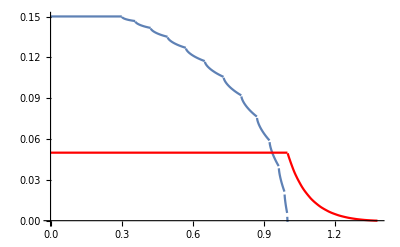

```mathematica
Show[{Plot[betaSolver[ϕtest,r ϕtest["rE"]],{r,0,1},PlotRange->All],
Plot[If[r>1,ϕtest["ϕ(r)"][r ϕtest["rE"]],ϕtest["ϕE"]],{r,0,1/ϕtest["rE"]},PlotStyle->Red]}]
```

#### solver for β

figure out how to translate this into Ncharge with actual units etc .

```mathematica
(*betaSolver[phiE_,RMaxList_,r_]:=
(*Use to solve for overall charge density in the Earth as a function of radius. Subscript[n, H] - Subscript[n, e] = Subscript[α, H]* β(r) * (Subscript[n, H]^F + Subscript[n, e]^F)*)
Module[{j = Length[RMaxList]},-Sum[rootF[i,RMaxList[[i,1]],r,phiE,j],{i,1,j}]];*)
```

```mathematica
Show[{Plot[betaSolver[ϕtest,r ϕtest["rE"]],{r,0,1},PlotRange->All],
Plot[If[r>1,ϕtest["ϕ(r)"][r ϕtest["rE"]],ϕtest["ϕE"]],{r,0,1/ϕtest["rE"]},PlotStyle->Red]}]
```

-Graphics-

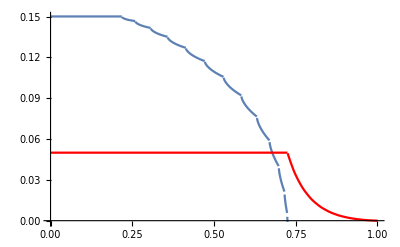

```mathematica
Show[{Plot[betaSolver[ϕtest,r],{r,0,ϕtest["rE"]},PlotRange->All],
Plot[If[r>ϕtest["rE"],ϕtest["ϕ(r)"][r],ϕtest["ϕE"]],{r,0,1},PlotStyle->Red]}]
```

```mathematica
"n_H - n_e = α_H* β(r) * (n_H^F + n_e^F)

α_H(n_H^F + n_e^F) = n_H^F
";
```

```mathematica
"Interesting! So a this corresponds to a 15% "
```

```mathematica
"GeV dark proton and light dark electron with 5% mass fraction of total DM"
Capture`naDM[0.05,"m"2 10^3/.SIConstRepl] m^-3
"Earth's volume is"
(4 π)/3("rE")^3 m^3/.EarthRepl
(*"So assuming the total captured number is given by the integral over the above"*)
(*Out[-4]Out[-2]*)
```

GeV dark proton and light dark electron with 5% mass fraction of total DM

14654.2/m^3

Earth's volume is

1.08321×10^21 m^3

```mathematica
"Assuming neutrality, the flowing number in the Earth is given by 2 times total number at infinity times the overdensity due to the escape velocity, we can ignore gravity for now and just take it to be two time aDM at infinity"
```

```mathematica
"So the value we want is"
(4 π)/3(∫_0)^rE ⅆr r^2 β(r)
```

So the value we want is

we'll need to interpolate over the beta solution

InterpolatingFunction[…]

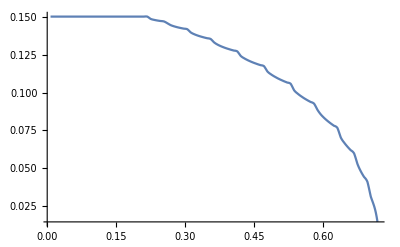

```mathematica
(*"we'll need to interpolate over the beta solution "
Table[{r,betaSolver[ϕtest,r]},{r,ϕtest["rE"]/#,ϕtest["rE"]-ϕtest["rE"]/#,ϕtest["rE"]/#}]&[100];
Interpolation[%]
Plot[%[r],{r,%["Domain"][[1,1]],%["Domain"][[1,2]]}]*)
```

InterpolatingFunction[…]

-Graphics-

2.90031×10^27 2^(5-logm) 5^(6-logm)

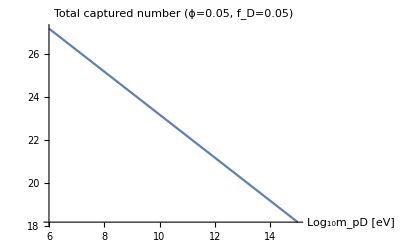

3.62539×10^23

```mathematica
βrfunctest = Getβrfunc[ϕtest,100]
Plot[βrfunctest[r],{r,βrfunctest["Domain"][[1,1]],βrfunctest["Domain"][[1,2]]}]
(Capture`naDM[0.05,"m"2 10^(logm-6)/.SIConstRepl] m^-3)(4 π(("rE")/(βrfunctest["Domain"][[1,2]]))^3 m^3/.Constants`EarthRepl)NIntegrate[r^2 βrfunctest[r],{r,βrfunctest["Domain"][[1,1]],βrfunctest["Domain"][[1,2]]}](*logm = 0 gives 1 MeV dark proton*)
Plot[Log10@%,{logm,6,15},PlotLabel->"Total captured number (ϕ=0.05, f_D=0.05)",AxesLabel->{"Log_10m_pD [eV]"}]
Out[-2]/.logm->Log10[4]+ 9
```

```mathematica
"We should turn this into a density / contour plot as a function of ϕ and m_pD"
"we'll want a to wrap the whole thing into a module too"
```

We should turn this into a density / contour plot as a function of ϕ and m_pD

we'll want a to wrap the whole thing into a module too

```mathematica
"Also, why is there no dependence on α_D? Ah because this assumes that the debeye length is 0, and that contains both the temperature in the mirror sector and α_D"
"There is however, temperature / v_0 dependence in the conversion of ϕ -> vesc as well"
```

Also, why is there no dependence on α_D? Ah because this assumes that the debeye length is 0, and that contains both the temperature in the mirror sector and α_D

There is however, temperature / v_0 dependence in the conversion of ϕ -> vesc as well

```mathematica
βrfunctest = Getβrfunc[ϕtest,100]
Plot[βrfunctest[r],{r,βrfunctest["Domain"][[1,1]],βrfunctest["Domain"][[1,2]]}]
(Capture`naDM[0.05,"m"2 10^(logm-6)/.SIConstRepl] m^-3)(4 π(("rE")/(βrfunctest["Domain"][[1,2]]))^3 m^3/.Constants`EarthRepl)NIntegrate[r^2 βrfunctest[r],{r,βrfunctest["Domain"][[1,1]],βrfunctest["Domain"][[1,2]]}](*logm = 0 gives 1 MeV dark proton*)
Plot[Log10@%,{logm,6,15},PlotLabel->"Total captured number (ϕ=0.05, f_D=0.05)",AxesLabel->{"Log_10m_pD [eV]"}]
Out[-2]/.logm->Log10[4]+ 9
```

InterpolatingFunction[…]

-Graphics-

2.90031×10^27 2^(5-logm) 5^(6-logm)

-Graphics-

3.62539×10^23

```mathematica
GetTotalCapturedNtemp[ϕDict_,mDMtot_:"m"2 10^(logm-6)/.SIConstRepl,fD_:0.05]:=Module[{n∞aDM,βofr,βdom},

n∞aDM=(Capture`naDM[fD,mDMtot] m^-3);

βofr = ϕDict["β(r)"];
βdom = βofr["Domain"];
n∞aDM(4 π(("rE")/βdom[[1,2]])^3 m^3/.Constants`EarthRepl)NIntegrate[r^2 βofr[r],{r,βdom[[1,1]],βdom[[1,2]]}]
]
```

```mathematica
GetTotalCapturedNtemp[ϕtest]
```

2.90031×10^27 2^(5-logm) 5^(6-logm)

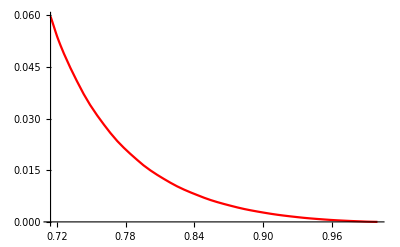

```mathematica
ϕdict = Block[{Print},Quiet@Screening`GetScreenedϕ[0.06]];
Plot[ϕdict["ϕ(r)"][x],{x,ϕdict["rE"],1},PlotStyle->Red]
```

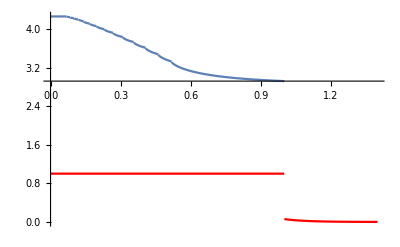

```mathematica
ϕdict = Block[{Print},Quiet@Screening`GetScreenedϕ[1]];
Show[{Plot[betaSolver[ϕdict,r ϕdict["rE"]],{r,0,1},PlotRange->All],
Plot[If[r>1,ϕdict["ϕ(r)"][r ϕdict["rE"]],ϕdict["ϕE"]],{r,0,1/ϕdict["rE"]},PlotStyle->Red]}]
```

```mathematica
"can we solve for beta even when the ϕ solution fails?"
```

```mathematica
ϕsolTable=Table[Block[{Print},Quiet@Screening`GetScreenedϕ[0.05 10^logϕ]],{logϕ, -5,0}];
```

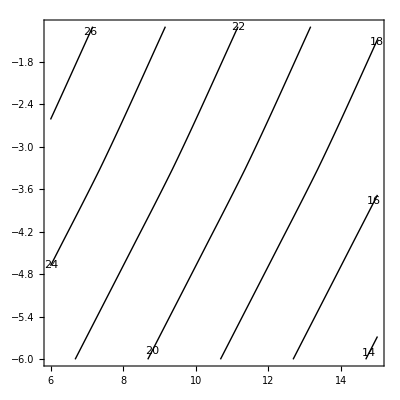

```mathematica
{Log10@#["ϕE"],Log10[ GetTotalCapturedN[#]/(2^(5-logm) 5^(6-logm))//Simplify]}&/@ϕsolTable;
Log10[2^(5-logm) 5^(6-logm)]+Interpolation[%][ϕE];
ContourPlot[%,{logm,6,15},{ϕE,-6,Log10[0.05]},ContourShading->None,ContourLabels->True,PlotRange->All]
```

#### Labeled plots of N_c and β

```mathematica
"ϕ(r)"/.ϕsolTable
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
?GetTotalCapturedN
```

```mathematica
("ϕ(r)"/.ϕsolTable[[2]])[0.9999]
```

5.16443×10^-7

```mathematica
Screening`GetTotalCapturedN[ϕsolTable[[2]]]
```

4.76206×10^23 2^(5-logm) 5^(6-logm)

```mathematica
ϕsolTable=Table[Block[{Print},Quiet@Screening`GetScreenedϕ[0.05 10^logϕ]],{logϕ, -5,0}];
```

```mathematica
Nfunctest=Log10[2^(5-logm) 5^(6-logm)]+Interpolation[{Log10@#["ϕE"],Log10[ GetTotalCapturedN[#]/(2^(5-"logm") 5^(6-"logm"))//Simplify]}&/@ϕsolTable][ϕE]
ContourPlot[Nfunctest,{logm,6,15},{ϕE,-6,Log10[0.05]},ContourShading->None,ContourLabels->True,PlotRange->All,PlotLabel->"N_cap",FrameLabel->{"Log_10m_p_D [eV]","Log_10(ϕ_E=(V_(EM, D))/(T_(D, ∞))) [ ]"}]
```

Log[2^(5-logm) 5^(6-logm)]/Log[10]+InterpolatingFunction[…][ϕE]

-Graphics-

InterpolatingFunction[…]

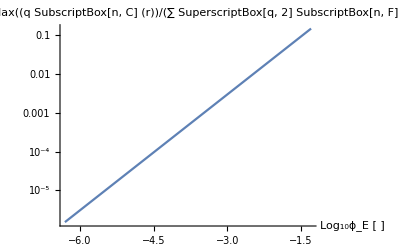

```mathematica
Interpolation[{Log10@#["ϕE"],Log10[ #["βmax"]]}&/@ϕsolTable]
LogPlot[10^(%[ϕE]),{ϕE,-6.3,-1.3},PlotLabel->"β_max = Max((q SubscriptBox[n, C] (r))/(∑ SuperscriptBox[q, 2] SubscriptBox[n, F] (r)))",AxesLabel->{"Log_10ϕ_E [ ]"}]
```

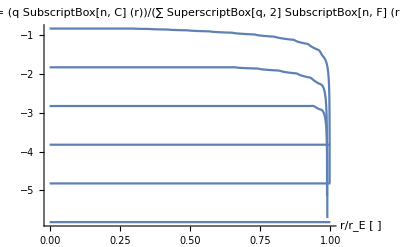

```mathematica
(*ϕsolTable=Table[Block[{Print},Quiet@Screening`GetScreenedϕ[0.05 10^logϕ]],{logϕ, -5,0}];*)
Quiet@Show[Table[Plot[Log10@ϕsolTable[[i]]["β(r)"][r ϕsolTable[[i]]["rE"] ],{r,0,1},PlotRange->All,PlotLabel->"β(r) = (q SubscriptBox[n, C] (r))/(∑ SuperscriptBox[q, 2] SubscriptBox[n, F] (r))",AxesLabel->{"r/r_E [ ]"}],{i,Length[ϕsolTable]}]]
```

```mathematica
Ncapofϕ[logm_,ϕE_]:=10^(22.0355+ ϕE+5-logm -Log[5]) (*Logm - Subscript[Log, 10] eV, ϕE - Subscript[Log, 10] ϕ(rE)*)
```

```mathematica
"The scaling of Ncap with ϕE is linear"
Nfunctest-Log[2^(5-logm) 5^(6-logm)]/Log[10]
LinearModelFit[Table[%,{ϕE,-6,Log10[0.05]}],{1,ϕEp},ϕEp];
%//Normal
%%["ParameterTable"]
```

The scaling of Ncap with ϕE is linear

InterpolatingFunction[…][ϕE]

22.0355+0.970255 ϕEp

| Estimate | Standard Error | t-Statistic | P-Value
1 | 22.0355 | 0.0416831 | 528.644 | 1.49271×10^-8
ϕEp | 0.970255 | 0.0125679 | 77.2008 | 4.79008×10^-6

```mathematica
10^22
```

```mathematica
10^(Nfunctest-Log[2^(5-logm) 5^(6-logm)]/Log[10])
Plot[%/.ϕE->Log10[ϕt],{ϕt,0.001,1}]
```

10^(InterpolatingFunction[…][ϕE])

-Graphics-

```mathematica
Nfunctest/.ϕE->-6.3
```

22.6788+Log[2^(5-logm) 5^(6-logm)]/Log[10]

```mathematica
Log[2^(5-logm) 5^(6-logm)]/Log[10]
```

Log[2^(5-logm) 5^(6-logm)]/Log[10]

#### v0 to vesc

Given a value of v0 and ϕ we want the corresponding vesc.

```mathematica
"We know"
(*(√3)/2*){"veDmean","vpDmean"}/.v0toβD[220 kmpers,meD,2000meD]//PowerExpand//Simplify//N
(%^-1 .%^-1)//PowerExpand//Simplify
√(2(("veDmean")^-2+("vpDmean")^-2)^-1)/.v0toβD[220 kmpers,meD,2000meD]//PowerExpand//Simplify//N
```

We know

{6958.75 kmpers,155.602 kmpers}

0.0000413223/kmpers^2

220. kmpers

```mathematica
Block[{βD,vpDmean,veDmean},
βD = 6/((meD + mpD)v0^2);
vpDmean = Sqrt[3/(mpD βD)];
veDmean = Sqrt[3/(meD βD)];
√(2(vpDmean^-2+veDmean^-2)^-1)//Simplify//PowerExpand
]
```

v0

```mathematica
Block[{ϕ,vesc,v0,q},
v0 = 220 kmpers;
ϕ = (-3 vesc^2)/(2 q v0^2);
Solve[ϕ==ϕE,vesc][[2]]/.ϕE->0.05
]
```

{vesc→(0.+40.1663 ⅈ) kmpers √q}

I think Start by doing a run with ϕE = 0.05, the boundary of the strong capture regime. 

Also I think for the capture code all we need is the potential at the earth. Once we have that

```mathematica
Block[{ϕE,vesc,v0,,v0s,q},
v0 = 220 kmpers;
(*ϕ = (-3 vesc^2)/(2 q "veDmean");*)
ϕE = 0.05;

v0s ={{"veDmean",-1},{"vpDmean",1}}/. v0toβD[v0,meD/.meD->mpD 10^-4,mpD]//PowerExpand;

Print[N@((("vesc")/10^3)^2)/.EarthRepl];
vescsq = -2/3#2ϕE #1^2 &[Sequence@@#]&/@v0s
(*Solve[ϕ==ϕE,vesc][[2]]/.ϕE->0.05*)
]
```

125.44

{8.06747×10^6 kmpers^2,-806.747 kmpers^2}

```mathematica
#1 #2&[Sequence@@#]&/@{{a,d},{b,c}}
```

{a d,b c}

#### maximum ϕE

```mathematica
"Solve for the maximum ϕE such that the escape velocity is real for qD > 0"
Solve[0==1/2 vescg^2+ -2/3 qD ϕE vbar^2,ϕE][[1]]
"We can restrict ϕE < the above (at least for now) so that vesc is real"
ϕE/.%%/.vescg->("vesc"/.EarthRepl)/.qD->1/.vbar -> 220 10^3//N
ϕE/.%%%/.vescg->("vesc"/.EarthRepl)/.qD->1/.vbar -> 20 10^3//N
(*vescg^2+ -2/3 qD ϕE vbar^2/.vescg->("vesc"/.EarthRepl)/.qD->1/.vbar -> 220 10^3/.ϕE->0.003887603305785124//N
vescg^2+ -2/3 qD ϕE vbar^2/.vescg->("vesc"/.EarthRepl)/.qD->1/.vbar -> 20 10^3/.ϕE->0.4704//N*)
```

Solve for the maximum ϕE such that the escape velocity is real for qD > 0

{ϕE→(3 vescg^2)/(4 qD vbar^2)}

We can restrict ϕE < the above (at least for now) so that vesc is real

0.0019438

0.2352

```mathematica
Veff["rE"/.EarthRepl,ϕE,qD,vbar]
```

-6.272×10^7+2/3 qD vbar^2 ϕE

#### Comparing extrema of 1D effective potential to the potential at Earth

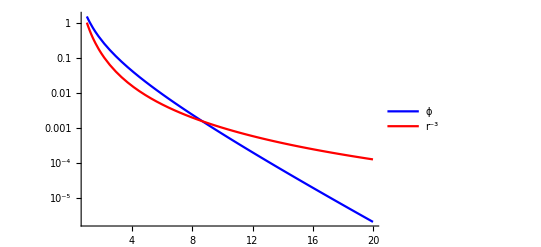

```mathematica
(*L^2/m/.repl
r^3 Abs@D[q ϕ[r],r]/.repl/.r->1//N*)
Legended[LogPlot[(*Abs[q ϕ[r]]/.repl*){Abs[q ϕ'[r]]/.repl,r^-3},{r,1,10 λ/.repl},PlotRange->All,PlotStyle->{Blue,Red}],LineLegend[{Blue,Red},{"ϕ","r^-3"}]]
```

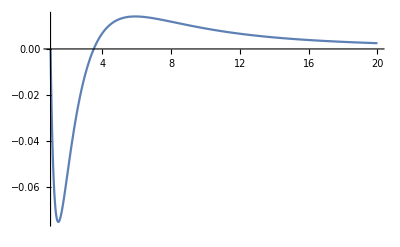

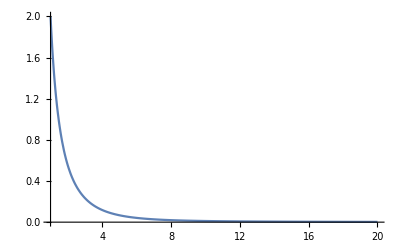

```mathematica
repl={ϕE->1,L->1,m->1/2,rE->1,λ->2,q->-1};
ϕ[r_]:=ϕE (rE E^(-(r-rE)/λ))/r
Veff[r_]:=L^2/(2 m r^2)+q ϕ[r]
Plot[Veff[r]/.repl,{r,1,10 λ/.repl},PlotRange->All]
Plot[Veff[r]/.q->1/.repl,{r,1,10 λ/.repl},PlotRange->All]
```

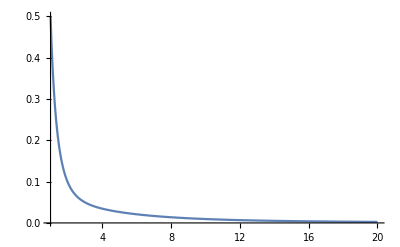

```mathematica
repl={ϕE->1/2,L->1,m->1/2,rE->1,λ->2,q->-1};
ϕ[r_]:=ϕE (rE E^(-(r-rE)/λ))/r
Veff[r_]:=L^2/(2 m r^2)+q ϕ[r]
Plot[Veff[r]/.repl,{r,1,10 λ/.repl},PlotRange->All]
```

```mathematica
Veff[1]/.repl
ϕ[1]/.repl
```

0.125

1

```mathematica
Veff'[1]
```

1/2

```mathematica
Solve[Veff'[r]==0,r]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-L^2/(m r^3)-(ⅇ^(-(r-rE)/λ) q ϕE)/r^2-(ⅇ^(-(r-rE)/λ) q ϕE)/(r λ)==0,r]

```mathematica
D[q ϕ[r],r]
```

-(ⅇ^(-(r-rE)/λ) q ϕE)/r^2-(ⅇ^(-(r-rE)/λ) q ϕE)/(r λ)

```mathematica
"Potential for a monotonically decreasing in r, and strictly negative electrostatic potential ϕ with ϕ(r_E)= ϕ_E and q<0 (q below denotes |q|)"
potmonom=L^2/(2 m r^2)-q ϕE(rE/r)^n
"Now look for extrema"
D[potmonom,r]
%r^3//Simplify
Solve[%==0,r]
"So the value of the potential at the extremum is"
potmonomatrsol=potmonom/.%%[[1]]//Simplify//PowerExpand//FullSimplify//PowerExpand
"Which implies this value is greater than "
(potmonomatrsol/(q ϕE^(-2/(-2+n))))^(1/(n/(-2+n)))//Simplify//PowerExpand
(*ϕextr=Solve[%==ϕE,ϕE]//Simplify
potmonom/.ϕextr[[1]]//Simplify
%//PowerExpand//Simplify*)
```

Potential for a monotonically decreasing in r, and strictly negative electrostatic potential ϕ with ϕ(r_E)= ϕ_E and q<0 (q below denotes |q|)

L^2/(2 m r^2)-q (rE/r)^n ϕE

Now look for extrema

-L^2/(m r^3)+(n q rE (rE/r)^(-1+n) ϕE)/r^2

-L^2/m+n q r^2 (rE/r)^n ϕE

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→((L^2 rE^-n)/(m n q ϕE))^(1/(2-n))}}

So the value of the potential at the extremum is

1/2 L^((2 n)/(-2+n)) m^(-n/(-2+n)) (n^(-2/(-2+n))-2 n^(-n/(-2+n))) q^(-2/(-2+n)) rE^(-(2 n)/(-2+n)) ϕE^(-2/(-2+n))

Which implies this value is greater than

(2^(-1+2/n) L^2 (n^(-2/(-2+n))-2 n^(-n/(-2+n)))^((-2+n)/n))/(m q rE^2)

```mathematica
(potmonom/.r->rE)/.q->1/.repl
```

-1/2

1/2 ⅇ^(2 Re[(n Log[L])/(-2+n)]+Re[(n Log[m])/(2-n)]-2 (Re[Log[q]/(-2+n)]+Re[(n Log[rE])/(-2+n)]+Re[Log[ϕE]/(-2+n)])) Abs[n^(-2/(-2+n))-2 n^(-n/(-2+n))]-Abs[L^2/(2 m rE^2)-q ϕE]

-1/2+1/2 Abs[n^(-2/(-2+n))-2 n^(-n/(-2+n))]

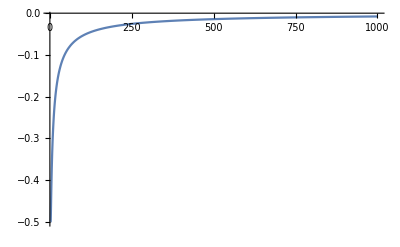

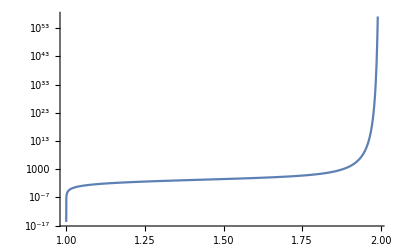

```mathematica
Abs@potmonomatrsol-Abs@(potmonom/.r->rE)//Simplify
%/.q->1/.repl
Plot[%,{n,2.01,1000},PlotRange->All]
LogPlot[%%,{n,1,1.99},PlotRange->All]
```

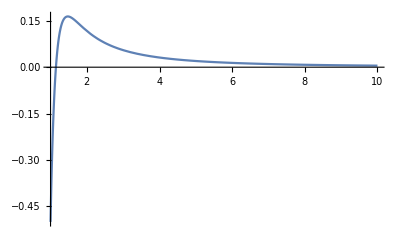

```mathematica
Plot[potmonom/.q->1/.repl/.n->7,{r,1,10},PlotRange->All]
```

```mathematica
D[(n^(-2/(-2+n))-2 n^(-n/(-2+n))),n]//Simplify
"So increases with n if n>2 otherwise decreases"
```

(2 n^(n/(2-n)) Log[n])/(-2+n)

So increases with n if n>2 otherwise decreases

{1/r^3,-1/r^4,-1/r^4+1/r^3}

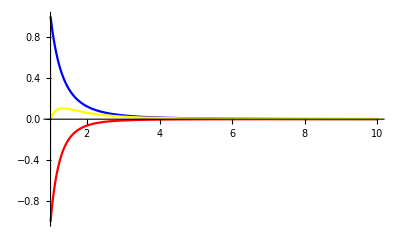

{1,-1,0}

```mathematica
{1/r^3,-1/r^n/.n->4,1/r^3-1/r^n/.n->4}
Plot[%,{r,1,10},PlotStyle->{Blue,Red,Yellow},PlotRange->All]
%%/.r->1
```

Both the ang term and the ϕ term have absolute values which are montonically decreasing in r. And since they have opposite signs

They

### consistent scheme to get ϕ_esc

#### Solving for aDM distribution in the Earth using floating DM with known BC at Earth’s surface

```mathematica
(D[Logn[r],r]+ (κ+1)D[Log[T[r]],r]/.{κ->-1/(2 (1+mχbymsm)^(3/2)),T->Function[{r},A r]})==0
```

(1-1/(2 (1+mχbymsm)^(3/2)))/r+Logn'[r]==0

```mathematica
DSolve[D[Logn[r],r]+ (κ+1)D[Log[T[r]],r](*+(mχ g[r])/T[r]*)==0/.{κ->-1/(2 (1+mχbymsm)^(3/2))(*,T->Function[{r},TS (r-rS)+TC(*A/(1+E^(a (r+c)))*)(*+B*)]*)}(*/.mχbymsm->10^-2*),Logn,r]
E^Logn[r]/.%[[1]]//FullSimplify
Solve[(%/.r->rE)==NS,C[1]][[1]]/.C[2]->0
%%/.%[[1]]
nofr=%/.NS->n∞ E^(-q ϕesc)
"Then we just need to solve the following"
NCap[ϕesc] ==Integrate[4 π r^2 nofr,{r,0,rE}]
"Or equivalently"
E^(q ϕesc)NCap[ϕesc] ==Integrate[4 π r^2 nofr/.ϕesc->0,{r,0,rE}]
"And from above, we know that there is some mass dependence to Ncap, but that the variation with ϕE is roughly linear so that:"
E^(q ϕesc)Nbyϕesc ϕesc ==Integrate[4 π r^2 nofr/.ϕesc->0,{r,0,rE}]
"We define the RHS to be IofT then we can solve this analytically:"
Solve[E^(q ϕesc)Nbyϕesc ϕesc == IofT,ϕesc]
"Which then gives the analytic expression for Ncap"
Ncap==Nbyϕesc ϕesc/.%%[[1]]
IofT== Integrate[4 π r^2 nofr/.ϕesc->0,{r,0,rE}]
```

{{Logn→Function[{r},C[1]+1/2 (-2+1/(1+mχbymsm)^(3/2)) Log[T[r]]]}}

ⅇ^C[1] T[r]^(-1+1/(2 (1+mχbymsm)^(3/2)))

{C[1]→Log[NS T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))]}

NS T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))

ⅇ^(-q ϕesc) n∞ T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))

Then we just need to solve the following

NCap[ϕesc]==∫_0^rE 4 ⅇ^(-q ϕesc) n∞ π r^2 T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))ⅆr

Or equivalently

ⅇ^(q ϕesc) NCap[ϕesc]==∫_0^rE 4 n∞ π r^2 T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))ⅆr

And from above, we know that there is some mass dependence to Ncap, but that the variation with ϕE is roughly linear so that:

ⅇ^(q ϕesc) Nbyϕesc ϕesc==∫_0^rE 4 n∞ π r^2 T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))ⅆr

We define the RHS to be IofT then we can solve this analytically:

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕesc→ProductLog[(IofT q)/Nbyϕesc]/q}}

Which then gives the analytic expression for Ncap

2^(27-logm) 5^(28-logm) ProductLog[2^(-27+logm) 5^(-28+logm) (4/3 n∞ π rC^3 (TC/TS)^(-1+1/(2 (1+mχbymsm)^(3/2)))-4/3 n∞ π (rC^3-rE^3) (TM/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))))]==(Nbyϕesc ProductLog[(IofT q)/Nbyϕesc])/q

IofT==∫_0^rE 4 n∞ π r^2 T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))ⅆr

```mathematica
IofTtest=n∞ (Integrate[4  π r^2 (TM/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))) ,{r,rC,rE}]+Integrate[4 π r^2 (TC/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))) ,{r,0,rC}])//Simplify
Nbyϕesctest = 10^22 10^(Log[2^(5-logm) 5^(6-logm)]/Log[10])
```

n∞ (4/3 π rC^3 (TC/TS)^(-1+1/(2 (1+mχbymsm)^(3/2)))-4/3 π (rC^3-rE^3) (TM/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))))

2^(27-logm) 5^(28-logm)

```mathematica
Ncapandϕesc={Nbyϕesctest//N,Nbyϕesctest ProductLog[IofTtest/Nbyϕesctest],ProductLog[IofTtest/Nbyϕesctest],√(2/3 v0^2 ProductLog[IofTtest/Nbyϕesctest])}//Simplify//PowerExpand;
%/.{rC->3.4 10^6 m,rE->6.4 10^6 m}/.{TS->293 k,TM -> 2623 k, TC->5470 k};
%/.n∞->Capture`naDM[0.05,"m"2 10^(logm-6)/.SIConstRepl] m^-3//Simplify
%/.mχbymsm->10^(logm-10)/.logm->10
"the value of Ncap seems reasonable (albeit much smaller, but okay they were conservative in the appendix), but the value of ϕE does not. It is about 100 times larger than it should be expected. "
```

{5.×10^27 ⅇ^(-2.30259 logm),2^(27-logm) 5^(28-logm) ProductLog[305593. (2623/293)^(1/(2 (1+mχbymsm)^(3/2)))+25846.3 (5470/293)^(1/(2 (1+mχbymsm)^(3/2)))],ProductLog[305593. (2623/293)^(1/(2 (1+mχbymsm)^(3/2)))+25846.3 (5470/293)^(1/(2 (1+mχbymsm)^(3/2)))],√(2/3) v0 √ProductLog[305593. (2623/293)^(1/(2 (1+mχbymsm)^(3/2)))+25846.3 (5470/293)^(1/(2 (1+mχbymsm)^(3/2)))]}

{5.×10^17,5.36793×10^18,10.7359,2.6753 v0}

the value of Ncap seems reasonable (albeit much smaller, but okay they were conservative in the appendix), but the value of ϕE does not. It is about 100 times larger than it should be expected.

#### Corrected analytic captured charge

```mathematica
"Nofr is the total DM accumulated (charged or not) Ie. it is |α_pD|+|α_eD|+β"
"so we know that n(r) = 2 n_∞ E^(-q ϕE) (|α_pD|+|α_eD|+β) == 2 n_∞ E^(-q ϕE)+ n_C"
nofr
```

Nofr is the total DM accumulated (charged or not) Ie. it is |α_pD|+|α_eD|+β

so we know that n(r) = 2 n_∞ E^(-q ϕE) (|α_pD|+|α_eD|+β) == 2 n_∞ E^(-q ϕE)+ n_C

ⅇ^(-q ϕesc) n∞ T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))

```mathematica
DSolve[D[Logn[r],r]+ (κ+1)D[Log[T[r]],r](*+(mχ g[r])/T[r]*)==0/.{κ->-1/(2 (1+mχbymsm)^(3/2))(*,T->Function[{r},TS (r-rS)+TC(*A/(1+E^(a (r+c)))*)(*+B*)]*)}(*/.mχbymsm->10^-2*),Logn,r]
E^Logn[r]/.%[[1]]//FullSimplify
Solve[(%/.r->rE)==NS,C[1]][[1]]/.C[2]->0
%%/.%[[1]]
nofr=%/.NS->2 n∞ E^(-q ϕesc)+ Subscript[n, C]
"Then we just need to solve the following"
NCap[ϕesc]==Integrate[4 π r^2(nofr- 2 Subscript[n, ∞] E^(-q ϕesc)),{r,0,rE}]
"Or equivalently"
E^(q ϕesc)NCap[ϕesc] ==Integrate[4 π r^2(nofr- 2 Subscript[n, ∞] E^(-q ϕesc))/.ϕesc->0,{r,0,rE}]
"And from above, we know that there is some mass dependence to Ncap, but that the variation with ϕE is roughly linear so that:"
E^(q ϕesc)Nbyϕesc ϕesc ==Integrate[4 π r^2(nofr- 2 Subscript[n, ∞] E^(-q ϕesc))/.ϕesc->0,{r,0,rE}]
"We define the RHS to be IofT then we can solve this analytically:"
Solve[E^(q ϕesc)Nbyϕesc ϕesc == IofT,ϕesc]
"Which then gives the analytic expression for Ncap"
Ncap==Nbyϕesc ϕesc/.%%[[1]]
IofT== Integrate[4 π r^2(nofr- 2 Subscript[n, ∞] E^(-q ϕesc))/.ϕesc->0,{r,0,rE}]
```

{{Logn→Function[{r},C[1]+1/2 (-2+1/(1+mχbymsm)^(3/2)) Log[T[r]]]}}

ⅇ^C[1] T[r]^(-1+1/(2 (1+mχbymsm)^(3/2)))

{C[1]→Log[NS T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))]}

NS T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))

(2 ⅇ^(-q ϕesc) n∞+n_C) T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))

Then we just need to solve the following

NCap[ϕesc]==∫_0^rE 4 π r^2 (-2 ⅇ^(-q ϕesc) n_∞+(2 ⅇ^(-q ϕesc) n∞+n_C) T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2))))ⅆr

Or equivalently

ⅇ^(q ϕesc) NCap[ϕesc]==∫_0^rE 4 π r^2 (-2 n_∞+(2 n∞+n_C) T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2))))ⅆr

And from above, we know that there is some mass dependence to Ncap, but that the variation with ϕE is roughly linear so that:

ⅇ^(q ϕesc) Nbyϕesc ϕesc==∫_0^rE 4 π r^2 (-2 n_∞+(2 n∞+n_C) T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2))))ⅆr

We define the RHS to be IofT then we can solve this analytically:

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕesc→ProductLog[(IofT q)/Nbyϕesc]/q}}

Which then gives the analytic expression for Ncap

2^(27-logm) 5^(28-logm) ProductLog[2^(-27+logm) 5^(-28+logm) (4/3 n∞ π rC^3 (TC/TS)^(-1+1/(2 (1+mχbymsm)^(3/2)))-4/3 n∞ π (rC^3-rE^3) (TM/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))))]==(Nbyϕesc ProductLog[(IofT q)/Nbyϕesc])/q

IofT==∫_0^rE 4 π r^2 (-2 n_∞+(2 n∞+n_C) T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2))))ⅆr

```mathematica
Constants`EarthRepl
```

<|rE→6.371×10^6,ME→5.97×10^24,vesc→11200,rcore→3.486×10^6,Tcrust→2623,Tcore→5470,βcrust→βcrust,βcore→βcore,SiO2Frac→0.447,MgOFrac→0.387|>

```mathematica
(*IofTtest=Integrate[4 n∞ π r^2 (T[r]/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))) /.T->Function[{r},10 TS+6 TS Boole[r<1/2 rE]],{r,0,rE}]*)
IofTtest=n∞ (Integrate[4  π r^2 (TM/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))) ,{r,rC,rE}]+Integrate[4 π r^2 (TC/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))) ,{r,0,rC}]-4 Integrate[4 π r^2  ,{r,0,rE}])//Simplify
Nbyϕesctest = 10^22 10^(Log[2^(5-logm) 5^(6-logm)]/Log[10])
```

4/3 n∞ π (-4 rE^3+rC^3 (TC/TS)^(-1+1/(2 (1+mχbymsm)^(3/2)))+(-rC^3+rE^3) (TM/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))))

2^(27-logm) 5^(28-logm)

```mathematica
IofTtest/Nbyϕesctest/.{rC->3.4 10^6 m,rE->6.4 10^6 m}/.{TS->293 k,TM -> 2623 k, TC->5470 k}/.n∞->Capture`naDM[0.05,"m"2 10^(logm-6)/.SIConstRepl] m^-3/.mχbymsm->10^(logm-10)/.logm->10//N
```

-1.23795×10^7

```mathematica
(Capture`naDM[0.05,"m"2 10^(logm-6)/.SIConstRepl])/Nbyϕesctest m^-3/.mχbymsm->10^(logm-10)/.logm->10
```

(2.93085×10^-15)/m^3

```mathematica
5/Nbyϕesctest(Integrate[4  π r^2 (TM/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))) ,{r,rC,rE}]+Integrate[4  π r^2 (TC/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))) ,{r,0,rC}])/.{rC->3.4 10^6 m,rE->6.4 10^6 m}/.{TS->293 k,TM -> 2623 k, TC->5470 k}/.mχbymsm->10^(logm-10)//Simplify//Expand
```

9.3343×10^20 (293/2623)^(1-1/(2 (1+10^(-10+logm))^(3/2))) 10^(-27+logm) m^3+1.64636×10^20 (293/547)^(1-1/(2 (1+10^(-10+logm))^(3/2))) 10^(-28+1/(2 (1+10^(-10+logm))^(3/2))+logm) m^3

```mathematica
2^(27-logm) 5^(28-logm) 1/5
```

10^(27-logm)

```mathematica
Ncapandϕesc={Nbyϕesctest//N,Nbyϕesctest ProductLog[IofTtest/Nbyϕesctest],ProductLog[IofTtest/Nbyϕesctest],√(2/3 v0^2 ProductLog[IofTtest/Nbyϕesctest])}//Simplify//PowerExpand;
%/.{rC->3.4 10^6 m,rE->6.4 10^6 m}/.{TS->293 k,TM -> 2623 k, TC->5470 k}
%/.n∞->Capture`naDM[0.05,"m"2 10^(logm-6)/.SIConstRepl] m^-3/.mχbymsm->10^(logm-10)/.logm->-5
"the value of Ncap seems reasonable (albeit much smaller, but okay they were conservative in the appendix), but the value of ϕE does not. It is about 100 times larger than it should be expected. "
```

{5.×10^27 ⅇ^(-2.30259 logm),2^(27-logm) 5^(28-logm) ProductLog[1/3 2^(-25+logm) 5^(-28+logm) (-1.04858×10^21 m^3+3.9304×10^19 (293/5470)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3+2.2284×10^20 (293/2623)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3) n∞ π],ProductLog[1/3 2^(-25+logm) 5^(-28+logm) (-1.04858×10^21 m^3+3.9304×10^19 (293/5470)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3+2.2284×10^20 (293/2623)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3) n∞ π],√(2/3) v0 √ProductLog[1/3 2^(-25+logm) 5^(-28+logm) (-1.04858×10^21 m^3+3.9304×10^19 (293/5470)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3+2.2284×10^20 (293/2623)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3) n∞ π]}

{5.×10^32,6.82562×10^33+1.46508×10^33 ⅈ,13.6512+2.93016 ⅈ,(3.03389+0.321937 ⅈ) v0}

the value of Ncap seems reasonable (albeit much smaller, but okay they were conservative in the appendix), but the value of ϕE does not. It is about 100 times larger than it should be expected.

This is

```mathematica
2^(-27+logm) 5^(-28+logm) (1.646362102089243*^20 (293/5470)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3 n∞+9.334300092345993*^20 (293/2623)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3 n∞)/.n∞->Capture`naDM[0.05,"m"2 10^(logm-6)/.SIConstRepl] m^-3/.mχbymsm->10^(logm-9)/.logm->6
```

1.02427×10^6

```mathematica
Series[ProductLog[x],{x,∞,1}]//Normal//Expand
Series[ProductLog[x],{x,0,1}]//Normal//Expand
```

Log[x]-Log[Log[x]]+Log[Log[x]]/Log[x]^3-Log[Log[x]]/Log[x]^2+Log[Log[x]]/Log[x]-(3 Log[Log[x]]^2)/(2 Log[x]^3)+Log[Log[x]]^2/(2 Log[x]^2)+Log[Log[x]]^3/(3 Log[x]^3)

```mathematica
Table[{x,ProductLog[10^x]//N},{x,-5,11}]
```

{{-5,9.9999×10^-6},{-4,0.00009999},{-3,0.000999001},{-2,0.00990147},{-1,0.0912765},{0,0.567143},{1,1.74553},{2,3.38563},{3,5.2496},{4,7.23185},{5,9.28457},{6,11.3834},{7,13.5143},{8,15.669},{9,17.8417},{10,20.0287},{11,22.2271}}

```mathematica
Ncapandϕesc={Nbyϕesctest//N,Nbyϕesctest ProductLog[IofTtest/Nbyϕesctest],ProductLog[IofTtest/Nbyϕesctest],√(2/3 v0^2 ProductLog[IofTtest/Nbyϕesctest])}//Simplify//PowerExpand;
%/.{rC->3.4 10^6 m,rE->6.4 10^6 m}/.{TS->293 k,TM -> 2623 k, TC->5470 k};
%/.n∞->Capture`naDM[0.05,"m"2 10^(logm-6)/.SIConstRepl] m^-3//Simplify
%/.mχbymsm->10^(logm-10)/.logm->10
"the value of Ncap seems reasonable (albeit much smaller, but okay they were conservative in the appendix), but the value of ϕE does not. It is about 100 times larger than it should be expected. "
"It's because both N(ϕesc) and N_cap are linear in n_∞"
```

{5.×10^27 ⅇ^(-2.30259 logm),2^(27-logm) 5^(28-logm) ProductLog[305593. (2623/293)^(1/(2 (1+mχbymsm)^(3/2)))+25846.3 (5470/293)^(1/(2 (1+mχbymsm)^(3/2)))],ProductLog[305593. (2623/293)^(1/(2 (1+mχbymsm)^(3/2)))+25846.3 (5470/293)^(1/(2 (1+mχbymsm)^(3/2)))],√(2/3) v0 √ProductLog[305593. (2623/293)^(1/(2 (1+mχbymsm)^(3/2)))+25846.3 (5470/293)^(1/(2 (1+mχbymsm)^(3/2)))]}

{5.×10^17,5.36793×10^18,10.7359,2.6753 v0}

the value of Ncap seems reasonable (albeit much smaller, but okay they were conservative in the appendix), but the value of ϕE does not. It is about 100 times larger than it should be expected.

It's because both N(ϕesc) and N_cap are linear in n_∞

#### Captured charge from flat potential with Gravity condition

```mathematica
nC == (m G ρ)/(q "e"√(αD/α)) (*up to constants *)
Ncaped == (m  "G""ME")/(q "e"√(αD/α)) (*up to constants *)
ϕE Ncapofϕ[logm,0]/.m->"m"2 10^(logm - 6)/.q->1/.SIConstRepl/.EarthRepl/.logm->10//Simplify
(m  "G""ME")/(q "e"√(αD/α))/.m->"m"2 10^(logm - 6)/.q->1/.SIConstRepl/.EarthRepl/.logm->10//Simplify
Solve[%==%%,ϕE][[1]]
```

nC==(G m ρ)/(e q √(αD/α))

Ncaped==(G ME m)/(e q √(αD/α))

2.66724×10^15 ϕE

(4.52632×10^7)/(√(αD/α))

{ϕE→(1.69701×10^-8)/(√(αD/α))}

```mathematica
Integrate[-(("rE"("vesc")^2/2)/(2("rE")^3))( 3("rE")^2-r^2),{r,0,rE}]/.rE->"rE"
%/.EarthRepl
```

-(2 rE vesc^2)/3

-5.32785×10^14

```mathematica
DSolve[D[Logn[r],r]+ (κ+1)D[Log[T[r]],r](*+(mχ g[r])/T[r]*)==0/.{κ->(*-1/(2 (1+mχbymsm)^(3/2))*)-1(*,T->Function[{r},TS (r-rS)+TC(*A/(1+E^(a (r+c)))*)(*+B*)]*)}(*/.mχbymsm->10^-2*),Logn,r]
E^Logn[r]/.%[[1]]//FullSimplify
Solve[(%/.r->rE)==NS,C[1]][[1]]/.C[2]->0
%%/.%[[1]]
nofr=%/.NS->n∞ E^(-q ϕesc)
"Then we just need to solve the following"
NCap[ϕesc] ==Integrate[4 π r^2 nofr,{r,0,rE}]
```

{{Logn→Function[{r},C[1]]}}

ⅇ^C[1]

{C[1]→Log[NS]}

NS

ⅇ^(-q ϕesc) n∞

Then we just need to solve the following

NCap[ϕesc]==4/3 ⅇ^(-q ϕesc) n∞ π rE^3

```mathematica
DSolve[D[n[r],r]==n[r] f[r],n,r]
```

{{n→Function[{r},ⅇ^(f[K[1]]K[1]1r) C[1]]}}

```mathematica
DSolve[1/r^2 D[r^2 ϕ'[r],{r}]==ρ[r],ϕ,r]//Simplify
```

{{ϕ→Function[{r},C[2]+(C[1]/K[2]^2+(K[1]^2 ρ[K[1]]K[1]1K[2])/K[2]^2)K[2]1r]}}

```mathematica
DSolve[1/r^2 D[r^2 ϕ'[r],{r}]==Sinh@ϕ[r],ϕ,r]//Simplify
```

DSolve[Sinh[ϕ[r]]==(2 ϕ'[r])/r+ϕ''[r],ϕ,r]

```mathematica
"In the absence of gravity, at leading order in ϕ"
DSolve[-1/r^2 D[r^2 δϕ'[r],{r}]==f[r]-(nF) δϕ[r],δϕ,r][[1]]//Simplify
δϕ[r]/.%/.C[2]->2 √nF C[2]//Simplify//PowerExpand
(δϕ[r]/.%%)/.Solve[(%/.r->rE)==NS,C[1]]//Simplify//Expand
(*D[%[[1]],r]//Simplify*)
%/.f->Function[{r},0]//Simplify//Evaluate
```

In the absence of gravity, at leading order in ϕ

{δϕ→Function[{r},(ⅇ^(-√nF r) C[1])/r+(ⅇ^(√nF r) C[2])/(2 √nF r)+(ⅇ^(-√nF r) (2 √nF (ⅇ^(√nF K[1]) f[K[1]] K[1])/(2 √nF)K[1]1r+ⅇ^(2 √nF r) -ⅇ^(-√nF K[2]) f[K[2]] K[2]K[2]1r))/(2 √nF r)]}

(ⅇ^(-√nF r) (2 (C[1]+ⅇ^(2 √nF r) C[2])+2 (ⅇ^(√nF K[1]) f[K[1]] K[1])/(2 √nF)K[1]1r+(ⅇ^(2 √nF r) -ⅇ^(-√nF K[2]) f[K[2]] K[2]K[2]1r)/(√nF)))/(2 r)

{(ⅇ^(-√nF r+√nF rE) NS rE)/r-(ⅇ^(-√nF r+2 √nF rE) C[2])/r+(ⅇ^(√nF r) C[2])/(2 √nF r)+(ⅇ^(-√nF r) (ⅇ^(√nF K[1]) f[K[1]] K[1])/(2 √nF)K[1]1r)/r-(ⅇ^(-√nF r) (ⅇ^(√nF K[1]) f[K[1]] K[1])/(2 √nF)K[1]1rE)/r+(ⅇ^(√nF r) -ⅇ^(-√nF K[2]) f[K[2]] K[2]K[2]1r)/(2 √nF r)-(ⅇ^(-√nF r+2 √nF rE) -ⅇ^(-√nF K[2]) f[K[2]] K[2]K[2]1rE)/(2 √nF r)}

{1/(2 √nF r)ⅇ^(-√nF r) (2 ⅇ^(√nF rE) √nF NS rE+ⅇ^(2 √nF r) C[2]-2 ⅇ^(2 √nF rE) √nF C[2]+2 √nF 0K[1]1r-2 √nF 0K[1]1rE+ⅇ^(2 √nF r) 0K[2]1r-ⅇ^(2 √nF rE) 0K[2]1rE)}

In the absence of gravity, at leading order in ϕ

{δϕ→Function[{r},(ⅇ^(-√nF r √β) C[1])/r+(ⅇ^(√nF r √β) C[2])/(2 √nF r √β)]}

(ⅇ^(-√nF r √β) (C[1]+ⅇ^(2 √nF r √β) C[2]))/r

(-C[1]-C[2])/r^2+1/2 (nF β C[1]+nF β C[2])+O[r]^1

{{C[1]→-C[2]}}

((Cosh[√nF r √β]-Sinh[√nF r √β]) (-C[2]+C[2] Cosh[2 √nF r √β]+C[2] Sinh[2 √nF r √β]))/r

{C[2]→(rE (ϕE+mp ϕgE))/((Cosh[√nF rE √β]-Sinh[√nF rE √β]) (-1+Cosh[2 √nF rE √β]+Sinh[2 √nF rE √β]))}

(rE (ϕE+mp ϕgE) Csch[√nF rE √β] Sinh[√nF r √β])/r

This gives the homogeneous solution which satisfies the boundary conditions (value at surface + no cusp)

(7.44015×10^-45 Sinh[100. r])/r

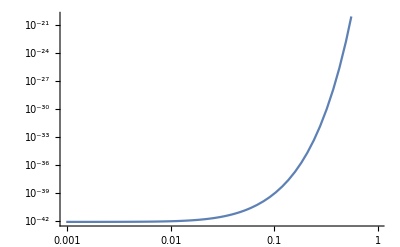

This gives the homogeneous solution which satisfies the boundary conditions (value at surface + no cusp)

```mathematica
"In the absence of gravity, at leading order in ϕ"
DSolve[-1/r^2 D[r^2 δϕ'[r],{r}]==f[r]-(nF β) δϕ[r]/.f->Function[{r},0],δϕ,r][[1]]//Simplify
δϕ[r]/.%/.C[2]->2 √(β nF) C[2]//Simplify//PowerExpand
Series[D[%,r],{r,0,0}]
Solve[Normal@% == 0,C[1]]
%%%/.%[[1]]//ExpToTrig
Solve[(%/.r->rE)==ϕE+mp ϕgE,C[2]][[1]]
ϕin = %%/.%//Simplify
"This gives the homogeneous solution which satisfies the boundary conditions (value at surface + no cusp)"
%%/.{nF->1/(β λD^2),rE->1,ϕE->0.1 -mp ϕgE}/.λD->0.01//PowerExpand
LogLogPlot[%,{r,0,1}]
Series[Out[-3],{r,0,1}]
(*
(δϕ[r]/.%%)/.Solve[(%/.r->rE)==NS,C[2]]//Simplify//Expand
D[%[[1]],r]//Simplify
Series[%,{r,0,1}]
Solve[()==0]
*)
```

```mathematica
Solve[λD == (nF β)^(-1/2),nF]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{nF→1/(β λD^2)}}

```mathematica
(rE  Csch[√nF rE √β] Sinh[√nF r √β])/r//TrigToExp
%/.r->ϵ rE//Simplify
Series[%,{ϵ,0,1}]
%/.nF-> rE^-2/β λD^-2//PowerExpand
(*Series[%,{λD,∞,1}]//Simplify*)
Series[%,{λD,0,2}]
"Wow okay, ignoring the temperatures difference and gravity the homogeneous solution gives a flat potential up to corrections of order e^(-1/λD)/λD so basically flat."
```

((-ⅇ^(-√nF r √β)+ⅇ^(√nF r √β)) rE)/((-ⅇ^(-√nF rE √β)+ⅇ^(√nF rE √β)) r)

(ⅇ^(-√nF rE √β (-1+ϵ)) (-1+ⅇ^(2 √nF rE √β ϵ)))/((-1+ⅇ^(2 √nF rE √β)) ϵ)

(2 ⅇ^(√nF rE √β) √nF rE √β)/(-1+ⅇ^(2 √nF rE √β))+O[ϵ]^2

(2 ⅇ^(1/λD))/((-1+ⅇ^(2/λD)) λD)+O[ϵ]^2

(ⅇ^(1/λD+O[λD]^3) (2/λD+O[λD]^3))/(-1+ⅇ^(2/λD+O[λD]^3))+O[ϵ]^2

Wow okay, ignoring the temperatures difference and gravity the homogeneous solution gives a flat potential up to corrections of order e^(-1/λD)/λD so basically flat.

Now look at the BCs at ∞

{δϕ→Function[{r},(ⅇ^(-√nF r √β) C[1])/r+(ⅇ^(√nF r √β) C[2])/(2 √nF r √β)]}

Take C[2] -> 0 so that solution decays to ∞

(ⅇ^(-√nF r √β) C[1])/r

{C[1]→ⅇ^(√nF rE √β) rE (ϕE+mp ϕgE)}

(ⅇ^(√nF (-r+rE) √β) rE (ϕE+mp ϕgE))/r

This gives the homogeneous solution which satisfies the boundary conditions (value at surface + no cusp)

(0.1 ⅇ^(100. (1-r)))/r

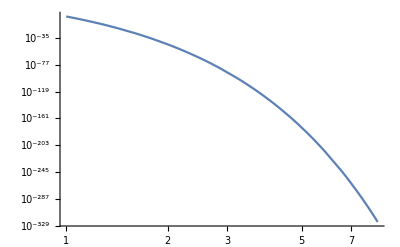

This gives the homogeneous solution which satisfies the boundary conditions (value at surface + no cusp)

```mathematica
"Now look at the BCs at ∞"
DSolve[-1/r^2 D[r^2 δϕ'[r],{r}]== f[r]-(nF β) δϕ[r]/.f->Function[{r},0],δϕ,r][[1]]//Simplify
"Take C[2] -> 0 so that solution decays to ∞"
δϕ[r]/.%%/.C[2]->0//Simplify//PowerExpand
Solve[(%/.r->rE)==ϕE+mp ϕgE,C[1]][[1]]
ϕout=%%/.%//Simplify
"This gives the homogeneous solution which satisfies the boundary conditions (value at surface + no cusp)"
%%/.{nF->1/(β λD^2),rE->1,ϕE->0.1 -mp ϕgE}/.λD->0.01//PowerExpand
LogLogPlot[%,{r,1,10^5},PlotRange->All]
Series[Out[-3],{r,0,1}]
(*
(δϕ[r]/.%%)/.Solve[(%/.r->rE)==NS,C[2]]//Simplify//Expand
D[%[[1]],r]//Simplify
Series[%,{r,0,1}]
Solve[()==0]
*)
```

```mathematica
ϕin
ϕout
D[%%,r]/.r->rE//Simplify
D[%%,r]/.r->rE//Simplify
%%-%//Simplify
```

(rE (ϕE+mp ϕgE) Csch[√nF rE √β] Sinh[√nF r √β])/r

(ⅇ^(√nF (-r+rE) √β) rE (ϕE+mp ϕgE))/r

((ϕE+mp ϕgE) (-1+√nF rE √β Coth[√nF rE √β]))/rE

-((1+√nF rE √β) (ϕE+mp ϕgE))/rE

√nF √β (ϕE+mp ϕgE) (1+Coth[√nF rE √β])

#### with grav potential solver

In the absence of gravity, at leading order in ϕ

{δϕ→Function[{r},(2 A+A nF r^2 β)/(nF^2 r β^2)+(ⅇ^(-√nF r √β) C[1])/r+(ⅇ^(√nF r √β) C[2])/(2 √nF r √β)]}

((A (2+nF r^2 β))/(nF^2 β^2)+ⅇ^(-√nF r √β) C[1]+ⅇ^(√nF r √β) C[2])/r

(-(2 A)/(nF^2 β^2)-C[1]-C[2])/r^2+(A/(nF β)+(nF β C[1])/2+(nF β C[2])/2)+O[r]^1

{{C[1]→(-2 A-nF^2 β^2 C[2])/(nF^2 β^2)}}

(2 A)/(nF^2 r β^2)+(A r)/(nF β)-(2 A Cosh[√nF r √β])/(nF^2 r β^2)+(2 A Sinh[√nF r √β])/(nF^2 r β^2)+(2 C[2] Sinh[√nF r √β])/r

{C[2]→1/(2 nF^2 β^2)(-2 A+2 A Coth[√nF rE √β]-2 A Csch[√nF rE √β]-A nF rE^2 β Csch[√nF rE √β]+nF^2 rE β^2 ϕE Csch[√nF rE √β]+mp nF^2 rE β^2 ϕgE Csch[√nF rE √β])}

1/(nF^2 r β^2)Csch[√nF rE √β] ((-A (2+nF rE^2 β)+nF^2 rE β^2 (ϕE+mp ϕgE)) Sinh[√nF r √β]+A (2 Sinh[√nF (r-rE) √β]+(2+nF r^2 β) Sinh[√nF rE √β]))

This gives the homogeneous solution which satisfies the boundary conditions (value at surface + no cusp)

1/r 7.44015×10^-52 (0.01 (1.34406×10^43 (2+10000. r^2)+2 Sinh[100. (-1+r)])+9.9999×10^6 Sinh[100. r])

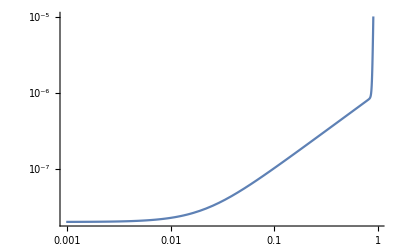

This gives the homogeneous solution which satisfies the boundary conditions (value at surface + no cusp)

```mathematica
"In the absence of gravity, at leading order in ϕ"
DSolve[-1/r^2 D[r^2 δϕ'[r],{r}]==A r-(nF β) δϕ[r]/.f->Function[{r},0],δϕ,r][[1]]//Simplify
δϕ[r]/.%/.C[2]->2 √(β nF) C[2]//Simplify//PowerExpand
Series[D[%,r],{r,0,0}]
Solve[Normal@% == 0,C[1]]
%%%/.%[[1]]//ExpToTrig
Solve[(%/.r->rE)==ϕE+mp ϕgE,C[2]][[1]]
ϕin = %%/.%//Simplify
"This gives the homogeneous solution which satisfies the boundary conditions (value at surface + no cusp)"
%%/.{nF->1/(β λD^2),rE->1,ϕE->0.1 -mp ϕgE,A->0.01}/.λD->0.01//PowerExpand
LogLogPlot[%,{r,0,1}]
Series[Out[-3],{r,0,1}]
(*
(δϕ[r]/.%%)/.Solve[(%/.r->rE)==NS,C[2]]//Simplify//Expand
D[%[[1]],r]//Simplify
Series[%,{r,0,1}]
Solve[()==0]
*)
```

```mathematica
"Now look at the BCs at ∞"
DSolve[-1/r^2 D[r^2 δϕ'[r],{r}]== f[r]-(nF β) δϕ[r]/.f->Function[{r},0],δϕ,r][[1]]//Simplify
"Take C[2] -> 0 so that solution decays to ∞"
δϕ[r]/.%%/.C[2]->0//Simplify//PowerExpand
Solve[(%/.r->rE)==ϕE+mp ϕgE,C[1]][[1]]
ϕout=%%/.%//Simplify
"This gives the homogeneous solution which satisfies the boundary conditions "
%%/.{nF->1/(β λD^2),rE->1,ϕE->0.1 -mp ϕgE}/.λD->0.01//PowerExpand
LogLogPlot[%,{r,1,10^5},PlotRange->All]
Series[Out[-3],{r,0,1}]
```

Now look at the BCs at ∞

{δϕ→Function[{r},(ⅇ^(-√nF r √β) C[1])/r+(ⅇ^(√nF r √β) C[2])/(2 √nF r √β)]}

Take C[2] -> 0 so that solution decays to ∞

(ⅇ^(-√nF r √β) C[1])/r

{C[1]→ⅇ^(√nF rE √β) rE (ϕE+mp ϕgE)}

(ⅇ^(√nF (-r+rE) √β) rE (ϕE+mp ϕgE))/r

This gives the homogeneous solution which satisfies the boundary conditions

(0.1 ⅇ^(100. (1-r)))/r

-Graphics-

This gives the homogeneous solution which satisfies the boundary conditions

```mathematica
ϕin
ϕout
D[%%,r]/.r->rE//Simplify
D[%%,r]/.r->rE//Simplify
%%-%//Simplify
Solve[(%/.ϕgE->0)==0,ϕE]
"So provided the equation in the Earth is sourced - ie. gravity is included, we can solve for ϕE such that there are no singular charge sources. "
```

1/(nF^2 r β^2)Csch[√nF rE √β] ((-A (2+nF rE^2 β)+nF^2 rE β^2 (ϕE+mp ϕgE)) Sinh[√nF r √β]+A (2 Sinh[√nF (r-rE) √β]+(2+nF r^2 β) Sinh[√nF rE √β]))

(ⅇ^(√nF (-r+rE) √β) rE (ϕE+mp ϕgE))/r

1/(nF^(3/2) rE β^(3/2))(√nF √β (2 A rE-nF β (ϕE+mp ϕgE))+(-A (2+nF rE^2 β)+nF^2 rE β^2 (ϕE+mp ϕgE)) Coth[√nF rE √β]+2 A Csch[√nF rE √β])

-((1+√nF rE √β) (ϕE+mp ϕgE))/rE

1/(nF^(3/2) rE β^(3/2))(2 A √nF rE √β+nF^2 rE β^2 ϕE+mp nF^2 rE β^2 ϕgE+(-A (2+nF rE^2 β)+nF^2 rE β^2 (ϕE+mp ϕgE)) Coth[√nF rE √β]+2 A Csch[√nF rE √β])

{{ϕE→(-2 A √nF rE √β+2 A Coth[√nF rE √β]+A nF rE^2 β Coth[√nF rE √β]-2 A Csch[√nF rE √β])/(nF^2 rE β^2 (1+Coth[√nF rE √β]))}}

So provided the equation in the Earth is sourced - ie. gravity is included, we can solve for ϕE such that there are no singular charge sources.

#### Corrected analytic captured charge including effects of gravity

```mathematica
"Nofr is the total DM accumulated (charged or not) Ie. it is |α_pD|+|α_eD|+β"
"so we know that n(r) = 2 n_∞ E^(-q ϕE) (|α_pD|+|α_eD|+β) == 2 n_∞ E^(-q ϕE)+ n_C"
nofr
```

Nofr is the total DM accumulated (charged or not) Ie. it is |α_pD|+|α_eD|+β

so we know that n(r) = 2 n_∞ E^(-q ϕE) (|α_pD|+|α_eD|+β) == 2 n_∞ E^(-q ϕE)+ n_C

ⅇ^(-q ϕesc) n∞ T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))

ATTN SEE THE APPENDIX: n_∞ ->n_s= n_∞ E^(-q ϕ) but to n_∞ ->n_s= n_∞ (1+ϕ)

```mathematica
DSolve[D[Logn[r],r]+ (κ+1)D[Log[T[r]],r](*+(mχ g[r])/T[r]*)==0/.{κ->-1/(2 (1+mχbymsm)^(3/2))(*,T->Function[{r},TS (r-rS)+TC(*A/(1+E^(a (r+c)))*)(*+B*)]*)}(*/.mχbymsm->10^-2*),Logn,r]
E^Logn[r]/.%[[1]]//FullSimplify
Solve[(%/.r->rE)==NS,C[1]][[1]]/.C[2]->0
%%/.%[[1]]
nofr=%/.NS->2 n∞ E^(-q ϕesc)(*+ Subscript[n, C]*)(*assume there is not captured charge right at the surface*)
"Then we just need to solve the following"
NCap[ϕesc]+Ngrav==Integrate[4 π r^2(nofr- 2 n∞ E^(-q ϕesc)),{r,0,rE}]
"Or equivalently"
E^(q ϕesc)(NCap[ϕesc] +Ngrav)==Integrate[4 π r^2(nofr- 2 n∞ E^(-q ϕesc))/.ϕesc->0,{r,0,rE}]
"And from above, we know that there is some mass dependence to Ncap, but that the variation with ϕE is roughly linear so that:"
E^(q ϕesc)(Nbyϕesc ϕesc + Ngrav )==Integrate[4 π r^2(nofr- 2 n∞ E^(-q ϕesc))/.ϕesc->0,{r,0,rE}]
"We define the RHS to be IofT then we can solve this analytically:"
ϕescsol = Solve[E^(q ϕesc)Nbyϕesc ϕesc + E^(q ϕesc) Ngrav== IofT,ϕesc][[1]]//Simplify
"Which then gives the analytic expression for Ncap"
Ncapsol=Nbyϕesc ϕesc+ Ngrav/.%%[[1]]//Simplify
IofT== Integrate[4 π r^2(nofr- 2 n∞ E^(-q ϕesc))/.ϕesc->0,{r,0,rE}]
```

{{Logn→Function[{r},C[1]+1/2 (-2+1/(1+mχbymsm)^(3/2)) Log[T[r]]]}}

ⅇ^C[1] T[r]^(-1+1/(2 (1+mχbymsm)^(3/2)))

{C[1]→Log[NS T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))]}

NS T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))

2 ⅇ^(-q ϕesc) n∞ T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2)))

Then we just need to solve the following

Ngrav+NCap[ϕesc]==∫_0^rE 4 π r^2 (-2 ⅇ^(-q ϕesc) n∞+2 ⅇ^(-q ϕesc) n∞ T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2))))ⅆr

Or equivalently

ⅇ^(q ϕesc) (Ngrav+NCap[ϕesc])==∫_0^rE 4 π r^2 (-2 n∞+2 n∞ T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2))))ⅆr

And from above, we know that there is some mass dependence to Ncap, but that the variation with ϕE is roughly linear so that:

ⅇ^(q ϕesc) (Ngrav+Nbyϕesc ϕesc)==∫_0^rE 4 π r^2 (-2 n∞+2 n∞ T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2))))ⅆr

We define the RHS to be IofT then we can solve this analytically:

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{ϕesc→-Ngrav/Nbyϕesc+ProductLog[(ⅇ^((Ngrav q)/Nbyϕesc) IofT q)/Nbyϕesc]/q}

Which then gives the analytic expression for Ncap

(Nbyϕesc ProductLog[(ⅇ^((Ngrav q)/Nbyϕesc) IofT q)/Nbyϕesc])/q

IofT==∫_0^rE 4 π r^2 (-2 n∞+2 n∞ T[r]^(-1+1/(2 (1+mχbymsm)^(3/2))) T[rE]^(1-1/(2 (1+mχbymsm)^(3/2))))ⅆr

```mathematica
(*IofTtest=Integrate[4 n∞ π r^2 (T[r]/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))) /.T->Function[{r},10 TS+6 TS Boole[r<1/2 rE]],{r,0,rE}]*)
IofTtest=2n∞ (Integrate[4  π r^2 (TM/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))) ,{r,rC,rE}]+Integrate[4 π r^2 (TC/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))) ,{r,0,rC}]- Integrate[4 π r^2  ,{r,0,rE}])//Simplify
```

8/3 n∞ π (-rE^3+rC^3 (TC/TS)^(-1+1/(2 (1+mχbymsm)^(3/2)))+(-rC^3+rE^3) (TM/TS)^(-1+1/(2 (1+mχbymsm)^(3/2))))

```mathematica
Ngravtemp= (m  "G""ME")/(q "e"√(αD/α))/.m->"m"2 10^(logm - 6)/.q->1/.SIConstRepl/.EarthRepl/.logm->10//Simplify
```

(4.52632×10^7)/(√(αD/α))

```mathematica
ϕescsol
%/.Nbyϕesc->Ncapofϕ[logm,0]/.Ngrav->Ngravtemp/.IofT->IofTtest/.q->1/.α->αD;
%/.{rC->3.4 10^6 m,rE->6.4 10^6 m}/.{TS->293 k,TM -> 2623 k, TC->5470 k}
%/.n∞->Capture`naDM[0.05,"m"2 10^(logm-6)/.SIConstRepl] m^-3/.mχbymsm->10^(logm-10)/.logm->10
```

{ϕesc→-Ngrav/Nbyϕesc+ProductLog[(ⅇ^((Ngrav q)/Nbyϕesc) IofT q)/Nbyϕesc]/q}

{ϕesc→-4.52632×10^7 10^(-25.4261+logm)+ProductLog[1/3 2^(-22.4261+logm) 5^(-25.4261+logm) ⅇ^(4.52632×10^7 10^(-25.4261+logm)) (-2.62144×10^20 m^3+3.9304×10^19 (293/5470)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3+2.2284×10^20 (293/2623)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3) n∞ π]}

{ϕesc→17.8489+2.97636 ⅈ}

```mathematica
Ncapandϕesc={Nbyϕesctest//N,Nbyϕesctest ProductLog[IofTtest/Nbyϕesctest],ProductLog[IofTtest/Nbyϕesctest],√(2/3 v0^2 ProductLog[IofTtest/Nbyϕesctest])}//Simplify//PowerExpand;
%/.{rC->3.4 10^6 m,rE->6.4 10^6 m}/.{TS->293 k,TM -> 2623 k, TC->5470 k}
%/.n∞->Capture`naDM[0.05,"m"2 10^(logm-6)/.SIConstRepl] m^-3/.mχbymsm->10^(logm-10)/.logm->10
"the value of Ncap seems reasonable (albeit much smaller, but okay they were conservative in the appendix), but the value of ϕE does not. It is about 100 times larger than it should be expected. "
```

{5.×10^27 ⅇ^(-2.30259 logm),2^(27-logm) 5^(28-logm) ProductLog[1/3 2^(-24+logm) 5^(-28+logm) (-2.62144×10^20 m^3+3.9304×10^19 (293/5470)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3+2.2284×10^20 (293/2623)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3) n∞ π],ProductLog[1/3 2^(-24+logm) 5^(-28+logm) (-2.62144×10^20 m^3+3.9304×10^19 (293/5470)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3+2.2284×10^20 (293/2623)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3) n∞ π],√(2/3) v0 √ProductLog[1/3 2^(-24+logm) 5^(-28+logm) (-2.62144×10^20 m^3+3.9304×10^19 (293/5470)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3+2.2284×10^20 (293/2623)^(1-1/(2 (1+mχbymsm)^(3/2))) m^3) n∞ π]}

{5.×10^17,6.46342×10^18+1.45974×10^18 ⅈ,12.9268+2.91947 ⅈ,(2.95405+0.329432 ⅈ) v0}

the value of Ncap seems reasonable (albeit much smaller, but okay they were conservative in the appendix), but the value of ϕE does not. It is about 100 times larger than it should be expected.

#### number density in the presence of a potential

### Unit testing proper treatment - ∇T=0 - ignoring ϕg

#### The EOM and solution - assuming fixed grav density

```mathematica
"Can we fix the grav potential in the Earth by taking ϕg to be a fixed value in the Earth instead of varying quadratically? It is like a 30 percent difference between the value at the surface and at the centre";
"Also, see the numerical section, it looks like β mpD ϕg may be small";
"Or if not, then the conservative thing to do would be to take ϕg[0] as the representative value since it is the minimum of the potential and will increase the amount dark protons in the Earth, OOOR bracket with value at the surface and at the centre of the Earth";

"Also remember that if β mp ϕg can be treated as small, then we can linearize. And the linearized equations can be solved via Green's functions.";
```

Need to fix factors of 4 π etc

```mathematica
Clear[mpD]
(*ϕEOM =( ("e")/r^2 √(αD/α)D[r^2 δϕ'[r],r]==4 π mpD ρg[r] G - ("e")^2/("ϵ0")√(αD/α)ne+("e")^2/("ϵ0")√(αD/α)np)/.{ne->nF E^(- βe "e"δϕ[r]),np->nF E^(βp "e"δϕ[r]),ρg->Function[{r},ρg]}*)
ϕEOM =( ("e")/r^2 √(αD/α)D[r^2 δϕ'[r],r]==4 π mpD ρg[r] G - ("e")^2/("ϵ0")αD/α ne+("e")^2/("ϵ0")αD/α np)/.{ne->nF E^(- βe √(αD/α)"e"δϕ[r]),np->nF E^(βp √(αD/α)"e"δϕ[r]),ρg->Function[{r},ρg]}
```

(e √(αD/α) (2 r δϕ'[r]+r^2 δϕ''[r]))/r^2==-(e^2 ⅇ^(-e √(αD/α) βe δϕ[r]) nF αD)/(ϵ0 α)+(e^2 ⅇ^(e √(αD/α) βp δϕ[r]) nF αD)/(ϵ0 α)+4 G mpD π ρg

```mathematica
Series[ϕEOM,{δϕ[r],0,1}]//Normal
(*DSolve[%,δϕ[r],r][[1]](*/.C[2]->2 √(nF β)C[2]*)/.nF->1/(β λD^2)(("e")^2/("ϵ0")√(αD/α))^-1//PowerExpand*)
(*δϕsol = DSolve[%/.ρg->Function[{r},0],δϕ[r],r][[1]]/.C[2]->2 √(2 nF β)(("e")^2/("ϵ0"))^(1/2)C[2]/.nF->1/(2β λD^2)(("e")^2/("ϵ0")√(αD/α))^-1//PowerExpand*)
δϕsol = DSolve[%,δϕ[r],r][[1]]/.C[2]->2 √(nF( βe+βp))(("e")^2/("ϵ0")αD/α)^(1/2)C[2]/.nF->1/(( βe+βp) λD^2)(("e")^2/("ϵ0")αD/α)^-1//PowerExpand//Simplify
```

(e √(αD/α) (2 r δϕ'[r]+r^2 δϕ''[r]))/r^2==4 G mpD π ρg+((e^3 nF αD √(αD/α) βe+e^3 nF αD √(αD/α) βp) δϕ[r])/(ϵ0 α)

{δϕ[r]→-(4 G mpD π √α λD^2 ρg)/(e √αD)+(ⅇ^(-r/λD) C[1]+ⅇ^(r/λD) C[2])/r}

```mathematica
"the 2 comes from  λD ∝ ∑ q^2n_F = 2 n_F for dark electrons and protons"
(*λD/.Solve[nF==1/(2 λD^2)(("e")^2/("ϵ0")√(αD/α))^-1,λD][[2]]//PowerExpand//Simplify//PowerExpand*)
```

```mathematica
"The Debeye Length is then"
λDsol = λD/.Solve[nF==1/(( βe+βp) λD^2)(("e")^2/("ϵ0")αD/α)^-1,λD][[2]]//PowerExpand//Simplify//PowerExpand
```

The Debeye Length is then

(√ϵ0 √α)/(e √nF √αD √(βe+βp))

#### Assume mp is small enough that grav can be ignored, with αD = α, and assuming thermalized with the Earth inside and at T_D outside

```mathematica
Clear[rE]
"Solve for δϕ in the Earth"
δϕ[r]/.δϕsol/.αD->α
Series[D[%,r],{r,0,0}]
Solve[Normal@% == 0,C[1]]
 Solve[(Out[-3]/.%[[1]]/.r->rE)==ϕE,C[2]]//Simplify
δϕin=Out[-4]/.%%[[1]]/.%[[1]]/.{β->βin,λD->λin}//Simplify//ExpToTrig//Simplify
```

Solve for δϕ in the Earth

-(4 G mpD π λD^2 ρg)/e+(ⅇ^(-r/λD) C[1]+ⅇ^(r/λD) C[2])/r

(-C[1]-C[2])/r^2+(C[1]+C[2])/(2 λD^2)+O[r]^1

{{C[1]→-C[2]}}

{{C[2]→(ⅇ^(rE/λD) rE (4 G mpD π λD^2 ρg+e ϕE))/(e (-1+ⅇ^((2 rE)/λD)))}}

(-4 G mpD π r λin^2 ρg+rE (4 G mpD π λin^2 ρg+e ϕE) Csch[rE/λin] Sinh[r/λin])/(e r)

```mathematica
δϕin/.r->rE//Simplify
Limit[D[δϕin,r]//Simplify,r->0]
```

ϕE

0

```mathematica
"Solve δϕ for r>rE"
δϕ[r]/.δϕsol/.αD->α/.ρg->0
(*%/.Solve[nF==1/(β λD^2)(("e")^2/("ϵ0")√(αD/α))^-1,λD][[2]]/.αD->α*)
"δϕ->0 as r->∞ gives"
%%/.C[2]->0
"δϕ[rE]=ϕE gives"
Solve[(%%/.r->rE)==ϕE,C[1]]
δϕout=Out[-3]/.%[[1]]/.λD->λout//Simplify
```

Solve δϕ for r>rE

(ⅇ^(-r/λD) C[1]+ⅇ^(r/λD) C[2])/r

δϕ->0 as r->∞ gives

(ⅇ^(-r/λD) C[1])/r

δϕ[rE]=ϕE gives

{{C[1]→ⅇ^(rE/λD) rE ϕE}}

(ⅇ^((-r+rE)/λout) rE ϕE)/r

```mathematica
"The condition that the charge distribution is regular at the interface gives the condition on ϕE"
Solve[(D[δϕin-δϕout,r]/.r->rE)==0,ϕE]//Simplify
```

The condition that the charge distribution is regular at the interface gives the condition on ϕE

{{ϕE→(4 G mpD π λin^2 λout ρg (λin-rE Coth[rE/λin]))/(e rE (λin+λout Coth[rE/λin]))}}

```mathematica
Series[λin-rE Coth[rE/λin]/.rE->λin ϵ,{ϵ,∞,2}]
```

λin+Coth[ϵ+O[1/ϵ]^3] (-λin ϵ+O[1/ϵ]^3)

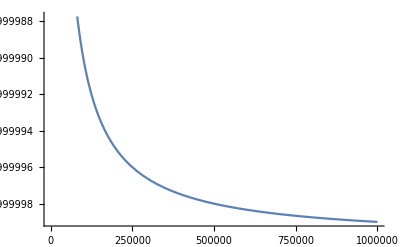

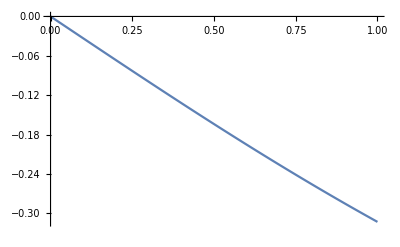

```mathematica
Plot[1/x- Coth[x],{x,10,10^6}]
Plot[1/x- Coth[x],{x,0,1}]
```

### Unit testing proper treatment - ∇T=0 - with ϕg done numerically solve for δϕ

#### The EOM and solution - assuming fixed grav density

```mathematica
Capture`Vgrav[r]
D[%,r]
%/.r->0.99"rE"/.Constants`EarthRepl
√(-2%%%)/.r->"rE"/.Constants`EarthRepl
```

Piecewise[{{-(3.99589×10^14)/r, r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-r^2), r<6.371×10^6}, {-6.272×10^7, True}}]

Piecewise[{{1.54522×10^-6 r, r<6371000}, {(3.99589×10^14)/r^2, r>6371000}, {Indeterminate, True}}]

9.74616

11200.

```mathematica
1/r^2 D[r^2 D[Capture`Vgrav[r],r],r]/.r->10^5
```

4.63567×10^-6

```mathematica
Vgrav[6 10^6]/Vgrav[0]
```

0.704358

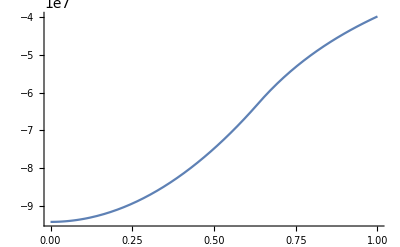

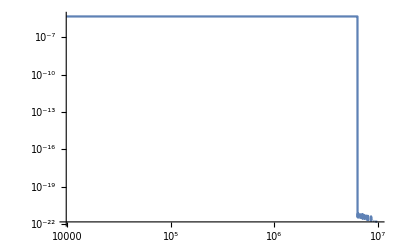

```mathematica
Plot[Capture`Vgrav[r],{r,0,10^7}]
LogLogPlot[1/r^2 D[r^2 D[Capture`Vgrav[r],r],r]/.r->rt,{rt,0,10^7}]
```

Need to fix factors of 4 π etc

<|e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,eVm→2.×10^-7,G→6.67×10^-11|>

```mathematica
Join[]
```

```mathematica
Join[Constants`SIConstRepl,Constants`EarthRepl/.Association->List]
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,eVm→2.×10^-7,G→6.67×10^-11,rE→6.371×10^6,ME→5.97×10^24,vesc→11200,rcore→3.486×10^6,Tcrust→2623,Tcore→5470,βcrust→2.76063×10^19,βcore→1.32379×10^19,SiO2Frac→0.447,MgOFrac→0.387}

```mathematica
Clear[Getϕeom]
Getϕeom[mpD_:(2 10^3"m"/.Constants`SIConstRepl),αDbyα_:1,meDbympD_:10^-4,βs_:<|"βp"->βp,"βe"->βe|>,fD_:0.05,constrepl_:Join[Constants`SIConstRepl,(Constants`EarthRepl/.Association->List)]]:=Module[{nF,ϕeom},
(*
solve the Poisson equation assuming ∇T=0, and a 1 component Earth model
Then the no net diffusion condition implies:
n(r) = n e^(- β Subscript[V, total](r))

For convenience we define:
δϕ = ϕ - Subscript[m, Subscript[p, D]]/Subscript[e, D] Subscript[ϕ, grav]
so we can solve the ODE for δϕ.

We also take units such that Subscript[r, E]=1
*)
nF=naDM[fD,mpD (1+ meDbympD)];
(*ϕeom=(1/("rE")^2 ("e")/r √αDbyα D[r^2 δϕ'[r],r]==r(mpD Lapϕg[r] - ("e")^2/("ϵ0")αDbyα neD+("e")^2/("ϵ0")αDbyα npD))/.{neD->nF E^(- "βe" (√αDbyα"e"δϕ[r]+mpD(1+meDbympD)ϕg[r])),npD->nF E^("βp" √αDbyα"e"δϕ[r]),Lapϕg->Function[{r},1/("rE")^2 1/r^2 D[r^2 ϕg'[r],r]]}/.ϕg->Function[{r},Capture`Vgrav["rE"r]]/.βs/.constrepl;*)
Print["charge mass ratio is: \n","e"1/mpD/.constrepl];
(*ϕeom=( 1/r D[r^2 δϕ'[r],r]==("rE")^2 r(mpD/("e"√αDbyα)Lapϕg[r] - ("e")/("ϵ0")√αDbyα neD+("e")/("ϵ0")√αDbyα npD))/.{neD->nF E^(- "βe" (√αDbyα"e"δϕ[r]+mpD(1+meDbympD)ϕg[r])),npD->nF E^("βp" √αDbyα"e"δϕ[r]),Lapϕg->Function[{r},1/("rE")^2 1/r^2 D[r^2 ϕg'[r],r]]}/.ϕg->Function[{r},Capture`Vgrav["rE"r]]/.βs/.constrepl;*)
ϕeom=( 1/r D[r^2 δϕ'[r],r]==("rE")^2 r(mpD/("e"√αDbyα)Lapϕg[r] - ("e")/("ϵ0")√αDbyα neD+("e")/("ϵ0")√αDbyα npD))/.{neD->nF E^(- "βe" (√αDbyα"e"ϵ δϕ[r] + mpD(1+meDbympD) ϕg[r])),npD->nF E^("βp" ϵ √αDbyα"e"δϕ[r]),Lapϕg->Function[{r},1/("rE")^2 1/r^2 D[r^2 ϕg'[r],r]]}/.ϕg->Function[{r},Capture`Vgrav["rE"r]]/.βs/.constrepl;
 Normal@Series[ϕeom,{ϵ,0,1}]/.ϵ->1
]
```

```mathematica
"As a test case consider the TH disc case"
foverv = 5
mpD =foverv(2 10^3"m"/.Constants`SIConstRepl)
meDbympD=10^-4
βD="βD"/.Capture`v0toβD[20 10^3,mpD,mpD meDbympD]
ϕEomIn=Assuming[r<(*"rE"/.Constants`EarthRepl*)1,Getϕeom[mpD,10^0,meDbympD,<|"βp"->"βcore"/.Constants`EarthRepl,"βe"->βD|>,(*10^-9*)10^-8]//Simplify]
```

As a test case consider the TH disc case

5

9.11×10^-27

1/10000

Set::write: Tag Times in Capture`Private`s Capture`Private`veDmean$47483 is Protected.

1.64638×10^18

charge mass ratio is: 
1.75948×10^7

2 δϕ'[r]+r δϕ''[r]==r (441.572-1766.98 ⅇ^(-0.4704 r^2)+(914.275+466.298 ⅇ^(-0.4704 r^2)) δϕ[r])

now solve the ode in the Earth subject to the no cusp boundary condition, and the boundary condition: ϕ(r_E)=ϕ_E

{δϕ'[1/100]==0,δϕ[1]==22.9257}

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

{{δϕ→InterpolatingFunction[…]}}

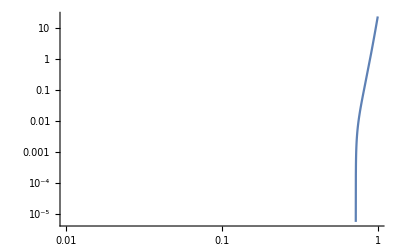

-1.0554×10^6

```mathematica
"now solve the ode in the Earth subject to the no cusp boundary condition, and the boundary condition: ϕ(r_E)=ϕ_E"
rE = "rE"/.Constants`EarthRepl;
(*bcs={δϕ'[1]==-0.005,δϕ[1]==0.05}*)
δr=10^-2;
bcs={δϕ'[δr]==0,δϕ[1]==0.05 1/(βD "e")/.SIConstRepl}
(*NDSolve[{ϕEomIn,bcs},δϕ,r,Method->{"Shooting"}]*)
NDSolve[{ϕEomIn,bcs},δϕ,{r,δr,1},Method->"Chasing"]
LogLogPlot[(δϕ/.%[[1]])[r],{r,δr,1},PlotRange->{{δr,1},Full}]
(δϕ/.%%[[1]])[δr ]
```

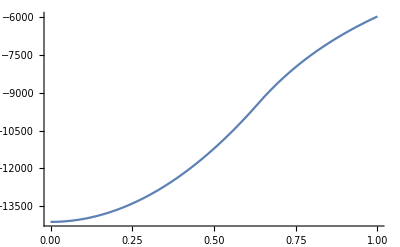

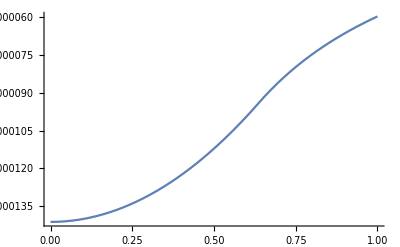

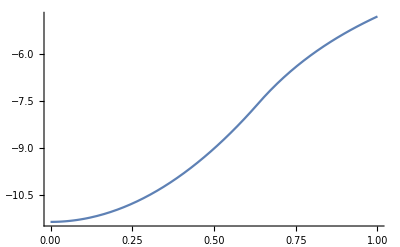

```mathematica
Plot[mpD 10^4 Capture`Vgrav[r]βD,{r,0,10^7}]
Plot[mpD meDbympD Capture`Vgrav[r]βD,{r,0,10^7}]
Plot[mpD Capture`Vgrav[r]βcore,{r,0,10^7}]
```

```mathematica
βcore
```

1.32379×10^19

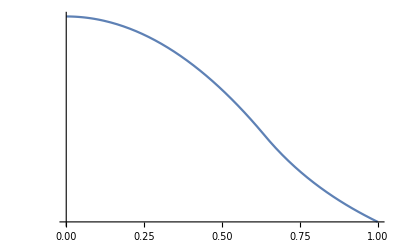

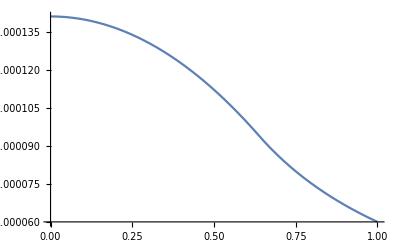

-Graphics-

```mathematica
LogPlot[Exp[-mpD 10^4 Capture`Vgrav[r]βD],{r,0,10^7}]
Plot[Exp[-mpD meDbympD Capture`Vgrav[r]βD],{r,0,10^7}]
Plot[Exp[-mpD 10^4 Capture`Vgrav[r]βcore],{r,0,10^7}]
```

#### Follow ups and solution to instability

The instability seems like it can be remedied by implicit methods (see eg. section 9.3.2 of Newman on numerical stability - pg 425) 

I wonder if Mathematica can do implicit methods for stability. See 

https://reference.wolfram.com/language/tutorial/NDSolveImplicitRungeKutta.html.en

### Analytic treatment with captured population to cancel gravity

CHECK SIGNS ETC, or find the condition such that the gravitational well is filled. Because the below assumptions don’t fill the well, this is ϕ:

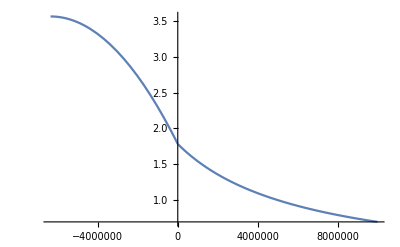

Adding grav we get:

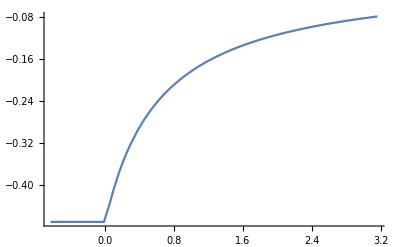

So the completely filled potential is A=0 both in and out:

```mathematica
δϕsolflat=Solve[√(αD/α)"e"δϕ[r] + mpD ϕg ==A,δϕ[r]][[1]]/.A->0
"This then determines the captured charge " 
(mpD ρG G HeavisideTheta[rE-r]==- ("e")^2/("ϵ0")αD/α ne+("e")^2/("ϵ0")αD/α np+("e")^2/("ϵ0")αD/α nc)/.{np->nF E^(- βp (√(αD/α)"e"δϕ[r] + mpD ϕg[r])),ne->nF E^(-βe (-√(αD/α)"e"δϕ[r]+meD ϕg[r]))}/.ϕg->Function[{r},ϕg]/.%%/.{βp->βD,βe->βD}
ncap=nc/.Solve[%,nc][[1]]//Simplify
```

{δϕ[r]→(0.-9.11×10^-27 ϕg)/(e √(αD/α))}

This then determines the captured charge

9.11×10^-27 G ρG HeavisideTheta[-r+rE]==(e^2 nc αD)/(ϵ0 α)+(1. e^2 nF αD)/(ϵ0 α)-(e^2 ⅇ^(-1.64638×10^18 (0.+9.11×10^-27 ϕg+meD ϕg)) nF αD)/(ϵ0 α)

(-1.+1. ⅇ^((-1.49985×10^-8-1.64638×10^18 meD) ϕg)) nF+(9.11×10^-27 ϵ0 G α ρG HeavisideTheta[-r+rE])/(e^2 αD)

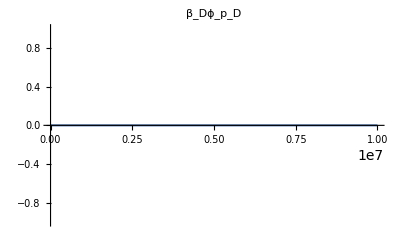

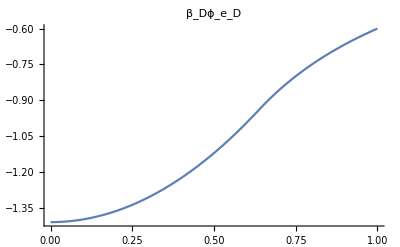

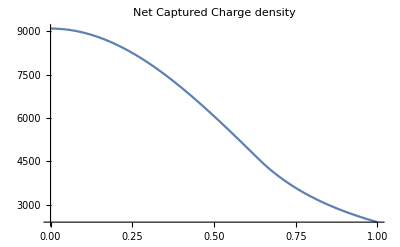

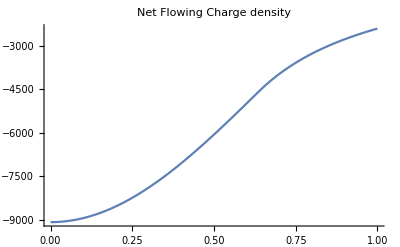

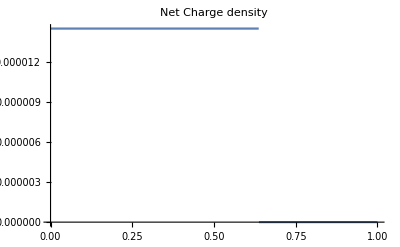

Total Captured charge in the Earth is:

6.71794×10^24

Total Captured charge everywhere is:

1.11032×10^29

1D effective potential is:

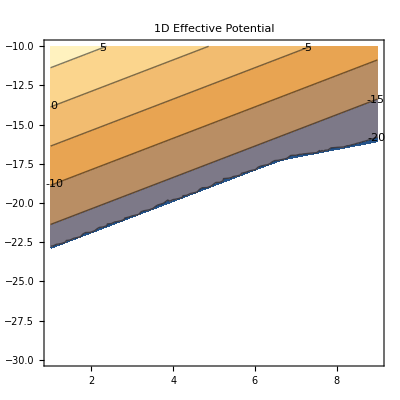

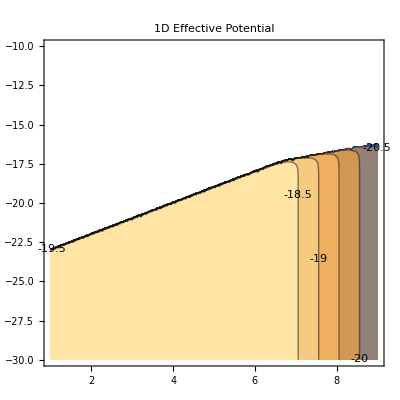

Looks monotonic to me, so no flux effects, which means this is a consistent solution.

We would still need to check:
1) that this isn't altered by electron capture or something ie. find a way to show that an exactly flat proton potential is somehow a prefered state (or at least a somehow conservative choice)
2) that the well can be filled to infinity and not just at earth

```mathematica
Plot[0,{r,0,10^7},PlotLabel->"β_Dϕ_p_D"]
Plot[βD(1+meDbympD )mpD Vgrav[r],{r,0,10^7},PlotLabel->"β_Dϕ_e_D"]
(*Plot[1-ⅇ^(-βD (1+meDbympD )mpD Vgrav[r]),{r,0,10^7}]*)
ngrav=("ϵ0"  mpD α)/(("e")^2 αD)1/r^2 D[r^2 Vgrav'[r],r]/.αD->α/.SIConstRepl;
nflow=(1-ⅇ^(-βD (1+meDbympD )mpD Vgrav[r]))naDM[0.05,(1+meDbympD )mpD ];
Plot[ngrav-nflow,{r,0,10^7},PlotLabel->"Net Captured Charge density"]
Plot[nflow,{r,0,10^7},PlotLabel->"Net Flowing Charge density"]
Plot[ngrav,{r,0,10^7},PlotLabel->"Net Charge density"]
"Total Captured charge in the Earth is:"
Integrate[(ngrav-nflow)4 π r^2,{r,0,"rE"/.EarthRepl}]
"Total Captured charge everywhere is:"
Integrate[(ngrav-nflow)4 π r^2,{r,0,10^9}]
"1D effective potential is:"
(*Manipulate[Plot[(1+meDbympD )mpD Vgrav[r]+10^(2logL)/(2 meDbympD mpD  r^2),{r,0,10^9},PlotLabel->"1D Effective Potential"],{logL,-20,0}]*)
ContourPlot[Log10[(1+meDbympD )mpD Vgrav[r]+10^(2logL)/(2 meDbympD mpD  r^2)]/.r->10^logr,{logr,1,9},{logL,-30,-10},PlotLabel->"1D Effective Potential",ContourLabels->True]
ContourPlot[Log10[-((1+meDbympD )mpD Vgrav[r]+10^(2logL)/(2 meDbympD mpD  r^2))]/.r->10^logr,{logr,1,9},{logL,-30,-10},PlotLabel->"1D Effective Potential",ContourLabels->True]
"Looks monotonic to me, so no flux effects, which means this is a consistent solution."
"We would still need to check:
1) that this isn't altered by electron capture or something ie. find a way to show that an exactly flat proton potential is somehow a prefered state (or at least a somehow conservative choice)
2) that the well can be filled to infinity and not just at earth"
```

#### Effect on Dark protons

#### DD effect on electrons?

The most interesting part of this analysis is the non-trivial effect on the dark electron velocity distribution: The escape velocity is:

```mathematica
"As a test case consider the TH disc"
foverv = 5
mpD =foverv(2 10^3"m"/.Constants`SIConstRepl)
meDbympD=10^-4
βD="βD"/.Quiet@Capture`v0toβD[20 10^3,mpD,mpD meDbympD]
```

As a test case consider the TH disc

5

9.11×10^-27

1/10000

1.64638×10^18

```mathematica
Vgrav[r]
```

Piecewise[{{-(3.99589×10^14)/r, r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-r^2), r<6.371×10^6}, {-6.272×10^7, True}}]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{vesc→7.9196×10^6}

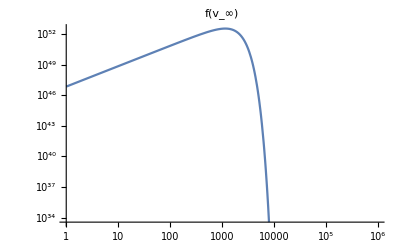

10^(6+2 logvkms) ⅇ^(-7.49925×10^-7 10^(2 logvkms))

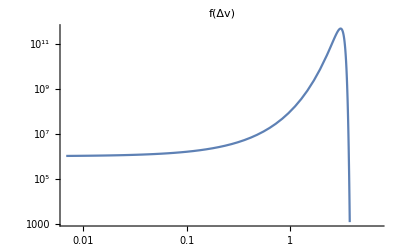

Where: Δv is given by:

Δvkms==(-7.9196×10^6+vms)/1000

```mathematica
Clear[Δv]
vesc^2==Re[-(1+mpD/meD)Vgrav[r]];
vescesol=Solve[%,vesc][[2]]/.meD->10^-6 mpD/.r->"rE"/.EarthRepl//Simplify
LogLogPlot[v^2 E^(-βD meDbympD mpD(v^2/2-(vesc/.%)^2))/.v->vkms/10^-3,{vkms,1,10^6},PlotLabel->"f(v_∞)"]
(*v^2 E^(-βD meDbympD mpD(v^2/2(*-(vesc/.vescesol)^2*)))/.v->(vkms+vesc/.vescesol)/10^-3
Log10[%]/.vkms->10^logvkms//Simplify//PowerExpand//Expand
Plot[%,{logvkms,0,7},PlotLabel->"f(v)"(*,PlotRange->{All,{-100,30}}*)]*)
v^2 E^(-βD meDbympD mpD(v^2/2(*-(vesc/.vescesol)^2*)))/.v->((*(vkms-vesc/.vescesol)*)Δvkms)/10^-3/.Δvkms->10^logvkms
(*Log10[%]/.vkms->10^logvkms//Simplify//PowerExpand//Expand*)
LogLogPlot[%,{logvkms,0,7},PlotLabel->"f(Δv)"(*,PlotRange->{All,{-100,30}}*)]
"Where: Δv is given by:"
Δvkms == (vms -vesc/.vescesol)/10^3
(*LogLogPlot[v^2 E^(-βD meDbympD mpD((v/(√2)-vesc/.%%)^2))/.v->vkms/10^-3,{vkms,1,10^6}]*)
(*LogLogPlot[v^2 E^(-βD meDbympD mpD(v^2/2(*-(vesc/.%%)^2*)))/.v->vkms/10^-3,{vkms,1,10^6}]*)
```

And since the mean will be at roughly 10^4km/s for meD/mpD =10^-4, we see we get an effect that is comparable to the SRDM except with a much larger flux of the high speed population since it is a result of a potential rather than a scattering event

#### Inside the Earth

```mathematica
Clear[λD,λDsol,mpD,βD]
"collisionless BE solution is:"
Subscript[n, i][r]==Subscript[n, F] E^(-Subscript[β, i] Subscript[V, i][r])
"Where n_F is the number density far from Earth. These agree with the values found in the appendix. Plugging into the Poisson equation"
Subscript[e, D] HoldForm[Δ δϕ[r]]== ∑_i Subscript[e, D]^2 Subscript[n, i][r]
"we then find"
ϕEOM =(-("e")/r^2 √(αD/α)D[r^2 δϕ'[r],r]==- ("e")^2/("ϵ0")αD/α ne+("e")^2/("ϵ0")αD/α np+("e")^2/("ϵ0")αD/α nc)/.{np->nF E^(- βp ϵ (√(αD/α)"e"δϕ[r] + mpD ϕg[r])),ne->nF E^(-βe ϵ (-√(αD/α)"e"δϕ[r]+meD ϕg[r]))}/.ϕg->Function[{r},ϕg/ϵ]/.{βp->βD,βe->βD}
"We can then consider inside the earth and assume that the captured charge fills the gravitational potential well of the dark protons, and no more. This flattens the total potential for the dark protons giving the condition for some constant A:"
δϕsolflat=Solve[√(αD/α)"e"δϕ[r] + mpD ϕg ==A ,δϕ[r]][[1]]
"This then determines the captured charge " 
(mpD ρG G==- ("e")^2/("ϵ0")αD/α ne+("e")^2/("ϵ0")αD/α np+("e")^2/("ϵ0")αD/α nc)/.{np->nF E^(- βp ϵ (√(αD/α)"e"δϕ[r] + mpD ϕg[r])),ne->nF E^(-βe ϵ (-√(αD/α)"e"δϕ[r]+meD ϕg[r]))}/.ϕg->Function[{r},ϕg/ϵ]/.%%/.{βp->βD,βe->βD}
ncap=nc/.Solve[%,nc][[1]]/.ϵ->1//Simplify
"So boom, we have the captured charge and ϕ in terms of A, which we can then sub into the junction conditions to solve for it."
```

collisionless BE solution is:

n_i[r]==ⅇ^(-β_i V_i[r]) n_F

Where n_F is the number density far from Earth. These agree with the values found in the appendix. Plugging into the Poisson equation

(Δ δϕ[r]) e_D==∑_i e_D^2 n_i[r]

we then find

-(e √(αD/α) (2 r δϕ'[r]+r^2 δϕ''[r]))/r^2==(e^2 nc αD)/(ϵ0 α)-(e^2 ⅇ^(-βD ϵ ((meD ϕg)/ϵ-e √(αD/α) δϕ[r])) nF αD)/(ϵ0 α)+(e^2 ⅇ^(-βD ϵ ((mpD ϕg)/ϵ+e √(αD/α) δϕ[r])) nF αD)/(ϵ0 α)

We can then consider inside the earth and assume that the captured charge fills the gravitational potential well of the dark protons, and no more. This flattens the total potential for the dark protons giving the condition for some constant A:

{δϕ[r]→(A-mpD ϕg)/(e √(αD/α))}

This then determines the captured charge

G mpD ρG==(e^2 nc αD)/(ϵ0 α)-(e^2 ⅇ^(-βD ϵ (-A+mpD ϕg+(meD ϕg)/ϵ)) nF αD)/(ϵ0 α)+(e^2 ⅇ^(-βD ϵ (A-mpD ϕg+(mpD ϕg)/ϵ)) nF αD)/(ϵ0 α)

-ⅇ^(-A βD) nF+ⅇ^(βD (A-(meD+mpD) ϕg)) nF+(ϵ0 G mpD α ρG)/(e^2 αD)

So boom, we have the captured charge and ϕ in terms of A, which we can then sub into the junction conditions to solve for it.

#### oustide the Earth

Outside the Earth, we can expand in both small ϕ and small gravity. 

Near the earth’s surface, this is not a good expansion parameter, but whatever, it’s a factor of at most 3 that we’re off by and it gets good far away (where gravity goes to 0), we can also take βD = βp = βe in the collisionless regime

```mathematica
Quiet@Capture`v0toβD[20 10^3,mp,mp 10^-4]["βD"]
mp(11200)^2/2
% %%//N
```

3/(200020000 mp)

62720000 mp

0.940706

```mathematica
Clear[λD,λDsol,mpD,βD]
"using the collisionless boltzmann equation, we fined the number densities of the various species vary as (neglecting the flux effects for the electrons)"
Subscript[n, i][r]==Subscript[n, F] E^(-Subscript[β, i] Subscript[V, i][r])
"Where n_F is the number density far from Earth. These agree with the values found in the appendix. Plugging into the Poisson equation"
Subscript[e, D] HoldForm[Δ δϕ[r]]== ∑_i Subscript[e, D]^2 Subscript[n, i][r]
"we then find"
ϕEOM =(-("e")/r^2 √(αD/α)D[r^2 δϕ'[r],r]==- ("e")^2/("ϵ0")αD/α ne+("e")^2/("ϵ0")αD/α np)/.{np->nF E^(- βp ϵ (√(αD/α)"e"δϕ[r] + mpD ϕg[r])),ne->nF E^(-βe ϵ (-√(αD/α)"e"δϕ[r]+meD ϕg[r]))}/.ϕg->Function[{r},ϕg]/.{βp->βD,βe->βD}
"The Poisson equation is non-linear, so we expand in small ϕ and look for a consistently small solution. Outside the Earth we can also expand in βD mp ϕ_g << 1 (this is not strictly correct, since it is O(1) right at the surface, but becomes a very good approximation far from the Earth). This gives a linear 2nd order inhomogeneous ODE for ϕ"
Normal@Series[ϕEOM,{ϵ,0,1}]/.ϵ->1/.ϕg->-(G M)/r
"Not surprisingly, this can be understood as a sourced Debeye equation. With the following Debeye length. For β_p=β_e and ϕ_g=0, it reduces to the one given in the appendix."
λDsol=Series[(("e" ⅇ^(-1/2 (meD βe+mpD βp) ϕg) √nF √αD √(ⅇ^(mpD βp ϕg) βe+ⅇ^(meD βe ϕg) βp))/(√("ϵ0") √α))^-1/.{βp->βD,βe->βD},{ϕg,0,0}]//Normal;
λD==λDsol
Out[-4]/.Solve[λD==λDsol,nF][[1]]//Simplify//Expand;
"then this can be solved analytically to give"
δϕsol = DSolve[%%,δϕ[r],r][[1]]/.C[2]->2/λD C[2]/.G->-r/M ϕg[r]//PowerExpand//Simplify
"Note that the particular solution vanishes for ϕ_g=0. We will find that ϕ_g!= 0 allows us to consistently determine ϕ_E and the entire solution in terms of microphysics parameters."
```

using the collisionless boltzmann equation, we fined the number densities of the various species vary as (neglecting the flux effects for the electrons)

n_i[r]==ⅇ^(-β_i V_i[r]) n_F

Where n_F is the number density far from Earth. These agree with the values found in the appendix. Plugging into the Poisson equation

(Δ δϕ[r]) e_D==∑_i e_D^2 n_i[r]

we then find

-(e √(αD/α) (2 r δϕ'[r]+r^2 δϕ''[r]))/r^2==-(e^2 ⅇ^(-βD ϵ (meD ϕg-e √(αD/α) δϕ[r])) nF αD)/(ϵ0 α)+(e^2 ⅇ^(-βD ϵ (mpD ϕg+e √(αD/α) δϕ[r])) nF αD)/(ϵ0 α)

The Poisson equation is non-linear, so we expand in small ϕ and look for a consistently small solution. Outside the Earth we can also expand in βD mp ϕ_g << 1 (this is not strictly correct, since it is O(1) right at the surface, but becomes a very good approximation far from the Earth). This gives a linear 2nd order inhomogeneous ODE for ϕ

-(e √(αD/α) (2 r δϕ'[r]+r^2 δϕ''[r]))/r^2==-(e^2 nF αD βD ((G M meD)/r-(G M mpD)/r+2 e √(αD/α) δϕ[r]))/(ϵ0 α)

Not surprisingly, this can be understood as a sourced Debeye equation. With the following Debeye length. For β_p=β_e and ϕ_g=0, it reduces to the one given in the appendix.

λD==(√ϵ0 √α)/(√2 e √nF √αD √βD)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

then this can be solved analytically to give

{δϕ[r]→(ⅇ^(-r/λD) C[1]+ⅇ^(r/λD) C[2])/r+((meD-mpD) √α ϕg[r])/(2 e √αD)}

Note that the particular solution vanishes for ϕ_g=0. We will find that ϕ_g!= 0 allows us to consistently determine ϕ_E and the entire solution in terms of microphysics parameters.

#### solve BCS - assuming each species has a different constant temperature in both regions

```mathematica
δϕsolflat
```

{δϕ[r]→(A-mpD ϕg)/(e √(αD/α))}

```mathematica
Clear[rE]
"We will solve for ϕ in and out of the Earth, and use the junction conditions to stitch them together. Doing so will determine ϕ_E. We will also use a toy model of thermalization; we assume β_p=β_E in the Earth and β_p=β_D out of the Earth, whereas β_e=β_D everywhere. \n Let's start with the solution inside the Earth"
"We need only impose the condition that that ϕ_in[r_E]=ϕ_E"
 Solve[(δϕ[r]/.δϕsolflat/.ϕg->ϕgE)==ϕE,A]//Simplify
δϕin=δϕ[r]/.δϕsolflat/.%[[1]]/.ϕg->ϕg[r]//Simplify
ncapintermsofϕE=ncap/.(%%[[1]])/.ϕg->ϕg[r]
```

We will solve for ϕ in and out of the Earth, and use the junction conditions to stitch them together. Doing so will determine ϕ_E. We will also use a toy model of thermalization; we assume β_p=β_E in the Earth and β_p=β_D out of the Earth, whereas β_e=β_D everywhere. 
 Let's start with the solution inside the Earth

We need only impose the condition that that ϕ_in[r_E]=ϕ_E

{{A→1. e √(αD/α) ϕE+9.11×10^-27 ϕgE}}

(1. e √(αD/α) ϕE+9.11×10^-27 ϕgE-9.11×10^-27 ϕg[r])/(e √(αD/α))

-ⅇ^(-1.64638×10^18 (1. e √(αD/α) ϕE+9.11×10^-27 ϕgE)) nF+ⅇ^(1.64638×10^18 (1. e √(αD/α) ϕE+9.11×10^-27 ϕgE-(9.11×10^-27+meD) ϕg[r])) nF+(9.11×10^-27 ϵ0 G α ρG)/(e^2 αD)

```mathematica
"Quick sanity check that our boundary conditions have been correctly imposed"
δϕin/.ϕg[r]->ϕgE//Simplify
Limit[D[δϕin,r]//Simplify,r->0]/.ϕg'[r]->0
```

Quick sanity check that our boundary conditions have been correctly imposed

ϕE

0

```mathematica
Clear[mpD]
"Now we do the same thing outside the Earth. "
δϕ[r]/.δϕsol;
"δϕ->0 as r->∞ gives"
%%/.C[2]->0
"δϕ[rE]=ϕE gives"
Solve[(%%/.r->rE)==ϕE,C[1]]//Simplify
δϕout=Out[-3]/.%[[1]]/.{βp->βpout,λD->λout}//Simplify
```

Now we do the same thing outside the Earth.

δϕ->0 as r->∞ gives

(ⅇ^(-r/λD) C[1])/r+((meD-mpD) √α ϕg[r])/(2 e √αD)

δϕ[rE]=ϕE gives

{{C[1]→(ⅇ^(rE/λD) rE (2 e √αD ϕE+(-meD+mpD) √α ϕg[rE]))/(2 e √αD)}}

(ⅇ^(-r/λout) (ⅇ^(r/λout) (meD-mpD) r √α ϕg[r]+ⅇ^(rE/λout) rE (2 e √αD ϕE+(-meD+mpD) √α ϕg[rE])))/(2 e r √αD)

```mathematica
Clear[mpD]
"For the junction conditions at r_E, we have continuity and no singular charge distributions. We've already imposed continuity above, so we only need to impose that the radial derivative of the potential is continuous. This gives an explict, albeit complicated and unilluminating form for ϕ_E"
ϕEsol=Solve[(D[δϕin-δϕout,r]/.r->(1+10^-6)rE)==0,ϕE][[1]]//FullSimplify
```

For the junction conditions at r_E, we have continuity and no singular charge distributions. We've already imposed continuity above, so we only need to impose that the radial derivative of the potential is continuous. This gives an explict, albeit complicated and unilluminating form for ϕ_E

{ϕE→(√α (1000000 (meD-mpD) ϕg[rE]+(1000002000001 ⅇ^(rE/(1000000 λout)) rE (meD √αD-mpD √αD+2 mpD √α √(αD/α)) λout ϕg'[(1000001 rE)/1000000])/(√αD (1000001 rE+1000000 λout))))/(2000000 e √αD)}

```mathematica
D[δϕin,r]/.r->(1+10^-6)rE
D[δϕout,r]/.r->(1+10^-6)rE//Simplify
%/.ϕEsol//Simplify
```

-(mpD ϕg'[(1000001 rE)/1000000])/(e √(αD/α))

(ⅇ^(-rE/(1000000 λout)) (-2000000 e √αD (1000001 rE+1000000 λout) ϕE+1000000 (meD-mpD) √α (1000001 rE+1000000 λout) ϕg[rE]+1000002000001 ⅇ^(rE/(1000000 λout)) (meD-mpD) rE √α λout ϕg'[(1000001 rE)/1000000]))/(2000004000002 e rE √αD λout)

-(mpD ϕg'[(1000001 rE)/1000000])/(e √(αD/α))

4.63567×10^-6

```mathematica
λrepl
```

{λin→188.936,λout→188.936,rE→6.371×10^6,2930.55→2930.55}

```mathematica
ncapintermsofϕE/.ϕEsol//Simplify
%/.ρG->1/G Assuming[r<"rE"/.EarthRepl,1/r^2 D[r^2 Vgrav'[r],r]//Simplify]/.SIConstRepl/.αD->α
%/.solrepl/.SIConstRepl/.λrepl
%/.ϕg->Function[{r},Vgrav[r]]//Simplify//PowerExpand
(*ncapsubbed=Piecewise[{{r>"rE"/.EarthRepl,Assuming[r>"rE"/.EarthRepl,%//Simplify]},{r<"rE"/.EarthRepl,Assuming[r<"rE"/.EarthRepl,%//Simplify]}}]*)
ncapsubbed=Assuming[r<"rE"/.EarthRepl,%//Simplify]
```

-ⅇ^((√αD (-1.49985×10^-8 rE-1.49985×10^-8 λout) ϕgE+√α √(αD/α) ((7.49925×10^-9-8.23189×10^17 meD) rE+(7.49924×10^-9-8.23188×10^17 meD) λout) ϕg[rE]+ⅇ^(rE/(1000000 λout)) rE (-1.49985×10^-8 √αD+(7.49926×10^-9-8.2319×10^17 meD) √α √(αD/α)) λout ϕg'[(1000001 rE)/1000000])/(√αD (1. rE+0.999999 λout))) nF+ⅇ^(1.49985×10^-8 ϕgE-1.64638×10^18 (9.11×10^-27+meD) ϕg[r]+(8.23189×10^17 (-9.11×10^-27+meD) √α √(αD/α) ϕg[rE])/(√αD)+(8.2319×10^17 ⅇ^(rE/(1000000 λout)) rE ((-9.11×10^-27+meD) √αD+1.822×10^-26 √α √(αD/α)) λout ϕg'[(1000001 rE)/1000000])/(√α √(αD/α) (1. rE+0.999999 λout))) nF+(9.11×10^-27 ϵ0 G α ρG)/(e^2 αD)

0.0000145468-ⅇ^((√α (-1.49985×10^-8 rE-1.49985×10^-8 λout) ϕgE+√α ((7.49925×10^-9-8.23189×10^17 meD) rE+(7.49924×10^-9-8.23188×10^17 meD) λout) ϕg[rE]+ⅇ^(rE/(1000000 λout)) rE (-1.49985×10^-8 √α+(7.49926×10^-9-8.2319×10^17 meD) √α) λout ϕg'[(1000001 rE)/1000000])/(√α (1. rE+0.999999 λout))) nF+ⅇ^(1.49985×10^-8 ϕgE-1.64638×10^18 (9.11×10^-27+meD) ϕg[r]+8.23189×10^17 (-9.11×10^-27+meD) ϕg[rE]+(8.2319×10^17 ⅇ^(rE/(1000000 λout)) rE (1.822×10^-26 √α+(-9.11×10^-27+meD) √α) λout ϕg'[(1000001 rE)/1000000])/(√α (1. rE+0.999999 λout))) nF

0.0000145468+2930.55 ⅇ^(0.940706-7.4985×10^-9 ϕg[6.371×10^6]-1.5×10^-8 ϕg[r]+1.46557×10^-6 ϕg'[6.37101×10^6])-2930.55 ⅇ^((1.56957×10^-7 (-5.99342×10^6 √αD+0.0477744 √αD ϕg[6.371×10^6]-9.33744 √αD ϕg'[6.37101×10^6]))/(√αD))

Piecewise[{{12015.7 (-0.0594837+1. ⅇ^(5.99384×10^6/r)), r≥6.371×10^6}, {-714.741 ⅇ^(-1.15892×10^-14 r^2) (-68.9411+1. ⅇ^(1.15892×10^-14 r^2)), True}}]

-714.741+49275. ⅇ^(-1.15892×10^-14 r^2)

```mathematica
Clear[mpD]
Assuming[ϵ>0,Normal@Series[δϕout/.r->Δr+rE/.rE->λin Log[ϵ],{ϵ,∞,1}]/.ϵ->E^(rE/λin)]//PowerExpand//Expand
ϕanalyticsol=Piecewise[{{δϕin/.r->Δr+rE/.ϕEsol//FullSimplify,r<=rE},{%/.ϕEsol//FullSimplify,r>rE}}]
```

(ⅇ^(-Δr/λout) rE ϕE)/(rE+Δr)-(ⅇ^(-Δr/λout) meD rE √α ϕg[rE])/(2 e √αD (rE+Δr))+(ⅇ^(-Δr/λout) mpD rE √α ϕg[rE])/(2 e √αD (rE+Δr))+(meD rE √α ϕg[rE+Δr])/(2 e √αD (rE+Δr))-(mpD rE √α ϕg[rE+Δr])/(2 e √αD (rE+Δr))+(meD √α Δr ϕg[rE+Δr])/(2 e √αD (rE+Δr))-(mpD √α Δr ϕg[rE+Δr])/(2 e √αD (rE+Δr))

Piecewise[{{(mpD ϕgE-mpD ϕg[rE+Δr]+(√α √(αD/α) (1000000 (meD-mpD) ϕg[rE]+(1000002000001 ⅇ^(rE/(1000000 λout)) rE (meD √αD-mpD √αD+2 mpD √α √(αD/α)) λout ϕg'[(1000001 rE)/1000000])/(√αD (1000001 rE+1000000 λout))))/(2000000 √αD))/(e √(αD/α)), r≤rE}, {(√α (1000000 (meD-mpD) √αD ϕg[rE+Δr]+(1000002000001 ⅇ^(rE/(1000000 λout)-Δr/λout) rE^2 (meD √αD-mpD √αD+2 mpD √α √(αD/α)) λout ϕg'[(1000001 rE)/1000000])/((rE+Δr) (1000001 rE+1000000 λout))))/(2000000 e αD), r>rE}, {0, True}}]

```mathematica
{ϕg[rE (1-10^-3)],ϕg'[(1-10^-3)6.371*^6]}/.ϕg->Function[{r},Vgrav[r]//Simplify]/.rE->"rE"/.EarthRepl
```

{-6.27827×10^7,9.83476}

```mathematica
Series[Assuming[ϵ<0,Vgrav'[r]/.r->"rE"+ϵ/.EarthRepl//Simplify],{ϵ,0,0}]
```

9.84461+O[ϵ]^1

(√α (1.×10^6 (-9.11×10^-27+meD) ϕg[rE+Δr]+(1.×10^6 ⅇ^(rE/(1000000 λout)-Δr/λout) (9.11×10^-27+meD) rE^2 λout ϕg'[(1000001 rE)/1000000])/((rE+Δr) (1. rE+0.999999 λout))))/(2000000 e √αD)

General::ivar: 6.37101×10^6 is not a valid variable.

(1.13542×10^7+348.321 ⅇ^(-0.00529281 Δr))/(6.371×10^6+Δr)

(1.13542×10^7+348.321 ⅇ^(-0.00529281 Δr))/(6.371×10^6+Δr)

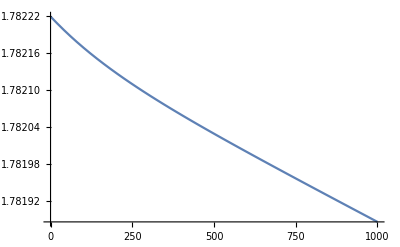

(√α (9.11×10^-27 ϕg[(1000001 rE)/1000000]-9.11×10^-27 ϕg[rE+Δr]+(((-4.555×10^-27+0.5 meD) rE+(-4.555×10^-27+0.5 meD) λout) ϕg[rE]+ⅇ^(rE/(1000000 λout)) (4.555×10^-27+0.500001 meD) rE λout ϕg'[(1000001 rE)/1000000])/(1. rE+0.999999 λout)))/(e √αD)

$Assumptions::fas: Warning: one or more assumptions evaluated to False.

General::ivar: 6.37101×10^6 is not a valid variable.

1.78222-5.59518×10^-7 Δr-4.39113×10^-14 Δr^2

1.78222-5.59518×10^-7 Δr-4.39113×10^-14 Δr^2

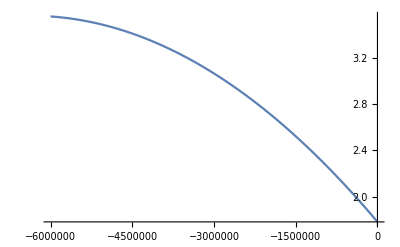

```mathematica
(*ϕEtest=ϕE/.ϕEsol/.solrepl/.SIConstRepl/.λrepl/.ϕg->Function[{r},Assuming[Δr<0,Vgrav[r]//Simplify]]//Simplify//PowerExpand
Assuming[r>rE,ϕanalyticsol//Simplify]/.solrepl/.SIConstRepl/.λrepl/.ϕg->Function[{r},Assuming[Δr>0,Vgrav[r]//Simplify]]//Simplify//PowerExpand
*)
Assuming[r>rE,ϕanalyticsol//Simplify](*/.Δr->0*)/.ϕgE->ϕg[rE(1+10^-6)]//Simplify//PowerExpand//Simplify
%/.solrepl/.SIConstRepl/.λrepl/.ϕg->Function[{r},Assuming[r>"rE"/.EarthRepl,Vgrav[r]//Simplify]]//Simplify//PowerExpand
ϕouttest=%
Plot[%,{Δr,0,1000}]
(*Assuming[r<rE,ϕanalyticsol//Simplify]/.solrepl/.SIConstRepl/.λrepl/.ϕg->Function[{r},Assuming[Δr<0,Vgrav[r]//Simplify]]//Simplify//PowerExpand*)
Assuming[r<=rE,ϕanalyticsol//Simplify](*/.Δr->0*)/.ϕgE->ϕg[rE(1+10^-6)]//Simplify//PowerExpand//Simplify
%/.solrepl/.SIConstRepl/.λrepl/.ϕg->Function[{r},Assuming[r<"rE"/.EarthRepl,Vgrav[r]//Simplify]]//Simplify//PowerExpand
ϕintest=%
Plot[%,{Δr,-6000000,0}]
```

```mathematica
"check JCs (dependent on the numerical fudge parameter about rE when evaluating ϕg)"
ϕouttest/.Δr->0
ϕintest/.Δr->0
D[ϕouttest,Δr]
D[ϕintest,Δr]
%%/.Δr->0/.SIConstRepl
%%/.Δr->0/.SIConstRepl
```

check JCs (dependent on the numerical fudge parameter about rE when evaluating ϕg)

1.78222

1.78222

-(1.13542×10^7+348.321 ⅇ^(-0.00529281 Δr))/((6.371×10^6+Δr)^2)-(1.8436 ⅇ^(-0.00529281 Δr))/(6.371×10^6+Δr)

-5.59518×10^-7-8.78226×10^-14 Δr

-5.69113×10^-7

-5.59518×10^-7

```mathematica
Clear[ϕtotalsubbed]
ϕtotalsubbed= Piecewise[{{ϕouttest,Δr>0},{ϕintest,Δr<0}}]
(*ϕtotalsubbed[Δr_] := If[Δr>0,ϕouttest,ϕintest]*)
(*ϕintest/.Δr->0*)
Plot[(*If[Δr>0,ϕouttest,ϕintest]*)ϕtotalsubbed,{Δr,-"rE"/.EarthRepl,10^7}]
Plot[βD(("e"/.SIConstRepl)(*If[Δr>0,ϕouttest,ϕintest]*)ϕtotalsubbed+mpD Vgrav["rE"+Δr/.EarthRepl]),{Δr,-"rE"/.EarthRepl,10^7.5},PlotRange->All]
"This is consistent with what I found for the thermalized regime"
"But it is inconsistent with the condition of no binding potential for capture."
```

Piecewise[{{(1.13542×10^7+348.321 ⅇ^(-0.00529281 Δr))/(6.371×10^6+Δr), Δr>0}, {1.78222-5.59518×10^-7 Δr-4.39113×10^-14 Δr^2, Δr<0}, {0, True}}]

-Graphics-

-Graphics-

This is consistent with what I found for the thermalized regime

But it is inconsistent with the condition of no binding potential for capture.

#### Plot the result for the different pD temperature solution

```mathematica
"As a test case consider the TH disc"
foverv = 5
mpD =foverv(2 10^3"m"/.Constants`SIConstRepl)
meDbympD=10^-4
βD="βD"/.Quiet@Capture`v0toβD[20 10^3,mpD,mpD meDbympD]
(*ϕEomIn=Assuming[r<"rE"/.Constants`EarthRepl (*1*),Getϕeom[mpD,10^0,meDbympD,<|"βp"->"βcore"/.Constants`EarthRepl,"βe"->βD|>,(*10^-9*)10^-2]//Simplify];*)
```

As a test case consider the TH disc

5

9.11×10^-27

1/10000

1.64638×10^18

```mathematica
(G M)/rE==(11200)^2/2
```

```mathematica
ϕanalyticsol


Assuming[ϵ>0,Normal@Series[δϕout/.r->Δr+rE/.rE->λin Log[ϵ],{ϵ,∞,1}]/.ϵ->E^(rE/λin)]//PowerExpand//Expand
```

Piecewise[{{((G M (9.11×10^-27-meD) √α √(αD/α))/(2 √αD (rE+λout))+9.11×10^-27 ϕgE-9.11×10^-27 ϕg[r]+(9.11×10^-27 rE λout ϕg'[rE])/(rE+λout))/(e √(αD/α)), r≤rE}, {(G M (-9.11×10^-27+meD) √α (-1+(ⅇ^((-r+rE)/λout) λout)/(rE+λout))+(1.822×10^-26 ⅇ^((-r+rE)/λout) rE^2 √αD λout ϕg'[rE])/(√(αD/α) (rE+λout)))/(2 e r √αD), r>rE}, {0, True}}]

(4.555×10^-27 G M √α)/(e √αD (rE+Δr))-(4.555×10^-27 ⅇ^(-Δr/λout) G M √α)/(e √αD (rE+Δr))-(0.5 G M meD √α)/(e √αD (rE+Δr))+(0.5 ⅇ^(-Δr/λout) G M meD √α)/(e √αD (rE+Δr))+(1. ⅇ^(-Δr/λout) rE ϕE)/(rE+Δr)

{λin→188.936,λout→188.936,rE→6.371×10^6}

{ϕE→-2.84146×10^-8 ϕg[6.371×10^6]+5.5536×10^-6 ϕg'[6.37101×10^6]}

Piecewise[{{(1.13542×10^7+348.321 ⅇ^(-0.00529281 Δr))/(6.371×10^6+Δr), Δr>0}, {1.78222-5.59518×10^-7 Δr-4.39113×10^-14 Δr^2, Δr<0}, {0, True}}]

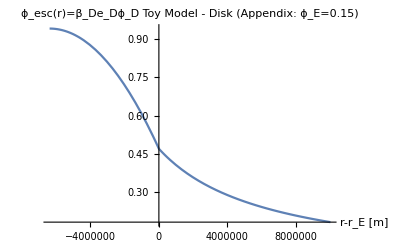

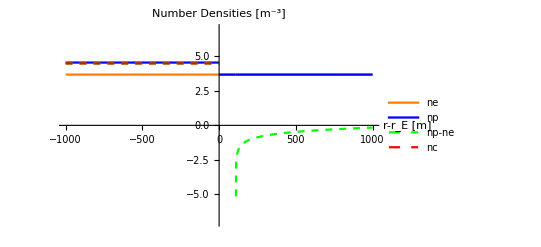

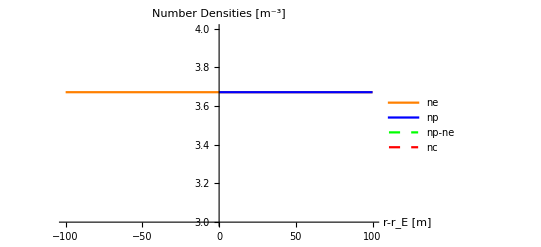

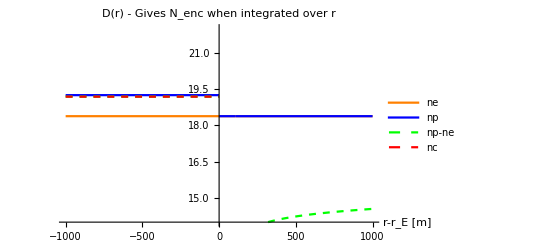

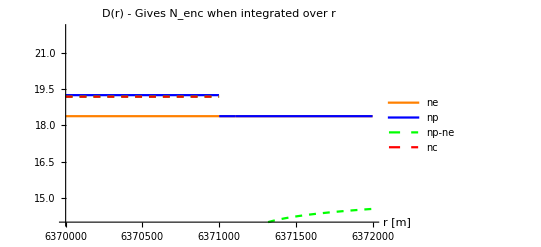

We can also check our approximation of flat gravitational potential over these length scales (not surprising, we can think of our constant potential assumption as working at leading order in λ/r_E<<1)

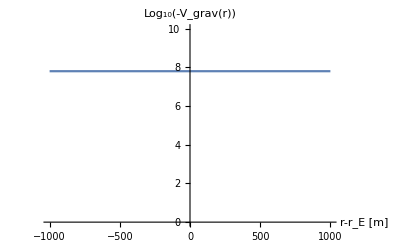

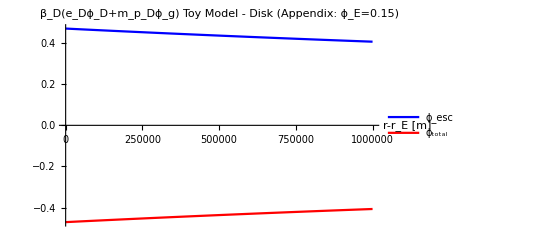

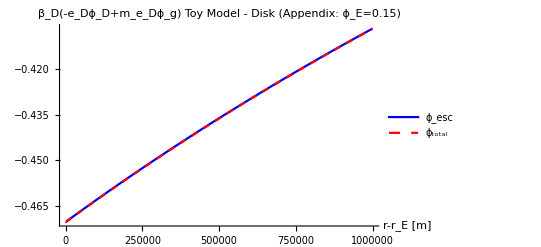

```mathematica
solrepl = {βe->βD,βpout->βD,βpin->βcore,meD->mpD meDbympD,(*ϕg->-(11200)^2/2,*)ϕg'[rE]->-9.8,G->rE/M(11200)^2/2,ϕgE->(11200)^2/2,α->αD,nF->naDM[fD/.fD->0.05,mpD (1+ meDbympD)]};
λrepl={λin->(λDsol/.βp->βpin),λout->(λDsol/.βp->βpout),rE->("rE"/.EarthRepl)}/.solrepl/.SIConstRepl/.nF->naDM[fD/.fD->0.05,mpD (1+ meDbympD)]
ϕEsol/.solrepl/.SIConstRepl/.λrepl//Simplify//PowerExpand
(*δϕin/.solrepl/.SIConstRepl/.%(*//ExpToTrig*)//Simplify;
(*-(0.5576037085544936(1- ⅇ^((2 rE)/λin)) r+0.4049687299775784 ⅇ^((-r+rE)/λin) (1- ⅇ^((2 r)/λin)) rE)/((-1.+ⅇ^((2 rE)/λin)) r)//Simplify*)
Assuming[ϵ>0,Normal@Series[%/.rE->λin Log[ϵ],{ϵ,∞,1}]/.ϵ->E^(rE/λin)]//PowerExpand//Expand;
δϕout/.solrepl/.SIConstRepl/.%%%(*//ExpToTrig*)//Simplify//PowerExpand;
ϕtotalsol=Piecewise[{{%%,r<=rE},{%,r>rE}}]*)
(*Assuming[ϵ>0,Normal@Series[ϕanalyticsol/.r->Δr+rE/.rE->λin Log[ϵ],{ϵ,∞,1}]/.ϵ->E^(rE/λin)]//PowerExpand//Expand*)
(*ϕanalyticsubbed=ϕanalyticsol/.ϕg->Function[{r},Vgrav[r]]/.solrepl/.SIConstRepl/.λrepl//Simplify//PowerExpand*)
ϕtotalsubbed
(*Quiet@Plot[("e"/.SIConstRepl)βD ϕtotalsol/.λrepl/.rE->("rE"/.EarthRepl)/.r->Δr+"rE"/.EarthRepl,{Δr,-10^6,10^7},PlotRange->{0,0.5},PlotLabel->"ϕ_esc(r)=β_De_Dϕ_D Toy Model - Disk (Appendix: ϕ_E=0.15)",AxesLabel->{"r-r_E [m]"}]*)
Quiet@Plot[("e"/.SIConstRepl)βD ϕtotalsubbed/.λrepl/.rE->("rE"/.EarthRepl)(*/.r->Δr+"rE"*)/.EarthRepl,{Δr,-"rE"/.EarthRepl,10^7},PlotRange->All,PlotLabel->"ϕ_esc(r)=β_De_Dϕ_D Toy Model - Disk (Appendix: ϕ_E=0.15)",AxesLabel->{"r-r_E [m]"}]
(*Quiet@Plot[("e"/.SIConstRepl)βD ϕtotalsubbed/.λrepl/.rE->("rE"/.EarthRepl)/.r->Δr+"rE"/.EarthRepl,{Δr,-10^2,10^2},PlotRange->{0,0.5},PlotLabel->"ϕ_esc(r)=β_De_Dϕ_D Toy Model - Disk (Appendix: ϕ_E=0.15)",AxesLabel->{"r-r_E [m]"}]*)
variousns={ne,nc+np,nc+np-ne,nc}/.{np->nF E^(- βp (ϵ √αDbyα"e"ϕ[r] + mpD ϕg[r])),ne->nF E^(-βe(-ϵ √αDbyα"e"ϕ[r]+mpD meDbympD ϕg[r])),nc->Boole[r<"rE"/.EarthRepl]ncapsubbed}/.βp->(*Piecewise[{{βpin,r<rE},{βpout,r>rE}}]*)βD/.{nF->naDM[fD/.fD->0.05,mpD (1+ meDbympD)],ϵ->1,αDbyα->1,ϕg->Function[{r},-(11200)^2/2],ϕ[r]->ϕtotalsubbed};
numsol=%/.solrepl/.SIConstRepl/.λrepl/.rE->("rE"/.EarthRepl)/.r->Δr+"rE"/.EarthRepl;
Quiet@Plot[Evaluate@(Log10@%),{Δr,-10^3,10^3},PlotRange->{-7,7},PlotStyle->#,PlotLegends->LineLegend[#,{"ne","np","np-ne","nc"}],AxesLabel->{"r-r_E [m]"},PlotLabel->"Number Densities [m^-3]"]&@{Orange,Blue,Directive[Dashed,Green],Directive[Dashed,Red]}
Quiet@Plot[Evaluate@(Log10@%%),{Δr,-10^2,10^2},PlotRange->{3,4},PlotStyle->#,PlotLegends->LineLegend[#,{"ne","np","np-ne","nc"}],AxesLabel->{"r-r_E [m]"},PlotLabel->"Number Densities [m^-3]"]&@{Orange,Blue,Directive[Dashed,Green],Directive[Dashed,Red]}
Quiet@Plot[Evaluate@(Log10[%%% 4π (("rE"/.EarthRepl)+Δr)^2]),{Δr,-10^3,10^3},PlotRange->{14,22},PlotStyle->#,PlotLegends->LineLegend[#,{"ne","np","np-ne","nc"}],AxesLabel->{"r-r_E [m]"},PlotLabel->"D(r) - Gives N_enc when integrated over r"]&@{Orange,Blue,Directive[Dashed,Green],Directive[Dashed,Red]}
Quiet@Plot[Evaluate@(Log10[%%%% 4π (r)^2/.Δr->r-("rE"/.EarthRepl)]),{r,("rE"/.EarthRepl)-10^3,("rE"/.EarthRepl)+10^3},PlotRange->{14,22},PlotStyle->#,PlotLegends->LineLegend[#,{"ne","np","np-ne","nc"}],AxesLabel->{"r [m]"},PlotLabel->"D(r) - Gives N_enc when integrated over r"]&@{Orange,Blue,Directive[Dashed,Green],Directive[Dashed,Red]}
"We can also check our approximation of flat gravitational potential over these length scales (not surprising, we can think of our constant potential assumption as working at leading order in λ/r_E<<1)"
Plot[Log10[-Vgrav[Δr+"rE"/.EarthRepl]],{Δr,-10^3,10^3},PlotRange->{0,10},PlotLabel->"Log_10(-V_grav(r))",AxesLabel->{"r-r_E [m]"}]
(*Quiet@Plot[βD (("e"/.SIConstRepl)ϕtotalsol+mpD Vgrav[Δr+"rE"/.EarthRepl])/.λrepl/.rE->("rE"/.EarthRepl)/.r->Δr+"rE"/.EarthRepl,{Δr,-10^2,10^2},(*PlotRange->{0,0.5},*)PlotLabel->"ϕ_(esc, total)(r)=β_D(e_Dϕ_D+m_p_Dϕ_g) Toy Model - Disk (Appendix: ϕ_E=0.15)",AxesLabel->{"r-r_E [m]"}]
*)
Quiet@Plot[Evaluate@({βD ("e"/.SIConstRepl)ϕtotalsol,βD (("e"/.SIConstRepl)ϕtotalsol+mpD Vgrav[Δr+"rE"/.EarthRepl])}/.λrepl/.rE->("rE"/.EarthRepl)/.r->Δr+"rE"/.EarthRepl),{Δr,-10^6,10^6},(*PlotRange->{0,0.5},*)PlotLabel->"β_D(e_Dϕ_D+m_p_Dϕ_g) Toy Model - Disk (Appendix: ϕ_E=0.15)",AxesLabel->{"r-r_E [m]"},PlotStyle->#,PlotLegends->LineLegend[#,{"ϕ_esc","ϕ_total"}],PlotRange->All]&@{Blue,Red}
Quiet@Plot[Evaluate@({-βD ("e"/.SIConstRepl)ϕtotalsol,βD (-("e"/.SIConstRepl)ϕtotalsol+mpD meDbympD Vgrav[Δr+"rE"/.EarthRepl])}/.λrepl/.rE->("rE"/.EarthRepl)/.r->Δr+"rE"/.EarthRepl),{Δr,-10^6,10^6},(*PlotRange->{0,0.5},*)PlotLabel->"β_D(-e_Dϕ_D+m_e_Dϕ_g) Toy Model - Disk (Appendix: ϕ_E=0.15)",AxesLabel->{"r-r_E [m]"},PlotStyle->#,PlotLegends->LineLegend[#,{"ϕ_esc","ϕ_total"}],PlotRange->All]&@{Blue,Directive[Red,Dashed]}
```

```mathematica
Assuming[r<"rE"/.EarthRepl,ncapsubbed//Simplify]//Simplify
```

-714.741+49275. ⅇ^(-1.15892×10^-14 r^2)

```mathematica
numsol[[3]]
```

-2930.55 ⅇ^(-1.64638×10^18 (-5.71379×10^-23-1.60289×10^-19 (Piecewise[{{(1.13542×10^7+348.321 ⅇ^(-0.00529281 Δr))/(6.371×10^6+Δr), Δr>0}, {1.78222-5.59518×10^-7 Δr-4.39113×10^-14 Δr^2, Δr<0}, {0, True}}])))+2930.55 ⅇ^(-1.64638×10^18 (-5.71379×10^-19+1.60289×10^-19 (Piecewise[{{(1.13542×10^7+348.321 ⅇ^(-0.00529281 Δr))/(6.371×10^6+Δr), Δr>0}, {1.78222-5.59518×10^-7 Δr-4.39113×10^-14 Δr^2, Δr<0}, {0, True}}])))+(-714.741+49275. ⅇ^(-1.15892×10^-14 (6.371×10^6+Δr)^2)) Boole[6.371×10^6+Δr<6.371×10^6]

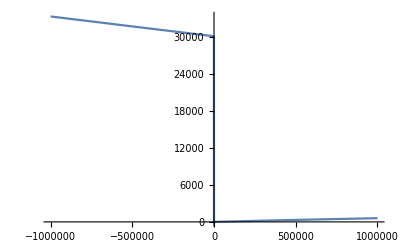

```mathematica
Plot[numsol[[3]],{Δr,-10^6,10^6},PlotRange->All]
```

```mathematica
ncapsubbed/.r->Δr
```

Piecewise[{{Δr>6.371×10^6, -714.741+12015.7 ⅇ^(5.99384×10^6/Δr)}, {Δr<6.371×10^6, -714.741+49275. ⅇ^(-1.15892×10^-14 Δr^2)}, {0, True}}]

```mathematica
D[ϕtotalsol,r]
%/.λrepl
%/.r->"rE"/.EarthRepl
```

Piecewise[{{(0.0177783 ⅇ^(-r/λin-rE/λin) rE)/r^2-(0.0177783 ⅇ^(r/λin-rE/λin) rE)/r^2+(0.0177783 ⅇ^(-r/λin-rE/λin) rE)/(r λin)+(0.0177783 ⅇ^(r/λin-rE/λin) rE)/(r λin), r-rE≤0}, {(1.17266 ⅇ^((-r+rE)/λout) rE)/r^2+(1.17266 ⅇ^((-r+rE)/λout) rE)/(r λout), r-rE>0}, {0, True}}]

Piecewise[{{(113266. ⅇ^(-2.9683×10^6-0.465909 r))/r^2-(113266. ⅇ^(-2.9683×10^6+0.465909 r))/r^2+(52771.4 ⅇ^(-2.9683×10^6-0.465909 r))/r+(52771.4 ⅇ^(-2.9683×10^6+0.465909 r))/r, -6.371×10^6+r≤0}, {(7.47099×10^6 ⅇ^(0.00706335 (6.371×10^6-r)))/r^2+(52770.2 ⅇ^(0.00706335 (6.371×10^6-r)))/r, -6.371×10^6+r>0}, {0, True}}]

General::munfl: Exp[-5.93661×10^6] is too small to represent as a normalized machine number; precision may be lost.

0.00828306

```mathematica
Ntotals=Assuming[Δr<0,numsol(4 π)/3("rE")^3/.EarthRepl//Simplify];
"The net dark charges in the earth are (assuming they stay flat when a gravitational profile is included):"
{Subscript[N, e],Subscript[N, p],Subscript[N, p]-Subscript[N, e]}==Ntotals
"For comparison the (1D) random walk model gives roughly"
Subscript[N, cap,e]==Subscript[n, F] Subscript[V, earth] ==(naDM[fD/.fD->0.05,mpD (1+ meDbympD)](4 π)/3("rE")^3 /.EarthRepl)
Subscript[N, cap,p]==Subscript[n, F] Subscript[V, earth] Subscript[β, earth]/Subscript[β, D]==(naDM[fD/.fD->0.05,mpD (1+ meDbympD)](4 π)/3("rE")^3 βcore/βD/.EarthRepl)
"So pretty close. This tells us that, as we might expect, the dark electrons are moving too fast and pass through the earth essentially unaffected, but that the dark electrons receive an enhancement given the shallow potential well in the earth."
"We can also see that the random walk model also predicts a neutral plasma in the no thermalization limit"
```

The net dark charges in the earth are (assuming they stay flat when a gravitational profile is included):

{N_e,N_p,-N_e+N_p}=={3.17469×10^24,6.11791×10^27,6.11474×10^27}

For comparison the (1D) random walk model gives roughly

N_(cap,e)==n_F V_earth==3.17439×10^24

N_(cap,p)==(n_F V_earth β_earth)/β_D==2.55241×10^25

So pretty close. This tells us that, as we might expect, the dark electrons are moving too fast and pass through the earth essentially unaffected, but that the dark electrons receive an enhancement given the shallow potential well in the earth.

We can also see that the random walk model also predicts a neutral plasma in the no thermalization limit

### Unit testing proper treatment - ∇T=0 - with ϕ not δϕ - Analytically

#### The EOM and solution - assuming fixed grav density

I am claiming that a given profile will quickly thermalize in the Earth, this can be checked 
- this may be a good time to check self interactions. I’d imagine that the coulomb scattering rate is pretty high.
- we can treat them as hard spheres with radius of the screening length (inside that radius is roughly bare charge so you have a very high chance of scattering.)

assume equilibrium between exchange processes between the two populations locally. 

The local equilibrium condition, by definition means the rates will cancel so that there is no source. 

If I can give a convincing proof of this then I will just need to add in another population of flowing dark protons (I think this is imposing stationary ansatz, a source will only matter if static but not stationary). But these will be at a higher temperature, and so will necessarily be subdominant to the thermalized population - this will however be conditional on us knowing the captured population.

```mathematica
Clear[λD,λDsol,mpD]
"We assume that ∇T = 0 and use the no net diffusion condition for species i"
∇Log[Subscript[n, i][r] (Subscript[T, i][r])^(κ+1)] == -(∇ Subscript[V, i][r])/(Subscript[T, i][r])
"to get the equilibrium number densities for p_D and e_D"
Subscript[n, i][r]==Subscript[n, F] E^(-Subscript[β, i] Subscript[V, i][r])
"Where n_F is the number density far from Earth. These agree with the values found in the appendix. Plugging into the Poisson equation"
Subscript[e, D] HoldForm[Δ δϕ[r]]== ∑_i Subscript[e, D]^2 Subscript[n, i][r]
"we then find"
ϕEOM =(-("e")/r^2 √(αD/α)D[r^2 δϕ'[r],r]==- ("e")^2/("ϵ0")αD/α ne+("e")^2/("ϵ0")αD/α np)/.{np->nF E^(- βp (√(αD/α)"e"δϕ[r] + mpD ϕg[r])),ne->nF E^(-βe (-√(αD/α)"e"δϕ[r]+meD ϕg[r]))}/.ϕg->Function[{r},ϕg]
"The Poisson equation is non-linear, so we expand in small ϕ and look for a consistently small solution. This gives a linear 2nd order inhomogeneous ODE for ϕ"
Series[ϕEOM,{δϕ[r],0,1}]//Normal
"Not surprisingly, this can be understood as a sourced Debeye equation. With the following Debeye length. For β_p=β_e and ϕ_g=0, it reduces to the one given in the appendix."
λDsol=(("e" ⅇ^(-1/2 (meD βe+mpD βp) ϕg) √nF √αD √(ⅇ^(mpD βp ϕg) βe+ⅇ^(meD βe ϕg) βp))/(√("ϵ0") √α))^-1;
λD==λDsol
Out[-4]/.Solve[λD==λDsol,nF][[1]]//Simplify//Expand;
"If ϕ_g is taken to be constant (which should be qualitatively correct over a small range given that λ_D << r_E), then this can be solved analytically to give"
δϕsol = DSolve[%%,δϕ[r],r][[1]]/.C[2]->2/λD C[2]//PowerExpand//Simplify
"Note that the particular solution vanishes for ϕ_g=0. We will find that ϕ_g!= 0 allows us to consistently determine ϕ_E and the entire solution in terms of microphysics parameters."
```

We assume that ∇T = 0 and use the no net diffusion condition for species i

∇Log[n_i[r] T_i[r]^(1+κ)]==-(∇V_i[r])/T_i[r]

to get the equilibrium number densities for p_D and e_D

n_i[r]==ⅇ^(-β_i V_i[r]) n_F

Where n_F is the number density far from Earth. These agree with the values found in the appendix. Plugging into the Poisson equation

(Δ δϕ[r]) e_D==∑_i e_D^2 n_i[r]

we then find

-(e √(αD/α) (2 r δϕ'[r]+r^2 δϕ''[r]))/r^2==-(e^2 ⅇ^(-βe (meD ϕg-e √(αD/α) δϕ[r])) nF αD)/(ϵ0 α)+(e^2 ⅇ^(-βp (mpD ϕg+e √(αD/α) δϕ[r])) nF αD)/(ϵ0 α)

The Poisson equation is non-linear, so we expand in small ϕ and look for a consistently small solution. This gives a linear 2nd order inhomogeneous ODE for ϕ

-(e √(αD/α) (2 r δϕ'[r]+r^2 δϕ''[r]))/r^2==-(e^2 ⅇ^(-meD βe ϕg) nF αD)/(ϵ0 α)+(e^2 ⅇ^(-mpD βp ϕg) nF αD)/(ϵ0 α)-(e^3 ⅇ^(-meD βe ϕg-mpD βp ϕg) nF αD √(αD/α) (ⅇ^(mpD βp ϕg) βe+ⅇ^(meD βe ϕg) βp) δϕ[r])/(ϵ0 α)

Not surprisingly, this can be understood as a sourced Debeye equation. With the following Debeye length. For β_p=β_e and ϕ_g=0, it reduces to the one given in the appendix.

λD==(√ϵ0 ⅇ^(1/2 (meD βe+mpD βp) ϕg) √α)/(e √nF √αD √(ⅇ^(mpD βp ϕg) βe+ⅇ^(meD βe ϕg) βp))

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

If ϕ_g is taken to be constant (which should be qualitatively correct over a small range given that λ_D << r_E), then this can be solved analytically to give

{δϕ[r]→((ⅇ^(meD βe ϕg)-ⅇ^(mpD βp ϕg)) √α)/(e √αD (ⅇ^(mpD βp ϕg) βe+ⅇ^(meD βe ϕg) βp))+(ⅇ^(-r/λD) C[1]+ⅇ^(r/λD) C[2])/r}

Note that the particular solution vanishes for ϕ_g=0. We will find that ϕ_g!= 0 allows us to consistently determine ϕ_E and the entire solution in terms of microphysics parameters.

#### solve BCS - assuming each species has a the same constant temperature in both regions

```mathematica
Clear[rE]
"Solve for δϕ in the Earth"
δϕ[r]/.δϕsol(*/.αD->α*)
Series[D[%,r],{r,0,0}]
Solve[Normal@% == 0,C[1]]
 Solve[(Out[-3]/.%[[1]]/.r->rE)==ϕE,C[2]]//Simplify
δϕin=Out[-4]/.%%[[1]]/.%[[1]]/.{β->βin,λD->λin}//Simplify//ExpToTrig//Simplify
```

Solve for δϕ in the Earth

((-ⅇ^(mpD βe ϕg)+ⅇ^(meD βp ϕg)) √α)/(e √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))+(ⅇ^(-r/λD) C[1]+ⅇ^(r/λD) C[2])/r

(-C[1]-C[2])/r^2+(C[1]+C[2])/(2 λD^2)+O[r]^1

{{C[1]→-C[2]}}

{{C[2]→(ⅇ^(rE/λD) rE (ⅇ^(meD βp ϕg) (-√α+e √αD βe ϕE)+ⅇ^(mpD βe ϕg) (√α+e √αD βp ϕE)))/(e (-1+ⅇ^((2 rE)/λD)) √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))}}

-(((-1+Coth[rE/λin]) (r √α (-1+Cosh[(2 rE)/λin]+Sinh[(2 rE)/λin]) (Cosh[mpD βe ϕg]-Cosh[meD βp ϕg]+Sinh[mpD βe ϕg]-Sinh[meD βp ϕg])+rE (Cosh[(r-rE)/λin]-Sinh[(r-rE)/λin]) ((√α+e √αD βp ϕE) (Cosh[mpD βe ϕg]+Sinh[mpD βe ϕg])+(-√α+e √αD βe ϕE) (Cosh[meD βp ϕg]+Sinh[meD βp ϕg]))-rE (Cosh[(r+rE)/λin]+Sinh[(r+rE)/λin]) ((√α+e √αD βp ϕE) (Cosh[mpD βe ϕg]+Sinh[mpD βe ϕg])+(-√α+e √αD βe ϕE) (Cosh[meD βp ϕg]+Sinh[meD βp ϕg]))))/(2 e r √αD (βp Cosh[mpD βe ϕg]+βe Cosh[meD βp ϕg]+βp Sinh[mpD βe ϕg]+βe Sinh[meD βp ϕg])))

```mathematica
δϕin/.r->rE//Simplify
Limit[D[δϕin,r]//Simplify,r->0]
```

ϕE

0

```mathematica
"Solve δϕ for r>rE"
δϕ[r]/.δϕsol(*/.αD->α*)(*/.ρg->0*)
(*%/.Solve[nF==1/(β λD^2)(("e")^2/("ϵ0")√(αD/α))^-1,λD][[2]]/.αD->α*)
"δϕ->0 as r->∞ gives"
%%/.C[2]->0
"δϕ[rE]=ϕE gives"
Solve[(%%/.r->rE)==ϕE,C[1]]
δϕout=Out[-3]/.%[[1]]/.λD->λout//Simplify
```

Solve δϕ for r>rE

((-ⅇ^(mpD βe ϕg)+ⅇ^(meD βp ϕg)) √α)/(e √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))+(ⅇ^(-r/λD) C[1]+ⅇ^(r/λD) C[2])/r

δϕ->0 as r->∞ gives

((-ⅇ^(mpD βe ϕg)+ⅇ^(meD βp ϕg)) √α)/(e √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))+(ⅇ^(-r/λD) C[1])/r

δϕ[rE]=ϕE gives

{{C[1]→(ⅇ^(rE/λD) rE (ⅇ^(mpD βe ϕg) √α-ⅇ^(meD βp ϕg) √α+e ⅇ^(meD βp ϕg) √αD βe ϕE+e ⅇ^(mpD βe ϕg) √αD βp ϕE))/(e √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))}}

(ⅇ^(-r/λout) (-ⅇ^(r/λout+mpD βe ϕg) r √α+ⅇ^(r/λout+meD βp ϕg) r √α-ⅇ^(rE/λout+meD βp ϕg) rE (√α-e √αD βe ϕE)+ⅇ^(rE/λout+mpD βe ϕg) rE (√α+e √αD βp ϕE)))/(e r √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))

```mathematica
"The condition that the charge distribution is regular at the interface gives the condition on ϕE"
ϕEsol=Solve[(D[δϕin-δϕout,r]/.r->rE)==0,ϕE][[1]]//Simplify
```

The condition that the charge distribution is regular at the interface gives the condition on ϕE

{ϕE→((-ⅇ^(mpD βe ϕg)+ⅇ^(meD βp ϕg)) √α)/(e √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))}

```mathematica
δϕout//Expand
ⅇ^(rE/λout+meD βp ϕg) rE (-1+"e" βe ϕE)+ⅇ^(rE/λout+mpD βe ϕg) rE (1+"e" βp ϕE)/.ϕEsol//Simplify
-ⅇ^(r/λout+mpD βe ϕg) r+ⅇ^(r/λout+meD βp ϕg) r/.ϕEsol//Simplify
δϕout/.ϕEsol
%//Simplify
```

-(ⅇ^(mpD βe ϕg) √α)/(e √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))+(ⅇ^(meD βp ϕg) √α)/(e √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))+(ⅇ^(-r/λout+rE/λout+mpD βe ϕg) rE √α)/(e r √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))-(ⅇ^(-r/λout+rE/λout+meD βp ϕg) rE √α)/(e r √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))+(ⅇ^(-r/λout+rE/λout+meD βp ϕg) rE βe ϕE)/(r (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))+(ⅇ^(-r/λout+rE/λout+mpD βe ϕg) rE βp ϕE)/(r (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))

(ⅇ^(rE/λout) (ⅇ^(mpD βe ϕg)-ⅇ^(meD βp ϕg)) rE (-√α+√αD))/(√αD)

-ⅇ^(r/λout) (ⅇ^(mpD βe ϕg)-ⅇ^(meD βp ϕg)) r

(ⅇ^(-r/λout) (-ⅇ^(r/λout+mpD βe ϕg) r √α+ⅇ^(r/λout+meD βp ϕg) r √α-ⅇ^(rE/λout+meD βp ϕg) rE (√α-((-ⅇ^(mpD βe ϕg)+ⅇ^(meD βp ϕg)) √α βe)/(ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))+ⅇ^(rE/λout+mpD βe ϕg) rE (√α+((-ⅇ^(mpD βe ϕg)+ⅇ^(meD βp ϕg)) √α βp)/(ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))))/(e r √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))

((-ⅇ^(mpD βe ϕg)+ⅇ^(meD βp ϕg)) √α)/(e √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))

```mathematica
"So it has a constant potential in and out of the Earth"
δϕin/.ϕEsol//Simplify//TrigToExp//Simplify
δϕout/.ϕEsol//Simplify
"And they are equal!"
```

So it has a constant potential in and out of the Earth

-((-1+ⅇ^((mpD βe-meD βp) ϕg)) √α)/(e √αD (βe+ⅇ^((mpD βe-meD βp) ϕg) βp))

((-ⅇ^(mpD βe ϕg)+ⅇ^(meD βp ϕg)) √α)/(e √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))

And they are equal!

So potentials are flat in both regions. Question is: is the plasma neutral?

```mathematica
"The net charge density is"
Series[- ne+np/.{np->nF E^(- βe (√(αD/α)"e"δϕ[r] + mpD ϕg[r])),ne->nF E^(-βp (-√(αD/α)"e"δϕ[r]+meD ϕg[r]))},{δϕ[r],0,1}]//Normal
%/.ϕg->Function[{r},ϕg]/.δϕ[r]->(δϕout/.ϕEsol)//Simplify
%//PowerExpand
Out[-3]/.ϕg->Function[{r},ϕg]/.δϕ[r]->(δϕin/.ϕEsol)//Simplify
%//PowerExpand
"So yes, the plasma is neutral in both regions"
```

The net charge density is

ⅇ^(-mpD βe ϕg[r]) nF-ⅇ^(-meD βp ϕg[r]) nF+(-e ⅇ^(-mpD βe ϕg[r]) nF √(αD/α) βe-e ⅇ^(-meD βp ϕg[r]) nF √(αD/α) βp) δϕ[r]

(ⅇ^(-((mpD βe+meD βp) ϕg)) (-ⅇ^(mpD βe ϕg)+ⅇ^(meD βp ϕg)) nF (√αD-√α √(αD/α)))/(√αD)

0

(ⅇ^(-((mpD βe+meD βp) ϕg)) (-ⅇ^(mpD βe ϕg)+ⅇ^(meD βp ϕg)) nF (√αD-√α √(αD/α)))/(√αD)

0

So yes, the plasma is neutral in both regions

#### solve BCS - assuming each species has a different constant temperature in both regions

```mathematica
Clear[rE]
"We will solve for ϕ in and out of the Earth, and use the junction conditions to stitch them together. Doing so will determine ϕ_E. We will also use a toy model of thermalization; we assume β_p=β_E in the Earth and β_p=β_D out of the Earth, whereas β_e=β_D everywhere. \n Let's start with the solution inside the Earth"
δϕ[r]/.δϕsol(*/.αD->α*)
"The integration constants are fixed by imposing that there is no cusp (so no singular charge density) at r=0"
Series[D[%%,r],{r,0,0}]
Solve[Normal@% == 0,C[1]]
"As well as the condition that ϕ_in[r_E]=ϕ_E"
 Solve[(Out[-5]/.%%[[1]]/.r->rE)==ϕE,C[2]]//Simplify
δϕin=Out[-6]/.%%%[[1]]/.%[[1]]/.{βp->βpin,λD->λin}//Simplify;
```

We will solve for ϕ in and out of the Earth, and use the junction conditions to stitch them together. Doing so will determine ϕ_E. We will also use a toy model of thermalization; we assume β_p=β_E in the Earth and β_p=β_D out of the Earth, whereas β_e=β_D everywhere. 
 Let's start with the solution inside the Earth

((ⅇ^(meD βe ϕg)-ⅇ^(mpD βp ϕg)) √α)/(e √αD (ⅇ^(mpD βp ϕg) βe+ⅇ^(meD βe ϕg) βp))+(ⅇ^(-r/λD) C[1]+ⅇ^(r/λD) C[2])/r

The integration constants are fixed by imposing that there is no cusp (so no singular charge density) at r=0

(-C[1]-C[2])/r^2+(C[1]+C[2])/(2 λD^2)+O[r]^1

{{C[1]→-C[2]}}

As well as the condition that ϕ_in[r_E]=ϕ_E

{{C[2]→(ⅇ^(rE/λD) rE (ⅇ^(mpD βp ϕg) (√α+e √αD βe ϕE)+ⅇ^(meD βe ϕg) (-√α+e √αD βp ϕE)))/(e (-1+ⅇ^((2 rE)/λD)) √αD (ⅇ^(mpD βp ϕg) βe+ⅇ^(meD βe ϕg) βp))}}

```mathematica
"Quick sanity check that our boundary conditions have been correctly imposed"
δϕin/.r->rE//Simplify
Limit[D[δϕin,r]//Simplify,r->0]
```

Quick sanity check that our boundary conditions have been correctly imposed

ϕE

0

```mathematica
Clear[mpD]
"Now we do the same thing outside the Earth. "
δϕ[r]/.δϕsol;
"δϕ->0 as r->∞ gives"
%%/.C[2]->0
"δϕ[rE]=ϕE gives"
Solve[(%%/.r->rE)==ϕE,C[1]]//Simplify
δϕout=Out[-3]/.%[[1]]/.{βp->βpout,λD->λout}//Simplify;
```

Now we do the same thing outside the Earth.

δϕ->0 as r->∞ gives

((ⅇ^(meD βe ϕg)-ⅇ^(mpD βp ϕg)) √α)/(e √αD (ⅇ^(mpD βp ϕg) βe+ⅇ^(meD βe ϕg) βp))+(ⅇ^(-r/λD) C[1])/r

δϕ[rE]=ϕE gives

{{C[1]→(ⅇ^(rE/λD) rE (ⅇ^(mpD βp ϕg) (√α+e √αD βe ϕE)+ⅇ^(meD βe ϕg) (-√α+e √αD βp ϕE)))/(e √αD (ⅇ^(mpD βp ϕg) βe+ⅇ^(meD βe ϕg) βp))}}

```mathematica
"For the junction conditions at r_E, we have continuity and no singular charge distributions. We've already imposed continuity above, so we only need to impose that the radial derivative of the potential is continuous. This gives an explict, albeit complicated and unilluminating form for ϕ_E"
ϕEsol=Solve[(D[δϕin-δϕout,r]/.r->rE)==0,ϕE][[1]]//FullSimplify
```

For the junction conditions at r_E, we have continuity and no singular charge distributions. We've already imposed continuity above, so we only need to impose that the radial derivative of the potential is continuous. This gives an explict, albeit complicated and unilluminating form for ϕ_E

{ϕE→(√α (-ⅇ^(mpD (βpin+βpout) ϕg) rE βe (-λin+λout+ⅇ^((2 rE)/λin) (λin+λout))+ⅇ^(2 meD βe ϕg) ((-1+ⅇ^((2 rE)/λin)) (βpin-βpout) λin λout+rE (-βpin λin+βpout λout+ⅇ^((2 rE)/λin) (βpin λin+βpout λout)))+2 ⅇ^(rE/λin+meD βe ϕg) (-rE (-ⅇ^(mpD βpout ϕg) βe+ⅇ^(mpD βpin ϕg) βpout) λout Cosh[rE/λin]+λin (-ⅇ^(mpD βpout ϕg) (rE βpin+(βe+βpin) λout)+ⅇ^(mpD βpin ϕg) (rE βe+(βe+βpout) λout)) Sinh[rE/λin])))/(e rE √αD (ⅇ^(mpD βpin ϕg) βe+ⅇ^(meD βe ϕg) βpin) (ⅇ^(mpD βpout ϕg) βe+ⅇ^(meD βe ϕg) βpout) (-λin+λout+ⅇ^((2 rE)/λin) (λin+λout)))}

```mathematica
"As we mentioned above, taking ϕg->0 leads to ϕ_E=0"
ϕEnog=ϕEsol/.ϕg->0//Simplify
"This in turn leads the potential to vanish everywhere."
Subscript[ϕ, in]==(δϕin/.ϕg->0//Simplify)
Subscript[ϕ, out]==δϕout/.ϕg->0//Simplify
"And as we mentioned before, this neutralizes the plasma "
(Normal@Series[- ne+np/.{np->nF E^(- βp (√(αD/α)"e"δϕ[r] + mpD ϕg[r])),ne->nF E^(-βe (-√(αD/α)"e"δϕ[r]+meD ϕg[r]))},{δϕ[r],0,1}])/.ϕg->Function[{r},0]/.δϕ[r]->0//Simplify//PowerExpand
```

As we mentioned above, taking ϕg->0 leads to ϕ_E=0

{ϕE→0}

This in turn leads the potential to vanish everywhere.

ϕ_in==(ⅇ^((-r+rE)/λin) (-1+ⅇ^((2 r)/λin)) rE ϕE)/((-1+ⅇ^((2 rE)/λin)) r)

ϕ_out==(ⅇ^((-r+rE)/λout) rE ϕE)/r

And as we mentioned before, this neutralizes the plasma

0

```mathematica
Clear[mpD,βD]
"We can also see that taking β_i=β_D(ie. the no thermalization limit) gives"
ϕEnotherm=ϕEsol/.{βe->βD,βpin->βD,βpout->βD}//Simplify
"This in turn leads to a flat potential (just the inhomogeneous term)"
Subscript[ϕ, in]==(δϕin/.{βe->βD,βpin->βD,βpout->βD}/.%%//Simplify)
Subscript[ϕ, out]==(δϕout/.{βe->βD,βpin->βD,βpout->βD}/.%%%//Simplify)
"This also leads to a neutral plasma"
(Normal@Series[- ne+np/.{np->nF E^(- βp (√(αD/α)"e"δϕ[r] + mpD ϕg[r])),ne->nF E^(-βe (-√(αD/α)"e"δϕ[r]+meD ϕg[r]))},{δϕ[r],0,1}])/.ϕg->Function[{r},ϕg]/.{βe->βD,βp->βD,βpin->βD,βpout->βD}/.δϕ[r]->ϕE/.ϕEnotherm//Simplify//PowerExpand
```

We can also see that taking β_i=β_D(ie. the no thermalization limit) gives

{ϕE→((ⅇ^(meD βD ϕg)-ⅇ^(mpD βD ϕg)) √α)/(e (ⅇ^(meD βD ϕg)+ⅇ^(mpD βD ϕg)) √αD βD)}

This in turn leads to a flat potential (just the inhomogeneous term)

ϕ_in==((ⅇ^(meD βD ϕg)-ⅇ^(mpD βD ϕg)) √α)/(e (ⅇ^(meD βD ϕg)+ⅇ^(mpD βD ϕg)) √αD βD)

ϕ_out==((ⅇ^(meD βD ϕg)-ⅇ^(mpD βD ϕg)) √α)/(e (ⅇ^(meD βD ϕg)+ⅇ^(mpD βD ϕg)) √αD βD)

This also leads to a neutral plasma

0

#### Plot the result for the different pD temperature solution

```mathematica
"As a test case consider the TH disc"
foverv = 5
mpD =foverv(2 10^3"m"/.Constants`SIConstRepl)
meDbympD=10^-4
βD="βD"/.Quiet@Capture`v0toβD[20 10^3,mpD,mpD meDbympD]
(*ϕEomIn=Assuming[r<"rE"/.Constants`EarthRepl (*1*),Getϕeom[mpD,10^0,meDbympD,<|"βp"->"βcore"/.Constants`EarthRepl,"βe"->βD|>,(*10^-9*)10^-2]//Simplify];*)
```

As a test case consider the TH disc

5

9.11×10^-27

1/10000

1.64638×10^18

{λin→2.14634,λout→141.576,rE→6.371×10^6}

{ϕE→0.488782}

Piecewise[{{0.471004-(0.0177783 ⅇ^(-r/λin-rE/λin) rE)/r+(0.0177783 ⅇ^(r/λin-rE/λin) rE)/r, r≤rE}, {1.66144-(1.17266 ⅇ^((-r+rE)/λout) rE)/r, r>rE}, {0, True}}]

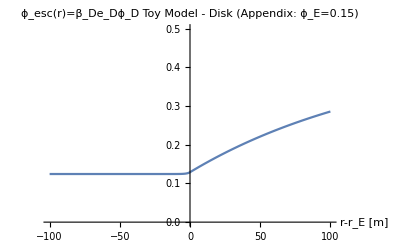

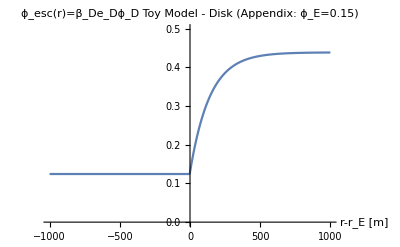

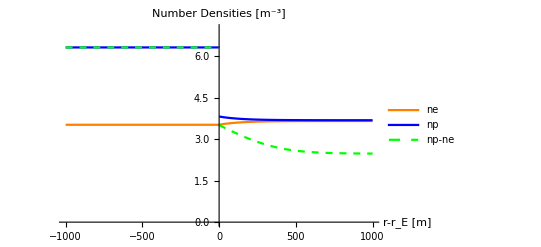

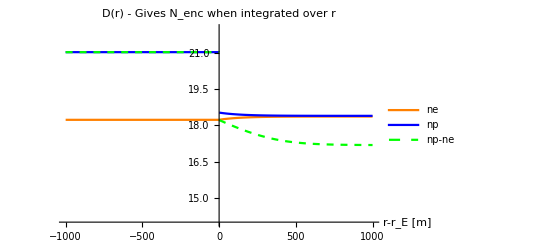

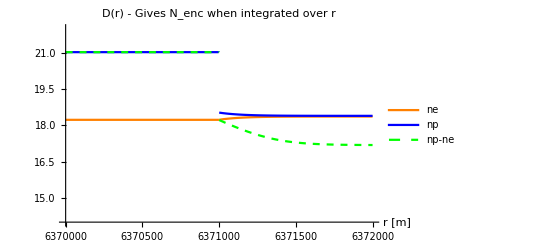

We can also check our approximation of flat gravitational potential over these length scales (not surprising, we can think of our constant potential assumption as working at leading order in λ/r_E<<1)

-Graphics-

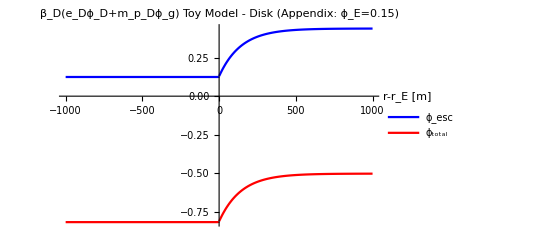

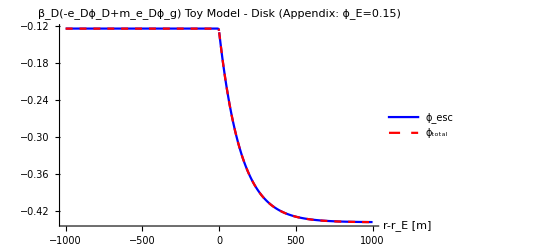

```mathematica
solrepl = {βe->βD,βpout->βD,βpin->βcore,meD->mpD meDbympD,ϕg->-(11200)^2/2,α->αD};
λrepl={λin->(λDsol/.βp->βpin),λout->(λDsol/.βp->βpout),rE->("rE"/.EarthRepl)}/.solrepl/.SIConstRepl/.nF->naDM[fD/.fD->0.05,mpD (1+ meDbympD)]
ϕEsol/.solrepl/.SIConstRepl/.λrepl//Simplify//PowerExpand
δϕin/.solrepl/.SIConstRepl/.%(*//ExpToTrig*)//Simplify;
(*-(0.5576037085544936(1- ⅇ^((2 rE)/λin)) r+0.4049687299775784 ⅇ^((-r+rE)/λin) (1- ⅇ^((2 r)/λin)) rE)/((-1.+ⅇ^((2 rE)/λin)) r)//Simplify*)
Assuming[ϵ>0,Normal@Series[%/.rE->λin Log[ϵ],{ϵ,∞,1}]/.ϵ->E^(rE/λin)]//PowerExpand//Expand;
δϕout/.solrepl/.SIConstRepl/.%%%(*//ExpToTrig*)//Simplify//PowerExpand;
ϕtotalsol=Piecewise[{{%%,r<=rE},{%,r>rE}}]
Quiet@Plot[("e"/.SIConstRepl)βD ϕtotalsol/.λrepl/.rE->("rE"/.EarthRepl)/.r->Δr+"rE"/.EarthRepl,{Δr,-10^2,10^2},PlotRange->{0,0.5},PlotLabel->"ϕ_esc(r)=β_De_Dϕ_D Toy Model - Disk (Appendix: ϕ_E=0.15)",AxesLabel->{"r-r_E [m]"}]
Quiet@Plot[("e"/.SIConstRepl)βD ϕtotalsol/.λrepl/.rE->("rE"/.EarthRepl)/.r->Δr+"rE"/.EarthRepl,{Δr,-10^3,10^3},PlotRange->{0,0.5},PlotLabel->"ϕ_esc(r)=β_De_Dϕ_D Toy Model - Disk (Appendix: ϕ_E=0.15)",AxesLabel->{"r-r_E [m]"}]
{ne,np,np-ne}/.{np->nF E^(- βp (ϵ √αDbyα"e"ϕ[r] + mpD ϕg[r])),ne->nF E^(-βe(-ϵ √αDbyα"e"ϕ[r]+mpD meDbympD ϕg[r]))}/.βp->Piecewise[{{βpin,r<rE},{βpout,r>rE}}]/.{nF->naDM[fD/.fD->0.05,mpD (1+ meDbympD)],ϵ->1,αDbyα->1,ϕg->Function[{r},-(11200)^2/2],ϕ[r]->ϕtotalsol};
numsol=%/.solrepl/.SIConstRepl/.λrepl/.rE->("rE"/.EarthRepl)/.r->Δr+"rE"/.EarthRepl;
Quiet@Plot[Evaluate@(Log10@%),{Δr,-10^3,10^3},PlotRange->{0,7},PlotStyle->#,PlotLegends->LineLegend[#,{"ne","np","np-ne"}],AxesLabel->{"r-r_E [m]"},PlotLabel->"Number Densities [m^-3]"]&@{Orange,Blue,Directive[Dashed,Green]}
Quiet@Plot[Evaluate@(Log10[%% 4π (("rE"/.EarthRepl)+Δr)^2]),{Δr,-10^3,10^3},PlotRange->{14,22},PlotStyle->#,PlotLegends->LineLegend[#,{"ne","np","np-ne"}],AxesLabel->{"r-r_E [m]"},PlotLabel->"D(r) - Gives N_enc when integrated over r"]&@{Orange,Blue,Directive[Dashed,Green]}
Quiet@Plot[Evaluate@(Log10[%%% 4π (r)^2/.Δr->r-("rE"/.EarthRepl)]),{r,("rE"/.EarthRepl)-10^3,("rE"/.EarthRepl)+10^3},PlotRange->{14,22},PlotStyle->#,PlotLegends->LineLegend[#,{"ne","np","np-ne"}],AxesLabel->{"r [m]"},PlotLabel->"D(r) - Gives N_enc when integrated over r"]&@{Orange,Blue,Directive[Dashed,Green]}
"We can also check our approximation of flat gravitational potential over these length scales (not surprising, we can think of our constant potential assumption as working at leading order in λ/r_E<<1)"
Plot[Log10[-Vgrav[Δr+"rE"/.EarthRepl]],{Δr,-10^3,10^3},PlotRange->{0,10},PlotLabel->"Log_10(-V_grav(r))",AxesLabel->{"r-r_E [m]"}]
(*Quiet@Plot[βD (("e"/.SIConstRepl)ϕtotalsol+mpD Vgrav[Δr+"rE"/.EarthRepl])/.λrepl/.rE->("rE"/.EarthRepl)/.r->Δr+"rE"/.EarthRepl,{Δr,-10^2,10^2},(*PlotRange->{0,0.5},*)PlotLabel->"ϕ_(esc, total)(r)=β_D(e_Dϕ_D+m_p_Dϕ_g) Toy Model - Disk (Appendix: ϕ_E=0.15)",AxesLabel->{"r-r_E [m]"}]
*)
Quiet@Plot[Evaluate@({βD ("e"/.SIConstRepl)ϕtotalsol,βD (("e"/.SIConstRepl)ϕtotalsol+mpD Vgrav[Δr+"rE"/.EarthRepl])}/.λrepl/.rE->("rE"/.EarthRepl)/.r->Δr+"rE"/.EarthRepl),{Δr,-10^3,10^3},(*PlotRange->{0,0.5},*)PlotLabel->"β_D(e_Dϕ_D+m_p_Dϕ_g) Toy Model - Disk (Appendix: ϕ_E=0.15)",AxesLabel->{"r-r_E [m]"},PlotStyle->#,PlotLegends->LineLegend[#,{"ϕ_esc","ϕ_total"}],PlotRange->All]&@{Blue,Red}
Quiet@Plot[Evaluate@({-βD ("e"/.SIConstRepl)ϕtotalsol,βD (-("e"/.SIConstRepl)ϕtotalsol+mpD meDbympD Vgrav[Δr+"rE"/.EarthRepl])}/.λrepl/.rE->("rE"/.EarthRepl)/.r->Δr+"rE"/.EarthRepl),{Δr,-10^3,10^3},(*PlotRange->{0,0.5},*)PlotLabel->"β_D(-e_Dϕ_D+m_e_Dϕ_g) Toy Model - Disk (Appendix: ϕ_E=0.15)",AxesLabel->{"r-r_E [m]"},PlotStyle->#,PlotLegends->LineLegend[#,{"ϕ_esc","ϕ_total"}],PlotRange->All]&@{Blue,Directive[Red,Dashed]}
```

```mathematica
D[ϕtotalsol,r]
%/.λrepl
%/.r->"rE"/.EarthRepl
```

Piecewise[{{(0.0177783 ⅇ^(-r/λin-rE/λin) rE)/r^2-(0.0177783 ⅇ^(r/λin-rE/λin) rE)/r^2+(0.0177783 ⅇ^(-r/λin-rE/λin) rE)/(r λin)+(0.0177783 ⅇ^(r/λin-rE/λin) rE)/(r λin), r-rE≤0}, {(1.17266 ⅇ^((-r+rE)/λout) rE)/r^2+(1.17266 ⅇ^((-r+rE)/λout) rE)/(r λout), r-rE>0}, {0, True}}]

Piecewise[{{(113266. ⅇ^(-2.9683×10^6-0.465909 r))/r^2-(113266. ⅇ^(-2.9683×10^6+0.465909 r))/r^2+(52771.4 ⅇ^(-2.9683×10^6-0.465909 r))/r+(52771.4 ⅇ^(-2.9683×10^6+0.465909 r))/r, -6.371×10^6+r≤0}, {(7.47099×10^6 ⅇ^(0.00706335 (6.371×10^6-r)))/r^2+(52770.2 ⅇ^(0.00706335 (6.371×10^6-r)))/r, -6.371×10^6+r>0}, {0, True}}]

General::munfl: Exp[-5.93661×10^6] is too small to represent as a normalized machine number; precision may be lost.

0.00828306

```mathematica
Ntotals=Assuming[Δr<0,numsol(4 π)/3("rE")^3/.EarthRepl//Simplify];
"The net dark charges in the earth are (assuming they stay flat when a gravitational profile is included):"
{Subscript[N, e],Subscript[N, p],Subscript[N, p]-Subscript[N, e]}==Ntotals
"For comparison the (1D) random walk model gives roughly"
Subscript[N, cap,e]==Subscript[n, F] Subscript[V, earth] ==(naDM[fD/.fD->0.05,mpD (1+ meDbympD)](4 π)/3("rE")^3 /.EarthRepl)
Subscript[N, cap,p]==Subscript[n, F] Subscript[V, earth] Subscript[β, earth]/Subscript[β, D]==(naDM[fD/.fD->0.05,mpD (1+ meDbympD)](4 π)/3("rE")^3 βcore/βD/.EarthRepl)
"So pretty close. This tells us that, as we might expect, the dark electrons are moving too fast and pass through the earth essentially unaffected, but that the dark electrons receive an enhancement given the shallow potential well in the earth."
"We can also see that the random walk model also predicts a neutral plasma in the no thermalization limit"
```

The net dark charges in the earth are (assuming they stay flat when a gravitational profile is included):

{N_e,N_p,-N_e+N_p}=={3.17469×10^24,6.11791×10^27,6.11474×10^27}

For comparison the (1D) random walk model gives roughly

N_(cap,e)==n_F V_earth==3.17439×10^24

N_(cap,p)==(n_F V_earth β_earth)/β_D==2.55241×10^25

So pretty close. This tells us that, as we might expect, the dark electrons are moving too fast and pass through the earth essentially unaffected, but that the dark electrons receive an enhancement given the shallow potential well in the earth.

We can also see that the random walk model also predicts a neutral plasma in the no thermalization limit

#### Follow up thoughts from 12/4/25 meeting

I THINK THE VIEW POINT DIFFERENCE IS WHETHER TO TREAT THE SPECIES WITH 1 OR TWO POPULATIONS. And I think what chacko is saying is you have 2 populations w MB distributions at diff temperatures. 

I think what I’m saying is you should treat the species with 1 distribution but it may no longer be MB distributed. But I believe regardless it should still give the same EOM for n. 

If we do adopt this standpoint, then we would need an equation of change for temperature as well. 

I don’t understand what it would mean to transition between the two distributions. How do we know that we’re not just at the tail of one of them instead of part of the other?
We should also check if there is significant overlap of the distributions. to decide if it makes sense to think of two distributions. That will be controlled by I guess the cross entropy.

```mathematica
Manipulate[Plot[{(βcore mpD)^(3/2)v^2 E^(-βcore/2 mpD v^2),v^2(βD mpD)^(3/2)E^(-βD/2 mpD ((v)^2-11200^2)),(1-frac)(βcore mpD)^(3/2)v^2 E^(-βcore/2 mpD v^2)+frac v^2(βD mpD)^(3/2)E^(-βD/2 mpD ((v)^2-11200^2))},{v,0,10^5},PlotRange->All],{frac,0,1}]
Manipulate[Plot[{(βcore mpD)^(3/2)v^2 E^(-βcore/2 mpD v^2),v^2(βD/11 mpD)^(3/2)E^(-βD/(11 2)mpD ((v)^2-11200^2)),(1-frac)(βcore mpD)^(3/2)v^2 E^(-βcore/2 mpD v^2)+frac v^2( βD/11 mpD)^(3/2)E^((- βD)/(2 11)mpD ((v)^2-11200^2))},{v,0,10^5},PlotRange->All],{frac,0,1}]
"From these plots, we can see that there is significant overlap (which points us away from multiple populations), and that it seems like most of the support of the distribution falls in the regime where λ<<r_E for a large range of κ we are interested in. (see the update slides with the interaction length plots)"
```

From these plots, we can see that there is significant overlap (which points us away from multiple populations), and that it seems like most of the support of the distribution falls in the regime where λ<<r_E for a large range of κ we are interested in. (see the update slides with the interaction length plots)

```mathematica
Integrate[4 π(βcore mpD/(2 π))^(3/2)v^2 E^(-βcore/2 mpD v^2),{v,0,∞}]
Integrate[4π v^2(βD mpD/(2 π))^(3/2)E^(-βD/2 mpD (v)^2),{v,0,∞}]
```

1.

1.

```mathematica
Integrate[4 π (βcore mpD/(2 π))^(3/2)v^2 E^(-βcore/2 mpD v^2),{v,0,∞}]
```

1.

```mathematica
E^(-β2 e ϕ)frac + (1-frac)E^(-β1 e ϕ)
```

ⅇ^(-e β1 ϕ) (1-frac)+ⅇ^(-e β2 ϕ) frac

I think the kinetic theory story is that 

-------------------------------------------------------------------------

For knudsen number (K=λ/L) >> 1 we are in the free molecular streaming regime so that we can treat the gas as collisionless and at leading order satisfies

d/dt f=(∂_t +v·∂_r +a·∂_v)f=0+O(1/K)

In this regime, we can model the dynamics with simple classical trajectories as in the appendix. In this case we cannot use flux vectors and cannot rely on thermal equilibrium, but we are at liberty to ignore interactions. 

(QUESTION: can we still do an enskog like expansion order by order if we wanted to include interactions? Or does the lack of thermal equilibrium mean we can’t use local quantities and have to just think about particular trajectories as we’ve been doing so far. Also what happens to the captured population can we really say it’s thermalized if K is large?)

Even though we can no longer treat the gas as a fluid in this regime, we have already been working with it enough to be able to extract a number density in terms of the potential and the distribution at infinity. And this serves an identical purpose in the poisson equation. 

TO BE CLEAR: I think chacko’s resistance to the below stems from his intuition with this regime. Where we are considering free molecular flow, and can in good conscience consider a particle to have left the distribution if it scatters (and alters it’s trajectory off the flow). Then the particles that have left the distribution join a captured subpopulation (the question of whether or not they thermalize still remains and should be checked)

The caveat to the above is the flux effects that everyone has been working on. But perhaps the form of the potential will lead this to be consistently ignorable once we find a solution? Or perhaps there is a bound we can take. 

-------------------------------------------------------------------------

Whereas in the regime K<<1 we are in the chapman enskog regime. This is the regime where we can treat the incoming population as thermalized. And at leading order the distribution satisfies

C[f,f] = 0 + O(K)

In this regime we have local thermal equilibrium, so we can use the H theorem to get the MB distribution. We can also write summation invariants and flux vectors as local quantities. In this regime it is valid to consider equations of change etc. And this regime is where we can use this Poisson treatment.

Also I think this is the tidy answer to chacko’s question. That there is no clear way to define the transition rate between populations of the same species at different temperature (see the overlap above. Non-zero overlap means there is some cross-correlation and the rate I am being asked to calculate is ill defined - I WILL REALLY NEED TO STRESS AND UNDERSTAND THIS POINT IF HE IS GOING TO LISTEN). And that what he’s suggesting can equivalently be phrased in terms of the change of the velocity distribution due to interactions (specifically some subpopulation is cooled). And that computing these corrections in a controlled way is the regime of kinetic theory and the CE expansion. SOOO the next steps / elephant or yam question becomes; what are the leading order dynamics of the summation invariants and how is the temperature of the gas in local thermal equilibrium get effected by scattering with the SM.

NEED TO CHECK: how this story and distinction is affected when the knudsen number is small for SM and large for self interactions. Does the H theorem still apply?

ALSO I think part of the answer / intuition confusion that chacko has is that it is strongly related to the case where there is a binding potential. Since in that case there is a sharp distinction between the two populations: 
	unbound => distribution determined by distribution at ∞
	bound => present in the earth for long period so even for large knudsen number the members are still expected to thermalize. 
Further, in this case there is a clear way to define a transition rate between the two populations. 
BUT AGAIN this only applies in the large knudsen number case, since otherwise the flowing population will also thermalize and you will end up with a single MB, which is constantly and strongly mixing between the two populations. 

Also need to understand / explain why the result will be independent of κ, because david will definitely ask about this. 
---------------------------

FOLLOW UP TODOS:	

Get plots of the TOTAL interaction length in the earth, and possibly a plot of the knudsen number over all of the phase space we are interested in
Get plots (mostly done above) of the overlap of the “captured” and “flowing” distributions, arguing that there is no clean way to cleanly classify in the absence of a BINDING potential, which we are assuming we do not have
Follow up about the time in the Earth via the DIFFUSION approach chacko talked about

#### Can we get non-zero ϕg[r] if we introduce a compensating charge source?

```mathematica
"Take constant solution for ϕ and replace ϕg by ϕg[r]. This will still make the source vanish (ie. still neutral) on the RHS since no derivatives there. So if there is a charge distribution:"
δϕ[r]==((-ⅇ^(mpD βe ϕg)+ⅇ^(meD βp ϕg)) √α)/("e" √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))/.ϕg->ϕg[r]
D[%,r]//Simplify;
%/.ϕg'[r]->HoldForm[1/r^2 D[r^2 D[ϕg[r],r],r]]/.δϕ'[r]->HoldForm[1/r^2 D[r^2 D[δϕ[r],r],r]]//Simplify
"Then this will also be a solution. Well I suppose we should do this before imposing boundary conditions."
"Well we know that ϕg -> 0 at ∞ and so does it's derivative at 0, so this should satisfy those. And since it is continuous at rE, it does for that one too. So it is just a matter of whether or not it satisfies the junction condition. And well, it does, since it's first derivative is continuous at the interface too."
"So this works, and the RHS is proportional to the charge density, which since it goes as the divergence of ϕg tells us the plasma is neutral outside the earth and has some non-trivial charge density inside the earth" 
"The sign will tell us whether this is dark electrons or dark protons"
```

Take constant solution for ϕ and replace ϕg by ϕg[r]. This will still make the source vanish (ie. still neutral) on the RHS since no derivatives there. So if there is a charge distribution:

δϕ[r]==((-ⅇ^(mpD βe ϕg[r])+ⅇ^(meD βp ϕg[r])) √α)/(e √αD (ⅇ^(meD βp ϕg[r]) βe+ⅇ^(mpD βe ϕg[r]) βp))

(∂_r (r^2 ∂_r δϕ[r]))/r^2==(ⅇ^((mpD βe+meD βp) ϕg[r]) √α (βe+βp) (-mpD βe+meD βp) (∂_r (r^2 ∂_r ϕg[r]))/r^2)/(e √αD (ⅇ^(meD βp ϕg[r]) βe+ⅇ^(mpD βe ϕg[r]) βp)^2)

Then this will also be a solution. Well I suppose we should do this before imposing boundary conditions.

Well we know that ϕg -> 0 at ∞ and so does it's derivative at 0, so this should satisfy those. And since it is continuous at rE, it does for that one too. So it is just a matter of whether or not it satisfies the junction condition. And well, it does, since it's first derivative is continuous at the interface too.

So this works, and the RHS is proportional to the charge density, which since it goes as the divergence of ϕg tells us the plasma is neutral outside the earth and has some non-trivial charge density inside the earth

The sign will tell us whether this is dark electrons or dark protons

```mathematica
λDsol
```

(√ϵ0 ⅇ^(1/2 (mpD βe+meD βp) ϕg) √α)/(e √nF √αD √(ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))

```mathematica
ϕEOM/.nF->nFofλD//Simplify
Series[%,{δϕ[r],0,1}]//Normal
```

-(e √(αD/α) (2 δϕ'[r]+r δϕ''[r]))/r==(ⅇ^(meD βp ϕg-e √(αD/α) βe δϕ[r])-ⅇ^(mpD βe ϕg+e √(αD/α) βp δϕ[r]))/((ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp) λD^2)

-(e √(αD/α) (2 δϕ'[r]+r δϕ''[r]))/r==(-ⅇ^(mpD βe ϕg)+ⅇ^(meD βp ϕg))/((ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp) λD^2)-(e √(αD/α) δϕ[r])/λD^2

```mathematica
λDsol
```

(√ϵ0 ⅇ^(1/2 (mpD βe+meD βp) ϕg) √α)/(e √nF √αD √(ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))

```mathematica
((-ⅇ^(mpD βe ϕg)+ⅇ^(meD βp ϕg)) √α)/("e" √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))/.ϕg->ϕg[r]
D[%,r]-%/λD^2/.λD->(λDsol/.ϕg->ϕg[r])//Simplify;
%/.ϕg'[r]->HoldForm[1/r^2 D[r^2 D[ϕg[r],r],r]]/.δϕ'[r]->HoldForm[1/r^2 D[r^2 D[δϕ[r],r],r]]//Simplify
```

((-ⅇ^(mpD βe ϕg[r])+ⅇ^(meD βp ϕg[r])) √α)/(e √αD (ⅇ^(meD βp ϕg[r]) βe+ⅇ^(mpD βe ϕg[r]) βp))

(ⅇ^(-((mpD βe+meD βp) ϕg[r])) ((e^2 (ⅇ^(mpD βe ϕg[r])-ⅇ^(meD βp ϕg[r])) nF αD)/ϵ0-(ⅇ^(2 (mpD βe+meD βp) ϕg[r]) α (βe+βp) (mpD βe-meD βp) (∂_r (r^2 ∂_r ϕg[r]))/r^2)/((ⅇ^(meD βp ϕg[r]) βe+ⅇ^(mpD βe ϕg[r]) βp)^2)))/(e √α √αD)

#### Questions and responses

QUESTIONS:
1) how do we square this with equilibrium number density? Since we are adding something on top?
2) can we ignore the flux effect (ie. in equilibirum will it be compensated for?)
3) also can we assume no charged shell? If this is truely a conducting ball can’t it have some charge?
4) is δϕ small? ie. is it consistent with our assumptions?

```mathematica
"For 1), It is clearly not consistent with the ne-np form we wrote down before in terms of potentials since we know that vanishes identically on δϕ solution, and the net charge density does not. 

I think maybe you have to interpret this as some captured charge. And we should look at the EOM in the two cases. Because these are manifestly different problems I think. Including this source changes the problem. Because in principle starting with ϕg=ϕg[r] (not constant) in the EOM has a solution which I think will be unique. And adding in this captured charge source means we are no longer solving the same problem."

"But I think we should carefully revisit and reconsider what assumptions go into rebecca's equilibrium conditions and whether they clash somehow with our plasma treatment. Since It feels like the plasma physics problem should uniquely determine both the number densities and the potential given that we have 3 equations with unique solutions and 3 unknowns. I guess then adding in this source, we are saying there is a 4th population (some net charge in the earth) which does not satisfy any equation, and hence the non-uniqueness, we've introduced a new free parameter to the system, and I guess this weird prescription just doesn't work since it's overconstrained - just doesn't satisfy the 3 eom, so we soak up the remaining freedom to compensate."
```

```mathematica
"To answer 2) I think I need to look at Knudsen"
```

```mathematica
"for 3), is the 1st der of ϕg discontinuous at rE?"
Assuming[r>"rE"/.Constants`EarthRepl,Capture`Vgrav'[r]//Simplify]/.r->"rE"/.Constants`EarthRepl
Assuming[r<"rE"/.Constants`EarthRepl,Capture`Vgrav'[r]//Simplify]/.r->"rE"/.Constants`EarthRepl
"No it isnt"
```

for 3), is the 1st der of ϕg discontinuous at rE?

9.84461

9.84461

No it isnt

```mathematica
"Maybe the response to 3) is:
I'd suspect that the only reason you get a charge build up on the surface of a conductor is that the electrons are somehow bound to the solid. But since the charges are not confined to the Earth (as in a conducting ball) that there is no reason to expect a discontinuity. 
";
```

```mathematica
"4) is a simple check, just use the framework we set up for numerics"
```

### Unit testing proper treatment - ∇T=0 - with ϕg done numerically solve for ϕ

#### The EOM and solution - assuming fixed grav density

```mathematica
ϕEOM
```

-(e √(αD/α) (2 r δϕ'[r]+r^2 δϕ''[r]))/r^2==-(e^2 ⅇ^(-βp (meD ϕg-e √(αD/α) δϕ[r])) nF αD)/(ϵ0 α)+(e^2 ⅇ^(-βe (mpD ϕg+e √(αD/α) δϕ[r])) nF αD)/(ϵ0 α)

```mathematica
Clear[mpD]
ϕeom =(- ("e")/r^2 √(αD/α)D[r^2 ϕ'[r],r]==- ("e")^2/("ϵ0")αD/α ne+("e")^2/("ϵ0")αD/α np)/.{np->nF E^(- βe (√(αD/α)"e"ϕ[r] + mpD ϕg[r])),ne->nF E^(-βp (-√(αD/α)"e"ϕ[r]+meD ϕg[r]))}/.ϕg->Function[{r},ϕg]
Series[ϕeom,{ϕ[r],0,1}]//Normal
DSolve[%,ϕ[r],r][[1]]/.C[2]->2 ⅇ^(-1/2(mpD βe+meD βp) ϕg)√(nF( ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))(("e")^2/("ϵ0")αD/α)^(1/2)C[2]/.nF->ⅇ^((mpD βe+meD βp) ϕg)/(( ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp) λD^2)(("e")^2/("ϵ0")αD/α)^-1//PowerExpand//Simplify
```

-(e √(αD/α) (2 r ϕ'[r]+r^2 ϕ''[r]))/r^2==-(e^2 ⅇ^(-βp (meD ϕg-e √(αD/α) ϕ[r])) nF αD)/(ϵ0 α)+(e^2 ⅇ^(-βe (mpD ϕg+e √(αD/α) ϕ[r])) nF αD)/(ϵ0 α)

-(e √(αD/α) (2 r ϕ'[r]+r^2 ϕ''[r]))/r^2==(e^2 ⅇ^(-mpD βe ϕg) nF αD)/(ϵ0 α)-(e^2 ⅇ^(-meD βp ϕg) nF αD)/(ϵ0 α)-(e^3 ⅇ^(-mpD βe ϕg-meD βp ϕg) nF αD √(αD/α) (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp) ϕ[r])/(ϵ0 α)

{ϕ[r]→((-ⅇ^(mpD βe ϕg)+ⅇ^(meD βp ϕg)) √α)/(e √αD (ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))+(ⅇ^(-r/λD) C[1]+ⅇ^(r/λD) C[2])/r}

```mathematica
Clear[Getϕeom]
Getϕeom[mpD_:(2 10^3"m"/.Constants`SIConstRepl),αDbyα_:1,meDbympD_:10^-4,βs_:<|"βp"->βp,"βe"->βe|>,fD_:0.05,constrepl_:Join[Constants`SIConstRepl,(Constants`EarthRepl/.Association->List)]]:=Module[{nF,ϕeom,expandinϕ=True,dernorm},
(*
solve the Poisson equation assuming ∇T=0, and a 1 component Earth model
Then the no net diffusion condition implies:
n(r) = n e^(- β Subscript[V, total](r))

We also take units such that Subscript[r, E]=1

	WE MIGHT WANT TO UNDO THE RE = 1 CONVENTION, IT JUST DRASTICALLY INCREASES THE SIZE OF THE SOURCE
ALSO WHY IS THE EXPANSION NOT WORKING?
*)
nF=naDM[fD,mpD (1+ meDbympD)];

(*dernorm= (("e")/(("rE")^2 r)√αDbyα)^-1;*)

(*dernorm= (("e")/(("rE")^2 r)√αDbyα)^-1;ϕeom =(-dernorm ("e")/(("rE")^2 r^2)√αDbyα D[r^2 ϕ'[r],r]==dernorm("e")^2/("ϵ0")αDbyα(- ne+np))/.{np->nF E^(- "βe" (ϵ √αDbyα"e"ϕ[r] + mpD ϕg[r])),ne->nF E^(-"βp" (-ϵ √αDbyα"e"ϕ[r]+mpD meDbympD ϕg[r]))}/.ϕg->Function[{r},Capture`Vgrav["rE"r]]/.βs/.constrepl;*)
dernorm= (("e")/r √αDbyα)^-1;
ϕeom =(-dernorm ("e")/r^2 √αDbyα D[r^2 ϕ'[r],r]==dernorm("e")^2/("ϵ0")αDbyα(- ne+np))/.{np->nF E^(- "βe" (ϵ √αDbyα"e"ϕ[r] + mpD ϕg[r])),ne->nF E^(-"βp" (-ϵ √αDbyα"e"ϕ[r]+mpD meDbympD ϕg[r]))}/.ϕg->Function[{r},Capture`Vgrav[r]](*ϕg->Function[{r},-10^8]*)/.βs/.constrepl;

(*Print@Series[E^(- "βe" (ϵ √αDbyα"e"ϕ[r] + mpD ϕg[r]))-E^(-"βp" (-ϵ √αDbyα"e"ϕ[r]+mpD meDbympD ϕg[r])),{ϵ,0,1}];*)

If[expandinϕ, Normal@Series[ϕeom,{ϵ,0,1}]/.ϵ->1,ϕeom/.ϵ->1]
]
```

```mathematica
Print[ScrollingOptions]
```

ScrollingOptions

```mathematica
SetOptions[nb,ScrollingOptions->{"VerticalScrollRange"->Fit}]
```

```mathematica
Capture`Vgrav[10^2]
```

-9.408×10^7

```mathematica
"As a test case consider the TH disc case"
foverv = 5
mpD =foverv(2 10^3"m"/.Constants`SIConstRepl)
meDbympD=10^-4
βD="βD"/.Capture`v0toβD[20 10^3,mpD,mpD meDbympD]
ϕEomIn=Assuming[r<"rE"/.Constants`EarthRepl (*1*),Getϕeom[mpD,10^0,meDbympD,<|"βp"->"βcore"/.Constants`EarthRepl,"βe"->βD|>,(*10^-9*)10^-2]//Simplify]
```

As a test case consider the TH disc case

5

9.11×10^-27

1/10000

Set::write: Tag Times in Capture`Private`s Capture`Private`veDmean$95033 is Protected.

1.64638×10^18

(-0.0000114865 ⅇ^(-1.1588×10^-14 r^2) r-0.0000225504 ⅇ^(-9.31747×10^-18 r^2) r) ϕ[r]+2 ϕ'[r]+r (0.0000435266 ⅇ^(-1.1588×10^-14 r^2)-0.0000106275 ⅇ^(-9.31747×10^-18 r^2)+ϕ''[r])==0

```mathematica
Table[ϕEomIn/.r->10^Logr,{Logr,1,6}]
```

{2 ϕ'[10]+10 (0.0000369398+ϕ''[10])==0.00035105 ϕ[10],2 ϕ'[100]+100 (0.0000369398+ϕ''[100])==0.0035105 ϕ[100],2 ϕ'[1000]+1000 (0.0000369398+ϕ''[1000])==0.035105 ϕ[1000],2 ϕ'[10000]+10000 (0.0000369398+ϕ''[10000])==0.35105 ϕ[10000],2 ϕ'[100000]+100000 (0.0000369398+ϕ''[100000])==3.5105 ϕ[100000],2 ϕ'[1000000]+1000000 (0.0000369398+ϕ''[1000000])==35.105 ϕ[1000000]}

```mathematica
"now solve the ode in the Earth subject to the no cusp boundary condition, and the boundary condition: ϕ(r_E)=ϕ_E"
rE = "rE"/.Constants`EarthRepl;
(*bcs={δϕ'[1]==-0.005,δϕ[1]==0.05}*)
δr=0.001;
(*bcs={ϕ'[δr]==0,ϕ[10^6]==0.05 1/(βD "e")/.SIConstRepl}*)
bcs={ϕ'[10^6]==0.05/("rE") 1/(βD "e")/.SIConstRepl/.EarthRepl,ϕ[10^6]==0.05 1/(βD "e")/.SIConstRepl}
ϕEomIn
(*NDSolve[{ϕEomIn,bcs},δϕ,r,Method->{"Shooting"}]*)
ndsol=NDSolve[{ϕEomIn,bcs},ϕ,{r,δr,10^6}(*,Method->"Shooting"*)]
Plot[(ϕ/.ndsol[[1]])[r],{r,δr,10^6},PlotRange->{{δr,10^6},Full}]
(ϕ/.ndsol[[1]])[10^6]
(ϕ/.ndsol[[1]])[δr]
```

now solve the ode in the Earth subject to the no cusp boundary condition, and the boundary condition: ϕ(r_E)=ϕ_E

{ϕ'[1000000]==2.97392×10^-8,ϕ[1000000]==0.189469}

(-0.0000114865 ⅇ^(-1.1588×10^-14 r^2) r-0.0000225504 ⅇ^(-9.31747×10^-18 r^2) r) ϕ[r]+2 ϕ'[r]+r (0.0000435266 ⅇ^(-1.1588×10^-14 r^2)-0.0000106275 ⅇ^(-9.31747×10^-18 r^2)+ϕ''[r])==0

General::munfl: 1/(5.22973×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(6.09025×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(7.09237×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{ϕ→                                    6
InterpolatingFunction[{{0.001, 1. 10 }}, <>]}}

-Graphics-

0.189469

-4.53710717567757×10^2540

```mathematica
(ϕ/.ndsol[[1]])["ValuesOnGrid"]
(ϕ/.ndsol[[1]])'[δr]
```

7.6851337938346×10^2584

```mathematica
(ϕ/.ndsol[[1]])[10^6]
```

InterpolatingFunction::dmval: Input value {1000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.75911

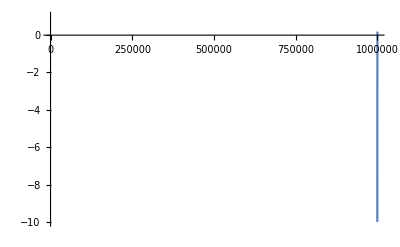

```mathematica
Plot[(ϕ/.ndsol[[1]])[r],{r,δr,10^6},PlotRange->{{δr,10^6},{-10,1}}]
```

```mathematica
Plot[mpD 10^4 Capture`Vgrav[r]βD,{r,0,10^7}]
Plot[mpD meDbympD Capture`Vgrav[r]βD,{r,0,10^7}]
Plot[mpD Capture`Vgrav[r]βcore,{r,0,10^7}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
βcore
```

1.32379×10^19

```mathematica
LogPlot[Exp[-mpD 10^4 Capture`Vgrav[r]βD],{r,0,10^7}]
Plot[Exp[-mpD meDbympD Capture`Vgrav[r]βD],{r,0,10^7}]
Plot[Exp[-mpD 10^4 Capture`Vgrav[r]βcore],{r,0,10^7}]
```

-Graphics-

-Graphics-

-Graphics-

### Create a DSolver

#### Module Definitions

```mathematica
Clear[Getϕeom]
Getϕeom[mpD_:(2 10^3"m"/.Constants`SIConstRepl),αDbyα_:1,meDbympD_:10^-4,βs_:<|"βp"->βp,"βe"->βe|>,fD_:0.05,fullgrav_:True,constrepl_:Join[Constants`SIConstRepl,(Constants`EarthRepl/.Association->List)]]:=Module[{nF,ϕg,ϕeom,expandinϕ=True,dernorm,λDanalytic},
(*
solve the Poisson equation assuming ∇T=0, and a 1 component Earth model
Then the no net diffusion condition implies:
n(r) = n e^(- β Subscript[V, total](r))

We also take units such that Subscript[r, E]=1

	WE MIGHT WANT TO UNDO THE RE = 1 CONVENTION, IT JUST DRASTICALLY INCREASES THE SIZE OF THE SOURCE
ALSO WHY IS THE EXPANSION NOT WORKING?
*)
nF=naDM[fD,mpD (1+ meDbympD)];
(*ϕg = Function[{r},Capture`Vgrav[r]](*Function[{r},(-(11200)^2)/2]*);*)
ϕg = If[fullgrav,Function[{r},Capture`Vgrav[r]],Function[{r},(-(11200)^2)/2]];


(*dernorm= (("e")/(("rE")^2 r)√αDbyα)^-1;*)

(*dernorm= (("e")/(("rE")^2 r)√αDbyα)^-1;ϕeom =(-dernorm ("e")/(("rE")^2 r^2)√αDbyα D[r^2 ϕ'[r],r]==dernorm("e")^2/("ϵ0")αDbyα(- ne+np))/.{np->nF E^(- "βe" (ϵ √αDbyα"e"ϕ[r] + mpD ϕg[r])),ne->nF E^(-"βp" (-ϵ √αDbyα"e"ϕ[r]+mpD meDbympD ϕg[r]))}/.ϕg->Function[{r},Capture`Vgrav["rE"r]]/.βs/.constrepl;*)
dernorm= ("e"√αDbyα)^-1(* (("e")/r √αDbyα)^-1*);
ϕeom =(-dernorm ϵ ("e")/r^2 √αDbyα D[r^2 ϕ'[r],r]==dernorm("e")^2/("ϵ0")αDbyα(- ne+np))/.{np->nF E^(- "βe" (ϵ √αDbyα"e"ϕ[r] + mpD ϕg[r])),ne->nF E^(-"βp" (-ϵ √αDbyα"e"ϕ[r]+mpD meDbympD ϕg[r]))}/.βs/.constrepl;

(*Print@Series[E^(- "βe" (ϵ √αDbyα"e"ϕ[r] + mpD ϕg[r]))-E^(-"βp" (-ϵ √αDbyα"e"ϕ[r]+mpD meDbympD ϕg[r])),{ϵ,0,1}];*)

ϕeom = If[expandinϕ, Normal@Series[ϕeom,{ϵ,0,1}]/.ϵ->1,ϕeom/.ϵ->1];

λDanalytic =(√("ϵ0") ⅇ^(1/2 mpD( "βe"+meDbympD "βp") ϕg[r]))/("e" √nF √αDbyα √(ⅇ^(meDbympD mpD "βp" ϕg[r]) "βe" + ⅇ^(mpD "βe" ϕg[r]) "βp"))/.βs/.constrepl;

<|"ϕeom"->ϕeom,"λD"->λDanalytic,"ϕptotal"->√αDbyα"e"ϕ[r] + mpD ϕg[r]/.constrepl,"ϕetotal"->-√αDbyα"e"ϕ[r] + meDbympD mpD ϕg[r]/.constrepl|>
]
```

```mathematica
Capture`Vgrav["rE"/.EarthRepl]
-(11200)^2/2//N
```

-6.272×10^7

-6.272×10^7

```mathematica
Clear[Shootϕ]
Shootϕ[ϕeomNum_,ϕE_,ϕEp_,N_:10^2,L_:("rE"/.Constants`EarthRepl)]:=Module[{rE,dr,EOMs,steps,currentstep,dy,dϕ,ϕEnoinhomo},

(*This is only shooting in for now*)

(*assumes SI lengths for EOM then normalizes the interval to (0,1)*)

rE="rE"/.Constants`EarthRepl;

dr = L/N; (*[m] - step size*)
(*dr=1/N;*)

Print["Solving over r ∈ (",rE-L,", ",rE,") with step size ",dr];

(*EOMs={#,y[r]}&[y'[r]/.Solve[ϕeomNum/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)*)
(*Print[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rE]]/.r->rE r)];*)
(*/.ϕ->Function[{r},ϕ[r/rEt]]/.r->rEt r/.rEt->rE)*)
EOMs={#, y[r]}&[y'[r]/.Solve[ϕeomNum/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)
(*EOMs={#, y[r]}&[y'[r]/.Solve[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rE]]/.r->rE r)/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)*)

(*Assuming[r<rE,Print[EOMs//Simplify]];*)
(*Assuming[r<rE,Print[Table[EOMs/.r->rE-dr ri//Simplify,{ri,N-1}]]];*)
(*Print[];*)
ϕEnoinhomo=ϕEh/.Solve[(EOMs[[1]]==0)/.y->Function[{r},0]/.ϕ[r]->ϕEh/.r->rE,ϕEh][[1]];

steps={<|r->rE,ϕ[r]->ϕE,y[r]->ϕEp|>};
(*steps={<|r->rE,ϕ[r]->ϕEnoinhomo,y[r]->ϕEp|>};*)


(*Print["{ϕ',dr ϕ',dϕ}: ",{ϕEp,ϕEp dr,ϕE}];*)
Do[
Print[steps[[-1]]];
Print[EOMs/.steps[[-1]]];
{dy,dϕ}=-dr EOMs/.steps[[-1]];
Print["{ϕ'',dϕ',|dϕ'|,dϕ}: ",{dy/dr,dy,Abs@dy,dϕ,Abs@dy<10^(-$MachinePrecision)}];
If[Abs@dy<10^(-$MachinePrecision),dy=0];
AppendTo[steps,<|r->steps[[-1]][r]-dr,ϕ[r]->steps[[-1]][ϕ[r]]+dϕ,y[r]->steps[[-1]][y[r]]+dy|>];(*signs come because r is decreasing*)
,{nr,N}];

steps

]
```

#### scrap definitions

```mathematica
ϕEomIn
```

<|ϕeom→-(2 r ϕ'[r]+r^2 ϕ''[r])/r==0.0000165711 r-0.0000297184 r ϕ[r],λD→183.437|>

```mathematica
$MachinePrecision
```

15.9546

```mathematica
λDsol = λD/.Solve[nF==ⅇ^((mpD βe+meD βp) ϕg)/(( ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp) λD^2)(("e")^2/("ϵ0")αD/α)^-1,λD][[2]]//PowerExpand//Simplify//PowerExpand
```

(√ϵ0 ⅇ^(1/2 (mpD βe+meD βp) ϕg) √α)/(e √nF √αD √(ⅇ^(meD βp ϕg) βe+ⅇ^(mpD βe ϕg) βp))

```mathematica
(*Clear[Shootϕ]
Shootϕ[ϕeomNum_,ϕE_,ϕEp_]:=Module[{N=10,rE,dr,EOMs,steps,currentstep,dy,dϕ},

(*This is only shooting in for now*)

(*assumes SI lengths for EOM then normalizes the interval to (0,1)*)

rE="rE"/.Constants`EarthRepl;
(*dr = rE/N; (*[m] - step size*)*)
dr=1/N;

(*EOMs={#,y[r]}&[y'[r]/.Solve[ϕeomNum/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)*)
Print[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rE]]/.r->rE r)];
EOMs={#, y[r]}&[y'[r]/.Solve[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rEt]]/.r->rEt r/.rEt->rE)/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)
(*EOMs={#, y[r]}&[y'[r]/.Solve[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rE]]/.r->rE r)/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)*)

Assuming[r<rE,Print[EOMs//Simplify]];
Assuming[r<rE,Print[Table[EOMs/.r->1-dr ri//Simplify,{ri,N-1}]]];

steps={<|r->1,ϕ[r]->ϕE,y[r]->ϕEp|>};

Print["{ϕ',dr ϕ',ϕ}: ",{ϕEp,ϕEp dr,ϕE}];
Do[
(*Print[steps[[-1]]];*)
{dy,dϕ}=dr EOMs/.steps[[-1]];
Print["{ϕ',dr ϕ',dϕ}: ",{dy/dr,dy ,dϕ}];
AppendTo[steps,<|r->steps[[-1]][r]-dr,ϕ[r]->steps[[-1]][ϕ[r]]+dϕ,y[r]->steps[[-1]][y[r]]+dy|>];
,{n,N}];

steps

]*)(*before changing to propagation from r=0*)
(*Clear[Shootϕ]
Shootϕ[ϕeomNum_,ϕE_,ϕEp_]:=Module[{N=10,rE,dr,EOMs,steps,currentstep,dy,dϕ},

(*This is only shooting in for now*)

(*assumes SI lengths for EOM then normalizes the interval to (0,1)*)

rE="rE"/.Constants`EarthRepl;
(*dr = rE/N; (*[m] - step size*)*)
dr=1/N;

(*EOMs={#,y[r]}&[y'[r]/.Solve[ϕeomNum/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)*)
Print[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rE]]/.r->rE r)];
EOMs={#, y[r]}&[y'[r]/.Solve[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rEt]]/.r->rEt r/.rEt->rE)/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)
(*EOMs={#, y[r]}&[y'[r]/.Solve[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rE]]/.r->rE r)/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)*)



Assuming[r<rE,Print[EOMs//Simplify]];
Assuming[r<rE,Print[Table[EOMs/.r->dr ri//Simplify,{ri,N}]]];

(*steps={<|r->1,ϕ[r]->ϕE,y[r]->ϕEp|>};*)
steps={<|r->0,ϕ[r]->ϕE,y[r]->0|>};

Print["eom ",EOMs/.y->Function[{r},steps[[-1]][[3]]]//Simplify];

Print["{ϕ',dr ϕ',ϕ}: ",{ϕEp,ϕEp dr,ϕE}];
Do[
(*Print[steps[[-1]]];*)
(*{dy,dϕ}={rE^2#[[1]],rE#[[2]]}&[dr EOMs/.steps[[-1]]];*)
(*{dy,dϕ}=If[n<=1,dr EOMs/.y->Function[{r},0],dr EOMs]/.steps[[-1]];*)
{dy,dϕ}=(dr EOMs/.y->Function[{r},steps[[-1]][[3]]]//Simplify)/.steps[[-1]];
Print["{ϕ',dr ϕ',dϕ}: ",{dy/dr,dy ,dϕ}];
AppendTo[steps,<|r->steps[[-1]][r]+dr,ϕ[r]->steps[[-1]][ϕ[r]]+dϕ,y[r]->steps[[-1]][y[r]]+dy|>];
,{n,N}];

steps

]*)
```

#### Condition for decaying ϕ

```mathematica
"Look for the condition such that the solution decays rather than grows."
ϕEomIn["ϕeom"]
-(2 r ϕ'[r]+r^2 ϕ''[r])/r^2==a-b ϕ[r]
dysol=-dr  ϕ''[r]/.Solve[%,ϕ''[r]][[1]]//Simplify
Solve[0==%//Simplify,ϕ'[r]][[1]]//Simplify
decϕp=-ϵ+ϕ'[r]/.%
%%%/.ϕ'[r]->%//Simplify
"So it looks like we have a condition on ϕ' such that it decreases"
"The condition on ϕ decreasing is"
ϕ'[r]>0
"So we need ϕ to satisfy"
Assuming[{{a,b}>0,{a,b}!=0,ϵ>0},Reduce[decϕp>0,ϕ[r]]//Simplify]
(a r+2 ϵ)/(b r)<ϕ[r]
```

Look for the condition such that the solution decays rather than grows.

-(2 r ϕ'[r]+r^2 ϕ''[r])/r^2==0.0000165711-0.0000297184 ϕ[r]

-(2 r ϕ'[r]+r^2 ϕ''[r])/r^2==a-b ϕ[r]

dr (a-b ϕ[r]+(2 ϕ'[r])/r)

{ϕ'[r]→-1/2 r (a-b ϕ[r])}

-ϵ-1/2 r (a-b ϕ[r])

-(2 dr ϵ)/r

So it looks like we have a condition on ϕ' such that it decreases

The condition on ϕ decreasing is

ϕ'[r]>0

So we need ϕ to satisfy

(r|ϕ[r])∈ℝ&&(((a≠0||2 ϵ<b r ϕ[r])&&(a==0||a r+2 ϵ<b r ϕ[r])&&b≠0&&r≠0)||(b==0&&a≠0&&a r+2 ϵ<0))

(a r+2 ϵ)/(b r)<ϕ[r]

```mathematica
"So ϕ is"
(a r+2 ϵ)/(b r)+ϵϕ/.{a->0.00001657109786102802,b->0.000029718414004071425}//Simplify
"And ϕ' is"
-ϵ-1/2 r (a-b ϕ[r])/.{a->0.00001657109786102802,b->0.000029718414004071425,ϕ[r]->%%}//Simplify
"So taking values for the smudges we have for  (ϕ,ϕ')"
{Out[-4],Out[-2]}/.r->"rE"/.EarthRepl/.{ϵ->0.1,ϵϕ->0.1}
```

So ϕ is

0.557604+(67298.3 ϵ)/r+ϵϕ

And ϕ' is

-1.11022×10^-16 ϵ+r (-1.69407×10^-21+0.0000148592 ϵϕ)

So taking values for the smudges we have for  (ϕ,ϕ')

{0.65866,9.4668}

```mathematica
dysol/.{ϕ[r]->0.6586600316177265,ϕ'[r]->9.466800780996943}/.{a->0.00001657109786102802,b->0.000029718414004071425,dr->183,r->"rE"/.EarthRepl}//Simplify
```

-5.74478×10^-6

#### TH eom test case

```mathematica
"As a test case consider the TH disc case"
foverv = 5
mpD =foverv(2 10^3"m"/.Constants`SIConstRepl)
meDbympD=10^-4
βD="βD"/.Capture`v0toβD[20 10^3,mpD,mpD meDbympD]
ϕEomIn=Assuming[r<"rE"/.Constants`EarthRepl (*1*),Getϕeom[mpD,10^0,meDbympD,<|"βp"->"βcore"/.Constants`EarthRepl,"βe"->βD|>,(*10^-9*)10^-2]//Simplify]
```

As a test case consider the TH disc case

5

9.11×10^-27

1/10000

Set::write: Tag Times in Capture`Private`s Capture`Private`veDmean$42925 is Protected.

1.64638×10^18

<|ϕeom→-(2 r ϕ'[r]+r^2 ϕ''[r])/r^2==0.0000165711-0.0000297184 ϕ[r],λD→183.437|>

#### Investigate scaling over a very small interval and compare to analytic (for constant ϕg)

```mathematica
"Idea is to solve this using the shooting method (for ϕ and ϕ' at rE) using a simple forward Euler"
```

{ϕEp→9.4668,ϕE→0.65866}

0.00917186

Solving over r ∈ (6.371×10^6, 6.371×10^6) with step size 0.0000917186

<|r→6.371×10^6,ϕ[r]→0.65866,y[r]→9.4668|>

{3.13922×10^-8,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {-3.13922×10^-8,-2.87925×10^-12,2.87925×10^-12,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.657792,y[r]→9.4668|>

{5.5883×10^-9,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {-5.5883×10^-9,-5.12551×10^-13,5.12551×10^-13,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.656923,y[r]→9.4668|>

{-2.02156×10^-8,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.02156×10^-8,1.85415×10^-12,1.85415×10^-12,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.656055,y[r]→9.4668|>

{-4.60196×10^-8,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {4.60196×10^-8,4.22085×10^-12,4.22085×10^-12,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.655187,y[r]→9.4668|>

{-7.18235×10^-8,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {7.18235×10^-8,6.58755×10^-12,6.58755×10^-12,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.654319,y[r]→9.4668|>

{-9.76275×10^-8,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {9.76275×10^-8,8.95425×10^-12,8.95425×10^-12,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.65345,y[r]→9.4668|>

{-1.23431×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.23431×10^-7,1.13209×10^-11,1.13209×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.652582,y[r]→9.4668|>

{-1.49235×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.49235×10^-7,1.36877×10^-11,1.36877×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.651714,y[r]→9.4668|>

{-1.75039×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.75039×10^-7,1.60544×10^-11,1.60544×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.650846,y[r]→9.4668|>

{-2.00843×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.00843×10^-7,1.84211×10^-11,1.84211×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.649977,y[r]→9.4668|>

{-2.26647×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.26647×10^-7,2.07878×10^-11,2.07878×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.649109,y[r]→9.4668|>

{-2.52451×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.52451×10^-7,2.31545×10^-11,2.31545×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.648241,y[r]→9.4668|>

{-2.78255×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.78255×10^-7,2.55212×10^-11,2.55212×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.647372,y[r]→9.4668|>

{-3.04059×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {3.04059×10^-7,2.78879×10^-11,2.78879×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.646504,y[r]→9.4668|>

{-3.29863×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {3.29863×10^-7,3.02546×10^-11,3.02546×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.645636,y[r]→9.4668|>

{-3.55667×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {3.55667×10^-7,3.26213×10^-11,3.26213×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.644768,y[r]→9.4668|>

{-3.81471×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {3.81471×10^-7,3.4988×10^-11,3.4988×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.643899,y[r]→9.4668|>

{-4.07275×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {4.07275×10^-7,3.73547×10^-11,3.73547×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.643031,y[r]→9.4668|>

{-4.33079×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {4.33079×10^-7,3.97214×10^-11,3.97214×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.642163,y[r]→9.4668|>

{-4.58883×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {4.58883×10^-7,4.20881×10^-11,4.20881×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.641294,y[r]→9.4668|>

{-4.84687×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {4.84687×10^-7,4.44548×10^-11,4.44548×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.640426,y[r]→9.4668|>

{-5.10491×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {5.10491×10^-7,4.68215×10^-11,4.68215×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.639558,y[r]→9.4668|>

{-5.36294×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {5.36294×10^-7,4.91882×10^-11,4.91882×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.63869,y[r]→9.4668|>

{-5.62098×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {5.62098×10^-7,5.15549×10^-11,5.15549×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.637821,y[r]→9.4668|>

{-5.87902×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {5.87902×10^-7,5.39216×10^-11,5.39216×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.636953,y[r]→9.4668|>

{-6.13706×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {6.13706×10^-7,5.62883×10^-11,5.62883×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.636085,y[r]→9.4668|>

{-6.3951×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {6.3951×10^-7,5.8655×10^-11,5.8655×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.635216,y[r]→9.4668|>

{-6.65314×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {6.65314×10^-7,6.10217×10^-11,6.10217×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.634348,y[r]→9.4668|>

{-6.91118×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {6.91118×10^-7,6.33884×10^-11,6.33884×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.63348,y[r]→9.4668|>

{-7.16922×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {7.16922×10^-7,6.57551×10^-11,6.57551×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.632612,y[r]→9.4668|>

{-7.42726×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {7.42726×10^-7,6.81218×10^-11,6.81218×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.631743,y[r]→9.4668|>

{-7.6853×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {7.6853×10^-7,7.04885×10^-11,7.04885×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.630875,y[r]→9.4668|>

{-7.94334×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {7.94334×10^-7,7.28552×10^-11,7.28552×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.630007,y[r]→9.4668|>

{-8.20138×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {8.20138×10^-7,7.52219×10^-11,7.52219×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.629138,y[r]→9.4668|>

{-8.45942×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {8.45942×10^-7,7.75886×10^-11,7.75886×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.62827,y[r]→9.4668|>

{-8.71746×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {8.71746×10^-7,7.99553×10^-11,7.99553×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.627402,y[r]→9.4668|>

{-8.9755×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {8.9755×10^-7,8.2322×10^-11,8.2322×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.626534,y[r]→9.4668|>

{-9.23354×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {9.23354×10^-7,8.46887×10^-11,8.46887×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.625665,y[r]→9.4668|>

{-9.49158×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {9.49158×10^-7,8.70554×10^-11,8.70554×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.624797,y[r]→9.4668|>

{-9.74961×10^-7,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {9.74961×10^-7,8.94221×10^-11,8.94221×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.623929,y[r]→9.4668|>

{-1.00077×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.00077×10^-6,9.17888×10^-11,9.17888×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.62306,y[r]→9.4668|>

{-1.02657×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.02657×10^-6,9.41555×10^-11,9.41555×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.622192,y[r]→9.4668|>

{-1.05237×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.05237×10^-6,9.65222×10^-11,9.65222×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.621324,y[r]→9.4668|>

{-1.07818×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.07818×10^-6,9.88889×10^-11,9.88889×10^-11,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.620456,y[r]→9.4668|>

{-1.10398×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.10398×10^-6,1.01256×10^-10,1.01256×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.619587,y[r]→9.4668|>

{-1.12979×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.12979×10^-6,1.03622×10^-10,1.03622×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.618719,y[r]→9.4668|>

{-1.15559×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.15559×10^-6,1.05989×10^-10,1.05989×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.617851,y[r]→9.4668|>

{-1.18139×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.18139×10^-6,1.08356×10^-10,1.08356×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.616983,y[r]→9.4668|>

{-1.2072×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.2072×10^-6,1.10722×10^-10,1.10722×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.616114,y[r]→9.4668|>

{-1.233×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.233×10^-6,1.13089×10^-10,1.13089×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.615246,y[r]→9.4668|>

{-1.2588×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.2588×10^-6,1.15456×10^-10,1.15456×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.614378,y[r]→9.4668|>

{-1.28461×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.28461×10^-6,1.17822×10^-10,1.17822×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.613509,y[r]→9.4668|>

{-1.31041×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.31041×10^-6,1.20189×10^-10,1.20189×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.612641,y[r]→9.4668|>

{-1.33622×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.33622×10^-6,1.22556×10^-10,1.22556×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.611773,y[r]→9.4668|>

{-1.36202×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.36202×10^-6,1.24923×10^-10,1.24923×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.610905,y[r]→9.4668|>

{-1.38782×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.38782×10^-6,1.27289×10^-10,1.27289×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.610036,y[r]→9.4668|>

{-1.41363×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.41363×10^-6,1.29656×10^-10,1.29656×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.609168,y[r]→9.4668|>

{-1.43943×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.43943×10^-6,1.32023×10^-10,1.32023×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.6083,y[r]→9.4668|>

{-1.46524×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.46524×10^-6,1.34389×10^-10,1.34389×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.607431,y[r]→9.4668|>

{-1.49104×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.49104×10^-6,1.36756×10^-10,1.36756×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.606563,y[r]→9.4668|>

{-1.51684×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.51684×10^-6,1.39123×10^-10,1.39123×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.605695,y[r]→9.4668|>

{-1.54265×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.54265×10^-6,1.41489×10^-10,1.41489×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.604827,y[r]→9.4668|>

{-1.56845×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.56845×10^-6,1.43856×10^-10,1.43856×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.603958,y[r]→9.4668|>

{-1.59426×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.59426×10^-6,1.46223×10^-10,1.46223×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.60309,y[r]→9.4668|>

{-1.62006×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.62006×10^-6,1.4859×10^-10,1.4859×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.602222,y[r]→9.4668|>

{-1.64586×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.64586×10^-6,1.50956×10^-10,1.50956×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.601353,y[r]→9.4668|>

{-1.67167×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.67167×10^-6,1.53323×10^-10,1.53323×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.600485,y[r]→9.4668|>

{-1.69747×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.69747×10^-6,1.5569×10^-10,1.5569×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.599617,y[r]→9.4668|>

{-1.72328×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.72328×10^-6,1.58056×10^-10,1.58056×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.598749,y[r]→9.4668|>

{-1.74908×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.74908×10^-6,1.60423×10^-10,1.60423×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.59788,y[r]→9.4668|>

{-1.77488×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.77488×10^-6,1.6279×10^-10,1.6279×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.597012,y[r]→9.4668|>

{-1.80069×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.80069×10^-6,1.65156×10^-10,1.65156×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.596144,y[r]→9.4668|>

{-1.82649×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.82649×10^-6,1.67523×10^-10,1.67523×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.595275,y[r]→9.4668|>

{-1.8523×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.8523×10^-6,1.6989×10^-10,1.6989×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.594407,y[r]→9.4668|>

{-1.8781×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.8781×10^-6,1.72257×10^-10,1.72257×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.593539,y[r]→9.4668|>

{-1.9039×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.9039×10^-6,1.74623×10^-10,1.74623×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.592671,y[r]→9.4668|>

{-1.92971×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.92971×10^-6,1.7699×10^-10,1.7699×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.591802,y[r]→9.4668|>

{-1.95551×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.95551×10^-6,1.79357×10^-10,1.79357×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.590934,y[r]→9.4668|>

{-1.98132×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {1.98132×10^-6,1.81723×10^-10,1.81723×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.590066,y[r]→9.4668|>

{-2.00712×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.00712×10^-6,1.8409×10^-10,1.8409×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.589198,y[r]→9.4668|>

{-2.03292×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.03292×10^-6,1.86457×10^-10,1.86457×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.588329,y[r]→9.4668|>

{-2.05873×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.05873×10^-6,1.88823×10^-10,1.88823×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.587461,y[r]→9.4668|>

{-2.08453×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.08453×10^-6,1.9119×10^-10,1.9119×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.586593,y[r]→9.4668|>

{-2.11033×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.11033×10^-6,1.93557×10^-10,1.93557×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.585724,y[r]→9.4668|>

{-2.13614×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.13614×10^-6,1.95924×10^-10,1.95924×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.584856,y[r]→9.4668|>

{-2.16194×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.16194×10^-6,1.9829×10^-10,1.9829×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.583988,y[r]→9.4668|>

{-2.18775×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.18775×10^-6,2.00657×10^-10,2.00657×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.58312,y[r]→9.4668|>

{-2.21355×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.21355×10^-6,2.03024×10^-10,2.03024×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.582251,y[r]→9.4668|>

{-2.23935×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.23935×10^-6,2.0539×10^-10,2.0539×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.581383,y[r]→9.4668|>

{-2.26516×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.26516×10^-6,2.07757×10^-10,2.07757×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.580515,y[r]→9.4668|>

{-2.29096×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.29096×10^-6,2.10124×10^-10,2.10124×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.579646,y[r]→9.4668|>

{-2.31677×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.31677×10^-6,2.1249×10^-10,2.1249×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.578778,y[r]→9.4668|>

{-2.34257×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.34257×10^-6,2.14857×10^-10,2.14857×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.57791,y[r]→9.4668|>

{-2.36837×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.36837×10^-6,2.17224×10^-10,2.17224×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.577042,y[r]→9.4668|>

{-2.39418×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.39418×10^-6,2.19591×10^-10,2.19591×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.576173,y[r]→9.4668|>

{-2.41998×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.41998×10^-6,2.21957×10^-10,2.21957×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.575305,y[r]→9.4668|>

{-2.44579×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.44579×10^-6,2.24324×10^-10,2.24324×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.574437,y[r]→9.4668|>

{-2.47159×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.47159×10^-6,2.26691×10^-10,2.26691×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.573568,y[r]→9.4668|>

{-2.49739×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.49739×10^-6,2.29057×10^-10,2.29057×10^-10,-0.000868281,False}

<|r→6.371×10^6,ϕ[r]→0.5727,y[r]→9.4668|>

{-2.5232×10^-6,9.4668}

{ϕ'',dϕ',|dϕ'|,dϕ}: {2.5232×10^-6,2.31424×10^-10,2.31424×10^-10,-0.000868281,False}

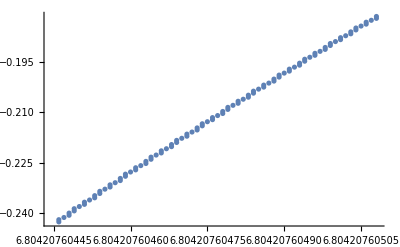

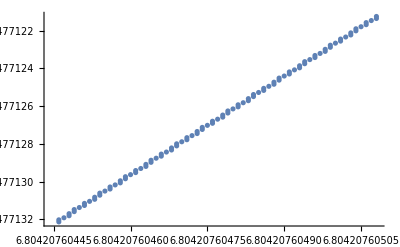

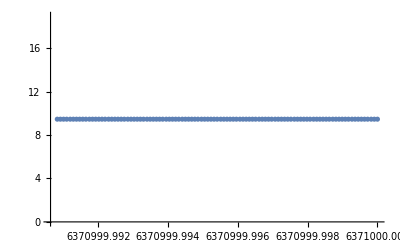

```mathematica
(*bcs={ϕEp->#  1/(βD "e""rE")/.SIConstRepl/.EarthRepl,ϕE-># 1/(βD "e")/.SIConstRepl}&[10^-1]*)
(*bcs={ϕEp->#  1/(βD "e""rE")/.SIConstRepl/.EarthRepl,ϕE-># 1/(βD "e")/.SIConstRepl}&[10^-1]*)
bcs={ϕEp->9.466800780996943,ϕE->(*-0.00003517559993080934 *)0.6586600316177265}

NMFPS= 0.00005;
NMFPS ϕEomIn["λD"]/.r->"rE"/.EarthRepl
ϕshot=Monitor[Shootϕ[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn["ϕeom"]//Simplify],ϕE/.bcs,ϕEp/.bcs,10^2,NMFPS ϕEomIn["λD"]/.r->"rE"/.EarthRepl],nr];
(*ϕshotND=NDSolve[{Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn["ϕeom"]//Simplify],ϕ["rE"/.EarthRepl]==ϕE/.bcs,ϕ'["rE"/.EarthRepl]==ϕEp/.bcs},ϕ,({r,"rE"-#,"rE"}/.EarthRepl)&[NMFPS ϕEomIn["λD"]/.r->"rE"/.EarthRepl]][[1]];*)
ListPlot[Log10@Abs@{r,ϕ[r]}/.ϕshot]
ListPlot[Log10@Abs@{r,1/3("rE"E^(0.5 (r-"rE")/183))/r/.EarthRepl}/.ϕshot]
ListPlot[Abs@{r,y[r]}/.ϕshot]
(*Plot[Log10@ϕ[10^logr]/.ϕshotND,{logr,Log10@(ϕ/.ϕshotND)["Domain"][[1,1]],Log10@(ϕ/.ϕshotND)["Domain"][[1,2]]}]*)
```

#### Debug

```mathematica
"See the problem is, the Euler method relies on dr such that dr ϕ' << ϕ everywhere. So what we need to carefully do the rescaling to set r'∈(0,1) rather than r'∈(0,rE) (rE ~ 10^6 in SI)";
"This still doesn't look right, I went too far the other way so that now nothing is changing."
```

This still doesn't look right, I went too far the other way so that now nothing is changing.

```mathematica
r->10^6 r
ϕ'->10^-6 ϕ'
Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn]
%/.ϕ->Function[{r},ϕ[r/rE]]/.r->rE r
```

r→1000000 r

ϕ'→ϕ'/1000000

-(2 r ϕ'[r]+r^2 ϕ''[r])/r==1.81117×10^-8 (2403.23 ⅇ^(-1.1588×10^-14 r^2)-586.776 ⅇ^(-9.31747×10^-18 r^2)) r+1.81117×10^-8 r (-634.201 ⅇ^(-1.1588×10^-14 r^2) ϕ[r]-1245.07 ⅇ^(-9.31747×10^-18 r^2) ϕ[r])

-(2 r ϕ'[r]+r^2 ϕ''[r])/(r rE)==1.81117×10^-8 (2403.23 ⅇ^(-1.1588×10^-14 r^2 rE^2)-586.776 ⅇ^(-9.31747×10^-18 r^2 rE^2)) r rE+1.81117×10^-8 r rE (-634.201 ⅇ^(-1.1588×10^-14 r^2 rE^2) ϕ[r]-1245.07 ⅇ^(-9.31747×10^-18 r^2 rE^2) ϕ[r])

Things to try for debug:
1) use the analytic model to estimate a value for the bcs
2) double check that we have the rEs using dϕ invariance
3) check for ϵ_0s
4) propagate from r=0 instead (then one of the BCs is trivial)
5) use initial condition to cancel inhomogeneous term which I believe to be the cause of this uncontrolled growth

Let’s save and start with 4) and 2)

#### Look at variation with number of steps

{{ϕEh→0.557604}}

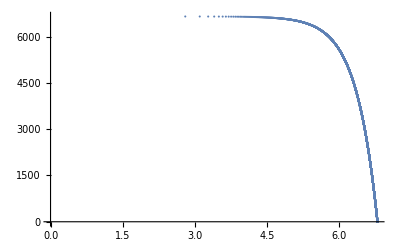

{{ϕEh→0.557604}}

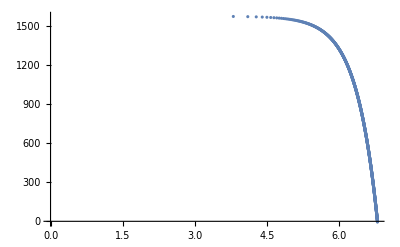

{{ϕEh→0.557604}}

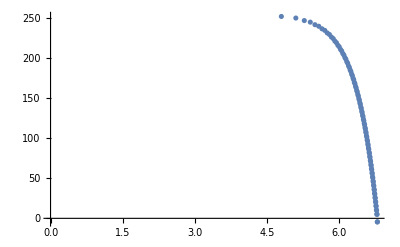

{{ϕEh→0.557604}}

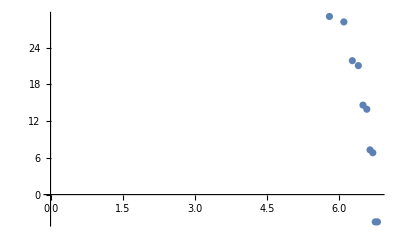

```mathematica
ϕshotcoarse=Monitor[Shootϕ[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn//Simplify],ϕE/.bcs,ϕEp/.bcs,10^4,"rE"/.EarthRepl],nr];
ListPlot[Log10@Abs@{r,ϕ[r]}/.ϕshotcoarse,PlotRange->{{0,Log10@"rE"/.EarthRepl},All}]
ϕshotcoarse=Monitor[Shootϕ[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn//Simplify],ϕE/.bcs,ϕEp/.bcs,10^3,"rE"/.EarthRepl],nr];
ListPlot[Log10@Abs@{r,ϕ[r]}/.ϕshotcoarse,PlotRange->{{0,Log10@"rE"/.EarthRepl},All}]
ϕshotcoarse=Monitor[Shootϕ[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn//Simplify],ϕE/.bcs,ϕEp/.bcs,10^2,"rE"/.EarthRepl],nr];
ListPlot[Log10@Abs@{r,ϕ[r]}/.ϕshotcoarse,PlotRange->{{0,Log10@"rE"/.EarthRepl},All}]
ϕshotcoarse=Monitor[Shootϕ[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn//Simplify],ϕE/.bcs,ϕEp/.bcs,10^1,"rE"/.EarthRepl],nr];
ListPlot[Log10@Abs@{r,ϕ[r]}/.ϕshotcoarse,PlotRange->{{0,Log10@"rE"/.EarthRepl},All}]
```

```mathematica
"So crazy variation. There is some instability here."
```

#### Compare directly to the analytic solution

```mathematica
DSolve[ϕEomIn,ϕ[r],r][[1]]
ϕ[r]/.%
{(%/.r->"rE"/.Constants`EarthRepl)==ϕE,(D[%,r]/.r->"rE"/.Constants`EarthRepl)==0}
Solve[{(%/.r->"rE"/.Constants`EarthRepl)==ϕE,(D[%,r]/.r->"rE"/.Constants`EarthRepl)==0},{C[1],C[2]}]
```

{ϕ[r]→1.05227+(ⅇ^(-0.00592495 r) C[1])/r^1.+(84.3889 ⅇ^(0.00592495 r) C[2])/r^1.}

1.05227+(ⅇ^(-0.00592495 r) C[1])/r^1.+(84.3889 ⅇ^(0.00592495 r) C[2])/r^1.

General::munfl: Exp[-37747.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{1.05227+6.43529475623327×10^16388 C[2]==ϕE,0.+3.812779127397×10^16386 C[2]==0}

{}

So it looks like this is the reason. But upshot is, you are very quickly forced onto inhomogeneous part. So I think what we’ll maybe want to do is just solve to within a few debeye lengths (which we can estimate from the analytic solution.) Because I think when we’re solving over the huge ranges of rE we are overshooting significantly which is probably why it’s going negative.

```mathematica
ϕEomIn
DSolve[ϕEomIn,ϕ[r],r][[1]]
ϕ[r]/.%/.C[2]->C[2] E^(-0.005924950264138598 "rE") "rE"
{(%/.r->"rE"/.Constants`EarthRepl)==ϕE,(D[%,r]/.r->"rE"/.Constants`EarthRepl)==0}
Solve[(%%/.r->"rE"/.Constants`EarthRepl)==ϕE,C[2]]
```

2 ϕ'[r]+r (0.0000369398+ϕ''[r])==0.000035105 r ϕ[r]

{ϕ[r]→1.05227+(ⅇ^(-0.00592495 r) C[1])/r^1.+(84.3889 ⅇ^(0.00592495 r) C[2])/r^1.}

1.05227+(ⅇ^(-0.00592495 r) C[1])/r^1.+(84.3889 rE ⅇ^(-0.00592495 rE+0.00592495 r) C[2])/r^1.

General::munfl: Exp[-37747.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{1.05227+84.3889 C[2]==ϕE,0.+0.499987 C[2]==0}

General::munfl: Exp[-37747.9] is too small to represent as a normalized machine number; precision may be lost.

{{C[2]→0.0118499 (-1.05227+1. ϕE)}}

#### Debug - via step size

```mathematica
"Idea is to solve this using the shooting method (for ϕ and ϕ' at rE) using a simple forward Euler"
```

```mathematica
"As a test case consider the TH disc case"
foverv = 5
mpD =foverv(2 10^3"m"/.Constants`SIConstRepl)
meDbympD=10^-4
βD="βD"/.Capture`v0toβD[20 10^3,mpD,mpD meDbympD]
ϕEomIn=Assuming[r<"rE"/.Constants`EarthRepl (*1*),Getϕeom[mpD,10^0,meDbympD,<|"βp"->"βcore"/.Constants`EarthRepl,"βe"->βD|>,(*10^-9*)10^-2]//Simplify]
```

As a test case consider the TH disc case

5

9.11×10^-27

1/10000

Set::write: Tag Times in Capture`Private`s Capture`Private`veDmean$21741 is Protected.

1.64638×10^18

(-0.0000114865 ⅇ^(-1.1588×10^-14 r^2) r-0.0000225504 ⅇ^(-9.31747×10^-18 r^2) r) ϕ[r]+2 ϕ'[r]+r (0.0000435266 ⅇ^(-1.1588×10^-14 r^2)-0.0000106275 ⅇ^(-9.31747×10^-18 r^2)+ϕ''[r])==0

```mathematica
ϕEomIn
```

(-0.0000114865 ⅇ^(-1.1588×10^-14 r^2) r-0.0000225504 ⅇ^(-9.31747×10^-18 r^2) r) ϕ[r]+2 ϕ'[r]+r (0.0000435266 ⅇ^(-1.1588×10^-14 r^2)-0.0000106275 ⅇ^(-9.31747×10^-18 r^2)+ϕ''[r])==0

```mathematica
Clear[Getϕeom]
Getϕeom[mpD_:(2 10^3"m"/.Constants`SIConstRepl),αDbyα_:1,meDbympD_:10^-4,βs_:<|"βp"->βp,"βe"->βe|>,fD_:0.05,constrepl_:Join[Constants`SIConstRepl,(Constants`EarthRepl/.Association->List)]]:=Module[{nF,ϕeom,expandinϕ=True,dernorm},
(*
solve the Poisson equation assuming ∇T=0, and a 1 component Earth model
Then the no net diffusion condition implies:
n(r) = n e^(- β Subscript[V, total](r))

We also take units such that Subscript[r, E]=1

	WE MIGHT WANT TO UNDO THE RE = 1 CONVENTION, IT JUST DRASTICALLY INCREASES THE SIZE OF THE SOURCE
ALSO WHY IS THE EXPANSION NOT WORKING?
*)
nF=naDM[fD,mpD (1+ meDbympD)];

(*dernorm= (("e")/(("rE")^2 r)√αDbyα)^-1;*)

(*dernorm= (("e")/(("rE")^2 r)√αDbyα)^-1;ϕeom =(-dernorm ("e")/(("rE")^2 r^2)√αDbyα D[r^2 ϕ'[r],r]==dernorm("e")^2/("ϵ0")αDbyα(- ne+np))/.{np->nF E^(- "βe" (ϵ √αDbyα"e"ϕ[r] + mpD ϕg[r])),ne->nF E^(-"βp" (-ϵ √αDbyα"e"ϕ[r]+mpD meDbympD ϕg[r]))}/.ϕg->Function[{r},Capture`Vgrav["rE"r]]/.βs/.constrepl;*)
dernorm= (("e")/r √αDbyα)^-1;
ϕeom =(-dernorm ("e")/r^2 √αDbyα D[r^2 ϕ'[r],r]==dernorm("e")^2/("ϵ0")αDbyα(- ne+np))/.{np->nF E^(- "βe" (ϵ √αDbyα"e"ϕ[r] + mpD ϕg[r])),ne->nF E^(-"βp" (-ϵ √αDbyα"e"ϕ[r]+mpD meDbympD ϕg[r]))}/.ϕg->Function[{r},Capture`Vgrav[r]](*ϕg->Function[{r},-10^8]*)/.βs/.constrepl;

(*Print@Series[E^(- "βe" (ϵ √αDbyα"e"ϕ[r] + mpD ϕg[r]))-E^(-"βp" (-ϵ √αDbyα"e"ϕ[r]+mpD meDbympD ϕg[r])),{ϵ,0,1}];*)

If[expandinϕ, Normal@Series[ϕeom,{ϵ,0,1}]/.ϵ->1,ϕeom/.ϵ->1]
]
```

```mathematica
"For outside we'll need to compactify since r->∞, but Newman says how to do that"
```

```mathematica
Clear[Shootϕ]
Shootϕ[ϕeomNum_,ϕE_,ϕEp_,N_:10^2,L_:("rE"/.Constants`EarthRepl)]:=Module[{,rE,dr,EOMs,steps,currentstep,dy,dϕ},

(*This is only shooting in for now*)

(*assumes SI lengths for EOM then normalizes the interval to (0,1)*)

rE="rE"/.Constants`EarthRepl;
dr = L/N; (*[m] - step size*)
(*dr=1/N;*)

(*EOMs={#,y[r]}&[y'[r]/.Solve[ϕeomNum/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)*)
(*Print[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rE]]/.r->rE r)];*)
(*/.ϕ->Function[{r},ϕ[r/rEt]]/.r->rEt r/.rEt->rE)*)
EOMs={#, y[r]}&[y'[r]/.Solve[ϕeomNum/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)
(*EOMs={#, y[r]}&[y'[r]/.Solve[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rE]]/.r->rE r)/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)*)

(*Assuming[r<rE,Print[EOMs//Simplify]];*)
(*Assuming[r<rE,Print[Table[EOMs/.r->1-dr/L ri//Simplify,{ri,N-1}]]];*)
Print[Solve[(EOMs[[1]]==0)/.y->Function[{r},0]/.ϕ[r]->ϕEh/.r->rE,ϕEh]];

steps={<|r->rE,ϕ[r]->ϕE,y[r]->ϕEp|>};

(*Print["{ϕ',dr ϕ',dϕ}: ",{ϕEp,ϕEp dr,ϕE}];*)
Do[
(*Print[steps[[-1]]];*)
{dy,dϕ}=dr EOMs/.steps[[-1]];
(*Print["{ϕ'',dϕ',dϕ}: ",{dy/dr,dy ,dϕ}];*)
AppendTo[steps,<|r->steps[[-1]][r]-dr,ϕ[r]->steps[[-1]][ϕ[r]]+dϕ,y[r]->steps[[-1]][y[r]]+dy|>];
,{nr,N}];

steps

]
(*Clear[Shootϕ]
Shootϕ[ϕeomNum_,ϕE_,ϕEp_]:=Module[{N=10,rE,dr,EOMs,steps,currentstep,dy,dϕ},

(*This is only shooting in for now*)

(*assumes SI lengths for EOM then normalizes the interval to (0,1)*)

rE="rE"/.Constants`EarthRepl;
(*dr = rE/N; (*[m] - step size*)*)
dr=1/N;

(*EOMs={#,y[r]}&[y'[r]/.Solve[ϕeomNum/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)*)
Print[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rE]]/.r->rE r)];
EOMs={#, y[r]}&[y'[r]/.Solve[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rEt]]/.r->rEt r/.rEt->rE)/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)
(*EOMs={#, y[r]}&[y'[r]/.Solve[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rE]]/.r->rE r)/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)*)

Assuming[r<rE,Print[EOMs//Simplify]];
Assuming[r<rE,Print[Table[EOMs/.r->1-dr ri//Simplify,{ri,N-1}]]];

steps={<|r->1,ϕ[r]->ϕE,y[r]->ϕEp|>};

Print["{ϕ',dr ϕ',ϕ}: ",{ϕEp,ϕEp dr,ϕE}];
Do[
(*Print[steps[[-1]]];*)
{dy,dϕ}=dr EOMs/.steps[[-1]];
Print["{ϕ',dr ϕ',dϕ}: ",{dy/dr,dy ,dϕ}];
AppendTo[steps,<|r->steps[[-1]][r]-dr,ϕ[r]->steps[[-1]][ϕ[r]]+dϕ,y[r]->steps[[-1]][y[r]]+dy|>];
,{n,N}];

steps

]*)(*before changing to propagation from r=0*)
(*Clear[Shootϕ]
Shootϕ[ϕeomNum_,ϕE_,ϕEp_]:=Module[{N=10,rE,dr,EOMs,steps,currentstep,dy,dϕ},

(*This is only shooting in for now*)

(*assumes SI lengths for EOM then normalizes the interval to (0,1)*)

rE="rE"/.Constants`EarthRepl;
(*dr = rE/N; (*[m] - step size*)*)
dr=1/N;

(*EOMs={#,y[r]}&[y'[r]/.Solve[ϕeomNum/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)*)
Print[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rE]]/.r->rE r)];
EOMs={#, y[r]}&[y'[r]/.Solve[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rEt]]/.r->rEt r/.rEt->rE)/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)
(*EOMs={#, y[r]}&[y'[r]/.Solve[(ϕeomNum/.ϕ->Function[{r},ϕ[r/rE]]/.r->rE r)/.{ϕ''[r]->y'[r],ϕ'[r]->y[r]},y'[r]][[1]]];(*{y'[r],ϕ'[r]}*)*)



Assuming[r<rE,Print[EOMs//Simplify]];
Assuming[r<rE,Print[Table[EOMs/.r->dr ri//Simplify,{ri,N}]]];

(*steps={<|r->1,ϕ[r]->ϕE,y[r]->ϕEp|>};*)
steps={<|r->0,ϕ[r]->ϕE,y[r]->0|>};

Print["eom ",EOMs/.y->Function[{r},steps[[-1]][[3]]]//Simplify];

Print["{ϕ',dr ϕ',ϕ}: ",{ϕEp,ϕEp dr,ϕE}];
Do[
(*Print[steps[[-1]]];*)
(*{dy,dϕ}={rE^2#[[1]],rE#[[2]]}&[dr EOMs/.steps[[-1]]];*)
(*{dy,dϕ}=If[n<=1,dr EOMs/.y->Function[{r},0],dr EOMs]/.steps[[-1]];*)
{dy,dϕ}=(dr EOMs/.y->Function[{r},steps[[-1]][[3]]]//Simplify)/.steps[[-1]];
Print["{ϕ',dr ϕ',dϕ}: ",{dy/dr,dy ,dϕ}];
AppendTo[steps,<|r->steps[[-1]][r]+dr,ϕ[r]->steps[[-1]][ϕ[r]]+dϕ,y[r]->steps[[-1]][y[r]]+dy|>];
,{n,N}];

steps

]*)
```

```mathematica
ϕE/.ϕEsol/.{α->αD ,meD->mpD meDbympD,βp->βcore,βe->βD,ϕg->11200/2}/.Constants`SIConstRepl
```

-0.0000351756

```mathematica
(*bcs={ϕEp->#  1/(βD "e""rE")/.SIConstRepl/.EarthRepl,ϕE-># 1/(βD "e")/.SIConstRepl}&[10^-1]*)
(*bcs={ϕEp->#  1/(βD "e""rE")/.SIConstRepl/.EarthRepl,ϕE-># 1/(βD "e")/.SIConstRepl}&[10^-1]*)
bcs={ϕEp->0,ϕE->-0.00003517559993080934 }


ϕshot=Monitor[Shootϕ[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn//Simplify],ϕE/.bcs,ϕEp/.bcs,10^5],nr];
```

{ϕEp→0,ϕE→-0.0000351756}

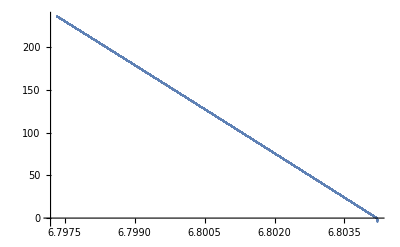

```mathematica
ListPlot[Log10@Abs@{r,ϕ[r]}/.ϕshot]
```

```mathematica
ϕshotcoarse=Monitor[Shootϕ[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn//Simplify],ϕE/.bcs,ϕEp/.bcs,10^4],nr];
```

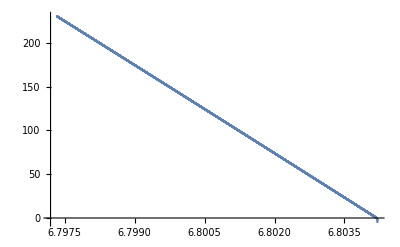

```mathematica
ListPlot[Log10@Abs@{r,ϕ[r]}/.ϕshotcoarse]
```

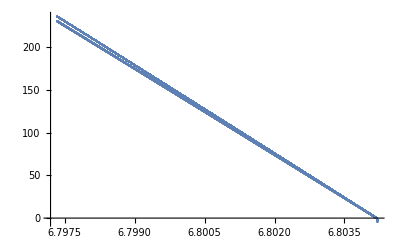

{{ϕEh→0.557604}}

```mathematica
P1 = -Graphics-;
P2 = -Graphics-;
Show[{P1,P2}]
```

```mathematica
ϕshotcoarse=Monitor[Shootϕ[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn//Simplify],ϕE/.bcs,ϕEp/.bcs,10^4,"rE"/.EarthRepl],nr];
ListPlot[Log10@Abs@{r,ϕ[r]}/.ϕshotcoarse,PlotRange->{{0,Log10@"rE"/.EarthRepl},All}]
ϕshotcoarse=Monitor[Shootϕ[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn//Simplify],ϕE/.bcs,ϕEp/.bcs,10^3,"rE"/.EarthRepl],nr];
ListPlot[Log10@Abs@{r,ϕ[r]}/.ϕshotcoarse,PlotRange->{{0,Log10@"rE"/.EarthRepl},All}]
ϕshotcoarse=Monitor[Shootϕ[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn//Simplify],ϕE/.bcs,ϕEp/.bcs,10^2,"rE"/.EarthRepl],nr];
ListPlot[Log10@Abs@{r,ϕ[r]}/.ϕshotcoarse,PlotRange->{{0,Log10@"rE"/.EarthRepl},All}]
ϕshotcoarse=Monitor[Shootϕ[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn//Simplify],ϕE/.bcs,ϕEp/.bcs,10^1,"rE"/.EarthRepl],nr];
ListPlot[Log10@Abs@{r,ϕ[r]}/.ϕshotcoarse,PlotRange->{{0,Log10@"rE"/.EarthRepl},All}]
```

{{ϕEh→0.557604}}

-Graphics-

{{ϕEh→0.557604}}

-Graphics-

{{ϕEh→0.557604}}

-Graphics-

{{ϕEh→0.557604}}

-Graphics-

```mathematica
"See the problem is, the Euler method relies on dr such that dr ϕ' << ϕ everywhere. So what we need to carefully do the rescaling to set r'∈(0,1) rather than r'∈(0,rE) (rE ~ 10^6 in SI)";
"This still doesn't look right, I went too far the other way so that now nothing is changing."
```

This still doesn't look right, I went too far the other way so that now nothing is changing.

```mathematica
r->10^6 r
ϕ'->10^-6 ϕ'
Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn]
%/.ϕ->Function[{r},ϕ[r/rE]]/.r->rE r
```

r→1000000 r

ϕ'→ϕ'/1000000

-(2 r ϕ'[r]+r^2 ϕ''[r])/r==1.81117×10^-8 (2403.23 ⅇ^(-1.1588×10^-14 r^2)-586.776 ⅇ^(-9.31747×10^-18 r^2)) r+1.81117×10^-8 r (-634.201 ⅇ^(-1.1588×10^-14 r^2) ϕ[r]-1245.07 ⅇ^(-9.31747×10^-18 r^2) ϕ[r])

-(2 r ϕ'[r]+r^2 ϕ''[r])/(r rE)==1.81117×10^-8 (2403.23 ⅇ^(-1.1588×10^-14 r^2 rE^2)-586.776 ⅇ^(-9.31747×10^-18 r^2 rE^2)) r rE+1.81117×10^-8 r rE (-634.201 ⅇ^(-1.1588×10^-14 r^2 rE^2) ϕ[r]-1245.07 ⅇ^(-9.31747×10^-18 r^2 rE^2) ϕ[r])

Things to try for debug:
1) use the analytic model to estimate a value for the bcs
2) double check that we have the rEs using dϕ invariance
3) check for ϵ_0s
4) propagate from r=0 instead (then one of the BCs is trivial)
5) use initial condition to cancel inhomogeneous term which I believe to be the cause of this uncontrolled growth

Let’s save and start with 4) and 2)

### Investigate stability of the EOM

#### Analytic derivation of Implicit Euler

```mathematica
Clear[u,b]
u[r+Δr]==u[r]+Δr(A[r].u[r]+b[r])
"Δr->-Δr"
u[r-Δr]==u[r]-Δr(A[r].u[r]+b[r])
"r->r+Δr"
u[r]==u[r+Δr]-Δr(A[r+Δr].u[r+Δr]+b[r+Δr])
"Solve for u[r+Δr]"
u[r]==(Id-Δr A[r+Δr]).u[r+Δr]+b[r+Δr]
u[r+Δr]==Inverse[Id-Δr A[r+Δr]](u[r]-b[r+Δr])
```

u[r+Δr]==Δr (b[r]+A[r].u[r])+u[r]

Δr->-Δr

u[r-Δr]==-Δr (b[r]+A[r].u[r])+u[r]

r->r+Δr

u[r]==-Δr (b[r+Δr]+A[r+Δr].u[r+Δr])+u[r+Δr]

Solve for u[r+Δr]

u[r]==b[r+Δr]+(Id-Δr A[r+Δr]).u[r+Δr]

u[r+Δr]==Inverse[Id-Δr A[r+Δr]] (-b[r+Δr]+u[r])

#### Extract trans matrix

```mathematica
Clear[mpD]
ϕEOM =(-("e")/r^2 √(αD/α)D[r^2 δϕ'[r],r]-(- ("e")^2/("ϵ0")αD/α ne+("e")^2/("ϵ0")αD/α np))/.{np->nF E^(- βp (√(αD/α)"e"δϕ[r] + mpD ϕg[r])),ne->nF E^(-βe (-√(αD/α)"e"δϕ[r]+meD ϕg[r]))}
"Introduce a variable for y=ϕ' and expand in small ϕ"
ϕandyEOM=Normal@Series[ϕEOM/.δϕ->Function[{r},ϵ δϕ[r]],{ϵ,0,1}]/.{δϕ''[r]->y'[r],δϕ'[r]->y[r]}
{b1,Ax1}=CoefficientList[%,ϵ]//Simplify;
b={-b1/Coefficient[Ax1,y'[r],1],0}
Ax={{-Coefficient[#,y[r],1],-Coefficient[#,δϕ[r],1]},{1,0}}&@(Coefficient[Ax1,y'[r],0]/Coefficient[Ax1,y'[r],1])//Simplify
u = {y[r],δϕ[r]}
D[u,r]-(Ax.u+b)//Simplify
y'[r]-(y'[r]/.Solve[0==ϕandyEOM/.ϵ->1,y'[r]][[1]])//Simplify//PowerExpand//Simplify
%-%%[[1]]//Simplify//PowerExpand//Simplify
"So we can write the system of ODEs as a matrix equation"
```

(e^2 ⅇ^(-βe (-e √(αD/α) δϕ[r]+meD ϕg[r])) nF αD)/(ϵ0 α)-(e^2 ⅇ^(-βp (e √(αD/α) δϕ[r]+mpD ϕg[r])) nF αD)/(ϵ0 α)-(e √(αD/α) (2 r δϕ'[r]+r^2 δϕ''[r]))/r^2

Introduce a variable for y=ϕ' and expand in small ϕ

(e^2 ⅇ^(-meD βe ϕg[r]) nF αD)/(ϵ0 α)-(e^2 ⅇ^(-mpD βp ϕg[r]) nF αD)/(ϵ0 α)+ϵ ((e^3 ⅇ^(-meD βe ϕg[r]) nF αD √(αD/α) βe δϕ[r])/(ϵ0 α)+(e^3 ⅇ^(-mpD βp ϕg[r]) nF αD √(αD/α) βp δϕ[r])/(ϵ0 α)-(e √(αD/α) (2 y[r]+r y'[r]))/r)

{(e (ⅇ^(-meD βe ϕg[r])-ⅇ^(-mpD βp ϕg[r])) nF αD)/(ϵ0 α √(αD/α)),0}

{{-2/r,(e^2 nF αD (ⅇ^(-meD βe ϕg[r]) βe+ⅇ^(-mpD βp ϕg[r]) βp))/(ϵ0 α)},{1,0}}

{y[r],δϕ[r]}

{-(e (ⅇ^(-meD βe ϕg[r])-ⅇ^(-mpD βp ϕg[r])) nF √(αD/α))/ϵ0+(2 y[r])/r-(e^2 nF αD (ⅇ^(-meD βe ϕg[r]) βe+ⅇ^(-mpD βp ϕg[r]) βp) δϕ[r])/(ϵ0 α)+y'[r],-y[r]+δϕ'[r]}

(2 y[r])/r-(e (ⅇ^(-meD βe ϕg[r])-ⅇ^(-mpD βp ϕg[r])) nF √α √αD+e^2 nF αD (ⅇ^(-meD βe ϕg[r]) βe+ⅇ^(-mpD βp ϕg[r]) βp) δϕ[r]-ϵ0 α y'[r])/(ϵ0 α)

0

So we can write the system of ODEs as a matrix equation

```mathematica
D[u,r]-(Ax.u+b)//Simplify
"We discretize the homogeneous eqn in the Euler method as "
(u/.r->r+Δr)==Δr Ax.u
"We can solve look for the eigenvalues of this propagation matrix to investigate stability "
Bprop=Δr Ax/.nF->(nD/.Solve[(("e")^2 nD αD (ⅇ^(-meD βe ϕg[r]) βe+ⅇ^(-mpD βp ϕg[r]) βp))/("ϵ0" α)==λD^-2,nD][[1]])//Simplify
Eigenvalues[IdentityMatrix[2]+Bprop]//Simplify//PowerExpand//FullSimplify
(*Normal@Series[%/.λD->r ϵ//Simplify//PowerExpand,{ϵ,0,1}]/.ϵ->λD/r*)
"So the condition for a convergent propagation is that the magnitude of Δr is less than"
(*Assuming[{Δr>0,λD!=0},Reduce[%%[[1]]<=1,Δr]]
Assuming[{Δr>0,λD!=0},Reduce[%%%[[2]]<=1,Δr]]*)
Assuming[{r>0,Δr>0,λD>0,λD!=0},Reduce[%%[[1]]<=1,Δr]//FullSimplify]
Assuming[{r>0,Δr>0,λD>0,λD!=0},Reduce[%%%[[1]]>=-1,Δr]//FullSimplify]
(*Solve[-%%[[1]]==1,Δr]//Simplify
Solve[-%%%[[2]]==1,Δr]
Normal@Series[(Δr/.%[[1]])/.λD->r ϵ//Simplify//PowerExpand,{ϵ,0,1}]/.ϵ->λD/r
Normal@Series[(Δr/.%%[[1]])/.λD->r ϵ//Simplify//PowerExpand,{ϵ,0,1}]/.ϵ->λD/r*)
"ie. we need a step size of order λD (λD<<r) in order to have convergence. Which is infeasible in the Earth where λD = O(m) so we'd need millions of steps. Let's look at implicit solvers. From Newman the prescription is Δr->-Δr and r->r+Δr which gives the equivalent set of equations"
(u/.r->r+Δr)==u+Δr Ax.u+b/.Δr->-Δr/.r->r+Δr
(*"This let's us then take B_prop^-1 as our propagation matrix"
Inverse[Bprop]
"This gives for the homogeneous propagation equation"
(u/.r->r+Δr)==Inverse[Bprop].u
"And for the inhomogeneous equation"
(u/.r->r+Δr)==Inverse[Bprop].(u-b)
"As opposed to"*)

(u/.r->r+Δr)==Bprop.u+b
"So what are B's eigenvalues?"
Eigenvalues[Inverse[IdentityMatrix[2]-Bprop]]
"Which at NL order gives"
Assuming[{r>0,Δr>0,λD>0,λD!=0},Reduce[%%[[1]]<=1,Δr]//FullSimplify]
Assuming[{r>0,Δr>0,λD>0,λD!=0},Reduce[%%%[[1]]>=-1,Δr]//FullSimplify]
(*Assuming[{{λD,Δr,r}>0,λD!=0},Reduce[%%%[[2]]<=1,Δr]//Simplify]*)
(*Solve[-%%[[1]]==1,Δr]//Simplify
Solve[-%%%[[2]]==1,Δr]
Normal@Series[(Δr/.%[[1]])/.λD->r ϵ//Simplify//PowerExpand,{ϵ,0,1}]/.ϵ->λD/r
Normal@Series[(Δr/.%%[[1]])/.λD->r ϵ//Simplify//PowerExpand,{ϵ,0,1}]/.ϵ->λD/r*)
(*Normal@Series[%%/.λD->r ϵ//Simplify//PowerExpand,{ϵ,0,2}]/.ϵ->λD/r
Normal@Series[%%%/.r->λD ϵ//Simplify//PowerExpand,{ϵ,0,2}]/.ϵ->(λD/r)^-1
"Which means we will converge provided min(λD,r)<<Δr"

*)
```

{-(e (ⅇ^(-meD βe ϕg[r])-ⅇ^(-mpD βp ϕg[r])) nF √(αD/α))/ϵ0+(2 y[r])/r-(e^2 nF αD (ⅇ^(-meD βe ϕg[r]) βe+ⅇ^(-mpD βp ϕg[r]) βp) δϕ[r])/(ϵ0 α)+y'[r],-y[r]+δϕ'[r]}

We discretize the homogeneous eqn in the Euler method as

{y[r+Δr],δϕ[r+Δr]}=={Δr (-(2 y[r])/r+(e^2 nF αD (ⅇ^(-meD βe ϕg[r]) βe+ⅇ^(-mpD βp ϕg[r]) βp) δϕ[r])/(ϵ0 α)),Δr y[r]}

We can solve look for the eigenvalues of this propagation matrix to investigate stability

{{-(2 Δr)/r,Δr/λD^2},{Δr,0}}

{1-(Δr (λD+√(r^2+λD^2)))/(r λD),(r λD-Δr λD+Δr √(r^2+λD^2))/(r λD)}

So the condition for a convergent propagation is that the magnitude of Δr is less than

True

r Δr+2 λD^2≤2 λD √(r^2+λD^2)

ie. we need a step size of order λD (λD<<r) in order to have convergence. Which is infeasible in the Earth where λD = O(m) so we'd need millions of steps. Let's look at implicit solvers. From Newman the prescription is Δr->-Δr and r->r+Δr which gives the equivalent set of equations

{y[r],δϕ[r]}=={(e (ⅇ^(-meD βe ϕg[r+Δr])-ⅇ^(-mpD βp ϕg[r+Δr])) nF αD)/(ϵ0 α √(αD/α))+y[r+Δr]-Δr (-(2 y[r+Δr])/(r+Δr)+(e^2 nF αD (ⅇ^(-meD βe ϕg[r+Δr]) βe+ⅇ^(-mpD βp ϕg[r+Δr]) βp) δϕ[r+Δr])/(ϵ0 α)),-Δr y[r+Δr]+δϕ[r+Δr]}

{y[r+Δr],δϕ[r+Δr]}=={(e (ⅇ^(-meD βe ϕg[r])-ⅇ^(-mpD βp ϕg[r])) nF αD)/(ϵ0 α √(αD/α))-(2 Δr y[r])/r+(Δr δϕ[r])/λD^2,Δr y[r]}

So what are B's eigenvalues?

{(-r λD^2-Δr λD^2-√(r^2 Δr^2 λD^2+Δr^2 λD^4))/(r Δr^2-r λD^2-2 Δr λD^2),(-r λD^2-Δr λD^2+√(r^2 Δr^2 λD^2+Δr^2 λD^4))/(r Δr^2-r λD^2-2 Δr λD^2)}

Which at NL order gives

r Δr>λD (λD+√(r^2+λD^2))

r Δr<λD (λD+√(r^2+λD^2))||r Δr≥2 λD (λD+√(r^2+λD^2))

#### Module Definitions

```mathematica
Clear[b,Ax]
getEOMMatrics[ϕeom_] :=Module[{ϕtoyrepl,ϵrepl,by,b,Ay,A,u,Mateom,B,Binv},

ϕtoyrepl = {ϕ''[r]-> y'[r],ϕ'[r]->y[r]};
ϵrepl={ϕ->Function[{r},ϵ ϕ[r]],y->Function[{r},ϵ y[r]]};
{by,Ay}=CoefficientList[#,ϵ]&[y'[r]-(y'[r]/.Solve[ϕeom/.ϕtoyrepl,y'[r]][[1]])/.ϵrepl//Simplify];
b={-by/Coefficient[Ay,y'[r],1],0};
A={{-Coefficient[#,y[r],1],-Coefficient[#,ϕ[r],1]},{1,0}}&@(Coefficient[Ay,y'[r],0]/Coefficient[Ay,y'[r],1])//Simplify;
u = {y[r],ϕ[r]};
D[u,r]-(A.u + b);
B=Δr A; (*the transformation matrix from the prescription Δr->-Δr, r -> r + Δr in the Forward Euler*)
(*Binv=Inverse[B];*)

<|"B"->B,(*"Binv"->Binv,*)"A"->A,"b"->b,"u"->u|>
]
```

```mathematica
Clear[mpD,λD]
mats=getEOMMatrics[ϕEomIn["ϕeom"]]
"Analytic EOM"
D[mats["u"],r]==mats["A"].mats["u"]+mats["b"]
"Discretized Forward Euler"
(mats["u"]/.r->r+Δr)==(IdentityMatrix[2]+mats["B"]).mats["u"]+Δr mats["b"]
"Discretized Implicit Euler"
(mats["u"]/.r->r+Δr)==Series[Inverse[(IdentityMatrix[2]-mats["B"])].(mats["u"]-mats["b"])//Expand,{Δr,0,1}]//Normal
```

<|B→{{-(2. Δr)/r,0.0000297184 Δr},{Δr,0}},A→{{-2./r,0.0000297184},{1,0}},b→{-0.0000165711,0},u→{y[r],ϕ[r]}|>

Analytic EOM

{y'[r],ϕ'[r]}=={-0.0000165711-(2. y[r])/r+0.0000297184 ϕ[r],y[r]}

Discretized Forward Euler

{y[r+Δr],ϕ[r+Δr]}=={-0.0000165711 Δr+(1-(2. Δr)/r) y[r]+0.0000297184 Δr ϕ[r],Δr y[r]+ϕ[r]}

Discretized Implicit Euler

{y[r+Δr],ϕ[r+Δr]}=={0.0000165711+y[r]+(0.0000297184 Δr (-1.11521-67298.3 y[r]+1. r ϕ[r]))/r,Δr (0.0000165711+y[r])+ϕ[r]}

```mathematica
Clear[Shootϕimplict]
Shootϕimplict[ϕeomNum_,ϕE_,ϕEp_,N_:10^2,L_:("rE"/.Constants`EarthRepl),rincreasing_:False]:=Module[{rE,dr,mats,EOMs,steps,currentstep,ynew,ϕnew},

(*feeding the start BCs N interval etc should be streamlined*)

rE="rE"/.Constants`EarthRepl;

dr = L/N; (*[m] - step size*)

Print["should include a convergence criteria flag based on analytics. "];

Print["Solving over r ∈ (",rE-L,", ",rE,") with step size ",dr];

(*mats=getEOMMatrics[ϕEomIn["ϕeom"]];*)
mats=getEOMMatrics[ϕeomNum];

Print[(mats["u"]/.r->r+Δr)==(IdentityMatrix[2]-mats["B"]).(mats["u"]-mats["b"])//Expand];

If[rincreasing,If[ϕEp!=0,Return[Print["To start at the origin, ϕ' must vanish"],Module]]];

steps=If[rincreasing,{<|r->0,ϕ[r]->ϕE,y[r]->ϕEp|>},{<|r->0.9 rE,ϕ[r]->ϕE,y[r]->ϕEp|>}];

Do[

{ynew,ϕnew}=Inverse[IdentityMatrix[2]-If[rincreasing,1,-1] mats["B"]].({steps[[-1]][ϕ[r]],steps[[-1]][y[r]]}-mats["b"])/.Δr->dr/.steps[[-1]];

AppendTo[steps,<|r->steps[[-1]][r]+If[rincreasing,1,-1]dr,ϕ[r]->ϕnew,y[r]->ynew|>];(*signs come because r is decreasing*)
,{nr,N}];

steps

]
```

```mathematica
test[]:=Module[{},Return[1,Module]]
test[]
```

1

#### TH eom test case

```mathematica
"As a test case consider the TH disc case"
foverv = 5
mpD =foverv(2 10^3"m"/.Constants`SIConstRepl)
meDbympD=10^-4
βD="βD"/.Capture`v0toβD[20 10^3,mpD,mpD meDbympD]
```

As a test case consider the TH disc case

5

9.11×10^-27

1/10000

Set::write: Tag Times in Capture`Private`s Capture`Private`veDmean$97088 is Protected.

1.64638×10^18

#### Convergence test (for constant ϕg)

```mathematica
"Idea is to solve this using the shooting method (for ϕ and ϕ' at rE) using a simple forward Euler"
```

```mathematica
(*bcs={ϕEp->#  1/(βD "e""rE")/.SIConstRepl/.EarthRepl,ϕE-># 1/(βD "e")/.SIConstRepl}&[10^-1]*)
(*bcs={ϕEp->#  1/(βD "e""rE")/.SIConstRepl/.EarthRepl,ϕE-># 1/(βD "e")/.SIConstRepl}&[10^-1]*)
(*bcs={ϕEp->0.00,ϕE->(*-0.00003517559993080934 *)0.6586600316177265}*)
(*bcs={ϕEp->10^-6,ϕE->(*-0.00003517559993080934 *)0.05}*)(*works smoothly! but decay is too slow*)
(*bcs={ϕEp->(*10^-6*)0,ϕE->(*-0.00003517559993080934 *)4 10^-5}*)
(*bcs={ϕEp->0.008283060268774853,ϕE->0.488}(*BC from TH analytic solution*)*)
bcs={ϕEp->0,ϕE->0.488}(*BC from TH analytic solution*)

ϕEomInconst=Assuming[r<"rE"/.Constants`EarthRepl (*1*),Getϕeom[mpD,10^0,meDbympD,<|"βp"->"βcore"/.Constants`EarthRepl,"βe"->βD|>,(*10^-9*)5 10^-2,False]//Simplify];
ϕshotconst=Monitor[Shootϕimplict[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomInconst["ϕeom"]//Simplify],ϕE/.bcs,ϕEp/.bcs,Round@(10^2)(*,NMFPS ϕEomIn["λD"]/.r->"rE"/.EarthRepl*),0.11"rE"/.EarthRepl,False],nr];


ϕEomIn=Assuming[r<"rE"/.Constants`EarthRepl (*1*),Getϕeom[mpD,10^0,meDbympD,<|"βp"->"βcore"/.Constants`EarthRepl,"βe"->βD|>,(*10^-9*)5 10^-2,True]//Simplify];

NMFPS=10000;
NMFPS ϕEomIn["λD"]/.r->"rE"/.EarthRepl;

ϕshot=Monitor[Shootϕimplict[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn["ϕeom"]//Simplify],ϕE/.bcs,ϕEp/.bcs,Round@(10^2)(*,NMFPS ϕEomIn["λD"]/.r->"rE"/.EarthRepl*),0.9"rE"/.EarthRepl,False],nr];

(*ϕshotND=NDSolve[{Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn["ϕeom"]//Simplify],ϕ["rE"/.EarthRepl]==ϕE/.bcs,ϕ'["rE"/.EarthRepl]==ϕEp/.bcs},ϕ,({r,"rE"-#,"rE"}/.EarthRepl)&[NMFPS ϕEomIn["λD"]/.r->"rE"/.EarthRepl]][[1]];*)

(*Plot[Log10@ϕ[10^logr]/.ϕshotND,{logr,Log10@(ϕ/.ϕshotND)["Domain"][[1,1]],Log10@(ϕ/.ϕshotND)["Domain"][[1,2]]}]*)
```

{ϕEp→0,ϕE→0.488}

should include a convergence criteria flag based on analytics.

Solving over r ∈ (5.67019×10^6, 6.371×10^6) with step size 7008.1

{y[r+Δr],ϕ[r+Δr]}=={0.0000828555+(0.000165711 Δr)/r+y[r]+(2. Δr y[r])/r-0.000148592 Δr ϕ[r],-0.0000828555 Δr-Δr y[r]+ϕ[r]}

should include a convergence criteria flag based on analytics.

Solving over r ∈ (637100., 6.371×10^6) with step size 57339.

{y[r+Δr],ϕ[r+Δr]}=={0.000217633 ⅇ^(-1.1588×10^-14 r^2)-0.0000531376 ⅇ^(-9.31747×10^-18 r^2)+(0.000435266 ⅇ^(-1.1588×10^-14 r^2) Δr)/r-(0.000106275 ⅇ^(-9.31747×10^-18 r^2) Δr)/r+y[r]+(2. Δr y[r])/r-0.0000574324 ⅇ^(-1.1588×10^-14 r^2) Δr ϕ[r]-0.000112752 ⅇ^(-9.31747×10^-18 r^2) Δr ϕ[r],-0.000217633 ⅇ^(-1.1588×10^-14 r^2) Δr+0.0000531376 ⅇ^(-9.31747×10^-18 r^2) Δr-Δr y[r]+ϕ[r]}

```mathematica
ϕshotconst
```

{<|r→5.7339×10^6,ϕ[r]→0.488,y[r]→0|>,<|r→5.72689×10^6,ϕ[r]→0.468767,y[r]→-0.0000668893|>,<|r→5.71988×10^6,ϕ[r]→0.450295,y[r]→-0.0000642631|>,<|r→5.71288×10^6,ϕ[r]→0.432554,y[r]→-0.0000617312|>,<|r→5.70587×10^6,ϕ[r]→0.415515,y[r]→-0.0000592996|>,<|r→5.69886×10^6,ϕ[r]→0.399151,y[r]→-0.0000569641|>,<|r→5.69185×10^6,ϕ[r]→0.383434,y[r]→-0.0000547211|>,<|r→5.68484×10^6,ϕ[r]→0.368339,y[r]→-0.0000525669|>,<|r→5.67784×10^6,ϕ[r]→0.353842,y[r]→-0.0000504979|>,<|r→5.67083×10^6,ϕ[r]→0.339918,y[r]→-0.0000485108|>,<|r→5.66382×10^6,ϕ[r]→0.326545,y[r]→-0.0000466024|>,<|r→5.65681×10^6,ϕ[r]→0.313702,y[r]→-0.0000447694|>,<|r→5.6498×10^6,ϕ[r]→0.301367,y[r]→-0.000043009|>,<|r→5.64279×10^6,ϕ[r]→0.28952,y[r]→-0.0000413183|>,<|r→5.63579×10^6,ϕ[r]→0.278142,y[r]→-0.0000396945|>,<|r→5.62878×10^6,ϕ[r]→0.267214,y[r]→-0.0000381349|>,<|r→5.62177×10^6,ϕ[r]→0.256718,y[r]→-0.0000366371|>,<|r→5.61476×10^6,ϕ[r]→0.246638,y[r]→-0.0000351985|>,<|r→5.60775×10^6,ϕ[r]→0.236957,y[r]→-0.0000338169|>,<|r→5.60075×10^6,ϕ[r]→0.227659,y[r]→-0.00003249|>,<|r→5.59374×10^6,ϕ[r]→0.218729,y[r]→-0.0000312155|>,<|r→5.58673×10^6,ϕ[r]→0.210152,y[r]→-0.0000299915|>,<|r→5.57972×10^6,ϕ[r]→0.201915,y[r]→-0.000028816|>,<|r→5.57271×10^6,ϕ[r]→0.194004,y[r]→-0.0000276869|>,<|r→5.56571×10^6,ϕ[r]→0.186406,y[r]→-0.0000266026|>,<|r→5.5587×10^6,ϕ[r]→0.179108,y[r]→-0.0000255611|>,<|r→5.55169×10^6,ϕ[r]→0.1721,y[r]→-0.0000245609|>,<|r→5.54468×10^6,ϕ[r]→0.165369,y[r]→-0.0000236003|>,<|r→5.53767×10^6,ϕ[r]→0.158904,y[r]→-0.0000226777|>,<|r→5.53067×10^6,ϕ[r]→0.152695,y[r]→-0.0000217915|>,<|r→5.52366×10^6,ϕ[r]→0.146731,y[r]→-0.0000209405|>,<|r→5.51665×10^6,ϕ[r]→0.141004,y[r]→-0.0000201231|>,<|r→5.50964×10^6,ϕ[r]→0.135503,y[r]→-0.0000193381|>,<|r→5.50263×10^6,ϕ[r]→0.13022,y[r]→-0.0000185842|>,<|r→5.49562×10^6,ϕ[r]→0.125146,y[r]→-0.0000178601|>,<|r→5.48862×10^6,ϕ[r]→0.120273,y[r]→-0.0000171646|>,<|r→5.48161×10^6,ϕ[r]→0.115593,y[r]→-0.0000164967|>,<|r→5.4746×10^6,ϕ[r]→0.111098,y[r]→-0.0000158552|>,<|r→5.46759×10^6,ϕ[r]→0.106781,y[r]→-0.0000152391|>,<|r→5.46058×10^6,ϕ[r]→0.102635,y[r]→-0.0000146473|>,<|r→5.45358×10^6,ϕ[r]→0.0986525,y[r]→-0.000014079|>,<|r→5.44657×10^6,ϕ[r]→0.0948279,y[r]→-0.0000135332|>,<|r→5.43956×10^6,ϕ[r]→0.0911547,y[r]→-0.000013009|>,<|r→5.43255×10^6,ϕ[r]→0.0876268,y[r]→-0.0000125055|>,<|r→5.42554×10^6,ϕ[r]→0.0842385,y[r]→-0.000012022|>,<|r→5.41854×10^6,ϕ[r]→0.0809844,y[r]→-0.0000115575|>,<|r→5.41153×10^6,ϕ[r]→0.077859,y[r]→-0.0000111115|>,<|r→5.40452×10^6,ϕ[r]→0.0748573,y[r]→-0.0000106831|>,<|r→5.39751×10^6,ϕ[r]→0.0719744,y[r]→-0.0000102717|>,<|r→5.3905×10^6,ϕ[r]→0.0692056,y[r]→-9.87655×10^-6|>,<|r→5.3835×10^6,ϕ[r]→0.0665463,y[r]→-9.49704×10^-6|>,<|r→5.37649×10^6,ϕ[r]→0.0639923,y[r]→-9.13255×10^-6|>,<|r→5.36948×10^6,ϕ[r]→0.0615394,y[r]→-8.78249×10^-6|>,<|r→5.36247×10^6,ϕ[r]→0.0591836,y[r]→-8.44628×10^-6|>,<|r→5.35546×10^6,ϕ[r]→0.056921,y[r]→-8.12337×10^-6|>,<|r→5.34845×10^6,ϕ[r]→0.0547479,y[r]→-7.81325×10^-6|>,<|r→5.34145×10^6,ϕ[r]→0.0526608,y[r]→-7.51539×10^-6|>,<|r→5.33444×10^6,ϕ[r]→0.0506563,y[r]→-7.22933×10^-6|>,<|r→5.32743×10^6,ϕ[r]→0.0487312,y[r]→-6.95458×10^-6|>,<|r→5.32042×10^6,ϕ[r]→0.0468822,y[r]→-6.69071×10^-6|>,<|r→5.31341×10^6,ϕ[r]→0.0451064,y[r]→-6.43728×10^-6|>,<|r→5.30641×10^6,ϕ[r]→0.0434009,y[r]→-6.19388×10^-6|>,<|r→5.2994×10^6,ϕ[r]→0.0417629,y[r]→-5.96012×10^-6|>,<|r→5.29239×10^6,ϕ[r]→0.0401897,y[r]→-5.7356×10^-6|>,<|r→5.28538×10^6,ϕ[r]→0.0386788,y[r]→-5.51997×10^-6|>,<|r→5.27837×10^6,ϕ[r]→0.0372276,y[r]→-5.31288×10^-6|>,<|r→5.27137×10^6,ϕ[r]→0.0358339,y[r]→-5.11398×10^-6|>,<|r→5.26436×10^6,ϕ[r]→0.0344954,y[r]→-4.92295×10^-6|>,<|r→5.25735×10^6,ϕ[r]→0.0332098,y[r]→-4.73948×10^-6|>,<|r→5.25034×10^6,ϕ[r]→0.0319751,y[r]→-4.56327×10^-6|>,<|r→5.24333×10^6,ϕ[r]→0.0307893,y[r]→-4.39403×10^-6|>,<|r→5.23632×10^6,ϕ[r]→0.0296504,y[r]→-4.2315×10^-6|>,<|r→5.22932×10^6,ϕ[r]→0.0285565,y[r]→-4.07539×10^-6|>,<|r→5.22231×10^6,ϕ[r]→0.027506,y[r]→-3.92546×10^-6|>,<|r→5.2153×10^6,ϕ[r]→0.026497,y[r]→-3.78147×10^-6|>,<|r→5.20829×10^6,ϕ[r]→0.025528,y[r]→-3.64317×10^-6|>,<|r→5.20128×10^6,ϕ[r]→0.0245973,y[r]→-3.51035×10^-6|>,<|r→5.19428×10^6,ϕ[r]→0.0237034,y[r]→-3.38279×10^-6|>,<|r→5.18727×10^6,ϕ[r]→0.0228449,y[r]→-3.26027×10^-6|>,<|r→5.18026×10^6,ϕ[r]→0.0220204,y[r]→-3.1426×10^-6|>,<|r→5.17325×10^6,ϕ[r]→0.0212285,y[r]→-3.02959×10^-6|>,<|r→5.16624×10^6,ϕ[r]→0.020468,y[r]→-2.92105×10^-6|>,<|r→5.15924×10^6,ϕ[r]→0.0197375,y[r]→-2.8168×10^-6|>,<|r→5.15223×10^6,ϕ[r]→0.019036,y[r]→-2.71669×10^-6|>,<|r→5.14522×10^6,ϕ[r]→0.0183622,y[r]→-2.62053×10^-6|>,<|r→5.13821×10^6,ϕ[r]→0.0177151,y[r]→-2.52818×10^-6|>,<|r→5.1312×10^6,ϕ[r]→0.0170936,y[r]→-2.43948×10^-6|>,<|r→5.1242×10^6,ϕ[r]→0.0164967,y[r]→-2.3543×10^-6|>,<|r→5.11719×10^6,ϕ[r]→0.0159234,y[r]→-2.27248×10^-6|>,<|r→5.11018×10^6,ϕ[r]→0.0153728,y[r]→-2.1939×10^-6|>,<|r→5.10317×10^6,ϕ[r]→0.014844,y[r]→-2.11844×10^-6|>,<|r→5.09616×10^6,ϕ[r]→0.0143362,y[r]→-2.04596×10^-6|>,<|r→5.08915×10^6,ϕ[r]→0.0138484,y[r]→-1.97634×10^-6|>,<|r→5.08215×10^6,ϕ[r]→0.0133799,y[r]→-1.90949×10^-6|>,<|r→5.07514×10^6,ϕ[r]→0.01293,y[r]→-1.84528×10^-6|>,<|r→5.06813×10^6,ϕ[r]→0.0124978,y[r]→-1.78361×10^-6|>,<|r→5.06112×10^6,ϕ[r]→0.0120828,y[r]→-1.72438×10^-6|>,<|r→5.05411×10^6,ϕ[r]→0.0116842,y[r]→-1.66749×10^-6|>,<|r→5.04711×10^6,ϕ[r]→0.0113014,y[r]→-1.61286×10^-6|>,<|r→5.0401×10^6,ϕ[r]→0.0109337,y[r]→-1.56038×10^-6|>,<|r→5.03309×10^6,ϕ[r]→0.0105806,y[r]→-1.50999×10^-6|>}

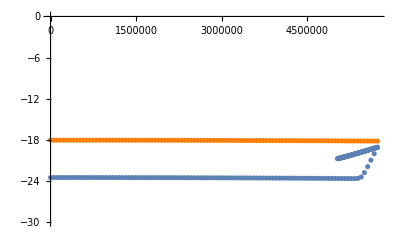

```mathematica
Show[{(*ListPlot[{r,Log10@Abs@ϕEomIn["ϕptotal"]}/.ϕshotconst,PlotStyle->Orange,PlotRange->{Automatic,{-20,0}}],*)
ListPlot[{r,Log10@Abs@(mpD Vgrav[r])}/.ϕshot,PlotRange->{-30,0},PlotStyle->Orange],(*ListPlot[{r,Log10@Abs@ϕ[r]}/.ϕshotconst,PlotStyle->Orange],*)
ListPlot[{r,Log10@Abs["e"ϕ[r]/.SIConstRepl]}/.ϕshot],ListPlot[{r,Log10@Abs["e"ϕ[r]/.SIConstRepl]}/.ϕshotconst]}]
```

```mathematica
"e"/.SIConstRepl
mpD Vgrav[10^6]
```

1.60289×10^-19

-8.5003×10^-19

```mathematica
ϕtotalsol/.λrepl
```

Piecewise[{{0.471004-(113266. ⅇ^(-2.9683×10^6-0.465909 r))/r+(113266. ⅇ^(-2.9683×10^6+0.465909 r))/r, r≤6.371×10^6}, {1.66144-(7.47099×10^6 ⅇ^(0.00706335 (6.371×10^6-r)))/r, r>6.371×10^6}, {0, True}}]

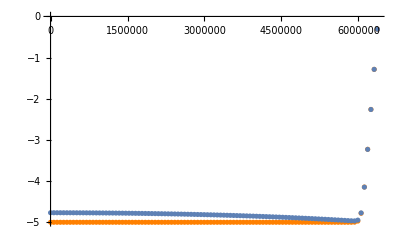

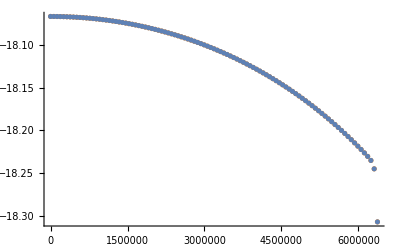

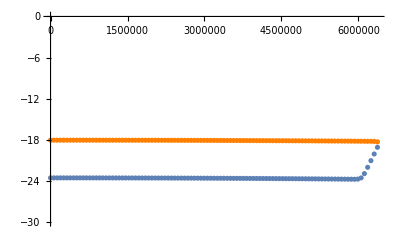

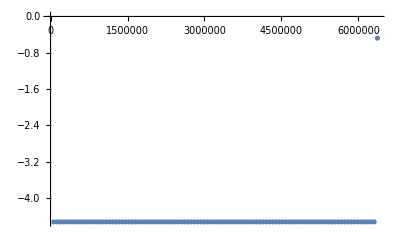

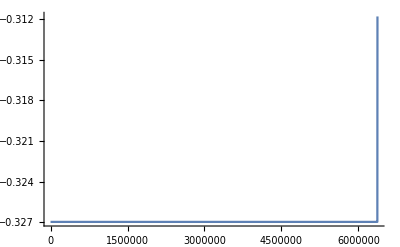

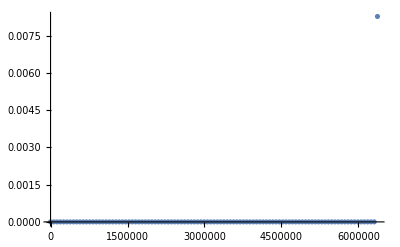

```mathematica
Show[{ListPlot[{r,Log10@Abs@ϕ[r]}/.ϕshotconst,PlotRange->{Automatic,{-5,0}},PlotStyle->Orange],
ListPlot[{r,Log10@Abs@ϕ[r]}/.ϕshot,PlotRange->{Automatic,{-5,0}}]}]
(*ListPlot[Log10@Abs@{r,1/3("rE"E^(0.5 (r-"rE")/183))/r/.EarthRepl}/.ϕshot]*)
Show[{ListPlot[{r,Log10@Abs@ϕEomIn["ϕptotal"]}/.ϕshotconst(*,PlotRange->{Automatic,{-5,0}},*),PlotStyle->Orange],
ListPlot[{r,Log10@Abs@ϕEomIn["ϕptotal"]}/.ϕshot](*,PlotRange->{Automatic,{-5,0}}]*)}]

Show[{(*ListPlot[{r,Log10@Abs@ϕEomIn["ϕptotal"]}/.ϕshotconst,PlotStyle->Orange,PlotRange->{Automatic,{-20,0}}],*)
ListPlot[{r,Log10@Abs@ϕEomIn["ϕptotal"]}/.ϕshot,PlotRange->{-30,0},PlotStyle->Orange],(*ListPlot[{r,Log10@Abs@ϕ[r]}/.ϕshotconst,PlotStyle->Orange],*)
ListPlot[{r,Log10@Abs["e"ϕ[r]/.SIConstRepl]}/.ϕshot]}]
Quiet@ListPlot[{r,Log10@Abs[3 10^-5+1/3("rE"E^(0.5 (r-"rE")/183))/r/.EarthRepl]}/.ϕshot]
Quiet@Plot[Log10@ϕtotalsol/.λrepl,{r,0,"rE"/.EarthRepl}]

(*ListPlot[{Log10@r,Log10[1/3("rE")/r ]+ (0.5 (r-"rE")/183)/Log10[E]/.EarthRepl}/.ϕshot]*)
ListPlot[Abs@{r,y[r]}/.ϕshot,PlotRange->All]
```

```mathematica
ϕshotconst
```

{<|r→6.371×10^6,ϕ[r]→0.488,y[r]→0.00828306|>,<|r→6.32044×10^6,ϕ[r]→0.0649624,y[r]→-1.12095×10^-6|>,<|r→6.26987×10^6,ϕ[r]→0.00865733,y[r]→-1.71239×10^-7|>,<|r→6.21931×10^6,ϕ[r]→0.00116329,y[r]→-2.301×10^-8|>,<|r→6.16875×10^6,ϕ[r]→0.000165859,y[r]→-3.28066×10^-9|>,<|r→6.11818×10^6,ϕ[r]→0.0000331031,y[r]→-6.54749×10^-10|>,<|r→6.06762×10^6,ϕ[r]→0.0000154337,y[r]→-3.05248×10^-10|>,<|r→6.01706×10^6,ϕ[r]→0.000013082,y[r]→-2.5873×10^-10|>,<|r→5.96649×10^6,ϕ[r]→0.000012769,y[r]→-2.52539×10^-10|>,<|r→5.91593×10^6,ϕ[r]→0.0000127273,y[r]→-2.51715×10^-10|>,<|r→5.86537×10^6,ϕ[r]→0.0000127218,y[r]→-2.51605×10^-10|>,<|r→5.8148×10^6,ϕ[r]→0.0000127211,y[r]→-2.51591×10^-10|>,<|r→5.76424×10^6,ϕ[r]→0.000012721,y[r]→-2.51589×10^-10|>,<|r→5.71367×10^6,ϕ[r]→0.0000127209,y[r]→-2.51589×10^-10|>,<|r→5.66311×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→5.61255×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→5.56198×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→5.51142×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→5.46086×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→5.41029×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→5.35973×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→5.30917×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→5.2586×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→5.20804×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→5.15748×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→5.10691×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→5.05635×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→5.00579×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.95522×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.90466×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.8541×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.80353×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.75297×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.7024×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.65184×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.60128×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.55071×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.50015×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.44959×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.39902×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.34846×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.2979×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.24733×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.19677×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.14621×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.09564×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→4.04508×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.99452×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.94395×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.89339×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.84283×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.79226×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.7417×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.69113×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.64057×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.59001×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.53944×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.48888×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.43832×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.38775×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.33719×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.28663×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.23606×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.1855×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.13494×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.08437×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→3.03381×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.98325×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.93268×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.88212×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.83156×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.78099×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.73043×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.67987×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.6293×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.57874×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.52817×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.47761×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.42705×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.37648×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.32592×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.27536×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.22479×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.17423×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.12367×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.0731×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→2.02254×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.97198×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.92141×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.87085×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.82029×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.76972×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.71916×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.6686×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.61803×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.56747×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.5169×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.46634×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.41578×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.36521×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.31465×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.26409×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.21352×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.16296×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.1124×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.06183×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.01127×10^6,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→960706.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→910143.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→859579.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→809016.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→758452.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→707889.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→657325.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→606762.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→556198.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→505635.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→455071.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→404508.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→353944.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→303381.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→252817.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→202254.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→151690.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→101127.,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→50563.5,ϕ[r]→0.0000127209,y[r]→-2.51588×10^-10|>,<|r→1.91067×10^-8,ϕ[r]→0.0000127209,y[r]→-2.51587×10^-10|>}

#### Try increasing from r=0

```mathematica
bcs={ϕEp->0.0,ϕE->0.488}(*BC from TH analytic solution*)

ϕEomIn=Assuming[r<"rE"/.Constants`EarthRepl (*1*),Getϕeom[mpD,10^0,meDbympD,<|"βp"->"βcore"/.Constants`EarthRepl,"βe"->βD|>,(*10^-9*)5 10^-2,False]//Simplify]
NMFPS=100000;
NMFPS ϕEomIn["λD"]/.r->"rE"/.EarthRepl;
(*ϕshot=Monitor[Shootϕimplict[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn["ϕeom"]//Simplify],ϕE/.bcs,ϕEp/.bcs,Round@10^2.1(*,NMFPS ϕEomIn["λD"]/.r->"rE"/.EarthRepl*)],nr];*)
ϕshotincreasing=Monitor[Shootϕimplict[Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn["ϕeom"]//Simplify],ϕE/.bcs,ϕEp/.bcs,Round@(10^2.1),(*,NMFPS ϕEomIn["λD"]/.r->"rE"/.EarthRepl*)"rE"/.EarthRepl,True],nr];
(*ϕshotND=NDSolve[{Assuming[r<"rE"/.Constants`EarthRepl,ϕEomIn["ϕeom"]//Simplify],ϕ["rE"/.EarthRepl]==ϕE/.bcs,ϕ'["rE"/.EarthRepl]==ϕEp/.bcs},ϕ,({r,"rE"-#,"rE"}/.EarthRepl)&[NMFPS ϕEomIn["λD"]/.r->"rE"/.EarthRepl]][[1]];*)

(*Plot[Log10@ϕ[10^logr]/.ϕshotND,{logr,Log10@(ϕ/.ϕshotND)["Domain"][[1,1]],Log10@(ϕ/.ϕshotND)["Domain"][[1,2]]}]*)
```

{ϕEp→0.,ϕE→0.488}

<|ϕeom→-(2 r ϕ'[r]+r^2 ϕ''[r])/r^2==0.0000828555-0.000148592 ϕ[r],λD→82.0356,ϕptotal→-5.71379×10^-19+1.60289×10^-19 ϕ[r],ϕetotal→-5.71379×10^-23-1.60289×10^-19 ϕ[r]|>

should include a convergence criteria flag based on analytics.

Solving over r ∈ (0., 6.371×10^6) with step size 50563.5

{y[r+Δr],ϕ[r+Δr]}=={0.0000828555+(0.000165711 Δr)/r+y[r]+(2. Δr y[r])/r-0.000148592 Δr ϕ[r],-0.0000828555 Δr-Δr y[r]+ϕ[r]}

Power::infy: Infinite expression 1/0 encountered.

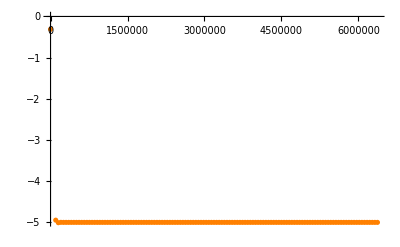

```mathematica
Show[{ListPlot[{r,Log10@Abs@ϕ[r]}/.ϕshotincreasing,PlotRange->{Automatic,{-5,0}},PlotStyle->Orange]}]
```

#### Status 14/4/24

Issue is that this is dropping off too quickly. I think the reason is just that in the implicit method Δr >> λD is required for convergence. But that also means that you have to be on scales much larger than the drop off. So you continue decreasing and overshoot in the first couple of steps. 

One option would be to start a little further in, then we skip over the drop. And we know the BCs there. Doesn’t seem to help.

### Get δ(δ)

#### Compute δ truth over list of PDicts

```mathematica
Clear[δScanList]
(*δScanList = {<|"δ"->10^-5,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\08_05_2025_0p99999\\PDictList\\PDictList_ϕE_100_pcnt_0"|>,
<|"δ"->1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_04_2025_0p0\\PDictList\\PDictList_ϕE_0_pcnt_0"|>,
<|"δ"->10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\10_05_2025_0p9\\PDictList\\PDictList_ϕE_90_pcnt_0"|>,
<|"δ"->9 10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p1\\PDictList\\PDictList_ϕE_10_pcnt_0"|>,
<|"δ"->10^-2,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p99\\PDictList\\PDictList_ϕE_99_pcnt_0"|>};*)
δScanList = {<|"δ"->10^-5,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\08_05_2025_0p99999\\PDictList\\PDictList_ϕE_100_pcnt_0"|>,
<|"δ"->1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_04_2025_0p0\\PDictList\\PDictList_ϕE_0_pcnt_0"|>,
<|"δ"->10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\10_05_2025_0p9\\PDictList\\PDictList_ϕE_90_pcnt_0"|>,
<|"δ"->9 10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p1\\PDictList\\PDictList_ϕE_10_pcnt_0"|>,
<|"δ"->10^-2,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p99\\PDictList\\PDictList_ϕE_99_pcnt_0"|>,
<|"δ"->0.65,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p35\\PDictList\\PDictList_ϕE_35_pcnt_0"|>,
<|"δ"->0.35,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p65\\PDictList\\PDictList_ϕE_65_pcnt_0"|>};
```

```mathematica
(*ComputeδonScan[δList_,v0ind_:1]:= Module[{returnδList,PDict,δtable},

returnδList ={};

Monitor[
Do[
Print[δList[[δ]]["δ"]];
PDict= ReadIt[δList[[δ]]["file"]][[;;9,v0ind,;;]];

δtable=Flatten[Table[Table[{Log10[("mpD"("c")^2)/("JpereV")]/.PDict[[i,j]]/.SIConstRepl,Log10["κ"]/.PDict[[i,j]],Log10@"δ"/.getδfromPDict[PDict[[i,j]]]},{i,Dimensions[PDict][[1]]}],{j,Dimensions[PDict][[2]]}],1];

PDict["δtable"]=δtable;
AppendTo[returnδList,δtable];

,{δ,Length[δList]}]
,{δ,i,j}];

returnδList
]*)
```

```mathematica
computedδscanDisk10m4=ComputeδonScan[δScanList,1]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

FindRoot::jsing: Encountered a singular Jacobian at the point {Private`rmax} = {3.1855×10^16}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

{<|δ→1/100000,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\08_05_2025_0p99999\PDictList\PDictList_ϕE_100_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.12491},{7.,-Log[100000000000000]/Log[10],-0.125128},{8.,-Log[100000000000000]/Log[10],-0.126585},{9.,-Log[100000000000000]/Log[10],-0.124913},{10.,-Log[100000000000000]/Log[10],-0.124921},{11.,-Log[100000000000000]/Log[10],-0.124918},{12.,-Log[100000000000000]/Log[10],-0.124904},{13.,-Log[100000000000000]/Log[10],-0.123942},{14.,-Log[100000000000000]/Log[10],-0.037364},{6.,-Log[10000000000000]/Log[10],-0.124988},{7.,-Log[10000000000000]/Log[10],-0.126366},{8.,-Log[10000000000000]/Log[10],-0.126586},{9.,-Log[10000000000000]/Log[10],-0.124913},{10.,-Log[10000000000000]/Log[10],-0.124926},{11.,-Log[10000000000000]/Log[10],-0.12493},{12.,-Log[10000000000000]/Log[10],-0.124913},{13.,-Log[10000000000000]/Log[10],-0.123951},{14.,-Log[10000000000000]/Log[10],-0.0373915},{6.,-Log[1000000000000]/Log[10],-0.125478},{7.,-Log[1000000000000]/Log[10],-0.126572},{8.,-Log[1000000000000]/Log[10],-0.127137},{9.,-Log[1000000000000]/Log[10],-0.124914},{10.,-Log[1000000000000]/Log[10],-0.125542},{11.,-Log[1000000000000]/Log[10],-0.125366},{12.,-Log[1000000000000]/Log[10],-0.125148},{13.,-Log[1000000000000]/Log[10],-0.124173},{14.,-Log[1000000000000]/Log[10],-0.0705616},{6.,-Log[100000000000]/Log[10],-0.126562},{7.,-Log[100000000000]/Log[10],-0.127149},{8.,-Log[100000000000]/Log[10],-0.126969},{9.,-Log[100000000000]/Log[10],-1.41754},{10.,-Log[100000000000]/Log[10],-0.134682},{11.,-Log[100000000000]/Log[10],-0.129363},{12.,-Log[100000000000]/Log[10],-0.656385},{13.,-Log[100000000000]/Log[10],-0.595915},{14.,-Log[100000000000]/Log[10],-0.654855},{6.,-Log[10000000000]/Log[10],-0.127103},{7.,-Log[10000000000]/Log[10],-0.126939},{8.,-Log[10000000000]/Log[10],-2.97662},{9.,-Log[10000000000]/Log[10],-3.1853},{10.,-Log[10000000000]/Log[10],-2.31416},{11.,-Log[10000000000]/Log[10],-1.80764},{12.,-Log[10000000000]/Log[10],-1.64698},{13.,-Log[10000000000]/Log[10],-1.60416},{14.,-Log[10000000000]/Log[10],-1.86486},{6.,-Log[1000000000]/Log[10],-0.126936},{7.,-Log[1000000000]/Log[10],-0.137406},{8.,-Log[1000000000]/Log[10],-4.92917},{9.,-Log[1000000000]/Log[10],-4.47223},{10.,-Log[1000000000]/Log[10],-3.78984},{11.,-Log[1000000000]/Log[10],-3.11621},{12.,-Log[1000000000]/Log[10],-2.76882},{13.,-Log[1000000000]/Log[10],-2.66178},{14.,-Log[1000000000]/Log[10],-2.92654},{6.,-Log[100000000]/Log[10],-0.136119},{7.,-Log[100000000]/Log[10],-5.42384},{8.,-Log[100000000]/Log[10],-4.92917},{9.,-Log[100000000]/Log[10],-4.47223},{10.,-Log[100000000]/Log[10],-4.20956},{11.,-Log[100000000]/Log[10],-4.29487},{12.,-Log[100000000]/Log[10],-4.24791},{13.,-Log[100000000]/Log[10],-3.99087},{14.,-Log[100000000]/Log[10],-4.07588},{6.,-Log[10000000]/Log[10],-5.92304},{7.,-Log[10000000]/Log[10],-5.42384},{8.,-Log[10000000]/Log[10],-4.92917},{9.,-Log[10000000]/Log[10],-4.47223},{10.,-Log[10000000]/Log[10],-4.20956},{11.,-Log[10000000]/Log[10],-4.29482},{12.,-Log[10000000]/Log[10],-4.66732},{13.,-Log[10000000]/Log[10],-5.17262},{14.,-Log[10000000]/Log[10],-5.56424}},v0→20000,meDbympD→0.0001|>,<|δ→1,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\21_04_2025_0p0\PDictList\PDictList_ϕE_0_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.127907},{7.,-Log[100000000000000]/Log[10],-0.182668},{8.,-Log[100000000000000]/Log[10],-0.194304},{9.,-Log[100000000000000]/Log[10],-0.243558},{10.,-Log[100000000000000]/Log[10],-2.0968},{11.,-Log[100000000000000]/Log[10],-2.06942},{12.,-Log[100000000000000]/Log[10],-1.53343},{13.,-Log[100000000000000]/Log[10],-1.0626},{14.,-Log[100000000000000]/Log[10],-0.590395},{6.,-Log[10000000000000]/Log[10],-0.127907},{7.,-Log[10000000000000]/Log[10],-0.182668},{8.,-Log[10000000000000]/Log[10],-0.214568},{9.,-Log[10000000000000]/Log[10],-0.267022},{10.,-Log[10000000000000]/Log[10],-2.17129},{11.,-Log[10000000000000]/Log[10],-3.14328},{12.,-Log[10000000000000]/Log[10],-2.58704},{13.,-Log[10000000000000]/Log[10],-2.00346},{14.,-Log[10000000000000]/Log[10],-1.51638},{6.,-Log[1000000000000]/Log[10],-0.127907},{7.,-Log[1000000000000]/Log[10],-0.200844},{8.,-Log[1000000000000]/Log[10],-0.216016},{9.,-Log[1000000000000]/Log[10],-0.269047},{10.,-Log[1000000000000]/Log[10],-2.18272},{11.,-Log[1000000000000]/Log[10],-4.15405},{12.,-Log[1000000000000]/Log[10],-3.62177},{13.,-Log[1000000000000]/Log[10],-3.11841},{14.,-Log[1000000000000]/Log[10],-2.58232},{6.,-Log[100000000000]/Log[10],-0.12828},{7.,-Log[100000000000]/Log[10],-0.201685},{8.,-Log[100000000000]/Log[10],-0.204789},{9.,-Log[100000000000]/Log[10],-0.263423},{10.,-Log[100000000000]/Log[10],-2.3171},{11.,-Log[100000000000]/Log[10],-5.1359},{12.,-Log[100000000000]/Log[10],-4.60123},{13.,-Log[100000000000]/Log[10],-4.09997},{14.,-Log[100000000000]/Log[10],-3.60378},{6.,-Log[10000000000]/Log[10],-0.12889},{7.,-Log[10000000000]/Log[10],-0.209614},{8.,-Log[10000000000]/Log[10],-0.673298},{9.,-Log[10000000000]/Log[10],-0.94909},{10.,-Log[10000000000]/Log[10],-6.62512},{11.,-Log[10000000000]/Log[10],-6.0979},{12.,-Log[10000000000]/Log[10],-5.53833},{13.,-Log[10000000000]/Log[10],-5.03361},{14.,-Log[10000000000]/Log[10],-4.53367},{6.,-Log[1000000000]/Log[10],-0.207},{7.,-Log[1000000000]/Log[10],-0.963693},{8.,-Log[1000000000]/Log[10],-2.02167},{9.,-Log[1000000000]/Log[10],-2.27059},{10.,-Log[1000000000]/Log[10],-8.07917},{11.,-Log[1000000000]/Log[10],-7.31539},{12.,-Log[1000000000]/Log[10],-6.5511},{13.,-Log[1000000000]/Log[10],-5.94641},{14.,-Log[1000000000]/Log[10],-5.43219},{6.,-Log[100000000]/Log[10],-0.724239},{7.,-Log[100000000]/Log[10],-2.39025},{8.,-Log[100000000]/Log[10],-2.02165},{9.,-Log[100000000]/Log[10],-2.29913},{10.,-Log[100000000]/Log[10],-8.35105},{11.,-Log[100000000]/Log[10],-8.35105},{12.,-Log[100000000]/Log[10],-8.10595},{13.,-Log[100000000]/Log[10],-7.26171},{14.,-Log[100000000]/Log[10],-6.54935},{6.,-Log[10000000]/Log[10],-3.56431},{7.,-Log[10000000]/Log[10],-4.29226},{8.,-Log[10000000]/Log[10],-2.02165},{9.,-Log[10000000]/Log[10],-4.20351},{10.,-Log[10000000]/Log[10],-8.35105},{11.,-Log[10000000]/Log[10],-8.35105},{12.,-Log[10000000]/Log[10],-8.35105},{13.,-Log[10000000]/Log[10],-8.35105},{14.,-Log[10000000]/Log[10],-8.10665}},v0→20000,meDbympD→0.0001|>,<|δ→1/10,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\10_05_2025_0p9\PDictList\PDictList_ϕE_90_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.125168},{7.,-Log[100000000000000]/Log[10],-0.131697},{8.,-Log[100000000000000]/Log[10],-0.139031},{9.,-Log[100000000000000]/Log[10],-0.144321},{10.,-Log[100000000000000]/Log[10],-0.153575},{11.,-Log[100000000000000]/Log[10],-1.17789},{12.,-Log[100000000000000]/Log[10],-1.51143},{13.,-Log[100000000000000]/Log[10],-1.04699},{14.,-Log[100000000000000]/Log[10],-0.583487},{6.,-Log[10000000000000]/Log[10],-0.125168},{7.,-Log[10000000000000]/Log[10],-0.131697},{8.,-Log[10000000000000]/Log[10],-0.143028},{9.,-Log[10000000000000]/Log[10],-0.144568},{10.,-Log[10000000000000]/Log[10],-0.155935},{11.,-Log[10000000000000]/Log[10],-1.20263},{12.,-Log[10000000000000]/Log[10],-2.59518},{13.,-Log[10000000000000]/Log[10],-2.07069},{14.,-Log[10000000000000]/Log[10],-1.51931},{6.,-Log[1000000000000]/Log[10],-0.125168},{7.,-Log[1000000000000]/Log[10],-0.133827},{8.,-Log[1000000000000]/Log[10],-0.143264},{9.,-Log[1000000000000]/Log[10],-0.144244},{10.,-Log[1000000000000]/Log[10],-0.155894},{11.,-Log[1000000000000]/Log[10],-1.20282},{12.,-Log[1000000000000]/Log[10],-3.58473},{13.,-Log[1000000000000]/Log[10],-3.08886},{14.,-Log[1000000000000]/Log[10],-2.59511},{6.,-Log[100000000000]/Log[10],-0.125168},{7.,-Log[100000000000]/Log[10],-0.133937},{8.,-Log[100000000000]/Log[10],-0.141664},{9.,-Log[100000000000]/Log[10],-0.15673},{10.,-Log[100000000000]/Log[10],-0.192903},{11.,-Log[100000000000]/Log[10],-5.01714},{12.,-Log[100000000000]/Log[10],-4.51361},{13.,-Log[100000000000]/Log[10],-4.0148},{14.,-Log[100000000000]/Log[10],-3.51752},{6.,-Log[10000000000]/Log[10],-0.125257},{7.,-Log[10000000000]/Log[10],-0.141561},{8.,-Log[10000000000]/Log[10],-0.570461},{9.,-Log[10000000000]/Log[10],-0.512343},{10.,-Log[10000000000]/Log[10],-0.726571},{11.,-Log[10000000000]/Log[10],-5.94146},{12.,-Log[10000000000]/Log[10],-5.41378},{13.,-Log[10000000000]/Log[10],-4.89223},{14.,-Log[10000000000]/Log[10],-4.38872},{6.,-Log[1000000000]/Log[10],-0.143695},{7.,-Log[1000000000]/Log[10],-0.237688},{8.,-Log[1000000000]/Log[10],-2.12036},{9.,-Log[1000000000]/Log[10],-1.90903},{10.,-Log[1000000000]/Log[10],-2.07837},{11.,-Log[1000000000]/Log[10],-7.31418},{12.,-Log[1000000000]/Log[10],-6.57362},{13.,-Log[1000000000]/Log[10],-5.92404},{14.,-Log[1000000000]/Log[10],-5.39611},{6.,-Log[100000000]/Log[10],-0.537591},{7.,-Log[100000000]/Log[10],-4.5043},{8.,-Log[100000000]/Log[10],-2.19699},{9.,-Log[100000000]/Log[10],-1.90903},{10.,-Log[100000000]/Log[10],-4.32339},{11.,-Log[100000000]/Log[10],-8.32125},{12.,-Log[100000000]/Log[10],-7.99167},{13.,-Log[100000000]/Log[10],-7.31576},{14.,-Log[100000000]/Log[10],-6.57458},{6.,-Log[10000000]/Log[10],-2.76291},{7.,-Log[10000000]/Log[10],-4.5043},{8.,-Log[10000000]/Log[10],-4.03649},{9.,-Log[10000000]/Log[10],-3.84586},{10.,-Log[10000000]/Log[10],-4.32339},{11.,-Log[10000000]/Log[10],-8.32125},{12.,-Log[10000000]/Log[10],-8.32125},{13.,-Log[10000000]/Log[10],-8.32125},{14.,-Log[10000000]/Log[10],-7.99283}},v0→20000,meDbympD→0.0001|>,<|δ→9/10,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\11_05_2025_0p1\PDictList\PDictList_ϕE_10_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.127279},{7.,-Log[100000000000000]/Log[10],-0.170404},{8.,-Log[100000000000000]/Log[10],-0.183757},{9.,-Log[100000000000000]/Log[10],-0.234182},{10.,-Log[100000000000000]/Log[10],-1.81506},{11.,-Log[100000000000000]/Log[10],-2.08245},{12.,-Log[100000000000000]/Log[10],-1.5692},{13.,-Log[100000000000000]/Log[10],-1.09661},{14.,-Log[100000000000000]/Log[10],-0.634502},{6.,-Log[10000000000000]/Log[10],-0.127279},{7.,-Log[10000000000000]/Log[10],-0.170404},{8.,-Log[10000000000000]/Log[10],-0.202756},{9.,-Log[10000000000000]/Log[10],-0.252847},{10.,-Log[10000000000000]/Log[10],-1.89634},{11.,-Log[10000000000000]/Log[10],-3.15946},{12.,-Log[10000000000000]/Log[10],-2.62119},{13.,-Log[10000000000000]/Log[10],-2.03952},{14.,-Log[10000000000000]/Log[10],-1.56136},{6.,-Log[1000000000000]/Log[10],-0.127279},{7.,-Log[1000000000000]/Log[10],-0.185355},{8.,-Log[1000000000000]/Log[10],-0.204048},{9.,-Log[1000000000000]/Log[10],-0.254874},{10.,-Log[1000000000000]/Log[10],-1.9067},{11.,-Log[1000000000000]/Log[10],-4.17161},{12.,-Log[1000000000000]/Log[10],-3.65354},{13.,-Log[1000000000000]/Log[10],-3.15136},{14.,-Log[1000000000000]/Log[10],-2.63724},{6.,-Log[100000000000]/Log[10],-0.12728},{7.,-Log[100000000000]/Log[10],-0.186082},{8.,-Log[100000000000]/Log[10],-0.195163},{9.,-Log[100000000000]/Log[10],-0.248391},{10.,-Log[100000000000]/Log[10],-2.09292},{11.,-Log[100000000000]/Log[10],-5.14589},{12.,-Log[100000000000]/Log[10],-4.62469},{13.,-Log[100000000000]/Log[10],-4.12413},{14.,-Log[100000000000]/Log[10],-3.62645},{6.,-Log[10000000000]/Log[10],-0.128042},{7.,-Log[10000000000]/Log[10],-0.193218},{8.,-Log[10000000000]/Log[10],-0.627775},{9.,-Log[10000000000]/Log[10],-1.00347},{10.,-Log[10000000000]/Log[10],-6.61642},{11.,-Log[10000000000]/Log[10],-6.09682},{12.,-Log[10000000000]/Log[10],-5.55473},{13.,-Log[10000000000]/Log[10],-5.05024},{14.,-Log[10000000000]/Log[10],-4.55063},{6.,-Log[1000000000]/Log[10],-0.191882},{7.,-Log[1000000000]/Log[10],-0.722884},{8.,-Log[1000000000]/Log[10],-2.02041},{9.,-Log[1000000000]/Log[10],-2.22385},{10.,-Log[1000000000]/Log[10],-8.08259},{11.,-Log[1000000000]/Log[10],-7.36359},{12.,-Log[1000000000]/Log[10],-6.53651},{13.,-Log[1000000000]/Log[10],-5.96881},{14.,-Log[1000000000]/Log[10],-5.44551},{6.,-Log[100000000]/Log[10],-0.626251},{7.,-Log[100000000]/Log[10],-2.39775},{8.,-Log[100000000]/Log[10],-2.02039},{9.,-Log[100000000]/Log[10],-2.25297},{10.,-Log[100000000]/Log[10],-8.33237},{11.,-Log[100000000]/Log[10],-8.34825},{12.,-Log[100000000]/Log[10],-8.09582},{13.,-Log[100000000]/Log[10],-7.36019},{14.,-Log[100000000]/Log[10],-6.54721},{6.,-Log[10000000]/Log[10],-3.53835},{7.,-Log[10000000]/Log[10],-4.29999},{8.,-Log[10000000]/Log[10],-2.1523},{9.,-Log[10000000]/Log[10],-4.15676},{10.,-Log[10000000]/Log[10],-8.33237},{11.,-Log[10000000]/Log[10],-8.34825},{12.,-Log[10000000]/Log[10],-8.34825},{13.,-Log[10000000]/Log[10],-8.34825},{14.,-Log[10000000]/Log[10],-8.09658}},v0→20000,meDbympD→0.0001|>,<|δ→1/100,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\11_05_2025_0p99\PDictList\PDictList_ϕE_99_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.124935},{7.,-Log[100000000000000]/Log[10],-0.127816},{8.,-Log[100000000000000]/Log[10],-0.127847},{9.,-Log[100000000000000]/Log[10],-0.128923},{10.,-Log[100000000000000]/Log[10],-0.129123},{11.,-Log[100000000000000]/Log[10],-0.131038},{12.,-Log[100000000000000]/Log[10],-1.47827},{13.,-Log[100000000000000]/Log[10],-0.967338},{14.,-Log[100000000000000]/Log[10],-0.500856},{6.,-Log[10000000000000]/Log[10],-0.124935},{7.,-Log[10000000000000]/Log[10],-0.127816},{8.,-Log[10000000000000]/Log[10],-0.128746},{9.,-Log[10000000000000]/Log[10],-0.128981},{10.,-Log[10000000000000]/Log[10],-0.12918},{11.,-Log[10000000000000]/Log[10],-0.131131},{12.,-Log[10000000000000]/Log[10],-2.50783},{13.,-Log[10000000000000]/Log[10],-2.02783},{14.,-Log[10000000000000]/Log[10],-1.5447},{6.,-Log[1000000000000]/Log[10],-0.124935},{7.,-Log[1000000000000]/Log[10],-0.127816},{8.,-Log[1000000000000]/Log[10],-0.128786},{9.,-Log[1000000000000]/Log[10],-0.128594},{10.,-Log[1000000000000]/Log[10],-0.128982},{11.,-Log[1000000000000]/Log[10],-0.131125},{12.,-Log[1000000000000]/Log[10],-2.61433},{13.,-Log[1000000000000]/Log[10],-2.97241},{14.,-Log[1000000000000]/Log[10],-2.48105},{6.,-Log[100000000000]/Log[10],-0.124935},{7.,-Log[100000000000]/Log[10],-0.128785},{8.,-Log[100000000000]/Log[10],-0.128428},{9.,-Log[100000000000]/Log[10],-0.145203},{10.,-Log[100000000000]/Log[10],-0.142376},{11.,-Log[100000000000]/Log[10],-0.154207},{12.,-Log[100000000000]/Log[10],-4.31143},{13.,-Log[100000000000]/Log[10],-3.82336},{14.,-Log[100000000000]/Log[10],-3.32784},{6.,-Log[10000000000]/Log[10],-0.124948},{7.,-Log[10000000000]/Log[10],-0.128363},{8.,-Log[10000000000]/Log[10],-0.564224},{9.,-Log[10000000000]/Log[10],-0.707052},{10.,-Log[10000000000]/Log[10],-0.35376},{11.,-Log[10000000000]/Log[10],-0.387689},{12.,-Log[10000000000]/Log[10],-5.29214},{13.,-Log[10000000000]/Log[10],-4.8021},{14.,-Log[10000000000]/Log[10],-4.28614},{6.,-Log[1000000000]/Log[10],-0.138226},{7.,-Log[1000000000]/Log[10],-1.02095},{8.,-Log[1000000000]/Log[10],-2.31998},{9.,-Log[1000000000]/Log[10],-1.8833},{10.,-Log[1000000000]/Log[10],-1.56474},{11.,-Log[1000000000]/Log[10],-3.48863},{12.,-Log[1000000000]/Log[10],-6.53255},{13.,-Log[1000000000]/Log[10],-5.89887},{14.,-Log[1000000000]/Log[10],-5.33734},{6.,-Log[100000000]/Log[10],-0.137812},{7.,-Log[100000000]/Log[10],-4.74727},{8.,-Log[100000000]/Log[10],-4.25695},{9.,-Log[100000000]/Log[10],-3.92373},{10.,-Log[100000000]/Log[10],-3.96117},{11.,-Log[100000000]/Log[10],-4.5926},{12.,-Log[100000000]/Log[10],-7.92581},{13.,-Log[100000000]/Log[10],-7.20812},{14.,-Log[100000000]/Log[10],-6.53384},{6.,-Log[10000000]/Log[10],-2.03701},{7.,-Log[10000000]/Log[10],-4.74726},{8.,-Log[10000000]/Log[10],-4.25695},{9.,-Log[10000000]/Log[10],-3.92373},{10.,-Log[10000000]/Log[10],-3.96117},{11.,-Log[10000000]/Log[10],-4.5926},{12.,-Log[10000000]/Log[10],-8.31522},{13.,-Log[10000000]/Log[10],-8.31522},{14.,-Log[10000000]/Log[10],-7.92718}},v0→20000,meDbympD→0.0001|>,<|δ→0.65,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\15_05_2025_0p35\PDictList\PDictList_ϕE_35_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.126643},{7.,-Log[100000000000000]/Log[10],-0.159127},{8.,-Log[100000000000000]/Log[10],-0.172872},{9.,-Log[100000000000000]/Log[10],-0.199453},{10.,-Log[100000000000000]/Log[10],-1.11454},{11.,-Log[100000000000000]/Log[10],-2.0692},{12.,-Log[100000000000000]/Log[10],-1.56068},{13.,-Log[100000000000000]/Log[10],-1.09001},{14.,-Log[100000000000000]/Log[10],-0.627771},{6.,-Log[10000000000000]/Log[10],-0.126643},{7.,-Log[10000000000000]/Log[10],-0.159127},{8.,-Log[10000000000000]/Log[10],-0.187953},{9.,-Log[10000000000000]/Log[10],-0.211651},{10.,-Log[10000000000000]/Log[10],-1.19406},{11.,-Log[10000000000000]/Log[10],-3.14794},{12.,-Log[10000000000000]/Log[10],-2.62092},{13.,-Log[10000000000000]/Log[10],-2.03304},{14.,-Log[10000000000000]/Log[10],-1.5545},{6.,-Log[1000000000000]/Log[10],-0.126643},{7.,-Log[1000000000000]/Log[10],-0.169292},{8.,-Log[1000000000000]/Log[10],-0.18899},{9.,-Log[1000000000000]/Log[10],-0.212778},{10.,-Log[1000000000000]/Log[10],-1.20254},{11.,-Log[1000000000000]/Log[10],-4.15948},{12.,-Log[1000000000000]/Log[10],-3.64424},{13.,-Log[1000000000000]/Log[10],-3.14388},{14.,-Log[1000000000000]/Log[10],-2.63762},{6.,-Log[100000000000]/Log[10],-0.126643},{7.,-Log[100000000000]/Log[10],-0.169828},{8.,-Log[100000000000]/Log[10],-0.179852},{9.,-Log[100000000000]/Log[10],-0.219349},{10.,-Log[100000000000]/Log[10],-4.39379},{11.,-Log[100000000000]/Log[10],-5.12867},{12.,-Log[100000000000]/Log[10],-4.61277},{13.,-Log[100000000000]/Log[10],-4.11109},{14.,-Log[100000000000]/Log[10],-3.6135},{6.,-Log[10000000000]/Log[10],-0.127186},{7.,-Log[10000000000]/Log[10],-0.180855},{8.,-Log[10000000000]/Log[10],-0.580631},{9.,-Log[10000000000]/Log[10],-0.895544},{10.,-Log[10000000000]/Log[10],-5.34958},{11.,-Log[10000000000]/Log[10],-6.07659},{12.,-Log[10000000000]/Log[10],-5.53813},{13.,-Log[10000000000]/Log[10],-5.03323},{14.,-Log[10000000000]/Log[10],-4.53356},{6.,-Log[1000000000]/Log[10],-0.180118},{7.,-Log[1000000000]/Log[10],-0.630762},{8.,-Log[1000000000]/Log[10],-2.01554},{9.,-Log[1000000000]/Log[10],-2.10833},{10.,-Log[1000000000]/Log[10],-6.8186},{11.,-Log[1000000000]/Log[10],-7.38873},{12.,-Log[1000000000]/Log[10],-6.58103},{13.,-Log[1000000000]/Log[10],-5.95372},{14.,-Log[1000000000]/Log[10],-5.4428},{6.,-Log[100000000]/Log[10],-0.557499},{7.,-Log[100000000]/Log[10],-2.42192},{8.,-Log[100000000]/Log[10],-2.01553},{9.,-Log[100000000]/Log[10],-2.13913},{10.,-Log[100000000]/Log[10],-7.0915},{11.,-Log[100000000]/Log[10],-8.34095},{12.,-Log[100000000]/Log[10],-8.06524},{13.,-Log[100000000]/Log[10],-7.41998},{14.,-Log[100000000]/Log[10],-6.57913},{6.,-Log[10000000]/Log[10],-3.3952},{7.,-Log[10000000]/Log[10],-4.32505},{8.,-Log[10000000]/Log[10],-2.13718},{9.,-Log[10000000]/Log[10],-4.0423},{10.,-Log[10000000]/Log[10],-7.0915},{11.,-Log[10000000]/Log[10],-8.34095},{12.,-Log[10000000]/Log[10],-8.34095},{13.,-Log[10000000]/Log[10],-8.34095},{14.,-Log[10000000]/Log[10],-8.06725}},v0→20000,meDbympD→0.0001|>,<|δ→0.35,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\15_05_2025_0p65\PDictList\PDictList_ϕE_65_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.125812},{7.,-Log[100000000000000]/Log[10],-0.143018},{8.,-Log[100000000000000]/Log[10],-0.156067},{9.,-Log[100000000000000]/Log[10],-0.166913},{10.,-Log[100000000000000]/Log[10],-0.387963},{11.,-Log[100000000000000]/Log[10],-2.0583},{12.,-Log[100000000000000]/Log[10],-1.54131},{13.,-Log[100000000000000]/Log[10],-1.07582},{14.,-Log[100000000000000]/Log[10],-0.613024},{6.,-Log[10000000000000]/Log[10],-0.125812},{7.,-Log[10000000000000]/Log[10],-0.143018},{8.,-Log[10000000000000]/Log[10],-0.167284},{9.,-Log[10000000000000]/Log[10],-0.175245},{10.,-Log[10000000000000]/Log[10],-0.418113},{11.,-Log[10000000000000]/Log[10],-3.11436},{12.,-Log[10000000000000]/Log[10],-2.57023},{13.,-Log[10000000000000]/Log[10],-2.04788},{14.,-Log[10000000000000]/Log[10],-1.53934},{6.,-Log[1000000000000]/Log[10],-0.125812},{7.,-Log[1000000000000]/Log[10],-0.148546},{8.,-Log[1000000000000]/Log[10],-0.167475},{9.,-Log[1000000000000]/Log[10],-0.175891},{10.,-Log[1000000000000]/Log[10],-0.421741},{11.,-Log[1000000000000]/Log[10],-4.12235},{12.,-Log[1000000000000]/Log[10],-3.61743},{13.,-Log[1000000000000]/Log[10],-3.12053},{14.,-Log[1000000000000]/Log[10],-2.62178},{6.,-Log[100000000000]/Log[10],-0.125812},{7.,-Log[100000000000]/Log[10],-0.148946},{8.,-Log[100000000000]/Log[10],-0.161197},{9.,-Log[100000000000]/Log[10],-0.185157},{10.,-Log[100000000000]/Log[10],-0.938259},{11.,-Log[100000000000]/Log[10],-5.08353},{12.,-Log[100000000000]/Log[10],-4.57643},{13.,-Log[100000000000]/Log[10],-4.07723},{14.,-Log[100000000000]/Log[10],-3.57981},{6.,-Log[10000000000]/Log[10],-0.126104},{7.,-Log[10000000000]/Log[10],-0.161943},{8.,-Log[10000000000]/Log[10],-0.530568},{9.,-Log[10000000000]/Log[10],-0.754657},{10.,-Log[10000000000]/Log[10],-1.89331},{11.,-Log[10000000000]/Log[10],-6.05146},{12.,-Log[10000000000]/Log[10],-5.4885},{13.,-Log[10000000000]/Log[10],-4.98155},{14.,-Log[10000000000]/Log[10],-4.48177},{6.,-Log[1000000000]/Log[10],-0.161685},{7.,-Log[1000000000]/Log[10],-0.428906},{8.,-Log[1000000000]/Log[10],-2.0513},{9.,-Log[1000000000]/Log[10],-2.00176},{10.,-Log[1000000000]/Log[10],-5.27081},{11.,-Log[1000000000]/Log[10],-7.42558},{12.,-Log[1000000000]/Log[10],-6.54089},{13.,-Log[1000000000]/Log[10],-5.95969},{14.,-Log[1000000000]/Log[10],-5.40443},{6.,-Log[100000000]/Log[10],-1.35588},{7.,-Log[100000000]/Log[10],-2.47391},{8.,-Log[100000000]/Log[10],-2.05129},{9.,-Log[100000000]/Log[10],-2.02217},{10.,-Log[100000000]/Log[10],-5.57271},{11.,-Log[100000000]/Log[10],-8.33126},{12.,-Log[100000000]/Log[10],-8.06236},{13.,-Log[100000000]/Log[10],-7.42606},{14.,-Log[100000000]/Log[10],-6.53996},{6.,-Log[10000000]/Log[10],-3.18171},{7.,-Log[10000000]/Log[10],-4.38001},{8.,-Log[10000000]/Log[10],-3.96965},{9.,-Log[10000000]/Log[10],-3.93066},{10.,-Log[10000000]/Log[10],-5.57271},{11.,-Log[10000000]/Log[10],-8.33126},{12.,-Log[10000000]/Log[10],-8.33126},{13.,-Log[10000000]/Log[10],-8.33126},{14.,-Log[10000000]/Log[10],-8.06332}},v0→20000,meDbympD→0.0001|>}

```mathematica
(*Table[Append[computedδscanDisk10m4[[i]],<|"meDbympD"->10^-4,"v0"->20 10^3|>],{i, Length[computedδscanDisk10m4]}]*)
SaveIt[NotebookDirectory[]<>"δscanDisk10m4",computedδscanDisk10m4]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\δscanDisk10m4.dat

```mathematica
computedδscanDisk10m4=ReadIt[NotebookDirectory[]<>"δscanDisk10m4"];
```

{{56}}

{{-5.,-5.42384},{0.,-2.39025},{-1.,-4.5043},{-0.0457575,-2.39775},{-2.,-4.74727},{-0.187087,-2.42192},{-0.455932,-2.47391}}

InterpolatingFunction::dmval: Input value {-5.99988} lies outside the range of data in the interpolating function. Extrapolation will be used.

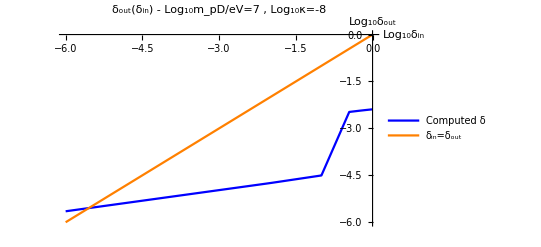

InterpolatingFunction::dmval: Input value {-5.47487} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.54599} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.54726} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{δ→2.83619×10^-6}

-5.54726

```mathematica
("δtable"/.computedδscanDisk10m4[[1]])[[;;,;;2]]//N//Round;
Position[%,{7,-8}]
Quiet@Table[{Log10@"δ","δtable"[[%[[1,1]],3]]}/.computedδscanDisk10m4[[i]],{i,Length[computedδscanDisk10m4]}]//N
(*ListPlot[10^%,PlotRange->{0,1}]*)
Interpolation[%,InterpolationOrder->1];
(*Plot[10^%[Log10@δ],{δ,0,1},PlotRange->{{-0.1,1.1},{-0.1,1.1}}]*)
(*Out[-4][[Out[-3][[1,1]]]]*)
Plot[{%[δ],δ},{δ,-6,0},PlotRange->All,AxesLabel->{"Log_10δ_in","Log_10δ_out"},(*PlotLabel->StringForm["δ_out(δ_in) - m_eD/m_pD=`` , κ=``",#[[1]],#[[2]]]&[Out[-4][[Out[-3][[1,1]]]]]*)PlotLabel->StringForm["δ_out(δ_in) - Log_10m_pD/eV=`` , Log_10κ=``",Out[-4][[Out[-3][[1,1]]]][[1]],Out[-4][[Out[-3][[1,1]]]][[2]]],PlotStyle->{Blue,Orange},PlotLegends->LineLegend[{Blue,Orange},{"Computed δ","δ_in=δ_out"}]]
FindRoot[10^%%[Log10@δ]-δ,{δ,0.01}]
Log10@δ/.%
```

```mathematica
(*("δtable"/.computedδscanDisk10m4[[1]])[[;;,;;2]]//N//Round;
Position[%,{13,-8}]
Quiet@Table[{Log10@"δ","δtable"[[%[[1,1]],3]]}/.computedδscanDisk10m4[[i]],{i,Length[computedδscanDisk10m4]}]//N
(*ListPlot[10^%,PlotRange->{0,1}]*)
Interpolation[%,InterpolationOrder->1];
(*Plot[10^%[Log10@δ],{δ,0,1},PlotRange->{{-0.1,1.1},{-0.1,1.1}}]*)
Plot[{%[δ],δ},{δ,-5,0},PlotRange->All]
FindRoot[10^%%[Log10@δ]-δ,{δ,0.1}]
Log10@δ/.%*)

(*GetδTruth[δScan_]:=Module[{δtruthtable,δoutofδintable,δoutofδin,δtruth},

δtruthtable ={};

Do[
(*Print@Union[δScan[[;;]]["δtable"][[i,;;2]]//N//Round];*)
δoutofδintable =Table[Log10@"δ"/.δScan[[j]],δScan[[j]]["δtable"][[i,3]],{j,Length[δScan]}];
δoutofδin = Interpolation[δoutofδintable,InterpolationOrder->1];
δtruth = δ/.FindRoot[10^δoutofδin[Log10@δ]-δ,{δ,0.1}];
AppendTo[δtruthtable,{δScan[[1]]["δtable"][[i,1]],δScan[[1]]["δtable"][[i,3]],δtruth}];
,{i,Length[δScan[[1]]["δtable"]]}];(*assuming all δtables have the same ordering size*)

δtruthtable
]*)
```

FindRoot::nlnum: The function value {0.0560129+10^(«1»)} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.0560129}.

InterpolatingFunction::dmval: Input value {-5.24231} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::nlnum: The function value {0.00319528+10^(InterpolatingFunction[{{-5.,0.}},«3»,{Automatic}][-2.49549+1.36438 ⅈ])} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.00319528}.

InterpolatingFunction::dmval: Input value {-6.51508} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-6.12211} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.0000593359+10^(«1»[-4.22668+1.36438 ⅈ])} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.0000593359}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

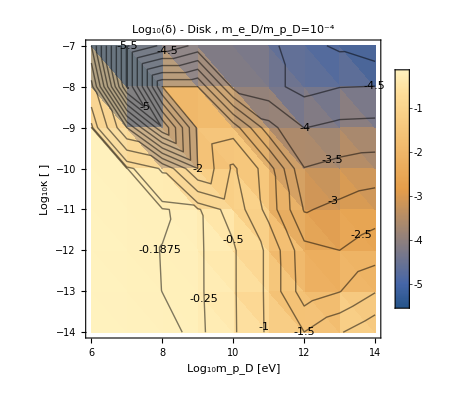

```mathematica
δtruthdisk = GetδTruth[computedδscanDisk10m4];
(*ListContourPlot[δtruth,ContourLabels->All]*)
Show[{ListDensityPlot[δtruthdisk,PlotLegends->Automatic,PlotLabel->"Log_10(δ) - Disk , m_e_D/m_p_D=10^-4",FrameLabel->{"Log_10m_p_D [eV]","Log_10κ [ ]"}],ListContourPlot[δtruthdisk,ContourLabels->All,ContourShading->False,Contours->Join[Table[i,{i,-0.25,0,0.0625}],Table[i,{i,-9,-0.5,0.5}]]],
ListContourPlot[δtruthdisk,Contours->{0},ContourStyle->Directive[Red,Thick],ContourLabels->True,ContourShading->None]}]
(*ListContourPlot[Table[δtruth,ContourLabels->All]*)
```

```mathematica
FeσDicte=ReadIt[NotebookDirectory[]<>"../capture/FeσDicte"];
SiO2σDicte=ReadIt[NotebookDirectory[]<>"../capture/SiO2σDicte"];
MgOσDicte=ReadIt[NotebookDirectory[]<>"../capture/MgOσDicte"];
ElectronicσDicts=Gather[Flatten@Join[FeσDicte,SiO2σDicte,MgOσDicte],#1["mχ"]==#2["mχ"]&];
```

```mathematica
FeσDictNuc=ReadIt[NotebookDirectory[]<>"../capture/FeσDictNuc"];
SiσDictNuc=ReadIt[NotebookDirectory[]<>"../capture/SiσDictNuc"];
MgσDictNuc=ReadIt[NotebookDirectory[]<>"../capture/MgσDictNuc"];
OσDictNuc=ReadIt[NotebookDirectory[]<>"../capture/OσDictNuc"];
NuclearσDicts=Gather[Flatten@Join[{FeσDictNuc},{SiσDictNuc},{MgσDictNuc},{OσDictNuc}],#1["mχ"]==#2["mχ"]&];
```

{{{6,-14,-13.5491},{6,-13,-11.5491},{6,-12,-9.54907},{6,-11,-7.54907},{6,-10,-5.54907},{6,-9,-3.54907},{6,-8,-1.54907},{6,-7,0.450927}},{{7,-14,-10.558},{7,-13,-8.55796},{7,-12,-6.55796},{7,-11,-4.55796},{7,-10,-2.55796},{7,-9,-0.557963},{7,-8,1.44204},{7,-7,3.44204}},{{8,-14,-8.09656},{8,-13,-6.09656},{8,-12,-4.09656},{8,-11,-2.09656},{8,-10,-0.0965645},{8,-9,1.90344},{8,-8,3.90344},{8,-7,5.90344}},{{9,-14,-7.60598},{9,-13,-5.60598},{9,-12,-3.60598},{9,-11,-1.60598},{9,-10,0.394023},{9,-9,2.39402},{9,-8,4.39402},{9,-7,6.39402}},{{10,-14,-8.15952},{10,-13,-6.15952},{10,-12,-4.15952},{10,-11,-2.15952},{10,-10,-0.159518},{10,-9,1.84048},{10,-8,3.84048},{10,-7,5.84048}},{{11,-14,-9.00686},{11,-13,-7.00686},{11,-12,-5.00686},{11,-11,-3.00686},{11,-10,-1.00686},{11,-9,0.993135},{11,-8,2.99314},{11,-7,4.99314}},{{12,-14,-9.97474},{12,-13,-7.97474},{12,-12,-5.97474},{12,-11,-3.97474},{12,-10,-1.97474},{12,-9,0.0252611},{12,-8,2.02526},{12,-7,4.02526}},{{13,-14,-10.9706},{13,-13,-8.97055},{13,-12,-6.97055},{13,-11,-4.97055},{13,-10,-2.97055},{13,-9,-0.970551},{13,-8,1.02945},{13,-7,3.02945}},{{14,-14,-11.9702},{14,-13,-9.9702},{14,-12,-7.9702},{14,-11,-5.9702},{14,-10,-3.9702},{14,-9,-1.9702},{14,-8,0.0298009},{14,-7,2.0298}},{{15,-14,-12.9702},{15,-13,-10.9702},{15,-12,-8.97016},{15,-11,-6.97016},{15,-10,-4.97016},{15,-9,-2.97016},{15,-8,-0.970164},{15,-7,1.02984}}}

Red contour is lower boundary of the thermalized regime (we expect > O(1) energy lost in the Earth for 1% of the incoming dark proton distribution)

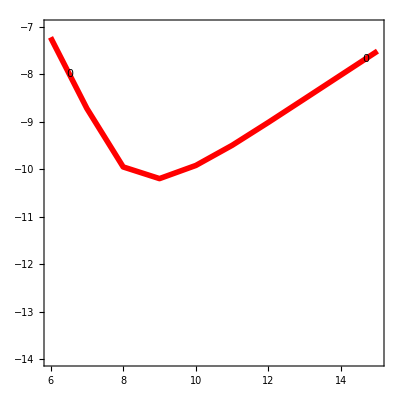

```mathematica
Eatvcutdisk=Table[
eind = FirstPosition["mχ"/.ElectronicσDicts,10^# ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]&@mind;
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^# ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]&@mind;

mχt=10^mind ("JpereV")/("c")^2/.Constants`SIConstRepl;
βDdict=Capture`v0toβD[20 10^3,#,10^-4#]&[mχt];
(*βDdict={"βD"->6/((1+10^-4)mχt (20 10^3)^2)};*)
vχcut = Capture`GetvχMax[1-10^-2,(*"βcore"/.EarthRepl*)"βD"/.βDdict,mχt,0 "vesc"/.EarthRepl];
(*Print[vχcut];*)

Eofv[vχ_?NumberQ]:=("rE"/.Constants`EarthRepl)("dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]]])[10^6,vχ]/((10^mind ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2(*-3/("βcore")*)/.EarthRepl);
{mind,mlogκ,Log10[10^(2 mlogκ) Eofv[vχcut(*+"vesc"*)] /.EarthRepl]},{mind,6,15},{mlogκ,-14,-7}]
"Red contour is lower boundary of the thermalized regime (we expect > O(1) energy lost in the Earth for 1% of the incoming dark proton distribution)"
Show[{(*ListContourPlot[Flatten[Eatvcutdisk,1],ContourLabels->True,PlotLabel->"(<E>)/E_K 1st v percentile - Core Disk",FrameLabel->{"Log_10m_p_D [eV]","Log_10κ [ ]"}],*)ListContourPlot[Flatten[Eatvcutdisk,1],ContourLabels->True,Contours->{0},ContourStyle->Directive[Red,Thickness[0.01],Opacity[1]],ContourShading->False]}]
```

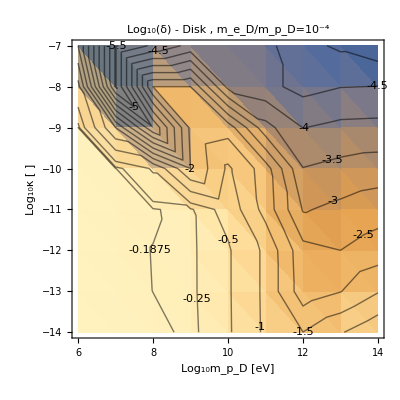
```mathematica
P1 = -Graphics-;

P2 = -Graphics-;
Show[{P1,P2}]
```

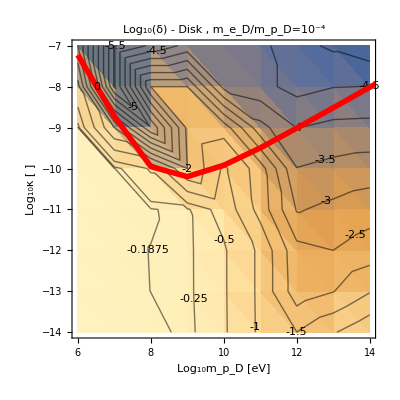

HALO

```mathematica
{"v0","meD"/"mpD"}/.ReadIt[δScanList[[1]]["file"]][[;;9,3,;;]]
```

{{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}}}

```mathematica
computedδscanhalo10m4=ComputeδonScan[δScanList,2]
SaveIt[NotebookDirectory[]<>"δscanhalo10m4",computedδscanhalo10m4]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {Private`rmax} = {3.1855×10^13}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {1.} is at the edge of the search region {1.×10^-10,1.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Private`r near {Private`r} = {2.88681×10^16}. NIntegrate obtained 1.25634×10^44 and 1.15359×10^39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Private`r near {Private`r} = {2.88681×10^16}. NIntegrate obtained 1.25634×10^44 and 1.15359×10^39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Private`r near {Private`r} = {2.88681×10^16}. NIntegrate obtained 1.25634×10^44 and 1.15359×10^39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

{<|δ→1/100000,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\08_05_2025_0p99999\PDictList\PDictList_ϕE_100_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.124896},{7.,-Log[100000000000000]/Log[10],-0.125164},{8.,-Log[100000000000000]/Log[10],-0.126853},{9.,-Log[100000000000000]/Log[10],-0.124911},{10.,-Log[100000000000000]/Log[10],-0.124925},{11.,-Log[100000000000000]/Log[10],-0.124915},{12.,-Log[100000000000000]/Log[10],-0.124307},{13.,-Log[100000000000000]/Log[10],-0.0679524},{14.,-Log[100000000000000]/Log[10],0.},{6.,-Log[10000000000000]/Log[10],-0.124895},{7.,-Log[10000000000000]/Log[10],-0.126592},{8.,-Log[10000000000000]/Log[10],-0.126853},{9.,-Log[10000000000000]/Log[10],-0.124916},{10.,-Log[10000000000000]/Log[10],-0.124931},{11.,-Log[10000000000000]/Log[10],-0.124931},{12.,-Log[10000000000000]/Log[10],-0.124319},{13.,-Log[10000000000000]/Log[10],-0.0679615},{14.,-Log[10000000000000]/Log[10],0.},{6.,-Log[1000000000000]/Log[10],-0.124895},{7.,-Log[1000000000000]/Log[10],-0.126828},{8.,-Log[1000000000000]/Log[10],-0.127431},{9.,-Log[1000000000000]/Log[10],-0.124917},{10.,-Log[1000000000000]/Log[10],-0.12568},{11.,-Log[1000000000000]/Log[10],-0.12532},{12.,-Log[1000000000000]/Log[10],-0.124624},{13.,-Log[1000000000000]/Log[10],-0.0681772},{14.,-Log[1000000000000]/Log[10],0.},{6.,-Log[100000000000]/Log[10],-0.124895},{7.,-Log[100000000000]/Log[10],-0.127375},{8.,-Log[100000000000]/Log[10],-0.12728},{9.,-Log[100000000000]/Log[10],-1.5819},{10.,-Log[100000000000]/Log[10],-0.135182},{11.,-Log[100000000000]/Log[10],-0.130224},{12.,-Log[100000000000]/Log[10],-0.712651},{13.,-Log[100000000000]/Log[10],-0.617292},{14.,-Log[100000000000]/Log[10],0.},{6.,-Log[10000000000]/Log[10],-0.124895},{7.,-Log[10000000000]/Log[10],-0.127238},{8.,-Log[10000000000]/Log[10],-3.07723},{9.,-Log[10000000000]/Log[10],-2.95563},{10.,-Log[10000000000]/Log[10],-2.35681},{11.,-Log[10000000000]/Log[10],-1.9487},{12.,-Log[10000000000]/Log[10],-1.82834},{13.,-Log[10000000000]/Log[10],-1.79363},{14.,-Log[10000000000]/Log[10],-1.99744},{6.,-Log[1000000000]/Log[10],-0.124895},{7.,-Log[1000000000]/Log[10],-0.139951},{8.,-Log[1000000000]/Log[10],-4.6425},{9.,-Log[1000000000]/Log[10],-4.14302},{10.,-Log[1000000000]/Log[10],-3.40893},{11.,-Log[1000000000]/Log[10],-2.98989},{12.,-Log[1000000000]/Log[10],-2.86312},{13.,-Log[1000000000]/Log[10],-2.87138},{14.,-Log[1000000000]/Log[10],-3.14268},{6.,-Log[100000000]/Log[10],-0.137764},{7.,-Log[100000000]/Log[10],-6.77845},{8.,-Log[100000000]/Log[10],-6.22856},{9.,-Log[100000000]/Log[10],-5.30736},{10.,-Log[100000000]/Log[10],-4.46896},{11.,-Log[100000000]/Log[10],-4.01158},{12.,-Log[100000000]/Log[10],-3.86836},{13.,-Log[100000000]/Log[10],-3.86976},{14.,-Log[100000000]/Log[10],-4.18036},{6.,-Log[10000000]/Log[10],-7.43982},{7.,-Log[10000000]/Log[10],-6.9403},{8.,-Log[10000000]/Log[10],-6.44509},{9.,-Log[10000000]/Log[10],-5.98729},{10.,-Log[10000000]/Log[10],-5.56405},{11.,-Log[10000000]/Log[10],-5.13091},{12.,-Log[10000000]/Log[10],-4.92921},{13.,-Log[10000000]/Log[10],-4.8919},{14.,-Log[10000000]/Log[10],-5.18615}},v0→220000,meDbympD→0.0001|>,<|δ→1,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\21_04_2025_0p0\PDictList\PDictList_ϕE_0_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.128263},{7.,-Log[100000000000000]/Log[10],-0.188851},{8.,-Log[100000000000000]/Log[10],-0.199933},{9.,-Log[100000000000000]/Log[10],-0.246396},{10.,-Log[100000000000000]/Log[10],-2.1604},{11.,-Log[100000000000000]/Log[10],-2.18818},{12.,-Log[100000000000000]/Log[10],-1.68989},{13.,-Log[100000000000000]/Log[10],-1.19056},{14.,-Log[100000000000000]/Log[10],0.},{6.,-Log[10000000000000]/Log[10],-0.128263},{7.,-Log[10000000000000]/Log[10],-0.188851},{8.,-Log[10000000000000]/Log[10],-0.199938},{9.,-Log[10000000000000]/Log[10],-0.295185},{10.,-Log[10000000000000]/Log[10],-2.18562},{11.,-Log[10000000000000]/Log[10],-3.27193},{12.,-Log[10000000000000]/Log[10],-2.68644},{13.,-Log[10000000000000]/Log[10],-2.18427},{14.,-Log[10000000000000]/Log[10],-1.65754},{6.,-Log[1000000000000]/Log[10],-0.128263},{7.,-Log[1000000000000]/Log[10],-0.188872},{8.,-Log[1000000000000]/Log[10],-0.22942},{9.,-Log[1000000000000]/Log[10],-0.298707},{10.,-Log[1000000000000]/Log[10],-2.29709},{11.,-Log[1000000000000]/Log[10],-4.33351},{12.,-Log[1000000000000]/Log[10],-3.83016},{13.,-Log[1000000000000]/Log[10],-3.28974},{14.,-Log[1000000000000]/Log[10],-2.66899},{6.,-Log[100000000000]/Log[10],-0.128264},{7.,-Log[100000000000]/Log[10],-0.212819},{8.,-Log[100000000000]/Log[10],-0.215718},{9.,-Log[100000000000]/Log[10],-0.285083},{10.,-Log[100000000000]/Log[10],-2.42791},{11.,-Log[100000000000]/Log[10],-5.31321},{12.,-Log[100000000000]/Log[10],-4.8141},{13.,-Log[100000000000]/Log[10],-4.31386},{14.,-Log[100000000000]/Log[10],-3.81144},{6.,-Log[10000000000]/Log[10],-0.129368},{7.,-Log[10000000000]/Log[10],-0.2189},{8.,-Log[10000000000]/Log[10],-0.610957},{9.,-Log[10000000000]/Log[10],-0.888082},{10.,-Log[10000000000]/Log[10],-6.67533},{11.,-Log[10000000000]/Log[10],-6.24354},{12.,-Log[10000000000]/Log[10],-5.75023},{13.,-Log[10000000000]/Log[10],-5.24977},{14.,-Log[10000000000]/Log[10],-4.75004},{6.,-Log[1000000000]/Log[10],-0.217833},{7.,-Log[1000000000]/Log[10],-0.809773},{8.,-Log[1000000000]/Log[10],-1.84388},{9.,-Log[1000000000]/Log[10],-1.88976},{10.,-Log[1000000000]/Log[10],-7.53155},{11.,-Log[1000000000]/Log[10],-7.1583},{12.,-Log[1000000000]/Log[10],-6.64593},{13.,-Log[1000000000]/Log[10],-6.15333},{14.,-Log[1000000000]/Log[10],-5.64766},{6.,-Log[100000000]/Log[10],-0.789712},{7.,-Log[100000000]/Log[10],-3.69672},{8.,-Log[100000000]/Log[10],-3.22101},{9.,-Log[100000000]/Log[10],-3.08517},{10.,-Log[100000000]/Log[10],-8.67919},{11.,-Log[100000000]/Log[10],-8.16625},{12.,-Log[100000000]/Log[10],-7.63327},{13.,-Log[100000000]/Log[10],-7.12786},{14.,-Log[100000000]/Log[10],-6.62799},{6.,-Log[10000000]/Log[10],-5.03811},{7.,-Log[10000000]/Log[10],-5.76943},{8.,-Log[10000000]/Log[10],-3.46803},{9.,-Log[10000000]/Log[10],-5.68041},{10.,-Log[10000000]/Log[10],-9.67649},{11.,-Log[10000000]/Log[10],-9.20717},{12.,-Log[10000000]/Log[10],-8.68043},{13.,-Log[10000000]/Log[10],-8.16715},{14.,-Log[10000000]/Log[10],-7.63382}},v0→220000,meDbympD→0.0001|>,<|δ→1/10,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\10_05_2025_0p9\PDictList\PDictList_ϕE_90_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.125209},{7.,-Log[100000000000000]/Log[10],-0.132735},{8.,-Log[100000000000000]/Log[10],-0.141244},{9.,-Log[100000000000000]/Log[10],-0.142536},{10.,-Log[100000000000000]/Log[10],-0.153138},{11.,-Log[100000000000000]/Log[10],-1.21802},{12.,-Log[100000000000000]/Log[10],-1.66869},{13.,-Log[100000000000000]/Log[10],-1.17238},{14.,-Log[100000000000000]/Log[10],0.},{6.,-Log[10000000000000]/Log[10],-0.125209},{7.,-Log[10000000000000]/Log[10],-0.132735},{8.,-Log[10000000000000]/Log[10],-0.141246},{9.,-Log[10000000000000]/Log[10],-0.147159},{10.,-Log[10000000000000]/Log[10],-0.160116},{11.,-Log[10000000000000]/Log[10],-1.33819},{12.,-Log[10000000000000]/Log[10],-2.76301},{13.,-Log[10000000000000]/Log[10],-2.17843},{14.,-Log[10000000000000]/Log[10],-1.64568},{6.,-Log[1000000000000]/Log[10],-0.125209},{7.,-Log[1000000000000]/Log[10],-0.132736},{8.,-Log[1000000000000]/Log[10],-0.146013},{9.,-Log[1000000000000]/Log[10],-0.147004},{10.,-Log[1000000000000]/Log[10],-0.160087},{11.,-Log[1000000000000]/Log[10],-1.3397},{12.,-Log[1000000000000]/Log[10],-3.79763},{13.,-Log[1000000000000]/Log[10],-3.29676},{14.,-Log[1000000000000]/Log[10],-2.78417},{6.,-Log[100000000000]/Log[10],-0.125209},{7.,-Log[100000000000]/Log[10],-0.135193},{8.,-Log[100000000000]/Log[10],-0.143938},{9.,-Log[100000000000]/Log[10],-0.161252},{10.,-Log[100000000000]/Log[10],-0.202309},{11.,-Log[100000000000]/Log[10],-5.22519},{12.,-Log[100000000000]/Log[10],-4.73326},{13.,-Log[100000000000]/Log[10],-4.23314},{14.,-Log[100000000000]/Log[10],-3.7331},{6.,-Log[10000000000]/Log[10],-0.125313},{7.,-Log[10000000000]/Log[10],-0.144207},{8.,-Log[10000000000]/Log[10],-0.4333},{9.,-Log[10000000000]/Log[10],-0.439701},{10.,-Log[10000000000]/Log[10],-0.575652},{11.,-Log[10000000000]/Log[10],-6.09137},{12.,-Log[10000000000]/Log[10],-5.59864},{13.,-Log[10000000000]/Log[10],-5.11199},{14.,-Log[10000000000]/Log[10],-4.6182},{6.,-Log[1000000000]/Log[10],-0.146827},{7.,-Log[1000000000]/Log[10],-0.26439},{8.,-Log[1000000000]/Log[10],-1.85896},{9.,-Log[1000000000]/Log[10],-1.55171},{10.,-Log[1000000000]/Log[10],-1.6346},{11.,-Log[1000000000]/Log[10],-7.09694},{12.,-Log[1000000000]/Log[10],-6.53834},{13.,-Log[1000000000]/Log[10],-6.06571},{14.,-Log[1000000000]/Log[10],-5.58171},{6.,-Log[100000000]/Log[10],-0.622662},{7.,-Log[100000000]/Log[10],-5.8529},{8.,-Log[100000000]/Log[10],-3.41821},{9.,-Log[100000000]/Log[10],-2.71901},{10.,-Log[100000000]/Log[10],-4.60886},{11.,-Log[100000000]/Log[10],-8.09071},{12.,-Log[100000000]/Log[10],-7.61629},{13.,-Log[100000000]/Log[10],-7.09781},{14.,-Log[100000000]/Log[10],-6.58232},{6.,-Log[10000000]/Log[10],-4.25716},{7.,-Log[10000000]/Log[10],-6.01129},{8.,-Log[10000000]/Log[10],-5.54203},{9.,-Log[10000000]/Log[10],-5.35056},{10.,-Log[10000000]/Log[10],-5.67504},{11.,-Log[10000000]/Log[10],-9.16955},{12.,-Log[10000000]/Log[10],-8.61045},{13.,-Log[10000000]/Log[10],-8.09174},{14.,-Log[10000000]/Log[10],-7.61724}},v0→220000,meDbympD→0.0001|>,<|δ→9/10,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\11_05_2025_0p1\PDictList\PDictList_ϕE_10_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.127682},{7.,-Log[100000000000000]/Log[10],-0.178433},{8.,-Log[100000000000000]/Log[10],-0.194329},{9.,-Log[100000000000000]/Log[10],-0.237969},{10.,-Log[100000000000000]/Log[10],-1.91247},{11.,-Log[100000000000000]/Log[10],-2.22142},{12.,-Log[100000000000000]/Log[10],-1.72391},{13.,-Log[100000000000000]/Log[10],-1.22712},{14.,-Log[100000000000000]/Log[10],0.},{6.,-Log[10000000000000]/Log[10],-0.127682},{7.,-Log[10000000000000]/Log[10],-0.178433},{8.,-Log[10000000000000]/Log[10],-0.194333},{9.,-Log[10000000000000]/Log[10],-0.272148},{10.,-Log[10000000000000]/Log[10],-1.99433},{11.,-Log[10000000000000]/Log[10],-3.30572},{12.,-Log[10000000000000]/Log[10],-2.72057},{13.,-Log[10000000000000]/Log[10],-2.22123},{14.,-Log[10000000000000]/Log[10],-1.70038},{6.,-Log[1000000000000]/Log[10],-0.127682},{7.,-Log[1000000000000]/Log[10],-0.178438},{8.,-Log[1000000000000]/Log[10],-0.218545},{9.,-Log[1000000000000]/Log[10],-0.274996},{10.,-Log[1000000000000]/Log[10],-2.0376},{11.,-Log[1000000000000]/Log[10],-4.35647},{12.,-Log[1000000000000]/Log[10],-3.8621},{13.,-Log[1000000000000]/Log[10],-3.33543},{14.,-Log[1000000000000]/Log[10],-2.71194},{6.,-Log[100000000000]/Log[10],-0.127683},{7.,-Log[100000000000]/Log[10],-0.195349},{8.,-Log[100000000000]/Log[10],-0.20563},{9.,-Log[100000000000]/Log[10],-0.264484},{10.,-Log[100000000000]/Log[10],-2.22419},{11.,-Log[100000000000]/Log[10],-5.33082},{12.,-Log[100000000000]/Log[10],-4.84143},{13.,-Log[100000000000]/Log[10],-4.34109},{14.,-Log[100000000000]/Log[10],-3.83869},{6.,-Log[10000000000]/Log[10],-0.128529},{7.,-Log[10000000000]/Log[10],-0.20511},{8.,-Log[10000000000]/Log[10],-0.566082},{9.,-Log[10000000000]/Log[10],-0.816918},{10.,-Log[10000000000]/Log[10],-6.65887},{11.,-Log[10000000000]/Log[10],-6.25249},{12.,-Log[10000000000]/Log[10],-5.76451},{13.,-Log[10000000000]/Log[10],-5.27149},{14.,-Log[10000000000]/Log[10],-4.77142},{6.,-Log[1000000000]/Log[10],-0.204471},{7.,-Log[1000000000]/Log[10],-0.746632},{8.,-Log[1000000000]/Log[10],-1.83709},{9.,-Log[1000000000]/Log[10],-1.83517},{10.,-Log[1000000000]/Log[10],-7.56838},{11.,-Log[1000000000]/Log[10],-7.12728},{12.,-Log[1000000000]/Log[10],-6.65128},{13.,-Log[1000000000]/Log[10],-6.16981},{14.,-Log[1000000000]/Log[10],-5.67668},{6.,-Log[100000000]/Log[10],-0.700215},{7.,-Log[100000000]/Log[10],-3.70659},{8.,-Log[100000000]/Log[10],-3.22147},{9.,-Log[100000000]/Log[10],-3.03774},{10.,-Log[100000000]/Log[10],-8.65828},{11.,-Log[100000000]/Log[10],-8.15783},{12.,-Log[100000000]/Log[10],-7.61907},{13.,-Log[100000000]/Log[10],-7.10437},{14.,-Log[100000000]/Log[10],-6.64159},{6.,-Log[10000000]/Log[10],-5.01471},{7.,-Log[10000000]/Log[10],-5.77993},{8.,-Log[10000000]/Log[10],-3.60583},{9.,-Log[10000000]/Log[10],-5.63623},{10.,-Log[10000000]/Log[10],-9.65973},{11.,-Log[10000000]/Log[10],-9.2044},{12.,-Log[10000000]/Log[10],-8.67536},{13.,-Log[10000000]/Log[10],-8.15879},{14.,-Log[10000000]/Log[10],-7.61962}},v0→220000,meDbympD→0.0001|>,<|δ→1/100,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\11_05_2025_0p99\PDictList\PDictList_ϕE_99_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.124941},{7.,-Log[100000000000000]/Log[10],-0.128242},{8.,-Log[100000000000000]/Log[10],-0.128279},{9.,-Log[100000000000000]/Log[10],-0.128498},{10.,-Log[100000000000000]/Log[10],-0.12979},{11.,-Log[100000000000000]/Log[10],-0.130621},{12.,-Log[100000000000000]/Log[10],-1.58474},{13.,-Log[100000000000000]/Log[10],-1.08477},{14.,-Log[100000000000000]/Log[10],0.},{6.,-Log[10000000000000]/Log[10],-0.124941},{7.,-Log[10000000000000]/Log[10],-0.128242},{8.,-Log[10000000000000]/Log[10],-0.128279},{9.,-Log[10000000000000]/Log[10],-0.129595},{10.,-Log[10000000000000]/Log[10],-0.129867},{11.,-Log[10000000000000]/Log[10],-0.132143},{12.,-Log[10000000000000]/Log[10],-2.70738},{13.,-Log[10000000000000]/Log[10],-2.08039},{14.,-Log[10000000000000]/Log[10],-1.6118},{6.,-Log[1000000000000]/Log[10],-0.124941},{7.,-Log[1000000000000]/Log[10],-0.128242},{8.,-Log[1000000000000]/Log[10],-0.12932},{9.,-Log[1000000000000]/Log[10],-0.129123},{10.,-Log[1000000000000]/Log[10],-0.129578},{11.,-Log[1000000000000]/Log[10],-0.132107},{12.,-Log[1000000000000]/Log[10],-2.81062},{13.,-Log[1000000000000]/Log[10],-3.16936},{14.,-Log[1000000000000]/Log[10],-2.66923},{6.,-Log[100000000000]/Log[10],-0.124941},{7.,-Log[100000000000]/Log[10],-0.129281},{8.,-Log[100000000000]/Log[10],-0.128969},{9.,-Log[100000000000]/Log[10],-0.144758},{10.,-Log[100000000000]/Log[10],-0.145402},{11.,-Log[100000000000]/Log[10],-0.157487},{12.,-Log[100000000000]/Log[10],-4.53789},{13.,-Log[100000000000]/Log[10],-4.0242},{14.,-Log[100000000000]/Log[10],-3.52419},{6.,-Log[10000000000]/Log[10],-0.124955},{7.,-Log[10000000000]/Log[10],-0.128885},{8.,-Log[10000000000]/Log[10],-0.497713},{9.,-Log[10000000000]/Log[10],-0.386301},{10.,-Log[10000000000]/Log[10],-0.307246},{11.,-Log[10000000000]/Log[10],-0.37033},{12.,-Log[10000000000]/Log[10],-5.46394},{13.,-Log[10000000000]/Log[10],-5.01794},{14.,-Log[10000000000]/Log[10],-4.52392},{6.,-Log[1000000000]/Log[10],-0.140276},{7.,-Log[1000000000]/Log[10],-1.17664},{8.,-Log[1000000000]/Log[10],-2.02954},{9.,-Log[1000000000]/Log[10],-1.53924},{10.,-Log[1000000000]/Log[10],-1.14302},{11.,-Log[1000000000]/Log[10],-3.34279},{12.,-Log[1000000000]/Log[10],-6.56574},{13.,-Log[1000000000]/Log[10],-5.99675},{14.,-Log[1000000000]/Log[10],-5.46372},{6.,-Log[100000000]/Log[10],-0.139788},{7.,-Log[100000000]/Log[10],-6.09991},{8.,-Log[100000000]/Log[10],-5.5545},{9.,-Log[100000000]/Log[10],-4.76042},{10.,-Log[100000000]/Log[10],-4.22808},{11.,-Log[100000000]/Log[10],-4.32631},{12.,-Log[100000000]/Log[10],-7.54783},{13.,-Log[100000000]/Log[10],-7.06766},{14.,-Log[100000000]/Log[10],-6.56758},{6.,-Log[10000000]/Log[10],-3.5191},{7.,-Log[10000000]/Log[10],-6.26068},{8.,-Log[10000000]/Log[10],-5.76921},{9.,-Log[10000000]/Log[10],-5.43473},{10.,-Log[10000000]/Log[10],-5.31406},{11.,-Log[10000000]/Log[10],-5.43279},{12.,-Log[10000000]/Log[10],-8.58711},{13.,-Log[10000000]/Log[10],-8.05164},{14.,-Log[10000000]/Log[10],-7.54884}},v0→220000,meDbympD→0.0001|>,<|δ→0.65,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\15_05_2025_0p35\PDictList\PDictList_ϕE_35_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.126924},{7.,-Log[100000000000000]/Log[10],-0.164726},{8.,-Log[100000000000000]/Log[10],-0.180808},{9.,-Log[100000000000000]/Log[10],-0.20308},{10.,-Log[100000000000000]/Log[10],-1.19106},{11.,-Log[100000000000000]/Log[10],-2.21494},{12.,-Log[100000000000000]/Log[10],-1.71857},{13.,-Log[100000000000000]/Log[10],-1.22163},{14.,-Log[100000000000000]/Log[10],0.},{6.,-Log[10000000000000]/Log[10],-0.126924},{7.,-Log[10000000000000]/Log[10],-0.164726},{8.,-Log[10000000000000]/Log[10],-0.180819},{9.,-Log[10000000000000]/Log[10],-0.226138},{10.,-Log[10000000000000]/Log[10],-1.23151},{11.,-Log[10000000000000]/Log[10],-3.29014},{12.,-Log[10000000000000]/Log[10],-2.71499},{13.,-Log[10000000000000]/Log[10],-2.2157},{14.,-Log[10000000000000]/Log[10],-1.69495},{6.,-Log[1000000000000]/Log[10],-0.126924},{7.,-Log[1000000000000]/Log[10],-0.164755},{8.,-Log[1000000000000]/Log[10],-0.19911},{9.,-Log[1000000000000]/Log[10],-0.227744},{10.,-Log[1000000000000]/Log[10],-1.31874},{11.,-Log[1000000000000]/Log[10],-4.32929},{12.,-Log[1000000000000]/Log[10],-3.84746},{13.,-Log[1000000000000]/Log[10],-3.33067},{14.,-Log[1000000000000]/Log[10],-2.7124},{6.,-Log[100000000000]/Log[10],-0.126926},{7.,-Log[100000000000]/Log[10],-0.176886},{8.,-Log[100000000000]/Log[10],-0.186862},{9.,-Log[100000000000]/Log[10],-0.234384},{10.,-Log[100000000000]/Log[10],-4.5735},{11.,-Log[100000000000]/Log[10],-5.30409},{12.,-Log[100000000000]/Log[10],-4.82147},{13.,-Log[100000000000]/Log[10],-4.32158},{14.,-Log[100000000000]/Log[10],-3.82004},{6.,-Log[10000000000]/Log[10],-0.127497},{7.,-Log[10000000000]/Log[10],-0.188804},{8.,-Log[10000000000]/Log[10],-0.520976},{9.,-Log[10000000000]/Log[10],-0.663548},{10.,-Log[10000000000]/Log[10],-5.40503},{11.,-Log[10000000000]/Log[10],-6.22565},{12.,-Log[10000000000]/Log[10],-5.73934},{13.,-Log[10000000000]/Log[10],-5.2436},{14.,-Log[10000000000]/Log[10],-4.74359},{6.,-Log[1000000000]/Log[10],-0.188457},{7.,-Log[1000000000]/Log[10],-0.62282},{8.,-Log[1000000000]/Log[10],-1.81616},{9.,-Log[1000000000]/Log[10],-1.75497},{10.,-Log[1000000000]/Log[10],-6.32959},{11.,-Log[1000000000]/Log[10],-7.08093},{12.,-Log[1000000000]/Log[10],-6.6206},{13.,-Log[1000000000]/Log[10],-6.12844},{14.,-Log[1000000000]/Log[10],-5.64569},{6.,-Log[100000000]/Log[10],-0.59306},{7.,-Log[100000000]/Log[10],-3.73699},{8.,-Log[100000000]/Log[10],-3.22092},{9.,-Log[100000000]/Log[10],-2.96473},{10.,-Log[100000000]/Log[10],-7.41035},{11.,-Log[100000000]/Log[10],-8.13415},{12.,-Log[100000000]/Log[10],-7.62648},{13.,-Log[100000000]/Log[10],-7.06702},{14.,-Log[100000000]/Log[10],-6.61245},{6.,-Log[10000000]/Log[10],-4.87764},{7.,-Log[10000000]/Log[10],-5.81223},{8.,-Log[10000000]/Log[10],-3.59738},{9.,-Log[10000000]/Log[10],-5.52852},{10.,-Log[10000000]/Log[10],-8.42356},{11.,-Log[10000000]/Log[10],-9.19672},{12.,-Log[10000000]/Log[10],-8.66116},{13.,-Log[10000000]/Log[10],-8.13515},{14.,-Log[10000000]/Log[10],-7.62709}},v0→220000,meDbympD→0.0001|>,<|δ→0.35,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\15_05_2025_0p65\PDictList\PDictList_ϕE_65_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.125955},{7.,-Log[100000000000000]/Log[10],-0.145882},{8.,-Log[100000000000000]/Log[10],-0.161306},{9.,-Log[100000000000000]/Log[10],-0.169008},{10.,-Log[100000000000000]/Log[10],-0.382763},{11.,-Log[100000000000000]/Log[10],-2.19907},{12.,-Log[100000000000000]/Log[10],-1.70285},{13.,-Log[100000000000000]/Log[10],-1.20551},{14.,-Log[100000000000000]/Log[10],0.},{6.,-Log[10000000000000]/Log[10],-0.125955},{7.,-Log[10000000000000]/Log[10],-0.145882},{8.,-Log[10000000000000]/Log[10],-0.165129},{9.,-Log[10000000000000]/Log[10],-0.181718},{10.,-Log[10000000000000]/Log[10],-0.455577},{11.,-Log[10000000000000]/Log[10],-3.3057},{12.,-Log[10000000000000]/Log[10],-2.73086},{13.,-Log[10000000000000]/Log[10],-2.19935},{14.,-Log[10000000000000]/Log[10],-1.67868},{6.,-Log[1000000000000]/Log[10],-0.125955},{7.,-Log[1000000000000]/Log[10],-0.145884},{8.,-Log[1000000000000]/Log[10],-0.173196},{9.,-Log[1000000000000]/Log[10],-0.182465},{10.,-Log[1000000000000]/Log[10],-0.460476},{11.,-Log[1000000000000]/Log[10],-4.326},{12.,-Log[1000000000000]/Log[10],-3.83451},{13.,-Log[1000000000000]/Log[10],-3.33488},{14.,-Log[1000000000000]/Log[10],-2.75621},{6.,-Log[100000000000]/Log[10],-0.125955},{7.,-Log[100000000000]/Log[10],-0.152985},{8.,-Log[100000000000]/Log[10],-0.164919},{9.,-Log[100000000000]/Log[10],-0.193039},{10.,-Log[100000000000]/Log[10],-1.02508},{11.,-Log[100000000000]/Log[10],-5.28838},{12.,-Log[100000000000]/Log[10],-4.79769},{13.,-Log[100000000000]/Log[10],-4.30288},{14.,-Log[100000000000]/Log[10],-3.80223},{6.,-Log[10000000000]/Log[10],-0.126297},{7.,-Log[10000000000]/Log[10],-0.167854},{8.,-Log[10000000000]/Log[10],-0.443106},{9.,-Log[10000000000]/Log[10],-0.581964},{10.,-Log[10000000000]/Log[10],-1.88701},{11.,-Log[10000000000]/Log[10],-6.17192},{12.,-Log[10000000000]/Log[10],-5.70682},{13.,-Log[10000000000]/Log[10],-5.21229},{14.,-Log[10000000000]/Log[10],-4.71588},{6.,-Log[1000000000]/Log[10],-0.167642},{7.,-Log[1000000000]/Log[10],-0.470935},{8.,-Log[1000000000]/Log[10],-1.82655},{9.,-Log[1000000000]/Log[10],-1.65739},{10.,-Log[1000000000]/Log[10],-4.80667},{11.,-Log[1000000000]/Log[10],-7.09746},{12.,-Log[1000000000]/Log[10],-6.59025},{13.,-Log[1000000000]/Log[10],-6.11284},{14.,-Log[1000000000]/Log[10],-5.61836},{6.,-Log[100000000]/Log[10],-1.52211},{7.,-Log[100000000]/Log[10],-3.79739},{8.,-Log[100000000]/Log[10],-3.26334},{9.,-Log[100000000]/Log[10],-2.84178},{10.,-Log[100000000]/Log[10],-5.87889},{11.,-Log[100000000]/Log[10],-8.13939},{12.,-Log[100000000]/Log[10],-7.61194},{13.,-Log[100000000]/Log[10],-7.09773},{14.,-Log[100000000]/Log[10],-6.58939},{6.,-Log[10000000]/Log[10],-4.67167},{7.,-Log[10000000]/Log[10],-5.87685},{8.,-Log[10000000]/Log[10],-5.46507},{9.,-Log[10000000]/Log[10],-5.42591},{10.,-Log[10000000]/Log[10],-6.91026},{11.,-Log[10000000]/Log[10],-9.18494},{12.,-Log[10000000]/Log[10],-8.63932},{13.,-Log[10000000]/Log[10],-8.14036},{14.,-Log[10000000]/Log[10],-7.65717}},v0→220000,meDbympD→0.0001|>}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\δscanhalo10m4.dat

FindRoot::nlnum: The function value {0.283887+10^(InterpolatingFunction[{{-5.,0.}},«3»,{Automatic}][-0.546854+1.36438 ⅈ])} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.283887}.

InterpolatingFunction::dmval: Input value {-5.40908} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.06398} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::nlnum: The function value {0.00115153+10^(«1»[-2.93872+1.36438 ⅈ])} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.00115153}.

InterpolatingFunction::dmval: Input value {-6.5778} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::nlnum: The function value {3.17136×10^-6+10^(«1»)} is not a list of numbers with dimensions {1} at {Private`δ} = {-3.17136×10^-6}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

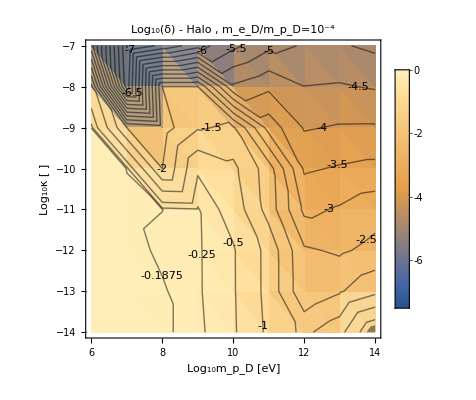

```mathematica
δtruthhalo = GetδTruth[computedδscanhalo10m4];
(*ListContourPlot[δtruth,ContourLabels->All]*)
Show[{ListDensityPlot[δtruthhalo,PlotLegends->Automatic,PlotLabel->"Log_10(δ) - Halo , m_e_D/m_p_D=10^-4",FrameLabel->{"Log_10m_p_D [eV]","Log_10κ [ ]"}],ListContourPlot[δtruthhalo,ContourLabels->All,ContourShading->False,Contours->Join[Table[i,{i,-0.25,0,0.0625}],Table[i,{i,-9,-0.5,0.5}]]],
ListContourPlot[δtruthhalo,Contours->{0},ContourStyle->Directive[Red,Thick],ContourLabels->True,ContourShading->None]}]
```

{{{6,-14,-13.4571},{6,-13,-11.4571},{6,-12,-9.45712},{6,-11,-7.45712},{6,-10,-5.45712},{6,-9,-3.45712},{6,-8,-1.45712},{6,-7,0.542884}},{{7,-14,-11.1282},{7,-13,-9.12823},{7,-12,-7.12823},{7,-11,-5.12823},{7,-10,-3.12823},{7,-9,-1.12823},{7,-8,0.871769},{7,-7,2.87177}},{{8,-14,-10.708},{8,-13,-8.70799},{8,-12,-6.70799},{8,-11,-4.70799},{8,-10,-2.70799},{8,-9,-0.707991},{8,-8,1.29201},{8,-7,3.29201}},{{9,-14,-11.2825},{9,-13,-9.28254},{9,-12,-7.28254},{9,-11,-5.28254},{9,-10,-3.28254},{9,-9,-1.28254},{9,-8,0.717465},{9,-7,2.71746}},{{10,-14,-12.0851},{10,-13,-10.0851},{10,-12,-8.08507},{10,-11,-6.08507},{10,-10,-4.08507},{10,-9,-2.08507},{10,-8,-0.0850675},{10,-7,1.91493}},{{11,-14,-13.0214},{11,-13,-11.0214},{11,-12,-9.02139},{11,-11,-7.02139},{11,-10,-5.02139},{11,-9,-3.02139},{11,-8,-1.02139},{11,-7,0.978606}},{{12,-14,-14.0149},{12,-13,-12.0149},{12,-12,-10.0149},{12,-11,-8.01495},{12,-10,-6.01495},{12,-9,-4.01495},{12,-8,-2.01495},{12,-7,-0.0149489}},{{13,-14,-15.0144},{13,-13,-13.0144},{13,-12,-11.0144},{13,-11,-9.01442},{13,-10,-7.01442},{13,-9,-5.01442},{13,-8,-3.01442},{13,-7,-1.01442}},{{14,-14,-16.0139},{14,-13,-14.0139},{14,-12,-12.0139},{14,-11,-10.0139},{14,-10,-8.01392},{14,-9,-6.01392},{14,-8,-4.01392},{14,-7,-2.01392}},{{15,-14,-17.0142},{15,-13,-15.0142},{15,-12,-13.0142},{15,-11,-11.0142},{15,-10,-9.01422},{15,-9,-7.01422},{15,-8,-5.01422},{15,-7,-3.01422}}}

Red contour is lower boundary of the thermalized regime (we expect > O(1) energy lost in the Earth for 99% of the incoming dark proton distribution)

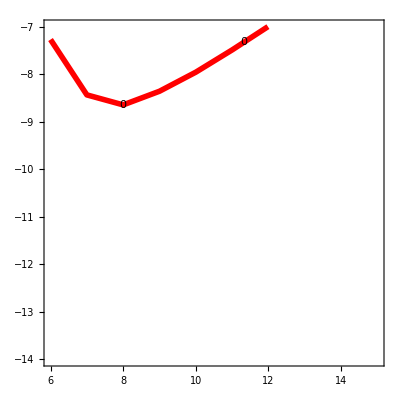

```mathematica
Eatvcuthalo=Table[
eind = FirstPosition["mχ"/.ElectronicσDicts,10^# ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]&@mind;
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^# ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]&@mind;

mχt=10^mind ("JpereV")/("c")^2/.Constants`SIConstRepl;
βDdict=Capture`v0toβD[220 10^3,#,10^-4#]&[mχt];
(*βDdict={"βD"->6/((1+10^-4)mχt (20 10^3)^2)};*)
vχcut = Capture`GetvχMax[1-10^-2,(*"βcore"/.EarthRepl*)"βD"/.βDdict,mχt,0 "vesc"/.EarthRepl];
(*Print[vχcut];*)

Eofv[vχ_?NumberQ]:=("rE"/.Constants`EarthRepl)("dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]]])[10^6,vχ]/((10^mind ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2(*-3/("βcore")*)/.EarthRepl);
{mind,mlogκ,Log10[10^(2 mlogκ) Eofv[vχcut(*+"vesc"*)] /.EarthRepl]},{mind,6,15},{mlogκ,-14,-7}]
"Red contour is lower boundary of the thermalized regime (we expect > O(1) energy lost in the Earth for 99% of the incoming dark proton distribution)"
Show[{(*ListContourPlot[Flatten[Eatvcuthalo,1],ContourLabels->True,PlotLabel->"(<E>)/E_K 1st v percentile - Core Disk",FrameLabel->{"Log_10m_p_D [eV]","Log_10κ [ ]"}],*)ListContourPlot[Flatten[Eatvcuthalo,1],ContourLabels->True,Contours->{0},ContourStyle->Directive[Red,Thickness[0.01],Opacity[1]],ContourShading->False]}]
```

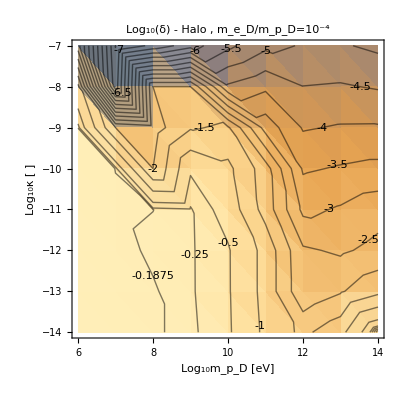
```mathematica
P1 = -Graphics-;
P2 = -Graphics-;
Show[{P1,P2}]
```

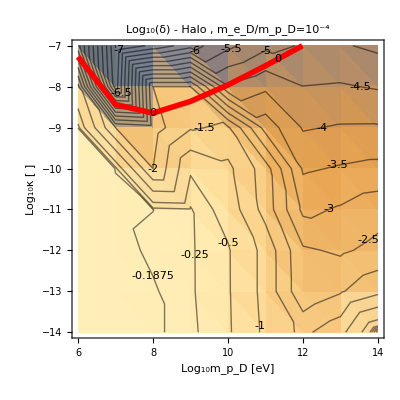

```mathematica
D[E^(- λDinv (r-rp))/(r-rp),r]//Simplify
```

(ⅇ^((-r+rp) λDinv) (-1-r λDinv+rp λDinv))/(r-rp)^2

#### get r_max and vesc truth plots

{{6.,-Log[100000000000000]/Log[10],-0.126914},{7.,-Log[100000000000000]/Log[10],-0.161193},{8.,-Log[100000000000000]/Log[10],-0.173888},{9.,-Log[100000000000000]/Log[10],-0.198118},{10.,-Log[100000000000000]/Log[10],-0.437575},{11.,-Log[100000000000000]/Log[10],-1.08691},{12.,-Log[100000000000000]/Log[10],-1.49502},{13.,-Log[100000000000000]/Log[10],-1.04353},{14.,-Log[100000000000000]/Log[10],-0.604935},{6.,-Log[10000000000000]/Log[10],-0.126914},{7.,-Log[10000000000000]/Log[10],-0.161193},{8.,-Log[10000000000000]/Log[10],-0.187891},{9.,-Log[10000000000000]/Log[10],-0.208721},{10.,-Log[10000000000000]/Log[10],-0.4462},{11.,-Log[10000000000000]/Log[10],-1.09782},{12.,-Log[10000000000000]/Log[10],-2.28302},{13.,-Log[10000000000000]/Log[10],-2.01702},{14.,-Log[10000000000000]/Log[10],-1.53284},{6.,-Log[1000000000000]/Log[10],-0.126914},{7.,-Log[1000000000000]/Log[10],-0.171108},{8.,-Log[1000000000000]/Log[10],-0.188849},{9.,-Log[1000000000000]/Log[10],-0.209678},{10.,-Log[1000000000000]/Log[10],-0.447175},{11.,-Log[1000000000000]/Log[10],-1.0979},{12.,-Log[1000000000000]/Log[10],-2.33575},{13.,-Log[1000000000000]/Log[10],-2.49882},{14.,-Log[1000000000000]/Log[10],-2.26673},{6.,-Log[100000000000]/Log[10],-0.126914},{7.,-Log[100000000000]/Log[10],-0.171608},{8.,-Log[100000000000]/Log[10],-0.180559},{9.,-Log[100000000000]/Log[10],-0.215708},{10.,-Log[100000000000]/Log[10],-0.659448},{11.,-Log[100000000000]/Log[10],-1.68518},{12.,-Log[100000000000]/Log[10],-3.04196},{13.,-Log[100000000000]/Log[10],-2.87838},{14.,-Log[100000000000]/Log[10],-2.70219},{6.,-Log[10000000000]/Log[10],-0.127547},{7.,-Log[10000000000]/Log[10],-0.181356},{8.,-Log[10000000000]/Log[10],-0.536474},{9.,-Log[10000000000]/Log[10],-2.},{10.,-Log[10000000000]/Log[10],-0.913045},{11.,-Log[10000000000]/Log[10],-1.75399},{12.,-Log[10000000000]/Log[10],-3.48626},{13.,-Log[10000000000]/Log[10],-3.35631},{14.,-Log[10000000000]/Log[10],-3.26509},{6.,-Log[1000000000]/Log[10],-0.180653},{7.,-Log[1000000000]/Log[10],-2.},{8.,-Log[1000000000]/Log[10],-4.45631},{9.,-Log[1000000000]/Log[10],-1.88622},{10.,-Log[1000000000]/Log[10],-1.71244},{11.,-Log[1000000000]/Log[10],-3.32424},{12.,-Log[1000000000]/Log[10],-4.01038},{13.,-Log[1000000000]/Log[10],-3.87533},{14.,-Log[1000000000]/Log[10],-3.85038},{6.,-Log[100000000]/Log[10],-0.815333},{7.,-Log[100000000]/Log[10],-5.54726},{8.,-Log[100000000]/Log[10],-2.},{9.,-Log[100000000]/Log[10],-2.},{10.,-Log[100000000]/Log[10],-4.13821},{11.,-Log[100000000]/Log[10],-4.35853},{12.,-Log[100000000]/Log[10],-4.66213},{13.,-Log[100000000]/Log[10],-4.51307},{14.,-Log[100000000]/Log[10],-4.49205},{6.,-Log[10000000]/Log[10],-2.},{7.,-Log[10000000]/Log[10],-5.54726},{8.,-Log[10000000]/Log[10],-4.90871},{9.,-Log[10000000]/Log[10],-4.35415},{10.,-Log[10000000]/Log[10],-4.13821},{11.,-Log[10000000]/Log[10],-4.3585},{12.,-Log[10000000]/Log[10],-4.84987},{13.,-Log[10000000]/Log[10],-5.0843},{14.,-Log[10000000]/Log[10],-5.31563}}

```mathematica
δtruthdisk[[1]]
```

{6.,-Log[100000000000000]/Log[10],-0.126914}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

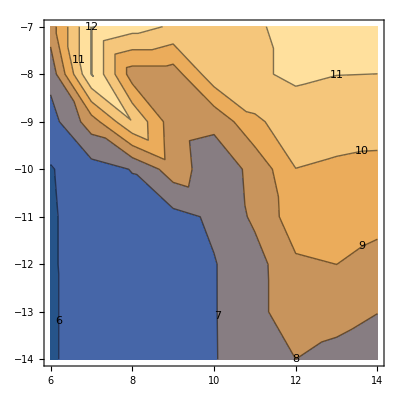

```mathematica
rmaxtruthdisk = Table[{δtruthdisk[[i,1]],δtruthdisk[[i,2]],Log10@getrmax[getncap[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[20 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^δtruthdisk[[i,1]]/.SIConstRepl][10^δtruthdisk[[i,3]]]},{i,Length[δtruthdisk]}];
ListContourPlot[rmaxtruthdisk,ContourLabels->True]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

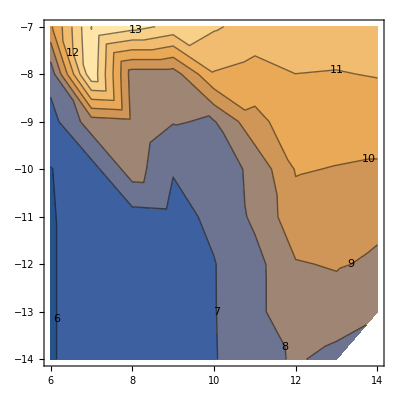

```mathematica
rmaxtruthhalo = Table[{δtruthhalo[[i,1]],δtruthhalo[[i,2]],Log10@getrmax[getncap[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[20 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^δtruthhalo[[i,1]]/.SIConstRepl][10^δtruthhalo[[i,3]]]},{i,Length[δtruthhalo]}];
ListContourPlot[rmaxtruthhalo,ContourLabels->True]
```

```mathematica
(*Clear[getϕDAnalyticEstimates]
getϕDAnalyticEstimates[mpD_,meD_,βD_,nF_,αDbyα_,ϕg_:Capture`Vgrav] := Module[{niofr,npD,neD,ρS,λD},
niofr = 1/(mi^2 Sqrt[2 π] βD^2) nF (mi βD)^(3/2) (2 mi vesc βD+E^(1/2 mi vesc^2 βD) Sqrt[2 π] Sqrt[mi βD]-E^(1/2 mi vesc^2 βD) Sqrt[mi] Sqrt[2 π] Sqrt[βD] Erf[(Sqrt[mi] vesc Sqrt[βD])/Sqrt[2]]);
npD=niofr/.vesc->√(-(2 Vgp)/mi)/.mi->mpD;
neD=niofr/.vesc->√(-(2 Vge)/mi)/.mi->meD;
ρS = ("e")/("ϵ0")√αDbyα(npD-neD)/.{Vgp->mpD ϕg[r],Vge->meD ϕg[r]};
(*λD = (("e")^2/("ϵ0")αDbyα(D[npD,Vgp]+D[neD,Vge]))^(-1/2)/.{Vgp->mpD ϕg[r],Vge->mpD ϕg[r]};*)
λD =(-("e")^2/("ϵ0")αDbyα(D[npD,Vgp]+D[neD,Vge])/.{Vgp->mpD ϕg[r],Vge->meD ϕg[r]})^(-1/2);
<|"ϕD"->ρS λD^2,"ρS"->ρS,"λD"->λD|>
]*)
```

```mathematica
getϕDAnalyticEstimates[mpD,meD,βD,nF,1]//Simplify//PowerExpand//Simplify
```

<|ϕD→(1/(mpD^2 (√2 √π) βD^2)nF (mpD^(3/2) βD^(3/2)) (ⅇ^(-mpD βD ϕgt[r]) (√2 √π) (√mpD √βD)-ⅇ^(-mpD βD ϕgt[r]) √mpD (√2 √π) √βD Erf[√mpD √βD (√-1 √ϕgt[r])]+2 √2 mpD βD (√-1 √ϕgt[r]))-1/(meD^2 (√2 √π) βD^2)nF (meD^(3/2) βD^(3/2)) (ⅇ^(-mpD βD ϕgt[r]) (√2 √π) (√meD √βD)-ⅇ^(-mpD βD ϕgt[r]) √meD (√2 √π) √βD Erf[√meD √βD (√-1 (meD^(-1/2) (√mpD √ϕgt[r])))]+2 √2 meD βD (√-1 (meD^(-1/2) (√mpD √ϕgt[r])))))/(e (1/(mpD^2 (√2 √π) βD^2)nF (mpD^(3/2) βD^(3/2)) (-ⅇ^(-mpD βD ϕgt[r]) (√2 √π) βD (√mpD √βD)+ⅇ^(-mpD βD ϕgt[r]) √mpD (√2 √π) βD^(3/2) Erf[√mpD √βD (√-1 √ϕgt[r])])+1/(meD^2 (√2 √π) βD^2)nF (meD^(3/2) βD^(3/2)) (-ⅇ^(-mpD βD ϕgt[r]) (√2 √π) βD (√meD √βD)+ⅇ^(-mpD βD ϕgt[r]) √meD (√2 √π) βD^(3/2) Erf[√meD √βD (√-1 (meD^(-1/2) (√mpD √ϕgt[r])))]))),ρS→1/ϵ0 e (1/(mpD^2 (√2 √π) βD^2)nF (mpD^(3/2) βD^(3/2)) (ⅇ^(-mpD βD ϕgt[r]) (√2 √π) (√mpD √βD)-ⅇ^(-mpD βD ϕgt[r]) √mpD (√2 √π) √βD Erf[√mpD √βD (√-1 √ϕgt[r])]+2 √2 mpD βD (√-1 √ϕgt[r]))-1/(meD^2 (√2 √π) βD^2)nF (meD^(3/2) βD^(3/2)) (ⅇ^(-mpD βD ϕgt[r]) (√2 √π) (√meD √βD)-ⅇ^(-mpD βD ϕgt[r]) √meD (√2 √π) √βD Erf[√meD √βD (√-1 (meD^(-1/2) (√mpD √ϕgt[r])))]+2 √2 meD βD (√-1 (meD^(-1/2) (√mpD √ϕgt[r]))))),λD→(e^((2 (-1))/2) ϵ0^(--1/2))/(√(1/(mpD^2 (√2 √π) βD^2)nF (mpD^(3/2) βD^(3/2)) (-ⅇ^(-mpD βD ϕgt[r]) (√2 √π) βD (√mpD √βD)+ⅇ^(-mpD βD ϕgt[r]) √mpD (√2 √π) βD^(3/2) Erf[√mpD √βD (√-1 √ϕgt[r])])+1/(meD^2 (√2 √π) βD^2)nF (meD^(3/2) βD^(3/2)) (-ⅇ^(-mpD βD ϕgt[r]) (√2 √π) βD (√meD √βD)+ⅇ^(-mpD βD ϕgt[r]) √meD (√2 √π) βD^(3/2) Erf[√meD √βD (√-1 (meD^(-1/2) (√mpD √ϕgt[r])))])))|>

```mathematica
getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[20 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^δtruthhalo[[5,1]]/.SIConstRepl/.ϕg[r]->(-("vesc")^2)/2/.EarthRepl//N
1-(√(("vesc")^2-("e"2"ϕD"/.%)/(("JpereV")/("c")^2 10^δtruthhalo[[5,1]])))/("vesc")/.SIConstRepl/.EarthRepl
(*/.r->0.999999"rE"/.EarthRepl//N*)
```

<|ϕD→2.755,ρS→0.0000144047,λD→437.329|>

0.222535

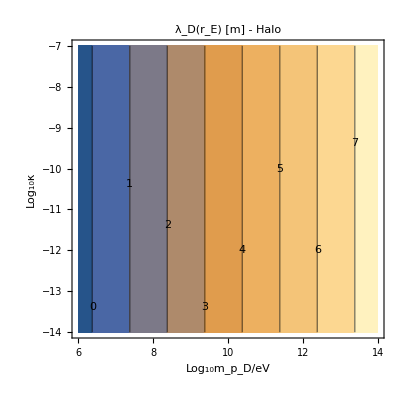

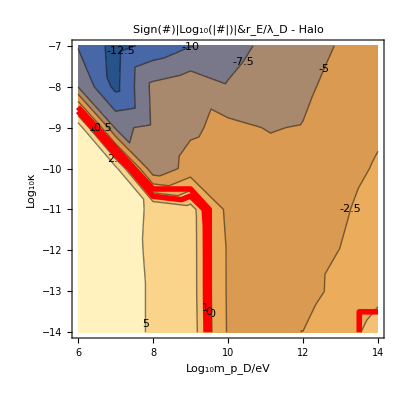

Upshot, aside from the thin neighborhood around the 0 contour, we are either in the high or low capture regime.

```mathematica
λhalo = Table[{δtruthhalo[[i,1]],δtruthhalo[[i,2]],Log10@("λD"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[220 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^δtruthhalo[[i,1]]/.r->0.999999"rE"/.EarthRepl/.SIConstRepl)},{i,Length[δtruthhalo]}];
ListContourPlot[λhalo,ContourLabels->True,PlotLabel->"λ_D(r_E) [m] - Halo",FrameLabel->{"Log_10m_p_D/eV" , "Log_10κ"}]
regimeparamhalo=Re@Table[{λhalo[[i,1]],λhalo[[i,2]],(*Log10@(("rE"-10^rmaxtruthhalo[[i,3]])/10^λhalo[[i,3]]/.EarthRepl)*)Sign[#]Abs@Log10@(Abs[#])&[("rE"-10^rmaxtruthhalo[[i,3]])/10^λhalo[[i,3]]/.EarthRepl]},{i,Length[rmaxtruthhalo]}];
ListContourPlot[%,ContourLabels->All,FrameLabel->{"Log_10m_p_D/eV" , "Log_10κ"},PlotLabel->"Sign(#)|Log_10(|#|)|&r_E/λ_D - Halo"];
Show[{%,ListContourPlot[regimeparamhalo,ContourLabels->True,Contours->{1},ContourStyle->Directive[Red,Thickness[0.01],Opacity[1]],ContourShading->False],ListContourPlot[Table[{λhalo[[i,1]],λhalo[[i,2]],Sign@(#)&[("rE"-10^rmaxtruthhalo[[i,3]])/10^λhalo[[i,3]]/.EarthRepl]},{i,Length[rmaxtruthhalo]}],ContourLabels->True,Contours->{0},ContourStyle->Directive[Red,Thickness[0.01],Opacity[1]],ContourShading->False]}]
"Upshot, aside from the thin neighborhood around the 0 contour, we are either in the high or low capture regime."
```

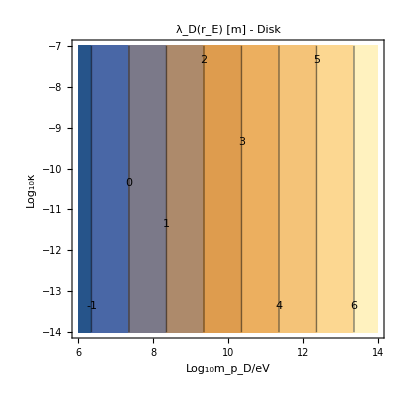

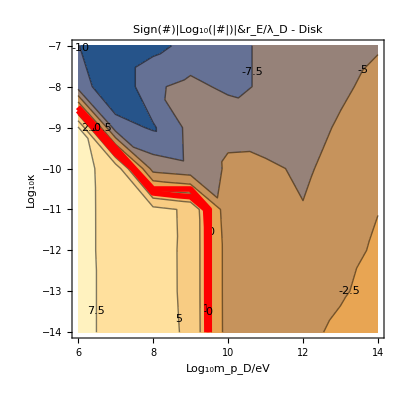

Upshot, aside from the thin neighborhood around the 0 contour, we are either in the high or low capture regime.

```mathematica
λdisk = Table[{δtruthdisk[[i,1]],δtruthdisk[[i,2]],Log10@("λD"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[20 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^δtruthdisk[[i,1]]/.r->0.999999"rE"/.EarthRepl/.SIConstRepl)},{i,Length[δtruthdisk]}];
ListContourPlot[λdisk,ContourLabels->True,PlotLabel->"λ_D(r_E) [m] - Disk",FrameLabel->{"Log_10m_p_D/eV" , "Log_10κ"}]
regimeparamdisk=Table[{λdisk[[i,1]],λdisk[[i,2]],Sign[#]Abs@Log10@(Abs[#])&[("rE"-10^rmaxtruthdisk[[i,3]])/10^λdisk[[i,3]]/.EarthRepl]},{i,Length[rmaxtruthdisk]}];
ListContourPlot[%,ContourLabels->All,FrameLabel->{"Log_10m_p_D/eV" , "Log_10κ"},PlotLabel->"Sign(#)|Log_10(|#|)|&r_E/λ_D - Disk"];
Show[{%,ListContourPlot[regimeparamdisk,ContourLabels->True,Contours->{1},ContourStyle->Directive[Red,Thickness[0.01],Opacity[1]],ContourShading->False],ListContourPlot[Table[{λdisk[[i,1]],λdisk[[i,2]],Sign@(#)&[("rE"-10^rmaxtruthdisk[[i,3]])/10^λdisk[[i,3]]/.EarthRepl]},{i,Length[rmaxtruthdisk]}],ContourLabels->True,Contours->{0},ContourStyle->Directive[Red,Thickness[0.01],Opacity[1]],ContourShading->False]}]
"Upshot, aside from the thin neighborhood around the 0 contour, we are either in the high or low capture regime."
```

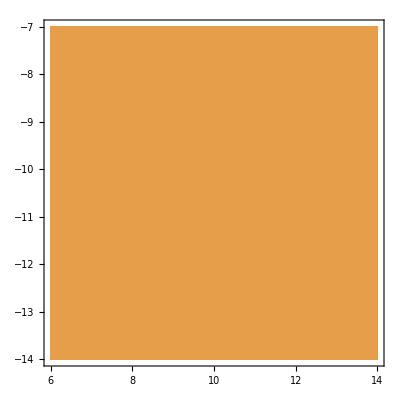

0.372094

Wow, so βD eD ϕD is constant wrt κ and mpD, and importantly it is small so we can use the linearized approximation

-Graphics-

0.395548

```mathematica
ϕDirreddisk = Table[{δtruthdisk[[i,1]],δtruthdisk[[i,2]],Log10@("ϕD"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD",naDM[0.05,(1 + 10^-4)mpD],1]/.Capture`v0toβD[20 10^3,mpD,10^-4 mpD]/. mpD->("JpereV")/("c")^2 10^δtruthdisk[[i,1]]/.r->0.999999"rE"/.EarthRepl/.SIConstRepl)},{i,Length[δtruthdisk]}];
Table[{δtruthdisk[[i,1]],δtruthdisk[[i,2]],Log10@("e""βD""ϕD"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD",naDM[0.05,(1 + 10^-4)mpD],1]/.Capture`v0toβD[20 10^3,mpD,10^-4 mpD]/. mpD->("JpereV")/("c")^2 10^δtruthdisk[[i,1]]/.r->0.999999"rE"/.EarthRepl/.SIConstRepl)},{i,Length[δtruthdisk]}];
ListContourPlot[%,ContourLabels->True]
10^%%[[1,3]]
"Wow, so βD eD ϕD is constant wrt κ and mpD, and importantly it is small so we can use the linearized approximation"
Table[{δtruthdisk[[i,1]],δtruthdisk[[i,2]],Log10@((2"e""ϕD")/(mpD("vesc")^2)/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD",naDM[0.05,(1 + 10^-4)mpD],1]/.Capture`v0toβD[20 10^3,mpD,10^-4 mpD]/. mpD->("JpereV")/("c")^2 10^δtruthdisk[[i,1]]/.r->0.999999"rE"/.EarthRepl/.SIConstRepl)},{i,Length[δtruthdisk]}];
ListContourPlot[%,ContourLabels->True]
10^%%[[1,3]]
```

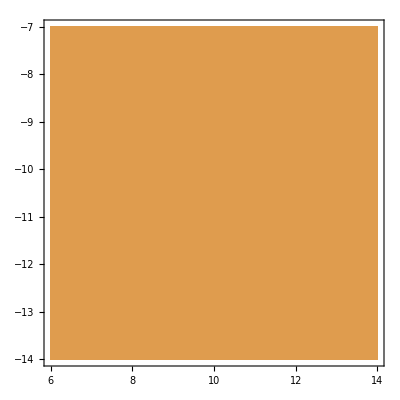

0.00382142

Wow, and βD apparently. This makes sense, ϕD ~ βD^-1. So I suppose the value of ϕD is just a function of the mass ratio and ϕg

-Graphics-

0.491537

```mathematica
ϕDirredhalo = Table[{δtruthhalo[[i,1]],δtruthhalo[[i,2]],Log10@("ϕD"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD",naDM[0.05,(1 + 10^-4)mpD],1]/.Capture`v0toβD[220 10^3,mpD,10^-4 mpD]/. mpD->("JpereV")/("c")^2 10^δtruthhalo[[i,1]]/.r->0.999999"rE"/.EarthRepl/.SIConstRepl)},{i,Length[δtruthhalo]}];
Table[{δtruthhalo[[i,1]],δtruthhalo[[i,2]],Log10@("e""βD""ϕD"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD",naDM[0.05,(1 + 10^-4)mpD],1]/.Capture`v0toβD[220 10^3,mpD,10^-4 mpD]/. mpD->("JpereV")/("c")^2 10^δtruthhalo[[i,1]]/.r->0.999999"rE"/.EarthRepl/.SIConstRepl)},{i,Length[δtruthhalo]}];
ListContourPlot[%,ContourLabels->True]
10^%%[[1,3]]
"Wow, and βD apparently. This makes sense, ϕD ~ βD^-1. So I suppose the value of ϕD is just a function of the mass ratio and ϕg"
Table[{δtruthhalo[[i,1]],δtruthhalo[[i,2]],Log10@((2"e""ϕD")/(mpD("vesc")^2)/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD",naDM[0.05,(1 + 10^-4)mpD],1]/.Capture`v0toβD[220 10^3,mpD,10^-4 mpD]/. mpD->("JpereV")/("c")^2 10^δtruthhalo[[i,1]]/.r->0.999999"rE"/.EarthRepl/.SIConstRepl)},{i,Length[δtruthhalo]}];
ListContourPlot[%,ContourLabels->True]
10^%%[[1,3]]
```

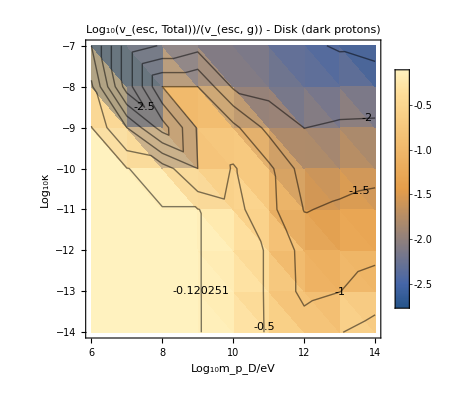

```mathematica
(*Table[{δtruthhalo[[i,1]],δtruthhalo[[i,2]],Log10@((2"e""ϕD")/(("vesc")^2 mpD)/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD",naDM[0.05,(1 + 10^-4)mpD],1]/.Capture`v0toβD[220 10^3,mpD,10^-4 mpD]/. mpD->("JpereV")/("c")^2 10^δtruthhalo[[i,1]]/.r->0.999999"rE"/.EarthRepl/.SIConstRepl)},{i,Length[δtruthhalo]}]*)
regimeparamdisk;
δtruthdisk;
ϕDirreddisk;
Table[{regimeparamdisk[[i,1]],regimeparamdisk[[i,2]],If[regimeparamdisk[[i,3]]>0,1/2 Log10@(("vesc")^2-(2"e"10^ϕDirreddisk[[i,3]])/(("JpereV")/("c")^2 10^δtruthdisk[[i,1]]))-Log10["vesc"],1/2 Log10@(10^δtruthdisk[[i,3]]("vesc")^2)-Log10["vesc"]]/.EarthRepl/.SIConstRepl},{i,Length[regimeparamdisk]}];
Show[{ListDensityPlot[%,PlotRange->All,PlotLegends->Automatic,FrameLabel->{"Log_10m_p_D/eV" , "Log_10κ"},PlotLabel->"Log_10(v_(esc, Total))/(v_(esc, g)) - Disk (dark protons)"],ListContourPlot[%(*Contours->Join[(*Table[i,{i,0.0,-0.5,-0.1}]*)Table[i,{i,-3,-0.5,0.5}](*,Table[-10^i,{i,-3,Log10[0.05],0.1}]*)]*),Contours->Join[{1.1Max[%[[;;,3]]]},Table[i,{i,-3,-0.5,0.5}]],ContourLabels->True,PlotRange->All,ContourShading->None]}]
(*ListContourPlot[%%,Contours->Join[(*Table[i,{i,,-0.5,-0.1}]*){Max[%%[[;;,3]]]},Table[i,{i,-3,-0.5,0.5}](*,Table[-10^i,{i,-3,Log10[0.05],0.1}]*)],ContourLabels->True,PlotRange->All,ContourShading->None]*)
```

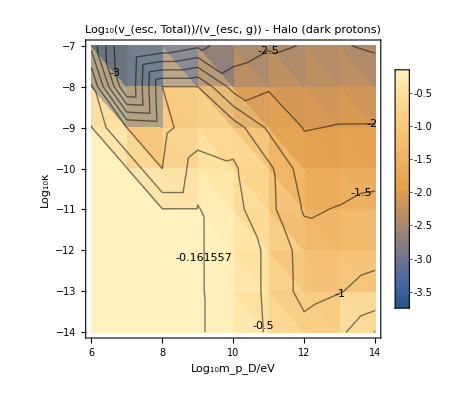

```mathematica
Table[{regimeparamhalo[[i,1]],regimeparamhalo[[i,2]],If[regimeparamhalo[[i,3]]>0,1/2 Log10@(("vesc")^2-(2"e"10^ϕDirredhalo[[i,3]])/(("JpereV")/("c")^2 10^δtruthhalo[[i,1]]))-Log10["vesc"],1/2 Log10@(10^δtruthhalo[[i,3]]("vesc")^2)-Log10["vesc"]]/.EarthRepl/.SIConstRepl},{i,Length[regimeparamhalo]}];
Show[{ListDensityPlot[%,PlotRange->All,PlotLegends->Automatic,FrameLabel->{"Log_10m_p_D/eV" , "Log_10κ"},PlotLabel->"Log_10(v_(esc, Total))/(v_(esc, g)) - Halo (dark protons)"],ListContourPlot[%(*Contours->Join[(*Table[i,{i,0.0,-0.5,-0.1}]*)Table[i,{i,-3,-0.5,0.5}](*,Table[-10^i,{i,-3,Log10[0.05],0.1}]*)]*),Contours->Join[{1.1Max[%[[;;,3]]]},Table[i,{i,-3,-0.5,0.5}]],ContourLabels->True,PlotRange->All,ContourShading->None]}]
```

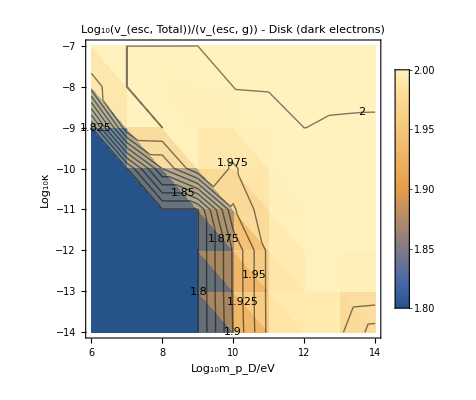

```mathematica
Table[{regimeparamdisk[[i,1]],regimeparamdisk[[i,2]],If[regimeparamdisk[[i,3]]>0,1/2 Log10@(("vesc")^2+(2"e"10^ϕDirreddisk[[i,3]])/(("JpereV")/("c")^2 10^(δtruthdisk[[i,1]]-4)))-Log10["vesc"],1/2 Log10@((1+(1-10^δtruthdisk[[i,3]])10^4)("vesc")^2)-Log10["vesc"]]/.EarthRepl/.SIConstRepl},{i,Length[regimeparamdisk]}];
Show[{ListDensityPlot[%,PlotRange->All,PlotLegends->Automatic,FrameLabel->{"Log_10m_p_D/eV" , "Log_10κ"},PlotLabel->"Log_10(v_(esc, Total))/(v_(esc, g)) - Disk (dark electrons)"],ListContourPlot[%(*Contours->Join[(*Table[i,{i,0.0,-0.5,-0.1}]*)Table[i,{i,-3,-0.5,0.5}](*,Table[-10^i,{i,-3,Log10[0.05],0.1}]*)]*)(*Contours->Join[{1.1Max[%[[;;,3]]]},Table[i,{i,-3,-0.5,0.5}]]*),ContourLabels->True,PlotRange->All,ContourShading->None]}]
```

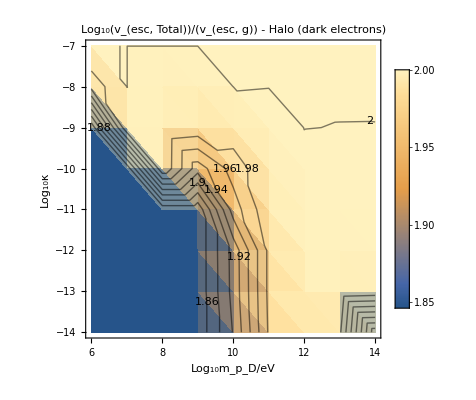

```mathematica
Table[{regimeparamhalo[[i,1]],regimeparamhalo[[i,2]],If[regimeparamhalo[[i,3]]>0,1/2 Log10@(("vesc")^2+(2"e"10^ϕDirredhalo[[i,3]])/(("JpereV")/("c")^2 10^(δtruthhalo[[i,1]]-4)))-Log10["vesc"],1/2 Log10@((1+(1-10^δtruthhalo[[i,3]])10^4)("vesc")^2)-Log10["vesc"]]/.EarthRepl/.SIConstRepl},{i,Length[regimeparamhalo]}];
Show[{ListDensityPlot[%,PlotRange->All,PlotLegends->Automatic,FrameLabel->{"Log_10m_p_D/eV" , "Log_10κ"},PlotLabel->"Log_10(v_(esc, Total))/(v_(esc, g)) - Halo (dark electrons)"],ListContourPlot[%(*Contours->Join[(*Table[i,{i,0.0,-0.5,-0.1}]*)Table[i,{i,-3,-0.5,0.5}](*,Table[-10^i,{i,-3,Log10[0.05],0.1}]*)]*)(*,Contours->Join[{1.1Max[%[[;;,3]]]},Table[i,{i,-3,-0.5,0.5}]]*),ContourLabels->True,PlotRange->All,ContourShading->None]}]
```

#### Is rmax always >> λD?

```mathematica
Abs@rmaxtruthhalo
```

{{6.,Log[100000000000000]/Log[10],5.9088},{7.,Log[100000000000000]/Log[10],6.52413},{8.,Log[100000000000000]/Log[10],6.58579},{9.,Log[100000000000000]/Log[10],6.64657},{10.,Log[100000000000000]/Log[10],6.94089},{11.,Log[100000000000000]/Log[10],7.60767},{12.,Log[100000000000000]/Log[10],8.12012},{13.,Log[100000000000000]/Log[10],7.66172},{14.,Log[100000000000000]/Log[10],3.85447},{6.,Log[10000000000000]/Log[10],5.9088},{7.,Log[10000000000000]/Log[10],6.52413},{8.,Log[10000000000000]/Log[10],6.58582},{9.,Log[10000000000000]/Log[10],6.69086},{10.,Log[10000000000000]/Log[10],6.95906},{11.,Log[10000000000000]/Log[10],7.65652},{12.,Log[10000000000000]/Log[10],8.88332},{13.,Log[10000000000000]/Log[10],8.55134},{14.,Log[10000000000000]/Log[10],8.12774},{6.,Log[1000000000000]/Log[10],5.9088},{7.,Log[1000000000000]/Log[10],6.52425},{8.,Log[1000000000000]/Log[10],6.63797},{9.,Log[1000000000000]/Log[10],6.69344},{10.,Log[1000000000000]/Log[10],6.96208},{11.,Log[1000000000000]/Log[10],7.6571},{12.,Log[1000000000000]/Log[10],8.93092},{13.,Log[1000000000000]/Log[10],9.0782},{14.,Log[1000000000000]/Log[10],8.85736},{6.,Log[100000000000]/Log[10],5.90889},{7.,Log[100000000000]/Log[10],6.57355},{8.,Log[100000000000]/Log[10],6.60473},{9.,Log[100000000000]/Log[10],6.7054},{10.,Log[100000000000]/Log[10],7.1857},{11.,Log[100000000000]/Log[10],8.19956},{12.,Log[100000000000]/Log[10],9.61874},{13.,Log[100000000000]/Log[10],9.45104},{14.,Log[100000000000]/Log[10],9.20408},{6.,Log[10000000000]/Log[10],5.96411},{7.,Log[10000000000]/Log[10],6.61048},{8.,Log[10000000000]/Log[10],8.50322},{9.,Log[10000000000]/Log[10],7.05906},{10.,Log[10000000000]/Log[10],7.37879},{11.,Log[10000000000]/Log[10],8.26075},{12.,Log[10000000000]/Log[10],10.0693},{13.,Log[10000000000]/Log[10],9.95781},{14.,Log[10000000000]/Log[10],9.87331},{6.,Log[1000000000]/Log[10],6.60946},{7.,Log[1000000000]/Log[10],8.50322},{8.,Log[1000000000]/Log[10],8.7322},{9.,Log[1000000000]/Log[10],8.04814},{10.,Log[1000000000]/Log[10],7.92868},{11.,Log[1000000000]/Log[10],9.70468},{12.,Log[1000000000]/Log[10],10.5468},{13.,Log[1000000000]/Log[10],10.4607},{14.,Log[1000000000]/Log[10],10.4561},{6.,Log[100000000]/Log[10],7.361},{7.,Log[100000000]/Log[10],13.8015},{8.,Log[100000000]/Log[10],8.50322},{9.,Log[100000000]/Log[10],8.50322},{10.,Log[100000000]/Log[10],10.9258},{11.,Log[100000000]/Log[10],10.6087},{12.,Log[100000000]/Log[10],10.995},{13.,Log[100000000]/Log[10],10.9561},{14.,Log[100000000]/Log[10],11.0468},{6.,Log[10000000]/Log[10],9.79185},{7.,Log[10000000]/Log[10],14.0118},{8.,Log[10000000]/Log[10],13.3686},{9.,Log[10000000]/Log[10],12.7134},{10.,Log[10000000]/Log[10],12.1185},{11.,Log[10000000]/Log[10],11.6222},{12.,Log[10000000]/Log[10],11.4713},{13.,Log[10000000]/Log[10],11.4506},{14.,Log[10000000]/Log[10],11.6074}}

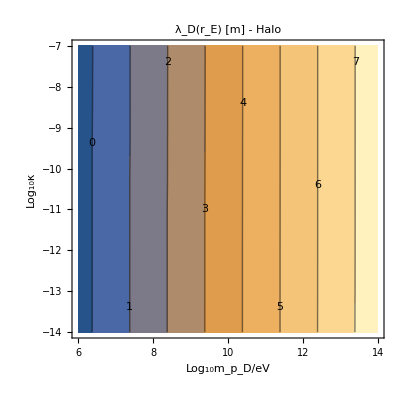

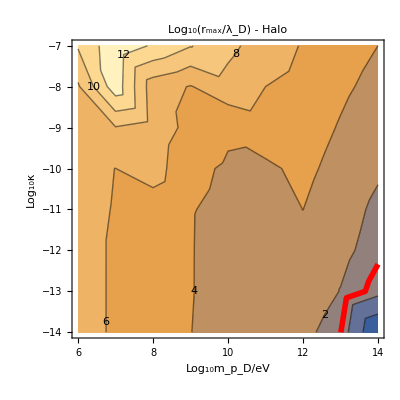

Upshot, aside from the thin neighborhood around the 0 contour, we are either in the high or low capture regime.

```mathematica
λhalo = Table[{δtruthhalo[[i,1]],δtruthhalo[[i,2]],Log10@("λD"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[220 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^δtruthhalo[[i,1]]/.r->(*0.999999"rE"*)Re[10^rmaxtruthhalo[[i,3]]]/.EarthRepl/.SIConstRepl)},{i,Length[δtruthhalo]}];
ListContourPlot[λhalo,ContourLabels->True,PlotLabel->"λ_D(r_E) [m] - Halo",FrameLabel->{"Log_10m_p_D/eV" , "Log_10κ"}]
regimeparamhalo=Re@Table[{λhalo[[i,1]],λhalo[[i,2]],(*Log10@(("rE"-10^rmaxtruthhalo[[i,3]])/10^λhalo[[i,3]]/.EarthRepl)*)Log10[#]&[10^rmaxtruthhalo[[i,3]]/10^λhalo[[i,3]]/.EarthRepl]},{i,Length[rmaxtruthhalo]}];
ListContourPlot[%,ContourLabels->All,FrameLabel->{"Log_10m_p_D/eV" , "Log_10κ"},PlotLabel->"Log_10(r_max/λ_D) - Halo"];
Show[{%,ListContourPlot[regimeparamhalo,ContourLabels->True,Contours->{1},ContourStyle->Directive[Red,Thickness[0.01],Opacity[1]],ContourShading->False](*,ListContourPlot[Table[{λhalo[[i,1]],λhalo[[i,2]],Sign@(#)&[10^rmaxtruthhalo[[i,3]]/10^λhalo[[i,3]]/.EarthRepl]},{i,Length[rmaxtruthhalo]}],ContourLabels->True,Contours->{0},ContourStyle->Directive[Red,Thickness[0.01],Opacity[1]],ContourShading->False]*)}]
"Upshot, aside from the thin neighborhood around the 0 contour, we are either in the high or low capture regime."
```

-Graphics-

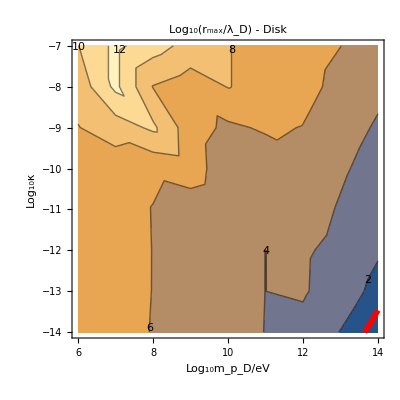

Upshot, aside from the thin neighborhood around the 0 contour, we are either in the high or low capture regime.

```mathematica
λdisk = Table[{δtruthdisk[[i,1]],δtruthdisk[[i,2]],Log10@("λD"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[20 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^δtruthdisk[[i,1]]/.r->(*0.999999"rE"*)Re[10^rmaxtruthdisk[[i,3]]]/.EarthRepl/.SIConstRepl)},{i,Length[δtruthdisk]}];
ListContourPlot[λhalo,ContourLabels->True,PlotLabel->"λ_D(r_E) [m] - Halo",FrameLabel->{"Log_10m_p_D/eV" , "Log_10κ"}]
regimeparamhalo=Re@Table[{λhalo[[i,1]],λhalo[[i,2]],(*Log10@(("rE"-10^rmaxtruthhalo[[i,3]])/10^λhalo[[i,3]]/.EarthRepl)*)Log10[#]&[10^rmaxtruthdisk[[i,3]]/10^λdisk[[i,3]]/.EarthRepl]},{i,Length[rmaxtruthhalo]}];
ListContourPlot[%,ContourLabels->All,FrameLabel->{"Log_10m_p_D/eV" , "Log_10κ"},PlotLabel->"Log_10(r_max/λ_D) - Disk"];
Show[{%,ListContourPlot[regimeparamhalo,ContourLabels->True,Contours->{1},ContourStyle->Directive[Red,Thickness[0.01],Opacity[1]],ContourShading->False](*,ListContourPlot[Table[{λhalo[[i,1]],λhalo[[i,2]],Sign@(#)&[10^rmaxtruthhalo[[i,3]]/10^λhalo[[i,3]]/.EarthRepl]},{i,Length[rmaxtruthhalo]}],ContourLabels->True,Contours->{0},ContourStyle->Directive[Red,Thickness[0.01],Opacity[1]],ContourShading->False]*)}]
"Upshot, aside from the thin neighborhood around the 0 contour, we are either in the high or low capture regime."
```

#### Look at maximal change in λ_D and scaling of ρ_S

```mathematica
Table[Log10@("λD"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[220 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^m/.r->0/.EarthRepl/.SIConstRepl),{m,6,14}]
Table[Log10@("λD"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[220 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^m/.r->10^11/.EarthRepl/.SIConstRepl),{m,6,14}]
```

{-0.378844,0.621156,1.62116,2.62116,3.62116,4.62116,5.62116,6.62116,7.62116}

{-0.391305,0.608695,1.6087,2.6087,3.6087,4.6087,5.6087,6.6087,7.6087}

```mathematica
Table[Log10@("λD"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[20 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^m/.r->0/.EarthRepl/.SIConstRepl),{m,6,14}]
Table[Log10@("λD"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[20 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^m/.r->10^11/.EarthRepl/.SIConstRepl),{m,6,14}]
```

{-1.35031,-0.350305,0.649695,1.64969,2.64969,3.64969,4.64969,5.64969,6.64969}

{-1.43183,-0.431831,0.568169,1.56817,2.56817,3.56817,4.56817,5.56817,6.56817}

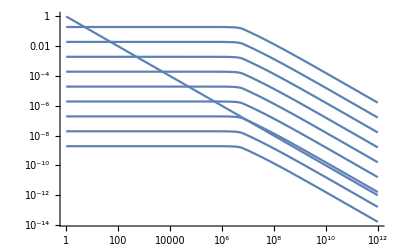

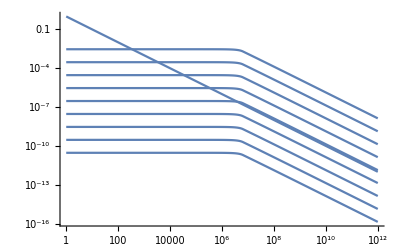

```mathematica
Table[(*Log10@*)("ρS"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[20 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^m/.EarthRepl/.SIConstRepl),{m,6,14}];
LogLogPlot[Join[{%,1/r}],{r,1,10^12}]
Table[(*Log10@*)("ρS"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[220 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^m/.EarthRepl/.SIConstRepl),{m,6,14}];
LogLogPlot[Join[{%,1/r}],{r,1,10^12}]
```

```mathematica
Table[(*Log10@*)("λD"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[20 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^m/.EarthRepl/.SIConstRepl),{m,6,14}];
LogLogPlot[Join[{%,1}],{r,1,10^12}]
Table[(*Log10@*)("λD"/.getϕDAnalyticEstimates[mpD,10^-4 mpD,"βD"/.Capture`v0toβD[220 10^3,mpD,10^-4 mpD],naDM[0.05,(1 + 10^-4)mpD],1]/. mpD->("JpereV")/("c")^2 10^m/.EarthRepl/.SIConstRepl),{m,6,14}];
LogLogPlot[Join[{%,1}],{r,1,10^12}]
```

-Graphics-

-Graphics-

#### Debug difference in modules

```mathematica
Log10@{"mpD"("c")^2/("JpereV"),"κ"}/.computeδtest[[1]]["δtable"]/.SIConstRepl//N//Round;
Position[%,{7,-8}];
Quiet@Table[{Log10@"δ"/.computeδtest[[i]],Log10@("δtable"/.computeδtest[[i]])[[%[[1,1]]]]["δ"]},{i,Length[computeδtest]}]//N;
(*ListPlot[10^%,PlotRange->{0,1}]*)
Interpolation[%,InterpolationOrder->1];
(*Plot[10^%[Log10@δ],{δ,0,1},PlotRange->{{-0.1,1.1},{-0.1,1.1}}]*)
(*Out[-4][[Out[-3][[1,1]]]]*)
Plot[{%[δ],δ},{δ,-6,0},PlotRange->All,AxesLabel->{"Log_10δ_in","Log_10δ_out"},(*PlotLabel->StringForm["δ_out(δ_in) - m_eD/m_pD=`` , κ=``",#[[1]],#[[2]]]&[Out[-4][[Out[-3][[1,1]]]]]*)PlotLabel->StringForm["δ_out(δ_in) - Log_10m_pD/eV=`` , Log_10κ=``",Out[-4][[Out[-3][[1,1]]]][[1]],Out[-4][[Out[-3][[1,1]]]][[2]]],PlotStyle->{Blue,Orange},PlotLegends->LineLegend[{Blue,Orange},{"Computed δ","δ_in=δ_out"}]]
FindRoot[10^%%[Log10@δ]-δ,{δ,0.01}]
Log10@δ/.%
```

InterpolatingFunction::dmval: Input value {-5.99988} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

InterpolatingFunction::dmval: Input value {-5.47487} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.54599} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.54726} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{δ→2.83619×10^-6}

-5.54726

```mathematica
computedδscanDisk10m4=ReadIt[NotebookDirectory[]<>"δscanDisk10m4"];
```

```mathematica
("δtable"/.computedδscanDisk10m4[[1]])[[;;,;;2]]//N//Round;
Position[%,{7,-8}]
Quiet@Table[{Log10@"δ","δtable"[[%[[1,1]],3]]}/.computedδscanDisk10m4[[i]],{i,Length[computedδscanDisk10m4]}]//N
(*ListPlot[10^%,PlotRange->{0,1}]*)
Interpolation[%,InterpolationOrder->1];
(*Plot[10^%[Log10@δ],{δ,0,1},PlotRange->{{-0.1,1.1},{-0.1,1.1}}]*)
(*Out[-4][[Out[-3][[1,1]]]]*)
Plot[{%[δ],δ},{δ,-6,0},PlotRange->All,AxesLabel->{"Log_10δ_in","Log_10δ_out"},(*PlotLabel->StringForm["δ_out(δ_in) - m_eD/m_pD=`` , κ=``",#[[1]],#[[2]]]&[Out[-4][[Out[-3][[1,1]]]]]*)PlotLabel->StringForm["δ_out(δ_in) - Log_10m_pD/eV=`` , Log_10κ=``",Out[-4][[Out[-3][[1,1]]]][[1]],Out[-4][[Out[-3][[1,1]]]][[2]]],PlotStyle->{Blue,Orange},PlotLegends->LineLegend[{Blue,Orange},{"Computed δ","δ_in=δ_out"}]]
FindRoot[10^%%[Log10@δ]-δ,{δ,0.01}]
Log10@δ/.%
```

{{56}}

{{-5.,-5.42384},{0.,-2.39025},{-1.,-4.5043},{-0.0457575,-2.39775},{-2.,-4.74727},{-0.187087,-2.42192},{-0.455932,-2.47391}}

InterpolatingFunction::dmval: Input value {-5.99988} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

InterpolatingFunction::dmval: Input value {-5.47487} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.54599} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.54726} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{δ→2.83619×10^-6}

-5.54726

```mathematica
δdicttestdisk=GetδDictTruth[computeδtest]//N;
Position[Log10@{"mpD"("c")^2/("JpereV"),"κ"}/.δdicttestdisk/.Constants`SIConstRepl//N//Round,{13,-13}]
{"mpD"("c")^2/("JpereV"),"κ","δ"}/.δdicttestdisk[[%[[1,1]]]]/.Constants`SIConstRepl
{"mpD"("c")^2/("JpereV"),"κ","δ"}/.δdicttestdisk[[17]]/.Constants`SIConstRepl
```

17

0.00961561

<|δ→0.00961561,rmax→3.31317×10^8,NC→1.76562×10^24,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→1.49985,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>

FindRoot::nlnum: The function value {0.0560129+10^(InterpolatingFunction[{{-5.,0.}},{5,7,0,{7},{2},0,0,0,0,Automatic,«3»},«1»,{Developer`PackedArrayForm,{0,1,«4»,6,7},{-3.1853,-0.707052,-0.512343,-0.754657,-0.895544,-1.00347,-0.94909}},{Automatic}]«1»«1»])} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.0560129}.

InterpolatingFunction::dmval: Input value {-5.24231} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::nlnum: The function value {0.00319528+10^(«1»)} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.00319528}.

InterpolatingFunction::dmval: Input value {-6.51508} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-6.12211} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.0000593359+10^(«1»)} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.0000593359}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{17}}

{1.×10^13,1.×10^-13,0.00961561}

{1.×10^13,1.×10^-13,0.00961561}

Also need to interpolate rmax, and NC as well. Or rather, just recompute them with the truth values of NC and rmax

```mathematica
{getrmax[#]["δ"],Ncapofδ[#,"δ"]}&@getncap["mpD","meD","βD","nD","αDbyα"]/.δdicttestdisk[[17]]//Quiet
```

{3.31317×10^8,1.76562×10^24}

#### Get full plots of ϕ_D

```mathematica
"I should put all of the parameter point related info into a single table of associations. It will make all of this much less cumbersome"
```

```mathematica
computeδtest=ComputeδDictonScan[δScanList,1]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

FindRoot::jsing: Encountered a singular Jacobian at the point {Private`rmax} = {3.1855×10^16}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

```mathematica
δcomputedtestdisk=GetδTruth[ReadIt[NotebookDirectory[]<>"δscanDisk10m4"]];
```

FindRoot::nlnum: The function value {0.0560129+10^(«1»[-1.25171+1.36438 ⅈ])} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.0560129}.

InterpolatingFunction::dmval: Input value {-5.24231} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::nlnum: The function value {0.00319528+10^(«1»)} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.00319528}.

InterpolatingFunction::dmval: Input value {-6.51508} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-6.12211} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.0000593359+10^(«1»[-4.22668+1.36438 ⅈ])} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.0000593359}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
ListContourPlot[δcomputedtestdisk,ContourLabels->True,Contours->-{0.2,0.5,1,2,3,4}]
```

-Graphics-

```mathematica
δDicttruthdisk=GetδDictTruth[computeδtest]//N//Quiet;
```

```mathematica
Log10@{"mpD"("c")^2/("JpereV"),"κ","δ"}/.δDicttruthdisk/.SIConstRepl;
ListContourPlot[%,ContourLabels->True,Contours->-{0.2,0.5,1,2,3,4}]
Log10@{"mpD"("c")^2/("JpereV"),"κ","rmax"}/.δDicttruthdisk/.SIConstRepl;
ListContourPlot[%,ContourLabels->True]
{Log10@("mpD"("c")^2/("JpereV")),Log10@"κ",Sign[#]Abs@Log10@Abs@#&@(("rE"-"rmax")/("λD"))}/.getϕDAnalyticEstimates["mpD","meD","βD","nD","αDbyα"]/.Private`r->"rE"/.δDicttruthdisk/.SIConstRepl/.EarthRepl;
ListContourPlot[%,ContourLabels->True]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
δDicttruthdiskanal=Table[Append[δDicttruthdisk[[i]],getϕDAnalyticEstimates["mpD","meD","βD","nD","αDbyα"]/.δDicttruthdisk[[i]]],{i,Length[δDicttruthdisk]}]/.Private`r->r/.SIConstRepl;
```

#### Extrema analysis Scrap

```mathematica
paramind =60(*1*)(* 17*)
Log10@{"mpD"("c")^2/("JpereV"),"κ","δ","rmax"}/.δDicttruthdiskanal[[paramind]]/.SIConstRepl
(*Log10@{"mpD"Vgrav[r],("mpD"Vgrav[r]+"e""ϕD")}/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;*)
Log10@{"mpD"Vgrav[r],("mpD"Vgrav[r]+"e""ϕD")}/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl;
Plot[10^%,{r,0,10^7},PlotRange->All]
"λD"/.δDicttruthdiskanal[[paramind]]/.r->"rmax"/.δDicttruthdiskanal[[paramind]]
Plot[10^%%%,{r,"rmax"-10 %/.δDicttruthdiskanal[[paramind]],"rmax"+10%/.δDicttruthdiskanal[[paramind]]},PlotRange->All]
Log10@{"meD"Vgrav[r],("meD"Vgrav[r]-"e""ϕD")}/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Plot[10^%,{r,0,10^7},PlotRange->All]
```

60

{11.,-8.,-4.35853,10.8618}

-Graphics-

3701.12

-Graphics-

-Graphics-

```mathematica
paramind =60
Log10@{"mpD"("c")^2/("JpereV"),"κ","δ","rmax"}/.δDicttruthdiskanal[[paramind]]/.SIConstRepl
("mpD"Vgrav[r]+"e""ϕD")/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Plot[%,{r,10^%%[[4]]-10^4,10^%%[[4]]+10^4},PlotRange->All,PlotLabel->"qϕ_(D, SubscriptBox[p, D])"]
"λD"/.δDicttruthdiskanal[[paramind]]/.r->"rmax"/.δDicttruthdiskanal[[paramind]]
Plot[%%%,{r,"rmax"-10 %/.δDicttruthdiskanal[[paramind]],"rmax"+10%/.δDicttruthdiskanal[[paramind]]},PlotRange->All]
(*Log10@{"mpD"("c")^2/("JpereV"),"κ","δ","rmax"}/.δDicttruthdiskanal[[paramind]]/.SIConstRepl*)
(*Log10@{"mpD"Vgrav[r],("mpD"Vgrav[r]+"e""ϕD")}/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;*)
(*Log10@("mpD"Vgrav[r]+"e""ϕD")/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl;
(*Plot[10^%,{r,0,10^7},PlotRange->All]*)
"λD"/.δDicttruthdiskanal[[paramind]]/.r->"rmax"/.δDicttruthdiskanal[[paramind]]
Plot[10^%%,{r,"rmax"-10 %/.δDicttruthdiskanal[[paramind]],"rmax"+10%/.δDicttruthdiskanal[[paramind]]},PlotRange->All]*)
("mpD"Vgrav[r]+"e""ϕD")/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl;
(*Plot[10^%,{r,0,10^7},PlotRange->All]*)
"λD"/.δDicttruthdiskanal[[paramind]]/.r->"rmax"/.δDicttruthdiskanal[[paramind]]
Plot[%%,{r,"rmax"-10 %/.δDicttruthdiskanal[[paramind]],"rmax"+10%/.δDicttruthdiskanal[[paramind]]},PlotRange->All]

("mpD"Vgrav[r]+"e""ϕD")/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
("mpD"Vgrav[r]+"e""ϕD")/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
"λD"/.δDicttruthdiskanal[[paramind]]/.r->"rmax"/.δDicttruthdiskanal[[paramind]]
Plot[(%%)/(%%%),{r,"rmax"-10 %/.δDicttruthdiskanal[[paramind]],"rmax"+10%/.δDicttruthdiskanal[[paramind]]},PlotRange->All]
```

60

{11.,-8.,-4.35853,10.8618}

-Graphics-

3701.12

-Graphics-

3701.12

-Graphics-

3701.12

-Graphics-

```mathematica
("mpD"Vgrav[r]+"e""ϕD")/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl;
(*Plot[10^%,{r,0,10^7},PlotRange->All]*)
"λD"/.δDicttruthdiskanal[[paramind]]/.r->"rmax"/.δDicttruthdiskanal[[paramind]]
Plot[%%,{r,"rmax"-10 %/.δDicttruthdiskanal[[paramind]],"rmax"+10%/.δDicttruthdiskanal[[paramind]]},PlotRange->All]
```

3701.12

-Graphics-

```mathematica
paramind =60
Log10@{"mpD"("c")^2/("JpereV"),"κ","δ","rmax"}/.δDicttruthdiskanal[[paramind]]/.SIConstRepl
(*("mpD"Vgrav[r]+"e""ϕD")/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Plot[%,{r,10^%%[[4]]-10^4,10^%%[[4]]+10^4},PlotRange->All,PlotLabel->"qϕ_(D, SubscriptBox[e, D])"]*)
ϕDt=("meD"Vgrav[r]-"e""ϕD")/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl;
(*Plot[10^%,{r,0,10^7},PlotRange->All]*)
λDt="λD"/.δDicttruthdiskanal[[paramind]]/.r->"rmax"/.δDicttruthdiskanal[[paramind]]
rmaxt ="rmax"/.δDicttruthdiskanal[[paramind]]
Plot[ϕDt,{r,rmaxt-10 λDt,rmaxt+10λDt},PlotRange->All]

LexeDsq=r^3 D[ϕDt,r];
LogLogPlot[LexeDsq,{r,rmaxt-10 λDt,rmaxt+10λDt},PlotRange->All,PlotLabel->"L_ex^2"]
D[LexeDsq,r];
LogLogPlot[%,{r,rmaxt-10 λDt,rmaxt+10λDt},PlotRange->All,PlotLabel->"∂_r L_ex^2"]
ϕDt+Out[-4]/(2 r^2)/.λDt->1/.rmax->10;
Plot[%,{r,rmaxt-10 λDt,rmaxt+10λDt},PlotRange->All,PlotLabel->"V_eff(r,L_ex(r))"]
"So no maxima for dark electrons"
```

60

{11.,-8.,-4.35853,10.8618}

3701.12

7.27366×10^10

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

So no maxima for dark electrons

```mathematica
paramind =60
Log10@{"mpD"("c")^2/("JpereV"),"κ","δ","rmax"}/.δDicttruthdiskanal[[paramind]]/.SIConstRepl
(*("mpD"Vgrav[r]+"e""ϕD")/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Plot[%,{r,10^%%[[4]]-10^4,10^%%[[4]]+10^4},PlotRange->All,PlotLabel->"qϕ_(D, SubscriptBox[e, D])"]*)
ϕDt=("meD"Vgrav[r]-"e""ϕD")/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl;
(*Plot[10^%,{r,0,10^7},PlotRange->All]*)
λDt="λD"/.δDicttruthdiskanal[[paramind]]/.r->"rmax"/.δDicttruthdiskanal[[paramind]]
rmaxt ="rmax"/.δDicttruthdiskanal[[paramind]]
LogLogPlot[-ϕDt,{r,10^10,10^12},PlotRange->All]

LexeDsq=r^3 D[ϕDt,r];
LogLogPlot[LexeDsq,{r,10^10,10^12},PlotRange->All,PlotLabel->"L_ex^2"]
D[LexeDsq,r];
LogLogPlot[%,{r,10^10,10^12},PlotRange->{-16,-10},PlotLabel->"∂_r L_ex^2"]
ϕDt+(Out[-4]/.r->10^11)/(2 r^2);
LogLogPlot[-%,{r,10^10,10^12},PlotRange->All,PlotLabel->"V_eff(r,L_ex(r))"]
"So no maxima for dark electrons"
```

60

{11.,-8.,-4.35853,10.8618}

3701.12

7.27366×10^10

-Graphics-

-Graphics-

-Graphics-

General::munfl: Exp[-5.40581×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

So no maxima for dark electrons

```mathematica
SIConstRepl
EarthRepl
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,eVm→2.×10^-7,G→6.67×10^-11}

<|rE→6.371×10^6,ME→5.97×10^24,vesc→11200,rcore→3.486×10^6,Tcrust→2623,Tcore→5470,βcrust→βcrust,βcore→βcore,SiO2Frac→0.447,MgOFrac→0.387|>

```mathematica
r/.r->rmax
```

rmax

```mathematica
Table[checkforVeffMaxima[δDicttruthdiskanal[[i]]],{i,Length@δDicttruthdiskanal}]
```

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

```mathematica
checkforVeffMaxima[δDicttruthdiskanal[[paramind]]]
(*["rmax"/.δDicttruthdiskanal[[paramind]]]*)
(*%/.r->10^7*)
```

3701.12

7.27366×10^10

1

{37011.2,37011.2}

{0.,0.}

```mathematica
{"meD"ϕg[r]-"e" "ϕD","mpD"ϕg[r]+"e" "ϕD"}/.getϕD[]/.Private`r->r//PiecewiseExpand//Simplify
```

Piecewise[{{{(mpD (-6.272×10^7+0.5 vesc^2 δ))/(√αDbyα)+meD ϕg[r],mpD ((6.272×10^7-0.5 vesc^2 δ)/(√αDbyα)+ϕg[r])}, rmax>r&&r==6.371×10^6}, {{(mpD (-3.99589×10^14+0.5 vesc^2 δ r))/(√αDbyα r)+meD ϕg[r],mpD ((3.99589×10^14-0.5 vesc^2 δ r)/(√αDbyα r)+ϕg[r])}, rmax>r&&r>6.371×10^6}, {{(mpD (-9.408×10^7+0.5 vesc^2 δ+7.72611×10^-7 r^2))/(√αDbyα)+meD ϕg[r],mpD ((9.408×10^7-0.5 vesc^2 δ-7.72611×10^-7 r^2)/(√αDbyα)+ϕg[r])}, rmax>r}, {{1/(√αDbyα r)ⅇ^(-r/λD) (mpD rmax (-9.408×10^7+7.72611×10^-7 rmax^2+0.5 vesc^2 δ) ⅇ^(rmax/λD)+e √αDbyα λD^2 ρS (rmax ⅇ^(rmax/λD)-1. ⅇ^(r/λD) r)+e √αDbyα λD^2 ρS (-1. rmax+r) Cosh[rmax/λD])+meD ϕg[r],-(1. rmax ⅇ^(-r/λD) ((mpD (-9.408×10^7+7.72611×10^-7 rmax^2+0.5 vesc^2 δ)+e √αDbyα λD^2 ρS) ⅇ^(rmax/λD)-1. e √αDbyα λD^2 ρS Cosh[rmax/λD]))/(√αDbyα r)+e λD^2 ρS (1-ⅇ^(-r/λD) Cosh[rmax/λD])+mpD ϕg[r]}, rmax≤r&&rE<rmax&&rmax<6.371×10^6}, {{-1/2 e ⅇ^(-r/λD) (-(1.54522×10^-6 mpD rmax (-1.21769×10^14+1. rmax^2+647156. vesc^2 δ) ⅇ^(rmax/λD))/(e √αDbyα r)+(λD^2 ρS ⅇ^(-(rE+rmax)/λD) (-1+ⅇ^((2 rmax)/λD)) (-rmax ⅇ^(rE/λD)+λD (-ⅇ^(rE/λD)+ⅇ^(rmax/λD))))/r+(λD^2 ρS (λD ⅇ^(-rE/λD)-λD ⅇ^(rE/λD)+2 rE ⅇ^(r/λD)-2 rmax Cosh[rmax/λD]+2 λD Sinh[rmax/λD]))/rE)+meD ϕg[r],(e rmax ⅇ^((rmax-r)/λD) ((mpD (9.408×10^7-7.72611×10^-7 rmax^2-0.5 vesc^2 δ))/(e √αDbyα)+(λD^2 ρS ⅇ^(-(rE+2 rmax)/λD) (-1+ⅇ^((2 rmax)/λD)) (-rmax ⅇ^(rE/λD)+λD (-ⅇ^(rE/λD)+ⅇ^(rmax/λD))))/(2 rmax)))/r+(e λD^2 ρS ⅇ^(-(rE+r)/λD) (λD-λD ⅇ^((2 rE)/λD)+2 rE ⅇ^((rE+r)/λD)-2 rmax ⅇ^(rE/λD) Cosh[rmax/λD]+2 λD ⅇ^(rE/λD) Sinh[rmax/λD]))/(2 rE)+mpD ϕg[r]}, rmax≤r&&rmax<6.371×10^6&&rE≥rmax&&rE≤r}, {{(ⅇ^(-(rE+r)/λD) (mpD rmax (-9.408×10^7+7.72611×10^-7 rmax^2+0.5 vesc^2 δ) ⅇ^((rE+rmax)/λD)+e √αDbyα λD^2 ρS (-0.5 λD ⅇ^((2 rmax)/λD)+1. rmax ⅇ^((rE+rmax)/λD)+0.5 λD ⅇ^((2 r)/λD)-1. ⅇ^((rE+r)/λD) r)))/(√αDbyα r)+1. meD ϕg[r],(ⅇ^(-(rE+r)/λD) (mpD rmax (9.408×10^7-7.72611×10^-7 rmax^2-0.5 vesc^2 δ) ⅇ^((rE+rmax)/λD)+e √αDbyα λD^2 ρS (0.5 λD ⅇ^((2 rmax)/λD)-1. rmax ⅇ^((rE+rmax)/λD)-0.5 λD ⅇ^((2 r)/λD)+1. ⅇ^((rE+r)/λD) r)))/(√αDbyα r)+1. mpD ϕg[r]}, rmax≤r&&rmax<6.371×10^6}, {{(ⅇ^(-r/λD) (mpD (-3.99589×10^14+0.5 rmax vesc^2 δ) ⅇ^(rmax/λD)+e √αDbyα λD^2 ρS (rmax ⅇ^(rmax/λD)-1. ⅇ^(r/λD) r)+e √αDbyα λD^2 ρS (-1. rmax+r) Cosh[rmax/λD]))/(√αDbyα r)+meD ϕg[r],(ⅇ^(-r/λD) ((mpD (3.99589×10^14-0.5 rmax vesc^2 δ)-1. e rmax √αDbyα λD^2 ρS) ⅇ^(rmax/λD)+e rmax √αDbyα λD^2 ρS Cosh[rmax/λD]))/(√αDbyα r)+e λD^2 ρS (1-ⅇ^(-r/λD) Cosh[rmax/λD])+mpD ϕg[r]}, rmax≤r&&rE<rmax}, {{1/(rE √αDbyα r)ⅇ^(-(rE+r)/λD) (0.5 e rE √αDbyα λD^3 ρS-0.5 e rE √αDbyα λD^3 ρS ⅇ^((2 rmax)/λD)-3.99589×10^14 mpD rE ⅇ^((rE+rmax)/λD)+0.5 mpD rE rmax vesc^2 δ ⅇ^((rE+rmax)/λD)+e rE rmax √αDbyα λD^2 ρS ⅇ^((rE+rmax)/λD)-0.5 e √αDbyα λD^3 ρS r+0.5 e √αDbyα λD^3 ρS ⅇ^((2 rE)/λD) r-1. e rE √αDbyα λD^2 ρS ⅇ^((rE+r)/λD) r+e rmax √αDbyα λD^2 ρS ⅇ^(rE/λD) (-1. rE+r) Cosh[rmax/λD]+e √αDbyα λD^3 ρS ⅇ^(rE/λD) (rE-1. r) Sinh[rmax/λD])+meD ϕg[r],(e ⅇ^((rmax-r)/λD) ((mpD (7.99178×10^14-1. rmax vesc^2 δ))/(e √αDbyα)+λD^2 ρS ⅇ^(-(rE+2 rmax)/λD) (-1+ⅇ^((2 rmax)/λD)) (-rmax ⅇ^(rE/λD)+λD (-ⅇ^(rE/λD)+ⅇ^(rmax/λD)))))/(2 r)+(e λD^2 ρS ⅇ^(-(rE+r)/λD) (λD-λD ⅇ^((2 rE)/λD)+2 rE ⅇ^((rE+r)/λD)-2 rmax ⅇ^(rE/λD) Cosh[rmax/λD]+2 λD ⅇ^(rE/λD) Sinh[rmax/λD]))/(2 rE)+mpD ϕg[r]}, rmax≤r&&rE≥rmax&&rE≤r}, {{(ⅇ^(-(rE+r)/λD) (mpD (-3.99589×10^14+0.5 rmax vesc^2 δ) ⅇ^((rE+rmax)/λD)+e √αDbyα λD^2 ρS (-0.5 λD ⅇ^((2 rmax)/λD)+1. rmax ⅇ^((rE+rmax)/λD)+0.5 λD ⅇ^((2 r)/λD)-1. ⅇ^((rE+r)/λD) r)))/(√αDbyα r)+1. meD ϕg[r],(ⅇ^(-(rE+r)/λD) (mpD (3.99589×10^14-0.5 rmax vesc^2 δ) ⅇ^((rE+rmax)/λD)+e √αDbyα λD^2 ρS (0.5 λD ⅇ^((2 rmax)/λD)-1. rmax ⅇ^((rE+rmax)/λD)-0.5 λD ⅇ^((2 r)/λD)+1. ⅇ^((rE+r)/λD) r)))/(√αDbyα r)+1. mpD ϕg[r]}, rmax≤r}, {{meD ϕg[r],mpD ϕg[r]}, True}}]

```mathematica
Join[Association[SIConstRepl],EarthRepl]
```

<|e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,eVm→2.×10^-7,G→6.67×10^-11,rE→6.371×10^6,ME→5.97×10^24,vesc→11200,rcore→3.486×10^6,Tcrust→2623,Tcore→5470,βcrust→βcrust,βcore→βcore,SiO2Frac→0.447,MgOFrac→0.387|>

```mathematica
FrontEndExecute[FrontEndToken["Save"]]
```

```mathematica
Pots = {"meD"Vgrav[r]-"e" "ϕD","mpD"Vgrav[r]+"e" "ϕD"}/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.Join[Association[SIConstRepl],EarthRepl](*/.SIConstRepl/.EarthRepl*);
(*Pots = "meD"Vgrav[r]-"e" "ϕD"/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl;*)
Lexsq = r^3 D[Pots,r];
Lexsqder = D[Lexsq,r];
```

```mathematica
paramind =60
Log10@{"mpD"("c")^2/("JpereV"),"κ","δ","rmax"}/.δDicttruthdiskanal[[paramind]]/.SIConstRepl
(*("mpD"Vgrav[r]+"e""ϕD")/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Plot[%,{r,10^%%[[4]]-10^4,10^%%[[4]]+10^4},PlotRange->All,PlotLabel->"qϕ_(D, SubscriptBox[e, D])"]*)
ϕDt=("meD"Vgrav[r]-"e""ϕD")/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl;
(*Plot[10^%,{r,0,10^7},PlotRange->All]*)
λDt="λD"/.δDicttruthdiskanal[[paramind]]/.r->"rmax"/.δDicttruthdiskanal[[paramind]]
rmaxt ="rmax"/.δDicttruthdiskanal[[paramind]]
LogLogPlot[-ϕDt,{r,10^10,10^12},PlotRange->All]

LexeDsq=r^3 D[ϕDt,r];
LogLogPlot[Boole[LexeDsq>0],{r,10^10,10^12},PlotRange->All,PlotLabel->"L_ex^2"]
Lexscndder=D[LexeDsq,r];
Plot[Boole[LexeDsq>0]Boole[Lexscndder<0],{r,10^10,10^12},(*PlotRange->{-16,-10},*)PlotLabel->"∂_r L_ex^2"]
ϕDt+(Out[-4]/.r->10^11)/(2 r^2);
LogLogPlot[-%,{r,10^10,10^12},PlotRange->All,PlotLabel->"V_eff(r,L_ex(r))"]
"So no maxima for dark electrons"
```

60

{11.,-8.,-4.35853,10.8618}

3701.12

7.27366×10^10

-Graphics-

-Graphics-

-Graphics-

General::munfl: Exp[-5.40581×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

So no maxima for dark electrons

```mathematica
NIntegrate[Boole[{LexeDsq,LexeDsq}>0]Boole[{Lexscndder,Lexscndder}<0],{r,0,10^12}]
```

NIntegrate::inumr: The integrand Boole[{Power[r, 3] <<1>>, Power[r, 3] <<1>>} > 0] Boole[{Power[r, 3] (1.78 Power[10, -29] Piecewise[<<2>>] + <<1>>) + 3 <<2>>, <<1>>} < 0] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1000000000000}}.

NIntegrate[Boole[{LexeDsq,LexeDsq}>0] Boole[{Lexscndder,Lexscndder}<0],{r,0,10^12}]

```mathematica
#&/@{r,b}
```

{r,b}

```mathematica
NIntegrate[Boole[LexeDsq>0]Boole[Lexscndder<0],{r,0,10^12}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
NIntegrate[Boole[LexeDsq>0]Boole[Lexscndder<0],{r,rmaxt,rmaxt + 10 λDt}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
NIntegrate[Boole[LexeDsq>0]Boole[Lexscndder>0],{r,rmaxt,rmaxt + 10 λDt}]
```

37011.2

```mathematica
paramind =60
Log10@{"mpD"("c")^2/("JpereV"),"κ","δ","rmax"}/.δDicttruthdiskanal[[paramind]]/.SIConstRepl
("meD"Vgrav[r]-"e""ϕD")/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Plot[%/.λDt->1/.rmax->10,{r,1,16},PlotRange->All,PlotLabel->"qϕ_(D, SubscriptBox[e, D])"]
LexeDsq=r^3 D[%%,r]/.λDt->1/.rmax->10;
Plot[%,{r,1,16},PlotRange->All,PlotLabel->"L_ex"]
D[%%,r];
Plot[%,{r,1,16},PlotRange->All,PlotLabel->"∂_r L_ex^2"]
Out[-6]+Out[-4]/(2 r^2)/.λDt->1/.rmax->10;
Plot[%,{r,1,16},PlotRange->All,PlotLabel->"V_eff(r,L_ex(r))"]
"So no maxima for dark electrons"

ϕeD+(LexeDsq/.r->11)/(2 r^2)/.λDt->1/.rmax->10;
Plot[%,{r,1,16},PlotRange->All,PlotLabel->"V_eff(r,L_ex(r_ex))"]
```

60

{11.,-8.,-4.35853,10.8618}

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

So no maxima for dark electrons

-Graphics-

```mathematica
("meD"Vgrav[r]-"e""ϕD")/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Boole[r^3 D[%,r]>0]
Plot[%,{r,1,16},PlotRange->All,PlotLabel->"L_ex"]
%%Boole[D[r^3 D[%%%,r],r]<0]
Plot[%,{r,1,16},PlotRange->All,PlotLabel->"L_ex"]
```

-Graphics-

-Graphics-

#### debug ϕ_D

```mathematica
LogLogPlot["ϕD"/.δDicttruthdiskanal[[1]]/.SIConstRepl,{r,10^4,10^8}]
LogLogPlot["e""ρS"/.δDicttruthdiskanal[[1]]/.SIConstRepl,{r,10^4,10^8}]
```

-Graphics-

-Graphics-

```mathematica
Log10@"ϕS"/.getϕD[]/.δDicttruthdiskanal[[1]]/.Private`r->r/.EarthRepl//PiecewiseExpand//Quiet;
LogLogPlot[10^%,{r,10^4,10^7}]
```

General::munfl: Exp[-1.7719×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.25048×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.60486×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
Log10@{"mpD"Vgrav[r],("mpD"Vgrav[r]+"e""ϕD")}/.getϕD[]/.δDicttruthdiskanal[[1]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Plot[10^%,{r,0,10^7},PlotRange->All]
Log10@{"meD"Vgrav[r],("meD"Vgrav[r]-"e""ϕD")}/.getϕD[]/.δDicttruthdiskanal[[1]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Plot[10^%,{r,0,10^7},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
paramind =1(* 17*)
Log10@{"mpD"("c")^2/("JpereV"),"κ","δ","rmax"}/.δDicttruthdiskanal[[paramind]]/.SIConstRepl
Log10@{"mpD"Vgrav[r],("mpD"Vgrav[r]+"e""ϕD")}/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Plot[10^%,{r,0,10^7},PlotRange->All]
"λD"/.δDicttruthdiskanal[[paramind]]/.r->"rE"/.EarthRepl
Plot[10^%%%,{r,"rmax"-10 %/.δDicttruthdiskanal[[paramind]],"rmax"+10%/.δDicttruthdiskanal[[paramind]]},PlotRange->All]
Log10@{"meD"Vgrav[r],("meD"Vgrav[r]-"e""ϕD")}/.getϕD[]/.δDicttruthdiskanal[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Plot[10^%,{r,0,10^7},PlotRange->All]
```

1

{6.,-14.,-0.126914,5.87591}

-Graphics-

0.0437329

-Graphics-

-Graphics-

```mathematica
getϕD["Vg"]/.Private`r->r;
Assuming[{"rE"<"rmax",r>"rmax"},%["ϕS"]+%["ϕDh"]//Simplify]
Assuming[{"rE"<"rmax",r<"rmax"},%%["δϕ"]//Simplify]
Assuming[{"rE"<"rmax",r>"rmax"},%%%["ϕD"]//Simplify]
Assuming[{"rE"<"rmax",r>"rmax"},%%%%["ϕDh"]//Simplify//PiecewiseExpand]
```

(mpD (-(vesc^2 δ)/2-Vg[rmax]))/(e √αDbyα)-λD^2 ρS (Piecewise[{{0, rmax<rmax}, {1-ⅇ^(-rmax/λD) Cosh[rmax/λD], rmax≥rmax>rE}, {1+(λD ⅇ^(-rE/λD-rmax/λD))/(2 Min[rE,rmax])-(λD ⅇ^(-Abs[-rE+rmax]/λD))/(2 Min[rE,rmax])-(rmax ⅇ^(-rmax/λD) Cosh[rmax/λD])/Min[rE,rmax]+(λD ⅇ^(-rmax/λD) Sinh[rmax/λD])/Min[rE,rmax], rE≥rmax}, {0, True}}])

(ⅇ^(-(rmax+r)/λD) (-rmax (mpD vesc^2 δ ⅇ^((2 rmax)/λD)+e √αDbyα λD^2 ρS (-1+ⅇ^((2 rmax)/λD)))-2 mpD rmax ⅇ^((2 rmax)/λD) Vg[rmax]+2 e √αDbyα λD^2 ρS ⅇ^((rmax+r)/λD) r (Piecewise[{{0, rmax>r}, {1-ⅇ^(-r/λD) Cosh[rmax/λD], True}}])))/(2 e √αDbyα r)

-(mpD (vesc^2 δ+2 Vg[r]))/(2 e √αDbyα)

Piecewise[{{-(mpD (vesc^2 δ+2 Vg[r]))/(2 e √αDbyα), rmax>r}, {ⅇ^(-r/λD) (-(mpD rmax ⅇ^(rmax/λD) (vesc^2 δ+2 Vg[rmax]))/(2 e √αDbyα r)-(rmax λD^2 ρS (ⅇ^(rmax/λD)-Cosh[rmax/λD]))/r+λD^2 ρS (ⅇ^(r/λD)-Cosh[rmax/λD])), rmax≤r}, {0, True}}]

-(rmax ⅇ^((rmax-r)/λD) (mpD vesc^2 δ+e √αDbyα λD^2 ρS (1-ⅇ^(-(2 rmax)/λD))+2 mpD Vg[rmax]))/(2 e √αDbyα r)

```mathematica
1/(2 "e" √("αDbyα") r)ⅇ^(-r/("λD")) (-"mpD" "rmax" ("vesc")^2 "δ" ⅇ^("rmax"/"λD")+2 "e" √("αDbyα") ("λD")^2 "ρS" ⅇ^(r/("λD")) r-2 "mpD" "rmax" ⅇ^("rmax"/"λD") "Vg"["rmax"]-2 "e" √("αDbyα") ("λD")^2 "ρS" r Cosh[("rmax")/("λD")])/.r->"rmax";
%//Simplify
"This should evaluate to: "
-("mpD" (("vesc")^2 "δ"+2 "Vg"[r]))/(2 "e" √("αDbyα"))
"So it looks like theres a bug."
```

-((mpD vesc^2 δ)/(√αDbyα)+e λD^2 ρS (-1+ⅇ^(-(2 rmax)/λD))+(2 mpD Vg[rmax])/(√αDbyα))/(2 e)

This should evaluate to:

-(mpD (vesc^2 δ+2 Vg[r]))/(2 e √αDbyα)

So it looks like theres a bug.

```mathematica
"Let's look at δϕ-ϕS"
getϕD["Vg"]/.Private`r->r;
"So the issue is, we can't just sub r->rmax since the piecewise gets confused. Let's just hardcode it in."
```

Let's look at δϕ-ϕS

(mpD (-(vesc^2 δ)/2-Vg[rmax]))/(e √αDbyα)-λD^2 ρS (Piecewise[{{0, rmax<rmax}, {1-ⅇ^(-rmax/λD) Cosh[rmax/λD], rmax>rmax>rE}, {1+(λD ⅇ^(-rE/λD-rmax/λD))/(2 Min[rE,rmax])-(λD ⅇ^(-Abs[-rE+rmax]/λD))/(2 Min[rE,rmax])-(rmax ⅇ^(-rmax/λD) Cosh[rmax/λD])/Min[rE,rmax]+(λD ⅇ^(-rmax/λD) Sinh[rmax/λD])/Min[rE,rmax], rE>rmax}, {0, True}}])

So the issue is, we can't just sub r->rmax since the piecewise gets confused. Let's just hardcode it in.

```mathematica
"Let's look at δϕ-ϕS"
getϕD["Vg"]/.Private`r->r//Simplify;
"So the issue is, we can't just sub r->rmax since the piecewise gets confused. Let's just hardcode it in."
```

Let's look at δϕ-ϕS

(mpD (-(vesc^2 δ)/2-Vg[rmax]))/(e √αDbyα)-λD^2 ρS (Piecewise[{{0, rmax<rmax}, {1-ⅇ^(-rmax/λD) Cosh[rmax/λD], rmax≥rmax>rE}, {1+(λD ⅇ^(-rE/λD-rmax/λD))/(2 Min[rE,rmax])-(λD ⅇ^(-Abs[-rE+rmax]/λD))/(2 Min[rE,rmax])-(rmax ⅇ^(-rmax/λD) Cosh[rmax/λD])/Min[rE,rmax]+(λD ⅇ^(-rmax/λD) Sinh[rmax/λD])/Min[rE,rmax], rE≥rmax}, {0, True}}])

So the issue is, we can't just sub r->rmax since the piecewise gets confused. Let's just hardcode it in.

```mathematica
Log10@(√((-2"mpD"Vgrav[r]+"e""ϕD")/("mpD")))/.getϕD[]/.δDicttruthdiskanal[[1]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Plot[10^%,{r,0,10^8},PlotRange->All]
Log10@(√((-2"meD"Vgrav[r]+"e""ϕD")/("meD")))/.getϕD[]/.δDicttruthdiskanal[[1]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Plot[10^%,{r,0,10^8},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
{"mpD"(("JpereV")/("c")^2)^-1,"κ","rmax","δ","v0"}/.δDicttruthdiskanal[[24]]/.SIConstRepl
{"mpD"(("JpereV")/("c")^2)^-1,"κ","rmax","δ","v0"}/.δDicttruthdiskanal[[10]]/.SIConstRepl
```

{1.×10^11,1.×10^-12,363400.,0.749262,20000.}

{1.×10^6,1.×10^-13,160801.,0.749916,20000.}

```mathematica
Length[δDicttruthdiskanal]
```

72

```mathematica
{"mpD"(("JpereV")/("c")^2)^-1,"κ","rmax","δ","v0","λD"}/.δDicttruthdiskanal[[60]]/.r->"rmax"/.δDicttruthdiskanal[[60]]/.SIConstRepl
{"mpD"(("JpereV")/("c")^2)^-1,"κ","rmax","δ","v0"}/.δDicttruthdiskanal[[10]]/.SIConstRepl
```

{1.×10^11,1.×10^-8,6.28191×10^10,0.0000507141,20000.,3701.84}

{1.×10^6,1.×10^-13,160801.,0.749916,20000.}

```mathematica
"e""δϕ"/.getϕD[]
```

(mpD (-(vesc^2 δ)/2-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))/(√αDbyα)

```mathematica
getϕD[]
```

<|ϕS→λD^2 ρS (Piecewise[{{0, Private`r<rmax}, {1-ⅇ^(-(Private`r)/λD) Cosh[rmax/λD], Private`r>rmax>rE}, {1+(λD ⅇ^(-rE/λD-(Private`r)/λD))/(2 Min[rE,Private`r])-(λD ⅇ^(-Abs[-rE+Private`r]/λD))/(2 Min[rE,Private`r])-(rmax ⅇ^(-(Private`r)/λD) Cosh[rmax/λD])/Min[rE,Private`r]+(λD ⅇ^(-(Private`r)/λD) Sinh[rmax/λD])/Min[rE,Private`r], rE>rmax}, {0, True}}])|>

```mathematica
"e"{"δϕ","ϕDh"+"ϕS"}/.getϕD[]/.δDicttruthdiskanal[[60]]/.Private`r->"rmax"/.δDicttruthdiskanal[[60]]/.EarthRepl/.SIConstRepl//Simplify
```

{5.66068×10^-22,5.66068×10^-22}

```mathematica
Log10@{"mpD"Vgrav[r],("mpD"Vgrav[r]+"e""ϕD")(*,(*"δ""mpD"Vgrav[r]*)"e""δϕ"*)}/.getϕD[]/.δDicttruthdiskanal[[60]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
LogLogPlot[-10^%,{r,"rmax"-10000/.δDicttruthdiskanal[[60]],"rmax"+10000/.δDicttruthdiskanal[[60]]},PlotRange->All]
Log10@{"meD"Vgrav[r],("meD"Vgrav[r]-"e""ϕD")}/.getϕD[]/.δDicttruthdiskanal[[60]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Plot[10^%,{r,0,10^8},PlotRange->All]
```

-Graphics-

-Graphics-

#### Check for maxima

```mathematica
Clear[δScanList]
δScanList = {<|"δ"->10^-5,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\08_05_2025_0p99999\\PDictList\\PDictList_ϕE_100_pcnt_0"|>,
<|"δ"->1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_04_2025_0p0\\PDictList\\PDictList_ϕE_0_pcnt_0"|>,
<|"δ"->10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\10_05_2025_0p9\\PDictList\\PDictList_ϕE_90_pcnt_0"|>,
<|"δ"->9 10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p1\\PDictList\\PDictList_ϕE_10_pcnt_0"|>,
<|"δ"->10^-2,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p99\\PDictList\\PDictList_ϕE_99_pcnt_0"|>,
<|"δ"->0.65,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p35\\PDictList\\PDictList_ϕE_35_pcnt_0"|>,
<|"δ"->0.35,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p65\\PDictList\\PDictList_ϕE_65_pcnt_0"|>};
```

```mathematica
δDictDisk10m4=ComputeδDictonScan[δScanList,1];
SaveIt[NotebookDirectory[]<>"δDictDisk10m4",δDictDisk10m4]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

FindRoot::jsing: Encountered a singular Jacobian at the point {Private`rmax} = {3.1855×10^16}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\δDictDisk10m4.dat

```mathematica
δDictDisk10m4=ReadIt[NotebookDirectory[]<>"δDictDisk10m4"]
δtruthdisk = GetδDictTruth[δDictDisk10m4]/.Private`r->r;
```

```mathematica
δDictHalo10m4=ComputeδDictonScan[δScanList,2];
SaveIt[NotebookDirectory[]<>"δDictHalo10m4",δDictHalo10m4]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {Private`rmax} = {3.1855×10^13}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {1.} is at the edge of the search region {1.×10^-10,1.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Private`r near {Private`r} = {2.56328×10^16}. NIntegrate obtained 1.25666×10^44 and 1.19118×10^39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Private`r near {Private`r} = {2.56328×10^16}. NIntegrate obtained 1.25666×10^44 and 1.19118×10^39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Private`r near {Private`r} = {2.56328×10^16}. NIntegrate obtained 1.25666×10^44 and 1.19118×10^39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\δDictHalo10m4.dat

```mathematica
δDictHalo10m4=ReadIt[NotebookDirectory[]<>"δDictHalo10m4"];
δtruthhalo = GetδDictTruth[δDictHalo10m4]/.Private`r->r;
```

```mathematica
Table[checkforVeffMaxima[δtruthdisk[[i]]],{i,Length@δtruthdisk}]
Table[checkforVeffMaxima[δtruthhalo[[i]]],{i,Length@δtruthhalo}]
```

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

$Aborted

#### Write a new module for scanning over αD, fD, v0, meD/mpD

```mathematica
Clear[δScanList]
δScanList = {<|"δ"->10^-5,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\08_05_2025_0p99999\\PDictList\\PDictList_ϕE_100_pcnt_0"|>,
<|"δ"->1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_04_2025_0p0\\PDictList\\PDictList_ϕE_0_pcnt_0"|>,
<|"δ"->10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\10_05_2025_0p9\\PDictList\\PDictList_ϕE_90_pcnt_0"|>,
<|"δ"->9 10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p1\\PDictList\\PDictList_ϕE_10_pcnt_0"|>,
<|"δ"->10^-2,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p99\\PDictList\\PDictList_ϕE_99_pcnt_0"|>,
<|"δ"->0.65,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p35\\PDictList\\PDictList_ϕE_35_pcnt_0"|>,
<|"δ"->0.35,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p65\\PDictList\\PDictList_ϕE_65_pcnt_0"|>};
```

```mathematica
(*Clear[ScanOverUnfixedParameters]
ScanOverUnfixedParameters[δScanList_,αDbyαs_:{1,2},fDs_:{0.01,0.05}]:=Module[{δDict},
Do[
Print["Running: ",{v0ind,αDbyα,fD}];
δDict=Quiet@ComputeδDictonScan[δScanList,v0ind,αDbyα,fD];
(*Print[δDict];*)
(*SaveIt[NotebookDirectory[]<>StringForm["δDict_``_aDbya_``_fD_``",{v0ind,αDbyα,fD}],δDict];*)
Capture`ExportDatFileToDir[δDict,ToString@StringForm["δDict_``_aDbya_``_fD_``",v0ind,αDbyα,fD],"δDicts"]
,{v0ind,4},{αDbyα,αDbyαs},{fD,fDs}
]
]*)
```

```mathematica
ScanOverUnfixedParameters[δScanList]
```

Running: {1,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {1,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {1,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {1,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {2,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {2,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {2,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {2,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {3,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {3,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {3,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {3,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {4,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

Running: {4,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

Running: {4,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

Running: {4,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

```mathematica
(*test=ReadIt[NotebookDirectory[]<>"δDictHalo10m4"];
Capture`ExportDatFileToDir[test,ToString@StringForm["δDict_``_aDbya_``_fD_``",1,2,3],"δDicts"]*)
```

<|path→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\Out/09_06_2025/δDicts/δDict_1_aDbya_2_fD_3_0,directory→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\Out/09_06_2025/δDicts|>

```mathematica
(*ScanOverUnfixedParameters[δScanList_,αDbyαs_:{1,2},fDs_:{0.01,0.05}]:=Module[{δDict},
Do[
Print["Running: ",{v0ind,αDbyα,fD}];
δDict=Quiet@ComputeδDictonScan[δScanList,v0ind,αDbyα,fD];
(*Print[δDict];*)
(*SaveIt[NotebookDirectory[]<>StringForm["δDict_``_aDbya_``_fD_``",{v0ind,αDbyα,fD}],δDict];*)
Capture`ExportDatFileToDir[δDict,ToString@StringForm["δDict_``_aDbya_``_fD_``",v0ind,αDbyα,fD],"δDicts"]
,{v0ind,4},{αDbyα,αDbyαs},{fD,fDs}
]
]*)
```

```mathematica
(*files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\09_06_2025\\δDicts"];*)
files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\12_06_2025\\δDicts"];
truthtable=Monitor[Quiet@Table[file=ReadIt[files[[f]]];GetδDictTruth[file],{f,Length@files}],f];
```

#### Write a new module for scanning over αD, fD, v0, meD/mpD - interpolating of Γs (cap / evap)

```mathematica
Clear[δScanList]
δScanList = {<|"δ"->10^-5,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\08_05_2025_0p99999\\PDictList\\PDictList_ϕE_100_pcnt_0"|>,
<|"δ"->1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_04_2025_0p0\\PDictList\\PDictList_ϕE_0_pcnt_0"|>,
<|"δ"->10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\10_05_2025_0p9\\PDictList\\PDictList_ϕE_90_pcnt_0"|>,
<|"δ"->9 10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p1\\PDictList\\PDictList_ϕE_10_pcnt_0"|>,
<|"δ"->10^-2,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p99\\PDictList\\PDictList_ϕE_99_pcnt_0"|>,
<|"δ"->0.65,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p35\\PDictList\\PDictList_ϕE_35_pcnt_0"|>,
<|"δ"->0.35,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p65\\PDictList\\PDictList_ϕE_65_pcnt_0"|>};
```

```mathematica
(*Clear[ScanOverUnfixedParameters]
ScanOverUnfixedParameters[δScanList_,αDbyαs_:{1,2},fDs_:{0.01,0.05}]:=Module[{δDict},
Do[
Print["Running: ",{v0ind,αDbyα,fD}];
δDict=Quiet@ComputeδDictonScan[δScanList,v0ind,αDbyα,fD];
(*Print[δDict];*)
(*SaveIt[NotebookDirectory[]<>StringForm["δDict_``_aDbya_``_fD_``",{v0ind,αDbyα,fD}],δDict];*)
Capture`ExportDatFileToDir[δDict,ToString@StringForm["δDict_``_aDbya_``_fD_``",v0ind,αDbyα,fD],"δDicts"]
,{v0ind,4},{αDbyα,αDbyαs},{fD,fDs}
]
]*)
```

Maybe compute a table of rmax of δ so this doesn’t take so long? It is slowing things down since you need to do a root find every time you compute a point for the Nc integral since rmax appears in the integration bounds.

```mathematica
ScanOverUnfixedParameters[δScanList]
```

Running: {1,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {1,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {1,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {1,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {2,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {2,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {2,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {2,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {3,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {3,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {3,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {3,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {4,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

Running: {4,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

Running: {4,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

Running: {4,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

```mathematica
(*test=ReadIt[NotebookDirectory[]<>"δDictHalo10m4"];
Capture`ExportDatFileToDir[test,ToString@StringForm["δDict_``_aDbya_``_fD_``",1,2,3],"δDicts"]*)
```

<|path→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\Out/09_06_2025/δDicts/δDict_1_aDbya_2_fD_3_0,directory→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\Out/09_06_2025/δDicts|>

```mathematica
(*ScanOverUnfixedParameters[δScanList_,αDbyαs_:{1,2},fDs_:{0.01,0.05}]:=Module[{δDict},
Do[
Print["Running: ",{v0ind,αDbyα,fD}];
δDict=Quiet@ComputeδDictonScan[δScanList,v0ind,αDbyα,fD];
(*Print[δDict];*)
(*SaveIt[NotebookDirectory[]<>StringForm["δDict_``_aDbya_``_fD_``",{v0ind,αDbyα,fD}],δDict];*)
Capture`ExportDatFileToDir[δDict,ToString@StringForm["δDict_``_aDbya_``_fD_``",v0ind,αDbyα,fD],"δDicts"]
,{v0ind,4},{αDbyα,αDbyαs},{fD,fDs}
]
]*)
```

```mathematica
(*files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\09_06_2025\\δDicts"];*)
(*files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\12_06_2025\\δDicts"];*)
files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\15_07_2025\\δDicts"];
truthtable=Monitor[Quiet@Table[file=ReadIt[files[[f]]];GetδDictTruth[file],{f,Length@files}],f];
```

```mathematica
testfile=ReadIt[files[[1]]];
```

#### Write a new module for scanning over αD, fD, v0, meD/mpD - interpolating of Γs (cap / evap) - w correct δ rescaling

Todo: 

correct conversion between ϕfrac and δ (done)
restrict δ to less than 0.75 everywhere (done)
set rmax to 0 below the minimum δ value (no need to do this.)
unit test the root finding (run first and see if we need it)
rerun

```mathematica
(1-ϕfrac)vescE^2/2 == vesc^2/2 (*for ϕfrac != 0*)
δ vescE^2/2== vesc^2/2
```

We have written the potential in the capture code so that it is flat for ϕfrac != 0 but is just grav otherwise. So for ϕfrac = 0 δ=1.5, otherwise δ=1-ϕfrac

```mathematica
Clear[δScanList]
δScanList = {<|"δ"-> 10^-5,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\08_05_2025_0p99999\\PDictList\\PDictList_ϕE_100_pcnt_0"|>,
<|"δ"-> 1.5,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_04_2025_0p0\\PDictList\\PDictList_ϕE_0_pcnt_0"|>,
<|"δ"-> 10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\10_05_2025_0p9\\PDictList\\PDictList_ϕE_90_pcnt_0"|>,
<|"δ"->9 10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p1\\PDictList\\PDictList_ϕE_10_pcnt_0"|>,
<|"δ"->10^-2,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p99\\PDictList\\PDictList_ϕE_99_pcnt_0"|>,
<|"δ"->0.65,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p35\\PDictList\\PDictList_ϕE_35_pcnt_0"|>,
<|"δ"->0.35,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p65\\PDictList\\PDictList_ϕE_65_pcnt_0"|>};
```

```mathematica
(*Clear[ScanOverUnfixedParameters]
ScanOverUnfixedParameters[δScanList_,αDbyαs_:{1,2},fDs_:{0.01,0.05}]:=Module[{δDict},
Do[
Print["Running: ",{v0ind,αDbyα,fD}];
δDict=Quiet@ComputeδDictonScan[δScanList,v0ind,αDbyα,fD];
(*Print[δDict];*)
(*SaveIt[NotebookDirectory[]<>StringForm["δDict_``_aDbya_``_fD_``",{v0ind,αDbyα,fD}],δDict];*)
Capture`ExportDatFileToDir[δDict,ToString@StringForm["δDict_``_aDbya_``_fD_``",v0ind,αDbyα,fD],"δDicts"]
,{v0ind,4},{αDbyα,αDbyαs},{fD,fDs}
]
]*)
```

Maybe compute a table of rmax of δ so this doesn’t take so long? It is slowing things down since you need to do a root find every time you compute a point for the Nc integral since rmax appears in the integration bounds.

```mathematica
ScanOverUnfixedParameters[δScanList]
```

Running: {1,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {1,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {1,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {1,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {2,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {2,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {2,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {2,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {3,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {3,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {3,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {3,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {4,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

Running: {4,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

Running: {4,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

Running: {4,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

```mathematica
(*test=ReadIt[NotebookDirectory[]<>"δDictHalo10m4"];
Capture`ExportDatFileToDir[test,ToString@StringForm["δDict_``_aDbya_``_fD_``",1,2,3],"δDicts"]*)
```

<|path→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\Out/09_06_2025/δDicts/δDict_1_aDbya_2_fD_3_0,directory→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\Out/09_06_2025/δDicts|>

```mathematica
(*ScanOverUnfixedParameters[δScanList_,αDbyαs_:{1,2},fDs_:{0.01,0.05}]:=Module[{δDict},
Do[
Print["Running: ",{v0ind,αDbyα,fD}];
δDict=Quiet@ComputeδDictonScan[δScanList,v0ind,αDbyα,fD];
(*Print[δDict];*)
(*SaveIt[NotebookDirectory[]<>StringForm["δDict_``_aDbya_``_fD_``",{v0ind,αDbyα,fD}],δDict];*)
Capture`ExportDatFileToDir[δDict,ToString@StringForm["δDict_``_aDbya_``_fD_``",v0ind,αDbyα,fD],"δDicts"]
,{v0ind,4},{αDbyα,αDbyαs},{fD,fDs}
]
]*)
```

```mathematica
(*files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\09_06_2025\\δDicts"];*)
(*files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\12_06_2025\\δDicts"];*)
files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\15_07_2025\\δDicts"];
truthtable=Monitor[Quiet@Table[file=ReadIt[files[[f]]];GetδDictTruth[file],{f,Length@files}],f];
```

$Aborted

```mathematica
testfile=ReadIt[files[[1]]];
```

#### Sanity check plots from truth table - after root finding fix

```mathematica
file=ReadIt[files[[1]]]
Flatten[file[[1]]["δtable"]]
```

{<|δ→0.75005,rmax→64016.4,NC→1.48919×10^17,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>,<|δ→0.749673,rmax→255467.,NC→1.50728×10^19,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→1.49985×10^6,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>,<|δ→0.747162,rmax→687702.,NC→2.13158×10^20,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→149985.,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>,<|δ→0.750045,rmax→70346.2,NC→2.38614×10^14,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→14998.5,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>,<|δ→0.75003,rmax→85114.2,NC→6.18733×10^13,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→1499.85,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>,<|δ→0.750036,rmax→79520.5,NC→4.40443×10^12,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→149.985,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>,<|δ→0.750061,rmax→71175.9,NC→2.53023×10^11,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→14.9985,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>,<|δ→0.751724,rmax→70492.3,NC→2.4126×10^10,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→1.49985,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>,<|δ→0.917563,rmax→83040.,NC→5.87109×10^9,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.149985,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>,<|δ→1.,rmax→6.371×10^6,NC→4.66763×10^16,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0149985,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>,<|δ→0.749916,rmax→160801.,NC→1.48919×10^19,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>,<|δ→0.747539,rmax→641659.,NC→1.50729×10^21,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→1.49985×10^6,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>,<|δ→0.747161,rmax→687785.,NC→2.13287×10^20,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→149985.,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>,<|δ→0.750044,rmax→70826.2,NC→2.46867×10^14,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→14998.5,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>,<|δ→0.750021,rmax→93476.8,NC→9.88586×10^13,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→1499.85,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>,<|δ→0.750015,rmax→98622.4,NC→1.29233×10^13,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→149.985,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>,<|δ→0.750045,rmax→86947.7,NC→6.88314×10^11,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→14.9985,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>,<|δ→0.751709,rmax→86342.8,NC→6.6513×10^10,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→1.49985,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>,<|δ→0.917505,rmax→125487.,NC→4.62669×10^10,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.149985,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>,<|δ→1.,rmax→6.371×10^6,NC→2.0818×10^18,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0149985,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>,<|δ→0.74907,rmax→403904.,NC→1.4892×10^21,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/1000000000000,fD→0.05,αDbyα→1|>,<|δ→0.747185,rmax→684923.,NC→2.08886×10^21,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→1.49985×10^6,v0→20000,κ→1/1000000000000,fD→0.05,αDbyα→1|>,<|δ→0.746214,rmax→791720.,NC→4.3115×10^20,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→149985.,v0→20000,κ→1/1000000000000,fD→0.05,αDbyα→1|>,<|δ→0.750043,rmax→72221.5,NC→2.7216×10^14,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→14998.5,v0→20000,κ→1/1000000000000,fD→0.05,αDbyα→1|>,<|δ→0.748959,rmax→425579.,NC→1.93408×10^17,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→1499.85,v0→20000,κ→1/1000000000000,fD→0.05,αDbyα→1|>,<|δ→0.749262,rmax→363400.,NC→8.77963×10^15,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→149.985,v0→20000,κ→1/1000000000000,fD→0.05,αDbyα→1|>,<|δ→0.749639,rmax→271135.,NC→2.02981×10^14,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→14.9985,v0→20000,κ→1/1000000000000,fD→0.05,αDbyα→1|>,<|δ→0.751323,rmax→264587.,NC→1.79741×10^13,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→1.49985,v0→20000,κ→1/1000000000000,fD→0.05,αDbyα→1|>,<|δ→0.850038,rmax→3.20672×10^6,NC→5.09783×10^17,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.149985,v0→20000,κ→1/1000000000000,fD→0.05,αDbyα→1|>,<|δ→1.,rmax→6.371×10^6,NC→2.11401×10^20,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0149985,v0→20000,κ→1/1000000000000,fD→0.05,αDbyα→1|>,<|δ→0.747202,rmax→682893.,NC→2.05808×10^22,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/100000000000,fD→0.05,αDbyα→1|>,<|δ→0.746193,rmax→793813.,NC→4.3688×10^21,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→1.49985×10^6,v0→20000,κ→1/100000000000,fD→0.05,αDbyα→1|>,<|δ→0.746501,rmax→761674.,NC→3.55301×10^20,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→149985.,v0→20000,κ→1/100000000000,fD→0.05,αDbyα→1|>,<|δ→0.0382346,rmax→8.3323×10^7,NC→9.70536×10^26,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→14998.5,v0→20000,κ→1/100000000000,fD→0.05,αDbyα→1|>,<|δ→0.733361,rmax→1.64726×10^6,NC→1.68469×10^20,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→1499.85,v0→20000,κ→1/100000000000,fD→0.05,αDbyα→1|>,<|δ→0.742398,rmax→1.11638×10^6,NC→2.405×10^18,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→149.985,v0→20000,κ→1/100000000000,fD→0.05,αDbyα→1|>,<|δ→0.220605,rmax→1.44413×10^7,NC→1.9466×10^22,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→14.9985,v0→20000,κ→1/100000000000,fD→0.05,αDbyα→1|>,<|δ→0.253563,rmax→1.25642×10^7,NC→1.38005×10^21,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→1.49985,v0→20000,κ→1/100000000000,fD→0.05,αDbyα→1|>,<|δ→0.221384,rmax→1.43905×10^7,NC→2.17405×10^20,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.149985,v0→20000,κ→1/100000000000,fD→0.05,αDbyα→1|>,<|δ→0.00544217,rmax→5.85395×10^8,NC→5.7451×10^22,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0149985,v0→20000,κ→1/100000000000,fD→0.05,αDbyα→1|>,<|δ→0.746271,rmax→785796.,NC→4.15255×10^22,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/10000000000,fD→0.05,αDbyα→1|>,<|δ→0.746554,rmax→756076.,NC→3.4243×10^21,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→1.49985×10^6,v0→20000,κ→1/10000000000,fD→0.05,αDbyα→1|>,<|δ→0.0010553,rmax→3.01886×10^9,NC→1.6249×10^31,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→149985.,v0→20000,κ→1/10000000000,fD→0.05,αDbyα→1|>,<|δ→0.000652686,rmax→4.88109×10^9,NC→4.2967×10^30,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→14998.5,v0→20000,κ→1/10000000000,fD→0.05,αDbyα→1|>,<|δ→0.00485114,rmax→6.56716×10^8,NC→7.24588×10^27,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→1499.85,v0→20000,κ→1/10000000000,fD→0.05,αDbyα→1|>,<|δ→0.0155725,rmax→2.04579×10^8,NC→6.46947×10^25,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→149.985,v0→20000,κ→1/10000000000,fD→0.05,αDbyα→1|>,<|δ→0.0225435,rmax→1.41319×10^8,NC→2.97575×10^24,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→14.9985,v0→20000,κ→1/10000000000,fD→0.05,αDbyα→1|>,<|δ→0.0248791,rmax→1.28052×10^8,NC→2.41698×10^23,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→1.49985,v0→20000,κ→1/10000000000,fD→0.05,αDbyα→1|>,<|δ→0.0136502,rmax→2.33389×10^8,NC→8.52153×10^22,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.149985,v0→20000,κ→1/10000000000,fD→0.05,αDbyα→1|>,<|δ→0.000263454,rmax→1.20925×10^10,NC→2.67843×10^25,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0149985,v0→20000,κ→1/10000000000,fD→0.05,αDbyα→1|>,<|δ→0.746558,rmax→755596.,NC→3.41344×10^22,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/1000000000,fD→0.05,αDbyα→1|>,<|δ→0.728775,rmax→1.85954×10^6,NC→3.09079×10^23,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→1.49985×10^6,v0→20000,κ→1/1000000000,fD→0.05,αDbyα→1|>,<|δ→0.0000117713,rmax→2.70642×10^11,NC→1.37103×10^35,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→149985.,v0→20000,κ→1/1000000000,fD→0.05,αDbyα→1|>,<|δ→0.0000337107,rmax→9.45048×10^10,NC→1.66496×10^33,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→14998.5,v0→20000,κ→1/1000000000,fD→0.05,αDbyα→1|>,<|δ→0.000162242,rmax→1.96363×10^10,NC→7.10414×10^30,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→1499.85,v0→20000,κ→1/1000000000,fD→0.05,αDbyα→1|>,<|δ→0.000765233,rmax→4.1632×10^9,NC→3.11486×10^28,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→149.985,v0→20000,κ→1/1000000000,fD→0.05,αDbyα→1|>,<|δ→0.00170286,rmax→1.87086×10^9,NC→6.15194×10^26,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→14.9985,v0→20000,κ→1/1000000000,fD→0.05,αDbyα→1|>,<|δ→0.00217881,rmax→1.46218×10^9,NC→3.7251×10^25,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→1.49985,v0→20000,κ→1/1000000000,fD→0.05,αDbyα→1|>,<|δ→0.0011843,rmax→2.69005×10^9,NC→1.28615×10^25,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.149985,v0→20000,κ→1/1000000000,fD→0.05,αDbyα→1|>,<|δ→0.0000201754,rmax→1.57906×10^11,NC→4.65875×10^27,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0149985,v0→20000,κ→1/1000000000,fD→0.05,αDbyα→1|>,<|δ→0.730939,rmax→1.76256×10^6,NC→2.36377×10^24,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/100000000,fD→0.05,αDbyα→1|>,<|δ→3.7684×10^-6,rmax→8.45404×10^11,NC→1.3412×10^37,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→1.49985×10^6,v0→20000,κ→1/100000000,fD→0.05,αDbyα→1|>,<|δ→0.0000117715,rmax→2.70638×10^11,NC→1.37099×10^35,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→149985.,v0→20000,κ→1/100000000,fD→0.05,αDbyα→1|>,<|δ→0.0000337107,rmax→9.45047×10^10,NC→1.66496×10^33,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→14998.5,v0→20000,κ→1/100000000,fD→0.05,αDbyα→1|>,<|δ→0.0000617218,rmax→5.16158×10^10,NC→4.94933×10^31,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→1499.85,v0→20000,κ→1/100000000,fD→0.05,αDbyα→1|>,<|δ→0.0000507141,rmax→6.28191×10^10,NC→7.3402×10^30,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→149.985,v0→20000,κ→1/100000000,fD→0.05,αDbyα→1|>,<|δ→0.0000565058,rmax→5.63803×10^10,NC→5.90863×10^29,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→14.9985,v0→20000,κ→1/100000000,fD→0.05,αDbyα→1|>,<|δ→0.000102124,rmax→3.11957×10^10,NC→1.801×10^28,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→1.49985,v0→20000,κ→1/100000000,fD→0.05,αDbyα→1|>,<|δ→0.0000839683,rmax→3.79407×10^10,NC→2.66827×10^27,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.149985,v0→20000,κ→1/100000000,fD→0.05,αDbyα→1|>,<|δ→1.63018×10^-6,rmax→1.95428×10^12,NC→7.17517×10^29,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0149985,v0→20000,κ→1/100000000,fD→0.05,αDbyα→1|>,<|δ→1.19387×10^-6,rmax→2.66848×10^12,NC→1.33821×10^39,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/10000000,fD→0.05,αDbyα→1|>,<|δ→3.76845×10^-6,rmax→8.45393×10^11,NC→1.34116×10^37,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→1.49985×10^6,v0→20000,κ→1/10000000,fD→0.05,αDbyα→1|>,<|δ→0.0000117715,rmax→2.70638×10^11,NC→1.37099×10^35,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→149985.,v0→20000,κ→1/10000000,fD→0.05,αDbyα→1|>,<|δ→0.0000337107,rmax→9.45048×10^10,NC→1.66496×10^33,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→14998.5,v0→20000,κ→1/10000000,fD→0.05,αDbyα→1|>,<|δ→0.000061722,rmax→5.16156×10^10,NC→4.9493×10^31,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→1499.85,v0→20000,κ→1/10000000,fD→0.05,αDbyα→1|>,<|δ→0.0000507198,rmax→6.28121×10^10,NC→7.33855×10^30,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→149.985,v0→20000,κ→1/10000000,fD→0.05,αDbyα→1|>,<|δ→0.000021512,rmax→1.48095×10^11,NC→4.09676×10^30,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→14.9985,v0→20000,κ→1/10000000,fD→0.05,αDbyα→1|>,<|δ→6.72021×10^-6,rmax→4.74065×10^11,NC→4.21266×10^30,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→1.49985,v0→20000,κ→1/10000000,fD→0.05,αDbyα→1|>,<|δ→2.72749×10^-6,rmax→1.16804×10^12,NC→2.56151×10^30,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.149985,v0→20000,κ→1/10000000,fD→0.05,αDbyα→1|>,<|δ→7.41704×10^-8,rmax→4.29527×10^13,NC→3.47207×10^32,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0149985,v0→20000,κ→1/10000000,fD→0.05,αDbyα→1|>}

```mathematica
Dimensions@truthtable
```

{16,8,10}

```mathematica
({"mpD","κ"}/.#1)==({"mpD","κ"}/.#2)&[truthtable[[1,1]],truthtable[[1,1]]]
```

True

```mathematica
Gather[truthtable[[1]],("κ"/.#1)==("κ"/.#2)&]
Dimensions@%
```

{8,10}

```mathematica
"κ"/.truthtable[[1,1,10]]
"κ"/.truthtable[[1,2,10]]
```

1/100000000000000

1/10000000000000

```mathematica
"ϕD"/.truthtable[[1,1,10]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl
("rmax"-"rE")/("λD")/.truthtable[[1,1,10]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl
"δ"/.truthtable[[1,1,10]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl
```

275503.

1.17126×10^-15

1.

```mathematica
(Log10@({"mpD","κ","NC"}/.Flatten@truthtable[[1]]))[[1,-1]]
```

22.9388+1.36438 ⅈ

```mathematica
{"mpD","κ","δ"}/.Flatten@truthtable[[1]]
```

{{1.78×10^-30,1/100000000000000,0.746597},{1.78×10^-29,1/100000000000000,0.689932},{1.78×10^-28,1/100000000000000,0.670057},{1.78×10^-27,1/100000000000000,0.633698},{1.78×10^-26,1/100000000000000,0.365111},{1.78×10^-25,1/100000000000000,0.0818637},{1.78×10^-24,1/100000000000000,0.0319878},{1.78×10^-23,1/100000000000000,0.0904634},{1.78×10^-22,1/100000000000000,0.248351},{1.78×10^-21,1/100000000000000,1.},{1.78×10^-30,1/10000000000000,0.746597},{1.78×10^-29,1/10000000000000,0.689933},{1.78×10^-28,1/10000000000000,0.648797},{1.78×10^-27,1/10000000000000,0.618413},{1.78×10^-26,1/10000000000000,0.357931},{1.78×10^-25,1/10000000000000,0.0798326},{1.78×10^-24,1/10000000000000,0.00521169},{1.78×10^-23,1/10000000000000,0.00961561},{1.78×10^-22,1/10000000000000,0.0293199},{1.78×10^-21,1/10000000000000,1.},{1.78×10^-30,1/1000000000000,0.746597},{1.78×10^-29,1/1000000000000,0.67436},{1.78×10^-28,1/1000000000000,0.647367},{1.78×10^-27,1/1000000000000,0.617052},{1.78×10^-26,1/1000000000000,0.357129},{1.78×10^-25,1/1000000000000,0.0798176},{1.78×10^-24,1/1000000000000,0.00461586},{1.78×10^-23,1/1000000000000,0.00317086},{1.78×10^-22,1/1000000000000,0.00541088},{1.78×10^-21,1/1000000000000,0.0101768},{1.78×10^-30,1/100000000000,0.746596},{1.78×10^-29,1/100000000000,0.673584},{1.78×10^-28,1/100000000000,0.659844},{1.78×10^-27,1/100000000000,0.608543},{1.78×10^-26,1/100000000000,0.219054},{1.78×10^-25,1/100000000000,0.0206454},{1.78×10^-24,1/100000000000,0.000907906},{1.78×10^-23,1/100000000000,0.00132318},{1.78×10^-22,1/100000000000,0.00198521},{1.78×10^-21,1/100000000000,0.00197561},{1.78×10^-30,1/10000000000,0.74551},{1.78×10^-29,1/10000000000,0.658633},{1.78×10^-28,1/10000000000,0.290754},{1.78×10^-27,1/10000000000,0.01},{1.78×10^-26,1/10000000000,0.122167},{1.78×10^-25,1/10000000000,0.0176203},{1.78×10^-24,1/10000000000,0.000326394},{1.78×10^-23,1/10000000000,0.000440243},{1.78×10^-22,1/10000000000,0.000543134},{1.78×10^-21,1/10000000000,0.000216006},{1.78×10^-30,1/1000000000,0.6597},{1.78×10^-29,1/1000000000,0.01},{1.78×10^-28,1/1000000000,0.0000349698},{1.78×10^-27,1/1000000000,0.012995},{1.78×10^-26,1/1000000000,0.0193892},{1.78×10^-25,1/1000000000,0.000473981},{1.78×10^-24,1/1000000000,0.0000976386},{1.78×10^-23,1/1000000000,0.000133251},{1.78×10^-22,1/1000000000,0.000141131},{1.78×10^-21,1/1000000000,0.0000196963},{1.78×10^-30,1/100000000,0.152991},{1.78×10^-29,1/100000000,2.83619×10^-6},{1.78×10^-28,1/100000000,0.01},{1.78×10^-27,1/100000000,0.01},{1.78×10^-26,1/100000000,0.0000727431},{1.78×10^-25,1/100000000,0.0000437994},{1.78×10^-24,1/100000000,0.0000217707},{1.78×10^-23,1/100000000,0.0000306854},{1.78×10^-22,1/100000000,0.0000322067},{1.78×10^-21,1/100000000,1.7403×10^-6},{1.78×10^-30,1/10000000,0.01},{1.78×10^-29,1/10000000,2.83624×10^-6},{1.78×10^-28,1/10000000,0.0000123392},{1.78×10^-27,1/10000000,0.0000442435},{1.78×10^-26,1/10000000,0.0000727433},{1.78×10^-25,1/10000000,0.0000438029},{1.78×10^-24,1/10000000,0.0000141296},{1.78×10^-23,1/10000000,8.2356×10^-6},{1.78×10^-22,1/10000000,4.8347×10^-6},{1.78×10^-21,1/10000000,8.41771×10^-8}}

```mathematica
Log10@({"mpD","κ","δ"}/.Flatten@truthtable[[1]]);
ListContourPlot[%,ContourLabels->All]
Log10@({"mpD","κ","rmax"}/.Flatten@truthtable[[1]]);
ListContourPlot[%,ContourLabels->All]
Log10@({"mpD","κ","Γcap"}/.Flatten@truthtable[[1]]);
ListContourPlot[%,ContourLabels->All]
Log10@({"mpD","κ","Γevap"}/.Flatten@truthtable[[1]]);
ListContourPlot[%,ContourLabels->All]
Log10@({"mpD","κ","NC"}/.Flatten@truthtable[[1]]);
ListContourPlot[%,ContourLabels->All]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

#### Sanity check plots from truth table

```mathematica
Log10@({"mpD","κ","δ"}/.Flatten@truthtable[[1]])
ListContourPlot[%]
```

{{-29.7496,-14,-0.126914},{-28.7496,-14,-0.161193},{-27.7496,-14,-0.173888},{-26.7496,-14,-0.198118},{-25.7496,-14,-0.437575},{-24.7496,-14,-1.08691},{-23.7496,-14,-1.49502},{-22.7496,-14,-1.04353},{-21.7496,-14,-0.604935},{-20.7496,-14,0.},{-29.7496,-13,-0.126914},{-28.7496,-13,-0.161193},{-27.7496,-13,-0.187891},{-26.7496,-13,-0.208721},{-25.7496,-13,-0.4462},{-24.7496,-13,-1.09782},{-23.7496,-13,-2.28302},{-22.7496,-13,-2.01702},{-21.7496,-13,-1.53284},{-20.7496,-13,0.},{-29.7496,-12,-0.126914},{-28.7496,-12,-0.171108},{-27.7496,-12,-0.188849},{-26.7496,-12,-0.209678},{-25.7496,-12,-0.447175},{-24.7496,-12,-1.0979},{-23.7496,-12,-2.33575},{-22.7496,-12,-2.49882},{-21.7496,-12,-2.26673},{-20.7496,-12,-1.99239},{-29.7496,-11,-0.126914},{-28.7496,-11,-0.171608},{-27.7496,-11,-0.180559},{-26.7496,-11,-0.215708},{-25.7496,-11,-0.659448},{-24.7496,-11,-1.68518},{-23.7496,-11,-3.04196},{-22.7496,-11,-2.87838},{-21.7496,-11,-2.70219},{-20.7496,-11,-2.7043},{-29.7496,-10,-0.127547},{-28.7496,-10,-0.181356},{-27.7496,-10,-0.536474},{-26.7496,-10,-2.},{-25.7496,-10,-0.913045},{-24.7496,-10,-1.75399},{-23.7496,-10,-3.48626},{-22.7496,-10,-3.35631},{-21.7496,-10,-3.26509},{-20.7496,-10,-3.66553},{-29.7496,-9,-0.180653},{-28.7496,-9,-2.},{-27.7496,-9,-4.45631},{-26.7496,-9,-1.88622},{-25.7496,-9,-1.71244},{-24.7496,-9,-3.32424},{-23.7496,-9,-4.01038},{-22.7496,-9,-3.87533},{-21.7496,-9,-3.85038},{-20.7496,-9,-4.70562},{-29.7496,-8,-0.815333},{-28.7496,-8,-5.54726},{-27.7496,-8,-2.},{-26.7496,-8,-2.},{-25.7496,-8,-4.13821},{-24.7496,-8,-4.35853},{-23.7496,-8,-4.66213},{-22.7496,-8,-4.51307},{-21.7496,-8,-4.49205},{-20.7496,-8,-5.75938},{-29.7496,-7,-2.},{-28.7496,-7,-5.54726},{-27.7496,-7,-4.90871},{-26.7496,-7,-4.35415},{-25.7496,-7,-4.13821},{-24.7496,-7,-4.3585},{-23.7496,-7,-4.84987},{-22.7496,-7,-5.0843},{-21.7496,-7,-5.31563},{-20.7496,-7,-7.07481}}

-Graphics-

```mathematica
Union["v0"/.Flatten@truthtable[[7]]][[1]]
Union[("meD")/("mpD")/.Flatten@truthtable[[7]]][[1]]
Union["αDbyα"/.Flatten@truthtable[[7]]][[1]]
Union["fD"/.Flatten@truthtable[[7]]][[1]]
{Log10["mpD"("c")^2/("JpereV")],Log10@"κ",If[("rmax"-"rE")/("λD")<0,1/2 Log10@(("vesc")^2-(2"e""ϕD")/("mpD"))-Log10["vesc"],1/2 Log10@("δ"("vesc")^2)-Log10["vesc"]]}/.Flatten@truthtable[[7]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl;
ListContourPlot[%]
{Log10["mpD"("c")^2/("JpereV")],Log10@"κ",(*("rmax"-"rE")/("λD"),1/2 Log10@(1+(1-"δ")("mpD")/("meD"))-Log10["vesc"],"δ",*)If[("rmax"-"rE")/("λD")<0,1/2 Log10@(("vesc")^2+(2"e""ϕD")/("meD"))-Log10["vesc"],1/2 Log10@((1+(1-"δ")("mpD")/("meD"))("vesc")^2)-Log10["vesc"]]}/.Flatten@truthtable[[7]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl
ListContourPlot[%]
"Is the numerical solution for δ breaking down in the corners or what is going on?"
```

220000

0.0001

1

0.05

-Graphics-

{{6.,-Log[100000000000000]/Log[10],1.84582},{7.,-Log[100000000000000]/Log[10],1.84582},{8.,-Log[100000000000000]/Log[10],1.84582},{9.,-Log[100000000000000]/Log[10],1.84582},{10.,-Log[100000000000000]/Log[10],1.90141},{11.,-Log[100000000000000]/Log[10],1.98224},{12.,-Log[100000000000000]/Log[10],1.99471},{13.,-Log[100000000000000]/Log[10],1.9844},{14.,-Log[100000000000000]/Log[10],8.88178×10^-16},{15.,-Log[100000000000000]/Log[10],8.88178×10^-16},{6.,-Log[10000000000000]/Log[10],1.84582},{7.,-Log[10000000000000]/Log[10],1.84582},{8.,-Log[10000000000000]/Log[10],1.84582},{9.,-Log[10000000000000]/Log[10],1.84582},{10.,-Log[10000000000000]/Log[10],1.90647},{11.,-Log[10000000000000]/Log[10],1.9842},{12.,-Log[10000000000000]/Log[10],1.99911},{13.,-Log[10000000000000]/Log[10],1.99807},{14.,-Log[10000000000000]/Log[10],1.9948},{15.,-Log[10000000000000]/Log[10],8.88178×10^-16},{6.,-Log[1000000000000]/Log[10],1.84582},{7.,-Log[1000000000000]/Log[10],1.84582},{8.,-Log[1000000000000]/Log[10],1.84582},{9.,-Log[1000000000000]/Log[10],1.84582},{10.,-Log[1000000000000]/Log[10],1.90727},{11.,-Log[1000000000000]/Log[10],1.98423},{12.,-Log[1000000000000]/Log[10],1.99921},{13.,-Log[1000000000000]/Log[10],1.99944},{14.,-Log[1000000000000]/Log[10],1.99906},{15.,-Log[1000000000000]/Log[10],1.99708},{6.,-Log[100000000000]/Log[10],1.84582},{7.,-Log[100000000000]/Log[10],1.84582},{8.,-Log[100000000000]/Log[10],1.84582},{9.,-Log[100000000000]/Log[10],1.84582},{10.,-Log[100000000000]/Log[10],1.94946},{11.,-Log[100000000000]/Log[10],1.99561},{12.,-Log[100000000000]/Log[10],1.99986},{13.,-Log[100000000000]/Log[10],1.99978},{14.,-Log[100000000000]/Log[10],1.99959},{15.,-Log[100000000000]/Log[10],1.99971},{6.,-Log[10000000000]/Log[10],1.84582},{7.,-Log[10000000000]/Log[10],1.84582},{8.,-Log[10000000000]/Log[10],1.99784},{9.,-Log[10000000000]/Log[10],1.92928},{10.,-Log[10000000000]/Log[10],1.96899},{11.,-Log[10000000000]/Log[10],1.99619},{12.,-Log[10000000000]/Log[10],1.99996},{13.,-Log[10000000000]/Log[10],1.99995},{14.,-Log[10000000000]/Log[10],1.99993},{15.,-Log[10000000000]/Log[10],1.99999},{6.,-Log[1000000000]/Log[10],1.84582},{7.,-Log[1000000000]/Log[10],1.99784},{8.,-Log[1000000000]/Log[10],1.99874},{9.,-Log[1000000000]/Log[10],1.99374},{10.,-Log[1000000000]/Log[10],1.99171},{11.,-Log[1000000000]/Log[10],1.99989},{12.,-Log[1000000000]/Log[10],2.},{13.,-Log[1000000000]/Log[10],2.},{14.,-Log[1000000000]/Log[10],2.},{15.,-Log[1000000000]/Log[10],2.00002},{6.,-Log[100000000]/Log[10],1.96759},{7.,-Log[100000000]/Log[10],2.00002},{8.,-Log[100000000]/Log[10],1.99784},{9.,-Log[100000000]/Log[10],1.99784},{10.,-Log[100000000]/Log[10],2.00001},{11.,-Log[100000000]/Log[10],2.},{12.,-Log[100000000]/Log[10],2.00001},{13.,-Log[100000000]/Log[10],2.00001},{14.,-Log[100000000]/Log[10],2.00002},{15.,-Log[100000000]/Log[10],2.00002},{6.,-Log[10000000]/Log[10],1.99991},{7.,-Log[10000000]/Log[10],2.00002},{8.,-Log[10000000]/Log[10],2.00002},{9.,-Log[10000000]/Log[10],2.00002},{10.,-Log[10000000]/Log[10],2.00002},{11.,-Log[10000000]/Log[10],2.00002},{12.,-Log[10000000]/Log[10],2.00002},{13.,-Log[10000000]/Log[10],2.00002},{14.,-Log[10000000]/Log[10],2.00002},{15.,-Log[10000000]/Log[10],2.00002}}

-Graphics-

Is the numerical solution for δ breaking down in the corners or what is going on?

#### Plots comparing αD and fD variation

```mathematica
Dimensions@truthtable
```

{16,8,10}

```mathematica
{"v0",("meD")/("mpD"),"αDbyα","fD"}/.truthtable[[;;,1,1]]
```

{{20000,0.0001,1,0.01},{20000,0.0001,1,0.05},{20000,0.0001,2,0.01},{20000,0.0001,2,0.05},{220000,0.0001,1,0.01},{220000,0.0001,1,0.05},{220000,0.0001,2,0.01},{220000,0.0001,2,0.05},{20000,0.01,1,0.01},{20000,0.01,1,0.05},{20000,0.01,2,0.01},{20000,0.01,2,0.05},{220000,0.01,1,0.01},{220000,0.01,1,0.05},{220000,0.01,2,0.01},{220000,0.01,2,0.05}}

```mathematica
{{20000,0.0001,1,0.05},{220000,0.0001,1,0.05},{20000,0.01,1,0.05},{20000,0.0001,2,0.05},{20000,0.0001,1,0.01}}
Table[Position[{"v0",("meD")/("mpD"),"αDbyα","fD"}/.truthtable[[;;,1,1]],pars][[1,1]],{pars,%}]
```

{{20000,0.0001,1,0.05},{220000,0.0001,1,0.05},{20000,0.01,1,0.05},{20000,0.0001,2,0.05},{20000,0.0001,1,0.01}}

{2,6,10,4,1}

```mathematica
StringForm["Log_10(v_(esc, SubscriptBox[e, D]))/(v_(0, SubscriptBox[e, D])) - (v_0,m_e_D/m_p_D,α_D/α,f_D)=(`` kms^-1, ``, ``, ``)",Sequence@@(Union[{("v0")/1000,NumberForm[("meD")/("mpD"),{1}],"αDbyα","fD"}/.Flatten@truthtable[[5]]][[1]])]
```

NumberForm::iprf: Formatting specification {1} should be a positive integer or a pair of positive integers.

Log_10(v_(esc, SubscriptBox[e, D]))/(v_(0, SubscriptBox[e, D])) - (v_0,m_e_D/m_p_D,α_D/α,f_D)=(220 kms^-1, 0.0001, 1, 0.01)

```mathematica
StringForm["f_p_D(v) - (m_p_Dκ) (``,``)",Sequence@@parampoint]
```

f_p_D(v) - (m_p_Dκ) (9,-9)

```mathematica
"nD"/.truthtable[[2]]
```

{{1.49985×10^7,1.49985×10^6,149985.,14998.5,1499.85,149.985,14.9985,1.49985,0.149985,0.0149985},{1.49985×10^7,1.49985×10^6,149985.,14998.5,1499.85,149.985,14.9985,1.49985,0.149985,0.0149985},{1.49985×10^7,1.49985×10^6,149985.,14998.5,1499.85,149.985,14.9985,1.49985,0.149985,0.0149985},{1.49985×10^7,1.49985×10^6,149985.,14998.5,1499.85,149.985,14.9985,1.49985,0.149985,0.0149985},{1.49985×10^7,1.49985×10^6,149985.,14998.5,1499.85,149.985,14.9985,1.49985,0.149985,0.0149985},{1.49985×10^7,1.49985×10^6,149985.,14998.5,1499.85,149.985,14.9985,1.49985,0.149985,0.0149985},{1.49985×10^7,1.49985×10^6,149985.,14998.5,1499.85,149.985,14.9985,1.49985,0.149985,0.0149985},{1.49985×10^7,1.49985×10^6,149985.,14998.5,1499.85,149.985,14.9985,1.49985,0.149985,0.0149985}}

```mathematica
(*scanind =6;*)
{{20000,0.0001,1,0.05},{220000,0.0001,1,0.05},{20000,0.01,1,0.05},{20000,0.0001,2,0.05},{20000,0.0001,1,0.01}}
scaninds=Table[Position[{"v0",("meD")/("mpD"),"αDbyα","fD"}/.truthtable[[;;,1,1]],pars][[1,1]],{pars,%}]
Do[(*Print@Union[{"v0",("meD")/("mpD"),"αDbyα","fD"}/.Flatten@truthtable[[scanind]]][[1]];*)
title=StringForm["Log_10(v_(esc, SubscriptBox[p, D]))/(v_(0, SubscriptBox[p, D])) - (v_0,m_e_D/m_p_D,α_D/α,f_D)=(`` kms^-1, ``, ``, ``)",Sequence@@(Union[{("v0")/1000,Quiet@NumberForm[("meD")/("mpD"),{1}],"αDbyα","fD"}/.Flatten@truthtable[[scanind]]][[1]])];
tempArr={Log10["mpD"("c")^2/("JpereV")],Log10@"κ",If[("rmax"-"rE")/("λD")<0||(Log10@Abs@(("rmax"-"rE")/("λD"))<-14),1/2 Log10@(("vesc")^2-(2"e""ϕD")/("mpD"))-Log10["v0"],1/2 Log10@("δ"("vesc")^2)-Log10["v0"]]}/.Flatten@truthtable[[scanind]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl;
Print@Show[{ListDensityPlot[tempArr,PlotRange->All,PlotLegends->Automatic,FrameLabel->{"Log_10m_p_D/eV" , "Log_10κ"},PlotLabel->title],ListContourPlot[tempArr(*Contours->Join[(*Table[i,{i,0.0,-0.5,-0.1}]*)Table[i,{i,-3,-0.5,0.5}](*,Table[-10^i,{i,-3,Log10[0.05],0.1}]*)]*)(*,Contours->Join[{1.1Max[%[[;;,3]]]},Table[i,{i,-3,-0.5,0.5}]]*),ContourLabels->True,PlotRange->All,ContourShading->None]}];
,{scanind,scaninds}]


Clear[title,tempArr]
```

{{20000,0.0001,1,0.05},{220000,0.0001,1,0.05},{20000,0.01,1,0.05},{20000,0.0001,2,0.05},{20000,0.0001,1,0.01}}

{2,6,10,4,1}

NumberForm::iprf: Formatting specification {1} should be a positive integer or a pair of positive integers.

-Graphics-

NumberForm::iprf: Formatting specification {1} should be a positive integer or a pair of positive integers.

-Graphics-

NumberForm::iprf: Formatting specification {1} should be a positive integer or a pair of positive integers.

General::stop: Further output of NumberForm::iprf will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

```mathematica
scaninds
Do[(*Print@Union[{"v0",("meD")/("mpD"),"αDbyα","fD"}/.Flatten@truthtable[[scanind]]][[1]];*)
title=StringForm["Log_10(v_(esc, SubscriptBox[e, D]))/(v_(0, SubscriptBox[e, D])) - (v_0,m_e_D/m_p_D,α_D/α,f_D)=(`` kms^-1, ``, ``, ``)",Sequence@@(Union[{("v0")/1000,NumberForm[("meD")/("mpD"),{1}],"αDbyα","fD"}/.Flatten@truthtable[[scanind]]][[1]])];
tempArr={Log10["mpD"("c")^2/("JpereV")],Log10@"κ",(*("rmax"-"rE")/("λD"),1/2 Log10@(1+(1-"δ")("mpD")/("meD"))-Log10["vesc"],"δ",*)If[("rmax"-"rE")/("λD")<0||(Log10@Abs@(("rmax"-"rE")/("λD"))<-14),1/2 Log10@(("vesc")^2+(2"e""ϕD")/("meD"))-Log10[√(("mpD")/("meD"))"v0"],1/2 Log10@((1+(1-"δ")("mpD")/("meD"))("vesc")^2)-Log10[√(("mpD")/("meD"))"v0"]]}/.Flatten@truthtable[[scanind]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl;
Print@Show[{ListDensityPlot[tempArr,PlotRange->All,PlotLegends->Automatic,FrameLabel->{"Log_10m_e_D/eV" , "Log_10κ"},PlotLabel->title],ListContourPlot[tempArr(*Contours->Join[(*Table[i,{i,0.0,-0.5,-0.1}]*)Table[i,{i,-3,-0.5,0.5}](*,Table[-10^i,{i,-3,Log10[0.05],0.1}]*)]*)(*,Contours->Join[{1.1Max[%[[;;,3]]]},Table[i,{i,-3,-0.5,0.5}]]*),ContourLabels->True,PlotRange->All,ContourShading->None]}];
,{scanind,scaninds}]
```

{2,6,10,4,1}

NumberForm::iprf: Formatting specification {1} should be a positive integer or a pair of positive integers.

-Graphics-

NumberForm::iprf: Formatting specification {1} should be a positive integer or a pair of positive integers.

-Graphics-

NumberForm::iprf: Formatting specification {1} should be a positive integer or a pair of positive integers.

General::stop: Further output of NumberForm::iprf will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

```mathematica
1/2 Log10@("δ"("vesc")^2)-Log10["v0"]/.Flatten@truthtable[[scanind]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl
1/2 Log10@(("vesc")^2-(2"e""ϕD")/("mpD"))-Log10["v0"]/.Flatten@truthtable[[scanind]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl
("rmax"-"rE")/("λD")/.Flatten@truthtable[[scanind]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl
```

{-1.35683,-1.37656,-1.38388,-1.39385,-1.51204,-1.84543,-2.10165,-1.87245,-1.2932,-1.2932,-1.35683,-1.37656,-1.38389,-1.4035,-1.52112,-1.86986,-2.48326,-2.31726,-2.10546,-1.2932,-1.35683,-1.37657,-1.39223,-1.40415,-1.52263,-1.87014,-2.50705,-2.5807,-2.47027,-2.22908,-1.35683,-1.38224,-1.38665,-1.40724,-1.63444,-2.14138,-2.85096,-2.76711,-2.64364,-2.71486,-1.35717,-1.38754,-2.2932,-1.57112,-1.73099,-2.17197,-3.07624,-3.0205,-2.97825,-3.21158,-1.38738,-2.2932,-2.40769,-2.06566,-2.00593,-2.89394,-3.31499,-3.27194,-3.26963,-3.76017,-1.72209,-4.94234,-2.2932,-2.2932,-3.5045,-3.34592,-3.53907,-3.51967,-3.56499,-4.30188,-2.93752,-5.0475,-4.72587,-4.3983,-4.10086,-3.85267,-3.77726,-3.76688,-3.84527,-4.78023}

{-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008,-1.44008}

{-1.33701×10^7,-728094.,-60548.3,-4663.18,566.631,821.113,301.745,9.50237,2.9112×10^-16,2.66487×10^-16,-1.33701×10^7,-728093.,-60540.5,-3519.11,656.297,937.127,1822.71,84.0466,3.07358,2.66487×10^-16,-1.33701×10^7,-727875.,-48719.8,-3448.73,671.561,938.568,2035.58,286.362,17.1605,0.554846,-1.33697×10^7,-631228.,-56417.1,-3117.36,2155.56,3653.88,9979.36,677.782,38.316,5.32496,-1.31054×10^7,-551276.,7.50719×10^6,12228.8,4220.07,4229.87,28189.4,2180.4,179.46,52.5858,-5.53574×10^6,7.50719×10^7,1.28254×10^7,253317.,18871.6,121665.,84670.6,6944.32,687.062,657.906,3.98923×10^7,1.52222×10^13,7.50719×10^6,750719.,2.02683×10^7,976372.,237662.,21734.1,2677.87,7972.45,1.48742×10^10,2.47056×10^13,5.61744×10^11,1.24284×10^10,3.15914×10^8,1.00736×10^7,711779.,67856.3,9735.92,72154.3}

```mathematica
"it looks like the reason that we are getting numerical nonsense is because the interpolation over δ failed. We should redo it."
```

```mathematica
1/2 Log10@((1+(1-"δ")("mpD")/("meD"))("vesc")^2)-Log10[√(("mpD")/("meD"))"v0"]/.Flatten@truthtable[[scanind]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl
1/2 Log10@(("vesc")^2+(2"e""ϕD")/("meD"))-Log10[√(("mpD")/("meD"))"v0"]/.Flatten@truthtable[[scanind]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl
("rmax"-"rE")/("λD")/.Flatten@truthtable[[scanind]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl
```

{-1.59073,-1.5414,-1.52653,-1.50852,-1.39179,-1.31096,-1.29849,-1.30881,-3.2932,-3.2932,-1.59073,-1.5414,-1.52652,-1.49306,-1.38674,-1.309,-1.29409,-1.29514,-1.2984,-3.2932,-1.59073,-1.54138,-1.51128,-1.49209,-1.38593,-1.30898,-1.294,-1.29376,-1.29415,-1.29612,-1.59072,-1.52974,-1.52129,-1.48753,-1.34374,-1.2976,-1.29335,-1.29343,-1.29362,-1.29349,-1.58972,-1.51964,-1.29537,-1.36393,-1.32421,-1.29701,-1.29324,-1.29326,-1.29328,-1.29321,-1.51993,-1.29537,-1.29447,-1.29946,-1.30149,-1.29332,-1.2932,-1.29321,-1.29321,-1.29319,-1.32561,-1.29318,-1.29537,-1.29537,-1.29319,-1.2932,-1.29319,-1.29319,-1.29319,-1.29318,-1.29329,-1.29318,-1.29318,-1.29318,-1.29318,-1.29318,-1.29319,-1.29319,-1.29318,-1.29318}

{-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738,-1.44738}

{-1.33701×10^7,-728094.,-60548.3,-4663.18,566.631,821.113,301.745,9.50237,2.9112×10^-16,2.66487×10^-16,-1.33701×10^7,-728093.,-60540.5,-3519.11,656.297,937.127,1822.71,84.0466,3.07358,2.66487×10^-16,-1.33701×10^7,-727875.,-48719.8,-3448.73,671.561,938.568,2035.58,286.362,17.1605,0.554846,-1.33697×10^7,-631228.,-56417.1,-3117.36,2155.56,3653.88,9979.36,677.782,38.316,5.32496,-1.31054×10^7,-551276.,7.50719×10^6,12228.8,4220.07,4229.87,28189.4,2180.4,179.46,52.5858,-5.53574×10^6,7.50719×10^7,1.28254×10^7,253317.,18871.6,121665.,84670.6,6944.32,687.062,657.906,3.98923×10^7,1.52222×10^13,7.50719×10^6,750719.,2.02683×10^7,976372.,237662.,21734.1,2677.87,7972.45,1.48742×10^10,2.47056×10^13,5.61744×10^11,1.24284×10^10,3.15914×10^8,1.00736×10^7,711779.,67856.3,9735.92,72154.3}

#### Speed Distributions

```mathematica
parampoints={{8,-13},{12,-9}}
otherparamsind=Position[{"v0",("meD")/("mpD"),"αDbyα","fD"}/.truthtable[[;;,1,1]],{20000,0.0001,1,0.05}][[1,1]]
Do[vescs =If[("rmax"-"rE")/("λD")<0||(Log10@Abs@(("rmax"-"rE")/("λD"))<-14),1/2 Log10@(("vesc")^2-(2"e""ϕD")/("mpD")),1/2 Log10@("δ"("vesc")^2)]/.Flatten@truthtable[[otherparamsind]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl;
bmind=Position[Round@Log10@{"mpD"(("JpereV")/("c")^2)^-1,"κ"}/.Flatten@truthtable[[otherparamsind]]/.SIConstRepl,parampoint][[1,1]];
vesct=vescs[[bmind]];
fDt="nD"v^2/("v0")^3 √(9/π)E^(-3/(2 ("v0")^2)(v^2-#^2))Boole[v-#>0]/.Flatten[truthtable[[otherparamsind]]][[bmind]]&;
v0t="v0"/.Flatten[truthtable[[otherparamsind]]][[bmind]];
Print@Plot[{fDt[10^vesct],fDt[11200],fDt[0]},{v,0,3v0t},PlotStyle->#,PlotLegends->LineLegend[#,{"Truth","Pure Grav","At ∞"}],PlotLabel->StringForm["f_p_D(v) - (m_p_Dκ)=(``,``)",Sequence@@parampoint],AxesLabel->{"v_χ [ms^-1]","[m^-3]"}]&@{Red,Directive[Blue],Directive[Green,Dashed]}
,{parampoint,parampoints}]
(*Plot[{%%[0]},{v,0,10^5}]*)
(*%%[vesct]/.v->10^4*)
```

{{8,-13},{12,-9}}

2

-Graphics-

-Graphics-

```mathematica
parampoints={{8,-13},{12,-9}}
otherparamsind=Position[{"v0",("meD")/("mpD"),"αDbyα","fD"}/.truthtable[[;;,1,1]],{20000,0.0001,1,0.05}][[1,1]]
Do[vescs =If[("rmax"-"rE")/("λD")<0||(Log10@Abs@(("rmax"-"rE")/("λD"))<-14),1/2 Log10@(("vesc")^2+(2"e""ϕD")/("meD")),1/2 Log10@((1+(1-"δ")("mpD")/("meD"))("vesc")^2)]/.Flatten@truthtable[[otherparamsind]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl;
bmind=Position[Round@Log10@{"mpD"(("JpereV")/("c")^2)^-1,"κ"}/.Flatten@truthtable[[otherparamsind]]/.SIConstRepl,parampoint][[1,1]];
vesct=vescs[[bmind]];
fDt="nD"v^2/(√(("mpD")/("meD"))"v0")^3 √(9/π)E^(-3/(2 (√(("mpD")/("meD"))"v0")^2)(v^2-#^2))Boole[v-#>0]/.Flatten[truthtable[[otherparamsind]]][[bmind]]&;
v0t=√(("mpD")/("meD"))"v0"/.Flatten[truthtable[[otherparamsind]]][[bmind]];
Print@Plot[{fDt[10^vesct],fDt[11200],fDt[0]},{v,0,3 v0t},PlotStyle->#,PlotLegends->LineLegend[#,{"Truth","Pure Grav","At ∞"}],PlotLabel->StringForm["f_e_D(v) - (m_p_Dκ)=(``,``)",Sequence@@parampoint],AxesLabel->{"v_χ [ms^-1]","[m^-3]"}]&@{Red,Blue,Directive[Green,Dashed]}
,{parampoint,parampoints}]
```

{{8,-13},{12,-9}}

2

-Graphics-

-Graphics-

#### Considering the effect of the Sun

```mathematica
fDt[0]/.v->10^6
```

2.18094×10^-6

```mathematica
v0t=20 10^3;
v^2/("v0")^3 √(9/π)E^(-3/(2 ("v0")^2)(v^2-#^2))Boole[v-#>0]/."v0"->v0t&;
LogPlot[{%[(11)10^3],%[(11+43)10^3],%[0]},{v,0,4 v0t},PlotRange->All]
v0t=220 10^3;
v^2/("v0")^3 √(9/π)E^(-3/(2 ("v0")^2)(v^2-#^2))Boole[v-#>0]/."v0"->v0t&;
LogPlot[{%[(11)10^3],%[(11+43)10^3],%[0]},{v,0,4 v0t},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Clear[v0t]
v0t=10^2 20 10^3;
v^2/("v0")^3 √(9/π)E^(-3/(2 ("v0")^2)(v^2-#^2))Boole[v-#>0]/."v0"->v0t&;
Plot[{%[(11)10^3],%[(11+43)10^3],%[(11+10^2 43)10^3],%[0]},{v,0,5v0t}(*,PlotRange->All*)]
Plot[{%%[(11+10^2 43)10^3]},{v,10^-2 v0t,5 v0t},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
(11+10^2 43)10^3
v0t
```

4311000

2000000

```mathematica
nt=√((4 #)/π)+E^#(1- Erf[√#])&
Series[%%[x],{x,∞,01}]
nt[3/2(((11)10^2 10^3)^2)/v0t^2]//N
nt[3/2(((11^2+43^2)^(1/2)10^2 10^3)^2)/v0t^2]//N
nt'[3/2(((11)10^2 10^3)^2)/v0t^2]//N
nt'[3/2(((11^2+43^2)^(1/2)10^2 10^3)^2)/v0t^2]//N
```

√((4 #1)/π)+ⅇ^#1 (1-Erf[√#1])&

3.26264[x]

1.29654

3.26264

0.536455

0.195706

```mathematica
√(11200^2+sunvesc^2)//N
```

44434.7

```mathematica
parampoints={{8,-13},{12,-9}}
otherparamsind=Position[{"v0",("meD")/("mpD"),"αDbyα","fD"}/.truthtable[[;;,1,1]],{20000,0.0001,1,0.05}][[1,1]]
(*sunδs = {0,1};*)
Do[
sunvesc =43 10^3;
vescs =If[("rmax"-"rE")/("λD")<0||(Log10@Abs@(("rmax"-"rE")/("λD"))<-14),1/2 Log10@(("vesc")^2+(2"e""ϕD")/("meD")),1/2 Log10@((1+(1-"δ")("mpD")/("meD"))("vesc")^2)]/.Flatten@truthtable[[otherparamsind]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl;
bmind=Position[Round@Log10@{"mpD"(("JpereV")/("c")^2)^-1,"κ"}/.Flatten@truthtable[[otherparamsind]]/.SIConstRepl,parampoint][[1,1]];
vesct=vescs[[bmind]];
fDt="nD"v^2/(√(("mpD")/("meD"))"v0")^3 √(9/π)E^(-3/(2 (√(("mpD")/("meD"))"v0")^2)(v^2-#^2))Boole[v-#>0]/.Flatten[truthtable[[otherparamsind]]][[bmind]]&;
v0t=√(("mpD")/("meD"))"v0"/.Flatten[truthtable[[otherparamsind]]][[bmind]];
mrat = √(("mpD")/("meD"))/.Flatten[truthtable[[otherparamsind]]][[bmind]];
Print@Plot[{fDt[√(10^(2vesct)+( sunvesc)^2)],fDt[11200],fDt[0],fDt[√(10^(2vesct)+(mrat sunvesc)^2)],fDt[√(11200^2+(sunvesc)^2)]},{v,0,3v0t},PlotStyle->#,PlotLegends->LineLegend[#,{"Truth (empty Sun)","Pure Grav Earth","At ∞","Truth (filled Sun)","Pure Grav Total"}],PlotLabel->StringForm["f_e_D(v) - (m_p_Dκ)=(``,``)",Sequence@@parampoint],AxesLabel->{"v_χ [ms^-1]","[m^-3]"},PlotRange->All]&@{Red,Blue,Directive[Green,Dashed],Purple,Directive[Orange,Dashed]};
,{parampoint,parampoints}(*{sunδ,sunδs}*)]
```

{{8,-13},{12,-9}}

2

-Graphics-

-Graphics-

```mathematica
parampoints={{8,-13},{12,-9}}
otherparamsind=Position[{"v0",("meD")/("mpD"),"αDbyα","fD"}/.truthtable[[;;,1,1]],{20000,0.0001,1,0.05}][[1,1]]
(*sunδs = {0,1};*)
Do[
sunvesc =43 10^3;
vescs =If[("rmax"-"rE")/("λD")<0||(Log10@Abs@(("rmax"-"rE")/("λD"))<-14),1/2 Log10@(("vesc")^2-(2"e""ϕD")/("mpD")),1/2 Log10@("δ"("vesc")^2)]/.Flatten@truthtable[[otherparamsind]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl;
bmind=Position[Round@Log10@{"mpD"(("JpereV")/("c")^2)^-1,"κ"}/.Flatten@truthtable[[otherparamsind]]/.SIConstRepl,parampoint][[1,1]];
vesct=vescs[[bmind]];
fDt="nD"v^2/("v0")^3 √(9/π)E^(-3/(2 ("v0")^2)(v^2-#^2))Boole[v-#>0]/.Flatten[truthtable[[otherparamsind]]][[bmind]]&;
v0t="v0"/.Flatten[truthtable[[otherparamsind]]][[bmind]];
Print@Plot[{fDt[√(10^(2vesct)+(sunvesc)^2)],fDt[11200],fDt[0],fDt[10^vesct],fDt[√(11200^2+(sunvesc)^2)]},{v,0,3v0t},PlotStyle->#,PlotLegends->LineLegend[#,{"Truth (empty Sun)","Pure Grav Earth","At ∞","Truth (filled Sun)","Pure Grav Total"}],PlotLabel->StringForm["f_p_D(v) - (m_p_Dκ)=(``,``)",Sequence@@parampoint],AxesLabel->{"v_χ [ms^-1]","[m^-3]"},PlotRange->All]&@{Red,Blue,Directive[Green,Dashed],Purple,Directive[Orange,Dashed]};
,{parampoint,parampoints}(*{sunδ,sunδs}*)]
```

{{8,-13},{12,-9}}

2

-Graphics-

-Graphics-

#### Pretty Plots from truth δ

```mathematica
P1=-Graphics-;
P2s = {-Graphics-,-Graphics-};
Show[{P2s[[1]],P1}]
Show[{P2s[[2]],P1}]
P1halo=-Graphics-;
P2shalo={-Graphics-,-Graphics-};
Show[{P2shalo[[1]],P1halo}]
Show[{P2shalo[[2]],P1halo}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
Log10@{"mpD"("c")^2/("JpereV"),"κ","δ"}/.δtruthdisk/.SIConstRepl;
ListContourPlot[%,ContourLabels->True,Contours->-{0.2,0.5,1,2,3,4},PlotLabel->"Log_10δ - Disk",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]
Log10@{"mpD"("c")^2/("JpereV"),"κ","rmax"}/.δtruthdisk/.SIConstRepl;
ListContourPlot[%,ContourLabels->True,PlotLabel->"Log_10r_max/m - Disk",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]
{Log10@("mpD"("c")^2/("JpereV")),Log10@"κ",Sign[#]Abs@Log10@Abs@#&@(("rE"-"rmax")/("λD"))}/.getϕDAnalyticEstimates["mpD","meD","βD","nD","αDbyα"]/.Private`r->"rE"/.δtruthdisk/.SIConstRepl/.EarthRepl;
ListContourPlot[%,ContourLabels->True,PlotLabel->"Log_10r_E/λ_D - Disk",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]
Log10@{"mpD"("c")^2/("JpereV"),"κ","NC"}/.δtruthdisk/.SIConstRepl;
ListContourPlot[%,ContourLabels->True,PlotLabel->"Log_10N_C - Disk",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
Log10@{"mpD"("c")^2/("JpereV"),"κ","δ"}/.δtruthhalo/.SIConstRepl;
ListContourPlot[%,ContourLabels->True,Contours->-{0.2,0.5,1,2,3,4},PlotLabel->"Log_10δ - Halo",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]
Log10@{"mpD"("c")^2/("JpereV"),"κ","rmax"}/.δtruthhalo/.SIConstRepl;
ListContourPlot[%,ContourLabels->True,PlotLabel->"Log_10r_max/m - Halo",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]
{Log10@("mpD"("c")^2/("JpereV")),Log10@"κ",Sign[#]Abs@Log10@Abs@#&@(("rE"-"rmax")/("λD"))}/.getϕDAnalyticEstimates["mpD","meD","βD","nD","αDbyα"]/.Private`r->"rE"/.δtruthhalo/.SIConstRepl/.EarthRepl;
ListContourPlot[%,ContourLabels->True,PlotLabel->"Log_10r_E/λ_D - Halo",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]
Log10@{"mpD"("c")^2/("JpereV"),"κ","NC"}/.δtruthhalo/.SIConstRepl;
ListContourPlot[%,ContourLabels->True,PlotLabel->"Log_10N_C - Halo",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

#### Plots of Potential

```mathematica
"λD"/.δtruthdisk[[paramind]]/.r->"rmax"/.δtruthdisk[[paramind]]/.SIConstRepl
```

0.444482

```mathematica
Join[pots[[2;;]],{onebyrsqscaling}]/.r->rmaxt
(pots[[2]]/.r->rmaxt)rmaxt^2/r^2/.r->rmaxt
```

General::munfl: Exp[-280632.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-19.4652+1.36438 ⅈ,-19.4652+1.36438 ⅈ,1.29032+1.33399 ⅈ}

General::munfl: Exp[-280632.] is too small to represent as a normalized machine number; precision may be lost.

-19.4652+1.36438 ⅈ

```mathematica
mpDκpoints = {{7,-8},{7,-13},{13,-13},{13,-8}};
Do[
paramind=Position[Log10@{"mpD"("c")^2/("JpereV"),"κ"}/.δtruthdisk/.SIConstRepl//N//Round,mpDκpoints[[i]]][[1,1]];
Print[paramind];
Print["m_pD,κ,r_max,δ = ",Log10@{"mpD"("c")^2/("JpereV"),"κ","rmax","δ"}/.δtruthdisk[[paramind]]/.SIConstRepl//N];
rmaxt = "rmax"/.δtruthdisk[[paramind]]/.SIConstRepl;
λDt="λD"/.δtruthdisk[[paramind]]/.r->"rmax"/.δtruthdisk[[paramind]]/.SIConstRepl;
Print["λD: ",λDt];
pots=Log10@{"mpD"Vgrav[r],("mpD"Vgrav[r]+"e""ϕD"),(*"meD"Vgrav[r],*)("meD"Vgrav[r]-"e""ϕD")}-Log10[("mpD")/2]/.getϕD[]/.δtruthdisk[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl;
(*Print@LogLogPlot[Evaluate[-10^pots],{r,10^4,10 rmaxt},PlotRange->All,PlotLabel->StringForm["(-2V(r))/m_p_D - Disk, Log_10m_p_D/eV=``, Log_10κ=``",Sequence@@mpDκpoints[[i]]],PlotStyle->{Directive[Red,Dashed],Red,(*Directive[Blue,Dashed],*)Blue},PlotLegends->LineLegend[{Directive[Red,Dashed],Red,(*Directive[Blue,Dashed],*)Blue},{"V_(g, SubscriptBox[p, D])","V_(g + e, SubscriptBox[p, D])",(*"V_(g, SubscriptBox[e, D])",*)"V_(g + e, SubscriptBox[e, D])"}],AxesLabel->{"r/r_E [ ]","[m^2s^-2]"}(*,Epilog->{InfiniteLine[{{rmaxt,1},{rmaxt,10}}]}*)(*,GridLines->{{rmaxt},Green}*)];*)
plot1=LogLogPlot[Evaluate[-10^pots/.r->rt "rE"/.EarthRepl],{rt,10^4/("rE"/.EarthRepl),(10 rmaxt)/("rE"/.EarthRepl)},PlotRange->All,PlotLabel->StringForm["(-2 V (r))/m_p_D - Disk, Log_10m_p_D/eV=``, Log_10κ=``",Sequence@@mpDκpoints[[i]]],PlotStyle->{Directive[Red,Dashed],Red,(*Directive[Blue,Dashed],*)Blue},PlotLegends->LineLegend[{Directive[Red,Dashed],Red,(*Directive[Blue,Dashed],*)Blue},{"V_(g, SubscriptBox[p, D])","V_(g + e, SubscriptBox[p, D])",(*"V_(g, SubscriptBox[e, D])",*)"V_(g + e, SubscriptBox[e, D])"}],AxesLabel->{"r/r_E [ ]","[m^2s^-2]"}(*,Epilog->{InfiniteLine[{{rmaxt,1},{rmaxt,10}}]}*)(*,GridLines->{{rmaxt},Green}*)];
Print[plot1];
Export[ToString@StringForm[NotebookDirectory[]<>"V_disk_mpD_``_kappa_``.png",Sequence@@mpDκpoints[[i]]],plot1];
(*Print@LogLogPlot[Evaluate[-10^pots[[2;;]]],{r,rmaxt-5 λDt, rmaxt+5 λDt},PlotRange->All,PlotLabel->StringForm["-V(r) - Disk, Log_10m_p_D/eV=``, Log_10κ=``",Sequence@@mpDκpoints[[i]]],PlotStyle->{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue},PlotLegends->LineLegend[{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue},{(*"V_(g, SubscriptBox[p, D])",*)"V_(g + e, SubscriptBox[p, D])",(*"V_(g, SubscriptBox[e, D])",*)"V_(g + e, SubscriptBox[e, D])"}],AxesLabel->{"r [m]","[J]"}]*)
onebyrsqscaling=Log10[(*Abs@*)10^(pots[[2]]/.r->rmaxt)(*Piecewise[{{1,r<=rmaxt},{rmaxt^2/r^2,r>rmaxt}}]*)Piecewise[{{rmaxt^2/r^2,r<=rmaxt},{rmaxt^2/r^2,r>rmaxt}}]]//Quiet;
(*Print[onebyrsqscaling];*)
(*Print@LogLogPlot[Evaluate[-10^Join[pots[[2;;]],{onebyrsqscaling}]],{r,10^4,10 rmaxt},PlotRange->All,PlotLabel->StringForm["-V(r) - Disk, Log_10m_p_D/eV=``, Log_10κ=``",Sequence@@mpDκpoints[[i]]],PlotStyle->{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},PlotLegends->LineLegend[{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},{(*"V_(g, SubscriptBox[p, D])",*)"V_(g + e, SubscriptBox[p, D])",(*"V_(g, SubscriptBox[e, D])",*)"V_(g + e, SubscriptBox[e, D])","V_(r^-2)"}],AxesLabel->{"r [m]","[J]"}(*,Epilog->{InfiniteLine[{{rmaxt,1},{rmaxt,10}}]}*)(*,GridLines->{{rmaxt},Green}*)];*)
(*Print@LogLogPlot[Evaluate[-10^Join[pots[[2;;]],{onebyrsqscaling}]],{r,rmaxt-5 λDt, rmaxt+5 λDt},PlotRange->All,PlotLabel->StringForm["(-2V(r))/m_p_D - Disk, Log_10m_p_D/eV=``, Log_10κ=``",Sequence@@mpDκpoints[[i]]],PlotStyle->{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},PlotLegends->LineLegend[{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},{(*"V_(g, SubscriptBox[p, D])",*)"V_(g + e, SubscriptBox[p, D])",(*"V_(g, SubscriptBox[e, D])",*)"V_(g + e, SubscriptBox[e, D])","V_(r^-2)"}],AxesLabel->{"r [m]","[J]"}]*)
(*plot2=LogLogPlot[Evaluate[-10^Join[pots[[2;;]],{onebyrsqscaling}]/.r->rt "rE"/.EarthRepl],{rt,(rmaxt-5 λDt)/("rE"/.EarthRepl), (rmaxt+5 λDt)/("rE"/.EarthRepl)},PlotRange->All,PlotLabel->StringForm["(-2V(r))/m_p_D - Disk, Log_10m_p_D/eV=``, Log_10κ=``",Sequence@@mpDκpoints[[i]]],PlotStyle->{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},PlotLegends->LineLegend[{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},{(*"V_(g, SubscriptBox[p, D])",*)"V_(g + e, SubscriptBox[p, D])",(*"V_(g, SubscriptBox[e, D])",*)"V_(g + e, SubscriptBox[e, D])","V_(r^-2)"}],AxesLabel->{"r/r_E [ ]","[m^2s^-2]"}];*)
plot2=LogPlot[Evaluate[-10^Join[pots[[2;;]],{onebyrsqscaling}]/.r->rmaxt+nλs λDt/.EarthRepl],{nλs,-5, 5},PlotRange->All,PlotLabel->StringForm["(-2 V (r))/m_p_D - Disk, Log_10m_p_D/eV=``, Log_10κ=``",Sequence@@mpDκpoints[[i]]],PlotStyle->{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},PlotLegends->LineLegend[{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},{(*"V_(g, SubscriptBox[p, D])",*)"V_(g + e, SubscriptBox[p, D])",(*"V_(g, SubscriptBox[e, D])",*)"V_(g + e, SubscriptBox[e, D])","V_(r^-2)"}],AxesLabel->{"(r - SubscriptBox[r, max])/λ_D [ ]","[m^2s^-2]"}];
Print[plot2];
Export[ToString@StringForm[NotebookDirectory[]<>"V_disk_at_rmax_mpD_``_kappa_``.png",Sequence@@mpDκpoints[[i]]],plot2];
,{i,Length[mpDκpoints]}]

(*Log10@{"meD"Vgrav[r],("meD"Vgrav[r]-"e""ϕD")}/.getϕD[]/.δtruthdisk[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl;
LogLogPlot[Evaluate[-10^%],{r,10^4,10 rmaxt},PlotRange->All,PlotLabel->"-V_e_D(r) - Disk",PlotStyle->{Orange,Blue},PlotLegends->LineLegend[{Orange,Blue},{"grav","grav+elec"}]]*)
(*λDt="λD"/.δtruthdisk[[paramind]]/.r->"rmax"/.δtruthdisk[[paramind]]/.SIConstRepl
Plot[-10^%%%,{r,rmaxt-10 λDt,rmaxt+10 λDt},PlotRange->All]
Log10@{"meD"Vgrav[r],("meD"Vgrav[r]-"e""ϕD")}/.getϕD[]/.δtruthdisk[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl//PiecewiseExpand//Quiet;
Plot[-10^%,{r,0,10^7},PlotRange->All]*)
```

56

m_pD,κ,r_max,δ = {7.,-8.,12.0505,-5.54726}

λD: 0.369404

-Graphics-

-Graphics-

11

m_pD,κ,r_max,δ = {7.,-13.,6.49481,-0.161193}

λD: 0.444482

-Graphics-

-Graphics-

17

m_pD,κ,r_max,δ = {13.,-13.,8.52024,-2.01702}

λD: 382480.

-Graphics-

-Graphics-

62

m_pD,κ,r_max,δ = {13.,-8.,11.0163,-4.51307}

λD: 369957.

-Graphics-

-Graphics-

```mathematica
"So again we're running into this discontinuity issue."
"This needs to be debugged"
"So it's not a bug it's a feature. It just looked discontinuous over the very very tiny debeye length"
"The tiny debeye length size is also what makes the no maximum result seem dubious. This looks much faster than 1/r^2"
```

```mathematica
mpDκpoints = {{7,-8},{7,-13},{13,-13},{13,-8}};
Do[
paramind=Position[Log10@{"mpD"("c")^2/("JpereV"),"κ"}/.δtruthhalo/.SIConstRepl//N//Round,mpDκpoints[[i]]][[1,1]];
Print[paramind];
Print["m_pD,κ,r_max,δ = ",Log10@{"mpD"("c")^2/("JpereV"),"κ","rmax","δ"}/.δtruthhalo[[paramind]]/.SIConstRepl//N];
rmaxt = "rmax"/.δtruthhalo[[paramind]]/.SIConstRepl;
λDt="λD"/.δtruthhalo[[paramind]]/.r->"rmax"/.δtruthhalo[[paramind]]/.SIConstRepl;
Print["λD: ",λDt];
pots=Log10@{"mpD"Vgrav[r],("mpD"Vgrav[r]+"e""ϕD"),(*"meD"Vgrav[r],*)("meD"Vgrav[r]-"e""ϕD")}-Log10[("mpD")/2]/.getϕD[]/.δtruthhalo[[paramind]]/.Private`r->r/.SIConstRepl/.EarthRepl;
(*Print@LogLogPlot[Evaluate[-10^pots],{r,10^4,10 rmaxt},PlotRange->All,PlotLabel->StringForm["(-2V(r))/m_p_D - Disk, Log_10m_p_D/eV=``, Log_10κ=``",Sequence@@mpDκpoints[[i]]],PlotStyle->{Directive[Red,Dashed],Red,(*Directive[Blue,Dashed],*)Blue},PlotLegends->LineLegend[{Directive[Red,Dashed],Red,(*Directive[Blue,Dashed],*)Blue},{"V_(g, SubscriptBox[p, D])","V_(g + e, SubscriptBox[p, D])",(*"V_(g, SubscriptBox[e, D])",*)"V_(g + e, SubscriptBox[e, D])"}],AxesLabel->{"r/r_E [ ]","[m^2s^-2]"}(*,Epilog->{InfiniteLine[{{rmaxt,1},{rmaxt,10}}]}*)(*,GridLines->{{rmaxt},Green}*)];*)
plot1=LogLogPlot[Evaluate[-10^pots/.r->rt "rE"/.EarthRepl],{rt,10^4/("rE"/.EarthRepl),(10 rmaxt)/("rE"/.EarthRepl)},PlotRange->All,PlotLabel->StringForm["(-2 V (r))/m_p_D - Halo, Log_10m_p_D/eV=``, Log_10κ=``",Sequence@@mpDκpoints[[i]]],PlotStyle->{Directive[Red,Dashed],Red,(*Directive[Blue,Dashed],*)Blue},PlotLegends->LineLegend[{Directive[Red,Dashed],Red,(*Directive[Blue,Dashed],*)Blue},{"V_(g, SubscriptBox[p, D])","V_(g + e, SubscriptBox[p, D])",(*"V_(g, SubscriptBox[e, D])",*)"V_(g + e, SubscriptBox[e, D])"}],AxesLabel->{"r/r_E [ ]","[m^2s^-2]"}(*,Epilog->{InfiniteLine[{{rmaxt,1},{rmaxt,10}}]}*)(*,GridLines->{{rmaxt},Green}*)];
Print[plot1];
Export[ToString@StringForm[NotebookDirectory[]<>"V_halo_mpD_``_kappa_``.png",Sequence@@mpDκpoints[[i]]],plot1];
(*Print@LogLogPlot[Evaluate[-10^pots[[2;;]]],{r,rmaxt-5 λDt, rmaxt+5 λDt},PlotRange->All,PlotLabel->StringForm["-V(r) - Disk, Log_10m_p_D/eV=``, Log_10κ=``",Sequence@@mpDκpoints[[i]]],PlotStyle->{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue},PlotLegends->LineLegend[{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue},{(*"V_(g, SubscriptBox[p, D])",*)"V_(g + e, SubscriptBox[p, D])",(*"V_(g, SubscriptBox[e, D])",*)"V_(g + e, SubscriptBox[e, D])"}],AxesLabel->{"r [m]","[J]"}]*)
onebyrsqscaling=Log10[(*Abs@*)10^(pots[[2]]/.r->rmaxt)(*Piecewise[{{1,r<=rmaxt},{rmaxt^2/r^2,r>rmaxt}}]*)Piecewise[{{rmaxt^2/r^2,r<=rmaxt},{rmaxt^2/r^2,r>rmaxt}}]]//Quiet;
(*Print[onebyrsqscaling];*)
(*Print@LogLogPlot[Evaluate[-10^Join[pots[[2;;]],{onebyrsqscaling}]],{r,10^4,10 rmaxt},PlotRange->All,PlotLabel->StringForm["-V(r) - Disk, Log_10m_p_D/eV=``, Log_10κ=``",Sequence@@mpDκpoints[[i]]],PlotStyle->{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},PlotLegends->LineLegend[{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},{(*"V_(g, SubscriptBox[p, D])",*)"V_(g + e, SubscriptBox[p, D])",(*"V_(g, SubscriptBox[e, D])",*)"V_(g + e, SubscriptBox[e, D])","V_(r^-2)"}],AxesLabel->{"r [m]","[J]"}(*,Epilog->{InfiniteLine[{{rmaxt,1},{rmaxt,10}}]}*)(*,GridLines->{{rmaxt},Green}*)];*)
(*Print@LogLogPlot[Evaluate[-10^Join[pots[[2;;]],{onebyrsqscaling}]],{r,rmaxt-5 λDt, rmaxt+5 λDt},PlotRange->All,PlotLabel->StringForm["(-2V(r))/m_p_D - Disk, Log_10m_p_D/eV=``, Log_10κ=``",Sequence@@mpDκpoints[[i]]],PlotStyle->{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},PlotLegends->LineLegend[{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},{(*"V_(g, SubscriptBox[p, D])",*)"V_(g + e, SubscriptBox[p, D])",(*"V_(g, SubscriptBox[e, D])",*)"V_(g + e, SubscriptBox[e, D])","V_(r^-2)"}],AxesLabel->{"r [m]","[J]"}]*)
(*plot2=LogLogPlot[Evaluate[-10^Join[pots[[2;;]],{onebyrsqscaling}]/.r->rt "rE"/.EarthRepl],{rt,(rmaxt-5 λDt)/("rE"/.EarthRepl), (rmaxt+5 λDt)/("rE"/.EarthRepl)},PlotRange->All,PlotLabel->StringForm["(-2V(r))/m_p_D - Halo, Log_10m_p_D/eV=``, Log_10κ=``",Sequence@@mpDκpoints[[i]]],PlotStyle->{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},PlotLegends->LineLegend[{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},{(*"V_(g, SubscriptBox[p, D])",*)"V_(g + e, SubscriptBox[p, D])",(*"V_(g, SubscriptBox[e, D])",*)"V_(g + e, SubscriptBox[e, D])","V_(r^-2)"}],AxesLabel->{"r/r_E [ ]","[m^2s^-2]"}];*)
plot2=LogPlot[Evaluate[-10^Join[pots[[2;;]],{onebyrsqscaling}]/.r->rmaxt +nλs λDt/.EarthRepl],{nλs,-5, 5},PlotRange->All,PlotLabel->StringForm["(-2 V (r))/m_p_D - Halo, Log_10m_p_D/eV=``, Log_10κ=``",Sequence@@mpDκpoints[[i]]],PlotStyle->{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},PlotLegends->LineLegend[{(*Directive[Red,Dashed],*)Red,(*Directive[Blue,Dashed],*)Blue,Directive[Green,Dashed]},{(*"V_(g, SubscriptBox[p, D])",*)"V_(g + e, SubscriptBox[p, D])",(*"V_(g, SubscriptBox[e, D])",*)"V_(g + e, SubscriptBox[e, D])","V_(r^-2)"}],AxesLabel->{"(r - SubscriptBox[r, max])/λ_D [ ]","[m^2s^-2]"}];
Print[plot2];
Export[ToString@StringForm[NotebookDirectory[]<>"V_halo_at_rmax_mpD_``_kappa_``.png",Sequence@@mpDκpoints[[i]]],plot2];
,{i,Length[mpDκpoints]}]
```

56

m_pD,κ,r_max,δ = {7.,-8.,13.8014,-7.29827}

λD: 4.0608

-Graphics-

-Graphics-

11

m_pD,κ,r_max,δ = {7.,-13.,6.52413,-0.166703}

λD: 4.17447

-Graphics-

-Graphics-

17

m_pD,κ,r_max,δ = {13.,-13.,8.55134,-2.04811}

λD: 4.07435×10^6

-Graphics-

-Graphics-

62

m_pD,κ,r_max,δ = {13.,-8.,10.9561,-4.45292}

λD: 4.06163×10^6

-Graphics-

-Graphics-

#### Examine Extrema - region where there can be maxima

```mathematica
Reduce[L^2/(2 m r^2)-ϕconst/r^n<0,L]
D[L^2/(2 m r^2)-ϕconst/r^n,r]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[L^2/(2 m r^2)-r^-n ϕconst<0,L]

-L^2/(m r^3)+n r^(-1-n) ϕconst

```mathematica
"under what conditions is the value at the peak negative. For exponential potential"
L^2/(2 m r^2)-ϕconst E^(-r/λ)
D[%,r]
L<√((m r^3 ϕconst E^(-r/λ))/λ)
D[%% r^3,r]//Simplify
(Lineq<L)/.Solve[L^2/(2 m r^2)-ϕconst E^(-r/λ)==0,L][[2]]
"for polynomial potential"
L^2/(2 m r^2)-ϕconst/r^n
D[%,r]
(*L<√((n m r^3 ϕconst)/(λ r^(n+1)))*)
(Lineq <L)/.Solve[%==0,L][[2]]
D[%% r^3,r]//Simplify
(Lineq>L)/.Solve[L^2/(2 m r^2)-ϕconst/r^n==0,L][[2]]
```

under what conditions is the value at the peak negative. For exponential potential

L^2/(2 m r^2)-ⅇ^(-r/λ) ϕconst

-L^2/(m r^3)+(ⅇ^(-r/λ) ϕconst)/λ

L<√((ⅇ^(-r/λ) m r^3 ϕconst)/λ)

-(ⅇ^(-r/λ) r^2 (r-3 λ) ϕconst)/λ^2

Lineq<√2 ⅇ^(-r/(2 λ)) √m r √ϕconst

for polynomial potential

L^2/(2 m r^2)-r^-n ϕconst

-L^2/(m r^3)+n r^(-1-n) ϕconst

Lineq<√m √n r^((2-n)/2) √ϕconst

-((-2+n) n r^(1-n) ϕconst)

Lineq>√2 √m r^((2-n)/2) √ϕconst

```mathematica
Plot[0.5/r^2+-1/r^3,{r,0,10}]
Plot[1/r^2-E^(-r/3),{r,0,10}]
```

-Graphics-

-Graphics-

```mathematica
checkforVeffMaxima[δtruthdisk[[62]]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::munfl: Exp[-280632.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

{-3.42577×10^-20,-3.42577×10^-20}

-Graphics-

-Graphics-

$Aborted

```mathematica
checkforVeffMaxima[δtruthdisk[[11]]]
```

$Aborted

```mathematica
"Hmm so the derivative it's returning is essentially flat. I think if this holds up there must exist an argument to be made that if the contribution to the potential is small then the contribution to the derivative will be small, so it won't be able to sway the value of L_ex or L_ex'. If I can prove this then I'm done. "
"Maybe I need to call expand. If there are small and large exponents mathematica may be screwing up."
```

```mathematica
r^3 D[1/r(1-E^(-λ (r -rmax))),r]//Simplify
D[%,r]//Simplify
%/.r->rmax+ϵ/λ/.rmax->ρ/λ//Simplify
Series[%,{ϵ,0,1},{ρ,∞,1}]//Normal//Simplify
```

r (-1+ⅇ^((-r+rmax) λ) (1+r λ))

-1+ⅇ^((-r+rmax) λ) (1+r λ-r^2 λ^2)

-ⅇ^-ϵ (-1+ⅇ^ϵ+ϵ^2-ρ+ρ^2+ϵ (-1+2 ρ))

(1+ϵ (-3+ρ)-ρ) ρ

```mathematica
-ⅇ^-ϵ (-1+ⅇ^ϵ+ϵ^2-ρ+ρ^2+ϵ (-1+2 ρ))
LogLogPlot[{-%/.ρ->100(*,-%-1/.ρ->100*),(-%/.ρ->100)/ϵ^2,1},{ϵ,0,100}]
Plot[Evaluate[{Log10[-%%-1](*,-%-1/.ρ->100*),Log10[-%%] ,Log10[(ρ^2-ρ)/ϵ^2]}/.ϵ->10^ϵl/.ρ->100],{ϵl,0,2}]
%%%/.ϵ->0
```

-ⅇ^-ϵ (-1+ⅇ^ϵ+ϵ^2-ρ+ρ^2+ϵ (-1+2 ρ))

-Graphics-

-Graphics-

ρ-ρ^2

```mathematica
-(1/r E^(-λ(r-rmax)) (1/rmax)+ 1/r(1-E^(-λ (r -rmax))))//Simplify
r^3 D[%,r]//Simplify
D[%,r]//Simplify
%%%/.r->rmax+ϵ/λ/.rmax->ρ/λ/.λ->10//Simplify
%%%/.r->rmax+ϵ/λ/.rmax->ρ/λ/.λ->10//Simplify
%%%/.r->rmax+ϵ/λ/.rmax->ρ/λ/.λ->10//Simplify
Plot[Evaluate[{%%%,%%,%}/.ρ->100],{ϵ,0,50}]
%%%%/.ρ->100/.ϵ->1//N
%%%%/.ρ->100/.ϵ->1//N
%%%%/.ρ->100/.ϵ->1//N
```

(ⅇ^((-r+rmax) λ) (-1+rmax)-rmax)/(r rmax)

r-(ⅇ^((-r+rmax) λ) r (-1+rmax) (1+r λ))/rmax

1+(ⅇ^((-r+rmax) λ) (-1+rmax) (-1-r λ+r^2 λ^2))/rmax

-(10 ⅇ^-ϵ (10+(-1+ⅇ^ϵ) ρ))/(ρ (ϵ+ρ))

(ⅇ^-ϵ (ϵ+ρ) (10-ϵ (-10+ρ)+(9+ⅇ^ϵ) ρ-ρ^2))/(10 ρ)

(ⅇ^-ϵ (10+ϵ^2 (-10+ρ)+(9+ⅇ^ϵ) ρ-11 ρ^2+ρ^3+ϵ (10-21 ρ+2 ρ^2)))/ρ

-Graphics-

-0.0662286

-330.99

3344.69

```mathematica
Assuming[{r>"rmax","rmax">"rE"},{"meD"ϕg[r]-"e" "ϕD","mpD"ϕg[r]+"e" "ϕD"}/.getϕD[ϕg]/.Private`r->r//Simplify//PiecewiseExpand//Simplify]
```

Piecewise[{{{meD ϕg[r]+(mpD (vesc^2 δ+2 ϕg[r]))/(2 √αDbyα),mpD ϕg[r]-(mpD (vesc^2 δ+2 ϕg[r]))/(2 √αDbyα)}, rmax>r}, {{-e ⅇ^(-r/λD) (-(rmax λD^2 ρS (ⅇ^(rmax/λD)-Cosh[rmax/λD]))/r+λD^2 ρS (ⅇ^(r/λD)-Cosh[rmax/λD])-(mpD rmax ⅇ^(rmax/λD) (vesc^2 δ+2 ϕg[rmax]))/(2 e √αDbyα r))+meD ϕg[r],e ⅇ^(-r/λD) (-(rmax λD^2 ρS (ⅇ^(rmax/λD)-Cosh[rmax/λD]))/r+λD^2 ρS (ⅇ^(r/λD)-Cosh[rmax/λD])-(mpD rmax ⅇ^(rmax/λD) (vesc^2 δ+2 ϕg[rmax]))/(2 e √αDbyα r))+mpD ϕg[r]}, rmax≤r}, {{meD ϕg[r],mpD ϕg[r]}, True}}]

```mathematica
{-"e" ⅇ^(-r/("λD")) (-("rmax" ("λD")^2 "ρS" (ⅇ^("rmax"/"λD")-Cosh[("rmax")/("λD")]))/r+("λD")^2 "ρS" (ⅇ^(r/("λD"))-Cosh[("rmax")/("λD")])-("mpD" "rmax" ⅇ^("rmax"/"λD") (("vesc")^2 "δ"+2 ϕg["rmax"]))/(2 "e" √("αDbyα") r))+"meD" ϕg[r],"e" ⅇ^(-r/("λD")) (-("rmax" ("λD")^2 "ρS" (ⅇ^("rmax"/"λD")-Cosh[("rmax")/("λD")]))/r+("λD")^2 "ρS" (ⅇ^(r/("λD"))-Cosh[("rmax")/("λD")])-("mpD" "rmax" ⅇ^("rmax"/"λD") (("vesc")^2 "δ"+2 ϕg["rmax"]))/(2 "e" √("αDbyα") r))+"mpD" ϕg[r]}/.ϕg->Function[{r},-(("vesc")^2"rE")/(2 r)]/."αDbyα"->1/."ρS"->("ρSconst")/r/.Cosh->Function[{r},E^r/2]
Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},(*Log10@Abs@*)%/."ρSconst"->"ρS"r/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//Expand];
Plot[(*Log10@Abs@*)%,{r,"rmax"/.δtruthdisk[[11]],"rmax"+10"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl}]
r^3 D[%%%,r]//Simplify
Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},(*Log10@Abs@*)%/."ρSconst"->"ρS"r/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//Expand];
Plot[(*Log10@Abs@*)%,{r,"rmax"/.δtruthdisk[[11]],"rmax"+10"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl}]
D[%%%,r]//Simplify
Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},(*Log10@Abs@*)%/."ρSconst"->"ρS"r/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//Expand];
Plot[(*Log10@Abs@*)%,{r,"rmax"/.δtruthdisk[[11]],"rmax"+10"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl}]
```

{-e ⅇ^(-r/λD) (-(rmax λD^2 ρSconst ⅇ^(rmax/λD))/(2 r^2)-(mpD rmax (-(rE vesc^2)/rmax+vesc^2 δ) ⅇ^(rmax/λD))/(2 e r)+(λD^2 ρSconst (-ⅇ^(rmax/λD)/2+ⅇ^(r/λD)))/r)-(meD rE vesc^2)/(2 r),e ⅇ^(-r/λD) (-(rmax λD^2 ρSconst ⅇ^(rmax/λD))/(2 r^2)-(mpD rmax (-(rE vesc^2)/rmax+vesc^2 δ) ⅇ^(rmax/λD))/(2 e r)+(λD^2 ρSconst (-ⅇ^(rmax/λD)/2+ⅇ^(r/λD)))/r)-(mpD rE vesc^2)/(2 r)}

-Graphics-

{(ⅇ^(-r/λD) (vesc^2 r (meD rE λD ⅇ^(r/λD)+mpD (rE-rmax δ) ⅇ^(rmax/λD) (λD+r))-e λD^2 ρSconst (rmax ⅇ^(rmax/λD) (2 λD+r)+r (λD ⅇ^(rmax/λD)-2 λD ⅇ^(r/λD)+ⅇ^(rmax/λD) r))))/(2 λD),(ⅇ^(-r/λD) (-mpD vesc^2 r (rE λD (ⅇ^(rmax/λD)-ⅇ^(r/λD))+rE ⅇ^(rmax/λD) r-rmax δ ⅇ^(rmax/λD) (λD+r))+e λD^2 ρSconst (rmax ⅇ^(rmax/λD) (2 λD+r)+r (λD (ⅇ^(rmax/λD)-2 ⅇ^(r/λD))+ⅇ^(rmax/λD) r))))/(2 λD)}

-Graphics-

{(ⅇ^(-r/λD) (mpD vesc^2 (rE-rmax δ) ⅇ^(rmax/λD) (λD^2+λD r-r^2)+λD^2 (meD rE vesc^2 ⅇ^(r/λD)+e ρSconst (-λD^2 (ⅇ^(rmax/λD)-2 ⅇ^(r/λD))-λD ⅇ^(rmax/λD) r+ⅇ^(rmax/λD) r^2+rmax ⅇ^(rmax/λD) (λD+r)))))/(2 λD^2),1/(2 λD^2)ⅇ^(-r/λD) (-e λD^2 ρSconst (-λD^2 (ⅇ^(rmax/λD)-2 ⅇ^(r/λD))-λD ⅇ^(rmax/λD) r+ⅇ^(rmax/λD) r^2+rmax ⅇ^(rmax/λD) (λD+r))-mpD vesc^2 (-rmax δ ⅇ^(rmax/λD) (λD^2+λD r-r^2)+rE (λD^2 (ⅇ^(rmax/λD)-ⅇ^(r/λD))+λD ⅇ^(rmax/λD) r-ⅇ^(rmax/λD) r^2)))}

-Graphics-

```mathematica
{-"e" ⅇ^(-r/("λD")) (-("rmax" ("λD")^2 "ρS" (ⅇ^("rmax"/"λD")-Cosh[("rmax")/("λD")]))/r+("λD")^2 "ρS" (ⅇ^(r/("λD"))-Cosh[("rmax")/("λD")])-("mpD" "rmax" ⅇ^("rmax"/"λD") (("vesc")^2 "δ"+2 ϕg["rmax"]))/(2 "e" √("αDbyα") r))+"meD" ϕg[r],"e" ⅇ^(-r/("λD")) (-("rmax" ("λD")^2 "ρS" (ⅇ^("rmax"/"λD")-Cosh[("rmax")/("λD")]))/r+("λD")^2 "ρS" (ⅇ^(r/("λD"))-Cosh[("rmax")/("λD")])-("mpD" "rmax" ⅇ^("rmax"/"λD") (("vesc")^2 "δ"+2 ϕg["rmax"]))/(2 "e" √("αDbyα") r))+"mpD" ϕg[r]}/.ϕg->Function[{r},-(("vesc")^2"rE")/(2 r)]/."αDbyα"->1/."ρS"->("ρSconst")/r/.Cosh->Function[{r},E^r/2]
Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},(*Log10@Abs@*)%/."ρSconst"->"ρS"r/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//Expand];
Plot[Evaluate@(Sign[%]Abs@Log10@Abs@%),{r,"rmax"/.δtruthdisk[[11]],"rmax"+100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]
r^3 D[%%%,r]//Simplify
Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},(*Log10@Abs@*)%/."ρSconst"->"ρS"r/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//Expand];
Plot[Evaluate@(Sign[%]Abs@Log10@Abs@%),{r,"rmax"/.δtruthdisk[[11]],"rmax"+100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]
D[%%%,r]//Simplify
Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},(*Log10@Abs@*)%/."ρSconst"->"ρS"r/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//Expand];
Plot[Evaluate@(Sign[%]Abs@Log10@Abs@%),{r,"rmax"/.δtruthdisk[[11]],"rmax"+100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]
```

{-e ⅇ^(-r/λD) (-(rmax λD^2 ρSconst ⅇ^(rmax/λD))/(2 r^2)-(mpD rmax (-(rE vesc^2)/rmax+vesc^2 δ) ⅇ^(rmax/λD))/(2 e r)+(λD^2 ρSconst (-ⅇ^(rmax/λD)/2+ⅇ^(r/λD)))/r)-(meD rE vesc^2)/(2 r),e ⅇ^(-r/λD) (-(rmax λD^2 ρSconst ⅇ^(rmax/λD))/(2 r^2)-(mpD rmax (-(rE vesc^2)/rmax+vesc^2 δ) ⅇ^(rmax/λD))/(2 e r)+(λD^2 ρSconst (-ⅇ^(rmax/λD)/2+ⅇ^(r/λD)))/r)-(mpD rE vesc^2)/(2 r)}

-Graphics-

{(ⅇ^(-r/λD) (vesc^2 r (meD rE λD ⅇ^(r/λD)+mpD (rE-rmax δ) ⅇ^(rmax/λD) (λD+r))-e λD^2 ρSconst (rmax ⅇ^(rmax/λD) (2 λD+r)+r (λD ⅇ^(rmax/λD)-2 λD ⅇ^(r/λD)+ⅇ^(rmax/λD) r))))/(2 λD),(ⅇ^(-r/λD) (-mpD vesc^2 r (rE λD (ⅇ^(rmax/λD)-ⅇ^(r/λD))+rE ⅇ^(rmax/λD) r-rmax δ ⅇ^(rmax/λD) (λD+r))+e λD^2 ρSconst (rmax ⅇ^(rmax/λD) (2 λD+r)+r (λD (ⅇ^(rmax/λD)-2 ⅇ^(r/λD))+ⅇ^(rmax/λD) r))))/(2 λD)}

-Graphics-

{(ⅇ^(-r/λD) (mpD vesc^2 (rE-rmax δ) ⅇ^(rmax/λD) (λD^2+λD r-r^2)+λD^2 (meD rE vesc^2 ⅇ^(r/λD)+e ρSconst (-λD^2 (ⅇ^(rmax/λD)-2 ⅇ^(r/λD))-λD ⅇ^(rmax/λD) r+ⅇ^(rmax/λD) r^2+rmax ⅇ^(rmax/λD) (λD+r)))))/(2 λD^2),(ⅇ^(-r/λD) (-e λD^2 ρSconst (-λD^2 (ⅇ^(rmax/λD)-2 ⅇ^(r/λD))-λD ⅇ^(rmax/λD) r+ⅇ^(rmax/λD) r^2+rmax ⅇ^(rmax/λD) (λD+r))-mpD vesc^2 (-rmax δ ⅇ^(rmax/λD) (λD^2+λD r-r^2)+rE (λD^2 (ⅇ^(rmax/λD)-ⅇ^(r/λD))+λD ⅇ^(rmax/λD) r-ⅇ^(rmax/λD) r^2))))/(2 λD^2)}

-Graphics-

```mathematica
{-"e" ⅇ^(-r/("λD")) (-("rmax" ("λD")^2 "ρS" (ⅇ^("rmax"/"λD")-Cosh[("rmax")/("λD")]))/r+("λD")^2 "ρS" (ⅇ^(r/("λD"))-Cosh[("rmax")/("λD")])-("mpD" "rmax" ⅇ^("rmax"/"λD") (("vesc")^2 "δ"+2 ϕg["rmax"]))/(2 "e" √("αDbyα") r))+"meD" ϕg[r],"e" ⅇ^(-r/("λD")) (-("rmax" ("λD")^2 "ρS" (ⅇ^("rmax"/"λD")-Cosh[("rmax")/("λD")]))/r+("λD")^2 "ρS" (ⅇ^(r/("λD"))-Cosh[("rmax")/("λD")])-("mpD" "rmax" ⅇ^("rmax"/"λD") (("vesc")^2 "δ"+2 ϕg["rmax"]))/(2 "e" √("αDbyα") r))+"mpD" ϕg[r]}[[1]]/.ϕg->Function[{r},-(("vesc")^2"rE")/(2 r)]/."αDbyα"->1/."ρS"->("ρSconst")/r/.Cosh->Function[{r},E^r/2]
Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},(*Log10@Abs@*)%/."ρSconst"->"ρS"r/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//Expand];
Plot[Evaluate@(Log10@Abs@%),{r,"rmax"/.δtruthdisk[[11]],"rmax"+100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]
r^3 D[%%%,r]//Simplify
Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},(*Log10@Abs@*)%/."ρSconst"->"ρS"r/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//Expand];
Plot[Evaluate@(Log10@Abs@%),{r,"rmax"/.δtruthdisk[[11]],"rmax"+100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]
D[%%%,r]//Simplify
Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},(*Log10@Abs@*)%/."ρSconst"->"ρS"r/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//Expand];
Plot[Evaluate@(Log10@Abs@%),{r,"rmax"/.δtruthdisk[[11]],"rmax"+100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]
```

-e ⅇ^(-r/λD) (-(rmax λD^2 ρSconst ⅇ^(rmax/λD))/(2 r^2)-(mpD rmax (-(rE vesc^2)/rmax+vesc^2 δ) ⅇ^(rmax/λD))/(2 e r)+(λD^2 ρSconst (-ⅇ^(rmax/λD)/2+ⅇ^(r/λD)))/r)-(meD rE vesc^2)/(2 r)

-Graphics-

(ⅇ^(-r/λD) (vesc^2 r (meD rE λD ⅇ^(r/λD)+mpD (rE-rmax δ) ⅇ^(rmax/λD) (λD+r))-e λD^2 ρSconst (rmax ⅇ^(rmax/λD) (2 λD+r)+r (λD ⅇ^(rmax/λD)-2 λD ⅇ^(r/λD)+ⅇ^(rmax/λD) r))))/(2 λD)

-Graphics-

(ⅇ^(-r/λD) (mpD vesc^2 (rE-rmax δ) ⅇ^(rmax/λD) (λD^2+λD r-r^2)+λD^2 (meD rE vesc^2 ⅇ^(r/λD)+e ρSconst (-λD^2 (ⅇ^(rmax/λD)-2 ⅇ^(r/λD))-λD ⅇ^(rmax/λD) r+ⅇ^(rmax/λD) r^2+rmax ⅇ^(rmax/λD) (λD+r)))))/(2 λD^2)

-Graphics-

```mathematica
{-"e" ⅇ^(-r/("λD")) (-("rmax" ("λD")^2 "ρS" (ⅇ^("rmax"/"λD")-Cosh[("rmax")/("λD")]))/r+("λD")^2 "ρS" (ⅇ^(r/("λD"))-Cosh[("rmax")/("λD")])-("mpD" "rmax" ⅇ^("rmax"/"λD") (("vesc")^2 "δ"+2 ϕg["rmax"]))/(2 "e" √("αDbyα") r))+"meD" ϕg[r],"e" ⅇ^(-r/("λD")) (-("rmax" ("λD")^2 "ρS" (ⅇ^("rmax"/"λD")-Cosh[("rmax")/("λD")]))/r+("λD")^2 "ρS" (ⅇ^(r/("λD"))-Cosh[("rmax")/("λD")])-("mpD" "rmax" ⅇ^("rmax"/"λD") (("vesc")^2 "δ"+2 ϕg["rmax"]))/(2 "e" √("αDbyα") r))+"mpD" ϕg[r]}/.ϕg->Function[{r},-(("vesc")^2"rE")/(2 r)]/."αDbyα"->1/."ρS"->("ρSconst")/r/.Cosh->Function[{r},E^r/2]
pott=Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},(*Log10@Abs@*)%/."ρSconst"->"ρS"r/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//Expand];
Plot[Evaluate@(Sign[%]Abs@Log10@Abs@%),{r,"rmax"/.δtruthdisk[[11]],"rmax"+100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]
r^3 D[%%%,r]//Simplify
Lexsqt=Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},(*Log10@Abs@*)%/."ρSconst"->"ρS"r/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//Expand];
Plot[Evaluate@(Sign[%]Abs@Log10@Abs@%),{r,"rmax"/.δtruthdisk[[11]],"rmax"+100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]
D[%%%,r]//Simplify
Lexsqpt=Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},(*Log10@Abs@*)%/."ρSconst"->"ρS"r/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//Expand];
Plot[Evaluate@(Sign[%]Abs@Log10@Abs@%),{r,"rmax"/.δtruthdisk[[11]],"rmax"+100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]
(pott+Lext/(2 r^2))/((pott/.r->"rmax")+Lext/(2 ("rmax")^2))/.δtruthdisk[[11]];
Plot[Evaluate@(Log10@Abs@(%)),{r,"rmax"/.δtruthdisk[[11]],"rmax"+100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]
```

{-e ⅇ^(-r/λD) (-(rmax λD^2 ρSconst ⅇ^(rmax/λD))/(2 r^2)-(mpD rmax (-(rE vesc^2)/rmax+vesc^2 δ) ⅇ^(rmax/λD))/(2 e r)+(λD^2 ρSconst (-ⅇ^(rmax/λD)/2+ⅇ^(r/λD)))/r)-(meD rE vesc^2)/(2 r),e ⅇ^(-r/λD) (-(rmax λD^2 ρSconst ⅇ^(rmax/λD))/(2 r^2)-(mpD rmax (-(rE vesc^2)/rmax+vesc^2 δ) ⅇ^(rmax/λD))/(2 e r)+(λD^2 ρSconst (-ⅇ^(rmax/λD)/2+ⅇ^(r/λD)))/r)-(mpD rE vesc^2)/(2 r)}

-Graphics-

{(ⅇ^(-r/λD) (vesc^2 r (meD rE λD ⅇ^(r/λD)+mpD (rE-rmax δ) ⅇ^(rmax/λD) (λD+r))-e λD^2 ρSconst (rmax ⅇ^(rmax/λD) (2 λD+r)+r (λD ⅇ^(rmax/λD)-2 λD ⅇ^(r/λD)+ⅇ^(rmax/λD) r))))/(2 λD),(ⅇ^(-r/λD) (-mpD vesc^2 r (rE λD (ⅇ^(rmax/λD)-ⅇ^(r/λD))+rE ⅇ^(rmax/λD) r-rmax δ ⅇ^(rmax/λD) (λD+r))+e λD^2 ρSconst (rmax ⅇ^(rmax/λD) (2 λD+r)+r (λD (ⅇ^(rmax/λD)-2 ⅇ^(r/λD))+ⅇ^(rmax/λD) r))))/(2 λD)}

-Graphics-

{(ⅇ^(-r/λD) (mpD vesc^2 (rE-rmax δ) ⅇ^(rmax/λD) (λD^2+λD r-r^2)+λD^2 (meD rE vesc^2 ⅇ^(r/λD)+e ρSconst (-λD^2 (ⅇ^(rmax/λD)-2 ⅇ^(r/λD))-λD ⅇ^(rmax/λD) r+ⅇ^(rmax/λD) r^2+rmax ⅇ^(rmax/λD) (λD+r)))))/(2 λD^2),(ⅇ^(-r/λD) (-e λD^2 ρSconst (-λD^2 (ⅇ^(rmax/λD)-2 ⅇ^(r/λD))-λD ⅇ^(rmax/λD) r+ⅇ^(rmax/λD) r^2+rmax ⅇ^(rmax/λD) (λD+r))-mpD vesc^2 (-rmax δ ⅇ^(rmax/λD) (λD^2+λD r-r^2)+rE (λD^2 (ⅇ^(rmax/λD)-ⅇ^(r/λD))+λD ⅇ^(rmax/λD) r-ⅇ^(rmax/λD) r^2))))/(2 λD^2)}

-Graphics-

-Graphics-

```mathematica
{-"e" ⅇ^(-r/("λD")) (-("rmax" ("λD")^2 "ρS" (ⅇ^("rmax"/"λD")-Cosh[("rmax")/("λD")]))/r+("λD")^2 "ρS" (ⅇ^(r/("λD"))-Cosh[("rmax")/("λD")])-("mpD" "rmax" ⅇ^("rmax"/"λD") (("vesc")^2 "δ"+2 ϕg["rmax"]))/(2 "e" √("αDbyα") r))+"meD" ϕg[r],"e" ⅇ^(-r/("λD")) (-("rmax" ("λD")^2 "ρS" (ⅇ^("rmax"/"λD")-Cosh[("rmax")/("λD")]))/r+("λD")^2 "ρS" (ⅇ^(r/("λD"))-Cosh[("rmax")/("λD")])-("mpD" "rmax" ⅇ^("rmax"/"λD") (("vesc")^2 "δ"+2 ϕg["rmax"]))/(2 "e" √("αDbyα") r))+"mpD" ϕg[r]}/.ϕg->Function[{r},-(("vesc")^2"rE")/(2 r)]/."αDbyα"->1/."ρS"->("ρSconst")/r/.Cosh->Function[{r},E^r/2]
pott=Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},(*Log10@Abs@*)%/."ρSconst"->"ρS"r/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//Expand];
Plot[Evaluate@(Sign[%]Abs@Log10@Abs@%),{r,"rmax"/.δtruthdisk[[11]],"rmax"+100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]
r^3 D[%%%,r]//Simplify
Lexsqt=Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},(*Log10@Abs@*)%/."ρSconst"->"ρS"r/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//Expand];
λDt="λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl;
pottlt = Assuming[{r<"rmax","rmax">"rE"},{"meD" ϕg[r]+("mpD" (("vesc")^2 "δ"+2 ϕg[r]))/(2 √("αDbyα")),"mpD" ϕg[r]-("mpD" (("vesc")^2 "δ"+2 ϕg[r]))/(2 √("αDbyα"))}/.Private`r->r/.ϕg->Function[{r},-(("vesc")^2"rE")/(2 r)]/."αDbyα"->1/."ρS"->("ρSconst")/r/.Cosh->Function[{r},E^r/2]/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl//Simplify//PiecewiseExpand//Simplify//Simplify//Expand];
√(1-(Lexsqt/.r->"rmax"+10 λDt/.δtruthdisk[[11]])/(2 r^2 pottlt))-√(1-(Lexsqt/.r->"rmax"/.δtruthdisk[[11]])/(2 r^2 pottlt))
Plot[Evaluate@(Log10@Abs@%),{r,10^-4"rmax"/.δtruthdisk[[11]],"rmax"/.δtruthdisk[[11]]},PlotRange->All]
```

{-e ⅇ^(-r/λD) (-(rmax λD^2 ρSconst ⅇ^(rmax/λD))/(2 r^2)-(mpD rmax (-(rE vesc^2)/rmax+vesc^2 δ) ⅇ^(rmax/λD))/(2 e r)+(λD^2 ρSconst (-ⅇ^(rmax/λD)/2+ⅇ^(r/λD)))/r)-(meD rE vesc^2)/(2 r),e ⅇ^(-r/λD) (-(rmax λD^2 ρSconst ⅇ^(rmax/λD))/(2 r^2)-(mpD rmax (-(rE vesc^2)/rmax+vesc^2 δ) ⅇ^(rmax/λD))/(2 e r)+(λD^2 ρSconst (-ⅇ^(rmax/λD)/2+ⅇ^(r/λD)))/r)-(mpD rE vesc^2)/(2 r)}

-Graphics-

{(ⅇ^(-r/λD) (vesc^2 r (meD rE λD ⅇ^(r/λD)+mpD (rE-rmax δ) ⅇ^(rmax/λD) (λD+r))-e λD^2 ρSconst (rmax ⅇ^(rmax/λD) (2 λD+r)+r (λD ⅇ^(rmax/λD)-2 λD ⅇ^(r/λD)+ⅇ^(rmax/λD) r))))/(2 λD),(ⅇ^(-r/λD) (-mpD vesc^2 r (rE λD (ⅇ^(rmax/λD)-ⅇ^(r/λD))+rE ⅇ^(rmax/λD) r-rmax δ ⅇ^(rmax/λD) (λD+r))+e λD^2 ρSconst (rmax ⅇ^(rmax/λD) (2 λD+r)+r (λD (ⅇ^(rmax/λD)-2 ⅇ^(r/λD))+ⅇ^(rmax/λD) r))))/(2 λD)}

{-√(1-0.02345/((7.70252×10^-22-(7.1134×10^-15)/r) r^2))+√(1-(1.29918×10^-6)/((7.70252×10^-22-(7.1134×10^-15)/r) r^2)),-√(1-(3.04446×10^19)/r^2)+√(1-(1.67226×10^15)/r^2)}

-Graphics-

```mathematica
r^2 pottlt[[1]]/.r->10^-4"rmax"/.δtruthdisk[[11]]
(Lexsqt/.r->"rmax"+10 λDt/.δtruthdisk[[11]])[[1]]
```

-2.22263×10^-12

2.59835×10^-6

```mathematica
LogLogPlot[-r^2 pottlt[[1]],{r,10^4,10^7}]
```

-Graphics-

```mathematica
√(1-Min[1,-((Lexsqt/pottlt[[1]]/.r->"rmax"+10 λDt/.δtruthdisk[[11]])[[1]])/(2 r^2)])-√(1-Min[1,-((Lexsqt/pottlt[[1]]/.r->"rmax"/.δtruthdisk[[11]])[[1]])/(2 r^2)]);
Plot[Evaluate@(%),{r,10^-4"rmax"/.δtruthdisk[[11]],"rmax"/.δtruthdisk[[11]]},PlotRange->All]
%/.r->10^-4"rmax"/.δtruthdisk[[11]]
```

-Graphics-

-Graphics-

```mathematica
√(1-((Lexsqt/pottlt[[1]]/.r->"rmax"+10 λDt/.δtruthdisk[[11]])[[1]])/(2 r^2))-√(1-((Lexsqt/pottlt[[1]]/.r->"rmax"/.δtruthdisk[[11]])[[1]])/(2 r^2))
Plot[Evaluate@(Log10@-%),{r,10^-4"rmax"/.δtruthdisk[[11]],"rmax"/.δtruthdisk[[11]]},PlotRange->All]
%%/.r->10^-4"rmax"/.δtruthdisk[[11]]
```

√(1+(8.62515×10^14)/r^2)-√(1+(1.55683×10^19)/r^2)

-Graphics-

-1.25334×10^7

```mathematica
(*{1/(2 "λD")ⅇ^(-r/("λD")) (("vesc")^2 r ("meD" "rE" "λD" ⅇ^(r/("λD"))+"mpD" ("rE"-"rmax" "δ") ⅇ^("rmax"/"λD") ("λD"+r))-"e" ("λD")^2 "ρSconst" ("rmax" ⅇ^("rmax"/"λD") (2 "λD"+r)+r ("λD" ⅇ^("rmax"/"λD")-2 "λD" ⅇ^(r/("λD"))+ⅇ^("rmax"/"λD") r))),1/(2 "λD")ⅇ^(-r/("λD")) (-"mpD" ("vesc")^2 r ("rE" "λD" (ⅇ^("rmax"/"λD")-ⅇ^(r/("λD")))+"rE" ⅇ^("rmax"/"λD") r-"rmax" "δ" ⅇ^("rmax"/"λD") ("λD"+r))+"e" ("λD")^2 "ρSconst" ("rmax" ⅇ^("rmax"/"λD") (2 "λD"+r)+r ("λD" (ⅇ^("rmax"/"λD")-2 ⅇ^(r/("λD")))+ⅇ^("rmax"/"λD") r)))}*)
{-"e" ⅇ^(-r/("λD")) (-("rmax" ("λD")^2 "ρS" (ⅇ^("rmax"/"λD")-Cosh[("rmax")/("λD")]))/r+("λD")^2 "ρS" (ⅇ^(r/("λD"))-Cosh[("rmax")/("λD")])-("mpD" "rmax" ⅇ^("rmax"/"λD") (("vesc")^2 "δ"+2 ϕg["rmax"]))/(2 "e" √("αDbyα") r))+"meD" ϕg[r],"e" ⅇ^(-r/("λD")) (-("rmax" ("λD")^2 "ρS" (ⅇ^("rmax"/"λD")-Cosh[("rmax")/("λD")]))/r+("λD")^2 "ρS" (ⅇ^(r/("λD"))-Cosh[("rmax")/("λD")])-("mpD" "rmax" ⅇ^("rmax"/"λD") (("vesc")^2 "δ"+2 ϕg["rmax"]))/(2 "e" √("αDbyα") r))+"mpD" ϕg[r]}/.ϕg->Function[{r},-(("vesc")^2"rE")/(2 r)]/."αDbyα"->1/."ρS"->("ρSconst")/r/.Cosh->Function[{r},E^r/2];
(*Series[%/(1/2"mpD"(*("rmax")^2*)("vesc")^2)/.r->"rmax"+"λD"ρ/."rE"->"rmax"σ/."λD"->"rmax" ϵ//Simplify//Expand,{ϵ,0,1},{σ,0,1}]//Normal//Simplify//Expand*)
%/.r->"rmax"+"λD"ρ//Simplify
```

{(ⅇ^-ρ (-mpD vesc^2 (rE-rmax δ) (rmax+λD ρ)-meD rE vesc^2 ⅇ^ρ (rmax+λD ρ)-e λD^2 ρSconst (2 rmax (-1+ⅇ^ρ)+λD (-1+2 ⅇ^ρ) ρ)))/(2 (rmax+λD ρ)^2),(ⅇ^-ρ (-mpD vesc^2 (rmax δ+rE (-1+ⅇ^ρ)) (rmax+λD ρ)+e λD^2 ρSconst (2 rmax (-1+ⅇ^ρ)+λD (-1+2 ⅇ^ρ) ρ)))/(2 (rmax+λD ρ)^2)}

```mathematica
(*(pott+Lext/(2 r^2))/((pott/.r->"rmax")+Lext/(2 ("rmax")^2))/.δtruthdisk[[11]];*)
λDt = 100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl
{(pott+Lext/(2 r^2))[[1]],((pott/.r->"rmax")+Lext/(2 ("rmax")^2))[[1]],(pott+(Lext/.r->"rmax"+2 λDt)/(2 r^2))[[1]]}/.δtruthdisk[[11]];
(*Plot[Evaluate@((Sign[%]Abs@Log10@Abs@%)),{r,"rmax"/.δtruthdisk[[11]],"rmax"+100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]*)
Plot[Evaluate@((%)),{r,"rmax"/.δtruthdisk[[11]],"rmax"+100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]
{(pott+(Lext/.r->"rmax"+40 λDt)/(2 r^2))[[1]]}/.δtruthdisk[[11]];
Plot[Evaluate@(Sign[%](Abs@Log10@Abs@%)),{r,"rmax"/.δtruthdisk[[11]],"rmax"+100"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]
(*(pott+%/(2 r^2))*)
```

44.4482

-Graphics-

General::munfl: Exp[-3921.69] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
{(pott+(Lext/.r->"rmax"+10 λDt)/(2 r^2))[[1]]}/.δtruthdisk[[11]];
Plot[Evaluate@((Log10@Abs@%)),{r,"rmax"/.δtruthdisk[[11]],"rmax"+20"λD"/.δtruthdisk[[11]]/.r->"rmax"/.δtruthdisk[[11]]/.SIConstRepl/.EarthRepl},PlotRange->All]
(*(pott+%/(2 r^2))*)
```

General::munfl: Exp[-980.402] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-980.401] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
"try to explicitly evaluate all parameters before substituting so we can try to understand the behaviour and see why plotting might fail"
```

```mathematica
Assuming[{r>"rmax"/.EarthRepl,"rmax">"rE"/.EarthRepl,r>"rE"/.EarthRepl},δtruthdisk[[1]][["ρS"]]/.Constants`SIConstRepl//Simplify]
δtruthdisk[[1]][["ρS"]]/.Constants`SIConstRepl//Simplify;
LogLogPlot[%,{r,10^4,10^10}]
```

-0.271649 ⅇ^(599.324/r)+0.271649 ⅇ^(5.99324×10^6/r)+742.897/(√r)+0.271649 ⅇ^(599.324/r) Erf[24.4811/(√r)]-0.271649 ⅇ^(5.99324×10^6/r) Erf[2448.11/(√r)]

-Graphics-

#### Find root of nC for r_max=0 (ie. δ_min) and minimal r_max and it’s dependencies

try to understand δmin by linearizing nc

```mathematica
Block[{niofr,npofr,neofr,nG,nc,ϕg,ϕgE},
ϕg =3/2 -vesc^2/2&;
ϕgE =-vesc^2/2;
niofr= nF (1+βD mi vesc^2/2 );(*via: niofr=nF (mi βD)^(3/2)Sqrt[2/π]Integrate[v^2E^(- βD mi/2(v^2-vesc^2)),{v,vesc,∞}]//Normal*)
npofr = niofr/.mi->mpD/.vesc->Sqrt[(-2 ("δ" mpD ϕgE))/mpD];
Print[npofr];
(*neofr = niofr/.mi->meD/.vesc->(*Re@*)Sqrt[(-2((mpD+meD)ϕg[r]-"δ" mpD ϕgE))/meD];*)
neofr = niofr/.mi->meD/.vesc->Sqrt[#&@(-2((mpD+meD)ϕg[r]-"δ" mpD ϕgE)/meD)];
Print[neofr];
nG = (mpD "G" "ME" )/(("e")^2/("ϵ0") αDbyα((4 π)/3 ("rE")^3))/.Constants`SIConstRepl/.Constants`EarthRepl;
nc = nG - (npofr - neofr)/.Constants`SIConstRepl/.Constants`EarthRepl;
nc//Simplify
]
```

nF (1+1/2 δ mpD vesc^2 βD)

nF (1-(1/2 δ mpD vesc^2-3/4 (meD+mpD) vesc^2) βD)

(1.26627×10^20 mpD)/αDbyα+0.75 meD nF vesc^2 βD+(0.75-1. δ) mpD nF vesc^2 βD

Since the grave contribution and meD/mpD are both small, this gives roughly δ_min of 0.75

factor of 2 comes from the densities of the two species responding equally and oppositely to the potential, so that an applied field doubles the net charge contribution. Whereas only the protons are affected by gravity. So that if gravity is to overcome the electrostatic potential you need half the of of gravity.

From this plot, we see that the potential becomes totally flat around a couple hundred thousand metres. Which makes sense why this was the minimum value of rmax we found. Once you hit the flat region by increasing delta, you have 0 captured charge. So trying to increase delta further, or decrease rmax, requires a negative value of N_C. So the solution should be just to set r_max to 0 once we hit this value of δ. 

So what is the minimum value of rmax we should have?

```mathematica
getncap["mpD","meD","βD",Capture`naDM["fD","meD"+"mpD"],1]/."δ"->δ/.truthtablerescale[[1,1,1]](*/.Private`r->r*)/.δ->"δ";
Table[{logδ,Sign[#]Log10[Abs@#]&@getrmax[%][0.75 10^logδ]},{logδ,-7,0,0.0325}];
(*getrmax[%][0.75 10^-2]*)
ListLinePlot[%]
%%[[-1]]
```

-Graphics-

{-0.0125,6.14062}

{-0.0125,6.14062}

```mathematica
Table[{Log10["mpD"(("JpereV")/("c")^2)^-1/.truthtablerescale[[1,1,i]]/.SIConstRepl],
Log10[#]&@getrmax[getncap["mpD","meD","βD",Capture`naDM["fD","meD"+"mpD"],1]/."δ"->δ/.truthtablerescale[[1,1,i]](*/.Private`r->r*)/.δ->"δ"][0.75 ]},{i,Length[truthtablerescale[[1,1,;;]]]}]
(*getrmax[%][0.75 10^-2]*)
ListLinePlot[%]
```

{{6.,5.62812},{7.,5.62812},{8.,5.62812},{9.,5.62812},{10.,5.62812},{11.,5.62812},{12.,5.62812},{13.,6.06562},{14.,7.12812},{15.,7.12812}}

-Graphics-

```mathematica
10^5.628116347889005
```

424733.

```mathematica
Table[{Log10[#],
Log10@getrmax[getncap[#,# 10^-4,(2 3)/((#+# 10^-4)(20 10^3)^2),Capture`naDM[0.05,#+# 10^-4],1]][0.75 ]},{m,6,15}]&[10^m(("JpereV")/("c")^2)/.SIConstRepl]
```

{{-29.7496,5.62812},{-28.7496,5.62812},{-27.7496,5.62812},{-26.7496,5.62812},{-25.7496,5.62812},{-24.7496,5.62812},{-23.7496,5.62812},{-22.7496,5.72715},{-21.7496,6.62812},{-20.7496,7.12812}}

The following shows it is independent of fD

```mathematica
Table[{Log10[#],
Log10@getrmax[getncap[#,# 10^-4,(2 3)/((#+# 10^-4)(20 10^3)^2),Capture`naDM[0.01,#+# 10^-4],1]][0.75 ]},{m,6,15}]&[10^m(("JpereV")/("c")^2)/.SIConstRepl]
```

{{-29.7496,5.62812},{-28.7496,5.62812},{-27.7496,5.62812},{-26.7496,5.62812},{-25.7496,5.62812},{-24.7496,5.62812},{-23.7496,5.62812},{-22.7496,6.06562},{-21.7496,7.12812},{-20.7496,7.12812}}

The following shows it is independent of αD

```mathematica
Table[{Log10[#],
Log10@getrmax[getncap[#,# 10^-4,(2 3)/((#+# 10^-4)(20 10^3)^2),Capture`naDM[0.05,#+# 10^-4],2]][0.75 ]},{m,6,15}]&[10^m(("JpereV")/("c")^2)/.SIConstRepl]
```

{{-29.7496,5.62812},{-28.7496,5.62812},{-27.7496,5.62812},{-26.7496,5.62812},{-25.7496,5.62812},{-24.7496,5.62812},{-23.7496,5.62812},{-22.7496,5.62812},{-21.7496,6.56021},{-20.7496,7.12812}}

It does depend on the mass ratio a little

```mathematica
Table[{Log10[#],
Log10@getrmax[getncap[#,# 10^-2,(2 3)/((#+# 10^-2)(20 10^3)^2),Capture`naDM[0.05,#+# 10^-2],1]][0.75 ]},{m,6,15}]&[10^m(("JpereV")/("c")^2)/.SIConstRepl]
```

{{-29.7496,6.04061},{-28.7496,6.04061},{-27.7496,6.04061},{-26.7496,6.04061},{-25.7496,6.04061},{-24.7496,6.04061},{-23.7496,6.0411},{-22.7496,6.08513},{-21.7496,6.62812},{-20.7496,7.12812}}

ie. this shows that it’s essentially logarithmic

```mathematica
6.04060759494692-5.628116347889005
10^%
```

0.412491

2.58518

And it doesn’t depend on v0

```mathematica
Table[{Log10[#],
Log10@getrmax[getncap[#,# 10^-4,(2 3)/((#+# 10^-4)(220 10^3)^2),Capture`naDM[0.05,#+# 10^-4],1]][0.75 ]},{m,6,15}]&[10^m(("JpereV")/("c")^2)/.SIConstRepl]
```

{{-29.7496,5.62812},{-28.7496,5.62812},{-27.7496,5.62812},{-26.7496,5.62812},{-25.7496,5.62812},{-24.7496,5.62812},{-23.7496,5.63103},{-22.7496,6.61492},{-21.7496,7.12812},{-20.7496,7.12812}}

So to conclude, the minimum value of rmax is always less than the Earth away from very large masses, and is roughly independent of all parameters, save a roughly logarithmic dependence on the mass ratio

This means that we can take rmax to be 0 below roughly 10^6.05 m which is less than the radius of the Earth

Actually no we should only take rmax -> 0 if N_C->0, and that never happens. We should just keep in mind this minimum. So we should take it off the todo list.

### Run

#### Run Pipeline after fixing

```mathematica
Clear[δScanList]
δScanList = {<|"δ"-> 10^-5,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\08_05_2025_0p99999\\PDictList\\PDictList_ϕE_100_pcnt_0"|>,
<|"δ"-> 1.5,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_04_2025_0p0\\PDictList\\PDictList_ϕE_0_pcnt_0"|>,
<|"δ"-> 10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\10_05_2025_0p9\\PDictList\\PDictList_ϕE_90_pcnt_0"|>,
<|"δ"->9 10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p1\\PDictList\\PDictList_ϕE_10_pcnt_0"|>,
<|"δ"->10^-2,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p99\\PDictList\\PDictList_ϕE_99_pcnt_0"|>,
<|"δ"->0.65,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p35\\PDictList\\PDictList_ϕE_35_pcnt_0"|>,
<|"δ"->0.35,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p65\\PDictList\\PDictList_ϕE_65_pcnt_0"|>};
```

```mathematica
(*
Add in:

<|"δ"-> 10^-3,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_07_2025_0p999\\PDictList\\PDictList_ϕE_99p9_pcnt_0"|>
*)
```

Todo: 

correct conversion between ϕfrac and δ (done)
restrict δ to less than 0.75 everywhere (done)
set rmax to 0 below the minimum δ value (no need to do this.)
unit test the root finding (done)
rerun (done)

```mathematica
(1-ϕfrac)vescE^2/2 == vesc^2/2 (*for ϕfrac != 0*)
δ vescE^2/2== vesc^2/2
```

We have written the potential in the capture code so that it is flat for ϕfrac != 0 but is just grav otherwise. So for ϕfrac = 0 δ=1.5, otherwise δ=1-ϕfrac

```mathematica
ScanOverUnfixedParameters[δScanList]
```

Running: {1,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {1,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {1,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {1,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

Running: {2,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {2,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {2,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {2,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

Running: {3,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {3,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {3,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {3,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.01}

Running: {4,1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

Running: {4,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

Running: {4,2,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

Running: {4,2,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.01}

```mathematica
files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\18_07_2025\\δDicts"];
truthtabletest=Monitor[Quiet@Table[file=ReadIt[files[[f]]];GetδDictTruth[file],{f,1(*Length@files*)}],f];
```

#### Plot the output with assumption contours

```mathematica
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ","δ"}/.Flatten@truthtabletest[[1]]);
Show[{ListDensityPlot[%,PlotLabel->"Log_10δ - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[%,ContourLabels->All,ContourShading->None],-Graphics-,-Graphics-,-Graphics-}]
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ",("rmax")/("rE")/.EarthRepl}/.Flatten@truthtabletest[[1]]);
(*ListContourPlot[%,ContourLabels->All,PlotLabel->"Log_10r_max/r_E - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]*)
Show[{ListDensityPlot[%,PlotLabel->"Log_10r_max/r_E - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[%,ContourLabels->All,ContourShading->None],-Graphics-,-Graphics-,-Graphics-}]
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ","Γcap"}/.Flatten@truthtabletest[[1]]);
(*ListContourPlot[%,ContourLabels->All,PlotLabel->"Log_10Γ_cap/s - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]*)
Show[{ListDensityPlot[%,PlotLabel->"Log_10Γ_cap/s - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[%,ContourLabels->All,ContourShading->None,Contours->Table[i,{i,0,26,2}]],-Graphics-,-Graphics-,-Graphics-}]
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ",("κ")^2"Γevap"}/.Flatten@truthtabletest[[1]]);
(*ListContourPlot[%,ContourLabels->All,PlotLabel->"Log_10Γ_evap/s - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"},Contours->{5,0,-5,-10,-15,-20,-40,-60,-80,-100}]*)
Show[{ListDensityPlot[%,PlotLabel->"Log_10Γ_evap/s - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[%,ContourLabels->All,ContourShading->None,Contours->{5,0,-5,-10,-15,-20,-40,-60,-80,-100}],-Graphics-,-Graphics-,-Graphics-}]
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ","NC"}/.Flatten@truthtabletest[[1]]);
(*ListContourPlot[%,ContourLabels->All,PlotLabel->"Log_10N_C - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]*)
Show[{ListDensityPlot[%,PlotLabel->"Log_10N_C - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[%,ContourLabels->All,ContourShading->None],-Graphics-,-Graphics-,-Graphics-}]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

It seems that evaporation is localized below the small MFP line, where the Earth is transparent to the escaping charges, and to the right of minimal delta well (where the well is deepest), and maximized around the SM nuclei masses, and lasts for a few orders of magnitude before the well gets small again. Can also see the shallow potential region in the plot of delta matches roughly.

```mathematica
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ","δ"}/.Flatten@truthtabletest[[6]]);
ListContourPlot[%,ContourLabels->All,PlotLabel->"Log_10δ - Halo, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ",("rmax")/("rE")/.EarthRepl}/.Flatten@truthtabletest[[1]]);
ListContourPlot[%,ContourLabels->All,PlotLabel->"Log_10r_max/r_E - Halo, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ","Γcap"}/.Flatten@truthtabletest[[6]]);
ListContourPlot[%,ContourLabels->All,PlotLabel->"Log_10Γ_cap/s - Halo, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ",("κ")^2"Γevap"}/.Flatten@truthtabletest[[6]]);
ListContourPlot[%,ContourLabels->All,PlotLabel->"Log_10Γ_evap/s - Halo, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"},Contours->{5,0,-5,-10,-15,-20,-40,-60,-80,-100}]
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ","NC"}/.Flatten@truthtabletest[[6]]);
ListContourPlot[%,ContourLabels->All,PlotLabel->"Log_10N_C - Halo, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
PlotCaptureRateκContour[{Flatten@truthtabletest[[1]]},"Γcap",False]
```

```mathematica
plotname=("Log_10Γ_capn_aDM0.05/f_D [s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(220)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[((Log10@10)^-4)])
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ",("κ")^2"Γevap"}/.Flatten@truthtabletest[[6]]);

Show[{ListDensityPlot[%(*{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]]*),FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[%(*{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]]*),ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}]}]
```

Log_10Γ_capn_aDM0.05/f_D [s^-1] -  v_0= 220.[kms^-1],  Log_10m_e_D/m_p_D=1

-Graphics-

```mathematica
plotname=("Log_10Γ_evapn_aDM0.05/f_D [s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(20)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[-4])
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ",("κ")^2"Γevap"}/.Flatten@truthtabletest[[1]]);

Show[{ListDensityPlot[%(*{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]]*),FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[%(*{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]]*),ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}],-Graphics-}]
```

Log_10Γ_evapn_aDM0.05/f_D [s^-1] -  v_0= 20.[kms^-1],  Log_10m_e_D/m_p_D=-4

-Graphics-

```mathematica
plotname=("Log_10N_C0.05/f_D [ ] - "<>" v_0"<>ToString[StringForm["= ``",N@(20)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[-4])
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ",(*("κ")^2*)"NC"}/.Flatten@truthtabletest[[1]]);

Show[{ListDensityPlot[%(*{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]]*),FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[%(*{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]]*),ContourShading->False,ContourLabels->True(*Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}*)],-Graphics-,-Graphics-,-Graphics-}]
```

Log_10N_C0.05/f_D [ ] -  v_0= 20.[kms^-1],  Log_10m_e_D/m_p_D=-4

-Graphics-

```mathematica
plotname=("Log_10Γ_cap0.05/f_D [s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(20)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[-4])
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ",(*("κ")^2*)"Γcap"}/.Flatten@truthtabletest[[1]]);

Show[{ListDensityPlot[%(*{Log10@("mpD"("c"^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]]*),FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[%(*{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]]*),ContourShading->False,ContourLabels->True,Contours->Table[i,{i,0,26,2}]],-Graphics-,-Graphics-}]
```

Log_10Γ_cap0.05/f_D [s^-1] -  v_0= 20.[kms^-1],  Log_10m_e_D/m_p_D=-4

-Graphics-

#### evaporation rate interpolation debug

Can we explain the evaporation rates? It may help to look at the individual evaporation plots

```mathematica
Log10@({"mpD","κ",("κ")^2"Γevap"}/.Flatten@truthtabletest[[1]]);
ListContourPlot[%,ContourLabels->All,PlotLabel->"Log_10Γ_evap/s - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]
```

-Graphics-

```mathematica
scanfile1 = ReadIt[files[[1]]];
Do[Print["δ"/.scanfile1[[i]]];Print[ListContourPlot[#,ContourLabels->All,PlotLabel->"Log_10Γ_evap/s - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]&@Log10@({"mpD","κ",("κ")^2"Γevap"}/.Flatten@scanfile1[[i]]["δtable"])],{i,Length[scanfile1]}]
```

1/100000

-Graphics-

1

-Graphics-

1/10

-Graphics-

9/10

-Graphics-

1/100

-Graphics-

0.65

-Graphics-

0.35

-Graphics-

I am confused for a couple reasons:

1) it looks like the value of δ for the ϕE=0 did not update (it should be 1.5)
2) this also does no show any variation of the evaporation shutoff boundary until you hit 10^-5 = δ
3) the interpolated Γevap also does not match onto what I would expect from these plots and the plot of δ. It seems like the evaporation plot is just the one for 10^-5

As a todo: we also need to fix the evaporation rate used in the capture code. It should just be based on the number density of captured charges rather than the total captured charge.

Oh duh doi, I just didn’t actually do the interpolation of the rates in getδdicttruth. Let’s look at a case study now.

```mathematica
scanfile1 = ReadIt[files[[1]]];
Table[{"δ"/.#,"mpD"/.#["δtable"][[-1]],"κ"/.#["δtable"][[-1]],"κ""Γevap"/.#["δtable"][[-1]]}&@scanfile1[[i]],{i,Length[scanfile1]}]
```

{{1/100000,1.78×10^-21,1/10000000,8.34902×10^-18},{1,1.78×10^-21,1/10000000,0.},{1/10,1.78×10^-21,1/10000000,0.},{9/10,1.78×10^-21,1/10000000,0.},{1/100,1.78×10^-21,1/10000000,0.},{0.65,1.78×10^-21,1/10000000,0.},{0.35,1.78×10^-21,1/10000000,0.}}

I don’t think we have enough information to inderpolate over this, we need at least one more non-zero value. But luckily evaporation is easy to compute and factorizes from capture. So maybe we can compute a few more points to see if in principle it will work.

```mathematica
Block[{Vevapfunc,ΓDictNuc,ΓDicte},Vevapfunc = Function[{vχt,κ,rI},EvaporationVolume[GetPenetrationDepthfnofv[vχt,ElectronicσDicts,NucσDict],κ,rI]["Vevap"]];
ΓDictNuc=IterateGetEvaporationRateVevap[NucσDict,κ,vescsq,mpDcap,Vevapfunc];
ΓDicte=IterateGetEvaporationRateendVevap[ElectronicEvapDict,κ,vescsq,mpDcap,Vevapfunc];
```

```mathematica
(*truthtabletest*)
scanfile1
```

```mathematica
With[{i=-1,key=#},keytable =Table[{Log10@"δ"/.scanfile1[[j]],Log10@Max[(key/.Flatten[scanfile1[[j]]["δtable"]][[i]]),10^-100]},{j,Length[scanfile1]}];
(*Print[δoutofδintable];*)
(*Print[Γtabletest];*)
keyintrp = Interpolation[Γtabletest,InterpolationOrder->1];
(*δtruth = δ/.FindRoot[10^δoutofδin[Log10@δ]-δ,{δ,0.01}]*)
keytruth = 10^Γintrp[Log10[10^-5]]
]&/@{("κ")^2"Γevap","Γcap"}
```

{4.9695×10^14,4.9695×10^14}

```mathematica
Clear[x]
x=<|"a"->1,"b"->2|>
x = ReplacePart[x,{"a"->3,"b"->4}]
x
```

<|a→1,b→2|>

<|a→3,b→4|>

<|a→3,b→4|>

```mathematica
With[{i=-1},scantest = Flatten[scanfile1[[1]]["δtable"]][[i]];
(*Evaluate[(scantest[#]&/@{"Γevap","Γcap"})]=*) scantest=ReplacePart[(*Flatten[scanfile1[[1]]["δtable"]][[i]]*)scantest,#->With[{key=#},
keytable =Table[{Log10@"δ"/.scanfile1[[j]],Log10@Max[(key/.Flatten[scanfile1[[j]]["δtable"]][[i]]),10^-100]},{j,Length[scanfile1]}];
keyintrp = Interpolation[keytable,InterpolationOrder->1];
keytruth = 10^keyintrp[Log10[10^-1]]]&/@{"Γevap","Γcap"}];
scantest
]
```

<|δ→0.0000100001,rmax→3.18578×10^11,NC→6.94415×10^31,Γcap→1.16779×10^15,Γevap→1.×10^-100,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>

#### vesc plots

```mathematica
Pass = -Graphics-;
```

```mathematica
{{20000,0.0001,1,0.05}(*,{220000,0.0001,1,0.05},{20000,0.01,1,0.05},{20000,0.0001,2,0.05},{20000,0.0001,1,0.01}*)}
scaninds=Table[Position[{"v0",("meD")/("mpD"),"αDbyα","fD"}/.truthtabletest[[;;,1,1]],pars][[1,1]],{pars,%}]
Do[(*Print@Union[{"v0",("meD")/("mpD"),"αDbyα","fD"}/.Flatten@truthtable[[scanind]]][[1]];*)
title=StringForm["Log_10(v_(esc, SubscriptBox[p, D]))/(v_(0, SubscriptBox[p, D])) - (v_0,m_e_D/m_p_D,α_D/α,f_D)=(`` kms^-1, ``, ``, ``)",Sequence@@(Union[{("v0")/1000,Quiet@NumberForm[("meD")/("mpD"),{1}],"αDbyα","fD"}/.Flatten@truthtabletest[[scanind]]][[1]])];
tempArr={Log10["mpD"("c")^2/("JpereV")],Log10@"κ",If[("rmax"-"rE")/("λD")<0||(Log10@Abs@(("rmax"-"rE")/("λD"))<-14),1/2 Log10@(("vesc")^2-(2"e""ϕD")/("mpD"))-Log10["v0"],1/2 Log10@("δ"("vesc")^2)-Log10["v0"]]}/.Flatten@truthtabletest[[scanind]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl;
Print@Show[{ListDensityPlot[tempArr,PlotRange->All,PlotLegends->Automatic,FrameLabel->{"Log_10m_p_D/eV" , "Log_10κ"},PlotLabel->title],ListContourPlot[tempArr(*Contours->Join[(*Table[i,{i,0.0,-0.5,-0.1}]*)Table[i,{i,-3,-0.5,0.5}](*,Table[-10^i,{i,-3,Log10[0.05],0.1}]*)]*)(*,Contours->Join[{1.1Max[%[[;;,3]]]},Table[i,{i,-3,-0.5,0.5}]]*),ContourLabels->True,PlotRange->All,ContourShading->None],Pass}];
,{scanind,scaninds}]


Clear[title,tempArr]
```

{{20000,0.0001,1,0.05}}

{2}

NumberForm::iprf: Formatting specification {1} should be a positive integer or a pair of positive integers.

-Graphics-

```mathematica
scaninds
Do[(*Print@Union[{"v0",("meD")/("mpD"),"αDbyα","fD"}/.Flatten@truthtable[[scanind]]][[1]];*)
title=StringForm["Log_10(v_(esc, SubscriptBox[e, D]))/(v_(0, SubscriptBox[e, D])) - (v_0,m_e_D/m_p_D,α_D/α,f_D)=(`` kms^-1, ``, ``, ``)",Sequence@@(Union[{("v0")/1000,NumberForm[("meD")/("mpD"),{1}],"αDbyα","fD"}/.Flatten@truthtabletest[[scanind]]][[1]])];
tempArr={Log10["mpD"("c")^2/("JpereV")],Log10@"κ",(*("rmax"-"rE")/("λD"),1/2 Log10@(1+(1-"δ")("mpD")/("meD"))-Log10["vesc"],"δ",*)If[("rmax"-"rE")/("λD")<0||(Log10@Abs@(("rmax"-"rE")/("λD"))<-14),1/2 Log10@(("vesc")^2+(2"e""ϕD")/("meD"))-Log10[√(("mpD")/("meD"))"v0"],1/2 Log10@((1+(1-"δ")("mpD")/("meD"))("vesc")^2)-Log10[√(("mpD")/("meD"))"v0"]]}/.Flatten@truthtabletest[[scanind]]/.Private`r->"rE"(1-10^-5)/.EarthRepl/.SIConstRepl;
Print@Show[{ListDensityPlot[tempArr,PlotRange->All,PlotLegends->Automatic,FrameLabel->{"Log_10m_e_D/eV" , "Log_10κ"},PlotLabel->title],ListContourPlot[tempArr(*Contours->Join[(*Table[i,{i,0.0,-0.5,-0.1}]*)Table[i,{i,-3,-0.5,0.5}](*,Table[-10^i,{i,-3,Log10[0.05],0.1}]*)]*)(*,Contours->Join[{1.1Max[%[[;;,3]]]},Table[i,{i,-3,-0.5,0.5}]]*),ContourLabels->True,PlotRange->All,ContourShading->None],Pass}];
,{scanind,scaninds}]
```

{2}

NumberForm::iprf: Formatting specification {1} should be a positive integer or a pair of positive integers.

-Graphics-

-Graphics-

#### Plasma integrand lists

```mathematica
(*Ficap =ni √((2 βi mi)/π) HeavisideTheta[1/4(mj/mi z + Abs[u])^2-zesci^2](E^(-4 (βi mi)/(βj mj)zltcap^2)-E^(-4 (βi mi)/(βj mj)zgtcap^2))/.{zltcap->√Max[zesci^2,mj/mi u z],zgtcap ->√Min[zesci^2 + mj/mi u z, 1/4(mj/mi z + u)^2]};
Fievap = ni √((2 βi mi)/π) HeavisideTheta[1/4(mj/mi z + Abs[u])^2-zesci^2](E^(-4 (βi mi)/(βj mj)zltcap^2)-E^(-4 (βi mi)/(βj mj)zgtcap^2))/.{zltcap->√Max[0,zesci^2-mj/mi Abs[u] z],zgtcap ->√Min[zesci^2 , 1/4(mj/mi z -Abs[u])^2]};
FipList = <|"cap"->Ficap,"evap"->Fievap|>/.{βi->"βi",βj->"βj",ni->"ni",nj->"nj",zesci->"zesci",zescj->"zescj",zD->"zD"}*)
```

<|cap→(ⅇ^(-(4 mi βi Max[(mj u z)/mi,zesci^2])/(mj βj))-ⅇ^(-(4 mi βi Min[1/4 (u+(mj z)/mi)^2,(mj u z)/mi+zesci^2])/(mj βj))) ni √(2/π) √(mi βi) HeavisideTheta[-zesci^2+1/4 ((mj z)/mi+Abs[u])^2],evap→(ⅇ^(-(4 mi βi Max[0,zesci^2-(mj z Abs[u])/mi])/(mj βj))-ⅇ^(-(4 mi βi Min[zesci^2,1/4 ((mj z)/mi-Abs[u])^2])/(mj βj))) ni √(2/π) √(mi βi) HeavisideTheta[-zesci^2+1/4 ((mj z)/mi+Abs[u])^2]|>

```mathematica
(*VχTherm = zD^2/z^2 1/(4 √π z)((#/.a->u+z)-(#/.a->u-z))&@ {2 √π DawsonF[a],-π E^(-a^2)}(*{Re,Im}*);
VχBnd =zD^2/z^2 1/(4 √π z)((#/.a->u+z)-(#/.a->u-z))&@ {2 zescj/a(1-E^(-a^2))-(E^(-zescj^2)+E^(-a^2))Log[Abs[(a-zescj)/(a+zescj)]],-π(E^(-zescj^2)+E^(-a^2))HeavisideTheta[zescj - Abs[a]]};(*{Re,Im} - valid for zesc<<1*)
VχAmb = VχTherm-VχBnd//Simplify;(*{Re,Im} - valid for zesc<<1*)

VχList = <|"therm"->VχTherm,"bnd"->VχBnd,"amb"->VχAmb|>;
TargetjList = Association@Table[key->("e")^2/("ϵ0")2/(1-E^(-4 u z))(VχList[key][[2]])/(Total@({1,0}+VχList[key])^2),{key,{"therm","bnd","amb"}}]/.{βi->"βi",βj->"βj",ni->"ni",nj->"nj",zesci->"zesci",zescj->"zescj",zD->"zD"}*)
```

<|therm→(e^2 (ⅇ^(-(u-z)^2) π-ⅇ^(-(u+z)^2) π) zD^2)/(2 ϵ0 (1-ⅇ^(-4 u z)) √π z^3 (((ⅇ^(-(u-z)^2) π-ⅇ^(-(u+z)^2) π)^2 zD^4)/(16 π z^6)+(1+(zD^2 (-2 √π DawsonF[u-z]+2 √π DawsonF[u+z]))/(4 √π z^3))^2)),bnd→(e^2 zD^2 ((ⅇ^(-(u-z)^2)+ⅇ^(-zescj^2)) π HeavisideTheta[zescj-Abs[u-z]]-(ⅇ^(-(u+z)^2)+ⅇ^(-zescj^2)) π HeavisideTheta[zescj-Abs[u+z]]))/(2 ϵ0 (1-ⅇ^(-4 u z)) √π z^3 ((zD^4 ((ⅇ^(-(u-z)^2)+ⅇ^(-zescj^2)) π HeavisideTheta[zescj-Abs[u-z]]-(ⅇ^(-(u+z)^2)+ⅇ^(-zescj^2)) π HeavisideTheta[zescj-Abs[u+z]])^2)/(16 π z^6)+(1+(zD^2 (-(2 (1-ⅇ^(-(u-z)^2)) zescj)/(u-z)+(2 (1-ⅇ^(-(u+z)^2)) zescj)/(u+z)+(ⅇ^(-(u-z)^2)+ⅇ^(-zescj^2)) Log[Abs[(u-z-zescj)/(u-z+zescj)]]-(ⅇ^(-(u+z)^2)+ⅇ^(-zescj^2)) Log[Abs[(u+z-zescj)/(u+z+zescj)]]))/(4 √π z^3))^2)),amb→(e^2 ⅇ^(-u^2-2 u z-z^2-zescj^2) √π zD^2 (ⅇ^(zescj^2) (-1+ⅇ^(4 u z))-(ⅇ^((u+z)^2)+ⅇ^(4 u z+zescj^2)) HeavisideTheta[zescj-Abs[u-z]]+(ⅇ^((u+z)^2)+ⅇ^(zescj^2)) HeavisideTheta[zescj-Abs[u+z]]))/(2 ϵ0 (1-ⅇ^(-4 u z)) z^3 ((ⅇ^(-2 u^2-4 u z-2 z^2-2 zescj^2) π zD^4 (ⅇ^(zescj^2) (-1+ⅇ^(4 u z))-(ⅇ^((u+z)^2)+ⅇ^(4 u z+zescj^2)) HeavisideTheta[zescj-Abs[u-z]]+(ⅇ^((u+z)^2)+ⅇ^(zescj^2)) HeavisideTheta[zescj-Abs[u+z]])^2)/(16 z^6)+(1+(zD^2 ((2 (1-ⅇ^(-(u-z)^2)) zescj)/(u-z)-(2 (1-ⅇ^(-(u+z)^2)) zescj)/(u+z)-2 √π DawsonF[u-z]+2 √π DawsonF[u+z]-(ⅇ^(-(u-z)^2)+ⅇ^(-zescj^2)) Log[Abs[(-u+z+zescj)/(u-z+zescj)]]+(ⅇ^(-(u+z)^2)+ⅇ^(-zescj^2)) Log[Abs[(u+z-zescj)/(u+z+zescj)]]))/(4 √π z^3))^2))|>

#### plasma rate module

```mathematica
Capture`Vgrav
```

```mathematica
Keys@(Flatten@truthtabletest)[[1]]
```

{δ,rmax,NC,Γcap,Γevap,meD,mpD,βD,nD,v0,κ,fD,αDbyα,ϕD,ρS,λD,npD,neD,nC}

```mathematica
(*Clear[GetPlasmaRates]
GetPlasmaRates[pdict_]:=Module[{j=0,ratetable,VpDT,VeDT,zD,zesci,zescj,βi,βj,ni,nj,plasmaparamlist,(*badreg,*)integrand,integrandnum,rate},

(*trackingind = 0;*)
ratetable = {};
Do[

If[jkey=="therm",Continue[]];
(*If[jkey=="amb",Continue[]];*)
If[jkey=="bnd",Continue[]];
(*If[{ikey,jkey,mT}=={"cap","amb","mpD"},Continue[]];*)

(*If[{ikey,jkey,mT}!={"evap","amb","meD"}&&{ikey,jkey,mT}!={"cap","amb","mpD"},Continue[]];*)
(*If[{ikey,jkey,mT}!={"evap","amb","mpD"}&&{ikey,jkey,mT}!={"cap","amb","meD"},Continue[]];*)

{VpDT,VeDT}= {-"δ"("mpD")/2("vesc")^2,"mpD"Capture`Vgrav[("rmax")/2]+"δ"("mpD")/2("vesc")^2};

If[ikey =="cap",
βi = "βD"/.pdict;
ni =  "npD"/.pdict/.Private`r->("rmax")/2/.{Private`Vgp->VpDT}/.pdict/.EarthRepl//Simplify;
,(*evap*)
βi = "βcore"/.EarthRepl;
ni= "nC"/.pdict/.Private`r->("rmax")/2/.{Private`Vgp->VpDT,Private`Vge->VeDT}/.pdict/.EarthRepl//Simplify;
];

zesci = √(βi/4"δ"("mpD")/2("vesc")^2)/.Constants`EarthRepl/.pdict;(*assumes probe is Subscript[m, Subscript[p, D]]*)


If[jkey =="bnd",
βj = "βcore"/.Constants`EarthRepl;
nj =  "nC"/.pdict/.Private`r->("rmax")/2/.{Private`Vgp->VpDT,Private`Vge->VeDT}/.pdict/.EarthRepl//Simplify;
,(*amb*)
βj = "βD";
nj =   {"npD","neD"}[[If[mT=="mpD",1,2]]]/.pdict/.Private`r->("rmax")/2/.{Private`Vgp->VpDT,Private`Vge->VeDT}/.pdict/.EarthRepl//Simplify;
	];
zescj= √(-βj/4If[mT=="mpD",VpDT,VeDT])/.Constants`EarthRepl/.pdict;
zD = √((βj("ℏ")^2)/(8 mT)(2 nj βj ("e")^2/("ϵ0")))/.SIConstRepl/.pdict;

plasmaparamlist = {"βi"->βi,"βj"->βj,"ni"->ni,"nj"->nj,"zesci"->zesci,"zescj"->zescj,"zD"->zD}/.pdict;
(*Print[plasmaparamlist];*)

integrand=("αDbyα")/(π^2 βj("ℏ")^2)FipList[ikey] TargetjList[jkey] (*HeavisideTheta[x-Abs[y]]/.{u->(x+y)/2,z->(x-y)/2}*)/.plasmaparamlist/.mj->mT/.mi->"mpD"/.pdict/.Constants`SIConstRepl;
integrandnum[ut_?NumericQ,zt_?NumericQ] := integrand/.{u->ut,z->zt};
(*integrandnum[ut_,zt_]/;VectorQ[{ut,zt},NumericQ]:= integrand/.{u->ut,z->zt};*)

(*Print[integrand/.{x->1,y->10^-3}];*)
(*If[(integrand/.{x->1,y->10^-3})<0,
Print[ikey];
Print[jkey];
Print[mT];
Print@DensityPlot[integrand,{x,0,1.1},{y,0,10^-2},PlotLegends->Automatic,PlotRange->All];
Print[FipList[ikey]/.plasmaparamlist/.mj->mT/.mi->"mpD"/.pdict/.Constants`SIConstRepl/.{u->(x+y)/2,z->(x-y)/2}/.{x->1,y->10^-3}];
Print[TargetjList[jkey]/.plasmaparamlist/.mj->mT/.mi->"mpD"/.pdict/.Constants`SIConstRepl/.{u->(x+y)/2,z->(x-y)/2}/.{x->1,y->10^-3}];
];*)

(*badreg = ImplicitRegion[u==z,{u,z}];*)

(*rate = 1/2 NIntegrate[integrand(*[ikey,jkey]*),{x,0,∞},{y,-#,#},Method->"LocalAdaptive"]&[If[jkey=="bnd",zescj,1]];*)
(*rate = NIntegrate[integrand(*[ikey,jkey]*),{u,z}∈ ImplicitRegion[Abs[u-z]<=#&&u>0&&z>0,{u,z}],(*Method->"LocalAdaptive",*)AccuracyGoal->3,PrecisionGoal->3]&[If[jkey=="bnd",zescj,2]];*)(*slow but most stable*)

(*rate = NIntegrate[integrand(*[ikey,jkey]*),{u,z}∈ ImplicitRegion[(*10^-1 Min[zD,zescj,zesci]<=Abs[u-z]&&*)Abs[u-z]<=#&&u>0&&z>0,{u,z}],(*Method->"LocalAdaptive",*)AccuracyGoal->3,PrecisionGoal->3]&[If[jkey=="bnd",zescj,2]];
*)(*current*)
rate = NIntegrate[integrand(*[ikey,jkey]*),{z,0,100},{u,Max[z-#,0],z+#},(*Method->"LocalAdaptive",*)AccuracyGoal->3,PrecisionGoal->3]&[If[jkey=="bnd",zescj,2]];(*only one that seems to work (ie. is quick enough and accurate) for amb and bnd at small masses*)

(*rate = NIntegrate[integrand(*[ikey,jkey]*),{z,0,100},{u,Max[z-#,0],z+#},Method->"LocalAdaptive",AccuracyGoal->3,PrecisionGoal->3]&[If[jkey=="bnd",zescj,2]];*)
(*rate = NIntegrate[integrandnum[u,z](*[ikey,jkey]*),{z,0,100},{u,Max[z-#,0],z+#},Method->"LocalAdaptive",AccuracyGoal->3,PrecisionGoal->3]&[If[jkey=="bnd",zescj,2]];*)


(*rate = NIntegrate[integrandnum[u,z](*[ikey,jkey]*),{u,z}∈RegionDifference[ ImplicitRegion[Abs[u-z]<=#&&u>0&&z>0,{u,z}],Thickening[badreg]](*,Method->"LocalAdaptive"*)(*,AccuracyGoal->3,PrecisionGoal->3*)(*Method->{(*"MonteCarlo","MaxPoints"->10^5*)"SymbolicProcessing"->0}*),WorkingPrecision->MachinePrecision,Exclusions->{u==z}]&[If[jkey=="bnd",zescj,2]];
*)

(*Print[zD/10];*)
(*rate = NIntegrate[integrandnum[u,z](*[ikey,jkey]*),{u,z}∈ ImplicitRegion[(*zD/10<*)Abs[u-z]<=#&&u>0&&z>0&&Min[zD,zescj,zesci]/10<Abs[u-z]&&(1-Min[zD,zescj,zesci]/10>u+z||u+z>1+Min[zD,zescj,zesci]/10),{u,z}](*,Method->"LocalAdaptive"*),AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->40(*Method->{(*"MonteCarlo","MaxPoints"->10^5*)"SymbolicProcessing"->0}*)(*,WorkingPrecision->MachinePrecision*)]&[If[jkey=="bnd",zescj,2]];*)(*current in progress, fast but unstabel*)
(*rate = NIntegrate[integrand(*[ikey,jkey]*),{u,z}∈ ImplicitRegion[Abs[u-z]<=#&&u>0&&z>0&&Min[zD,zescj,zesci]/10<Abs[u-z]&&(1-Min[zD,zescj,zesci]/10>u+z||u+z>1+Min[zD,zescj,zesci]/10),{u,z}],(*Method->"LocalAdaptive",*)AccuracyGoal->3,PrecisionGoal->3]&[If[jkey=="bnd",zescj,2]];*)

(*rate = NIntegrate[integrand(*[ikey,jkey]*),{u,0,∞},{z,0,∞},Method->"LocalAdaptive",AccuracyGoal->3,PrecisionGoal->3]&[If[jkey=="bnd",zescj,2]];*)

(*Print[{ikey,jkey,mT}];
Print@DensityPlot[Log10@integrand,{u,0,1.1},{z,0,1.2},PlotLegends->Automatic,PlotRange->All];
Print@DensityPlot[Log10@integrandnum,{u,0,1.1},{z,0,1.2},PlotLegends->Automatic,PlotRange->All];
Print@DensityPlot[Log10@FipList[ikey] /.plasmaparamlist/.mj->mT/.mi->"mpD"/.pdict/.Constants`SIConstRepl,{u,0,11},{z,0,12},PlotLegends->Automatic,PlotRange->All];
Print@DensityPlot[Log10@TargetjList[jkey]  /.plasmaparamlist/.mj->mT/.mi->"mpD"/.pdict/.Constants`SIConstRepl,{u,0,11},{z,0,12},PlotLegends->Automatic,PlotRange->All];
*)
If[False(*(rate)<0*),
Print[ikey];
Print[jkey];
Print[mT];
Print[{Log10@"κ",Log10["mpD"("c")^2/("JpereV")]}/.pdict/.SIConstRepl//N];
Print@DensityPlot[Log10@integrand,{u,0,4},{z,0,4},PlotLegends->Automatic,PlotRange->All];
Print[("rmax")/2/.pdict];
Print[Plot[ "nC"/.pdict/.Private`r->r/.{Private`Vgp->VpDT,Private`Vge->VeDT}/.pdict/.EarthRepl//Simplify,{r,0,"rmax"/.pdict}]];
Print[Plot[{-"δ"("mpD")/2("vesc")^2,"mpD"Capture`Vgrav[r]+"δ"("mpD")/2("vesc")^2}/.pdict/.EarthRepl//Simplify,{r,0,"rmax"/.pdict}]];
(*Print[FipList[ikey]/.plasmaparamlist/.mj->mT/.mi->"mpD"/.pdict/.Constants`SIConstRepl/.{u->(x+y)/2,z->(x-y)/2}/.{x->1,y->10^-3}];
Print[TargetjList[jkey]/.plasmaparamlist/.mj->mT/.mi->"mpD"/.pdict/.Constants`SIConstRepl/.{u->(x+y)/2,z->(x-y)/2}/.{x->1,y->10^-3}];*)
];

AppendTo[ratetable,<|"rate"->rate,"keys"->{ikey,jkey,mT},"params"->plasmaparamlist(*,"sign"->Sign[rate]*)|>];

j= j+1;

,{ikey,{"cap","evap"}},{jkey,{"therm","bnd","amb"}},{mT,{"mpD","meD"}}];

ratetable
]
*)
```

#### unit testing module

```mathematica
(("e")^2/("ϵ0"))^2/.SIConstRepl
```

8.42803×10^-54

nj negative for bnd
ni negative for evap
zD negative for bnd
so issue is with nC

```mathematica
AbsoluteTiming@Monitor[GetPlasmaRates[(Flatten@truthtabletest)[[1]]],{ikey,jkey,mT}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{99.241,{<|rate→0.,keys→{cap,bnd,mpD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.,keys→{cap,bnd,meD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166495,zD→9.662×10^-11}|>,<|rate→3.57921×10^13,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.26897×10^6,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.27015×10^6,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-6}|>,<|rate→0.0000189087,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.000389078,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166495,zD→9.662×10^-11}|>,<|rate→0.00783627,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.26897×10^6,zesci→0.0166398,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→1.46764×10^8,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.27015×10^6,zesci→0.0166398,zescj→0.420054,zD→3.70931×10^-6}|>}}

```mathematica
AbsoluteTiming@Monitor[GetPlasmaRates[(Flatten@truthtabletest)[[1]]],{ikey,jkey,mT}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{27.6502,{<|rate→3.57921×10^13,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.26897×10^6,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→1.46764×10^8,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.27015×10^6,zesci→0.0166398,zescj→0.420054,zD→3.70931×10^-6}|>}}

```mathematica
AbsoluteTiming@Monitor[GetPlasmaRates[(Flatten@truthtabletest)[[1]]],{ikey,jkey,mT}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,z} = {0.99999999999999999999999999999999999999999999900011906283764810477202069632712856495985042,1.25986751101569718868959711856251067551269808488121685377994922256037872047570168289766359×10^-7}. NIntegrate obtained 6.30002339320706172871006889581669288385836040811344370278223255777696813741457496614269222×10^58 and 6.98125007599215210904788209726601363476283348364819214139239409075492015646074886703941321×10^55 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,z} = {0.99999999999999999999999999999999999999999999900011906283764810477202069632712856495985042,1.25986751101569718868959711856251067551269808488121685377994922256037872047570168289766359×10^-7}. NIntegrate obtained 2.18294757788024770222339406217832444290122512067496591149652153833826326618052022553797116×10^51 and 2.35719708671110291239342642260196036821364117781360739167338566685426659830637431611744777×10^48 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,z} = {0.99999999999999999999999999999999999999999999900011906283764810477202069632712856495985042,0.0000191406299092759279833510565078316246698184671889633781001602917871513697375169633910860594}. NIntegrate obtained 2.14596475513297232956122366924302880010257350195133909281775566764492433607175998817348866×10^53 and 2.32620813575391639758788736405814500325941387355465220239139868625370139208215713376258609×10^50 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{4.26732,{<|rate→0,keys→{cap,bnd,mpD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0,keys→{cap,bnd,meD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166495,zD→9.662×10^-11}|>,<|rate→6.300023393207061728710068895816692883858×10^58,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.26897×10^6,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→0,keys→{cap,amb,meD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.27015×10^6,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-6}|>,<|rate→0,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166495,zD→9.662×10^-11}|>,<|rate→2.182947577880247702223394062178324442901×10^51,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.26897×10^6,zesci→0.0166398,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→2.145964755132972329561223669243028800103×10^53,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.27015×10^6,zesci→0.0166398,zescj→0.420054,zD→3.70931×10^-6}|>}}

nj negative for bnd
ni negative for evap
zD negative for bnd

```mathematica
NIntegrate[x,{x,0,1},Method->{"SymbolicProcessing"->0}]
NIntegrate[x,{x,0,1},Method->{"SymbolicPreprocessing"->0}]
NIntegrate[x,{x,0,1},SymbolicPreprocessing->0]
NIntegrate[x,{x,0,1},SymbolicProcessing->0]
```

NIntegrate::nsr: {SymbolicProcessing→0} is not a valid specification of an integration strategy or rule.

NIntegrate[x,{x,0,1},Method→{SymbolicProcessing→0}]

NIntegrate::nsr: {SymbolicPreprocessing→0} is not a valid specification of an integration strategy or rule.

NIntegrate[x,{x,0,1},Method→{SymbolicPreprocessing→0}]

```mathematica
NIntegrate[x,Element[{x,y},x^2+y^2<1],SymbolicPreprocessing->0,(* <--top-level,spelled correctly*)Method->{"FiniteElement"}          (*if you are explicitly choosing FEM*)]
```

NIntegrate::optx: Unknown option SymbolicPreprocessing in NIntegrate[x,{x,y}∈x^2+y^2<1,SymbolicPreprocessing→0,Method→{FiniteElement}].

NIntegrate[x,{x,y}∈x^2+y^2<1,SymbolicPreprocessing→0,Method→{FiniteElement}]

```mathematica
"nC"/.(Flatten@truthtabletest)[[1]]//Simplify
```

Piecewise[{{2.9997×10^6 ⅇ^(599.324/Private`r)-2.9997×10^6 ⅇ^(5.99324×10^6/Private`r)-8.20349×10^9 √(1/(Private`r))-2.9997×10^6 ⅇ^(599.324/Private`r) Erf[24.4811 √(1/(Private`r))]+2.9997×10^6 ⅇ^(5.99324×10^6/Private`r) Erf[2448.11 √(1/(Private`r))], Private`r≥6.371×10^6}, {2.25396×10^-10-1.22997×10^7 ⅇ^(-1.1588×10^-14 (Private`r)^2)+3.00012×10^6 ⅇ^(-1.1588×10^-18 (Private`r)^2)-410.385 √(9.408×10^7-7.72611×10^-7 (Private`r)^2)-3.00012×10^6 ⅇ^(-1.1588×10^-18 (Private`r)^2) Erf[1.22468×10^-6 √(9.408×10^7-7.72611×10^-7 (Private`r)^2)]+1.22997×10^7 ⅇ^(-1.1588×10^-14 (Private`r)^2) Erf[0.000122468 √(9.408×10^7-7.72611×10^-7 (Private`r)^2)], True}}]

```mathematica
AbsoluteTiming@Monitor[GetPlasmaRates[(Flatten@truthtabletest)[[1]]],{ikey,jkey,mT,j}]
```

{0.948401,{<|rate→0.+0. ⅈ,keys→{cap,bnd,mpD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→5.16391×10^6,nj→-2.16379×10^6,zesci→0.419809,zescj→0.0166398,zD→0.+4.14831×10^-11 ⅈ}|>,<|rate→0.+0. ⅈ,keys→{cap,bnd,meD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→5.16391×10^6,nj→-2.16379×10^6,zesci→0.419809,zescj→0.0166495,zD→0.+4.14831×10^-9 ⅈ}|>,<|rate→0.,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→5.16391×10^6,nj→5.16391×10^6,zesci→0.419809,zescj→0.419809,zD→4.07907×10^-8}|>,<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→5.16391×10^6,nj→3.00012×10^6,zesci→0.419809,zescj→0.420054,zD→3.10915×10^-6}|>,<|rate→0.+0. ⅈ,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→-2.16379×10^6,nj→-2.16379×10^6,zesci→0.0166398,zescj→0.0166398,zD→0.+4.14831×10^-11 ⅈ}|>,<|rate→0.+0. ⅈ,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→-2.16379×10^6,nj→-2.16379×10^6,zesci→0.0166398,zescj→0.0166495,zD→0.+4.14831×10^-9 ⅈ}|>,<|rate→0.,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→-2.16379×10^6,nj→5.16391×10^6,zesci→0.0166398,zescj→0.419809,zD→4.07907×10^-8}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→-2.16379×10^6,nj→3.00012×10^6,zesci→0.0166398,zescj→0.420054,zD→3.10915×10^-6}|>}}

```mathematica
NIntegrate[1,{x,y}∈ ImplicitRegion[x^2+y^2<=1&&x>0&&y>0,{x,y}]]
```

0.785398

```mathematica
"nC"/.pdict/.Private`r->("rmax")/2/.{Private`Vgp->VpDT,Private`Vge->VeDT}/.pdict/.EarthRepl//Simplify;
```

```mathematica
NIntegrate[1/((u+z)^2+0.1),{u,z}∈ ImplicitRegion[Abs[u-z]<=If[5],{u,z}]]
```

all the issues are coming from amb so there is probably a factor that is off and allowing it to become negative.
no it was from the change of variables

```mathematica
x={}
AppendTo[x,a]
x
```

{}

{a}

{a}

```mathematica
"βD"/.(Flatten@truthtabletest)[[1]]
```

8.42612×10^21

```mathematica
"αDbyα""e""ϕD"/.(Flatten@truthtabletest)[[1]]/.Private`r->("rmax")/2/.(Flatten@truthtabletest)[[1]]/.SIConstRepl
√(("βD"%)/4)/.(Flatten@truthtabletest)[[1]]
√((2 %%)/("mpD"))/.(Flatten@truthtabletest)[[1]]
```

6.25789×10^-23

0.363076

8385.31

main thing is we need to be able to get all the various zs (z_D,z_escs) and the densities, as well as implement a way to include electrons and protons in the target populations.

```mathematica
√(("βD")/4"δ"mT/2("vesc")^2);
%/.mT->{"meD","mpD"}/.(Flatten@truthtabletest)[[1]]/.EarthRepl//Simplify(*Subscript[z, esc,j]*)
(*√(("βD")/4"δ"("meD")/2("vesc")^2)/.(Flatten@truthtabletest)[[1]]/.EarthRepl//Simplify*)
√(("βD"("ℏ")^2)/(8 mT)(2 nj "βD" ("e")^2/("ϵ0")));
%/.mT->{"meD","mpD"}/.nj->naDM["fD","mpD"]/.(Flatten@truthtabletest)[[1]]/.EarthRepl/.SIConstRepl//Simplify (*Subscript[z, D]*)
```

{0.00419809,0.419809}

{3.10908×10^-6,3.10908×10^-8}

#### unit test nC and stuff

```mathematica
"
Vgp and Vge are written in getϕDAnalyticEstimates
the below shows that n_e, n_p don't change much so can take a particular value.
"
(*"npD"/.(Flatten@truthtabletest)[[1]]/.Private`Vgp->"mpD"Vgrav[r]/.(Flatten@truthtabletest)[[1]]//Simplify;
Plot[Log10@%/.r->10^logr,{logr,5,11}]*)
{"neD","npD"}/.(Flatten@truthtabletest)[[1]]/.{Private`Vge->"mpD"Vgrav[r]+"δ"("mpD")/2("vesc")^2,Private`Vgp->(*"mpD"Vgrav[r]*)-"δ"("mpD")/2("vesc")^2}/.(Flatten@truthtabletest)[[1]]/.EarthRepl//Simplify;
Plot[Evaluate[Log10@%/.r->10^logr],{logr,5,11},PlotRange->All]
"nD"/.(Flatten@truthtabletest)[[1]]
"nC"/.(Flatten@truthtabletest)[[200]]/.{Private`Vgp->-"δ"("mpD")/2("vesc")^2(*"mpD"Vgrav[r]*),Private`Vge->"mpD"Vgrav[r]+"δ"("mpD")/2("vesc")^2}/.(Flatten@truthtabletest)[[200]]/.Private`r->r/.EarthRepl//Simplify
Plot[Log10@%/.r->10^logr,{logr,1,Log10@"rmax"/.(Flatten@truthtabletest)[[200]]}]
%%/.r->("rmax")/2/.(Flatten@truthtabletest)[[1]]
"λD"/.(Flatten@truthtabletest)[[1]]/.{Private`Vgp->-"δ"("mpD")/2("vesc")^2(*"mpD"Vgrav[r]*),Private`Vge->"mpD"Vgrav[r]+"δ"("mpD")/2("vesc")^2}/.(Flatten@truthtabletest)[[1]]/.Private`r->r/.r->10^7/.SIConstRepl/.EarthRepl//Simplify
"rmax"/.(Flatten@truthtabletest)[[200]]
"NC"/.(Flatten@truthtabletest)[[200]]
"Issue is that in ϕ_D analytic estimates we are expanding in small δ, but this changes the hierarchy between Vp and Ve, grav is larger for p but total is larger for e and larger potential means larger number density. So there seems to be an inconsistency somewhere. Possibly a missing sign in the expansion, or we just need to use the full expression without expanding in δ. Actually no, we just set ϕ_(g, SubscriptBox[p, D])=0"
```

Vgp and Vge are written in getϕDAnalyticEstimates
the below shows that n_e, n_p don't change much so can take a particular value.

-Graphics-

2.9997×10^6

Piecewise[{{-0.00302299+0.0029749 ⅇ^(5.99324×10^6/r)+9825.32 √(-9.85265×10^-16+(7.11269×10^-7)/r)-0.0029749 ⅇ^(5.99324×10^6/r) Erf[2.90278×10^6 √(-9.85265×10^-16+(7.11269×10^-7)/r)], r≥6.371×10^6}, {0.109675+0.012198 ⅇ^(-1.1588×10^-14 r^2)+9825.32 √(1.66477×10^-13-1.37525×10^-27 r^2)-0.012198 ⅇ^(-1.1588×10^-14 r^2) Erf[2.90278×10^6 √(1.66477×10^-13-1.37525×10^-27 r^2)], True}}]

-Graphics-

0.114829

0.0956522

3.60989×10^8

4.3403×10^21

Issue is that in ϕ_D analytic estimates we are expanding in small δ, but this changes the hierarchy between Vp and Ve, grav is larger for p but total is larger for e and larger potential means larger number density. So there seems to be an inconsistency somewhere. Possibly a missing sign in the expansion, or we just need to use the full expression without expanding in δ. Actually no, we just set ϕ_(g, SubscriptBox[p, D])=0

is it that we’ve been using getncap internally, instead of getϕDAnalyticEstimates or viceversa?

#### test run of module

```mathematica
{"fD","αDbyα","v0","meD"/"mpD"}/.(truthtabletest[[;;,1,1]])
```

{{0.01,1,20000,0.0001},{0.05,1,20000,0.0001},{0.01,2,20000,0.0001},{0.05,2,20000,0.0001},{0.01,1,220000,0.0001},{0.05,1,220000,0.0001},{0.01,2,220000,0.0001},{0.05,2,220000,0.0001},{0.01,1,20000,0.01},{0.05,1,20000,0.01},{0.01,2,20000,0.01},{0.05,2,20000,0.01},{0.01,1,220000,0.01},{0.05,1,220000,0.01},{0.01,2,220000,0.01},{0.05,2,220000,0.01}}

```mathematica
{"κ","mpD"}/.truthtabletest[[1,1;;2,1]]
{"κ","mpD"}/.truthtabletest[[1,1;;2,1]]
```

{{1/100000000000000,1.78×10^-30},{1/10000000000000,1.78×10^-30}}

```mathematica
Dimensions@truthtabletest
```

{16,8,10}

```mathematica
testplasmaraterunwtime=AbsoluteTiming[Monitor[Table[{"mpD"/.truthtabletest[[1,κ,mpD]],"κ"/.truthtabletest[[1,κ,mpD]],GetPlasmaRates[truthtabletest[[1,κ,mpD]]]},{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],{κ,mpD}]][[2]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{{1.78×10^-30,1/100000000000000,{<|rate→3.57921×10^13,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.26897×10^6,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→1.46764×10^8,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.27015×10^6,zesci→0.0166398,zescj→0.420054,zD→3.70931×10^-6}|>}},{1.78×10^-29,1/100000000000000,{<|rate→3.57715×10^11,keys→{cap,amb,mpD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→426897.,nj→426897.,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-10}|>,<|rate→8.29105×10^6,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→117.384,nj→427015.,zesci→0.0526195,zescj→0.420054,zD→3.70931×10^-8}|>}},{1.78×10^-28,1/100000000000000,{<|rate→3.57771×10^9,keys→{cap,amb,mpD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→42689.7,nj→42689.7,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-12}|>,<|rate→9.29082×10^-63,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→11.7384,nj→42701.5,zesci→0.166398,zescj→0.420054,zD→3.70931×10^-10}|>}},{1.78×10^-27,1/100000000000000,{<|rate→0.0000635887,keys→{cap,amb,mpD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→4119.85,nj→4119.85,zesci→0.388178,zescj→0.388178,zD→3.64345×10^-14}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→222.469,nj→4342.32,zesci→0.486549,zescj→0.435,zD→3.74053×10^-12}|>}},{1.78×10^-26,1/100000000000000,{<|rate→6.59467×10^-9,keys→{cap,amb,mpD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→377.398,nj→377.398,zesci→0.309669,zescj→0.309669,zD→3.48716×10^-16}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→69.7033,nj→447.101,zesci→1.22742,zescj→0.46115,zD→3.79555×10^-14}|>}},{1.78×10^-25,1/100000000000000,{<|rate→2.02801×10^-13,keys→{cap,amb,mpD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→32.5679,nj→32.5679,zesci→0.163834,zescj→0.163834,zD→3.23942×10^-18}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→4.11876,nj→36.6867,zesci→2.05353,zescj→0.28375,zD→3.43816×10^-16}|>}},{1.78×10^-24,1/100000000000000,{<|rate→1.58999×10^-17,keys→{cap,amb,mpD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→3.20974,nj→3.20974,zesci→0.146461,zescj→0.146461,zD→3.21593×10^-20}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.343127,nj→3.55287,zesci→5.8052,zescj→0.253661,zD→3.38346×10^-18}|>}},{1.78×10^-23,1/100000000000000,{<|rate→2.77248×10^-21,keys→{cap,amb,mpD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.333089,nj→0.333089,zesci→0.188865,zescj→0.188865,zD→3.27606×10^-22}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→0.051658,nj→0.384747,zesci→23.6727,zescj→0.327102,zD→3.52095×10^-20}|>}},{1.78×10^-22,1/100000000000000,{<|rate→4.62399×10^-25,keys→{cap,amb,mpD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.0349277,nj→0.0349277,zesci→0.237214,zescj→0.237214,zD→3.35473×10^-24}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→0.00733406,nj→0.0422618,zesci→94.0234,zescj→0.410839,zD→3.69016×10^-22}|>}},{1.78×10^-21,1/100000000000000,{<|rate→6.37339×10^-29,keys→{cap,amb,mpD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.00410571,nj→0.00410571,zesci→0.385119,zescj→0.385119,zD→3.63719×10^-26}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→0.225552,nj→0.00426218,zesci→482.715,zescj→0.418391,zD→3.70585×10^-24}|>}}},{{1.78×10^-30,1/10000000000000,{<|rate→3.57921×10^13,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.26897×10^6,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→1.46764×10^8,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.27015×10^6,zesci→0.0166398,zescj→0.420054,zD→3.70931×10^-6}|>}},{1.78×10^-29,1/10000000000000,{<|rate→3.57715×10^11,keys→{cap,amb,mpD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→426897.,nj→426897.,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-10}|>,<|rate→8.29105×10^6,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→117.384,nj→427015.,zesci→0.0526195,zescj→0.420054,zD→3.70931×10^-8}|>}},{1.78×10^-28,1/10000000000000,{<|rate→3.75601×10^9,keys→{cap,amb,mpD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→42115.,nj→42115.,zesci→0.407744,zescj→0.407744,zD→3.68375×10^-12}|>,<|rate→1.3236×10^-56,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→870.143,nj→42985.2,zesci→0.161616,zescj→0.425955,zD→3.72161×10^-10}|>}},{1.78×10^-27,1/10000000000000,{<|rate→0.0000636636,keys→{cap,amb,mpD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→4112.6,nj→4112.6,zesci→0.38661,zescj→0.38661,zD→3.64024×10^-14}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→233.119,nj→4345.71,zesci→0.484584,zescj→0.435697,zD→3.74199×10^-12}|>}},{1.78×10^-26,1/10000000000000,{<|rate→6.5968×10^-9,keys→{cap,amb,mpD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→376.753,nj→376.753,zesci→0.308115,zescj→0.308115,zD→3.48418×10^-16}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→70.3814,nj→447.134,zesci→1.22126,zescj→0.461216,zD→3.79569×10^-14}|>}},{1.78×10^-25,1/10000000000000,{<|rate→1.91291×10^-13,keys→{cap,amb,mpD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→32.4471,nj→32.4471,zesci→0.159501,zescj→0.159501,zD→3.2334×10^-18}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→3.94402,nj→36.3911,zesci→1.99922,zescj→0.276246,zD→3.42428×10^-16}|>}},{1.78×10^-24,1/10000000000000,{<|rate→2.20644×10^-18,keys→{cap,amb,mpD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→3.03578,nj→3.03578,zesci→0.0571638,zescj→0.0571638,zD→3.12757×10^-20}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.0660737,nj→3.10185,zesci→2.26578,zescj→0.0990041,zD→3.16142×10^-18}|>}},{1.78×10^-23,1/10000000000000,{<|rate→2.50499×10^-22,keys→{cap,amb,mpD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.304027,nj→0.304027,zesci→0.0607701,zescj→0.0607701,zD→3.12988×10^-22}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→0.00739157,nj→0.311418,zesci→7.61703,zescj→0.10525,zD→3.1677×10^-20}|>}},{1.78×10^-22,1/10000000000000,{<|rate→1.54556×10^-25,keys→{cap,amb,mpD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.032048,nj→0.032048,zesci→0.14455,zescj→0.14455,zD→3.21345×10^-24}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→0.00335787,nj→0.0354058,zesci→57.2945,zescj→0.250351,zD→3.37761×10^-22}|>}},{1.78×10^-21,1/10000000000000,{<|rate→6.37339×10^-29,keys→{cap,amb,mpD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.00410571,nj→0.00410571,zesci→0.385119,zescj→0.385119,zD→3.63719×10^-26}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→0.225552,nj→0.00426218,zesci→482.715,zescj→0.418391,zD→3.70585×10^-24}|>}}},{{1.78×10^-30,1/1000000000000,{<|rate→3.57921×10^13,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.26897×10^6,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→1.46764×10^8,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.27015×10^6,zesci→0.0166398,zescj→0.420054,zD→3.70931×10^-6}|>}},{1.78×10^-29,1/1000000000000,{<|rate→3.57715×10^11,keys→{cap,amb,mpD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→426897.,nj→426897.,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-10}|>,<|rate→8.29105×10^6,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→117.384,nj→427015.,zesci→0.0526195,zescj→0.420054,zD→3.70931×10^-8}|>}},{1.78×10^-28,1/1000000000000,{<|rate→3.77588×10^9,keys→{cap,amb,mpD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→42055.3,nj→42055.3,zesci→0.40648,zescj→0.40648,zD→3.68114×10^-12}|>,<|rate→4.03191×10^-56,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→959.041,nj→43014.3,zesci→0.161115,zescj→0.426558,zD→3.72287×10^-10}|>}},{1.78×10^-27,1/1000000000000,{<|rate→0.0000636668,keys→{cap,amb,mpD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→4112.29,nj→4112.29,zesci→0.386544,zescj→0.386544,zD→3.6401×10^-14}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→233.568,nj→4345.86,zesci→0.484501,zescj→0.435727,zD→3.74205×10^-12}|>}},{1.78×10^-26,1/1000000000000,{<|rate→6.59706×10^-9,keys→{cap,amb,mpD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→376.67,nj→376.67,zesci→0.307914,zescj→0.307914,zD→3.48379×10^-16}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→70.468,nj→447.138,zesci→1.22046,zescj→0.461223,zD→3.7957×10^-14}|>}},{1.78×10^-25,1/1000000000000,{<|rate→1.88557×10^-13,keys→{cap,amb,mpD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→32.4181,nj→32.4181,zesci→0.15845,zescj→0.15845,zD→3.23196×10^-18}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→3.90193,nj→36.32,zesci→1.98603,zescj→0.274424,zD→3.42093×10^-16}|>}},{1.78×10^-24,1/1000000000000,{<|rate→1.68591×10^-18,keys→{cap,amb,mpD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→3.02894,nj→3.02894,zesci→0.0512511,zescj→0.0512511,zD→3.12405×10^-20}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.0540153,nj→3.08296,zesci→2.03141,zescj→0.0887635,zD→3.15178×10^-18}|>}},{1.78×10^-23,1/1000000000000,{<|rate→1.04807×10^-22,keys→{cap,amb,mpD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.301806,nj→0.301806,zesci→0.0402894,zescj→0.0402894,zD→3.11843×10^-22}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→0.00344575,nj→0.305251,zesci→5.04995,zescj→0.0697787,zD→3.13618×10^-20}|>}},{1.78×10^-22,1/1000000000000,{<|rate→2.23515×10^-26,keys→{cap,amb,mpD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.0303621,nj→0.0303621,zesci→0.0575211,zescj→0.0575211,zD→3.12779×10^-24}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→0.000668344,nj→0.0310304,zesci→22.7994,zescj→0.0996228,zD→3.16203×10^-22}|>}},{1.78×10^-21,1/1000000000000,{<|rate→2.51012×10^-30,keys→{cap,amb,mpD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.00304034,nj→0.00304034,zesci→0.06083,zescj→0.06083,zD→3.12992×10^-26}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→0.0000740489,nj→0.00311439,zesci→76.2453,zescj→0.105354,zD→3.1678×10^-24}|>}}},{{1.78×10^-30,1/100000000000,{<|rate→3.57921×10^13,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.26897×10^6,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→1.46764×10^8,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.27015×10^6,zesci→0.0166398,zescj→0.420054,zD→3.70931×10^-6}|>}},{1.78×10^-29,1/100000000000,{<|rate→3.57715×10^11,keys→{cap,amb,mpD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→426897.,nj→426897.,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-10}|>,<|rate→8.29105×10^6,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→117.384,nj→427015.,zesci→0.0526195,zescj→0.420054,zD→3.70931×10^-8}|>}},{1.78×10^-28,1/100000000000,{<|rate→3.59977×10^9,keys→{cap,amb,mpD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→42628.1,nj→42628.1,zesci→0.418521,zescj→0.418521,zD→3.70612×10^-12}|>,<|rate→2.39628×10^-61,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→104.206,nj→42732.3,zesci→0.165887,zescj→0.420696,zD→3.71065×10^-10}|>}},{1.78×10^-27,1/100000000000,{<|rate→0.0000637029,keys→{cap,amb,mpD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→4108.75,nj→4108.75,zesci→0.38578,zescj→0.38578,zD→3.63854×10^-14}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→238.752,nj→4347.51,zesci→0.483543,zescj→0.436066,zD→3.74276×10^-12}|>}},{1.78×10^-26,1/100000000000,{<|rate→4.68319×10^-9,keys→{cap,amb,mpD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→349.755,nj→349.755,zesci→0.238546,zescj→0.238546,zD→3.35702×10^-16}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→73.9596,nj→423.715,zesci→0.945512,zescj→0.413146,zD→3.69495×10^-14}|>}},{1.78×10^-25,1/100000000000,{<|rate→3.4572×10^-14,keys→{cap,amb,mpD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→30.5426,nj→30.5426,zesci→0.0709823,zescj→0.0709823,zD→3.13707×10^-18}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→0.980099,nj→31.5227,zesci→0.889704,zescj→0.122937,zD→3.18701×10^-16}|>}},{1.78×10^-24,1/100000000000,{<|rate→2.8771×10^-19,keys→{cap,amb,mpD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→3.00568,nj→3.00568,zesci→0.0227072,zescj→0.0227072,zD→3.11203×10^-20}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.011533,nj→3.01721,zesci→0.900036,zescj→0.0393274,zD→3.11799×10^-18}|>}},{1.78×10^-23,1/100000000000,{<|rate→3.19076×10^-23,keys→{cap,amb,mpD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.300619,nj→0.300619,zesci→0.023675,zescj→0.023675,zD→3.11229×10^-22}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→0.00125005,nj→0.301869,zesci→2.96747,zescj→0.0410036,zD→3.11876×10^-20}|>}},{1.78×10^-22,1/100000000000,{<|rate→2.96934×10^-27,keys→{cap,amb,mpD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.0300583,nj→0.0300583,zesci→0.0229961,zescj→0.0229961,zD→3.1121×10^-24}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→0.00011818,nj→0.0301765,zesci→9.11486,zescj→0.0398278,zD→3.11822×10^-22}|>}},{1.78×10^-21,1/100000000000,{<|rate→1.36109×10^-30,keys→{cap,amb,mpD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.003023,nj→0.003023,zesci→0.0455663,zescj→0.0455663,zD→3.12098×10^-26}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→0.0000434027,nj→0.00306641,zesci→57.1136,zescj→0.0789179,zD→3.14331×10^-24}|>}}},{{1.78×10^-30,1/10000000000,{<|rate→3.57921×10^13,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.26897×10^6,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→1.46764×10^8,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.27015×10^6,zesci→0.0166398,zescj→0.420054,zD→3.70931×10^-6}|>}},{1.78×10^-29,1/10000000000,{<|rate→3.58557×10^11,keys→{cap,amb,mpD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→426620.,nj→426620.,zesci→0.419229,zescj→0.419229,zD→3.70759×10^-10}|>,<|rate→3.7858×10^7,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→533.608,nj→427153.,zesci→0.0525469,zescj→0.420343,zD→3.70991×10^-8}|>}},{1.78×10^-28,1/10000000000,{<|rate→4.9577×10^9,keys→{cap,amb,mpD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→38387.,nj→38387.,zesci→0.325048,zescj→0.325048,zD→3.51693×10^-12}|>,<|rate→9.4405×10^-30,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→6216.63,nj→44603.7,zesci→0.128838,zescj→0.459009,zD→3.79103×10^-10}|>}},{1.78×10^-27,1/10000000000,{<|rate→0.0000507694,keys→{cap,amb,mpD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→3528.81,nj→3528.81,zesci→0.247155,zescj→0.247155,zD→3.37199×10^-14}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→776.989,nj→4305.8,zesci→0.309788,zescj→0.427464,zD→3.72476×10^-12}|>}},{1.78×10^-26,1/10000000000,{<|rate→2.39838×10^-9,keys→{cap,amb,mpD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→329.448,nj→329.448,zesci→0.176866,zescj→0.176866,zD→3.2581×10^-16}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→46.5627,nj→376.01,zesci→0.701035,zescj→0.30632,zD→3.48074×10^-14}|>}},{1.78×10^-25,1/10000000000,{<|rate→3.24846×10^-14,keys→{cap,amb,mpD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→30.5123,nj→30.5123,zesci→0.0688834,zescj→0.0688834,zD→3.13552×10^-18}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→0.928381,nj→31.4407,zesci→0.863396,zescj→0.119302,zD→3.18286×10^-16}|>}},{1.78×10^-24,1/10000000000,{<|rate→3.57267×10^-21,keys→{cap,amb,mpD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→3.00098,nj→3.00098,zesci→0.0103917,zescj→0.0103917,zD→3.10959×10^-20}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.00250814,nj→3.00348,zesci→0.411892,zescj→0.0179978,zD→3.11089×10^-18}|>}},{1.78×10^-23,1/10000000000,{<|rate→9.02624×10^-24,keys→{cap,amb,mpD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.300243,nj→0.300243,zesci→0.0152496,zescj→0.0152496,zD→3.11034×10^-22}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→0.0005321,nj→0.300775,zesci→1.91141,zescj→0.0264113,zD→3.1131×10^-20}|>}},{1.78×10^-22,1/10000000000,{<|rate→1.59311×10^-27,keys→{cap,amb,mpD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.0300357,nj→0.0300357,zesci→0.0182109,zescj→0.0182109,zD→3.11093×10^-24}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→0.0000751983,nj→0.0301109,zesci→7.21818,zescj→0.0315401,zD→3.11483×10^-22}|>}},{1.78×10^-21,1/10000000000,{<|rate→3.06559×10^-32,keys→{cap,amb,mpD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.00300143,nj→0.00300143,zesci→0.0121212,zescj→0.0121212,zD→3.10983×10^-26}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→3.39425×10^-6,nj→0.00300483,zesci→15.1929,zescj→0.0209931,zD→3.11158×10^-24}|>}}},{{1.78×10^-30,1/1000000000,{<|rate→3.57921×10^13,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.26897×10^6,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→1.46764×10^8,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.27015×10^6,zesci→0.0166398,zescj→0.420054,zD→3.70931×10^-6}|>}},{1.78×10^-29,1/1000000000,{<|rate→4.91308×10^11,keys→{cap,amb,mpD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→385277.,nj→385277.,zesci→0.328342,zescj→0.328342,zD→3.52337×10^-10}|>,<|rate→8.15741×10^9,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→60373.4,nj→445651.,zesci→0.041155,zescj→0.458232,zD→3.78939×10^-8}|>}},{1.78×10^-28,1/1000000000,{<|rate→7.78118×10^9,keys→{cap,amb,mpD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→30390.1,nj→30390.1,zesci→0.0597804,zescj→0.0597804,zD→3.12923×10^-12}|>,<|rate→3.28399×10^7,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→717.276,nj→31107.4,zesci→0.0236949,zescj→0.103536,zD→3.16595×10^-10}|>}},{1.78×10^-27,1/1000000000,{<|rate→2.52302×10^-6,keys→{cap,amb,mpD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→3040.53,nj→3040.53,zesci→0.0609806,zescj→0.0609806,zD→3.13002×10^-14}|>,<|rate→8.06499×10^-7,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→74.3844,nj→3114.92,zesci→0.0764341,zescj→0.105614,zD→3.16807×10^-12}|>}},{1.78×10^-26,1/1000000000,{<|rate→5.48347×10^-10,keys→{cap,amb,mpD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→308.267,nj→308.267,zesci→0.0886027,zescj→0.0886027,zD→3.15163×10^-16}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→14.5552,nj→322.823,zesci→0.35119,zescj→0.153454,zD→3.22518×10^-14}|>}},{1.78×10^-25,1/1000000000,{<|rate→7.65426×10^-16,keys→{cap,amb,mpD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→30.022,nj→30.022,zesci→0.0145893,zescj→0.0145893,zD→3.11022×10^-18}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→0.0488007,nj→30.0708,zesci→0.182865,zescj→0.0252677,zD→3.11275×10^-16}|>}},{1.78×10^-24,1/1000000000,{<|rate→-1.93725×10^-20,keys→{cap,amb,mpD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→3.00059,nj→3.00059,zesci→0.00865962,zescj→0.00865962,zD→3.10939×10^-20}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.00175108,nj→3.00234,zesci→0.343237,zescj→0.0149979,zD→3.1103×10^-18}|>}},{1.78×10^-23,1/1000000000,{<|rate→-1.71442×10^-24,keys→{cap,amb,mpD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.300063,nj→0.300063,zesci→0.00884276,zescj→0.00884276,zD→3.10941×10^-22}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→0.000182489,nj→0.300245,zesci→1.10837,zescj→0.0153151,zD→3.11035×10^-20}|>}},{1.78×10^-22,1/1000000000,{<|rate→-2.53245×10^-28,keys→{cap,amb,mpD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.0300049,nj→0.0300049,zesci→0.00815028,zescj→0.00815028,zD→3.10934×10^-24}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→0.000015536,nj→0.0300204,zesci→3.23049,zescj→0.0141158,zD→3.11014×10^-22}|>}},{1.78×10^-21,1/1000000000,{<|rate→-4.28734×10^-32,keys→{cap,amb,mpD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.00300019,nj→0.00300019,zesci→0.00641697,zescj→0.00641697,zD→3.10918×10^-26}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→9.68274×10^-7,nj→0.00300116,zesci→8.04314,zescj→0.0111138,zD→3.10968×10^-24}|>}}},{{1.78×10^-30,1/100000000,{<|rate→6.2853×10^13,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→3.44151×10^6,nj→3.44151×10^6,zesci→0.222624,zescj→0.222624,zD→3.33002×10^-8}|>,<|rate→8.63332×10^10,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→666279.,nj→4.10779×10^6,zesci→0.00882405,zescj→0.385571,zD→3.63811×10^-6}|>}},{1.78×10^-29,1/100000000,{<|rate→8.36685×10^11,keys→{cap,amb,mpD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→299973.,nj→299973.,zesci→0.00153355,zescj→0.00153355,zD→3.10894×10^-10}|>,<|rate→3.07749×10^6,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→5.6154,nj→299978.,zesci→0.000192218,zescj→0.00265602,zD→3.10897×10^-8}|>}},{1.78×10^-28,1/100000000,{<|rate→8.32976×10^9,keys→{cap,amb,mpD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→29999.,nj→29999.,zesci→0.00410566,zescj→0.00410566,zD→3.10903×10^-12}|>,<|rate→6.75542×10^6,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→3.99247,nj→30003.,zesci→0.00162734,zescj→0.00711074,zD→3.10924×10^-10}|>}},{1.78×10^-27,1/100000000,{<|rate→1.55572×10^-8,keys→{cap,amb,mpD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→3001.18,nj→3001.18,zesci→0.0111901,zescj→0.0111901,zD→3.10969×10^-14}|>,<|rate→4.67455×10^-6,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→2.90118,nj→3004.08,zesci→0.0140259,zescj→0.0193806,zD→3.1112×10^-12}|>}},{1.78×10^-26,1/100000000,{<|rate→2.53328×10^-12,keys→{cap,amb,mpD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→300.134,nj→300.134,zesci→0.0118013,zescj→0.0118013,zD→3.10978×10^-16}|>,<|rate→4.35198×10^-11,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→0.322067,nj→300.456,zesci→0.0467764,zescj→0.0204391,zD→3.11145×10^-14}|>}},{1.78×10^-25,1/100000000,{<|rate→-3.34652×10^-17,keys→{cap,amb,mpD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→30.0086,nj→30.0086,zesci→0.00990144,zescj→0.00990144,zD→3.10953×10^-18}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→0.0228051,nj→30.0314,zesci→0.124106,zescj→0.0171487,zD→3.11071×10^-16}|>}},{1.78×10^-24,1/100000000,{<|rate→-5.07681×10^-20,keys→{cap,amb,mpD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→3.00005,nj→3.00005,zesci→0.00546041,zescj→0.00546041,zD→3.10911×10^-20}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.000703209,nj→3.00076,zesci→0.216432,zescj→0.00945707,zD→3.10948×10^-18}|>}},{1.78×10^-23,1/100000000,{<|rate→-5.00191×10^-24,keys→{cap,amb,mpD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.300007,nj→0.300007,zesci→0.00555824,zescj→0.00555824,zD→3.10912×10^-22}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→0.0000728411,nj→0.30008,zesci→0.696679,zescj→0.00962651,zD→3.1095×10^-20}|>}},{1.78×10^-22,1/100000000,{<|rate→-5.01784×10^-28,keys→{cap,amb,mpD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.0300006,nj→0.0300006,zesci→0.00553757,zescj→0.00553757,zD→3.10912×10^-24}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→7.23051×10^-6,nj→0.0300079,zesci→2.1949,zescj→0.00959072,zD→3.10949×10^-22}|>}},{1.78×10^-21,1/100000000,{<|rate→-6.98477×10^-32,keys→{cap,amb,mpD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.00299973,nj→0.00299973,zesci→0.00153355,zescj→0.00153355,zD→3.10894×10^-26}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→5.6154×10^-8,nj→0.00299978,zesci→1.92218,zescj→0.00265602,zD→3.10897×10^-24}|>}}},{{1.78×10^-30,1/10000000,{<|rate→7.79094×10^13,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→3.03772×10^6,nj→3.03772×10^6,zesci→0.0587476,zescj→0.0587476,zD→3.12857×10^-8}|>,<|rate→1.0848×10^10,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→69473.2,nj→3.10719×10^6,zesci→0.00232855,zescj→0.101747,zD→3.16414×10^-6}|>}},{1.78×10^-29,1/10000000,{<|rate→8.36685×10^11,keys→{cap,amb,mpD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→299973.,nj→299973.,zesci→0.00153355,zescj→0.00153355,zD→3.10894×10^-10}|>,<|rate→3.07749×10^6,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→5.6154,nj→299978.,zesci→0.000192218,zescj→0.00265602,zD→3.10897×10^-8}|>}},{1.78×10^-28,1/10000000,{<|rate→8.32981×10^9,keys→{cap,amb,mpD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→29999.,nj→29999.,zesci→0.00410571,zescj→0.00410571,zD→3.10903×10^-12}|>,<|rate→6.75556×10^6,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→3.99255,nj→30003.,zesci→0.00162736,zescj→0.00711082,zD→3.10924×10^-10}|>}},{1.78×10^-27,1/10000000,{<|rate→1.55572×10^-8,keys→{cap,amb,mpD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→3001.18,nj→3001.18,zesci→0.0111901,zescj→0.0111901,zD→3.10969×10^-14}|>,<|rate→4.67455×10^-6,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→2.90118,nj→3004.08,zesci→0.0140259,zescj→0.0193806,zD→3.1112×10^-12}|>}},{1.78×10^-26,1/10000000,{<|rate→2.53328×10^-12,keys→{cap,amb,mpD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→300.134,nj→300.134,zesci→0.0118013,zescj→0.0118013,zD→3.10978×10^-16}|>,<|rate→4.35198×10^-11,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→0.322067,nj→300.456,zesci→0.0467764,zescj→0.0204391,zD→3.11145×10^-14}|>}},{1.78×10^-25,1/10000000,{<|rate→-3.34506×10^-17,keys→{cap,amb,mpD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→30.0086,nj→30.0086,zesci→0.00990155,zescj→0.00990155,zD→3.10953×10^-18}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→0.0228056,nj→30.0314,zesci→0.124108,zescj→0.0171488,zD→3.11071×10^-16}|>}},{1.78×10^-24,1/10000000,{<|rate→-5.65723×10^-20,keys→{cap,amb,mpD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→2.99996,nj→2.99996,zesci→0.00463273,zescj→0.00463273,zD→3.10906×10^-20}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.000507495,nj→3.00046,zesci→0.183625,zescj→0.00802358,zD→3.10932×10^-18}|>}},{1.78×10^-23,1/10000000,{<|rate→-6.98477×10^-24,keys→{cap,amb,mpD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.299973,nj→0.299973,zesci→0.00153355,zescj→0.00153355,zD→3.10894×10^-22}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→5.6154×10^-6,nj→0.299978,zesci→0.192218,zescj→0.00265602,zD→3.10897×10^-20}|>}},{1.78×10^-22,1/10000000,{<|rate→-6.98477×10^-28,keys→{cap,amb,mpD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.0299973,nj→0.0299973,zesci→0.00153355,zescj→0.00153355,zD→3.10894×10^-24}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→5.6154×10^-7,nj→0.0299978,zesci→0.607848,zescj→0.00265602,zD→3.10897×10^-22}|>}},{1.78×10^-21,1/10000000,{<|rate→-6.98477×10^-32,keys→{cap,amb,mpD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.00299973,nj→0.00299973,zesci→0.00153355,zescj→0.00153355,zD→3.10894×10^-26}|>,<|rate→0.,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→5.6154×10^-8,nj→0.00299978,zesci→1.92218,zescj→0.00265602,zD→3.10897×10^-24}|>}}}}

```mathematica
"rate"/.Flatten[testplasmaraterunwtime[[2]]]
```

{3.57921×10^13,1.46764×10^8,3.57715×10^11,8.29105×10^6,3.57771×10^9,9.29082×10^-63,0.0000635887,0.,6.59467×10^-9,0.,2.02801×10^-13,0.,1.58999×10^-17,0.,2.77248×10^-21,0.,4.62399×10^-25,0.,6.37339×10^-29,0.,3.57921×10^13,1.46764×10^8,3.57715×10^11,8.29105×10^6,3.75601×10^9,1.3236×10^-56,0.0000636636,0.,6.5968×10^-9,0.,1.91291×10^-13,0.,2.20644×10^-18,0.,2.50499×10^-22,0.,1.54556×10^-25,0.,6.37339×10^-29,0.,3.57921×10^13,1.46764×10^8,3.57715×10^11,8.29105×10^6,3.77588×10^9,4.03191×10^-56,0.0000636668,0.,6.59706×10^-9,0.,1.88557×10^-13,0.,1.68591×10^-18,0.,1.04807×10^-22,0.,2.23515×10^-26,0.,2.51012×10^-30,0.,3.57921×10^13,1.46764×10^8,3.57715×10^11,8.29105×10^6,3.59977×10^9,2.39628×10^-61,0.0000637029,0.,4.68319×10^-9,0.,3.4572×10^-14,0.,2.8771×10^-19,0.,3.19076×10^-23,0.,2.96934×10^-27,0.,1.36109×10^-30,0.,3.57921×10^13,1.46764×10^8,3.58557×10^11,3.7858×10^7,4.9577×10^9,9.4405×10^-30,0.0000507694,0.,2.39838×10^-9,0.,3.24846×10^-14,0.,3.57267×10^-21,0.,9.02624×10^-24,0.,1.59311×10^-27,0.,3.06559×10^-32,0.,3.57921×10^13,1.46764×10^8,4.91308×10^11,8.15741×10^9,7.78118×10^9,3.28399×10^7,2.52302×10^-6,8.06499×10^-7,5.48347×10^-10,0.,7.65426×10^-16,0.,-1.93725×10^-20,0.,-1.71442×10^-24,0.,-2.53245×10^-28,0.,-4.28734×10^-32,0.,6.2853×10^13,8.63332×10^10,8.36685×10^11,3.07749×10^6,8.32976×10^9,6.75542×10^6,1.55572×10^-8,4.67455×10^-6,2.53328×10^-12,4.35198×10^-11,-3.34652×10^-17,0.,-5.07681×10^-20,0.,-5.00191×10^-24,0.,-5.01784×10^-28,0.,-6.98477×10^-32,0.,7.79094×10^13,1.0848×10^10,8.36685×10^11,3.07749×10^6,8.32981×10^9,6.75556×10^6,1.55572×10^-8,4.67455×10^-6,2.53328×10^-12,4.35198×10^-11,-3.34506×10^-17,0.,-5.65723×10^-20,0.,-6.98477×10^-24,0.,-6.98477×10^-28,0.,-6.98477×10^-32,0.}

```mathematica
Flatten[Table[{"mpD","κ","rate"/.testplasmaraterunwtime[[2]][[κ,mpD,1]]}/.truthtabletest[[1,κ,mpD]],{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"cap amb",PlotRange->All]
Flatten[Table[{"mpD","κ","rate"/.testplasmaraterunwtime[[2]][[κ,mpD,2]]}/.truthtabletest[[1,κ,mpD]],{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"evap amb",PlotRange->All]
```

-Graphics-

-Graphics-

What’s going on in the top corner? Why is it negative?

However, it does look like for the region we’re interested in, both of these will be small.

```mathematica
testplasmaraterunwtime[[1,1,1]]
```

1.78×10^-30

```mathematica
(4 π)/3("rmax")^3/.truthtabletest[[1,1,1]]
```

1.54664×10^17

```mathematica
Flatten[Table[{"mpD","κ",(4 π)/3("rmax")^3 Abs@"rate"/.testplasmaraterunwtime[[κ,mpD,3,1]]}/.truthtabletest[[1,κ,mpD]],{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
(*ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"cap amb",PlotRange->All]*)
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"cap amb",PlotRange->All],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All]}]
Flatten[Table[{"mpD","κ",(4 π)/3("rmax")^3 Abs@"rate"/.testplasmaraterunwtime[[κ,mpD,3,2]]}/.truthtabletest[[1,κ,mpD]],{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
(*ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"evap amb",PlotRange->All]*)
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"evap amb",PlotRange->All],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All]}]
```

-Graphics-

-Graphics-

```mathematica
testplasmaraterunwtime[[1,1,3,1]]
```

<|rate→3.57921×10^13,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.26897×10^6,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-8}|>

```mathematica
Keys@truthtabletest[[1,1,1]]
```

{δ,rmax,NC,Γcap,Γevap,meD,mpD,βD,nD,v0,κ,fD,αDbyα,ϕD,ρS,λD,npD,neD,nC}

```mathematica
Flatten[Table[{"mpD","κ","Γcap"}/.truthtabletest[[1,κ,mpD]],{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"cap amb",PlotRange->All]
```

-Graphics-

```mathematica
Flatten[Table[{"mpD"("c")^2/("JpereV"),"κ",1/("Γcap")(4 π)/3("rmax")^3 Abs@"rate"/.testplasmaraterunwtime[[κ,mpD,3,1]]}/.truthtabletest[[1,κ,mpD]]/.SIConstRepl,{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"Log_10(Γ_(cap, plasma) / Γ_(cap, E)) - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",PlotRange->All,FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All],-Graphics-}]
Flatten[Table[{"mpD"("c")^2/("JpereV"),"κ",Max[#,10^-100]&[1/("Γevap")(4 π)/3("rmax")^3 Abs@"rate"/.testplasmaraterunwtime[[κ,mpD,3,2]]]}/.truthtabletest[[1,κ,mpD]]/.SIConstRepl,{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
(*ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"evap amb",PlotRange->All]*)
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"Log_10(Γ_(evap, plasma) / Γ_(evap, E)) - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",PlotRange->All,FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All],-Graphics-}]
```

-Graphics-

-Graphics-

```mathematica
Flatten[Table[{"mpD"("c")^2/("JpereV"),"κ",Max[#,10^-100]&[1/("Γcap")(4 π)/3("rmax")^3 Abs@"rate"/.subdominantambplasmaratecheck[[κ,mpD,3,1]]]}/.truthtabletest[[1,κ,mpD]]/.SIConstRepl,{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"Log_10(Γ_(cap, plasma) / Γ_(cap, E)) - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",PlotRange->All,FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All],-Graphics-}]
Flatten[Table[{"mpD"("c")^2/("JpereV"),"κ",Max[#,10^-100]&[1/("Γevap")(4 π)/3("rmax")^3 Abs@"rate"/.subdominantambplasmaratecheck[[κ,mpD,3,2]]]}/.truthtabletest[[1,κ,mpD]]/.SIConstRepl,{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
(*ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"evap amb",PlotRange->All]*)
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"Log_10(Γ_(evap, plasma) / Γ_(evap, E)) - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",PlotRange->All,FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All],-Graphics-}]
```

-Graphics-

-Graphics-

#### Test run including other interactions

```mathematica
subdominantambplasmaratecheck=AbsoluteTiming[Monitor[Table[{"mpD"/.truthtabletest[[1,κ,mpD]],"κ"/.truthtabletest[[1,κ,mpD]],GetPlasmaRates[truthtabletest[[1,κ,mpD]]]},{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],{κ,mpD}]][[2]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{{1.78×10^-30,1/100000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.27015×10^6,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-6}|>,<|rate→0.00783627,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.26897×10^6,zesci→0.0166398,zescj→0.419809,zD→3.7088×10^-8}|>}},{1.78×10^-29,1/100000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→426897.,nj→427015.,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-8}|>,<|rate→0.000274935,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→117.384,nj→426897.,zesci→0.0526195,zescj→0.419809,zD→3.7088×10^-10}|>}},{1.78×10^-28,1/100000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→42689.7,nj→42701.5,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-10}|>,<|rate→8.82495×10^-6,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→11.7384,nj→42689.7,zesci→0.166398,zescj→0.419809,zD→3.7088×10^-12}|>}},{1.78×10^-27,1/100000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→4119.85,nj→4342.32,zesci→0.388178,zescj→0.435,zD→3.74053×10^-12}|>,<|rate→3.33202×10^-6,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→222.469,nj→4119.85,zesci→0.486549,zescj→0.388178,zD→3.64345×10^-14}|>}},{1.78×10^-26,1/100000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→377.398,nj→447.101,zesci→0.309669,zescj→0.46115,zD→3.79555×10^-14}|>,<|rate→3.08719×10^-11,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→69.7033,nj→377.398,zesci→1.22742,zescj→0.309669,zD→3.48716×10^-16}|>}},{1.78×10^-25,1/100000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→32.5679,nj→36.6867,zesci→0.163834,zescj→0.28375,zD→3.43816×10^-16}|>,<|rate→2.43626×10^-15,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→4.11876,nj→32.5679,zesci→2.05353,zescj→0.163834,zD→3.23942×10^-18}|>}},{1.78×10^-24,1/100000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→3.20974,nj→3.55287,zesci→0.146461,zescj→0.253661,zD→3.38346×10^-18}|>,<|rate→4.95317×10^-20,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.343127,nj→3.20974,zesci→5.8052,zescj→0.146461,zD→3.21593×10^-20}|>}},{1.78×10^-23,1/100000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.333089,nj→0.384747,zesci→0.188865,zescj→0.327102,zD→3.52095×10^-20}|>,<|rate→0.,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→0.051658,nj→0.333089,zesci→23.6727,zescj→0.188865,zD→3.27606×10^-22}|>}},{1.78×10^-22,1/100000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.0349277,nj→0.0422618,zesci→0.237214,zescj→0.410839,zD→3.69016×10^-22}|>,<|rate→0.,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→0.00733406,nj→0.0349277,zesci→94.0234,zescj→0.237214,zD→3.35473×10^-24}|>}},{1.78×10^-21,1/100000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.00410571,nj→0.00426218,zesci→0.385119,zescj→0.418391,zD→3.70585×10^-24}|>,<|rate→0.,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→0.225552,nj→0.00410571,zesci→482.715,zescj→0.385119,zD→3.63719×10^-26}|>}}},{{1.78×10^-30,1/10000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.27015×10^6,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-6}|>,<|rate→0.00783627,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.26897×10^6,zesci→0.0166398,zescj→0.419809,zD→3.7088×10^-8}|>}},{1.78×10^-29,1/10000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→426897.,nj→427015.,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-8}|>,<|rate→0.000274935,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→117.384,nj→426897.,zesci→0.0526195,zescj→0.419809,zD→3.7088×10^-10}|>}},{1.78×10^-28,1/10000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→42115.,nj→42985.2,zesci→0.407744,zescj→0.425955,zD→3.72161×10^-10}|>,<|rate→0.00060898,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→870.143,nj→42115.,zesci→0.161616,zescj→0.407744,zD→3.68375×10^-12}|>}},{1.78×10^-27,1/10000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→4112.6,nj→4345.71,zesci→0.38661,zescj→0.435697,zD→3.74199×10^-12}|>,<|rate→3.62185×10^-6,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→233.119,nj→4112.6,zesci→0.484584,zescj→0.38661,zD→3.64024×10^-14}|>}},{1.78×10^-26,1/10000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→376.753,nj→447.134,zesci→0.308115,zescj→0.461216,zD→3.79569×10^-14}|>,<|rate→2.27789×10^-11,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→70.3814,nj→376.753,zesci→1.22126,zescj→0.308115,zD→3.48418×10^-16}|>}},{1.78×10^-25,1/10000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→32.4471,nj→36.3911,zesci→0.159501,zescj→0.276246,zD→3.42428×10^-16}|>,<|rate→2.32424×10^-15,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→3.94402,nj→32.4471,zesci→1.99922,zescj→0.159501,zD→3.2334×10^-18}|>}},{1.78×10^-24,1/10000000000000,{<|rate→9.20843×10^-70,keys→{cap,amb,meD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→3.03578,nj→3.10185,zesci→0.0571638,zescj→0.0990041,zD→3.16142×10^-18}|>,<|rate→1.15204×10^-19,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.0660737,nj→3.03578,zesci→2.26578,zescj→0.0571638,zD→3.12757×10^-20}|>}},{1.78×10^-23,1/10000000000000,{<|rate→3.78834×10^-81,keys→{cap,amb,meD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.304027,nj→0.311418,zesci→0.0607701,zescj→0.10525,zD→3.1677×10^-20}|>,<|rate→7.8221×10^-25,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→0.00739157,nj→0.304027,zesci→7.61703,zescj→0.0607701,zD→3.12988×10^-22}|>}},{1.78×10^-22,1/10000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.032048,nj→0.0354058,zesci→0.14455,zescj→0.250351,zD→3.37761×10^-22}|>,<|rate→0.,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→0.00335787,nj→0.032048,zesci→57.2945,zescj→0.14455,zD→3.21345×10^-24}|>}},{1.78×10^-21,1/10000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.00410571,nj→0.00426218,zesci→0.385119,zescj→0.418391,zD→3.70585×10^-24}|>,<|rate→0.,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→0.225552,nj→0.00410571,zesci→482.715,zescj→0.385119,zD→3.63719×10^-26}|>}}},{{1.78×10^-30,1/1000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.27015×10^6,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-6}|>,<|rate→0.00783627,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.26897×10^6,zesci→0.0166398,zescj→0.419809,zD→3.7088×10^-8}|>}},{1.78×10^-29,1/1000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→426897.,nj→427015.,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-8}|>,<|rate→0.000274935,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→117.384,nj→426897.,zesci→0.0526195,zescj→0.419809,zD→3.7088×10^-10}|>}},{1.78×10^-28,1/1000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→42055.3,nj→43014.3,zesci→0.40648,zescj→0.426558,zD→3.72287×10^-10}|>,<|rate→0.000666114,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→959.041,nj→42055.3,zesci→0.161115,zescj→0.40648,zD→3.68114×10^-12}|>}},{1.78×10^-27,1/1000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→4112.29,nj→4345.86,zesci→0.386544,zescj→0.435727,zD→3.74205×10^-12}|>,<|rate→3.63436×10^-6,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→233.568,nj→4112.29,zesci→0.484501,zescj→0.386544,zD→3.6401×10^-14}|>}},{1.78×10^-26,1/1000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→376.67,nj→447.138,zesci→0.307914,zescj→0.461223,zD→3.7957×10^-14}|>,<|rate→2.28019×10^-11,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→70.468,nj→376.67,zesci→1.22046,zescj→0.307914,zD→3.48379×10^-16}|>}},{1.78×10^-25,1/1000000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→32.4181,nj→36.32,zesci→0.15845,zescj→0.274424,zD→3.42093×10^-16}|>,<|rate→2.29738×10^-15,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→3.90193,nj→32.4181,zesci→1.98603,zescj→0.15845,zD→3.23196×10^-18}|>}},{1.78×10^-24,1/1000000000000,{<|rate→1.2484×10^-58,keys→{cap,amb,meD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→3.02894,nj→3.08296,zesci→0.0512511,zescj→0.0887635,zD→3.15178×10^-18}|>,<|rate→9.39669×10^-20,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.0540153,nj→3.02894,zesci→2.03141,zescj→0.0512511,zD→3.12405×10^-20}|>}},{1.78×10^-23,1/1000000000000,{<|rate→3.32423×10^-45,keys→{cap,amb,meD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.301806,nj→0.305251,zesci→0.0402894,zescj→0.0697787,zD→3.13618×10^-20}|>,<|rate→1.47901×10^-24,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→0.00344575,nj→0.301806,zesci→5.04995,zescj→0.0402894,zD→3.11843×10^-22}|>}},{1.78×10^-22,1/1000000000000,{<|rate→1.78935×10^-78,keys→{cap,amb,meD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.0303621,nj→0.0310304,zesci→0.0575211,zescj→0.0996228,zD→3.16203×10^-22}|>,<|rate→0.,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→0.000668344,nj→0.0303621,zesci→22.7994,zescj→0.0575211,zD→3.12779×10^-24}|>}},{1.78×10^-21,1/1000000000000,{<|rate→2.83144×10^-89,keys→{cap,amb,meD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.00304034,nj→0.00311439,zesci→0.06083,zescj→0.105354,zD→3.1678×10^-24}|>,<|rate→0.,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→0.0000740489,nj→0.00304034,zesci→76.2453,zescj→0.06083,zD→3.12992×10^-26}|>}}},{{1.78×10^-30,1/100000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.27015×10^6,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-6}|>,<|rate→0.00783627,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.26897×10^6,zesci→0.0166398,zescj→0.419809,zD→3.7088×10^-8}|>}},{1.78×10^-29,1/100000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→426897.,nj→427015.,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-8}|>,<|rate→0.000274935,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→117.384,nj→426897.,zesci→0.0526195,zescj→0.419809,zD→3.7088×10^-10}|>}},{1.78×10^-28,1/100000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→42628.1,nj→42732.3,zesci→0.418521,zescj→0.420696,zD→3.71065×10^-10}|>,<|rate→0.0000777528,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→104.206,nj→42628.1,zesci→0.165887,zescj→0.418521,zD→3.70612×10^-12}|>}},{1.78×10^-27,1/100000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→4108.75,nj→4347.51,zesci→0.38578,zescj→0.436066,zD→3.74276×10^-12}|>,<|rate→3.78038×10^-6,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→238.752,nj→4108.75,zesci→0.483543,zescj→0.38578,zD→3.63854×10^-14}|>}},{1.78×10^-26,1/100000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→349.755,nj→423.715,zesci→0.238546,zescj→0.413146,zD→3.69495×10^-14}|>,<|rate→1.09101×10^-10,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→73.9596,nj→349.755,zesci→0.945512,zescj→0.238546,zD→3.35702×10^-16}|>}},{1.78×10^-25,1/100000000000,{<|rate→1.63183×10^-96,keys→{cap,amb,meD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→30.5426,nj→31.5227,zesci→0.0709823,zescj→0.122937,zD→3.18701×10^-16}|>,<|rate→4.13787×10^-15,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→0.980099,nj→30.5426,zesci→0.889704,zescj→0.0709823,zD→3.13707×10^-18}|>}},{1.78×10^-24,1/100000000000,{<|rate→-4.25792×10^-21,keys→{cap,amb,meD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→3.00568,nj→3.01721,zesci→0.0227072,zescj→0.0393274,zD→3.11799×10^-18}|>,<|rate→2.8969×10^-19,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.011533,nj→3.00568,zesci→0.900036,zescj→0.0227072,zD→3.11203×10^-20}|>}},{1.78×10^-23,1/100000000000,{<|rate→-7.07404×10^-26,keys→{cap,amb,meD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.300619,nj→0.301869,zesci→0.023675,zescj→0.0410036,zD→3.11876×10^-20}|>,<|rate→1.68928×10^-24,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→0.00125005,nj→0.300619,zesci→2.96747,zescj→0.023675,zD→3.11229×10^-22}|>}},{1.78×10^-22,1/100000000000,{<|rate→-2.51137×10^-29,keys→{cap,amb,meD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.0300583,nj→0.0301765,zesci→0.0229961,zescj→0.0398278,zD→3.11822×10^-22}|>,<|rate→0.,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→0.00011818,nj→0.0300583,zesci→9.11486,zescj→0.0229961,zD→3.1121×10^-24}|>}},{1.78×10^-21,1/100000000000,{<|rate→4.5096×10^-61,keys→{cap,amb,meD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.003023,nj→0.00306641,zesci→0.0455663,zescj→0.0789179,zD→3.14331×10^-24}|>,<|rate→0.,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→0.0000434027,nj→0.003023,zesci→57.1136,zescj→0.0455663,zD→3.12098×10^-26}|>}}},{{1.78×10^-30,1/10000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.27015×10^6,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-6}|>,<|rate→0.00783627,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.26897×10^6,zesci→0.0166398,zescj→0.419809,zD→3.7088×10^-8}|>}},{1.78×10^-29,1/10000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→426620.,nj→427153.,zesci→0.419229,zescj→0.420343,zD→3.70991×10^-8}|>,<|rate→0.00124545,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→533.608,nj→426620.,zesci→0.0525469,zescj→0.419229,zD→3.70759×10^-10}|>}},{1.78×10^-28,1/10000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→38387.,nj→44603.7,zesci→0.325048,zescj→0.459009,zD→3.79103×10^-10}|>,<|rate→0.00252322,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→6216.63,nj→38387.,zesci→0.128838,zescj→0.325048,zD→3.51693×10^-12}|>}},{1.78×10^-27,1/10000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→3528.81,nj→4305.8,zesci→0.247155,zescj→0.427464,zD→3.72476×10^-12}|>,<|rate→0.0000303471,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→776.989,nj→3528.81,zesci→0.309788,zescj→0.247155,zD→3.37199×10^-14}|>}},{1.78×10^-26,1/10000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→329.448,nj→376.01,zesci→0.176866,zescj→0.30632,zD→3.48074×10^-14}|>,<|rate→7.57484×10^-11,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→46.5627,nj→329.448,zesci→0.701035,zescj→0.176866,zD→3.2581×10^-16}|>}},{1.78×10^-25,1/10000000000,{<|rate→2.04541×10^-91,keys→{cap,amb,meD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→30.5123,nj→31.4407,zesci→0.0688834,zescj→0.119302,zD→3.18286×10^-16}|>,<|rate→3.91544×10^-15,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→0.928381,nj→30.5123,zesci→0.863396,zescj→0.0688834,zD→3.13552×10^-18}|>}},{1.78×10^-24,1/10000000000,{<|rate→-5.08626×10^-14,keys→{cap,amb,meD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→3.00098,nj→3.00348,zesci→0.0103917,zescj→0.0179978,zD→3.11089×10^-18}|>,<|rate→1.43615×10^-19,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.00250814,nj→3.00098,zesci→0.411892,zescj→0.0103917,zD→3.10959×10^-20}|>}},{1.78×10^-23,1/10000000000,{<|rate→-3.49262×10^-20,keys→{cap,amb,meD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.300243,nj→0.300775,zesci→0.0152496,zescj→0.0264113,zD→3.1131×10^-20}|>,<|rate→3.83282×10^-24,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→0.0005321,nj→0.300243,zesci→1.91141,zescj→0.0152496,zD→3.11034×10^-22}|>}},{1.78×10^-22,1/10000000000,{<|rate→-6.64327×10^-26,keys→{cap,amb,meD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.0300357,nj→0.0301109,zesci→0.0182109,zescj→0.0315401,zD→3.11483×10^-22}|>,<|rate→2.48612×10^-29,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→0.0000751983,nj→0.0300357,zesci→7.21818,zescj→0.0182109,zD→3.11093×10^-24}|>}},{1.78×10^-21,1/10000000000,{<|rate→-1.07252×10^-26,keys→{cap,amb,meD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.00300143,nj→0.00300483,zesci→0.0121212,zescj→0.0209931,zD→3.11158×10^-24}|>,<|rate→0.,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→3.39425×10^-6,nj→0.00300143,zesci→15.1929,zescj→0.0121212,zD→3.10983×10^-26}|>}}},{{1.78×10^-30,1/1000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.27015×10^6,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-6}|>,<|rate→0.00783627,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.26897×10^6,zesci→0.0166398,zescj→0.419809,zD→3.7088×10^-8}|>}},{1.78×10^-29,1/1000000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→385277.,nj→445651.,zesci→0.328342,zescj→0.458232,zD→3.78939×10^-8}|>,<|rate→2.57804×10^8,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→60373.4,nj→385277.,zesci→0.041155,zescj→0.328342,zD→3.52337×10^-10}|>}},{1.78×10^-28,1/1000000000,{<|rate→4.47144×10^-59,keys→{cap,amb,meD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→30390.1,nj→31107.4,zesci→0.0597804,zescj→0.103536,zD→3.16595×10^-10}|>,<|rate→5.73848×10^-6,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→717.276,nj→30390.1,zesci→0.0236949,zescj→0.0597804,zD→3.12923×10^-12}|>}},{1.78×10^-27,1/1000000000,{<|rate→1.35965×10^-65,keys→{cap,amb,meD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→3040.53,nj→3114.92,zesci→0.0609806,zescj→0.105614,zD→3.16807×10^-12}|>,<|rate→2.60596×10^-7,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→74.3844,nj→3040.53,zesci→0.0764341,zescj→0.0609806,zD→3.13002×10^-14}|>}},{1.78×10^-26,1/1000000000,{<|rate→2.39277×10^-141,keys→{cap,amb,meD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→308.267,nj→322.823,zesci→0.0886027,zescj→0.153454,zD→3.22518×10^-14}|>,<|rate→3.13983×10^-10,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→14.5552,nj→308.267,zesci→0.35119,zescj→0.0886027,zD→3.15163×10^-16}|>}},{1.78×10^-25,1/1000000000,{<|rate→-7.68015×10^-12,keys→{cap,amb,meD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→30.022,nj→30.0708,zesci→0.0145893,zescj→0.0252677,zD→3.11275×10^-16}|>,<|rate→4.79429×10^-14,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→0.0488007,nj→30.022,zesci→0.182865,zescj→0.0145893,zD→3.11022×10^-18}|>}},{1.78×10^-24,1/1000000000,{<|rate→-1.90775×10^-13,keys→{cap,amb,meD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→3.00059,nj→3.00234,zesci→0.00865962,zescj→0.0149979,zD→3.1103×10^-18}|>,<|rate→1.00253×10^-19,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.00175108,nj→3.00059,zesci→0.343237,zescj→0.00865962,zD→3.10939×10^-20}|>}},{1.78×10^-23,1/1000000000,{<|rate→-1.6778×10^-17,keys→{cap,amb,meD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.300063,nj→0.300245,zesci→0.00884276,zescj→0.0153151,zD→3.11035×10^-20}|>,<|rate→2.00639×10^-24,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→0.000182489,nj→0.300063,zesci→1.10837,zescj→0.00884276,zD→3.10941×10^-22}|>}},{1.78×10^-22,1/1000000000,{<|rate→-2.68819×10^-21,keys→{cap,amb,meD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.0300049,nj→0.0300204,zesci→0.00815028,zescj→0.0141158,zD→3.11014×10^-22}|>,<|rate→6.62659×10^-29,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→0.000015536,nj→0.0300049,zesci→3.23049,zescj→0.00815028,zD→3.10934×10^-24}|>}},{1.78×10^-21,1/1000000000,{<|rate→-7.38465×10^-25,keys→{cap,amb,meD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.00300019,nj→0.00300116,zesci→0.00641697,zescj→0.0111138,zD→3.10968×10^-24}|>,<|rate→1.01117×10^-33,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→9.68274×10^-7,nj→0.00300019,zesci→8.04314,zescj→0.00641697,zD→3.10918×10^-26}|>}}},{{1.78×10^-30,1/100000000,{<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→3.44151×10^6,nj→4.10779×10^6,zesci→0.222624,zescj→0.385571,zD→3.63811×10^-6}|>,<|rate→9.5921×10^8,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→666279.,nj→3.44151×10^6,zesci→0.00882405,zescj→0.222624,zD→3.33002×10^-8}|>}},{1.78×10^-29,1/100000000,{<|rate→7.59934×10^13,keys→{cap,amb,meD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→299973.,nj→299978.,zesci→0.00153355,zescj→0.00265602,zD→3.10897×10^-8}|>,<|rate→-2.25757×10^-8,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→5.6154,nj→299973.,zesci→0.000192218,zescj→0.00153355,zD→3.10894×10^-10}|>}},{1.78×10^-28,1/100000000,{<|rate→4.22311×10^11,keys→{cap,amb,meD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→29999.,nj→30003.,zesci→0.00410566,zescj→0.00711074,zD→3.10924×10^-10}|>,<|rate→-5.77813×10^-9,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→3.99247,nj→29999.,zesci→0.00162734,zescj→0.00410566,zD→3.10903×10^-12}|>}},{1.78×10^-27,1/100000000,{<|rate→0.00907961,keys→{cap,amb,meD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→3001.18,nj→3004.08,zesci→0.0111901,zescj→0.0193806,zD→3.1112×10^-12}|>,<|rate→2.22333×10^-10,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→2.90118,nj→3001.18,zesci→0.0140259,zescj→0.0111901,zD→3.10969×10^-14}|>}},{1.78×10^-26,1/100000000,{<|rate→-1.45621×10^-6,keys→{cap,amb,meD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→300.134,nj→300.456,zesci→0.0118013,zescj→0.0204391,zD→3.11145×10^-14}|>,<|rate→1.23558×10^-11,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→0.322067,nj→300.134,zesci→0.0467764,zescj→0.0118013,zD→3.10978×10^-16}|>}},{1.78×10^-25,1/100000000,{<|rate→-7.57131×10^-10,keys→{cap,amb,meD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→30.0086,nj→30.0314,zesci→0.00990144,zescj→0.0171487,zD→3.11071×10^-16}|>,<|rate→2.23929×10^-14,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→0.0228051,nj→30.0086,zesci→0.124106,zescj→0.00990144,zD→3.10953×10^-18}|>}},{1.78×10^-24,1/100000000,{<|rate→-1.16336×10^-12,keys→{cap,amb,meD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→3.00005,nj→3.00076,zesci→0.00546041,zescj→0.00945707,zD→3.10948×10^-18}|>,<|rate→2.23023×10^-18,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.000703209,nj→3.00005,zesci→0.216432,zescj→0.00546041,zD→3.10911×10^-20}|>}},{1.78×10^-23,1/100000000,{<|rate→-1.11426×10^-16,keys→{cap,amb,meD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.300007,nj→0.30008,zesci→0.00555824,zescj→0.00962651,zD→3.1095×10^-20}|>,<|rate→6.08272×10^-24,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→0.0000728411,nj→0.300007,zesci→0.696679,zescj→0.00555824,zD→3.10912×10^-22}|>}},{1.78×10^-22,1/100000000,{<|rate→-1.12453×10^-20,keys→{cap,amb,meD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.0300006,nj→0.0300079,zesci→0.00553757,zescj→0.00959072,zD→3.10949×10^-22}|>,<|rate→1.24585×10^-28,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→7.23051×10^-6,nj→0.0300006,zesci→2.1949,zescj→0.00553757,zD→3.10912×10^-24}|>}},{1.78×10^-21,1/100000000,{<|rate→-3.92064×10^-24,keys→{cap,amb,meD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.00299973,nj→0.00299978,zesci→0.00153355,zescj→0.00265602,zD→3.10897×10^-24}|>,<|rate→4.04128×10^-33,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→5.6154×10^-8,nj→0.00299973,zesci→1.92218,zescj→0.00153355,zD→3.10894×10^-26}|>}}},{{1.78×10^-30,1/10000000,{<|rate→5.97362×10^-49,keys→{cap,amb,meD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→3.03772×10^6,nj→3.10719×10^6,zesci→0.0587476,zescj→0.101747,zD→3.16414×10^-6}|>,<|rate→1.124×10^8,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→69473.2,nj→3.03772×10^6,zesci→0.00232855,zescj→0.0587476,zD→3.12857×10^-8}|>}},{1.78×10^-29,1/10000000,{<|rate→7.59934×10^13,keys→{cap,amb,meD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→299973.,nj→299978.,zesci→0.00153355,zescj→0.00265602,zD→3.10897×10^-8}|>,<|rate→-2.25757×10^-8,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→5.6154,nj→299973.,zesci→0.000192218,zescj→0.00153355,zD→3.10894×10^-10}|>}},{1.78×10^-28,1/10000000,{<|rate→4.22305×10^11,keys→{cap,amb,meD},params→{βi→8.42612×10^19,βj→8.42612×10^19,ni→29999.,nj→30003.,zesci→0.00410571,zescj→0.00711082,zD→3.10924×10^-10}|>,<|rate→-5.77825×10^-9,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^19,ni→3.99255,nj→29999.,zesci→0.00162736,zescj→0.00410571,zD→3.10903×10^-12}|>}},{1.78×10^-27,1/10000000,{<|rate→0.00907961,keys→{cap,amb,meD},params→{βi→8.42612×10^18,βj→8.42612×10^18,ni→3001.18,nj→3004.08,zesci→0.0111901,zescj→0.0193806,zD→3.1112×10^-12}|>,<|rate→2.22333×10^-10,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^18,ni→2.90118,nj→3001.18,zesci→0.0140259,zescj→0.0111901,zD→3.10969×10^-14}|>}},{1.78×10^-26,1/10000000,{<|rate→-1.45621×10^-6,keys→{cap,amb,meD},params→{βi→8.42612×10^17,βj→8.42612×10^17,ni→300.134,nj→300.456,zesci→0.0118013,zescj→0.0204391,zD→3.11145×10^-14}|>,<|rate→1.23558×10^-11,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^17,ni→0.322067,nj→300.134,zesci→0.0467764,zescj→0.0118013,zD→3.10978×10^-16}|>}},{1.78×10^-25,1/10000000,{<|rate→-7.57068×10^-10,keys→{cap,amb,meD},params→{βi→8.42612×10^16,βj→8.42612×10^16,ni→30.0086,nj→30.0314,zesci→0.00990155,zescj→0.0171488,zD→3.11071×10^-16}|>,<|rate→2.23933×10^-14,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^16,ni→0.0228056,nj→30.0086,zesci→0.124108,zescj→0.00990155,zD→3.10953×10^-18}|>}},{1.78×10^-24,1/10000000,{<|rate→-1.62521×10^-12,keys→{cap,amb,meD},params→{βi→8.42612×10^15,βj→8.42612×10^15,ni→2.99996,nj→3.00046,zesci→0.00463273,zescj→0.00802358,zD→3.10932×10^-18}|>,<|rate→1.60947×10^-18,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^15,ni→0.000507495,nj→2.99996,zesci→0.183625,zescj→0.00463273,zD→3.10906×10^-20}|>}},{1.78×10^-23,1/10000000,{<|rate→-3.92064×10^-16,keys→{cap,amb,meD},params→{βi→8.42612×10^14,βj→8.42612×10^14,ni→0.299973,nj→0.299978,zesci→0.00153355,zescj→0.00265602,zD→3.10897×10^-20}|>,<|rate→5.63736×10^-23,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^14,ni→5.6154×10^-6,nj→0.299973,zesci→0.192218,zescj→0.00153355,zD→3.10894×10^-22}|>}},{1.78×10^-22,1/10000000,{<|rate→-3.92064×10^-20,keys→{cap,amb,meD},params→{βi→8.42612×10^13,βj→8.42612×10^13,ni→0.0299973,nj→0.0299978,zesci→0.00153355,zescj→0.00265602,zD→3.10897×10^-22}|>,<|rate→1.4827×10^-28,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^13,ni→5.6154×10^-7,nj→0.0299973,zesci→0.607848,zescj→0.00153355,zD→3.10894×10^-24}|>}},{1.78×10^-21,1/10000000,{<|rate→-3.92064×10^-24,keys→{cap,amb,meD},params→{βi→8.42612×10^12,βj→8.42612×10^12,ni→0.00299973,nj→0.00299978,zesci→0.00153355,zescj→0.00265602,zD→3.10897×10^-24}|>,<|rate→4.04128×10^-33,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^12,ni→5.6154×10^-8,nj→0.00299973,zesci→1.92218,zescj→0.00153355,zD→3.10894×10^-26}|>}}}}

```mathematica
bndplasmarates={Print[#[[1]]],#[[2]]}[[2]]&@AbsoluteTiming[Monitor[Table[{"mpD"/.truthtabletest[[1,κ,mpD]],"κ"/.truthtabletest[[1,κ,mpD]],GetPlasmaRates[truthtabletest[[1,κ,mpD]]]},{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],{κ,mpD}]]
```

General::munfl: 4.20495×10^-244 4.20495×10^-244 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.20495×10^-244 (-4.20495×10^-244) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -4.20495×10^-244 4.20495×10^-244 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

4094.54

```mathematica
Table[{testplasmaraterunwtime[[κ,mpD,1]],testplasmaraterunwtime[[κ,mpD,2]],Join[testplasmaraterunwtime[[κ,mpD,3]],subdominantambplasmaratecheck[[κ,mpD,3]],bndplasmarates[[κ,mpD,3]]]},{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}];
SaveIt[NotebookDirectory[]<>"plasma_rates_temp",%]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\plasma_rates_temp.dat

```mathematica
plasmarateslist = ReadIt[NotebookDirectory[]<>"plasma_rates_temp"]
```

```mathematica
Abs["rate"/.Gather[plasmarateslist[[1,1,3]],#1["keys"][[1]]==#2["keys"][[1]]&][[1]]]
```

{3.57921×10^13,0.,0.,0.}

```mathematica
Flatten[Table[{"mpD"("c")^2/("JpereV"),"κ",Max[Total@#,10^-100]&[1/("Γcap")(4 π)/3("rmax")^3 Abs@"rate"/.Gather[plasmarateslist[[κ,mpD,3]],#1["keys"][[1]]==#2["keys"][[1]]&][[1]]]}/.truthtabletest[[1,κ,mpD]]/.SIConstRepl,{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"Log_10(Γ_(cap, plasma) / Γ_(cap, E)) - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",PlotRange->All,FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All],-Graphics-}]
Flatten[Table[{"mpD"("c")^2/("JpereV"),"κ",Max[Total@#,10^-100]&[1/("Γevap")(4 π)/3("rmax")^3 Abs@"rate"/.Gather[plasmarateslist[[κ,mpD,3]],#1["keys"][[1]]==#2["keys"][[1]]&][[2]]]}/.truthtabletest[[1,κ,mpD]]/.SIConstRepl,{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
(*ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"evap amb",PlotRange->All]*)
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"Log_10(Γ_(evap, plasma) / Γ_(evap, E)) - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",PlotRange->All,FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All,Contours->15(*Contours->{0,-1}*)],-Graphics-}]
```

-Graphics-

-Graphics-

```mathematica
Flatten[Table[{"mpD"("c")^2/("JpereV"),"κ",Max[Total@#,10^-100]&[Total[Abs@"rate"/.#[[3]]]/Total[Abs@"rate"/.#[[1]]]&@Gather[plasmarateslist[[κ,mpD,3]],#1["keys"][[1;;2]]==#2["keys"][[1;;2]]&]]}/.truthtabletest[[1,κ,mpD]]/.SIConstRepl,{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"Log_10(Γ_(cap, bnd)/Γ_(cap, amb)) - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",PlotRange->All,FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All],-Graphics-}]
Quiet@Flatten[Table[{"mpD"("c")^2/("JpereV"),"κ",Max[Total@#,10^-100]&[Total[Abs@"rate"/.#[[4]]]/Max[10^-100,Total[Abs@"rate"/.#[[2]]]]&@Gather[plasmarateslist[[κ,mpD,3]],#1["keys"][[1;;2]]==#2["keys"][[1;;2]]&]]}/.truthtabletest[[1,κ,mpD]]/.SIConstRepl,{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
(*ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"evap amb",PlotRange->All]*)
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"Log_10(Γ_(evap, bnd)/Γ_(evap, amb)) - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",PlotRange->All,FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All,Contours->15],-Graphics-}]
```

-Graphics-

-Graphics-

```mathematica
Flatten[Table[{"mpD"("c")^2/("JpereV"),"κ",Max[Total@#,10^-100]&[(4 π)/3("rmax")^3(Total[Abs@"rate"/.#[[3]]]+Total[Abs@"rate"/.#[[1]]])&@Gather[plasmarateslist[[κ,mpD,3]],#1["keys"][[1;;2]]==#2["keys"][[1;;2]]&]]}/.truthtabletest[[1,κ,mpD]]/.SIConstRepl,{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"Log_10(Γ_(cap, plasma))/s^-1- Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",PlotRange->All,FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All],-Graphics-}]
Quiet@Flatten[Table[{"mpD"("c")^2/("JpereV"),"κ",Max[Total@#,10^-100]&[(4 π)/3("rmax")^3(Total[Abs@"rate"/.#[[4]]]+ Total[Abs@"rate"/.#[[2]]])&@Gather[plasmarateslist[[κ,mpD,3]],#1["keys"][[1;;2]]==#2["keys"][[1;;2]]&]]}/.truthtabletest[[1,κ,mpD]]/.SIConstRepl,{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
(*ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"evap amb",PlotRange->All]*)
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"Log_10(Γ_(evap, plasma))/s^-1 - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",PlotRange->All,FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All],-Graphics-}]
```

-Graphics-

-Graphics-

```mathematica
Flatten[Table[{"mpD"("c")^2/("JpereV"),"κ",Max[#,10^-100]&["Γcap"]}/.truthtabletest[[1,κ,mpD]]/.SIConstRepl,{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"Log_10 (Γ_(cap, E))/s^-1 - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",PlotRange->All,FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All,Contours->15],-Graphics-}]
Flatten[Table[{"mpD"("c")^2/("JpereV"),"κ",Max[#,10^-100]&["Γevap"]}/.truthtabletest[[1,κ,mpD]]/.SIConstRepl,{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
(*ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"evap amb",PlotRange->All]*)
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"Log_10(Γ_(evap, E))/s^-1 - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",PlotRange->All,FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All,Contours->20],-Graphics-}]
```

-Graphics-

-Graphics-

```mathematica
Flatten[Table[{"mpD"("c")^2/("JpereV"),"κ",Max[Total@#,10^-100]&[(Total[Abs@"rate"/.#[[3]]]+Total[Abs@"rate"/.#[[1]]])&@Gather[plasmarateslist[[κ,mpD,3]],#1["keys"][[1;;2]]==#2["keys"][[1;;2]]&]]}/.truthtabletest[[1,κ,mpD]]/.SIConstRepl,{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"Log_10(Γ_(cap, plasma))/m^-3- Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",PlotRange->All,FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All],-Graphics-}]
Quiet@Flatten[Table[{"mpD"("c")^2/("JpereV"),"κ",Max[Total@#,10^-100]&[(Total[Abs@"rate"/.#[[4]]]+ Total[Abs@"rate"/.#[[2]]])&@Gather[plasmarateslist[[κ,mpD,3]],#1["keys"][[1;;2]]==#2["keys"][[1;;2]]&]]}/.truthtabletest[[1,κ,mpD]]/.SIConstRepl,{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],1];
(*ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"evap amb",PlotRange->All]*)
Show[{ListDensityPlot[Log10@%,PlotLegends->Automatic,PlotLabel->"Log_10(Γ_(evap, plasma))/m^-3 - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",PlotRange->All,FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[Log10@%,ContourShading->None,ContourLabels->All,Contours->15],-Graphics-}]
```

-Graphics-

-Graphics-

#### speedup test

previous run was about 4000 s.

```mathematica
(*bndplasmaspeedtest={Print[#[[1]]],#[[2]]}[[2]]&@AbsoluteTiming[Monitor[Table[{"mpD"/.truthtabletest[[1,κ,mpD]],"κ"/.truthtabletest[[1,κ,mpD]],GetPlasmaRates[truthtabletest[[1,κ,mpD]]]},{κ,Dimensions[truthtabletest][[2]]},{mpD,Dimensions[truthtabletest][[3]]}],{κ,mpD}]]*)
```

```mathematica
bndplasmaspeedtest={Print[#[[1]]],#[[2]]}[[2]]&@AbsoluteTiming[Monitor[Table[{"mpD"/.truthtabletest[[1,κ,mpD]],"κ"/.truthtabletest[[1,κ,mpD]],GetPlasmaRates[truthtabletest[[1,κ,mpD]]]},{κ,2},{mpD,2}],{κ,mpD}]]
```

179.747

{{{1.78×10^-30,1/100000000000000,{<|rate→0.,keys→{cap,bnd,mpD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.,keys→{cap,bnd,meD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166495,zD→9.662×10^-11}|>,<|rate→0.0000189087,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.000389078,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166495,zD→9.662×10^-11}|>}},{1.78×10^-29,1/100000000000000,{<|rate→8.69904×10^-123,keys→{cap,bnd,mpD},params→{βi→8.42612×10^20,βj→1.32379×10^19,ni→426897.,nj→117.384,zesci→0.419809,zescj→0.0526195,zD→9.662×10^-14}|>,<|rate→0.,keys→{cap,bnd,meD},params→{βi→8.42612×10^20,βj→1.32379×10^19,ni→426897.,nj→117.384,zesci→0.419809,zescj→0.0526502,zD→9.662×10^-12}|>,<|rate→1.46009×10^-7,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→117.384,nj→117.384,zesci→0.0526195,zescj→0.0526195,zD→9.662×10^-14}|>,<|rate→2.21763×10^-6,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→117.384,nj→117.384,zesci→0.0526195,zescj→0.0526502,zD→9.662×10^-12}|>}}},{{1.78×10^-30,1/10000000000000,{<|rate→0.,keys→{cap,bnd,mpD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.,keys→{cap,bnd,meD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166495,zD→9.662×10^-11}|>,<|rate→0.0000189087,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.000389078,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166495,zD→9.662×10^-11}|>}},{1.78×10^-29,1/10000000000000,{<|rate→8.69904×10^-123,keys→{cap,bnd,mpD},params→{βi→8.42612×10^20,βj→1.32379×10^19,ni→426897.,nj→117.384,zesci→0.419809,zescj→0.0526195,zD→9.662×10^-14}|>,<|rate→0.,keys→{cap,bnd,meD},params→{βi→8.42612×10^20,βj→1.32379×10^19,ni→426897.,nj→117.384,zesci→0.419809,zescj→0.0526502,zD→9.662×10^-12}|>,<|rate→1.46009×10^-7,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→117.384,nj→117.384,zesci→0.0526195,zescj→0.0526195,zD→9.662×10^-14}|>,<|rate→2.21763×10^-6,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→117.384,nj→117.384,zesci→0.0526195,zescj→0.0526502,zD→9.662×10^-12}|>}}}}

```mathematica
bndplasmaspeedtest={Print[#[[1]]],#[[2]]}[[2]]&@AbsoluteTiming[Monitor[Table[{"mpD"/.truthtabletest[[1,κ,mpD]],"κ"/.truthtabletest[[1,κ,mpD]],GetPlasmaRates[truthtabletest[[1,κ,mpD]]]},{κ,2},{mpD,2}],{κ,mpD}]]
```

80.3907

{{{1.78×10^-30,1/100000000000000,{<|rate→0.,keys→{cap,bnd,mpD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.,keys→{cap,bnd,meD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166495,zD→9.662×10^-11}|>,<|rate→1.52959×10^-11,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.00118021,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166495,zD→9.662×10^-11}|>}},{1.78×10^-29,1/100000000000000,{<|rate→0.,keys→{cap,bnd,mpD},params→{βi→8.42612×10^20,βj→1.32379×10^19,ni→426897.,nj→117.384,zesci→0.419809,zescj→0.0526195,zD→9.662×10^-14}|>,<|rate→0.,keys→{cap,bnd,meD},params→{βi→8.42612×10^20,βj→1.32379×10^19,ni→426897.,nj→117.384,zesci→0.419809,zescj→0.0526502,zD→9.662×10^-12}|>,<|rate→1.5243×10^-12,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→117.384,nj→117.384,zesci→0.0526195,zescj→0.0526195,zD→9.662×10^-14}|>,<|rate→2.47217×10^-7,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→117.384,nj→117.384,zesci→0.0526195,zescj→0.0526502,zD→9.662×10^-12}|>}}},{{1.78×10^-30,1/10000000000000,{<|rate→0.,keys→{cap,bnd,mpD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.,keys→{cap,bnd,meD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166495,zD→9.662×10^-11}|>,<|rate→1.52959×10^-11,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.00118021,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166495,zD→9.662×10^-11}|>}},{1.78×10^-29,1/10000000000000,{<|rate→0.,keys→{cap,bnd,mpD},params→{βi→8.42612×10^20,βj→1.32379×10^19,ni→426897.,nj→117.384,zesci→0.419809,zescj→0.0526195,zD→9.662×10^-14}|>,<|rate→0.,keys→{cap,bnd,meD},params→{βi→8.42612×10^20,βj→1.32379×10^19,ni→426897.,nj→117.384,zesci→0.419809,zescj→0.0526502,zD→9.662×10^-12}|>,<|rate→1.5243×10^-12,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→117.384,nj→117.384,zesci→0.0526195,zescj→0.0526195,zD→9.662×10^-14}|>,<|rate→2.47217×10^-7,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→117.384,nj→117.384,zesci→0.0526195,zescj→0.0526502,zD→9.662×10^-12}|>}}}}

So using the 2D Nintegrate method saves about a factor of 2 in time.

```mathematica
NIntegrate[x,{x,0,y},{y,0,1}]
```

NIntegrate::nlim: x = y is not a valid limit of integration.

NIntegrate[x,{x,0,y},{y,0,1}]

```mathematica
NIntegrate[1,{y,0,1},{x,0,y}]
```

0.5

```mathematica
Solve[Abs[u-z]==a,{u}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{u→-a+z},{u→a+z}}

Can we do local adaptive to speed up too? - nope, it’s identical.

```mathematica
bndplasmaspeedtest={Print[#[[1]]],#[[2]]}[[2]]&@AbsoluteTiming[Monitor[Table[{"mpD"/.truthtabletest[[1,κ,mpD]],"κ"/.truthtabletest[[1,κ,mpD]],GetPlasmaRates[truthtabletest[[1,κ,mpD]]]},{κ,2},{mpD,2}],{κ,mpD}]]
```

80.4245

{{{1.78×10^-30,1/100000000000000,{<|rate→0.,keys→{cap,bnd,mpD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.,keys→{cap,bnd,meD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166495,zD→9.662×10^-11}|>,<|rate→1.52959×10^-11,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.00020262,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166495,zD→9.662×10^-11}|>}},{1.78×10^-29,1/100000000000000,{<|rate→0.,keys→{cap,bnd,mpD},params→{βi→8.42612×10^20,βj→1.32379×10^19,ni→426897.,nj→117.384,zesci→0.419809,zescj→0.0526195,zD→9.662×10^-14}|>,<|rate→0.,keys→{cap,bnd,meD},params→{βi→8.42612×10^20,βj→1.32379×10^19,ni→426897.,nj→117.384,zesci→0.419809,zescj→0.0526502,zD→9.662×10^-12}|>,<|rate→1.5243×10^-12,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→117.384,nj→117.384,zesci→0.0526195,zescj→0.0526195,zD→9.662×10^-14}|>,<|rate→2.47217×10^-7,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→117.384,nj→117.384,zesci→0.0526195,zescj→0.0526502,zD→9.662×10^-12}|>}}},{{1.78×10^-30,1/10000000000000,{<|rate→0.,keys→{cap,bnd,mpD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.,keys→{cap,bnd,meD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166495,zD→9.662×10^-11}|>,<|rate→1.52959×10^-11,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.00020262,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166495,zD→9.662×10^-11}|>}},{1.78×10^-29,1/10000000000000,{<|rate→0.,keys→{cap,bnd,mpD},params→{βi→8.42612×10^20,βj→1.32379×10^19,ni→426897.,nj→117.384,zesci→0.419809,zescj→0.0526195,zD→9.662×10^-14}|>,<|rate→0.,keys→{cap,bnd,meD},params→{βi→8.42612×10^20,βj→1.32379×10^19,ni→426897.,nj→117.384,zesci→0.419809,zescj→0.0526502,zD→9.662×10^-12}|>,<|rate→1.5243×10^-12,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→117.384,nj→117.384,zesci→0.0526195,zescj→0.0526195,zD→9.662×10^-14}|>,<|rate→2.47217×10^-7,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→117.384,nj→117.384,zesci→0.0526195,zescj→0.0526502,zD→9.662×10^-12}|>}}}}

Does using Numerical argument integrand help?

```mathematica
ambplasmaspeedtest={Print[#[[1]]],#[[2]]}[[2]]&@AbsoluteTiming[Monitor[Table[{"mpD"/.truthtabletest[[1,κ,mpD]],"κ"/.truthtabletest[[1,κ,mpD]],GetPlasmaRates[truthtabletest[[1,κ,mpD]]]},{κ,2},{mpD,2}],{κ,mpD}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

84.2589

{{{1.78×10^-30,1/100000000000000,{<|rate→3.5794×10^13,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.26897×10^6,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.27015×10^6,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-6}|>,<|rate→3.97684×10^-7,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.26897×10^6,zesci→0.0166398,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→1.4657×10^8,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.27015×10^6,zesci→0.0166398,zescj→0.420054,zD→3.70931×10^-6}|>}},{1.78×10^-29,1/100000000000000,{<|rate→3.57819×10^11,keys→{cap,amb,mpD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→426897.,nj→426897.,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-10}|>,<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→426897.,nj→427015.,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-8}|>,<|rate→1.25748×10^-8,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→117.384,nj→426897.,zesci→0.0526195,zescj→0.419809,zD→3.7088×10^-10}|>,<|rate→8.28589×10^6,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→117.384,nj→427015.,zesci→0.0526195,zescj→0.420054,zD→3.70931×10^-8}|>}}},{{1.78×10^-30,1/10000000000000,{<|rate→3.5794×10^13,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.26897×10^6,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.27015×10^6,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-6}|>,<|rate→3.97684×10^-7,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.26897×10^6,zesci→0.0166398,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→1.4657×10^8,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.27015×10^6,zesci→0.0166398,zescj→0.420054,zD→3.70931×10^-6}|>}},{1.78×10^-29,1/10000000000000,{<|rate→3.57819×10^11,keys→{cap,amb,mpD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→426897.,nj→426897.,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-10}|>,<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^20,βj→8.42612×10^20,ni→426897.,nj→427015.,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-8}|>,<|rate→1.25748×10^-8,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→117.384,nj→426897.,zesci→0.0526195,zescj→0.419809,zD→3.7088×10^-10}|>,<|rate→8.28589×10^6,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^20,ni→117.384,nj→427015.,zesci→0.0526195,zescj→0.420054,zD→3.70931×10^-8}|>}}}}

#### Unit testing and todos for implementing new rates into pipeline

1 - move timescale computation to a module
2 - determine how to extract the total captured charge from the various rates.
3 - trace dependencies of ScanOverUnfixedParameters to find where to implement
4 - implement new rates in ScanOverUnfixedParameters
5 - run ScanOverUnfixedParameters at a single parameter point (in the 2^4 extra params space) to get a plot

For 2): 
	I think we should assume local equilibrium of the rates.

```mathematica
plasmarateslist[[1,1]]
Sum[If["cap"==("keys"/.#)[[1]],"rate"/.#,0]&@%[[3,i]],{i,Length[%[[3]]]}]
Sum[If["evap"==("keys"/.#)[[1]],"rate"/.#,0]&@%%[[3,i]],{i,Length[%%[[3]]]}]
```

{1.78×10^-30,1/100000000000000,{<|rate→3.57921×10^13,keys→{cap,amb,mpD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.26897×10^6,zesci→0.419809,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→1.46764×10^8,keys→{evap,amb,meD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.27015×10^6,zesci→0.0166398,zescj→0.420054,zD→3.70931×10^-6}|>,<|rate→0.,keys→{cap,amb,meD},params→{βi→8.42612×10^21,βj→8.42612×10^21,ni→4.26897×10^6,nj→4.27015×10^6,zesci→0.419809,zescj→0.420054,zD→3.70931×10^-6}|>,<|rate→0.00783627,keys→{evap,amb,mpD},params→{βi→1.32379×10^19,βj→8.42612×10^21,ni→1173.84,nj→4.26897×10^6,zesci→0.0166398,zescj→0.419809,zD→3.7088×10^-8}|>,<|rate→0.,keys→{cap,bnd,mpD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.,keys→{cap,bnd,meD},params→{βi→8.42612×10^21,βj→1.32379×10^19,ni→4.26897×10^6,nj→1173.84,zesci→0.419809,zescj→0.0166495,zD→9.662×10^-11}|>,<|rate→0.0000189087,keys→{evap,bnd,mpD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166398,zD→9.662×10^-13}|>,<|rate→0.000389078,keys→{evap,bnd,meD},params→{βi→1.32379×10^19,βj→1.32379×10^19,ni→1173.84,nj→1173.84,zesci→0.0166398,zescj→0.0166495,zD→9.662×10^-11}|>}}

3.57921×10^13

1.46764×10^8

I think we should leave ncap unevaluated in these integrals. Then we can equate total cap and evap rates (assuming local equilibrium) and solve the quadratic eqn for nC. A crude estimate will be to do all this at some characteristic point (rmax/2 say) and multiply by the total capture volume.

well we can also use the fact that the ambient density doesn’t change by much so can be pulled through the volume integral

### Unit test Timescale package

#### Load E and N σdicts

```mathematica
FeσDicte=ReadIt[NotebookDirectory[]<>"..\\capture\\"<>"FeσDicte"];
SiO2σDicte=ReadIt[NotebookDirectory[]<>"..\\capture\\"<>"SiO2σDicte"];
MgOσDicte=ReadIt[NotebookDirectory[]<>"..\\capture\\"<>"MgOσDicte"];
```

```mathematica
ElectronicσDicts=Gather[Flatten@Join[FeσDicte,SiO2σDicte,MgOσDicte],#1["mχ"]==#2["mχ"]&];
```

```mathematica
FeσDictNuc=ReadIt[NotebookDirectory[]<>"..\\capture\\"<>"FeσDictNuc"];
SiσDictNuc=ReadIt[NotebookDirectory[]<>"..\\capture\\"<>"SiσDictNuc"];
MgσDictNuc=ReadIt[NotebookDirectory[]<>"..\\capture\\"<>"MgσDictNuc"];
OσDictNuc=ReadIt[NotebookDirectory[]<>"..\\capture\\"<>"OσDictNuc"];
```

```mathematica
NuclearσDicts=Gather[Flatten@Join[{FeσDictNuc},{SiσDictNuc},{MgσDictNuc},{OσDictNuc}],#1["mχ"]==#2["mχ"]&];
```

#### Unit testing τs Package

```mathematica
δdictDisk = Flatten[truthtabletest[[2,;;,;;]],1];
```

```mathematica
With[{m=10,κ=-9},
eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];

δdictind=FirstPosition[{Round@Log10@("mpD"//N),Round@Log10@("κ"//N)}/.δdictDisk,{Round@Log10@(10^m ("JpereV")/("c")^2/.Constants`SIConstRepl),κ}][[1]];
δtemp="δ"/.δdictDisk[[δdictind]];
τrelCdict=GetτC[m,10^-3"v0"/.δdictDisk[[δdictind]],δtemp];
τrelC = "τrelC"/.τrelCdict;
Print[τrelC]
]
```

1.76362×10^7

```mathematica
With[{m=10,κ=-9},δdictind=FirstPosition[{Round@Log10@("mpD"//N),Round@Log10@("κ"//N)}/.δdictDisk,{Round@Log10@(10^m ("JpereV")/("c")^2/.Constants`SIConstRepl),κ}][[1]];
δtemp="δ"/.δdictDisk[[δdictind]];
(*τevapinv=If[#!=0,#,10^-100]&[(("κ")^2/.pdict[[Pdictind]]) pdict[[Pdictind]]["Γtotal"]];*)
τrelAdict=GetτA[m,10^-3"v0"/.δdictDisk[[δdictind]],δtemp(*,("v0")/("vesc")/.δdictDisk[[δdictind]]/.EarthRepl*)];
τrelA = "τrelA"/.τrelAdict;
Print[τrelA]
]
```

1/10000

3.83404×10^12

3.83404×10^12

#### Unit test individual therm time modules

```mathematica
(*GetτAA[logm_,logκ_,δdict_]:=Module[{δdictind,δtemp,τrelAdict,τrelAA,τnearEarth},
δdictind=FirstPosition[{Round@Log10@("mpD"//N),Round@Log10@("κ"//N)}/.δdict,{Round@Log10@(10^logm ("JpereV")/("c")^2/.Constants`SIConstRepl),logκ}][[1]];
δtemp="δ"/.δdict[[δdictind]];

τrelAdict=GetτA[logm,10^-3"v0"/.δdict[[δdictind]],δtemp,("v0")/("vesc")/.δdict[[δdictind]]/.Constants`EarthRepl];
τrelAA = "τrelA"/.τrelAdict;

τnearEarth = 10 ("rE")/("v0")/.δdict[[δdictind]]/.Constants`EarthRepl;
<|"logm"->logm,"logκ"->logκ,"logassrat"->Log10[τrelAA/τnearEarth],"logτrel"->Log10@τrelAA,"logτcomp"->Log10@τnearEarth|>
]*)
```

```mathematica
(*GetτCC[logm_,logκ_,δdict_]:=Module[{δdictind,δtemp,τrelCdict,τrelCC,τevap},

δdictind=FirstPosition[{Round@Log10@("mpD"//N),Round@Log10@("κ"//N)}/.δdict,{Round@Log10@(10^logm ("JpereV")/("c")^2/.Constants`SIConstRepl),logκ}][[1]];
δtemp="δ"/.δdict[[δdictind]];

τrelCdict=GetτC[logm,10^-3"v0"/.δdict[[δdictind]],δtemp];
τrelCC = "τrelC"/.τrelCdict;

τevap =("κ")^-2 ("Γevap")^-1/.δdict[[δdictind]];

<|"logm"->logm,"logκ"->logκ,"logassrat"->Log10[τrelCC/τevap],"logτrel"->Log10@τrelCC,"logτcomp"->Log10@τevap|>
]*)
```

See ThermTimescales package for the implemented code

```mathematica
GetτAA[10,-9,δdictDisk]
10^("logτrel"/.%)
```

<|logm→10,logκ→-9,logassrat→3.14156,logτrel→6.64474,logτcomp→3.50318|>

4.41309×10^6

```mathematica
GetτCC[10,-9,δdictDisk]
10^("logτrel"/.%)
```

<|logm→10,logκ→-9,logassrat→2.4389,logτrel→7.2464,logτcomp→4.8075|>

1.76362×10^7

```mathematica
GetτCE[13,-11,δdictDisk,ElectronicσDicts,NuclearσDicts]
10^("logτrel"/.%)
```

<|logm→13,logκ→-11,logassrat→-99.0617,logτrel→-0.137067,logτcomp→98.9246|>

0.729345

```mathematica
CEtest=Monitor[Table[{"logm","logκ","logassrat"}/.GetτCE[m,κ,δdictDisk,ElectronicσDicts,NuclearσDicts],{m,6,15},{κ,-14,-7}],{m,κ}];
```

```mathematica
ListContourPlot[Flatten[CEtest,1],(*Contours->{0}*)ContourShading->None]
```

-Graphics-

```mathematica
GetτAE[13,-11,δdictDisk,ElectronicσDicts,NuclearσDicts]
10^("logτrel"/.%)
```

<|logm→13,logκ→-11,logassrat→6.22813,logτrel→8.73131,logτcomp→2.50318|>

5.38652×10^8

```mathematica
GetτCA[13,-11,δdictDisk]
10^("logτrel"/.%)
```

<|logm→13,logκ→-11,logassrat→-83.4513,logτrel→15.4733,logτcomp→98.9246|>

2.97384×10^15

#### Unit test module for recomputing Nc with new timescale contributions

Psuedo-code:

We want to write a module that introduces the new timescales as contributions to Γevap and Γcap. Ie. takes a Scandict, add’s new entries (relabelling the current ones as corresponding to Earth), and recomputes it for NC from the total contributions (which will be stored in the current keys). 

We already have GetNc in the capture notebook, so I think we essentially just need to rerun (we should just take that code-segment at the end since it also calls the computation of the Earth evaporation rates in there and I’d rather not have to rerun anything in that notebook). 

We should also store the timescale ratios in there for easy use later and save everything to file.

```mathematica
ComputeδDictonScan[δScanList,ElectronicσDicts,NuclearσDicts]
```

test test

{9.,-8}

<|rmax→3.18582×10^11,ravg→1.59374×10^11,Ntot→9.5192×10^33,τrelC→0.00179373|>

<|τAA→9.64855,τCC→-2.74624,τCA→9.64855,τCE→83.6004,τAE→-0.790317,τEpass→2.50318,τevapE→9.45954|>

1.63714×10^27

True

Test over

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

{}

```mathematica
pdicttest= Utilities`ReadIt[δScanList[[1]]["file"]][[;;,1,;;]];
```

```mathematica
"δ"/.δScanList[[-1]]
```

0.35

```mathematica
GetτsFromPDict[pdicttest,"δ"/.δScanList[[1]],ElectronicσDicts,NuclearσDicts]
```

{9.,-8}

<|rmax→3.18582×10^11,ravg→1.59374×10^11,Ntot→9.5192×10^33,τrelC→0.00179373|>

<|τAA→9.64855,τCC→-2.74624,τCA→9.64855,τCE→83.6004,τAE→-0.790317,τEpass→2.50318,τevapE→9.45954|>

rmax is 3.18582×10^11

15000.

1.63714×10^27

True

{{<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-27,meD→1.78×10^-31,mχ→1.78×10^-27,mpDcap→True,vχMax→80103.6,βD→8.42612×10^18,v0→20000,ϕE→0.470348,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],y→InterpolatingFunction[…],CSDcap→InterpolatingFunction[…],intλinvE→InterpolatingFunction[…],intλinvNuc→InterpolatingFunction[…],dNcMaxdt→3.85316×10^19 nD,NcMax→5.38422×10^36 nD,Nc→1.11008×10^29 nD,ΓtotalNuc→3.47105×10^6,Γtotale→0.,Γtotal→557.497,logτs→<|τAA→9.64855,τCC→-2.74624,τCA→9.64855,τCE→83.6004,τAE→-0.790317,τEpass→2.50318,τevapE→9.45954|>,Nctot→1.63714×10^27,Γcaptot→9.127×10^29,Γevaptot→557.497,ΓevapE→3.44492×10^-12,ΓcapE→5.77973×10^23,timeenoughforequil→True,timeenoughforequilE→ThermTimescales`Private`timeenoughforequilE|>}}

```mathematica
VχTherm[[2]]-VχBnd[[2]]
%/.zD->10^-3/.zescj->10^-2
DensityPlot[%,{u,0,10},{z,0,10},PlotRange->All,PlotLegends->Automatic]
DensityPlot[Log10@%%,{u,0,1},{z,0,1},PlotRange->All,PlotLegends->Automatic]
Out[-3]HeavisideTheta[x-Abs[y]]/.{u->(x+y)/2,z->(x-y)/2}
DensityPlot[%,{x,0,1},{y,0,10^-2},PlotRange->All,PlotLegends->Automatic]
```

((ⅇ^(-(u-z)^2) π-ⅇ^(-(u+z)^2) π) zD^2)/(4 √π z^3)-(zD^2 ((ⅇ^(-(u-z)^2)+ⅇ^(-zescj^2)) π HeavisideTheta[zescj-Abs[u-z]]-(ⅇ^(-(u+z)^2)+ⅇ^(-zescj^2)) π HeavisideTheta[zescj-Abs[u+z]]))/(4 √π z^3)

(ⅇ^(-(u-z)^2) π-ⅇ^(-(u+z)^2) π)/(4000000 √π z^3)-((1/ⅇ^(1/10000)+ⅇ^(-(u-z)^2)) π HeavisideTheta[1/100-Abs[u-z]]-(1/ⅇ^(1/10000)+ⅇ^(-(u+z)^2)) π HeavisideTheta[1/100-Abs[u+z]])/(4000000 √π z^3)

-Graphics-

-Graphics-

HeavisideTheta[x-Abs[y]] ((-ⅇ^(-((x-y)/2+(x+y)/2)^2) π+ⅇ^(-(1/2 (-x+y)+(x+y)/2)^2) π)/(500000 √π (x-y)^3)-(-((1/ⅇ^(1/10000)+ⅇ^(-((x-y)/2+(x+y)/2)^2)) π HeavisideTheta[1/100-Abs[(x-y)/2+(x+y)/2]])+(1/ⅇ^(1/10000)+ⅇ^(-(1/2 (-x+y)+(x+y)/2)^2)) π HeavisideTheta[1/100-Abs[1/2 (-x+y)+(x+y)/2]])/(500000 √π (x-y)^3))

-Graphics-

#### Scrap for corrected rates

```mathematica
Solve[Nc == (NA Γpa + ΓcapE)/(Nc Γpc + ΓevapE),Nc][[2]]//Simplify
Series[Nc/.%,{ΓevapE,0,0}]//PowerExpand//Simplify//PowerExpand
```

{Nc→(-ΓevapE+√(ΓevapE^2+4 (ΓcapE+NA Γpa) Γpc))/(2 Γpc)}

(√(ΓcapE+NA Γpa))/(√Γpc)+O[ΓevapE]^1

```mathematica
Solve[Nc == (NA Γpa + ΓcapE)/(Γpc + ΓevapE/Nc),Nc][[2]]//Simplify
Series[Nc/.%,{ΓevapE,0,0}]//PowerExpand//Simplify//PowerExpand//Normal
```

{Nc→(ΓcapE-ΓevapE+NA Γpa)/Γpc}

(ΓcapE+NA Γpa)/Γpc

#### Scrap for correcting collisionrates

```mathematica
CollisionRate`dEkdrcoul
```

(2 c^2 nF αD^2 ℏ^2 π Log[(8 mpD mT^2 mχ^2 v0^2 (Private`v)^2)/(3 c (mT+mχ)^2 nF αD ℏ^3)])/(mT (Private`v)^2)

We can do τAA, τCC, τAE, and τCE. What remains is to compute τCA contributions to both capture and evaporation.

```mathematica
"For both rates we have schematically:"
∫ⅆ r^3 ∫ⅆ vC^3 ∫ⅆ vA^3 fC[vC] fA[vA] σCA[vA,vC] |vA-vC|
"Actually I think it is actually:"
∫ⅆ r^3 ∫ⅆ vC^3 ∫ⅆ vA^3 fC[vC] fA[vA] ∫ⅆ q^3 σCA[vA,vC,q] |vA-vC|
```

### Inhomogeneity Investigation

#### Dependence of N_C on v_E

The thought is that if the captured charge still acts to fill up the well and fill up the potential it is still a 1 parameter family of solutions. The only difference when we include the motion of the Earth, is that the N_C needed to affect this will depend on v_E  so let’s figure out what that will be. We worked out before that. 

Let’s for now imagine that we can trust the analysis we did before (even though we will likely need to modify it to account for the correct version from the paper we found)

```mathematica
vEtemp = 30 (*kms^-1*);
v0disktemp = 20 (*kms^-1*);
fani = E^(-(3 vEtemp^2)/(2 v0disktemp^2))Sinh[x]/x/.x->(3 vEtemp)/(2 v0disktemp^2)√(#^2-vesc^2)&;
E^(-(3 v^2)/(2 v0disktemp^2))fani[v]/.vesc->11
NIntegrate[ %,{v,11,∞}]
E^(-(3 v^2)/(2 v0disktemp^2))/.vesc->11
NIntegrate[ %,{v,11,∞}]
{E^(-(3 v^2)/(2 v0disktemp^2)),E^(-(3 v^2)/(2 v0disktemp^2))fani[v],fani[v]}/.vesc->11
LogLogPlot[Evaluate@%,{v,11,100}]
```

(80 ⅇ^(-27/8-(3 v^2)/800) Sinh[9/80 √(-121+v^2)])/(9 √(-121+v^2))

0.265273

ⅇ^(-(3 v^2)/800)

4.93176

{ⅇ^(-(3 v^2)/800),(80 ⅇ^(-27/8-(3 v^2)/800) Sinh[9/80 √(-121+v^2)])/(9 √(-121+v^2)),(80 Sinh[9/80 √(-121+v^2)])/(9 ⅇ^(27/8) √(-121+v^2))}

-Graphics-

```mathematica
Limit[fani[v],v->vesc]
```

1/ⅇ^(27/8)

```mathematica
fani[v](*/.v->vesc+ϵ*);
Series[%,{v,0,2}]//Normal
(*Series[%%,{v,∞,1}]//Normal*)
(80 Sinh[(9 v)/80])/(9 ⅇ^(27/8) v)
(*(80 Sinh[(9 vesc)/80+(9 (v-vesc))/80])/(9 ⅇ^(27/8) (v-vesc))*)
(*Piecewise[{{(80 Sinh[(9 vesc)/80-(9 vesc^2)/(160 (v-vesc))+(9 v)/80])/(9 ⅇ^(27/8) v),v>vesc+10},{1/ⅇ^(27/8)+(27 vesc v)/(6400 ⅇ^(27/8))+(27 (32000+81 vesc^2) v^2)/(409600000 ⅇ^(27/8)),v<vesc+10}}]*)
Piecewise[{{%/.ϵ->v-vesc,v>vesc+10},{%%/.ϵ->v-vesc,v<vesc+10}}]
(*(%/.ϵ->v-vesc)Boole[v>vesc+10]+(%%/.ϵ->v-vesc)Boole[v<vesc+10]*)
{fani[v],%}/.vesc->11
LogLogPlot[Evaluate@%,{v,11,100}]
Assuming[v<21,%%[[2]]//Simplify]
Integrate[v^2 E^(-(3 v^2)/(2 v0disktemp^2))%,{v,11,21}]
Assuming[v>21,%%%%[[2]]//Simplify]
Integrate[v^2 E^(-(3 v^2)/(2 v0disktemp^2))%,{v,21,∞}]
```

(80 Sinh[(9 √(-vesc^2))/80])/(9 ⅇ^(27/8) √(-vesc^2))+(80 v^2 (-(9 Cosh[(9 √(-vesc^2))/80])/(160 vesc^2)+Sinh[(9 √(-vesc^2))/80]/(2 vesc^2 √(-vesc^2))))/(9 ⅇ^(27/8))

(80 Sinh[(9 v)/80])/(9 ⅇ^(27/8) v)

Piecewise[{{(80 Sinh[(9 v)/80])/(9 ⅇ^(27/8) v), v>10+vesc}, {(80 Sinh[(9 √(-vesc^2))/80])/(9 ⅇ^(27/8) √(-vesc^2))+(80 v^2 (-(9 Cosh[(9 √(-vesc^2))/80])/(160 vesc^2)+Sinh[(9 √(-vesc^2))/80]/(2 vesc^2 √(-vesc^2))))/(9 ⅇ^(27/8)), v<10+vesc}, {0, True}}]

{(80 Sinh[9/80 √(-121+v^2)])/(9 ⅇ^(27/8) √(-121+v^2)),Piecewise[{{(80 Sinh[(9 v)/80])/(9 ⅇ^(27/8) v), v>21}, {(80 v^2 (-(9 Cos[99/80])/19360+Sin[99/80]/2662))/(9 ⅇ^(27/8))+(80 Sin[99/80])/(99 ⅇ^(27/8)), v<21}, {0, True}}]}

-Graphics-

(19360 Sin[99/80]+v^2 (-99 Cos[99/80]+80 Sin[99/80]))/(23958 ⅇ^(27/8))

1/(35937 ⅇ^(4023/800))200 (63 (27753 Cos[99/80]-28880 Sin[99/80])+800 ⅇ^(1323/800) √(6 π) (Erf[(11 √(3/2))/20]-Erf[(21 √(3/2))/20]) (165 Cos[99/80]-214 Sin[99/80])+ⅇ^(6/5) (-567369 Cos[99/80]+671440 Sin[99/80]))

(80 Sinh[(9 v)/80])/(9 ⅇ^(27/8) v)

(2000 (-8+8 ⅇ^(189/40)+3 ⅇ^(243/50) √(6 π) (Erfc[(3 √(3/2))/10]+Erfc[(9 √(3/2))/5])))/(27 ⅇ^(5913/800))

```mathematica
fani[v](*/.v->vesc+ϵ*);
Series[%,{v,0,2}]//Normal
(*Series[%%,{v,∞,1}]//Normal*)
(80 Sinh[(9 v)/80])/(9 ⅇ^(27/8) v)
Integrate[v^2 E^(-(3 v^2)/(2 v0^2))%%,{v,11,21}]
Integrate[v^2 E^(-(3 v^2)/(2 v0^2))%%,{v,21,∞}]
```

(80 Sinh[(9 √(-vesc^2))/80])/(9 ⅇ^(27/8) √(-vesc^2))+(80 v^2 (-(9 Cosh[(9 √(-vesc^2))/80])/(160 vesc^2)+Sinh[(9 √(-vesc^2))/80]/(2 vesc^2 √(-vesc^2))))/(9 ⅇ^(27/8))

(80 Sinh[(9 v)/80])/(9 ⅇ^(27/8) v)

-1/(36 ⅇ^(27/8) vesc^2)v0^2 Cosh[(9 √(-vesc^2))/80] (66 ⅇ^(-363/(2 v0^2)) (121+v0^2)-126 ⅇ^(-1323/(2 v0^2)) (441+v0^2)-√(6 π) v0^3 Erf[(11 √(3/2))/v0]+√(6 π) v0^3 Erf[(21 √(3/2))/v0])+1/(81 ⅇ^(27/8) √(-vesc^2))40 v0^2 (6 ⅇ^(-1323/(2 v0^2)) (-21+11 ⅇ^(480/v0^2))-√(6 π) v0 Erf[(11 √(3/2))/v0]+√(6 π) v0 Erf[(21 √(3/2))/v0]) Sinh[(9 √(-vesc^2))/80]+1/(81 ⅇ^(27/8) vesc^6)20 v0^2 (-vesc^2)^(3/2) (66 ⅇ^(-363/(2 v0^2)) (121+v0^2)-126 ⅇ^(-1323/(2 v0^2)) (441+v0^2)-√(6 π) v0^3 Erf[(11 √(3/2))/v0]+√(6 π) v0^3 Erf[(21 √(3/2))/v0]) Sinh[(9 √(-vesc^2))/80]

ConditionalExpression[1/(54 √6)ⅇ^(-(27 (1600+v0^2))/12800) v0^2 (2 ⅇ^((27 v0^2)/12800) (40 √6 ⅇ^(189/80 (1-280/v0^2))-40 √6 ⅇ^(-189/80 (1+280/v0^2))+(9 ⅇ^((27 v0^2)/12800) √π)/(√(1/v0^2)))+(9 ⅇ^((27 v0^2)/6400) √π (-560+v0^2) Erf[3/80 √(3/2) √(((-560+v0^2)^2)/v0^2)])/(√(((-560+v0^2)^2)/v0^2))-(9 ⅇ^((27 v0^2)/6400) √π (560+v0^2) Erf[3/80 √(3/2) √(((560+v0^2)^2)/v0^2)])/(√(((560+v0^2)^2)/v0^2))), Re[v0^2]>0]

#### Sanity check of angular dependence of 34 in paper

```mathematica
vinfvec=((v∞)^2 v+v∞ vesc^2/2 rh - v∞ v (v.rh))/((v∞)^2+vesc^2/2-v∞ v.rh)/.v∞->√(v.v-vesc^2)(*/.v->vm vh*)//Simplify
VE={30,0,0};
```

(-2 v v.v+2 v v.rh √(-vesc^2+v.v)+vesc^2 (2 v-rh √(-vesc^2+v.v)))/(vesc^2-2 v.v+2 v.rh √(-vesc^2+v.v))

```mathematica
(*√(#.#)&@*)VE.vinfvec/.{vm->{12,0,0},rh->{0,0,1},vesc->11}//N
(*√(#.#)&@*)VE.vinfvec/.{v->{12,0,0},rh->{1,0,0},vesc->11}//N
(*√(#.#)&@*)VE.vinfvec/.{v->{12,0,0},rh->{0,1,0},vesc->11}//N
```

0.

0.

104.245

```mathematica
vinfvec(*.(VE + vinfvec)*)/.{vh->{1,0,0} ,vm->12,rh->{0,0,1},vesc->11}//N
√((VE+%).(VE+%))
```

{3.30539,0.,3.47482}

33.4862

```mathematica
vinfvec(*.(VE + vinfvec)*)/.{v->{12,0,0},rh->{0,0,1},vesc->11}//N
√((VE+%).(VE+%))
```

{3.30539,0.,3.47482}

33.4862

```mathematica
vinfvec
√((VE+%).(VE+%))//FullSimplify
```

(-2 v v.v+2 v v.rh √(-vesc^2+v.v)+vesc^2 (2 v-rh √(-vesc^2+v.v)))/(vesc^2-2 v.v+2 v.rh √(-vesc^2+v.v))

√((2 (2 v v.v-2 v v.rh √(-vesc^2+v.v)+vesc^2 (-2 v+rh √(-vesc^2+v.v)))^2)/((vesc^2-2 v.v+2 v.rh √(-vesc^2+v.v))^2)+(30+(-2 v v.v+2 v v.rh √(-vesc^2+v.v)+vesc^2 (2 v-rh √(-vesc^2+v.v)))/(vesc^2-2 v.v+2 v.rh √(-vesc^2+v.v)))^2)

### Large potential limit for the sun

#### the number density in the large potential limit

the number density in the large potential limit is given by

```mathematica
nF (√((4x)/π)+E^x(1-Erf[√x]))
Series[%,{x,∞,1}]
```

nF ((2 √x)/(√π)+ⅇ^x (1-Erf[√x]))

(2 nF √x)/(√π)+(nF √(1/x))/(√π)+O[1/x]^(3/2)

```mathematica
nF (√((4x)/π)+E^x(1-Erf[√x]))
Series[%,{x,0,1}]
```

nF ((2 √x)/(√π)+ⅇ^x (1-Erf[√x]))

nF+nF x+O[x]^(3/2)

```mathematica
(2 nF √x)/(√π)+(nF √(1/x))/(√π)+O[1/x]^(3/2)//Normal
%/.x->-βD Vi
D[%,Vi]
```

nF/(√π √x)+(2 nF √x)/(√π)

nF/(√π √(-Vi βD))+(2 nF √(-Vi βD))/(√π)

(nF βD)/(2 √π (-Vi βD)^(3/2))-(nF βD)/(√π √(-Vi βD))

```mathematica
Msun = 2 10^30; (* [kg] *)
Rsun = 1.5 10^8 10^3; (*[m]*)
ϕgsun = Msun/Rsun"G"/.SIConstRepl
vescsun=√(2 ϕgsun)
```

8.89333×10^8

42174.2

```mathematica
nhat = (√((4x)/π)+E^x(1-Erf[√x]));
ϕsS = (-(( (nhat/.x->βD mpD ϕgsun)- (nhat/.x->βD 10^-4 mpD ϕgsun))))/(βD( (D[nhat,x]/.x->βD mpD ϕgsun)+ (D[nhat,x]/.x->βD 10^-4 mpD ϕgsun)))/.βD->3/(20 10^3 mpD)/.mpD->("JpereV")/("c")^2 10^9/.SIConstRepl
ϕsE = (-(( (nhat/.x->βD mpD  ((11 10^3)^2)/2)- (nhat/.x->βD 10^-4 mpD ((11 10^3)^2)/2))))/(βD( (D[nhat,x]/.x->βD mpD ((11 10^3)^2)/2)+ (D[nhat,x]/.x->βD 10^-4 mpD ((11 10^3)^2)/2)))/.βD->3/(20 10^3 mpD)/.mpD->("JpereV")/("c")^2 10^9/.SIConstRepl
```

-3.24316×10^-20

-2.85245×10^-21

```mathematica
nhatlarge =Series[ (√((4x)/π)+E^x(1-Erf[√x])),{x,∞,1}]//Normal
nhatsmall =Series[ (√((4x)/π)+E^x(1-Erf[√x])),{x,0,1}]//Normal
(-(( (nhatlarge/.x->βD mpD ϕg)- (nhatsmall/.x->βD  meD ϕg))))/(βD( (D[nhatlarge,x]/.x->βD mpD ϕg)+ (D[nhatsmall,x]/.x->βD meD ϕg)))//FullSimplify//PowerExpand//Simplify
Series[%/.meD->ϵ mpD,{ϵ,0,0}]//Normal//Simplify
%/.ϕg->ϵl/(mpD βD)//PowerExpand//Simplify
Normal@Series[%,{ϵl,∞,0}]/.ϵl -> ϕg mpD βD//Simplify
"This gives for the escape velocity relative to v0 due to the sun at leading order:"
%% βD//Simplify
(*ϕsS = (-(( (nhat/.x->βD mpD ϕgsun)- (nhat/.x->βD 10^-4 mpD ϕgsun))))/(βD( (D[nhat,x]/.x->βD mpD ϕgsun)+ (D[nhat,x]/.x->βD 10^-4 mpD ϕgsun)))/.βD->3/(20 10^3 mpD)/.mpD->("JpereV")/("c")^2 10^9/.SIConstRepl*)
```

1/(√π √x)+(2 √x)/(√π)

1+x

(2 mpD ϕg (-1-2 mpD βD ϕg+√mpD √π √βD √ϕg (1+meD βD ϕg)))/(-1+2 mpD βD ϕg+2 mpD^(3/2) √π βD^(3/2) ϕg^(3/2))

(2 mpD ϕg (-1+√mpD √π √βD √ϕg-2 mpD βD ϕg))/(-1+2 mpD βD ϕg+2 mpD^(3/2) √π βD^(3/2) ϕg^(3/2))

(2 (-1+√π √ϵl-2 ϵl) ϵl)/(βD (-1+2 ϵl+2 √π ϵl^(3/2)))

(2+π-2 √π √(mpD βD ϕg))/(π βD)

This gives for the escape velocity relative to v0 due to the sun at leading order:

(2+π-2 √π √(mpD βD ϕg))/π

```mathematica
nhat =Series[ (√((4x)/π)+E^x(1-Erf[√x])),{x,0,1}]//Normal
(-(( (nhat/.x->βD mpD ϕg)- (nhat/.x->βD  meD ϕg))))/(βD( (D[nhat,x]/.x->βD mpD ϕg)+ (D[nhat,x]/.x->βD meD ϕg)))//FullSimplify
Series[%/.meD->ϵ mpD,{ϵ,0,1}]
```

1+x

1/2 (meD-mpD) ϕg

-(mpD ϕg)/2+(mpD ϕg ϵ)/2+O[ϵ]^2

## Scrap

#### Test package

```mathematica
ϕtest=Screening`GetScreenedϕ[0.05,PowerRange[1/20,4,1+2/10]];
```

1

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

Zooming In

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

2

3

4

5

6

7

8

9

10

11

12

13

Reached Earth phi

```mathematica
testCurrent=Plot[ϕtest["ϕ(r)"][x],{x,ϕtest["phiList"][[-1,1]],1}(*,PlotRange->{{.99903634,1},{0,.011}}*),PlotStyle->Red]
```

-Graphics-

#### From Ina’s code

This is a modularized version of Ina’s screening code

```mathematica
"We want to make sure we match on to this - the plot from the original version of the code."
```

We want to make sure we match on to this - the plot from the original version of the code.

```mathematica
f=Interpolation[phiList];
testCurrent=Plot[f[x],{x,phiList[[-1,1]],1}(*,PlotRange->{{.99903634,1},{0,.011}}*),PlotStyle->Red]
```

-Graphics-

#### δ root finding Speed up

```mathematica
PDictList = ReadIt["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_04_2025_0p0\\PDictList\\PDictList_ϕE_0_pcnt_0"];
```

```mathematica
PDictList[[1,1,1]]
```

<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,mχ→1.78×10^-30,mpDcap→True,vχMax→80103.6,βD→8.42612×10^21,v0→20000,ϕE→0.,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],y→InterpolatingFunction[…],CSDcap→InterpolatingFunction[…],intλinvE→InterpolatingFunction[…],intλinvNuc→InterpolatingFunction[…],dNcMaxdt→978.624 nD,NcMax→1.36748×10^20 nD,timeenoughforequil→True,Nc→6.00493×10^15 nD,Γtotal→1.6297×10^15,ΓtotalNuc→8.00579×10^11,Γtotale→1.6289×10^15|>

```mathematica
?getδfromPDict
```

```mathematica
AbsoluteTiming[Pause[1]]
```

{1.02647,Null}

```mathematica
{Print@#[[1]],#[[2]]}[[2]]&@AbsoluteTiming[Pause[1];2]
```

1.00799

2

```mathematica
getδfromPDict[PDictList[[1,1,1]]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

73.71

0.0072442

<|δ→0.744303,rmax→761076.,NC→9.0065×10^22,Γcap→1.46779×10^10,Γevap→1.6297×10^15,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>

```mathematica
getδfromPDict[PDictList[[1,1,1]]]
```

-Graphics-

35.5193

0.744303

0.00567

<|δ→0.744303,rmax→761076.,NC→9.0065×10^22,Γcap→1.46779×10^10,Γevap→1.6297×10^15,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>

```mathematica
getδfromPDict[PDictList[[1,1,1]]]
```

<|δ→1.49987,rmax→212385.,NC→9.0065×10^22,Γcap→1.46779×10^10,Γevap→1.6297×10^15,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>

#### NC debug

```mathematica
(Log10@({"mpD","κ","NC"}/.Flatten@truthtable[[1]]))[[1,-1]]
```

22.9388+1.36438 ⅈ

```mathematica
truthtable[[1,1,1]]
```

<|δ→1.49983,rmax→212391.,NC→-8.6856×10^22,Γcap→0.213144,Γevap→518082.,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1,ϕD→-((-1/((1.78×10^-34)^2 (8.42612×10^21)^2 √(2 π))2.9997×10^6 (1.78×10^-34 8.42612×10^21)^(3/2) (√(1.78×10^-34 8.42612×10^21) ⅇ^(-1.78×10^-34 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)-√(1.78×10^-34) √(8.42612×10^21) ⅇ^(-1.78×10^-34 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-34) √(8.42612×10^21) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))]+2 √2 1.78×10^-34 8.42612×10^21 √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))+1/((1.78×10^-30)^2 (8.42612×10^21)^2 √(2 π))2.9997×10^6 (1.78×10^-30 8.42612×10^21)^(3/2) (√(1.78×10^-30 8.42612×10^21) ⅇ^(-1.78×10^-30 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)-√(1.78×10^-30) √(8.42612×10^21) ⅇ^(-1.78×10^-30 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-30) √(8.42612×10^21) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))]+2 √2 1.78×10^-30 8.42612×10^21 √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))))/(e √1 (1/((1.78×10^-34)^2 (8.42612×10^21)^2 √(2 π))2.9997×10^6 (1.78×10^-34 8.42612×10^21)^(3/2) (-8.42612×10^21 √(1.78×10^-34 8.42612×10^21) ⅇ^(-1.78×10^-34 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)+√(1.78×10^-34) (8.42612×10^21)^(3/2) ⅇ^(-1.78×10^-34 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-34) √(8.42612×10^21) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))])+1/((1.78×10^-30)^2 (8.42612×10^21)^2 √(2 π))2.9997×10^6 (1.78×10^-30 8.42612×10^21)^(3/2) (-8.42612×10^21 √(1.78×10^-30 8.42612×10^21) ⅇ^(-1.78×10^-30 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)+√(1.78×10^-30) (8.42612×10^21)^(3/2) ⅇ^(-1.78×10^-30 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-30) √(8.42612×10^21) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))])))),ρS→1/ϵ0 e √1 (-1/((1.78×10^-34)^2 (8.42612×10^21)^2 √(2 π))2.9997×10^6 (1.78×10^-34 8.42612×10^21)^(3/2) (√(1.78×10^-34 8.42612×10^21) ⅇ^(-1.78×10^-34 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)-√(1.78×10^-34) √(8.42612×10^21) ⅇ^(-1.78×10^-34 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-34) √(8.42612×10^21) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))]+2 √2 1.78×10^-34 8.42612×10^21 √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))+1/((1.78×10^-30)^2 (8.42612×10^21)^2 √(2 π))2.9997×10^6 (1.78×10^-30 8.42612×10^21)^(3/2) (√(1.78×10^-30 8.42612×10^21) ⅇ^(-1.78×10^-30 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)-√(1.78×10^-30) √(8.42612×10^21) ⅇ^(-1.78×10^-30 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-30) √(8.42612×10^21) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))]+2 √2 1.78×10^-30 8.42612×10^21 √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))),λD→1/(√(-1/ϵ0 e^2 (1/((1.78×10^-34)^2 (8.42612×10^21)^2 √(2 π))2.9997×10^6 (1.78×10^-34 8.42612×10^21)^(3/2) (-8.42612×10^21 √(1.78×10^-34 8.42612×10^21) ⅇ^(-1.78×10^-34 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)+√(1.78×10^-34) (8.42612×10^21)^(3/2) ⅇ^(-1.78×10^-34 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-34) √(8.42612×10^21) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))])+1/((1.78×10^-30)^2 (8.42612×10^21)^2 √(2 π))2.9997×10^6 (1.78×10^-30 8.42612×10^21)^(3/2) (-8.42612×10^21 √(1.78×10^-30 8.42612×10^21) ⅇ^(-1.78×10^-30 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)+√(1.78×10^-30) (8.42612×10^21)^(3/2) ⅇ^(-1.78×10^-30 8.42612×10^21 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-30) √(8.42612×10^21) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))])))),npD→1/((1.78×10^-30)^2 (8.42612×10^21)^2 √(2 π))2.9997×10^6 (1.78×10^-30 8.42612×10^21)^(3/2) (√(1.78×10^-30 8.42612×10^21) ⅇ^(-8.42612×10^21 Private`Vgp) √(2 π)+2 √2 1.78×10^-30 8.42612×10^21 √(-(Private`Vgp)/(1.78×10^-30))-√(1.78×10^-30) √(8.42612×10^21) ⅇ^(-8.42612×10^21 Private`Vgp) √(2 π) Erf[√(1.78×10^-30) √(8.42612×10^21) √(-(Private`Vgp)/(1.78×10^-30))]),neD→1/((1.78×10^-34)^2 (8.42612×10^21)^2 √(2 π))2.9997×10^6 (1.78×10^-34 8.42612×10^21)^(3/2) (√(1.78×10^-34 8.42612×10^21) ⅇ^(-8.42612×10^21 Private`Vge) √(2 π)+2 √2 1.78×10^-34 8.42612×10^21 √(-(Private`Vge)/(1.78×10^-34))-√(1.78×10^-34) √(8.42612×10^21) ⅇ^(-8.42612×10^21 Private`Vge) √(2 π) Erf[√(1.78×10^-34) √(8.42612×10^21) √(-(Private`Vge)/(1.78×10^-34))]),nC→1.26627×10^20 1.78×10^-30 Boole[6.371×10^6-Private`r>0]+1/((1.78×10^-34)^2 (8.42612×10^21)^2 √(2 π))2.9997×10^6 (1.78×10^-34 8.42612×10^21)^(3/2) (√(1.78×10^-34 8.42612×10^21) ⅇ^(-8.42612×10^21 Private`Vge) √(2 π)+2 √2 1.78×10^-34 8.42612×10^21 √(-(Private`Vge)/(1.78×10^-34))-√(1.78×10^-34) √(8.42612×10^21) ⅇ^(-8.42612×10^21 Private`Vge) √(2 π) Erf[√(1.78×10^-34) √(8.42612×10^21) √(-(Private`Vge)/(1.78×10^-34))])-1/((1.78×10^-30)^2 (8.42612×10^21)^2 √(2 π))2.9997×10^6 (1.78×10^-30 8.42612×10^21)^(3/2) (√(1.78×10^-30 8.42612×10^21) ⅇ^(-8.42612×10^21 Private`Vgp) √(2 π)+2 √2 1.78×10^-30 8.42612×10^21 √(-(Private`Vgp)/(1.78×10^-30))-√(1.78×10^-30) √(8.42612×10^21) ⅇ^(-8.42612×10^21 Private`Vgp) √(2 π) Erf[√(1.78×10^-30) √(8.42612×10^21) √(-(Private`Vgp)/(1.78×10^-30))])|>

```mathematica
Ncapofδ[#,"δ"]&@getncap["mpD","meD","βD","nD","αDbyα"]/.truthtable[[1,1,1]]
```

-8.6856×10^22

```mathematica
{"mpD","κ","δ","rmax","NC"}/.truthtable[[1,1,1]]
```

{1.78×10^-30,1/100000000000000,1.49983,212391.,-8.6856×10^22}

```mathematica
files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\15_07_2025\\δDicts"];
truthtable=Monitor[Quiet@Table[file=ReadIt[files[[f]]];GetδDictTruth[file],{f,1(*Length[files]*)}],f];
```

$Aborted

```mathematica
file=ReadIt[files[[1]]]
GetδDictTruth[file]
```

test 1

InterpolatingFunction::dmval: Input value {-Log[10000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.176091} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

test 2

test 3

$Aborted

```mathematica
{"mpD","κ","δ","rmax","NC"}/.truthtable
```

{{{{1.78×10^-30,1/100000000000000,1.49983,212391.,-8.6856×10^22}}}}

```mathematica
testfile=ReadIt[files[[1]]];
Table[{"mpD","κ","δ","v0","rmax","NC"}/.testfile[[i]]["δtable"][[1,1]],{i,Length[testfile]}]
```

{{1.78×10^-30,1/100000000000000,1.49989,20000,212382.,2.97838×10^16},{1.78×10^-30,1/100000000000000,1.49987,20000,212385.,1.8013×10^22},{1.78×10^-30,1/100000000000000,1.49989,20000,212382.,4.49287×10^19},{1.78×10^-30,1/100000000000000,1.49988,20000,212384.,1.00571×10^22},{1.78×10^-30,1/100000000000000,1.49989,20000,212382.,3.65049×10^17},{1.78×10^-30,1/100000000000000,1.49989,20000,212383.,4.63703×10^21},{1.78×10^-30,1/100000000000000,1.49989,20000,212382.,9.25394×10^20}}

```mathematica
getδfromPDict[testfile[[1]]["δtable"][[1,1]]]
```

$Aborted

```mathematica
"δ"/.testfile
```

{1/100000,1,1/10,9/10,1/100,0.65,0.35}

```mathematica
testfile[[1]]["δtable"][[1,1]]
```

<|δ→1.49989,rmax→212382.,NC→2.97838×10^16,Γcap→0.213144,Γevap→518082.,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>

```mathematica
Table[{"δ","δ"}/.testfile[[i]],{i,Length[testfile]}]
Table[{"δ"/.testfile[[i]],"δ"/.testfile[[i]]["δtable"][[1,1]]},{i,Length[testfile]}]
```

{{1/100000,1/100000},{1,1},{1/10,1/10},{9/10,9/10},{1/100,1/100},{0.65,0.65},{0.35,0.35}}

{{1/100000,1.49989},{1,1.49987},{1/10,1.49989},{9/10,1.49988},{1/100,1.49989},{0.65,1.49989},{0.35,1.49989}}

I think the issue is with labelling of the scan, I took V=V_grav to be δ=1, which I think is in tension with the solution and root finding having δ=1.5 corresponding to no electrostatics. I think I need to validate this maybe by plotting δ(N_C) and vice versa as well as functions of r_max and seeing that this makes sense. Then relabel and rerun.

```mathematica
files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\15_07_2025\\δDicts"];
truthtablerescale=Monitor[Quiet@Table[file=ReadIt[files[[f]]];file= Table[file[[i]] = ReplacePart[file[[i]],"δ"->1.5 file[[i]]["δ"]],{i,Length[file]}];GetδDictTruth[file],{f,1}],f];
```

```mathematica
truthtablerescale[[1,1,2]]
```

<|δ→1.47128,rmax→216513.,NC→-8.76658×10^21,Γcap→21.5733,Γevap→5.16657×10^8,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1,ϕD→-((-1/((1.78×10^-33)^2 (8.42612×10^20)^2 √(2 π))299970. (1.78×10^-33 8.42612×10^20)^(3/2) (√(1.78×10^-33 8.42612×10^20) ⅇ^(-1.78×10^-33 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)-√(1.78×10^-33) √(8.42612×10^20) ⅇ^(-1.78×10^-33 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-33) √(8.42612×10^20) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))]+2 √2 1.78×10^-33 8.42612×10^20 √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))+1/((1.78×10^-29)^2 (8.42612×10^20)^2 √(2 π))299970. (1.78×10^-29 8.42612×10^20)^(3/2) (√(1.78×10^-29 8.42612×10^20) ⅇ^(-1.78×10^-29 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)-√(1.78×10^-29) √(8.42612×10^20) ⅇ^(-1.78×10^-29 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-29) √(8.42612×10^20) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))]+2 √2 1.78×10^-29 8.42612×10^20 √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))))/(e √1 (1/((1.78×10^-33)^2 (8.42612×10^20)^2 √(2 π))299970. (1.78×10^-33 8.42612×10^20)^(3/2) (-8.42612×10^20 √(1.78×10^-33 8.42612×10^20) ⅇ^(-1.78×10^-33 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)+√(1.78×10^-33) (8.42612×10^20)^(3/2) ⅇ^(-1.78×10^-33 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-33) √(8.42612×10^20) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))])+1/((1.78×10^-29)^2 (8.42612×10^20)^2 √(2 π))299970. (1.78×10^-29 8.42612×10^20)^(3/2) (-8.42612×10^20 √(1.78×10^-29 8.42612×10^20) ⅇ^(-1.78×10^-29 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)+√(1.78×10^-29) (8.42612×10^20)^(3/2) ⅇ^(-1.78×10^-29 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-29) √(8.42612×10^20) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))])))),ρS→1/ϵ0 e √1 (-1/((1.78×10^-33)^2 (8.42612×10^20)^2 √(2 π))299970. (1.78×10^-33 8.42612×10^20)^(3/2) (√(1.78×10^-33 8.42612×10^20) ⅇ^(-1.78×10^-33 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)-√(1.78×10^-33) √(8.42612×10^20) ⅇ^(-1.78×10^-33 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-33) √(8.42612×10^20) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))]+2 √2 1.78×10^-33 8.42612×10^20 √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))+1/((1.78×10^-29)^2 (8.42612×10^20)^2 √(2 π))299970. (1.78×10^-29 8.42612×10^20)^(3/2) (√(1.78×10^-29 8.42612×10^20) ⅇ^(-1.78×10^-29 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)-√(1.78×10^-29) √(8.42612×10^20) ⅇ^(-1.78×10^-29 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-29) √(8.42612×10^20) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))]+2 √2 1.78×10^-29 8.42612×10^20 √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))),λD→1/(√(-1/ϵ0 e^2 (1/((1.78×10^-33)^2 (8.42612×10^20)^2 √(2 π))299970. (1.78×10^-33 8.42612×10^20)^(3/2) (-8.42612×10^20 √(1.78×10^-33 8.42612×10^20) ⅇ^(-1.78×10^-33 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)+√(1.78×10^-33) (8.42612×10^20)^(3/2) ⅇ^(-1.78×10^-33 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-33) √(8.42612×10^20) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))])+1/((1.78×10^-29)^2 (8.42612×10^20)^2 √(2 π))299970. (1.78×10^-29 8.42612×10^20)^(3/2) (-8.42612×10^20 √(1.78×10^-29 8.42612×10^20) ⅇ^(-1.78×10^-29 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π)+√(1.78×10^-29) (8.42612×10^20)^(3/2) ⅇ^(-1.78×10^-29 8.42612×10^20 (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])) √(2 π) Erf[√(1.78×10^-29) √(8.42612×10^20) √(-(Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))])))),npD→1/((1.78×10^-29)^2 (8.42612×10^20)^2 √(2 π))299970. (1.78×10^-29 8.42612×10^20)^(3/2) (√(1.78×10^-29 8.42612×10^20) ⅇ^(-8.42612×10^20 Private`Vgp) √(2 π)+2 √2 1.78×10^-29 8.42612×10^20 √(-(Private`Vgp)/(1.78×10^-29))-√(1.78×10^-29) √(8.42612×10^20) ⅇ^(-8.42612×10^20 Private`Vgp) √(2 π) Erf[√(1.78×10^-29) √(8.42612×10^20) √(-(Private`Vgp)/(1.78×10^-29))]),neD→1/((1.78×10^-33)^2 (8.42612×10^20)^2 √(2 π))299970. (1.78×10^-33 8.42612×10^20)^(3/2) (√(1.78×10^-33 8.42612×10^20) ⅇ^(-8.42612×10^20 Private`Vge) √(2 π)+2 √2 1.78×10^-33 8.42612×10^20 √(-(Private`Vge)/(1.78×10^-33))-√(1.78×10^-33) √(8.42612×10^20) ⅇ^(-8.42612×10^20 Private`Vge) √(2 π) Erf[√(1.78×10^-33) √(8.42612×10^20) √(-(Private`Vge)/(1.78×10^-33))]),nC→1.26627×10^20 1.78×10^-29 Boole[6.371×10^6-Private`r>0]+1/((1.78×10^-33)^2 (8.42612×10^20)^2 √(2 π))299970. (1.78×10^-33 8.42612×10^20)^(3/2) (√(1.78×10^-33 8.42612×10^20) ⅇ^(-8.42612×10^20 Private`Vge) √(2 π)+2 √2 1.78×10^-33 8.42612×10^20 √(-(Private`Vge)/(1.78×10^-33))-√(1.78×10^-33) √(8.42612×10^20) ⅇ^(-8.42612×10^20 Private`Vge) √(2 π) Erf[√(1.78×10^-33) √(8.42612×10^20) √(-(Private`Vge)/(1.78×10^-33))])-1/((1.78×10^-29)^2 (8.42612×10^20)^2 √(2 π))299970. (1.78×10^-29 8.42612×10^20)^(3/2) (√(1.78×10^-29 8.42612×10^20) ⅇ^(-8.42612×10^20 Private`Vgp) √(2 π)+2 √2 1.78×10^-29 8.42612×10^20 √(-(Private`Vgp)/(1.78×10^-29))-√(1.78×10^-29) √(8.42612×10^20) ⅇ^(-8.42612×10^20 Private`Vgp) √(2 π) Erf[√(1.78×10^-29) √(8.42612×10^20) √(-(Private`Vgp)/(1.78×10^-29))])|>

```mathematica
`
```

```mathematica
files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\15_07_2025\\δDicts"];
truthtablerescale=Monitor[Quiet@Table[file=ReadIt[files[[f]]];file= Table[file[[i]] = ReplacePart[file[[i]],"δ"->1.5 file[[i]]["δ"]],{i,Length[file]}];GetδDictTruth[file],{f,Length@files}],f];
```

test 1

test 2

test 3

$Aborted

```mathematica
file[[1]]["δ"]
```

0.000015

```mathematica
x=<|"δ"->1|>
x["δ"]=10
x
```

<|δ→1|>

10

<|δ→10|>

```mathematica
x=<|"δ"->1|>
x=ReplacePart[x,"δ"->10]
x
```

<|δ→1|>

<|δ→10|>

<|δ→10|>

```mathematica
Table[file[[i]] = ReplacePart[file[[i]],"δ"->1.5 file[[i]]["δ"]],{i,Length[file]}]
"δ"/.%
```

{0.0000225,2.25,0.225,2.025,0.0225,1.4625,0.7875}

```mathematica
"NC"/.truthtablerescale
"δ"/.truthtablerescale
```

{{{-8.68528×10^22}},{{-4.34264×10^23}},{{-8.68528×10^22}},{{-4.34264×10^23}},{{-1.2973×10^21}},{{-6.4865×10^21}},{{-1.2973×10^21}},{{-6.4865×10^21}},{{-8.38682×10^22}},{{-4.19341×10^23}},{{-8.38682×10^22}},{{-4.19341×10^23}},{{-1.25903×10^21}},{{-6.29514×10^21}},{{-1.25903×10^21}},{{-6.29514×10^21}}}

{{{1.49987}},{{1.49987}},{{1.49987}},{{1.49987}},{{1.49985}},{{1.49985}},{{1.49985}},{{1.49985}},{{1.49987}},{{1.49987}},{{1.49987}},{{1.49987}},{{1.49986}},{{1.49986}},{{1.49986}},{{1.49986}}}

```mathematica
Log10@getrmax[nctest][1.5 10^-2]
```

$Aborted

```mathematica
nctest
```

<|npofr→(2.13035×10^-22 0.01 (1.78×10^-30 8.42612×10^21)^(3/2) (22400. 1.78×10^-30 8.42612×10^21 √δ+√(1.78×10^-30 8.42612×10^21) ⅇ^(6.272×10^7 1.78×10^-30 8.42612×10^21 δ) √(2 π)-√(1.78×10^-30) √(8.42612×10^21) ⅇ^(6.272×10^7 1.78×10^-30 8.42612×10^21 δ) √(2 π) Erf[7919.6 √(1.78×10^-30) √(8.42612×10^21) √δ]))/((1.78×10^-30)^2 (1.78×10^-34+1.78×10^-30) (8.42612×10^21)^2),neofr→(2.13035×10^-22 0.01 (1.78×10^-34 8.42612×10^21)^(3/2) (√(1.78×10^-34 8.42612×10^21) ⅇ^(1/2 1.78×10^-34 8.42612×10^21 If[-(2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))/(1.78×10^-34)>0,-(2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))/(1.78×10^-34),0]) √(2 π)-√(1.78×10^-34) √(8.42612×10^21) ⅇ^(1/2 1.78×10^-34 8.42612×10^21 If[-(2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))/(1.78×10^-34)>0,-(2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))/(1.78×10^-34),0]) √(2 π) Erf[1/(√2)√(1.78×10^-34) √(8.42612×10^21) √If[-1/(1.78×10^-34)2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))>0,-1/(1.78×10^-34)2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])),0]]+2 1.78×10^-34 8.42612×10^21 √If[-1/(1.78×10^-34)2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))>0,-1/(1.78×10^-34)2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])),0]))/((1.78×10^-34)^2 (1.78×10^-34+1.78×10^-30) (8.42612×10^21)^2),nG→1.26627×10^20 1.78×10^-30 Boole[6.371×10^6-Private`r>0],nc→1.26627×10^20 1.78×10^-30 Boole[6.371×10^6-Private`r>0]-(2.13035×10^-22 0.01 (1.78×10^-30 8.42612×10^21)^(3/2) (22400. 1.78×10^-30 8.42612×10^21 √δ+√(1.78×10^-30 8.42612×10^21) ⅇ^(6.272×10^7 1.78×10^-30 8.42612×10^21 δ) √(2 π)-√(1.78×10^-30) √(8.42612×10^21) ⅇ^(6.272×10^7 1.78×10^-30 8.42612×10^21 δ) √(2 π) Erf[7919.6 √(1.78×10^-30) √(8.42612×10^21) √δ]))/((1.78×10^-30)^2 (1.78×10^-34+1.78×10^-30) (8.42612×10^21)^2)+(2.13035×10^-22 0.01 (1.78×10^-34 8.42612×10^21)^(3/2) (√(1.78×10^-34 8.42612×10^21) ⅇ^(1/2 1.78×10^-34 8.42612×10^21 If[-(2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))/(1.78×10^-34)>0,-(2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))/(1.78×10^-34),0]) √(2 π)-√(1.78×10^-34) √(8.42612×10^21) ⅇ^(1/2 1.78×10^-34 8.42612×10^21 If[-(2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))/(1.78×10^-34)>0,-(2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])))/(1.78×10^-34),0]) √(2 π) Erf[1/(√2)√(1.78×10^-34) √(8.42612×10^21) √If[-1/(1.78×10^-34)2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))>0,-1/(1.78×10^-34)2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])),0]]+2 1.78×10^-34 8.42612×10^21 √If[-1/(1.78×10^-34)2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}]))>0,-1/(1.78×10^-34)2 (6.272×10^7 1.78×10^-30 δ+(1.78×10^-34+1.78×10^-30) (Piecewise[{{-(3.99589×10^14)/(Private`r), Private`r>6.371×10^6}, {-7.72611×10^-7 (1.21769×10^14-(Private`r)^2), Private`r<6.371×10^6}, {-6.272×10^7, True}}])),0]))/((1.78×10^-34)^2 (1.78×10^-34+1.78×10^-30) (8.42612×10^21)^2)|>

```mathematica
Ncapofδ[nctest,1.5 10^-2]
```

$Aborted

```mathematica
nctest = getncap["mpD","meD","βD",Capture`naDM["fD","meD"+"mpD"],1]/."δ"->δ/.truthtablerescale[[1,1,1]](*/.Private`r->r*)/.δ->"δ";
NCtest = Table[{logδ,Log10@Ncapofδ[nctest,1.5 10^logδ]},{logδ,-7,0,0.25}]
rmaxtest = Table[{logδ,Log10@getrmax[nctest][1.5 10^logδ]},{logδ,-7,0,0.25}]
```

{{-7.,40.2298},{-6.75,39.7297},{-6.5,39.2296},{-6.25,38.7294},{-6.,38.2292},{-5.75,37.7289},{-5.5,37.2285},{-5.25,36.7279},{-5.,36.2272},{-4.75,35.7263},{-4.5,35.225},{-4.25,34.7233},{-4.,34.221},{-3.75,33.7181},{-3.5,33.2141},{-3.25,32.7089},{-3.,32.202},{-2.75,31.693},{-2.5,31.1812},{-2.25,30.6658},{-2.,30.1459},{-1.75,29.6203},{-1.5,29.0875},{-1.25,28.5446},{-1.,27.9849},{-0.75,27.3839},{-0.5,26.5933},{-0.25,22.7555+1.36438 ⅈ},{0.,22.9387+1.36438 ⅈ}}

{{-7.,13.3271},{-6.75,13.0771},{-6.5,12.8271},{-6.25,12.5771},{-6.,12.3271},{-5.75,12.0771},{-5.5,11.8271},{-5.25,11.5771},{-5.,11.3271},{-4.75,11.0771},{-4.5,10.8271},{-4.25,10.5771},{-4.,10.3271},{-3.75,10.0771},{-3.5,9.82713},{-3.25,9.57713},{-3.,9.32713},{-2.75,9.07713},{-2.5,8.82713},{-2.25,8.57713},{-2.,8.32713},{-1.75,8.07713},{-1.5,7.82713},{-1.25,7.57713},{-1.,7.32713},{-0.75,7.07713},{-0.5,6.82709},{-0.25,5.57709},{0.,5.32709}}

```mathematica
ListLinePlot[rmaxtest]
ListLinePlot[NCtest]
```

-Graphics-

-Graphics-

```mathematica
nctestplots=Table[Plot[nctest/.Private`r->10^logr/."δ"->1.5 10^logδ,{logr,0,7}],{logδ,-7,0,0.25}];
```

```mathematica
Show[nctesttable,PlotRange->All]
```

-Graphics-

```mathematica
nctestat0=Table[{logδ,Sign[#]Abs@Log10[Abs@#]&@nctest/.Private`r->0/."δ"->1.5 10^logδ},{logδ,-7,0,0.0325}];
```

```mathematica
ListLinePlot[nctestat0,PlotRange->All]
```

-Graphics-

So it looks like nc becomes negative at large values of δ. We should try to understand this analytically.

```mathematica
"Dark electron escape velocity"
-2(("mpD"+"meD")Vgrav[r]-"δ" "mpD" (-("vesc")^2)/2)/"meD"/."δ"->δ/.truthtablerescale[[1,1,1]](*/.Private`r->r*)/.δ->"δ"/.EarthRepl;
Table[{logδ,Sign[#]Abs@Log10[Abs@#]&@%/.r->0/."δ"->1.5 10^logδ},{logδ,-7,0,0.0325}];
ListLinePlot[%,PlotRange->All]
```

Dark electron escape velocity

-Graphics-

```mathematica
"npofr"/.getncap["mpD","meD","βD",Capture`naDM["fD","meD"+"mpD"],1]/."δ"->δ/.truthtablerescale[[1,1,1]](*/.Private`r->r*)/.δ->"δ";
nptable=Table[{logδ,Sign[#]Abs@Log10[Abs@#]&@%/.Private`r->0/."δ"->1.5 10^logδ},{logδ,-7,0,0.0325}];

 "neofr"/.getncap["mpD","meD","βD",Capture`naDM["fD","meD"+"mpD"],1]/."δ"->δ/.truthtablerescale[[1,1,1]](*/.Private`r->r*)/.δ->"δ";
netable=Table[{logδ,Sign[#]Abs@Log10[Abs@#]&@%/.Private`r->0/."δ"->1.5 10^logδ},{logδ,-7,0,0.0325}];

"nc"/.getncap["mpD","meD","βD",Capture`naDM["fD","meD"+"mpD"],1]/."δ"->δ/.truthtablerescale[[1,1,1]](*/.Private`r->r*)/.δ->"δ";
nctable=Table[{logδ,Sign[#]Abs@Log10[Abs@#]&@%/.Private`r->0/."δ"->1.5 10^logδ},{logδ,-7,0,0.0325}];

"nG"/.getncap["mpD","meD","βD",Capture`naDM["fD","meD"+"mpD"],1]/."δ"->δ/.truthtablerescale[[1,1,1]](*/.Private`r->r*)/.δ->"δ";
nGtable=Table[{logδ,Sign[#]Log10[Abs@#]&@%/.Private`r->0/."δ"->1.5 10^logδ},{logδ,-7,0,0.0325}];

Show[{ListLinePlot[nptable,PlotStyle->Orange,PlotRange->All],ListLinePlot[netable,PlotRange->All]}]
Show[{ListLinePlot[nptable,PlotStyle->Orange,PlotRange->{-7,7}],ListLinePlot[netable,PlotRange->All],ListLinePlot[nctable,PlotRange->All,PlotStyle->Red],ListLinePlot[nGtable,PlotRange->All,PlotStyle->Purple]}]
ListLinePlot[nGtable,PlotRange->All,PlotStyle->Purple]
```

-Graphics-

-Graphics-

-Graphics-

The story here is that in the absence of a dark electric potential or rather in the limit of small capture, there is a larger density of dark protons than dark electrons since the dark protons are more affected by the gravitational potential of the Earth. As such there is an over density of dark protons which overcomes gravity. This means it is inconsistent to use dark protons to flatten the potential.

So there are competing effects here. As you remove dark captured dark protons and increase the attraction of the ambient dark protons to the Earth, a compensating overdensity of charge builds up which counteracts the increased attraction (if we assume a flat potential).

Does this imply a minimum captured number, does our ansatz break down here, or is there a minimum amount of captured charge that can be supported by a gravitational potential (ie. does the captured number go to zero or bottom out at the 0 point)?

Wait, but the amount needed to cancel the grav part is large compared to the others, why is this not overcoming the dark proton overdensity?

```mathematica
Table[{netable[[i,1]],netable[[i,2]]-nptable[[i,2]]+nGtable[[i,2]]},{i,Length[netable]}];
ListLinePlot[%,PlotRange->All]
```

-Graphics-

```mathematica
(mpD "G" "ME" )/(("e")^2/("ϵ0") αDbyα((4 π)/3 ("rE")^3))/.EarthRepl/.mpD->10^6("JpereV")/("c")^2/.SIConstRepl
```

(2.25396×10^-10)/αDbyα

Ah no there was an Abs on the log which was switching it from -10 to 10 erroneously.

Well if we trust our linearization and  then it just boils down to sign changes in the eom (from source and or debeye length).  The Debeye length comes from the derivatives and it is a sum, we also know that it varies negligibly through the Earth so I don’t think it will change sign. And the source term does not depend on δ which means what we have should be right.

What happens in the absence of captured charge? In that case we can take rmax->0, and the potential is just ϕS the irreducible component. So lets take a look at that.

```mathematica
analyticstest = getϕDAnalyticEstimates["mpD","meD","βD",Capture`naDM["fD","meD"+"mpD"],1]/.truthtablerescale[[1,1,1]]/.Private`r->r/.SIConstRepl;
Plot[analyticstest["λD"],{r,0,10^7},PlotRange->All]
Plot[analyticstest["ρS"],{r,0,10^7},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
ϕStest= getϕD[]["ϕS"]/."rmax"->0/."δ"->1.5/.Private`r->r
Quiet@Plot[(ϕStest/.analyticstest/.EarthRepl),{r,0,10^7}]
Quiet@Plot["e"(ϕStest/.analyticstest/.EarthRepl)+"mpD" Vgrav[r]/.truthtablerescale[[1,1,1]]/.SIConstRepl,{r,0,10^7}];
Quiet@Plot["mpD" Vgrav[r]/.truthtablerescale[[1,1,1]]/.SIConstRepl,{r,0,10^7},PlotStyle->Directive[Dashed,Red]];
Show[%,%%]
"The ratio of the potentials (grav + dark proton by grav) is"
Normal@Series[("e"(ϕStest/.analyticstest/.EarthRepl)+"mpD" Vgrav[r]/.truthtablerescale[[1,1,1]]/.SIConstRepl)/("mpD" Vgrav[r]/.truthtablerescale[[1,1,1]]),{r,0,1}]/.r->10^-5
"The ratio of the potentials (grav + dark proton at origin by grav at surface) is"
1/("mpD" Vgrav["rE"]/.truthtablerescale[[1,1,1]]/.EarthRepl)(Normal@Series["e"(ϕStest/.analyticstest/.EarthRepl)+"mpD" Vgrav[r]/.truthtablerescale[[1,1,1]]/.SIConstRepl,{r,0,1}]/.r->10^-5)
```

λD^2 ρS (Piecewise[{{0, r<0}, {1-ⅇ^(-r/λD), r≥0>rE}, {1+(λD ⅇ^(-rE/λD-r/λD))/(2 Min[rE,r])-(λD ⅇ^(-Abs[-rE+r]/λD))/(2 Min[rE,r]), rE≥0}, {0, True}}])

-Graphics-

-Graphics-

```mathematica
ϕStest= getϕD[]["ϕS"]/."rmax"->0/."δ"->1.5/.Private`r->r
Quiet@Plot[(ϕStest/.analyticstest/.EarthRepl),{r,0,10^7}]
Quiet@Plot["e"(ϕStest/.analyticstest/.EarthRepl)+"mpD" Vgrav[r]/.truthtablerescale[[1,1,1]]/.SIConstRepl,{r,0,10^7}];
Quiet@Plot["mpD" Vgrav[r]/.truthtablerescale[[1,1,1]]/.SIConstRepl,{r,0,10^7},PlotStyle->Directive[Dashed,Red]];
Show[%,%%]
Quiet@LogLogPlot[Abs["e"(ϕStest/.analyticstest/.EarthRepl)+"mpD" Vgrav[r]/.truthtablerescale[[1,1,1]]/.SIConstRepl],{r,0,10^7},PlotRange->{10^-23,10^-21}];
Quiet@LogLogPlot[Abs["mpD" Vgrav[r]/.truthtablerescale[[1,1,1]]/.SIConstRepl],{r,0,10^7},PlotStyle->Directive[Dashed,Red],PlotRange->{5 10^-23,2 10^-22}];
Show[%,%%]
"The ratio of the potentials (grav + dark proton by grav) is"
Normal@Series[("e"(ϕStest/.analyticstest/.EarthRepl)+"mpD" Vgrav[r]/.truthtablerescale[[1,1,1]]/.SIConstRepl)/("mpD" Vgrav[r]/.truthtablerescale[[1,1,1]]),{r,0,1}]/.r->10^-5
"The ratio of the potentials (grav + dark proton at origin by grav at surface) is"
1/("mpD" Vgrav["rE"]/.truthtablerescale[[1,1,1]]/.EarthRepl)(Normal@Series["e"(ϕStest/.analyticstest/.EarthRepl)+"mpD" Vgrav[r]/.truthtablerescale[[1,1,1]]/.SIConstRepl,{r,0,1}]/.r->10^-5)
Quiet@LogLogPlot[Abs[(1/("mpD" Vgrav["rE"]/.truthtablerescale[[1,1,1]]/.EarthRepl))("e"(ϕStest/.analyticstest/.EarthRepl)+"mpD" Vgrav[r]/.truthtablerescale[[1,1,1]]/.SIConstRepl)],{r,0,10^7}(*,PlotRange->{10^-23,10^-21}*)];
Quiet@LogLogPlot[Abs[1/("mpD" Vgrav["rE"]/.truthtablerescale[[1,1,1]]/.EarthRepl)("mpD" Vgrav[r]/.truthtablerescale[[1,1,1]]/.SIConstRepl)],{r,0,10^7},PlotStyle->Directive[Dashed,Red],PlotRange->{0.5,1.5}];
Show[%,%%]
```

λD^2 ρS (Piecewise[{{0, r<0}, {1-ⅇ^(-r/λD), r≥0>rE}, {1+(λD ⅇ^(-rE/λD-r/λD))/(2 Min[rE,r])-(λD ⅇ^(-Abs[-rE+r]/λD))/(2 Min[rE,r]), rE≥0}, {0, True}}])

-Graphics-

-Graphics-

-Graphics-

The ratio of the potentials (grav + dark proton by grav) is

0.626239

The ratio of the potentials (grav + dark proton at origin by grav at surface) is

0.939358

-Graphics-

This shows the dark proton potential in the absence of captured charge. This perhaps explains why it was inconsistent to have tiny captured charge. This potential bottoms out as charge is removed due to the charge separation from the grav potential. 

I think it becomes inconsistent to have δ->1.5 because that requires cancelling this irreducible component. This means we may need to rethink how we parametrize. The last number shown here should correspond to the value of δ we bottom out at.

So what is the correct way to parametrize δ?

I think we need some way to enforce δ of δmin (=0.94 in this case)corresponds to 0 captured charge 

or

rather some new criteria for r_max, maybe the derivative goes to 0. Well let’s plot n_Cas a function of rmax and δ and see what contour goes to 0

```mathematica
"nc"/.getncap["mpD","meD","βD",Capture`naDM["fD","meD"+"mpD"],1]/."δ"->δ/.truthtablerescale[[1,1,1]](*/.Private`r->r*)/.δ->"δ";
nctableofr=Table[{logδ,logr,Sign[#]Log10[Abs@#]&@%/.Private`r->10^logr/."δ"->1.5 10^logδ},{logδ,-7,0,0.0325},{logr,0,8}];
```

```mathematica
nctableofr[[1]]
```

{{-7.,0,6.33541},{-7.,1,6.33541},{-7.,2,6.33541},{-7.,3,6.33541},{-7.,4,6.33541},{-7.,5,6.33538},{-7.,6,6.33273},{-7.,7,6.04734},{-7.,8,5.18005}}

```mathematica
nctableofr
```

{{{-7.,0,6.33541},{-7.,1,6.33541},{-7.,2,6.33541},{-7.,3,6.33541},{-7.,4,6.33541},{-7.,5,6.33538},{-7.,6,6.33273},{-7.,7,6.04734},{-7.,8,5.18005}},{{-6.9675,0,6.33541},{-6.9675,1,6.33541},{-6.9675,2,6.33541},{-6.9675,3,6.33541},{-6.9675,4,6.33541},{-6.9675,5,6.33538},{-6.9675,6,6.33273},{-6.9675,7,6.04734},{-6.9675,8,5.18005}},{{-6.935,0,6.33541},{-6.935,1,6.33541},{-6.935,2,6.33541},{-6.935,3,6.33541},{-6.935,4,6.33541},{-6.935,5,6.33538},{-6.935,6,6.33273},{-6.935,7,6.04734},{-6.935,8,5.18005}},{{-6.9025,0,6.33541},{-6.9025,1,6.33541},{-6.9025,2,6.33541},{-6.9025,3,6.33541},{-6.9025,4,6.33541},{-6.9025,5,6.33538},{-6.9025,6,6.33273},{-6.9025,7,6.04734},{-6.9025,8,5.18005}},{{-6.87,0,6.33541},{-6.87,1,6.33541},{-6.87,2,6.33541},{-6.87,3,6.33541},{-6.87,4,6.33541},{-6.87,5,6.33538},{-6.87,6,6.33273},{-6.87,7,6.04734},{-6.87,8,5.18005}},{{-6.8375,0,6.33541},{-6.8375,1,6.33541},{-6.8375,2,6.33541},{-6.8375,3,6.33541},{-6.8375,4,6.33541},{-6.8375,5,6.33538},{-6.8375,6,6.33273},{-6.8375,7,6.04734},{-6.8375,8,5.18005}},{{-6.805,0,6.33541},{-6.805,1,6.33541},{-6.805,2,6.33541},{-6.805,3,6.33541},{-6.805,4,6.33541},{-6.805,5,6.33538},{-6.805,6,6.33273},{-6.805,7,6.04734},{-6.805,8,5.18005}},{{-6.7725,0,6.33541},{-6.7725,1,6.33541},{-6.7725,2,6.33541},{-6.7725,3,6.33541},{-6.7725,4,6.33541},{-6.7725,5,6.33538},{-6.7725,6,6.33273},{-6.7725,7,6.04734},{-6.7725,8,5.18005}},{{-6.74,0,6.33541},{-6.74,1,6.33541},{-6.74,2,6.33541},{-6.74,3,6.33541},{-6.74,4,6.33541},{-6.74,5,6.33538},{-6.74,6,6.33273},{-6.74,7,6.04734},{-6.74,8,5.18005}},{{-6.7075,0,6.33541},{-6.7075,1,6.33541},{-6.7075,2,6.33541},{-6.7075,3,6.33541},{-6.7075,4,6.33541},{-6.7075,5,6.33538},{-6.7075,6,6.33273},{-6.7075,7,6.04734},{-6.7075,8,5.18005}},{{-6.675,0,6.33541},{-6.675,1,6.33541},{-6.675,2,6.33541},{-6.675,3,6.33541},{-6.675,4,6.33541},{-6.675,5,6.33538},{-6.675,6,6.33273},{-6.675,7,6.04734},{-6.675,8,5.18005}},{{-6.6425,0,6.33541},{-6.6425,1,6.33541},{-6.6425,2,6.33541},{-6.6425,3,6.33541},{-6.6425,4,6.33541},{-6.6425,5,6.33538},{-6.6425,6,6.33273},{-6.6425,7,6.04734},{-6.6425,8,5.18005}},{{-6.61,0,6.33541},{-6.61,1,6.33541},{-6.61,2,6.33541},{-6.61,3,6.33541},{-6.61,4,6.33541},{-6.61,5,6.33538},{-6.61,6,6.33273},{-6.61,7,6.04734},{-6.61,8,5.18005}},{{-6.5775,0,6.33541},{-6.5775,1,6.33541},{-6.5775,2,6.33541},{-6.5775,3,6.33541},{-6.5775,4,6.33541},{-6.5775,5,6.33538},{-6.5775,6,6.33273},{-6.5775,7,6.04734},{-6.5775,8,5.18005}},{{-6.545,0,6.33541},{-6.545,1,6.33541},{-6.545,2,6.33541},{-6.545,3,6.33541},{-6.545,4,6.33541},{-6.545,5,6.33538},{-6.545,6,6.33273},{-6.545,7,6.04734},{-6.545,8,5.18005}},{{-6.5125,0,6.33541},{-6.5125,1,6.33541},{-6.5125,2,6.33541},{-6.5125,3,6.33541},{-6.5125,4,6.33541},{-6.5125,5,6.33538},{-6.5125,6,6.33273},{-6.5125,7,6.04734},{-6.5125,8,5.18004}},{{-6.48,0,6.33541},{-6.48,1,6.33541},{-6.48,2,6.33541},{-6.48,3,6.33541},{-6.48,4,6.33541},{-6.48,5,6.33538},{-6.48,6,6.33273},{-6.48,7,6.04734},{-6.48,8,5.18004}},{{-6.4475,0,6.33541},{-6.4475,1,6.33541},{-6.4475,2,6.33541},{-6.4475,3,6.33541},{-6.4475,4,6.33541},{-6.4475,5,6.33538},{-6.4475,6,6.33273},{-6.4475,7,6.04734},{-6.4475,8,5.18004}},{{-6.415,0,6.33541},{-6.415,1,6.33541},{-6.415,2,6.33541},{-6.415,3,6.33541},{-6.415,4,6.33541},{-6.415,5,6.33538},{-6.415,6,6.33273},{-6.415,7,6.04734},{-6.415,8,5.18004}},{{-6.3825,0,6.33541},{-6.3825,1,6.33541},{-6.3825,2,6.33541},{-6.3825,3,6.33541},{-6.3825,4,6.33541},{-6.3825,5,6.33538},{-6.3825,6,6.33273},{-6.3825,7,6.04734},{-6.3825,8,5.18004}},{{-6.35,0,6.33541},{-6.35,1,6.33541},{-6.35,2,6.33541},{-6.35,3,6.33541},{-6.35,4,6.33541},{-6.35,5,6.33538},{-6.35,6,6.33273},{-6.35,7,6.04734},{-6.35,8,5.18004}},{{-6.3175,0,6.33541},{-6.3175,1,6.33541},{-6.3175,2,6.33541},{-6.3175,3,6.33541},{-6.3175,4,6.3354},{-6.3175,5,6.33538},{-6.3175,6,6.33273},{-6.3175,7,6.04734},{-6.3175,8,5.18004}},{{-6.285,0,6.33541},{-6.285,1,6.33541},{-6.285,2,6.33541},{-6.285,3,6.33541},{-6.285,4,6.3354},{-6.285,5,6.33538},{-6.285,6,6.33273},{-6.285,7,6.04733},{-6.285,8,5.18004}},{{-6.2525,0,6.33541},{-6.2525,1,6.33541},{-6.2525,2,6.33541},{-6.2525,3,6.33541},{-6.2525,4,6.3354},{-6.2525,5,6.33538},{-6.2525,6,6.33273},{-6.2525,7,6.04733},{-6.2525,8,5.18004}},{{-6.22,0,6.33541},{-6.22,1,6.33541},{-6.22,2,6.33541},{-6.22,3,6.33541},{-6.22,4,6.3354},{-6.22,5,6.33538},{-6.22,6,6.33273},{-6.22,7,6.04733},{-6.22,8,5.18004}},{{-6.1875,0,6.33541},{-6.1875,1,6.33541},{-6.1875,2,6.33541},{-6.1875,3,6.33541},{-6.1875,4,6.3354},{-6.1875,5,6.33538},{-6.1875,6,6.33273},{-6.1875,7,6.04733},{-6.1875,8,5.18004}},{{-6.155,0,6.3354},{-6.155,1,6.3354},{-6.155,2,6.3354},{-6.155,3,6.3354},{-6.155,4,6.3354},{-6.155,5,6.33538},{-6.155,6,6.33273},{-6.155,7,6.04733},{-6.155,8,5.18004}},{{-6.1225,0,6.3354},{-6.1225,1,6.3354},{-6.1225,2,6.3354},{-6.1225,3,6.3354},{-6.1225,4,6.3354},{-6.1225,5,6.33538},{-6.1225,6,6.33273},{-6.1225,7,6.04733},{-6.1225,8,5.18004}},{{-6.09,0,6.3354},{-6.09,1,6.3354},{-6.09,2,6.3354},{-6.09,3,6.3354},{-6.09,4,6.3354},{-6.09,5,6.33538},{-6.09,6,6.33273},{-6.09,7,6.04733},{-6.09,8,5.18003}},{{-6.0575,0,6.3354},{-6.0575,1,6.3354},{-6.0575,2,6.3354},{-6.0575,3,6.3354},{-6.0575,4,6.3354},{-6.0575,5,6.33538},{-6.0575,6,6.33273},{-6.0575,7,6.04733},{-6.0575,8,5.18003}},{{-6.025,0,6.3354},{-6.025,1,6.3354},{-6.025,2,6.3354},{-6.025,3,6.3354},{-6.025,4,6.3354},{-6.025,5,6.33538},{-6.025,6,6.33273},{-6.025,7,6.04733},{-6.025,8,5.18003}},{{-5.9925,0,6.3354},{-5.9925,1,6.3354},{-5.9925,2,6.3354},{-5.9925,3,6.3354},{-5.9925,4,6.3354},{-5.9925,5,6.33538},{-5.9925,6,6.33273},{-5.9925,7,6.04733},{-5.9925,8,5.18003}},{{-5.96,0,6.3354},{-5.96,1,6.3354},{-5.96,2,6.3354},{-5.96,3,6.3354},{-5.96,4,6.3354},{-5.96,5,6.33538},{-5.96,6,6.33273},{-5.96,7,6.04733},{-5.96,8,5.18003}},{{-5.9275,0,6.3354},{-5.9275,1,6.3354},{-5.9275,2,6.3354},{-5.9275,3,6.3354},{-5.9275,4,6.3354},{-5.9275,5,6.33538},{-5.9275,6,6.33273},{-5.9275,7,6.04733},{-5.9275,8,5.18003}},{{-5.895,0,6.3354},{-5.895,1,6.3354},{-5.895,2,6.3354},{-5.895,3,6.3354},{-5.895,4,6.3354},{-5.895,5,6.33538},{-5.895,6,6.33273},{-5.895,7,6.04733},{-5.895,8,5.18002}},{{-5.8625,0,6.3354},{-5.8625,1,6.3354},{-5.8625,2,6.3354},{-5.8625,3,6.3354},{-5.8625,4,6.3354},{-5.8625,5,6.33538},{-5.8625,6,6.33273},{-5.8625,7,6.04733},{-5.8625,8,5.18002}},{{-5.83,0,6.3354},{-5.83,1,6.3354},{-5.83,2,6.3354},{-5.83,3,6.3354},{-5.83,4,6.3354},{-5.83,5,6.33538},{-5.83,6,6.33273},{-5.83,7,6.04733},{-5.83,8,5.18002}},{{-5.7975,0,6.3354},{-5.7975,1,6.3354},{-5.7975,2,6.3354},{-5.7975,3,6.3354},{-5.7975,4,6.3354},{-5.7975,5,6.33538},{-5.7975,6,6.33273},{-5.7975,7,6.04733},{-5.7975,8,5.18002}},{{-5.765,0,6.3354},{-5.765,1,6.3354},{-5.765,2,6.3354},{-5.765,3,6.3354},{-5.765,4,6.3354},{-5.765,5,6.33538},{-5.765,6,6.33273},{-5.765,7,6.04733},{-5.765,8,5.18001}},{{-5.7325,0,6.3354},{-5.7325,1,6.3354},{-5.7325,2,6.3354},{-5.7325,3,6.3354},{-5.7325,4,6.3354},{-5.7325,5,6.33538},{-5.7325,6,6.33273},{-5.7325,7,6.04733},{-5.7325,8,5.18001}},{{-5.7,0,6.3354},{-5.7,1,6.3354},{-5.7,2,6.3354},{-5.7,3,6.3354},{-5.7,4,6.3354},{-5.7,5,6.33538},{-5.7,6,6.33273},{-5.7,7,6.04733},{-5.7,8,5.18001}},{{-5.6675,0,6.3354},{-5.6675,1,6.3354},{-5.6675,2,6.3354},{-5.6675,3,6.3354},{-5.6675,4,6.3354},{-5.6675,5,6.33538},{-5.6675,6,6.33273},{-5.6675,7,6.04733},{-5.6675,8,5.18001}},{{-5.635,0,6.3354},{-5.635,1,6.3354},{-5.635,2,6.3354},{-5.635,3,6.3354},{-5.635,4,6.3354},{-5.635,5,6.33538},{-5.635,6,6.33273},{-5.635,7,6.04733},{-5.635,8,5.18}},{{-5.6025,0,6.3354},{-5.6025,1,6.3354},{-5.6025,2,6.3354},{-5.6025,3,6.3354},{-5.6025,4,6.3354},{-5.6025,5,6.33538},{-5.6025,6,6.33273},{-5.6025,7,6.04733},{-5.6025,8,5.18}},{{-5.57,0,6.3354},{-5.57,1,6.3354},{-5.57,2,6.3354},{-5.57,3,6.3354},{-5.57,4,6.3354},{-5.57,5,6.33538},{-5.57,6,6.33273},{-5.57,7,6.04733},{-5.57,8,5.17999}},{{-5.5375,0,6.3354},{-5.5375,1,6.3354},{-5.5375,2,6.3354},{-5.5375,3,6.3354},{-5.5375,4,6.3354},{-5.5375,5,6.33538},{-5.5375,6,6.33273},{-5.5375,7,6.04733},{-5.5375,8,5.17999}},{{-5.505,0,6.3354},{-5.505,1,6.3354},{-5.505,2,6.3354},{-5.505,3,6.3354},{-5.505,4,6.3354},{-5.505,5,6.33538},{-5.505,6,6.33273},{-5.505,7,6.04733},{-5.505,8,5.17998}},{{-5.4725,0,6.3354},{-5.4725,1,6.3354},{-5.4725,2,6.3354},{-5.4725,3,6.3354},{-5.4725,4,6.3354},{-5.4725,5,6.33538},{-5.4725,6,6.33273},{-5.4725,7,6.04733},{-5.4725,8,5.17998}},{{-5.44,0,6.3354},{-5.44,1,6.3354},{-5.44,2,6.3354},{-5.44,3,6.3354},{-5.44,4,6.3354},{-5.44,5,6.33537},{-5.44,6,6.33273},{-5.44,7,6.04733},{-5.44,8,5.17997}},{{-5.4075,0,6.3354},{-5.4075,1,6.3354},{-5.4075,2,6.3354},{-5.4075,3,6.3354},{-5.4075,4,6.3354},{-5.4075,5,6.33537},{-5.4075,6,6.33273},{-5.4075,7,6.04733},{-5.4075,8,5.17997}},{{-5.375,0,6.3354},{-5.375,1,6.3354},{-5.375,2,6.3354},{-5.375,3,6.3354},{-5.375,4,6.3354},{-5.375,5,6.33537},{-5.375,6,6.33273},{-5.375,7,6.04733},{-5.375,8,5.17996}},{{-5.3425,0,6.3354},{-5.3425,1,6.3354},{-5.3425,2,6.3354},{-5.3425,3,6.3354},{-5.3425,4,6.3354},{-5.3425,5,6.33537},{-5.3425,6,6.33273},{-5.3425,7,6.04732},{-5.3425,8,5.17995}},{{-5.31,0,6.3354},{-5.31,1,6.3354},{-5.31,2,6.3354},{-5.31,3,6.3354},{-5.31,4,6.3354},{-5.31,5,6.33537},{-5.31,6,6.33273},{-5.31,7,6.04732},{-5.31,8,5.17995}},{{-5.2775,0,6.3354},{-5.2775,1,6.3354},{-5.2775,2,6.3354},{-5.2775,3,6.3354},{-5.2775,4,6.3354},{-5.2775,5,6.33537},{-5.2775,6,6.33273},{-5.2775,7,6.04732},{-5.2775,8,5.17994}},{{-5.245,0,6.3354},{-5.245,1,6.3354},{-5.245,2,6.3354},{-5.245,3,6.3354},{-5.245,4,6.3354},{-5.245,5,6.33537},{-5.245,6,6.33273},{-5.245,7,6.04732},{-5.245,8,5.17993}},{{-5.2125,0,6.3354},{-5.2125,1,6.3354},{-5.2125,2,6.3354},{-5.2125,3,6.3354},{-5.2125,4,6.3354},{-5.2125,5,6.33537},{-5.2125,6,6.33273},{-5.2125,7,6.04732},{-5.2125,8,5.17992}},{{-5.18,0,6.3354},{-5.18,1,6.3354},{-5.18,2,6.3354},{-5.18,3,6.3354},{-5.18,4,6.3354},{-5.18,5,6.33537},{-5.18,6,6.33273},{-5.18,7,6.04732},{-5.18,8,5.17991}},{{-5.1475,0,6.3354},{-5.1475,1,6.3354},{-5.1475,2,6.3354},{-5.1475,3,6.3354},{-5.1475,4,6.3354},{-5.1475,5,6.33537},{-5.1475,6,6.33273},{-5.1475,7,6.04732},{-5.1475,8,5.1799}},{{-5.115,0,6.3354},{-5.115,1,6.3354},{-5.115,2,6.3354},{-5.115,3,6.3354},{-5.115,4,6.3354},{-5.115,5,6.33537},{-5.115,6,6.33273},{-5.115,7,6.04732},{-5.115,8,5.17989}},{{-5.0825,0,6.3354},{-5.0825,1,6.3354},{-5.0825,2,6.3354},{-5.0825,3,6.3354},{-5.0825,4,6.3354},{-5.0825,5,6.33537},{-5.0825,6,6.33273},{-5.0825,7,6.04732},{-5.0825,8,5.17987}},{{-5.05,0,6.3354},{-5.05,1,6.3354},{-5.05,2,6.3354},{-5.05,3,6.3354},{-5.05,4,6.3354},{-5.05,5,6.33537},{-5.05,6,6.33272},{-5.05,7,6.04731},{-5.05,8,5.17986}},{{-5.0175,0,6.33539},{-5.0175,1,6.33539},{-5.0175,2,6.33539},{-5.0175,3,6.33539},{-5.0175,4,6.33539},{-5.0175,5,6.33537},{-5.0175,6,6.33272},{-5.0175,7,6.04731},{-5.0175,8,5.17984}},{{-4.985,0,6.33539},{-4.985,1,6.33539},{-4.985,2,6.33539},{-4.985,3,6.33539},{-4.985,4,6.33539},{-4.985,5,6.33537},{-4.985,6,6.33272},{-4.985,7,6.04731},{-4.985,8,5.17983}},{{-4.9525,0,6.33539},{-4.9525,1,6.33539},{-4.9525,2,6.33539},{-4.9525,3,6.33539},{-4.9525,4,6.33539},{-4.9525,5,6.33537},{-4.9525,6,6.33272},{-4.9525,7,6.04731},{-4.9525,8,5.17981}},{{-4.92,0,6.33539},{-4.92,1,6.33539},{-4.92,2,6.33539},{-4.92,3,6.33539},{-4.92,4,6.33539},{-4.92,5,6.33537},{-4.92,6,6.33272},{-4.92,7,6.04731},{-4.92,8,5.17979}},{{-4.8875,0,6.33539},{-4.8875,1,6.33539},{-4.8875,2,6.33539},{-4.8875,3,6.33539},{-4.8875,4,6.33539},{-4.8875,5,6.33536},{-4.8875,6,6.33272},{-4.8875,7,6.0473},{-4.8875,8,5.17977}},{{-4.855,0,6.33539},{-4.855,1,6.33539},{-4.855,2,6.33539},{-4.855,3,6.33539},{-4.855,4,6.33539},{-4.855,5,6.33536},{-4.855,6,6.33272},{-4.855,7,6.0473},{-4.855,8,5.17975}},{{-4.8225,0,6.33539},{-4.8225,1,6.33539},{-4.8225,2,6.33539},{-4.8225,3,6.33539},{-4.8225,4,6.33539},{-4.8225,5,6.33536},{-4.8225,6,6.33272},{-4.8225,7,6.0473},{-4.8225,8,5.17973}},{{-4.79,0,6.33539},{-4.79,1,6.33539},{-4.79,2,6.33539},{-4.79,3,6.33539},{-4.79,4,6.33539},{-4.79,5,6.33536},{-4.79,6,6.33272},{-4.79,7,6.0473},{-4.79,8,5.1797}},{{-4.7575,0,6.33539},{-4.7575,1,6.33539},{-4.7575,2,6.33539},{-4.7575,3,6.33539},{-4.7575,4,6.33539},{-4.7575,5,6.33536},{-4.7575,6,6.33271},{-4.7575,7,6.04729},{-4.7575,8,5.17968}},{{-4.725,0,6.33538},{-4.725,1,6.33538},{-4.725,2,6.33538},{-4.725,3,6.33538},{-4.725,4,6.33538},{-4.725,5,6.33536},{-4.725,6,6.33271},{-4.725,7,6.04729},{-4.725,8,5.17965}},{{-4.6925,0,6.33538},{-4.6925,1,6.33538},{-4.6925,2,6.33538},{-4.6925,3,6.33538},{-4.6925,4,6.33538},{-4.6925,5,6.33536},{-4.6925,6,6.33271},{-4.6925,7,6.04729},{-4.6925,8,5.17961}},{{-4.66,0,6.33538},{-4.66,1,6.33538},{-4.66,2,6.33538},{-4.66,3,6.33538},{-4.66,4,6.33538},{-4.66,5,6.33535},{-4.66,6,6.33271},{-4.66,7,6.04728},{-4.66,8,5.17958}},{{-4.6275,0,6.33538},{-4.6275,1,6.33538},{-4.6275,2,6.33538},{-4.6275,3,6.33538},{-4.6275,4,6.33538},{-4.6275,5,6.33535},{-4.6275,6,6.33271},{-4.6275,7,6.04728},{-4.6275,8,5.17954}},{{-4.595,0,6.33538},{-4.595,1,6.33538},{-4.595,2,6.33538},{-4.595,3,6.33538},{-4.595,4,6.33538},{-4.595,5,6.33535},{-4.595,6,6.33271},{-4.595,7,6.04727},{-4.595,8,5.17951}},{{-4.5625,0,6.33537},{-4.5625,1,6.33537},{-4.5625,2,6.33537},{-4.5625,3,6.33537},{-4.5625,4,6.33537},{-4.5625,5,6.33535},{-4.5625,6,6.3327},{-4.5625,7,6.04727},{-4.5625,8,5.17946}},{{-4.53,0,6.33537},{-4.53,1,6.33537},{-4.53,2,6.33537},{-4.53,3,6.33537},{-4.53,4,6.33537},{-4.53,5,6.33534},{-4.53,6,6.3327},{-4.53,7,6.04726},{-4.53,8,5.17942}},{{-4.4975,0,6.33537},{-4.4975,1,6.33537},{-4.4975,2,6.33537},{-4.4975,3,6.33537},{-4.4975,4,6.33537},{-4.4975,5,6.33534},{-4.4975,6,6.3327},{-4.4975,7,6.04726},{-4.4975,8,5.17937}},{{-4.465,0,6.33537},{-4.465,1,6.33537},{-4.465,2,6.33537},{-4.465,3,6.33537},{-4.465,4,6.33537},{-4.465,5,6.33534},{-4.465,6,6.33269},{-4.465,7,6.04725},{-4.465,8,5.17931}},{{-4.4325,0,6.33536},{-4.4325,1,6.33536},{-4.4325,2,6.33536},{-4.4325,3,6.33536},{-4.4325,4,6.33536},{-4.4325,5,6.33534},{-4.4325,6,6.33269},{-4.4325,7,6.04725},{-4.4325,8,5.17926}},{{-4.4,0,6.33536},{-4.4,1,6.33536},{-4.4,2,6.33536},{-4.4,3,6.33536},{-4.4,4,6.33536},{-4.4,5,6.33533},{-4.4,6,6.33269},{-4.4,7,6.04724},{-4.4,8,5.1792}},{{-4.3675,0,6.33536},{-4.3675,1,6.33536},{-4.3675,2,6.33536},{-4.3675,3,6.33536},{-4.3675,4,6.33536},{-4.3675,5,6.33533},{-4.3675,6,6.33268},{-4.3675,7,6.04723},{-4.3675,8,5.17913}},{{-4.335,0,6.33535},{-4.335,1,6.33535},{-4.335,2,6.33535},{-4.335,3,6.33535},{-4.335,4,6.33535},{-4.335,5,6.33533},{-4.335,6,6.33268},{-4.335,7,6.04722},{-4.335,8,5.17906}},{{-4.3025,0,6.33535},{-4.3025,1,6.33535},{-4.3025,2,6.33535},{-4.3025,3,6.33535},{-4.3025,4,6.33535},{-4.3025,5,6.33532},{-4.3025,6,6.33268},{-4.3025,7,6.04721},{-4.3025,8,5.17898}},{{-4.27,0,6.33534},{-4.27,1,6.33534},{-4.27,2,6.33534},{-4.27,3,6.33534},{-4.27,4,6.33534},{-4.27,5,6.33532},{-4.27,6,6.33267},{-4.27,7,6.0472},{-4.27,8,5.1789}},{{-4.2375,0,6.33534},{-4.2375,1,6.33534},{-4.2375,2,6.33534},{-4.2375,3,6.33534},{-4.2375,4,6.33534},{-4.2375,5,6.33531},{-4.2375,6,6.33267},{-4.2375,7,6.04719},{-4.2375,8,5.17881}},{{-4.205,0,6.33533},{-4.205,1,6.33533},{-4.205,2,6.33533},{-4.205,3,6.33533},{-4.205,4,6.33533},{-4.205,5,6.33531},{-4.205,6,6.33266},{-4.205,7,6.04718},{-4.205,8,5.17871}},{{-4.1725,0,6.33533},{-4.1725,1,6.33533},{-4.1725,2,6.33533},{-4.1725,3,6.33533},{-4.1725,4,6.33533},{-4.1725,5,6.3353},{-4.1725,6,6.33266},{-4.1725,7,6.04717},{-4.1725,8,5.17861}},{{-4.14,0,6.33532},{-4.14,1,6.33532},{-4.14,2,6.33532},{-4.14,3,6.33532},{-4.14,4,6.33532},{-4.14,5,6.33529},{-4.14,6,6.33265},{-4.14,7,6.04716},{-4.14,8,5.17849}},{{-4.1075,0,6.33531},{-4.1075,1,6.33531},{-4.1075,2,6.33531},{-4.1075,3,6.33531},{-4.1075,4,6.33531},{-4.1075,5,6.33529},{-4.1075,6,6.33264},{-4.1075,7,6.04714},{-4.1075,8,5.17837}},{{-4.075,0,6.33531},{-4.075,1,6.33531},{-4.075,2,6.33531},{-4.075,3,6.33531},{-4.075,4,6.33531},{-4.075,5,6.33528},{-4.075,6,6.33264},{-4.075,7,6.04713},{-4.075,8,5.17824}},{{-4.0425,0,6.3353},{-4.0425,1,6.3353},{-4.0425,2,6.3353},{-4.0425,3,6.3353},{-4.0425,4,6.3353},{-4.0425,5,6.33527},{-4.0425,6,6.33263},{-4.0425,7,6.04711},{-4.0425,8,5.1781}},{{-4.01,0,6.33529},{-4.01,1,6.33529},{-4.01,2,6.33529},{-4.01,3,6.33529},{-4.01,4,6.33529},{-4.01,5,6.33527},{-4.01,6,6.33262},{-4.01,7,6.0471},{-4.01,8,5.17795}},{{-3.9775,0,6.33528},{-3.9775,1,6.33528},{-3.9775,2,6.33528},{-3.9775,3,6.33528},{-3.9775,4,6.33528},{-3.9775,5,6.33526},{-3.9775,6,6.33261},{-3.9775,7,6.04708},{-3.9775,8,5.17779}},{{-3.945,0,6.33527},{-3.945,1,6.33527},{-3.945,2,6.33527},{-3.945,3,6.33527},{-3.945,4,6.33527},{-3.945,5,6.33525},{-3.945,6,6.3326},{-3.945,7,6.04706},{-3.945,8,5.17761}},{{-3.9125,0,6.33526},{-3.9125,1,6.33526},{-3.9125,2,6.33526},{-3.9125,3,6.33526},{-3.9125,4,6.33526},{-3.9125,5,6.33524},{-3.9125,6,6.33259},{-3.9125,7,6.04704},{-3.9125,8,5.17742}},{{-3.88,0,6.33525},{-3.88,1,6.33525},{-3.88,2,6.33525},{-3.88,3,6.33525},{-3.88,4,6.33525},{-3.88,5,6.33523},{-3.88,6,6.33258},{-3.88,7,6.04701},{-3.88,8,5.17722}},{{-3.8475,0,6.33524},{-3.8475,1,6.33524},{-3.8475,2,6.33524},{-3.8475,3,6.33524},{-3.8475,4,6.33524},{-3.8475,5,6.33521},{-3.8475,6,6.33257},{-3.8475,7,6.04699},{-3.8475,8,5.177}},{{-3.815,0,6.33523},{-3.815,1,6.33523},{-3.815,2,6.33523},{-3.815,3,6.33523},{-3.815,4,6.33523},{-3.815,5,6.3352},{-3.815,6,6.33256},{-3.815,7,6.04696},{-3.815,8,5.17676}},{{-3.7825,0,6.33521},{-3.7825,1,6.33521},{-3.7825,2,6.33521},{-3.7825,3,6.33521},{-3.7825,4,6.33521},{-3.7825,5,6.33519},{-3.7825,6,6.33254},{-3.7825,7,6.04693},{-3.7825,8,5.1765}},{{-3.75,0,6.3352},{-3.75,1,6.3352},{-3.75,2,6.3352},{-3.75,3,6.3352},{-3.75,4,6.3352},{-3.75,5,6.33517},{-3.75,6,6.33253},{-3.75,7,6.0469},{-3.75,8,5.17623}},{{-3.7175,0,6.33518},{-3.7175,1,6.33518},{-3.7175,2,6.33518},{-3.7175,3,6.33518},{-3.7175,4,6.33518},{-3.7175,5,6.33516},{-3.7175,6,6.33251},{-3.7175,7,6.04687},{-3.7175,8,5.17593}},{{-3.685,0,6.33517},{-3.685,1,6.33517},{-3.685,2,6.33517},{-3.685,3,6.33517},{-3.685,4,6.33517},{-3.685,5,6.33514},{-3.685,6,6.33249},{-3.685,7,6.04683},{-3.685,8,5.17561}},{{-3.6525,0,6.33515},{-3.6525,1,6.33515},{-3.6525,2,6.33515},{-3.6525,3,6.33515},{-3.6525,4,6.33515},{-3.6525,5,6.33512},{-3.6525,6,6.33247},{-3.6525,7,6.04679},{-3.6525,8,5.17526}},{{-3.62,0,6.33513},{-3.62,1,6.33513},{-3.62,2,6.33513},{-3.62,3,6.33513},{-3.62,4,6.33513},{-3.62,5,6.3351},{-3.62,6,6.33245},{-3.62,7,6.04675},{-3.62,8,5.17489}},{{-3.5875,0,6.33511},{-3.5875,1,6.33511},{-3.5875,2,6.33511},{-3.5875,3,6.33511},{-3.5875,4,6.33511},{-3.5875,5,6.33508},{-3.5875,6,6.33243},{-3.5875,7,6.0467},{-3.5875,8,5.17449}},{{-3.555,0,6.33508},{-3.555,1,6.33508},{-3.555,2,6.33508},{-3.555,3,6.33508},{-3.555,4,6.33508},{-3.555,5,6.33506},{-3.555,6,6.33241},{-3.555,7,6.04665},{-3.555,8,5.17406}},{{-3.5225,0,6.33506},{-3.5225,1,6.33506},{-3.5225,2,6.33506},{-3.5225,3,6.33506},{-3.5225,4,6.33506},{-3.5225,5,6.33503},{-3.5225,6,6.33238},{-3.5225,7,6.0466},{-3.5225,8,5.17359}},{{-3.49,0,6.33503},{-3.49,1,6.33503},{-3.49,2,6.33503},{-3.49,3,6.33503},{-3.49,4,6.33503},{-3.49,5,6.335},{-3.49,6,6.33236},{-3.49,7,6.04654},{-3.49,8,5.17308}},{{-3.4575,0,6.335},{-3.4575,1,6.335},{-3.4575,2,6.335},{-3.4575,3,6.335},{-3.4575,4,6.335},{-3.4575,5,6.33497},{-3.4575,6,6.33233},{-3.4575,7,6.04648},{-3.4575,8,5.17254}},{{-3.425,0,6.33497},{-3.425,1,6.33497},{-3.425,2,6.33497},{-3.425,3,6.33497},{-3.425,4,6.33497},{-3.425,5,6.33494},{-3.425,6,6.3323},{-3.425,7,6.04642},{-3.425,8,5.17195}},{{-3.3925,0,6.33494},{-3.3925,1,6.33494},{-3.3925,2,6.33494},{-3.3925,3,6.33494},{-3.3925,4,6.33494},{-3.3925,5,6.33491},{-3.3925,6,6.33226},{-3.3925,7,6.04635},{-3.3925,8,5.17132}},{{-3.36,0,6.3349},{-3.36,1,6.3349},{-3.36,2,6.3349},{-3.36,3,6.3349},{-3.36,4,6.3349},{-3.36,5,6.33487},{-3.36,6,6.33223},{-3.36,7,6.04627},{-3.36,8,5.17064}},{{-3.3275,0,6.33486},{-3.3275,1,6.33486},{-3.3275,2,6.33486},{-3.3275,3,6.33486},{-3.3275,4,6.33486},{-3.3275,5,6.33483},{-3.3275,6,6.33219},{-3.3275,7,6.04619},{-3.3275,8,5.1699}},{{-3.295,0,6.33482},{-3.295,1,6.33482},{-3.295,2,6.33482},{-3.295,3,6.33482},{-3.295,4,6.33482},{-3.295,5,6.33479},{-3.295,6,6.33214},{-3.295,7,6.0461},{-3.295,8,5.16911}},{{-3.2625,0,6.33477},{-3.2625,1,6.33477},{-3.2625,2,6.33477},{-3.2625,3,6.33477},{-3.2625,4,6.33477},{-3.2625,5,6.33475},{-3.2625,6,6.3321},{-3.2625,7,6.046},{-3.2625,8,5.16825}},{{-3.23,0,6.33473},{-3.23,1,6.33473},{-3.23,2,6.33473},{-3.23,3,6.33473},{-3.23,4,6.33472},{-3.23,5,6.3347},{-3.23,6,6.33205},{-3.23,7,6.0459},{-3.23,8,5.16733}},{{-3.1975,0,6.33467},{-3.1975,1,6.33467},{-3.1975,2,6.33467},{-3.1975,3,6.33467},{-3.1975,4,6.33467},{-3.1975,5,6.33465},{-3.1975,6,6.332},{-3.1975,7,6.04579},{-3.1975,8,5.16633}},{{-3.165,0,6.33462},{-3.165,1,6.33462},{-3.165,2,6.33462},{-3.165,3,6.33462},{-3.165,4,6.33462},{-3.165,5,6.33459},{-3.165,6,6.33194},{-3.165,7,6.04567},{-3.165,8,5.16525}},{{-3.1325,0,6.33456},{-3.1325,1,6.33456},{-3.1325,2,6.33456},{-3.1325,3,6.33456},{-3.1325,4,6.33456},{-3.1325,5,6.33453},{-3.1325,6,6.33188},{-3.1325,7,6.04554},{-3.1325,8,5.16409}},{{-3.1,0,6.33449},{-3.1,1,6.33449},{-3.1,2,6.33449},{-3.1,3,6.33449},{-3.1,4,6.33449},{-3.1,5,6.33446},{-3.1,6,6.33181},{-3.1,7,6.0454},{-3.1,8,5.16283}},{{-3.0675,0,6.33442},{-3.0675,1,6.33442},{-3.0675,2,6.33442},{-3.0675,3,6.33442},{-3.0675,4,6.33442},{-3.0675,5,6.33439},{-3.0675,6,6.33174},{-3.0675,7,6.04525},{-3.0675,8,5.16147}},{{-3.035,0,6.33434},{-3.035,1,6.33434},{-3.035,2,6.33434},{-3.035,3,6.33434},{-3.035,4,6.33434},{-3.035,5,6.33432},{-3.035,6,6.33167},{-3.035,7,6.04509},{-3.035,8,5.16}},{{-3.0025,0,6.33426},{-3.0025,1,6.33426},{-3.0025,2,6.33426},{-3.0025,3,6.33426},{-3.0025,4,6.33426},{-3.0025,5,6.33423},{-3.0025,6,6.33158},{-3.0025,7,6.04492},{-3.0025,8,5.15842}},{{-2.97,0,6.33417},{-2.97,1,6.33417},{-2.97,2,6.33417},{-2.97,3,6.33417},{-2.97,4,6.33417},{-2.97,5,6.33415},{-2.97,6,6.33149},{-2.97,7,6.04473},{-2.97,8,5.1567}},{{-2.9375,0,6.33408},{-2.9375,1,6.33408},{-2.9375,2,6.33408},{-2.9375,3,6.33408},{-2.9375,4,6.33408},{-2.9375,5,6.33405},{-2.9375,6,6.3314},{-2.9375,7,6.04453},{-2.9375,8,5.15485}},{{-2.905,0,6.33398},{-2.905,1,6.33398},{-2.905,2,6.33398},{-2.905,3,6.33398},{-2.905,4,6.33398},{-2.905,5,6.33395},{-2.905,6,6.3313},{-2.905,7,6.04431},{-2.905,8,5.15285}},{{-2.8725,0,6.33387},{-2.8725,1,6.33387},{-2.8725,2,6.33387},{-2.8725,3,6.33387},{-2.8725,4,6.33387},{-2.8725,5,6.33384},{-2.8725,6,6.33118},{-2.8725,7,6.04408},{-2.8725,8,5.15068}},{{-2.84,0,6.33375},{-2.84,1,6.33375},{-2.84,2,6.33375},{-2.84,3,6.33375},{-2.84,4,6.33375},{-2.84,5,6.33372},{-2.84,6,6.33107},{-2.84,7,6.04383},{-2.84,8,5.14833}},{{-2.8075,0,6.33362},{-2.8075,1,6.33362},{-2.8075,2,6.33362},{-2.8075,3,6.33362},{-2.8075,4,6.33362},{-2.8075,5,6.33359},{-2.8075,6,6.33094},{-2.8075,7,6.04356},{-2.8075,8,5.14579}},{{-2.775,0,6.33348},{-2.775,1,6.33348},{-2.775,2,6.33348},{-2.775,3,6.33348},{-2.775,4,6.33348},{-2.775,5,6.33346},{-2.775,6,6.3308},{-2.775,7,6.04327},{-2.775,8,5.14303}},{{-2.7425,0,6.33334},{-2.7425,1,6.33334},{-2.7425,2,6.33334},{-2.7425,3,6.33334},{-2.7425,4,6.33333},{-2.7425,5,6.33331},{-2.7425,6,6.33065},{-2.7425,7,6.04295},{-2.7425,8,5.14005}},{{-2.71,0,6.33318},{-2.71,1,6.33318},{-2.71,2,6.33318},{-2.71,3,6.33318},{-2.71,4,6.33318},{-2.71,5,6.33315},{-2.71,6,6.33049},{-2.71,7,6.04262},{-2.71,8,5.13681}},{{-2.6775,0,6.333},{-2.6775,1,6.333},{-2.6775,2,6.333},{-2.6775,3,6.333},{-2.6775,4,6.333},{-2.6775,5,6.33298},{-2.6775,6,6.33032},{-2.6775,7,6.04225},{-2.6775,8,5.1333}},{{-2.645,0,6.33282},{-2.645,1,6.33282},{-2.645,2,6.33282},{-2.645,3,6.33282},{-2.645,4,6.33282},{-2.645,5,6.33279},{-2.645,6,6.33013},{-2.645,7,6.04186},{-2.645,8,5.12948}},{{-2.6125,0,6.33262},{-2.6125,1,6.33262},{-2.6125,2,6.33262},{-2.6125,3,6.33262},{-2.6125,4,6.33262},{-2.6125,5,6.3326},{-2.6125,6,6.32993},{-2.6125,7,6.04144},{-2.6125,8,5.12534}},{{-2.58,0,6.33241},{-2.58,1,6.33241},{-2.58,2,6.33241},{-2.58,3,6.33241},{-2.58,4,6.33241},{-2.58,5,6.33238},{-2.58,6,6.32972},{-2.58,7,6.04098},{-2.58,8,5.12084}},{{-2.5475,0,6.33218},{-2.5475,1,6.33218},{-2.5475,2,6.33218},{-2.5475,3,6.33218},{-2.5475,4,6.33218},{-2.5475,5,6.33215},{-2.5475,6,6.32949},{-2.5475,7,6.04049},{-2.5475,8,5.11593}},{{-2.515,0,6.33193},{-2.515,1,6.33193},{-2.515,2,6.33193},{-2.515,3,6.33193},{-2.515,4,6.33193},{-2.515,5,6.3319},{-2.515,6,6.32924},{-2.515,7,6.03997},{-2.515,8,5.11059}},{{-2.4825,0,6.33166},{-2.4825,1,6.33166},{-2.4825,2,6.33166},{-2.4825,3,6.33166},{-2.4825,4,6.33166},{-2.4825,5,6.33164},{-2.4825,6,6.32897},{-2.4825,7,6.0394},{-2.4825,8,5.10477}},{{-2.45,0,6.33138},{-2.45,1,6.33138},{-2.45,2,6.33138},{-2.45,3,6.33138},{-2.45,4,6.33138},{-2.45,5,6.33135},{-2.45,6,6.32868},{-2.45,7,6.03878},{-2.45,8,5.09841}},{{-2.4175,0,6.33107},{-2.4175,1,6.33107},{-2.4175,2,6.33107},{-2.4175,3,6.33107},{-2.4175,4,6.33107},{-2.4175,5,6.33104},{-2.4175,6,6.32837},{-2.4175,7,6.03812},{-2.4175,8,5.09146}},{{-2.385,0,6.33074},{-2.385,1,6.33074},{-2.385,2,6.33074},{-2.385,3,6.33074},{-2.385,4,6.33074},{-2.385,5,6.33071},{-2.385,6,6.32803},{-2.385,7,6.03741},{-2.385,8,5.08386}},{{-2.3525,0,6.33038},{-2.3525,1,6.33038},{-2.3525,2,6.33038},{-2.3525,3,6.33038},{-2.3525,4,6.33038},{-2.3525,5,6.33035},{-2.3525,6,6.32767},{-2.3525,7,6.03665},{-2.3525,8,5.07552}},{{-2.32,0,6.33},{-2.32,1,6.33},{-2.32,2,6.33},{-2.32,3,6.33},{-2.32,4,6.33},{-2.32,5,6.32997},{-2.32,6,6.32729},{-2.32,7,6.03582},{-2.32,8,5.06636}},{{-2.2875,0,6.32958},{-2.2875,1,6.32958},{-2.2875,2,6.32958},{-2.2875,3,6.32958},{-2.2875,4,6.32958},{-2.2875,5,6.32955},{-2.2875,6,6.32687},{-2.2875,7,6.03493},{-2.2875,8,5.05628}},{{-2.255,0,6.32914},{-2.255,1,6.32914},{-2.255,2,6.32914},{-2.255,3,6.32914},{-2.255,4,6.32914},{-2.255,5,6.32911},{-2.255,6,6.32642},{-2.255,7,6.03397},{-2.255,8,5.04517}},{{-2.2225,0,6.32866},{-2.2225,1,6.32866},{-2.2225,2,6.32866},{-2.2225,3,6.32866},{-2.2225,4,6.32866},{-2.2225,5,6.32863},{-2.2225,6,6.32594},{-2.2225,7,6.03294},{-2.2225,8,5.03288}},{{-2.19,0,6.32814},{-2.19,1,6.32814},{-2.19,2,6.32814},{-2.19,3,6.32814},{-2.19,4,6.32814},{-2.19,5,6.32811},{-2.19,6,6.32542},{-2.19,7,6.03182},{-2.19,8,5.01926}},{{-2.1575,0,6.32758},{-2.1575,1,6.32758},{-2.1575,2,6.32758},{-2.1575,3,6.32758},{-2.1575,4,6.32758},{-2.1575,5,6.32756},{-2.1575,6,6.32486},{-2.1575,7,6.03062},{-2.1575,8,5.0041}},{{-2.125,0,6.32699},{-2.125,1,6.32699},{-2.125,2,6.32699},{-2.125,3,6.32699},{-2.125,4,6.32699},{-2.125,5,6.32696},{-2.125,6,6.32426},{-2.125,7,6.02933},{-2.125,8,4.98717}},{{-2.0925,0,6.32634},{-2.0925,1,6.32634},{-2.0925,2,6.32634},{-2.0925,3,6.32634},{-2.0925,4,6.32634},{-2.0925,5,6.32632},{-2.0925,6,6.32361},{-2.0925,7,6.02793},{-2.0925,8,4.96818}},{{-2.06,0,6.32565},{-2.06,1,6.32565},{-2.06,2,6.32565},{-2.06,3,6.32565},{-2.06,4,6.32565},{-2.06,5,6.32562},{-2.06,6,6.32291},{-2.06,7,6.02643},{-2.06,8,4.94677}},{{-2.0275,0,6.32491},{-2.0275,1,6.32491},{-2.0275,2,6.32491},{-2.0275,3,6.32491},{-2.0275,4,6.32491},{-2.0275,5,6.32488},{-2.0275,6,6.32216},{-2.0275,7,6.0248},{-2.0275,8,4.92248}},{{-1.995,0,6.3241},{-1.995,1,6.3241},{-1.995,2,6.3241},{-1.995,3,6.3241},{-1.995,4,6.3241},{-1.995,5,6.32408},{-1.995,6,6.32135},{-1.995,7,6.02305},{-1.995,8,4.89472}},{{-1.9625,0,6.32324},{-1.9625,1,6.32324},{-1.9625,2,6.32324},{-1.9625,3,6.32324},{-1.9625,4,6.32324},{-1.9625,5,6.32321},{-1.9625,6,6.32048},{-1.9625,7,6.02116},{-1.9625,8,4.86273}},{{-1.93,0,6.32231},{-1.93,1,6.32231},{-1.93,2,6.32231},{-1.93,3,6.32231},{-1.93,4,6.32231},{-1.93,5,6.32228},{-1.93,6,6.31955},{-1.93,7,6.01911},{-1.93,8,4.82543}},{{-1.8975,0,6.32131},{-1.8975,1,6.32131},{-1.8975,2,6.32131},{-1.8975,3,6.32131},{-1.8975,4,6.32131},{-1.8975,5,6.32128},{-1.8975,6,6.31854},{-1.8975,7,6.01691},{-1.8975,8,4.78134}},{{-1.865,0,6.32023},{-1.865,1,6.32023},{-1.865,2,6.32023},{-1.865,3,6.32023},{-1.865,4,6.32023},{-1.865,5,6.32021},{-1.865,6,6.31746},{-1.865,7,6.01453},{-1.865,8,4.72827}},{{-1.8325,0,6.31908},{-1.8325,1,6.31908},{-1.8325,2,6.31908},{-1.8325,3,6.31908},{-1.8325,4,6.31908},{-1.8325,5,6.31905},{-1.8325,6,6.31629},{-1.8325,7,6.01195},{-1.8325,8,4.6628}},{{-1.8,0,6.31783},{-1.8,1,6.31783},{-1.8,2,6.31783},{-1.8,3,6.31783},{-1.8,4,6.31783},{-1.8,5,6.3178},{-1.8,6,6.31503},{-1.8,7,6.00917},{-1.8,8,4.57917}},{{-1.7675,0,6.31648},{-1.7675,1,6.31648},{-1.7675,2,6.31648},{-1.7675,3,6.31648},{-1.7675,4,6.31648},{-1.7675,5,6.31646},{-1.7675,6,6.31368},{-1.7675,7,6.00616},{-1.7675,8,4.4664}},{{-1.735,0,6.31504},{-1.735,1,6.31504},{-1.735,2,6.31504},{-1.735,3,6.31504},{-1.735,4,6.31504},{-1.735,5,6.31501},{-1.735,6,6.31222},{-1.735,7,6.00291},{-1.735,8,4.29935}},{{-1.7025,0,6.31348},{-1.7025,1,6.31348},{-1.7025,2,6.31348},{-1.7025,3,6.31348},{-1.7025,4,6.31348},{-1.7025,5,6.31345},{-1.7025,6,6.31065},{-1.7025,7,5.99938},{-1.7025,8,3.99368}},{{-1.67,0,6.3118},{-1.67,1,6.3118},{-1.67,2,6.3118},{-1.67,3,6.3118},{-1.67,4,6.3118},{-1.67,5,6.31177},{-1.67,6,6.30896},{-1.67,7,5.99557},{-1.67,8,-2.99602}},{{-1.6375,0,6.30999},{-1.6375,1,6.30999},{-1.6375,2,6.30999},{-1.6375,3,6.30999},{-1.6375,4,6.30999},{-1.6375,5,6.30996},{-1.6375,6,6.30713},{-1.6375,7,5.99144},{-1.6375,8,-4.10314}},{{-1.605,0,6.30804},{-1.605,1,6.30804},{-1.605,2,6.30804},{-1.605,3,6.30804},{-1.605,4,6.30804},{-1.605,5,6.30801},{-1.605,6,6.30517},{-1.605,7,5.98695},{-1.605,8,-4.40284}},{{-1.5725,0,6.30594},{-1.5725,1,6.30594},{-1.5725,2,6.30594},{-1.5725,3,6.30594},{-1.5725,4,6.30594},{-1.5725,5,6.30591},{-1.5725,6,6.30305},{-1.5725,7,5.98209},{-1.5725,8,-4.5897}},{{-1.54,0,6.30367},{-1.54,1,6.30367},{-1.54,2,6.30367},{-1.54,3,6.30367},{-1.54,4,6.30367},{-1.54,5,6.30364},{-1.54,6,6.30077},{-1.54,7,5.97681},{-1.54,8,-4.72876}},{{-1.5075,0,6.30123},{-1.5075,1,6.30123},{-1.5075,2,6.30123},{-1.5075,3,6.30123},{-1.5075,4,6.30123},{-1.5075,5,6.3012},{-1.5075,6,6.29831},{-1.5075,7,5.97106},{-1.5075,8,-4.84134}},{{-1.475,0,6.2986},{-1.475,1,6.2986},{-1.475,2,6.2986},{-1.475,3,6.2986},{-1.475,4,6.2986},{-1.475,5,6.29857},{-1.475,6,6.29565},{-1.475,7,5.96481},{-1.475,8,-4.93719}},{{-1.4425,0,6.29575},{-1.4425,1,6.29575},{-1.4425,2,6.29575},{-1.4425,3,6.29575},{-1.4425,4,6.29575},{-1.4425,5,6.29572},{-1.4425,6,6.29279},{-1.4425,7,5.95801},{-1.4425,8,-5.02158}},{{-1.41,0,6.29268},{-1.41,1,6.29268},{-1.41,2,6.29268},{-1.41,3,6.29268},{-1.41,4,6.29268},{-1.41,5,6.29265},{-1.41,6,6.28969},{-1.41,7,5.95058},{-1.41,8,-5.09779}},{{-1.3775,0,6.28937},{-1.3775,1,6.28937},{-1.3775,2,6.28937},{-1.3775,3,6.28937},{-1.3775,4,6.28937},{-1.3775,5,6.28934},{-1.3775,6,6.28635},{-1.3775,7,5.94247},{-1.3775,8,-5.16817}},{{-1.345,0,6.28579},{-1.345,1,6.28579},{-1.345,2,6.28579},{-1.345,3,6.28579},{-1.345,4,6.28579},{-1.345,5,6.28576},{-1.345,6,6.28275},{-1.345,7,5.93359},{-1.345,8,-5.2047}},{{-1.3125,0,6.28192},{-1.3125,1,6.28192},{-1.3125,2,6.28192},{-1.3125,3,6.28192},{-1.3125,4,6.28192},{-1.3125,5,6.28189},{-1.3125,6,6.27885},{-1.3125,7,5.92386},{-1.3125,8,-5.23448}},{{-1.28,0,6.27774},{-1.28,1,6.27774},{-1.28,2,6.27774},{-1.28,3,6.27774},{-1.28,4,6.27774},{-1.28,5,6.27771},{-1.28,6,6.27463},{-1.28,7,5.91318},{-1.28,8,-5.26416}},{{-1.2475,0,6.27321},{-1.2475,1,6.27321},{-1.2475,2,6.27321},{-1.2475,3,6.27321},{-1.2475,4,6.27321},{-1.2475,5,6.27318},{-1.2475,6,6.27006},{-1.2475,7,5.90141},{-1.2475,8,-5.29375}},{{-1.215,0,6.2683},{-1.215,1,6.2683},{-1.215,2,6.2683},{-1.215,3,6.2683},{-1.215,4,6.2683},{-1.215,5,6.26827},{-1.215,6,6.26512},{-1.215,7,5.88843},{-1.215,8,-5.32324}},{{-1.1825,0,6.26299},{-1.1825,1,6.26299},{-1.1825,2,6.26299},{-1.1825,3,6.26299},{-1.1825,4,6.26299},{-1.1825,5,6.26296},{-1.1825,6,6.25976},{-1.1825,7,5.87406},{-1.1825,8,-5.35264}},{{-1.15,0,6.25722},{-1.15,1,6.25722},{-1.15,2,6.25722},{-1.15,3,6.25722},{-1.15,4,6.25722},{-1.15,5,6.25719},{-1.15,6,6.25394},{-1.15,7,5.8581},{-1.15,8,-5.38194}},{{-1.1175,0,6.25097},{-1.1175,1,6.25097},{-1.1175,2,6.25097},{-1.1175,3,6.25097},{-1.1175,4,6.25097},{-1.1175,5,6.25093},{-1.1175,6,6.24763},{-1.1175,7,5.84029},{-1.1175,8,-5.41114}},{{-1.085,0,6.24416},{-1.085,1,6.24416},{-1.085,2,6.24416},{-1.085,3,6.24416},{-1.085,4,6.24416},{-1.085,5,6.24413},{-1.085,6,6.24077},{-1.085,7,5.82035},{-1.085,8,-5.44023}},{{-1.0525,0,6.23676},{-1.0525,1,6.23676},{-1.0525,2,6.23676},{-1.0525,3,6.23676},{-1.0525,4,6.23676},{-1.0525,5,6.23673},{-1.0525,6,6.2333},{-1.0525,7,5.79789},{-1.0525,8,-5.46922}},{{-1.02,0,6.2287},{-1.02,1,6.2287},{-1.02,2,6.2287},{-1.02,3,6.2287},{-1.02,4,6.2287},{-1.02,5,6.22866},{-1.02,6,6.22516},{-1.02,7,5.77243},{-1.02,8,-5.4981}},{{-0.9875,0,6.21989},{-0.9875,1,6.21989},{-0.9875,2,6.21989},{-0.9875,3,6.21989},{-0.9875,4,6.21989},{-0.9875,5,6.21986},{-0.9875,6,6.21627},{-0.9875,7,5.74334},{-0.9875,8,-5.52686}},{{-0.955,0,6.21027},{-0.955,1,6.21027},{-0.955,2,6.21027},{-0.955,3,6.21027},{-0.955,4,6.21027},{-0.955,5,6.21024},{-0.955,6,6.20656},{-0.955,7,5.70981},{-0.955,8,-5.55552}},{{-0.9225,0,6.19973},{-0.9225,1,6.19973},{-0.9225,2,6.19973},{-0.9225,3,6.19973},{-0.9225,4,6.19973},{-0.9225,5,6.1997},{-0.9225,6,6.19592},{-0.9225,7,5.67068},{-0.9225,8,-5.58405}},{{-0.89,0,6.18817},{-0.89,1,6.18817},{-0.89,2,6.18817},{-0.89,3,6.18817},{-0.89,4,6.18817},{-0.89,5,6.18813},{-0.89,6,6.18423},{-0.89,7,5.62435},{-0.89,8,-5.61246}},{{-0.8575,0,6.17544},{-0.8575,1,6.17544},{-0.8575,2,6.17544},{-0.8575,3,6.17544},{-0.8575,4,6.17544},{-0.8575,5,6.1754},{-0.8575,6,6.17137},{-0.8575,7,5.56842},{-0.8575,8,-5.64076}},{{-0.825,0,6.1614},{-0.825,1,6.1614},{-0.825,2,6.1614},{-0.825,3,6.1614},{-0.825,4,6.1614},{-0.825,5,6.16135},{-0.825,6,6.15717},{-0.825,7,5.49905},{-0.825,8,-5.66892}},{{-0.7925,0,6.14585},{-0.7925,1,6.14585},{-0.7925,2,6.14585},{-0.7925,3,6.14585},{-0.7925,4,6.14585},{-0.7925,5,6.14581},{-0.7925,6,6.14145},{-0.7925,7,5.40965},{-0.7925,8,-5.69696}},{{-0.76,0,6.12858},{-0.76,1,6.12858},{-0.76,2,6.12858},{-0.76,3,6.12858},{-0.76,4,6.12858},{-0.76,5,6.12853},{-0.76,6,6.12398},{-0.76,7,5.28723},{-0.76,8,-5.72487}},{{-0.7275,0,6.1093},{-0.7275,1,6.1093},{-0.7275,2,6.1093},{-0.7275,3,6.1093},{-0.7275,4,6.1093},{-0.7275,5,6.10926},{-0.7275,6,6.10447},{-0.7275,7,5.10003},{-0.7275,8,-5.75265}},{{-0.695,0,6.08769},{-0.695,1,6.08769},{-0.695,2,6.08769},{-0.695,3,6.08769},{-0.695,4,6.08769},{-0.695,5,6.08764},{-0.695,6,6.08257},{-0.695,7,4.72343},{-0.695,8,-5.78029}},{{-0.6625,0,6.0633},{-0.6625,1,6.0633},{-0.6625,2,6.0633},{-0.6625,3,6.0633},{-0.6625,4,6.0633},{-0.6625,5,6.06325},{-0.6625,6,6.05785},{-0.6625,7,-4.41042},{-0.6625,8,-5.8078}},{{-0.63,0,6.03559},{-0.63,1,6.03559},{-0.63,2,6.03559},{-0.63,3,6.03559},{-0.63,4,6.03559},{-0.63,5,6.03553},{-0.63,6,6.02974},{-0.63,7,-5.04335},{-0.63,8,-5.83517}},{{-0.5975,0,6.00383},{-0.5975,1,6.00383},{-0.5975,2,6.00383},{-0.5975,3,6.00383},{-0.5975,4,6.00383},{-0.5975,5,6.00377},{-0.5975,6,5.99748},{-0.5975,7,-5.30537},{-0.5975,8,-5.86239}},{{-0.565,0,5.96704},{-0.565,1,5.96704},{-0.565,2,5.96704},{-0.565,3,5.96704},{-0.565,4,5.96704},{-0.565,5,5.96697},{-0.565,6,5.96007},{-0.565,7,-5.47852},{-0.565,8,-5.88947}},{{-0.5325,0,5.92385},{-0.5325,1,5.92385},{-0.5325,2,5.92385},{-0.5325,3,5.92385},{-0.5325,4,5.92385},{-0.5325,5,5.92377},{-0.5325,6,5.91606},{-0.5325,7,-5.6109},{-0.5325,8,-5.91641}},{{-0.5,0,5.87225},{-0.5,1,5.87225},{-0.5,2,5.87225},{-0.5,3,5.87225},{-0.5,4,5.87225},{-0.5,5,5.87217},{-0.5,6,5.86338},{-0.5,7,-5.72},{-0.5,8,-5.94319}},{{-0.4675,0,5.80918},{-0.4675,1,5.80918},{-0.4675,2,5.80918},{-0.4675,3,5.80918},{-0.4675,4,5.80918},{-0.4675,5,5.80907},{-0.4675,6,5.79878},{-0.4675,7,-5.8143},{-0.4675,8,-5.96983}},{{-0.435,0,5.72951},{-0.435,1,5.72951},{-0.435,2,5.72951},{-0.435,3,5.72951},{-0.435,4,5.72951},{-0.435,5,5.72938},{-0.435,6,5.71683},{-0.435,7,-5.89868},{-0.435,8,-5.99631}},{{-0.4025,0,5.62381},{-0.4025,1,5.62381},{-0.4025,2,5.62381},{-0.4025,3,5.62381},{-0.4025,4,5.62381},{-0.4025,5,5.62365},{-0.4025,6,5.60733},{-0.4025,7,-5.97652},{-0.4025,8,-6.02264}},{{-0.37,0,5.47147},{-0.37,1,5.47147},{-0.37,2,5.47147},{-0.37,3,5.47147},{-0.37,4,5.47147},{-0.37,5,5.47124},{-0.37,6,5.44748},{-0.37,7,-6.04881},{-0.37,8,-6.04881}},{{-0.3375,0,5.21059},{-0.3375,1,5.21059},{-0.3375,2,5.21059},{-0.3375,3,5.21059},{-0.3375,4,5.21058},{-0.3375,5,5.21015},{-0.3375,6,5.16495},{-0.3375,7,-6.07483},{-0.3375,8,-6.07483}},{{-0.305,0,4.26764},{-0.305,1,4.26764},{-0.305,2,4.26764},{-0.305,3,4.26764},{-0.305,4,4.2676},{-0.305,5,4.26375},{-0.305,6,3.29901},{-0.305,7,-6.10069},{-0.305,8,-6.10069}},{{-0.2725,0,-5.13518},{-0.2725,1,-5.13518},{-0.2725,2,-5.13518},{-0.2725,3,-5.13518},{-0.2725,4,-5.13519},{-0.2725,5,-5.13572},{-0.2725,6,-5.18591},{-0.2725,7,-6.12638},{-0.2725,8,-6.12638}},{{-0.24,0,-5.48269},{-0.24,1,-5.48269},{-0.24,2,-5.48269},{-0.24,3,-5.48269},{-0.24,4,-5.4827},{-0.24,5,-5.48294},{-0.24,6,-5.50683},{-0.24,7,-6.15192},{-0.24,8,-6.15192}},{{-0.2075,0,-5.6857},{-0.2075,1,-5.6857},{-0.2075,2,-5.6857},{-0.2075,3,-5.6857},{-0.2075,4,-5.6857},{-0.2075,5,-5.68585},{-0.2075,6,-5.70144},{-0.2075,7,-6.17729},{-0.2075,8,-6.17729}},{{-0.175,0,-5.83343},{-0.175,1,-5.83343},{-0.175,2,-5.83343},{-0.175,3,-5.83343},{-0.175,4,-5.83343},{-0.175,5,-5.83355},{-0.175,6,-5.8451},{-0.175,7,-6.2025},{-0.175,8,-6.2025}},{{-0.1425,0,-5.95208},{-0.1425,1,-5.95208},{-0.1425,2,-5.95208},{-0.1425,3,-5.95208},{-0.1425,4,-5.95208},{-0.1425,5,-5.95217},{-0.1425,6,-5.96138},{-0.1425,7,-6.22754},{-0.1425,8,-6.22754}},{{-0.11,0,-6.0531},{-0.11,1,-6.0531},{-0.11,2,-6.0531},{-0.11,3,-6.0531},{-0.11,4,-6.0531},{-0.11,5,-6.05318},{-0.11,6,-6.06088},{-0.11,7,-6.25241},{-0.11,8,-6.25241}},{{-0.0775,0,-6.14274},{-0.0775,1,-6.14274},{-0.0775,2,-6.14274},{-0.0775,3,-6.14274},{-0.0775,4,-6.14274},{-0.0775,5,-6.14281},{-0.0775,6,-6.14953},{-0.0775,7,-6.27712},{-0.0775,8,-6.27712}},{{-0.045,0,-6.22512},{-0.045,1,-6.22512},{-0.045,2,-6.22512},{-0.045,3,-6.22512},{-0.045,4,-6.22512},{-0.045,5,-6.22518},{-0.045,6,-6.23129},{-0.045,7,-6.30167},{-0.045,8,-6.30167}},{{-0.0125,0,-6.30407},{-0.0125,1,-6.30407},{-0.0125,2,-6.30407},{-0.0125,3,-6.30407},{-0.0125,4,-6.30407},{-0.0125,5,-6.30413},{-0.0125,6,-6.31019},{-0.0125,7,-6.32604},{-0.0125,8,-6.32604}}}

```mathematica
ListContourPlot[Flatten[nctableofr,1],ContourLabels->All,PlotRange->All]
```

-Graphics-

```mathematica
Table[binsearch[(Assuming[δ<1.5,#/.Private`r->0.01//PiecewiseExpand//Simplify])&[getncap["mpD","meD","βD",Capture`naDM["fD","meD"+"mpD"],1]/."δ"->δ/.truthtablerescale[[1,1,1]]],δ,{-7,Log10[1.5]}],{i,Length[truthtablerescale[[1,1,;;]]]}]
```

{{0.750068,19.354},{0.750068,19.354},{0.750068,19.354},{0.750068,19.354},{0.750068,19.354},{0.750068,19.354},{0.750068,19.354},{0.750068,19.354},{0.750068,19.354},{0.750068,19.354}}

looks like I was right originally to restrict to 0.75 = δ originally. I still need to understand how and why though.

```mathematica
Assuming[r<"rE"/.EarthRepl,-2(("mpD"+"meD")Vgrav[r]-"δ" "mpD" Vgrav["rE"])/"meD">0/.EarthRepl//PiecewiseExpand//Simplify]//Simplify
Simpedncap/.Private`r->r;
Refine[%//Simplify//PiecewiseExpand//PiecewiseExpand//Simplify,%%]
```

1.8816×10^8+(mpD (1.8816×10^8-1.2544×10^8 δ-1.54522×10^-6 r^2))/meD>1.54522×10^-6 r^2

Piecewise[{{1.26627×10^20 mpD-8936.31 nF √(mpD βD) √δ-nF ⅇ^(6.272×10^7 mpD βD δ)+nF ⅇ^(-7.72611×10^-7 βD (meD (-1.21769×10^14+1. r^2)+mpD (-1.21769×10^14+8.11793×10^13 δ+1. r^2)))+0.000991826 nF √(meD βD) √(1.21769×10^14-1. r^2+(mpD (1.21769×10^14-8.11793×10^13 δ-1. r^2))/meD)+(√mpD nF √βD ⅇ^(6.272×10^7 mpD βD δ) Erf[7919.6 √mpD √βD √δ])/(√(mpD βD))-1/(√(meD βD))√meD nF √βD ⅇ^(-7.72611×10^-7 βD (meD (-1.21769×10^14+1. r^2)+mpD (-1.21769×10^14+8.11793×10^13 δ+1. r^2))) Erf[0.000878983 √meD √βD √(1.21769×10^14-1. r^2+(mpD (1.21769×10^14-8.11793×10^13 δ-1. r^2))/meD)], -1.54522×10^-6 r^2+(mpD (1.8816×10^8-1.2544×10^8 δ-1.54522×10^-6 r^2))/meD>-1.8816×10^8}, {1.26627×10^20 mpD+nF (1.-8936.31 √(mpD βD) √δ-1. ⅇ^(6.272×10^7 mpD βD δ))+(1. √mpD nF √βD ⅇ^(6.272×10^7 mpD βD δ) Erf[7919.6 √mpD √βD √δ])/(√(mpD βD)), True}}]

```mathematica
(*Assuming[Private`r<"rE"/.EarthRepl,getncap["mpD","meD","βD","nF",1]//PiecewiseExpand];
Series[%/.Private`r->r,{r,0,1}]//Simplify*)
(*Assuming[-2(("mpD"+"meD")Vgrav[r]-"δ" "mpD" Vgrav["rE"])/"meD">0/.EarthRepl,%//PiecewiseExpand]*)
Simpedncap =Assuming[Private`r<"rE"/.EarthRepl,getncap["mpD","meD","βD","nF",1]//PiecewiseExpand];
Assuming[,%/.Private`r->r//PiecewiseExpand];
Series[%,{r,0,1}]//Simplify
```

Piecewise[{{1.26627×10^20 mpD+nF (1.-8936.31 √(mpD βD) √δ-1. ⅇ^(6.272×10^7 mpD βD δ))+(1. √mpD nF √βD ⅇ^(6.272×10^7 mpD βD δ) Erf[7919.6 √mpD √βD √δ])/(√(mpD βD)), r^2+(mpD (-1.21769×10^14+8.11793×10^13 δ+r^2))/meD≥1.21769×10^14}, {(1.26627×10^20 mpD-8936.31 nF √(mpD βD) √δ+0.000991826 nF √(meD βD) √((1.21769×10^14 meD+1.21769×10^14 mpD-8.11793×10^13 mpD δ)/meD)+1. nF ⅇ^(βD (9.408×10^7 meD+mpD (9.408×10^7-6.272×10^7 δ)))-1. nF ⅇ^(6.272×10^7 mpD βD δ)+(1. √mpD nF √βD ⅇ^(6.272×10^7 mpD βD δ) Erf[7919.6 √mpD √βD √δ])/(√(mpD βD))-1/(√(meD βD))1. √meD nF √βD ⅇ^(βD (9.408×10^7 meD+mpD (9.408×10^7-6.272×10^7 δ))) Erf[0.000878983 √meD √βD √((1.21769×10^14 meD+1.21769×10^14 mpD-8.11793×10^13 mpD δ)/meD)])+O[r]^2, True}}]

```mathematica
{"mpD","κ"}/.truthtablerescale[[1,1,1]]
{"mpD","κ"}/.truthtablerescale[[1,1,2]]
```

{1.78×10^-30,1/100000000000000}

{1.78×10^-29,1/100000000000000}

```mathematica
?NSolve
```

#### unit test after changes to root finding (and speed up with interpolated Ncapofδ)

```mathematica
ScanOverUnfixedParameters[δScanList,{1},{0.05}]
```

Running: {1,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

```mathematica
files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\15_07_2025\\δDicts"];
truthtable=Monitor[Quiet@Table[file=ReadIt[files[[f]]];GetδDictTruth[file],{f,Length@files}],f];
```

```mathematica
files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\18_07_2025\\δDicts"];
truthtabletest=Monitor[Quiet@Table[file=ReadIt[files[[f]]];GetδDictTruth[file],{f,Length@files}],f];
```

```mathematica
Log10@({"mpD","κ","δ"}/.Flatten@truthtabletest[[1]]);
ListContourPlot[%,ContourLabels->All]
Log10@({"mpD","κ","rmax"}/.Flatten@truthtabletest[[1]]);
ListContourPlot[%,ContourLabels->All]
Log10@({"mpD","κ","Γcap"}/.Flatten@truthtabletest[[1]]);
ListContourPlot[%,ContourLabels->All]
Log10@({"mpD","κ","Γevap"}/.Flatten@truthtabletest[[1]]);
ListContourPlot[%,ContourLabels->All]
Log10@({"mpD","κ","NC"}/.Flatten@truthtabletest[[1]]);
ListContourPlot[%,ContourLabels->All]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
Utilities`ReadIt[δListcurrent["file"]][[;;,v0ind,;;]]
```

```mathematica
{"κ","mχ"}/.PDictList[[1,1,;;]]
{"κ","mχ"}/.PDictList[[;;,1,1]]
```

{{1/100000000000000,1.78×10^-30},{1/10000000000000,1.78×10^-30},{1/1000000000000,1.78×10^-30},{1/100000000000,1.78×10^-30},{1/10000000000,1.78×10^-30},{1/1000000000,1.78×10^-30},{1/100000000,1.78×10^-30},{1/10000000,1.78×10^-30}}

{{1/100000000000000,1.78×10^-30},{1/100000000000000,1.78×10^-29},{1/100000000000000,1.78×10^-28},{1/100000000000000,1.78×10^-27},{1/100000000000000,1.78×10^-26},{1/100000000000000,1.78×10^-25},{1/100000000000000,1.78×10^-24},{1/100000000000000,1.78×10^-23},{1/100000000000000,1.78×10^-22},{1/100000000000000,1.78×10^-21}}

```mathematica
(*testδtable = Monitor[Flatten[Table[Table[
getδfromPDict[PDictList[[i,1,j]],1,0.05],{j,Dimensions[PDictList[[;;,1,;;]]][[2]]}],{i,Dimensions[PDictList[[;;,1,;;]]][[1]]}],1,0.05],{i,j}]*)
testδtable = Monitor[Flatten[Table[Table[
getδfromPDict[PDictList[[i,1,j]],1,0.05],{j,2(*Dimensions[PDictList[[;;,1,;;]]][[2]]*)}],{i,2(*Dimensions[PDictList[[;;,1,;;]]][[1]]*)}],1,0.05],{i,j}]
```

{{<|δ→0.749398,rmax→425075.,NC→9.0065×10^22,Γcap→1.46779×10^10,Γevap→1.6297×10^15,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>,<|δ→0.749398,rmax→425075.,NC→9.00644×10^22,Γcap→1.46778×10^12,Γevap→1.6297×10^15,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>},{<|δ→0.746121,rmax→759222.,NC→1.26134×10^25,Γcap→1.48108×10^12,Γevap→1.17422×10^15,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→1.49985×10^6,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>,<|δ→0.746121,rmax→759222.,NC→1.26132×10^25,Γcap→1.48107×10^14,Γevap→1.17422×10^15,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→1.49985×10^6,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>}}

```mathematica
testδtable = Monitor[Flatten[Table[Table[
Interpolation[ 4 π NIntegrate[r^2 ncofδandr/."δ"->δt,{r,0,getrmax[ncofδandr][δt]}],
getδfromPDict[PDictList[[i,1,j]],1,0.05],{j,2(*Dimensions[PDictList[[;;,1,;;]]][[2]]*)}],{i,2(*Dimensions[PDictList[[;;,1,;;]]][[1]]*)}]],{i,j}]
```

{<|δ→0.749998,rmax→424735.,NC→9.0065×10^22,Γcap→1.46779×10^10,Γevap→1.6297×10^15,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>,<|δ→0.749998,rmax→424735.,NC→9.00644×10^22,Γcap→1.46778×10^12,Γevap→1.6297×10^15,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>,<|δ→0.746712,rmax→738844.,NC→1.26134×10^25,Γcap→1.48108×10^12,Γevap→1.17422×10^15,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→1.49985×10^6,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>,<|δ→0.746712,rmax→738839.,NC→1.26132×10^25,Γcap→1.48107×10^14,Γevap→1.17422×10^15,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→1.49985×10^6,v0→20000,κ→1/10000000000000,fD→0.05,αDbyα→1|>}

```mathematica
f=Interpolation[{{1,2},{2,1}}]
InterpolationFunctionQ[expr_]:=Head[expr]===InterpolatingFunction
InterpolationFunctionQ[f]
InterpolationFunctionQ["string"]
InterpolationFunctionQ[Null]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

InterpolatingFunction[…]

True

False

False

```mathematica
ScanOverUnfixedParameters[δScanList,{1},{0.05}]
```

Running: {1,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

```mathematica
AbsoluteTiming[ScanOverUnfixedParameters[δScanList,{1},{0.05}]]
```

Running: {1,1,0.05}

Finished running the PDicts for: 
{v0,meD/mpD}={20000,0.0001}

{1018.61,Null}

```mathematica
DateString[{"Day","_","Month","_","Year"}]
```

18_07_2025

```mathematica
Capture`ExportDatFileToDir[PDictList[[1,1]],ToString@StringForm["testfile"],"δDicts"]
```

<|path→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\Out/18_07_2025/δDicts/testfile_0,directory→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\Out/18_07_2025/δDicts|>

```mathematica
Table[Sign[i] i^2,{i,Subdivide[-√5,√Log10[1.5],5]}]
Table[Sign[i] i^2,{i,Subdivide[-5/2,Log10[1.5]/2,5]}]
```

{-5.,-2.90678,-1.37778,-0.412996,-0.012434,0.176091}

{-6.25,-3.92987,-2.14559,-0.897136,-0.184525,0.00775203}

```mathematica
Interpolation[ Ncapofδ[ncofδandr_,δt_?NumberQ]];
```

```mathematica
(*Clear[GetNcapofδInterpolation]
GetNcapofδInterpolation[mpD_, meD_, βD_,fD_,αDbyα_,δdom_:{-5,Log10[0.7494]}]:=Module[{nD,ncofδandr,Nδ=10},

nD =Capture`naDM[fD,meD+mpD];
ncofδandr=getncap[mpD, meD, βD, nD, αDbyα];

Interpolation[Table[{logδ,Log10@Ncapofδ[ncofδandr,10^logδ]},{logδ,Subdivide[δdom[[1]],δdom[[2]],Nδ]}],InterpolationOrder->1]
]*)
```

```mathematica
ClearAll[GetNcapofδInterpolation]
```

```mathematica
(*Clear[GetNcapofδInterpolation]
GetNcapofδInterpolation[mpD_, meD_, βD_,fD_,αDbyα_,δdom_:{-5,(*Log10[0.7494]*)Log10[1.5]}]:=Module[{nD,ncofδandr,Nδ=10},

nD =Capture`naDM[fD,meD+mpD];
ncofδandr=getncap[mpD, meD, βD, nD, αDbyα];

Interpolation[Table[{logδ,Ncapofδ[ncofδandr,10^logδ]},{logδ,Subdivide[δdom[[1]],δdom[[2]],Nδ]}],InterpolationOrder->1]
]*)
```

```mathematica
testNcapintrp=AbsoluteTiming[GetNcapofδInterpolation["mpD"/.#,"meD"/.#,"βD"/.#,0.05,1]&[PDictList[[1,1,1]]]]
```

7.26641×10^22

760364.

{7.27185,InterpolatingFunction[…]}

```mathematica
testNcapintrp=AbsoluteTiming[GetNcapofδInterpolation["mpD"/.#,"meD"/.#,"βD"/.#,0.05,1]&[PDictList[[1,1,1]]]]
```

{5.95583,InterpolatingFunction[…]}

```mathematica
testNcapintrp[[2]]["Grid"]
testNcapintrp[[2]]["ValuesOnGrid"]
```

{{-5.},{-4.51253},{-4.02506},{-3.53759},{-3.05011},{-2.56264},{-2.07517},{-1.5877},{-1.10023},{-0.612758},{-0.125286}}

{37.2789,36.3022,35.3242,34.3439,33.3597,32.3689,31.3674,30.3485,29.3013,28.1815,19.4906}

```mathematica
testNcapintrp[[2]]["Grid"]
testNcapintrp[[2]]["ValuesOnGrid"]
```

{{-5.},{-4.51253},{-4.02506},{-3.53759},{-3.05011},{-2.56264},{-2.07517},{-1.5877},{-1.10023},{-0.612758},{-0.125286}}

{37.2789,36.3022,35.3242,34.3439,33.3597,32.3689,31.3674,30.3485,29.3013,28.1815,19.4906}

```mathematica
"mpD"/.PDictList[[1,1,1]]
```

1.78×10^-30

```mathematica
LogPlot[10^testNcapintrp[[2]][δ],{δ,-5,-0.125},PlotRange->All]
```

-Graphics-

```mathematica
testNcapintrp=AbsoluteTiming[GetNcapofδInterpolation["mpD"/.#,"meD"/.#,"βD"/.#,0.05,1]&[PDictList[[1,1,1]]]]
```

{6.26638,InterpolatingFunction[…]}

```mathematica
testNcapintrp[[2]]["Grid"]
testNcapintrp[[2]]["ValuesOnGrid"]
Sign[#]Log10[Abs@#]&/@%
```

{{-5.},{-4.48239},{-3.96478},{-3.44717},{-2.92956},{-2.41195},{-1.89435},{-1.37674},{-0.859127},{-0.341518},{0.176091}}

{1.90063×10^37,1.7449×10^36,1.59626×10^35,1.45108×10^34,1.30444×10^33,1.1501×10^32,9.81461×10^30,7.93886×10^29,5.81132×10^28,2.33029×10^27,-4.34197×10^23}

{37.2789,36.2418,35.2031,34.1617,33.1154,32.0607,30.9919,29.8998,28.7643,27.3674,-23.6377}

```mathematica
binsearch[Sign[#]Log10[Abs@#]&@testNcapintrp[[2]][δ],δ,{-5,0.176}]
```

InterpolatingFunction::dmval: Input value {1.49968} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.175994,21.5016}

```mathematica
testNcapintrp[[2]][0.17599412745107823]
```

3.17424×10^21

```mathematica
Plot[Sign[#]Log10[Abs@#]&@testNcapintrp[[2]][δ],{δ,-5,0.176},PlotRange->{37,-23}]
```

-Graphics-

```mathematica
"δ"/.δScanList
Max[%]
Min[%]
```

{1/100000,1,1/10,9/10,1/100,0.65,0.35}

1

1

#### MB Distribution Case

```mathematica
(*N@vInfList 
"What are the units here? Is it relative to vesc? or v0?"*)
```

vInfList

What are the units here? Is it relative to vesc? or v0?

```mathematica
(**)
```

```mathematica
(*
derivF[i_,RMax_,r_,phi_?NumericQ,n_,vInfList_,RMaxList_,MBfactor_]:=
(*Used to find a good endpoint for solving the F[phi]=0 equation (there can be a superfluous root at higher phi)*)Re[N[(-3ⅇ^(-3phi)/2-3ⅇ^(3phi/2)/2)/n+((MBfactor/(2*√(vInfList[[i]]^2+phi-RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]]))vInfList[[i]]))),20]];(*CHANGED*)

complexF[i_,RMax_,r_,vInfList_,RMaxList_]:=
(*find where the function F[phi] (where we are solving F[phi]=0 to find phi) goes complex, which will cause the root finding protocol to not work well*)
N[RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]])-vInfList[[i]]^2,50];

rootF[i_,RMax_,r_,phi_?NumericQ,n_,vInfList_,RMaxList_,MBfactor_]:=

Re[N[(ⅇ^(-3phi/2)-ⅇ^(3phi/2))/n+MBfactor/vInfList[[i]] Sqrt[vInfList[[i]]^2+phi-RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]])],50]];(*CHANGED*)*)
```

```mathematica
(*Clear[GetScreenedϕ]
GetScreenedϕ[phiEarth_:0.05,vInfList_:PowerRange[1/20,4,1+2/10](*,pointNumber_:100*)]:=Module[{MBNorm,MBfactor,pointNumber=100,phiList={{1,0}},RMaxList={{1,0}},minPoint =SetPrecision[ 0.5,20],scanPoints,earthFlag,zoomFlag,phiListWorking,delNum,zoomCount,phiMin,phiMax,res,successplot,phiNew,phiFunc,ckplot,insertPoints,f},

(*pointNumber=100;*)(*keep pointnumber low for fast run times, ~100 works well*)
(*
vInfList - [v0] velocities at infinity being sampled
phiEarth - []
scanpoints - []
RMaxList - []
*)

MBNorm=SetPrecision[Sum[vInfList[[i]]^2 Exp[-3/2 vInfList[[i]]^2],{i,1,Length[vInfList]}],20];
MBfactor[i_]:=SetPrecision[ vInfList[[i]]^2 Exp[-3/2 vInfList[[i]]^2]/MBNorm,20];

(* start of recursion to scan over different r's to find escape potential *)
(*phiList={{1,0}};*)
(*RMaxList={{1,0}};*)
(*minPoint =SetPrecision[ 0.5,20];*)(*CHANGED*)
Clear[scanPoints];
scanPoints=SetPrecision[Table[1-i(1-minPoint)/pointNumber,{i,pointNumber}],20];
earthFlag=False (*triggers True when escape potential matches Earth potential*);
zoomFlag=False (*triggers True when the recursion zooms in to finer value of the radius*);
(*recursion over different values of v_inf*)
Do[
phiListWorking = {};
delNum=0;
zoomCount=0;
If[earthFlag,Break[]];
If[zoomFlag,Break[]];
Print[j];
(*recursion over different values of r*);
Do[
If[zoomCount>12,zoomFlag=True;Print["You've zoomed in more than 12 times, problem?"];
Break[]];

phiMin=Max[Table[complexF[l,RMaxList[[l,1]],scanPoints[[k]],vInfList,RMaxList],{l,j}]]+10^(-15);
Do[If[Sqrt[vInfList[[l]]^2+phiMin-RMaxList[[l,1]]^2/scanPoints[[k]]^2(vInfList[[l]]^2+RMaxList[[l,2]])]<=10^-8,
phiMin+=10^-12],
{l,j}];

phiMax=phi/.FindRoot[Sum[derivF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j,vInfList,RMaxList,MBfactor[i]],{i,1,j}],{phi,phiMin,0.1},Method->"Brent"];

res=Check[FindRoot[Sum[rootF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j,vInfList,RMaxList,MBfactor[i]],{i,1,j}],
{phi,phiMin-10^(-12),phiMax},
Method->"Brent",WorkingPrecision->20],$Failed[Evaluate@$MessageList],
FindRoot::bbrac];


If[
FreeQ[res,$Failed](*check whether FindRoot was succesful*),
successplot=Plot[Sum[rootF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j,vInfList,RMaxList,MBfactor[i]],{i,1,j}],{phi,phiMin-10^(-12),phiMax}];(*ADDED*)
phiNew=phi/.res;
If[phiNew>phiEarth,(*CHANGED*)
earthFlag=True;phiList=Join[phiList,phiListWorking];Print["Reached Earth phi"];
Break[]];

(*make updated potential function so far*);
AppendTo[phiListWorking,{scanPoints[[k]],phiNew}];
phiFunc=Interpolation[Join[phiList,phiListWorking]];
delNum+=1;

(*check if we have hit RMax(v_inf)*);
If[phiFunc'[scanPoints[[k]]]*scanPoints[[k]]+2phiFunc[scanPoints[[k]]]+2(vInfList[[j+1]])^2<=0,AppendTo[RMaxList,{scanPoints[[k]],phiNew}];
phiList=Join[phiList,phiListWorking];
scanPoints=Drop[scanPoints,delNum];
pointNumber-=k;
Return[phiList[[-1]]];];,

(*if FindRoot was not succesful, go back a step in r and insert extra points to "fine-grain" your scan over r*)
Print["Zooming In"];
ckplot=Plot[Sum[rootF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j,vInfList,RMaxList,MBfactor[i]],{i,1,j}],{phi,phiMin-10^(-12),phiMax}];(*ADDED*)
zoomCount+=1;
(*pick extra points to insert*);
If[k==1,insertPoints=Table[RMaxList[[j,1]]-(RMaxList[[j,1]]-scanPoints[[k]])/10 p,{p,0,9}],insertPoints=Table[scanPoints[[k-1]]+(scanPoints[[k]]-scanPoints[[k-1]])/10 p,{p,0,9}]];

scanPoints=Join[scanPoints[[1;;k-1]],insertPoints,scanPoints[[k;;]]];
pointNumber+=10;
delNum+=1
],

{k,10000}],
{j,1,Length[vInfList]-1}];


f=Interpolation[phiList];

<|"ϕ(r)"->f,"phiList"->phiList|>
]*)
```

```mathematica
(*ϕtest=GetScreenedϕ[0.05,PowerRange[1/20,4,1+2/10]];*)
```

1

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

Zooming In

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

2

3

4

5

6

7

8

9

10

11

12

13

Reached Earth phi

```mathematica
(*testCurrent=Plot[ϕtest["ϕ(r)"][x],{x,ϕtest["phiList"][[-1,1]],1}(*,PlotRange->{{.99903634,1},{0,.011}}*),PlotStyle->Red]*)
```

-Graphics-

-((ⅇ^(-r/λout) √α (λin (ⅇ^(r/λout+mpD βe ϕg+meD βpin ϕg) r βe-ⅇ^(r/λout+meD (βpin+βpout) ϕg) r βe+ⅇ^(r/λout+2 mpD βe ϕg) r βpin-ⅇ^(r/λout+mpD βe ϕg+meD βpout ϕg) r βpin-ⅇ^(rE/λout+mpD βe ϕg+meD βpout ϕg) (βe+βpin) λout+ⅇ^(rE/λout+2 mpD βe ϕg) (βpin-βpout) λout+ⅇ^(rE/λout+mpD βe ϕg+meD βpin ϕg) (βe+βpout) λout)+(ⅇ^(r/λout+mpD βe ϕg+meD βpin ϕg) r βe-ⅇ^(r/λout+meD (βpin+βpout) ϕg) r βe+ⅇ^(r/λout+2 mpD βe ϕg) r βpin-ⅇ^(r/λout+mpD βe ϕg+meD βpout ϕg) r βpin+ⅇ^(rE/λout+mpD βe ϕg+meD βpout ϕg) rE (βe+βpin)-ⅇ^(rE/λout+2 mpD βe ϕg) rE (βpin-βpout)-ⅇ^(rE/λout+mpD βe ϕg+meD βpin ϕg) rE (βe+βpout)) λout Coth[rE/λin]))/(e r √αD (ⅇ^(meD βpin ϕg) βe+ⅇ^(mpD βe ϕg) βpin) (ⅇ^(meD βpout ϕg) βe+ⅇ^(mpD βe ϕg) βpout) (λin+λout Coth[rE/λin])))

### unit test w plasma plasma rates

#### test Run Pipeline before including new rates

```mathematica
Clear[δScanList]
δScanList = {<|"δ"-> 10^-5,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\08_05_2025_0p99999\\PDictList\\PDictList_ϕE_100_pcnt_0"|>,
<|"δ"-> 1.5,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_04_2025_0p0\\PDictList\\PDictList_ϕE_0_pcnt_0"|>,
<|"δ"-> 10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\10_05_2025_0p9\\PDictList\\PDictList_ϕE_90_pcnt_0"|>,
(*<|"δ"->9 10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p1\\PDictList\\PDictList_ϕE_10_pcnt_0"|>,*)
<|"δ"->10^-2,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p99\\PDictList\\PDictList_ϕE_99_pcnt_0"|>
(*,<|"δ"->0.65,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p35\\PDictList\\PDictList_ϕE_35_pcnt_0"|>,*)
(*<|"δ"->0.35,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p65\\PDictList\\PDictList_ϕE_65_pcnt_0"|>*)};
```

```mathematica
(*
Add in:

<|"δ"-> 10^-3,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_07_2025_0p999\\PDictList\\PDictList_ϕE_99p9_pcnt_0"|>
*)
```

I think the issue is something to do with the circular dependency in the thermtimescale - screening packages. I need to sort that out and see if it is what’s causing the crashes when GetτsFromPDict is called.

```mathematica
ScanOverUnfixedParameters[δScanList,{1},{0.01}]
```

Running: {1,1,0.01}

{10,8}

{<|δ→0.971782,rmax→32780.,NCE→2.97838×10^16,NC→5.14468×10^7,Γcap→0.213166,Γevap→4.14342×10^-9,ΓcapE→0.213166,ΓevapE→4.14342×10^-9,logτs→Private`logτs$1060803,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→2.97838×10^18,NC→5.14468×10^9,Γcap→21.3166,Γevap→4.14342×10^-9,ΓcapE→21.3166,ΓevapE→4.14342×10^-9,logτs→Private`logτs$1060809,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→2.9784×10^20,NC→5.14471×10^11,Γcap→2131.67,Γevap→4.14342×10^-9,ΓcapE→2131.67,ΓevapE→4.14342×10^-9,logτs→Private`logτs$1060814,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→4.11616×10^21,NC→5.14726×10^13,Γcap→213272.,Γevap→4.14342×10^-9,ΓcapE→213272.,ΓevapE→4.14342×10^-9,logτs→Private`logτs$1060819,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→8.3051×10^21,NC→1.03855×10^16,Γcap→4.30315×10^7,Γevap→4.14342×10^-9,ΓcapE→4.30315×10^7,ΓevapE→4.14342×10^-9,logτs→Private`logτs$1060824,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→6.82688×10^21,NC→8.53701×10^17,Γcap→2.20118×10^9,Γevap→2.5784×10^-9,ΓcapE→2.20118×10^9,ΓevapE→2.5784×10^-9,logτs→Private`logτs$1060829,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.97176,rmax→32780.7,NCE→4.72755×10^23,NC→5.9118×10^21,Γcap→2.03619×10^11,Γevap→3.44428×10^-11,ΓcapE→2.03619×10^11,ΓevapE→3.44428×10^-11,logτs→Private`logτs$1060834,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→2.67642×10^38,NC→3.34686×10^38,Γcap→1.15595×10^26,Γevap→3.45382×10^-13,ΓcapE→1.15595×10^26,ΓevapE→3.45382×10^-13,logτs→Private`logτs$1060839,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.01456×10^18,NC→5.22154×10^6,Γcap→21.5755,Γevap→4.13202×10^-6,ΓcapE→21.5755,ΓevapE→4.13202×10^-6,logτs→Private`logτs$1061419,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.01457×10^20,NC→5.22156×10^8,Γcap→2157.56,Γevap→4.13202×10^-6,ΓcapE→2157.56,ΓevapE→4.13202×10^-6,logτs→Private`logτs$1061425,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→4.17772×10^20,NC→5.22424×10^10,Γcap→215866.,Γevap→4.13202×10^-6,ΓcapE→215866.,ΓevapE→4.13202×10^-6,logτs→Private`logτs$1061430,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→8.7376×10^20,NC→1.09264×10^13,Γcap→4.5148×10^7,Γevap→4.13202×10^-6,ΓcapE→4.5148×10^7,ΓevapE→4.13202×10^-6,logτs→Private`logτs$1061435,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→6.8486×10^20,NC→8.56418×10^14,Γcap→2.20272×10^9,Γevap→2.57201×10^-6,ΓcapE→2.20272×10^9,ΓevapE→2.57201×10^-6,logτs→Private`logτs$1061440,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→6.18158×10^22,NC→7.73006×10^18,Γcap→2.65651×10^11,Γevap→3.43659×10^-8,ΓcapE→2.65651×10^11,ΓevapE→3.43659×10^-8,logτs→Private`logτs$1061445,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.000810266,rmax→3.93182×10^9,NCE→2.6824×10^36,NC→3.35434×10^34,Γcap→1.15595×10^25,Γevap→3.44613×10^-10,ΓcapE→1.15595×10^25,ΓevapE→3.44613×10^-10,logτs→Private`logτs$1061451,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→2.68232×10^36,NC→3.35424×10^36,Γcap→1.15595×10^25,Γevap→3.44622×10^-12,ΓcapE→1.15595×10^25,ΓevapE→3.44622×10^-12,logτs→Private`logτs$1061456,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→4.26316×10^19,NC→533108.,Γcap→2143.58,Γevap→0.00402091,ΓcapE→2143.58,ΓevapE→0.00402091,logτs→Private`logτs$1062035,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→4.26574×10^19,NC→5.33431×10^7,Γcap→214488.,Γevap→0.00402091,ΓcapE→214488.,ΓevapE→0.00402091,logτs→Private`logτs$1062041,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→8.62299×10^19,NC→1.07831×10^10,Γcap→4.33577×10^7,Γevap→0.00402091,ΓcapE→4.33577×10^7,ΓevapE→0.00402091,logτs→Private`logτs$1062046,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→7.10601×10^19,NC→8.88607×10^11,Γcap→2.2302×10^9,Γevap→0.00250977,ΓcapE→2.2302×10^9,ΓevapE→0.00250977,logτs→Private`logτs$1062051,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.623499,rmax→4.53306×10^6,NCE→3.24979×10^30,NC→4.06386×10^24,Γcap→1.36616×10^20,Γevap→0.0000336173,ΓcapE→1.36616×10^20,ΓevapE→0.0000336173,logτs→Private`logτs$1062056,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.00123924,rmax→2.57078×10^9,NCE→2.74206×10^34,NC→3.42895×10^30,Γcap→1.15595×10^24,Γevap→3.37114×10^-7,ΓcapE→1.15595×10^24,ΓevapE→3.37114×10^-7,logτs→Private`logτs$1062061,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.00118705,rmax→2.68382×10^9,NCE→2.74199×10^34,NC→3.42885×10^32,Γcap→1.15595×10^24,Γevap→3.37123×10^-9,ΓcapE→1.15595×10^24,ΓevapE→3.37123×10^-9,logτs→Private`logτs$1062066,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.0000160357,rmax→1.9867×10^11,NCE→2.74199×10^34,NC→3.42885×10^34,Γcap→1.15595×10^24,Γevap→3.37123×10^-11,ΓcapE→1.15595×10^24,ΓevapE→3.37123×10^-11,logτs→Private`logτs$1062071,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→4.77228×10^13,NC→0.596773,Γcap→390920.,Γevap→655056.,ΓcapE→390920.,ΓevapE→655056.,logτs→Private`logτs$1062650,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→4.93735×10^13,NC→61.7415,Γcap→4.04442×10^7,Γevap→655056.,ΓcapE→4.04442×10^7,ΓevapE→655056.,logτs→Private`logτs$1062656,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→5.4432×10^13,NC→6806.72,Γcap→2.98487×10^9,Γevap→438518.,ΓcapE→2.98487×10^9,ΓevapE→438518.,logτs→Private`logτs$1062661,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.94107×10^26,NC→2.42731×10^18,Γcap→6.71764×10^16,Γevap→0.0276752,ΓcapE→6.71764×10^16,ΓevapE→0.0276752,logτs→Private`logτs$1062666,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.385128,rmax→8.2721×10^6,NCE→8.5934×10^29,NC→1.0746×10^24,Γcap→2.98302×10^20,Γevap→0.000277592,ΓcapE→2.98302×10^20,ΓevapE→0.000277592,logτs→Private`logτs$1062671,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.0224713,rmax→1.41773×10^8,NCE→3.32992×10^32,NC→4.16406×10^28,Γcap→1.15595×10^23,Γevap→2.77601×10^-6,ΓcapE→1.15595×10^23,ΓevapE→2.77601×10^-6,logτs→Private`logτs$1062676,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.00123326,rmax→2.58326×10^9,NCE→3.32992×10^32,NC→4.16406×10^30,Γcap→1.15595×10^23,Γevap→2.77601×10^-8,ΓcapE→1.15595×10^23,ΓevapE→2.77601×10^-8,logτs→Private`logτs$1062681,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.000731194,rmax→4.35701×10^9,NCE→3.32992×10^32,NC→4.16406×10^32,Γcap→1.15595×10^23,Γevap→2.77601×10^-10,ΓcapE→1.15595×10^23,ΓevapE→2.77601×10^-10,logτs→Private`logτs$1062686,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.23747×10^13,NC→0.154745,Γcap→1.86987×10^7,Γevap→1.20836×10^8,ΓcapE→1.86987×10^7,ΓevapE→1.20836×10^8,logτs→Private`logτs$1063266,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.97717×10^13,NC→24.7245,Γcap→2.80335×10^9,Γevap→1.13383×10^8,ΓcapE→2.80335×10^9,ΓevapE→1.13383×10^8,logτs→Private`logτs$1063272,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.86816×10^16,NC→4.83713×10^6,Γcap→9.48079×10^12,Γevap→1.96×10^6,ΓcapE→9.48079×10^12,ΓevapE→1.96×10^6,logτs→Private`logτs$1063277,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.36938×10^19,NC→4.21341×10^11,Γcap→6.72153×10^15,Γevap→15952.7,ΓcapE→6.72153×10^15,ΓevapE→15952.7,logτs→Private`logτs$1063282,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.95273,rmax→33435.5,NCE→1.44918×10^27,NC→1.81219×10^21,Γcap→1.69232×10^18,Γevap→0.000933852,ΓcapE→1.69232×10^18,ΓevapE→0.000933852,logτs→Private`logτs$1063287,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.0408952,rmax→7.7902×10^7,NCE→1.42083×10^30,NC→1.77675×10^26,Γcap→1.65922×10^21,Γevap→9.33852×10^-6,ΓcapE→1.65922×10^21,ΓevapE→9.33852×10^-6,logτs→Private`logτs$1063292,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.00123786,rmax→2.57364×10^9,NCE→9.89865×10^30,NC→1.23783×10^29,Γcap→1.15595×10^22,Γevap→9.33852×10^-8,ΓcapE→1.15595×10^22,ΓevapE→9.33852×10^-8,logτs→Private`logτs$1063297,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.0010597,rmax→3.00634×10^9,NCE→9.8986×10^30,NC→1.23782×10^31,Γcap→1.15595×10^22,Γevap→9.33857×10^-10,ΓcapE→1.15595×10^22,ΓevapE→9.33857×10^-10,logτs→Private`logτs$1063302,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→8.80886×10^11,NC→0.0110155,Γcap→5.08619×10^6,Γevap→4.61731×10^8,ΓcapE→5.08619×10^6,ΓevapE→4.61731×10^8,logτs→Private`logτs$1063882,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→2.58466×10^12,NC→3.23212,Γcap→3.61374×10^8,Γevap→1.11807×10^8,ΓcapE→3.61374×10^8,ΓevapE→1.11807×10^8,logτs→Private`logτs$1063888,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.75593×10^15,NC→219578.,Γcap→2.85793×10^11,Γevap→1.30155×10^6,ΓcapE→2.85793×10^11,ΓevapE→1.30155×10^6,logτs→Private`logτs$1063893,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→4.81×10^17,NC→6.01491×10^9,Γcap→6.52017×10^13,Γevap→10840.,ΓcapE→6.52017×10^13,ΓevapE→10840.,logτs→Private`logτs$1063898,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.97006,rmax→32838.2,NCE→1.29389×10^25,NC→1.61801×10^19,Γcap→1.01882×10^16,Γevap→0.000629676,ΓcapE→1.01882×10^16,ΓevapE→0.000629676,logτs→Private`logτs$1063903,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.131429,rmax→2.42399×10^7,NCE→6.22972×10^27,NC→7.79026×10^23,Γcap→4.90534×10^18,Γevap→6.29676×10^-6,ΓcapE→4.90534×10^18,ΓevapE→6.29676×10^-6,logτs→Private`logτs$1063908,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.00123691,rmax→2.57563×10^9,NCE→1.46804×10^30,NC→1.83578×10^28,Γcap→1.15595×10^21,Γevap→6.29675×10^-8,ΓcapE→1.15595×10^21,ΓevapE→6.29675×10^-8,logτs→Private`logτs$1063913,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.000982377,rmax→3.24297×10^9,NCE→1.46771×10^30,NC→1.83537×10^30,Γcap→1.15595×10^21,Γevap→6.29816×10^-10,ΓcapE→1.15595×10^21,ΓevapE→6.29816×10^-10,logτs→Private`logτs$1063919,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→5.06045×10^10,NC→0.000632809,Γcap→69504.9,Γevap→1.09835×10^8,ΓcapE→69504.9,ΓevapE→1.09835×10^8,logτs→Private`logτs$1064498,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.37663×10^11,NC→0.172147,Γcap→3.40433×10^6,Γevap→1.97757×10^7,ΓcapE→3.40433×10^6,ΓevapE→1.97757×10^7,logτs→Private`logτs$1064504,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→4.05962×10^13,NC→5076.56,Γcap→1.14799×10^9,Γevap→226136.,ΓcapE→1.14799×10^9,ΓevapE→226136.,logτs→Private`logτs$1064509,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.89319×10^21,NC→4.86844×10^13,Γcap→5.49285×10^11,Γevap→0.0112826,ΓcapE→5.49285×10^11,ΓevapE→0.0112826,logτs→Private`logτs$1064514,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.970987,rmax→32806.8,NCE→5.9515×10^23,NC→7.44236×10^17,Γcap→8.397×10^13,Γevap→0.000112827,ΓcapE→8.397×10^13,ΓevapE→0.000112827,logτs→Private`logτs$1064519,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.31523,rmax→1.01063×10^7,NCE→1.23039×10^26,NC→1.5386×10^22,Γcap→1.73596×10^16,Γevap→1.12827×10^-6,ΓcapE→1.73596×10^16,ΓevapE→1.12827×10^-6,logτs→Private`logτs$1064524,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.00123747,rmax→2.57446×10^9,NCE→1.18173×10^29,NC→1.47775×10^27,Γcap→1.6673×10^19,Γevap→1.12827×10^-8,ΓcapE→1.6673×10^19,ΓevapE→1.12827×10^-8,logτs→Private`logτs$1064529,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.000338146,rmax→9.42142×10^9,NCE→8.19352×10^29,NC→1.0246×10^30,Γcap→1.15595×10^20,Γevap→1.12819×10^-10,ΓcapE→1.15595×10^20,ΓevapE→1.12819×10^-10,logτs→Private`logτs$1064534,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→4.8252×10^9,NC→0.0000603391,Γcap→692.337,Γevap→1.14741×10^7,ΓcapE→692.337,ΓevapE→1.14741×10^7,logτs→Private`logτs$1065114,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.33026×10^10,NC→0.0166349,Γcap→31921.,Γevap→1.91892×10^6,ΓcapE→31921.,ΓevapE→1.91892×10^6,logτs→Private`logτs$1065120,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.59482×10^12,NC→449.532,Γcap→8.2199×10^6,Γevap→18285.4,ΓcapE→8.2199×10^6,ΓevapE→18285.4,logτs→Private`logτs$1065125,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→2.76009×10^20,NC→3.4515×10^12,Γcap→3.78766×10^9,Γevap→0.0010974,ΓcapE→3.78766×10^9,ΓevapE→0.0010974,logτs→Private`logτs$1065130,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.971142,rmax→32801.6,NCE→4.83396×10^22,NC→6.04486×10^16,Γcap→6.63371×10^11,Γevap→0.0000109741,ΓcapE→6.63371×10^11,ΓevapE→0.0000109741,logτs→Private`logτs$1065135,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.343297,rmax→9.28007×10^6,NCE→7.45019×10^24,NC→9.31646×10^20,Γcap→1.0224×10^14,Γevap→1.09741×10^-7,ΓcapE→1.0224×10^14,ΓevapE→1.09741×10^-7,logτs→Private`logτs$1065140,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.00123907,rmax→2.57113×10^9,NCE→3.602×10^27,NC→4.50431×10^25,Γcap→4.94308×10^16,Γevap→1.09741×10^-9,ΓcapE→4.94308×10^16,ΓevapE→1.09741×10^-9,logτs→Private`logτs$1065145,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→8.42532×10^29,NC→1.05359×10^30,Γcap→1.15595×10^19,Γevap→1.09715×10^-11,ΓcapE→1.15595×10^19,ΓevapE→1.09715×10^-11,logτs→Private`logτs$1065151,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→1.49998,rmax→6.371×10^6,NCE→1.17422×10^9,NC→0.0000146836,Γcap→6.90001,Γevap→469913.,ΓcapE→6.90001,ΓevapE→469913.,logτs→Private`logτs$1065741,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→1.49998,rmax→6.371×10^6,NCE→9.25338×10^9,NC→0.0115714,Γcap→299.522,Γevap→25884.8,ΓcapE→299.522,ΓevapE→25884.8,logτs→Private`logτs$1065747,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→1.49998,rmax→6.371×10^6,NCE→1.01957×10^17,NC→1.27497×10^7,Γcap→33344.4,Γevap→0.00261531,ΓcapE→33344.4,ΓevapE→0.00261531,logτs→Private`logτs$1065752,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→1.49998,rmax→6.371×10^6,NCE→4.34811×10^19,NC→5.43731×10^11,Γcap→1.42388×10^7,Γevap→0.0000261872,ΓcapE→1.42388×10^7,ΓevapE→0.0000261872,logτs→Private`logτs$1065757,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→1.49998,rmax→6.371×10^6,NCE→1.70431×10^22,NC→2.13123×10^16,Γcap→5.58119×10^9,Γevap→2.61876×10^-7,ΓcapE→5.58119×10^9,ΓevapE→2.61876×10^-7,logτs→Private`logτs$1065762,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.257918,rmax→1.2352×10^7,NCE→2.57229×10^24,NC→3.21665×10^20,Γcap→8.42363×10^11,Γevap→2.61876×10^-9,ΓcapE→8.42363×10^11,ΓevapE→2.61876×10^-9,logτs→Private`logτs$1065767,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.00123874,rmax→2.57183×10^9,NCE→5.33653×10^26,NC→6.67333×10^24,Γcap→1.74759×10^14,Γevap→2.61876×10^-11,ΓcapE→1.74759×10^14,ΓevapE→2.61876×10^-11,logτs→Private`logτs$1065772,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→5.12301×10^29,NC→6.40632×10^29,Γcap→1.67854×10^17,Γevap→2.62013×10^-13,ΓcapE→1.67854×10^17,ΓevapE→2.62013×10^-13,logτs→Private`logτs$1065777,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→1.49998,rmax→6.371×10^6,NCE→9.33526×10^15,NC→9593.42,Γcap→0.0668134,Γevap→6.9645×10^-6,ΓcapE→0.0668134,ΓevapE→6.9645×10^-6,logτs→Private`logτs$1066368,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→1.49998,rmax→6.371×10^6,NCE→4.1636×10^17,NC→5.10839×10^12,Γcap→2.97993,Γevap→5.8334×10^-13,ΓcapE→2.97993,ΓevapE→5.8334×10^-13,logτs→Private`logτs$1066374,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→1.49998,rmax→6.371×10^6,NCE→4.22802×10^19,NC→4.54035×10^16,Γcap→302.603,Γevap→6.66475×10^-15,ΓcapE→302.603,ΓevapE→6.66475×10^-15,logτs→Private`logτs$1066379,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.0413824,rmax→7.69848×10^7,NCE→1.14902×10^22,NC→1.2323×10^21,Γcap→82236.5,Γevap→6.67344×10^-17,ΓcapE→82236.5,ΓevapE→6.67344×10^-17,logτs→Private`logτs$1066384,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.00123141,rmax→2.58714×10^9,NCE→5.35686×10^24,NC→5.35739×10^24,Γcap→3.83395×10^7,Γevap→6.67353×10^-19,ΓcapE→3.83395×10^7,ΓevapE→6.67353×10^-19,logτs→Private`logτs$1066389,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.000380352,rmax→8.37598×10^9,NCE→9.31749×10^26,NC→9.31842×10^26,Γcap→6.66862×10^9,Γevap→6.67353×10^-21,ΓcapE→6.66862×10^9,ΓevapE→6.67353×10^-21,logτs→Private`logτs$1066394,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→1.43503×10^29,NC→1.43518×10^29,Γcap→1.02707×10^12,Γevap→6.67352×10^-23,ΓcapE→1.02707×10^12,ΓevapE→6.67352×10^-23,logτs→Private`logτs$1066399,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→6.94415×10^31,NC→6.94484×10^31,Γcap→4.96999×10^14,Γevap→6.67721×10^-25,ΓcapE→4.96999×10^14,ΓevapE→6.67721×10^-25,logτs→Private`logτs$1066404,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>}

Finished running the PDicts for: 
{v0,meD/mpD}={{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001}}

```mathematica
ScanOverUnfixedParameters[δScanList,{1},{0.01}]
```

Running: {1,1,0.01}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::munfl: Exp[-5541.63] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::inumri: The integrand (1.00719×10^-16 (ⅇ^(«1»)-«1») «1» ((0.+ⅇ^(-Plus[«2»]^2)) π HeavisideTheta[121.561-Abs[Plus[«2»]]]-(0.+ⅇ^(-Plus[«2»]^2)) π HeavisideTheta[121.561-Abs[Plus[«2»]]]))/((1-ⅇ^(-4 Private`u Private`z)) (Private`z)^3 ((7.30589×10^-69 (Plus[«2»] π «1»-«1»)^2)/(Private`z)^6+(1+(«23» («1»))/(«9»)^3)^2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{<|δ→0.971782,rmax→32780.,NCE→3.65049×10^17,NC→4.56494×10^-6,Γcap→220910.,Γevap→4.83929×10^10,ΓcapE→220910.,ΓevapE→4.83929×10^10,logτs→Private`logτs$958047,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.65049×10^17,NC→0.000456494,Γcap→2.2091×10^7,Γevap→4.83929×10^10,ΓcapE→2.2091×10^7,ΓevapE→4.83929×10^10,logτs→Private`logτs$958053,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.6505×10^17,NC→0.0456495,Γcap→2.20911×10^9,Γevap→4.83929×10^10,ΓcapE→2.20911×10^9,ΓevapE→4.83929×10^10,logτs→Private`logτs$958058,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.65141×10^17,NC→4.56609,Γcap→2.20966×10^11,Γevap→4.83929×10^10,ΓcapE→2.20966×10^11,ΓevapE→4.83929×10^10,logτs→Private`logτs$958063,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→7.44158×10^17,NC→930.569,Γcap→4.50329×10^13,Γevap→4.83929×10^10,ΓcapE→4.50329×10^13,ΓevapE→4.83929×10^10,logτs→Private`logτs$958068,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→7.22866×10^23,NC→9.03944×10^10,Γcap→2.17854×10^15,Γevap→24100.4,ΓcapE→2.17854×10^15,ΓevapE→24100.4,logτs→Private`logτs$958073,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→6.68737×10^23,NC→8.36256×10^12,Γcap→2.01055×10^17,Γevap→24042.2,ΓcapE→2.01055×10^17,ΓevapE→24042.2,logτs→Private`logτs$958078,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.97176,rmax→32780.7,NCE→3.88477×10^30,NC→4.85791×10^21,Γcap→1.16791×10^26,Γevap→24041.4,ΓcapE→1.16791×10^26,ΓevapE→24041.4,logτs→Private`logτs$958083,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→2.9997×10^6,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.6681×10^21,NC→0.0208596,Γcap→2.20794×10^7,Γevap→1.05847×10^9,ΓcapE→2.20794×10^7,ΓevapE→1.05847×10^9,logτs→Private`logτs$958663,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.66811×10^21,NC→2.08597,Γcap→2.20794×10^9,Γevap→1.05847×10^9,ΓcapE→2.20794×10^9,ΓevapE→1.05847×10^9,logτs→Private`logτs$958669,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.6685×10^21,NC→208.646,Γcap→2.20847×10^11,Γevap→1.05847×10^9,ΓcapE→2.20847×10^11,ΓevapE→1.05847×10^9,logτs→Private`logτs$958674,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.40568×10^21,NC→42588.1,Γcap→4.50783×10^13,Γevap→1.05847×10^9,ΓcapE→4.50783×10^13,ΓevapE→1.05847×10^9,logτs→Private`logτs$958679,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→2.55999×10^21,NC→3.20126×10^6,Γcap→2.18468×10^15,Γevap→6.82442×10^8,ΓcapE→2.18468×10^15,ΓevapE→6.82442×10^8,logτs→Private`logτs$958684,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→2.67795×10^27,NC→3.34878×10^14,Γcap→2.63231×10^17,Γevap→786.049,ΓcapE→2.63231×10^17,ΓevapE→786.049,logτs→Private`logτs$958689,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.95618,rmax→33314.9,NCE→1.18487×10^35,NC→1.48169×10^24,Γcap→1.16791×10^25,Γevap→7.88231,ΓcapE→1.16791×10^25,ΓevapE→7.88231,logτs→Private`logτs$958694,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.382937,rmax→8.31943×10^6,NCE→1.18484×10^35,NC→1.48164×10^26,Γcap→1.16791×10^25,Γevap→0.0788253,ΓcapE→1.16791×10^25,ΓevapE→0.0788253,logτs→Private`logτs$958699,meD→1.78×10^-33,mpD→1.78×10^-29,βD→8.42612×10^20,nD→299970.,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.71302×10^20,NC→0.00214213,Γcap→2.12624×10^9,Γevap→9.92581×10^11,ΓcapE→2.12624×10^9,ΓevapE→9.92581×10^11,logτs→Private`logτs$959278,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.32221×10^20,NC→0.415443,Γcap→4.1236×10^11,Γevap→9.92581×10^11,ΓcapE→4.1236×10^11,ΓevapE→9.92581×10^11,logτs→Private`logτs$959284,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.40974×10^20,NC→42.6388,Γcap→4.23224×10^13,Γevap→9.92581×10^11,ΓcapE→4.23224×10^13,ΓevapE→9.92581×10^11,logτs→Private`logτs$959289,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→2.6797×10^20,NC→3350.97,Γcap→2.18764×10^15,Γevap→6.5284×10^11,ΓcapE→2.18764×10^15,ΓevapE→6.5284×10^11,logτs→Private`logτs$959294,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→2.28497×10^25,NC→2.85735×10^10,Γcap→2.51777×10^20,Γevap→8.81155×10^9,ΓcapE→2.51777×10^20,ΓevapE→8.81155×10^9,logτs→Private`logτs$959299,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.48963×10^29,NC→1.86278×10^16,Γcap→1.16791×10^24,Γevap→6.26973×10^7,ΓcapE→1.16791×10^24,ΓevapE→6.26973×10^7,logτs→Private`logτs$959304,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.970149,rmax→32835.2,NCE→1.23216×10^33,NC→1.54081×10^22,Γcap→1.16791×10^24,Γevap→75.7983,ΓcapE→1.16791×10^24,ΓevapE→75.7983,logτs→Private`logτs$959309,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.821281,rmax→38787.,NCE→1.23216×10^33,NC→1.54081×10^24,Γcap→1.16791×10^24,Γevap→0.757983,ΓcapE→1.16791×10^24,ΓevapE→0.757983,logτs→Private`logτs$959314,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→29997.,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.7155×10^19,NC→0.000464623,Γcap→8.19253×10^10,Γevap→1.76327×10^14,ΓcapE→8.19253×10^10,ΓevapE→1.76327×10^14,logτs→Private`logτs$959894,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.84992×10^19,NC→0.0481432,Γcap→8.48893×10^12,Γevap→1.76327×10^14,ΓcapE→8.48893×10^12,ΓevapE→1.76327×10^14,logτs→Private`logτs$959900,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.00471×10^19,NC→3.75739,Γcap→6.61332×10^14,Γevap→1.76008×10^14,ΓcapE→6.61332×10^14,ΓevapE→1.76008×10^14,logτs→Private`logτs$959905,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→2.03375×10^21,NC→25432.,Γcap→1.26399×10^17,Γevap→4.97007×10^12,ΓcapE→1.26399×10^17,ΓevapE→4.97007×10^12,logτs→Private`logτs$959910,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→5.15616×10^24,NC→6.44777×10^9,Γcap→3.23462×10^20,Γevap→5.01664×10^10,ΓcapE→3.23462×10^20,ΓevapE→5.01664×10^10,logτs→Private`logτs$959915,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.86154×10^27,NC→2.32785×10^14,Γcap→1.16791×10^23,Γevap→5.01711×10^8,ΓcapE→1.16791×10^23,ΓevapE→5.01711×10^8,logτs→Private`logτs$959920,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.971429,rmax→32791.9,NCE→2.64039×10^31,NC→3.30181×10^20,Γcap→1.16791×10^23,Γevap→353.719,ΓcapE→1.16791×10^23,ΓevapE→353.719,logτs→Private`logτs$959925,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.93737,rmax→33983.4,NCE→2.64039×10^31,NC→3.30181×10^22,Γcap→1.16791×10^23,Γevap→3.53719,ΓcapE→1.16791×10^23,ΓevapE→3.53719,logτs→Private`logτs$959930,meD→1.78×10^-31,mpD→1.78×10^-27,βD→8.42612×10^18,nD→2999.7,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→4.19156×10^18,NC→0.0000524154,Γcap→1.41334×10^10,Γevap→2.69643×10^14,ΓcapE→1.41334×10^10,ΓevapE→2.69643×10^14,logτs→Private`logτs$960509,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→4.33438×10^18,NC→0.00542015,Γcap→1.4615×10^12,Γevap→2.69643×10^14,ΓcapE→1.4615×10^12,ΓevapE→2.69643×10^14,logτs→Private`logτs$960515,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.85328×10^18,NC→0.481852,Γcap→1.21213×10^14,Γevap→2.51557×10^14,ΓcapE→1.21213×10^14,ΓevapE→2.51557×10^14,logτs→Private`logτs$960520,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.4082×10^20,NC→1760.96,Γcap→6.79308×10^15,Γevap→3.85761×10^12,ΓcapE→6.79308×10^15,ΓevapE→3.85761×10^12,logτs→Private`logτs$960525,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→5.21557×10^22,NC→6.52207×10^7,Γcap→2.52888×10^18,Γevap→3.87741×10^10,ΓcapE→2.52888×10^18,ΓevapE→3.87741×10^10,logτs→Private`logτs$960530,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.98974×10^25,NC→4.98917×10^12,Γcap→1.93461×10^21,Γevap→3.87761×10^8,ΓcapE→1.93461×10^21,ΓevapE→3.87761×10^8,logτs→Private`logτs$960535,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.971362,rmax→32794.1,NCE→3.13967×10^30,NC→3.92616×10^19,Γcap→1.16791×10^22,Γevap→297.469,ΓcapE→1.16791×10^22,ΓevapE→297.469,logτs→Private`logτs$960540,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.930999,rmax→34215.9,NCE→3.13967×10^30,NC→3.92616×10^21,Γcap→1.16791×10^22,Γevap→2.97469,ΓcapE→1.16791×10^22,ΓevapE→2.97469,logτs→Private`logτs$960545,meD→1.78×10^-30,mpD→1.78×10^-26,βD→8.42612×10^17,nD→299.97,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.06127×10^18,NC→0.0000132711,Γcap→2.40085×10^8,Γevap→1.80908×10^13,ΓcapE→2.40085×10^8,ΓevapE→1.80908×10^13,logτs→Private`logτs$961124,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.10201×10^18,NC→0.00137807,Γcap→2.49303×10^10,Γevap→1.80908×10^13,ΓcapE→2.49303×10^10,ΓevapE→1.80908×10^13,logτs→Private`logτs$961130,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→1.09917×10^18,NC→0.137451,Γcap→2.12795×10^12,Γevap→1.54815×10^13,ΓcapE→2.12795×10^12,ΓevapE→1.54815×10^13,logτs→Private`logτs$961135,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→4.97399×10^19,NC→621.998,Γcap→1.20855×10^14,Γevap→1.94302×10^11,ΓcapE→1.20855×10^14,ΓevapE→1.94302×10^11,logτs→Private`logτs$961140,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→6.94627×10^21,NC→8.68631×10^6,Γcap→1.69658×10^16,Γevap→1.95317×10^9,ΓcapE→1.69658×10^16,ΓevapE→1.95317×10^9,logτs→Private`logτs$961145,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.51787×10^28,NC→4.39909×10^15,Γcap→7.0789×10^18,Γevap→1609.17,ΓcapE→7.0789×10^18,ΓevapE→1609.17,logτs→Private`logτs$961150,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.964103,rmax→33041.1,NCE→5.80394×10^30,NC→7.25783×10^19,Γcap→1.16791×10^21,Γevap→16.0917,ΓcapE→1.16791×10^21,ΓevapE→16.0917,logτs→Private`logτs$961155,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.439896,rmax→7.2422×10^6,NCE→5.80394×10^30,NC→7.25783×10^21,Γcap→1.16791×10^21,Γevap→0.160917,ΓcapE→1.16791×10^21,ΓevapE→0.160917,logτs→Private`logτs$961160,meD→1.78×10^-29,mpD→1.78×10^-25,βD→8.42612×10^16,nD→29.997,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→2.61491×10^23,NC→485.537,Γcap→1.87151×10^6,Γevap→3854.52,ΓcapE→1.87151×10^6,ΓevapE→3854.52,logτs→Private`logτs$961739,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→3.61394×10^25,NC→67103.8,Γcap→2.58653×10^8,Γevap→3854.52,ΓcapE→2.58653×10^8,ΓevapE→3854.52,logτs→Private`logτs$961745,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.971782,rmax→32780.,NCE→5.96255×10^25,NC→7.45617×10^6,Γcap→2.22865×10^10,Γevap→2989.,ΓcapE→2.22865×10^10,ΓevapE→2989.,logτs→Private`logτs$961750,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.97176,rmax→32780.7,NCE→1.58471×10^29,NC→2.0809×10^16,Γcap→1.13419×10^12,Γevap→0.0000545049,ΓcapE→1.13419×10^12,ΓevapE→0.0000545049,logτs→Private`logτs$961755,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.788945,rmax→40376.7,NCE→1.46178×10^31,NC→1.90907×10^20,Γcap→1.04621×10^14,Γevap→5.48021×10^-7,ΓcapE→1.04621×10^14,ΓevapE→5.48021×10^-7,logτs→Private`logτs$961760,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.0385009,rmax→8.27467×10^7,NCE→4.43597×10^33,NC→5.79302×10^24,Γcap→3.17487×10^16,Γevap→5.48051×10^-9,ΓcapE→3.17487×10^16,ΓevapE→5.48051×10^-9,logτs→Private`logτs$961765,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.000790813,rmax→4.02854×10^9,NCE→2.71534×10^36,NC→3.54601×10^29,Γcap→1.94339×10^19,Γevap→5.48051×10^-11,ΓcapE→1.94339×10^19,ΓevapE→5.48051×10^-11,logτs→Private`logτs$961770,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→1.63182×10^37,NC→2.13102×10^32,Γcap→1.16791×10^20,Γevap→5.48051×10^-13,ΓcapE→1.16791×10^20,ΓevapE→5.48051×10^-13,logτs→Private`logτs$961775,meD→1.78×10^-28,mpD→1.78×10^-24,βD→8.42612×10^15,nD→2.9997,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.294108,rmax→1.08321×10^7,NCE→2.03643×10^21,NC→2.03664×10^21,Γcap→14575.,Γevap→2.28987×10^-54,ΓcapE→14575.,ΓevapE→2.28987×10^-54,logτs→Private`logτs$962355,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.0397197,rmax→8.02075×10^7,NCE→3.71816×10^23,NC→3.71853×10^23,Γcap→2.66113×10^6,Γevap→2.28987×10^-54,ΓcapE→2.66113×10^6,ΓevapE→2.28987×10^-54,logτs→Private`logτs$962361,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.0012393,rmax→2.57066×10^9,NCE→3.18654×10^25,NC→3.18686×10^25,Γcap→2.28064×10^8,Γevap→1.79886×10^-54,ΓcapE→2.28064×10^8,ΓevapE→1.79886×10^-54,logτs→Private`logτs$962366,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.00121398,rmax→2.62427×10^9,NCE→1.65934×10^27,NC→1.65951×10^27,Γcap→1.18761×10^10,Γevap→6.2868×10^-125,ΓcapE→1.18761×10^10,ΓevapE→6.2868×10^-125,logτs→Private`logτs$962371,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.000179035,rmax→1.77944×10^10,NCE→1.52593×10^29,NC→1.52608×10^29,Γcap→1.09212×10^12,Γevap→6.32148×10^-127,ΓcapE→1.09212×10^12,ΓevapE→6.32148×10^-127,logτs→Private`logτs$962376,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→2.39432×10^31,NC→2.39456×10^31,Γcap→1.71364×10^14,Γevap→6.32182×10^-129,ΓcapE→1.71364×10^14,ΓevapE→6.32182×10^-129,logτs→Private`logτs$962381,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→9.96182×10^33,NC→9.96282×10^33,Γcap→7.12977×10^16,Γevap→6.32183×10^-131,ΓcapE→7.12977×10^16,ΓevapE→6.32183×10^-131,logτs→Private`logτs$962386,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→1.63182×10^36,NC→1.63198×10^36,Γcap→1.16791×10^19,Γevap→6.32182×10^-133,ΓcapE→1.16791×10^19,ΓevapE→6.32182×10^-133,logτs→Private`logτs$962391,meD→1.78×10^-27,mpD→1.78×10^-23,βD→8.42612×10^14,nD→0.29997,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→0.682308,rmax→6.371×10^6,NCE→2.03312×10^19,NC→2.03332×10^19,Γcap→145.512,Γevap→0.,ΓcapE→145.512,ΓevapE→0.,logτs→Private`logτs$962981,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→0.0417747,rmax→7.62619×10^7,NCE→3.62313×10^21,NC→3.62349×10^21,Γcap→25931.1,Γevap→0.,ΓcapE→25931.1,ΓevapE→0.,logτs→Private`logτs$962987,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.0260276,rmax→1.22401×10^8,NCE→3.18589×10^23,NC→3.18621×10^23,Γcap→2.28017×10^6,Γevap→0.,ΓcapE→2.28017×10^6,ΓevapE→0.,logτs→Private`logτs$962992,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.00123719,rmax→2.57505×10^9,NCE→1.66743×10^25,NC→1.6676×10^25,Γcap→1.1934×10^8,Γevap→0.,ΓcapE→1.1934×10^8,ΓevapE→0.,logτs→Private`logτs$962997,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.0010368,rmax→3.07274×10^9,NCE→1.41002×10^27,NC→1.41017×10^27,Γcap→1.00917×10^10,Γevap→0.,ΓcapE→1.00917×10^10,ΓevapE→0.,logτs→Private`logτs$963002,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→1.80041×10^29,NC→1.80059×10^29,Γcap→1.28857×10^12,Γevap→0.,ΓcapE→1.28857×10^12,ΓevapE→0.,logτs→Private`logτs$963007,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→4.46233×10^31,NC→4.46278×10^31,Γcap→3.19373×10^14,Γevap→0.,ΓcapE→3.19373×10^14,ΓevapE→0.,logτs→Private`logτs$963012,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→2.73254×10^34,NC→2.73282×10^34,Γcap→1.95571×10^17,Γevap→0.,ΓcapE→1.95571×10^17,ΓevapE→0.,logτs→Private`logτs$963017,meD→1.78×10^-26,mpD→1.78×10^-22,βD→8.42612×10^13,nD→0.029997,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>,<|δ→1.49998,rmax→6.371×10^6,NCE→2.00469×10^17,NC→2.00489×10^17,Γcap→1.43478,Γevap→0.,ΓcapE→1.43478,ΓevapE→0.,logτs→Private`logτs$963607,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/100000000000000,fD→0.01,αDbyα→1|>,<|δ→1.49998,rmax→6.371×10^6,NCE→2.74223×10^19,NC→2.7425×10^19,Γcap→196.264,Γevap→0.,ΓcapE→196.264,ΓevapE→0.,logτs→Private`logτs$963613,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/10000000000000,fD→0.01,αDbyα→1|>,<|δ→0.0401911,rmax→7.92668×10^7,NCE→3.17617×10^21,NC→3.17649×10^21,Γcap→22732.2,Γevap→0.,ΓcapE→22732.2,ΓevapE→0.,logτs→Private`logτs$963618,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/1000000000000,fD→0.01,αDbyα→1|>,<|δ→0.00322263,rmax→9.88576×10^8,NCE→1.71162×10^23,NC→1.71179×10^23,Γcap→1.22502×10^6,Γevap→0.,ΓcapE→1.22502×10^6,ΓevapE→0.,logτs→Private`logτs$963623,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/100000000000,fD→0.01,αDbyα→1|>,<|δ→0.00121929,rmax→2.61285×10^9,NCE→1.3153×10^25,NC→1.31543×10^25,Γcap→9.41375×10^7,Γevap→0.,ΓcapE→9.41375×10^7,ΓevapE→0.,logτs→Private`logτs$963628,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/10000000000,fD→0.01,αDbyα→1|>,<|δ→0.000179933,rmax→1.77056×10^10,NCE→1.52199×10^27,NC→1.52214×10^27,Γcap→1.0893×10^10,Γevap→0.,ΓcapE→1.0893×10^10,ΓevapE→0.,logτs→Private`logτs$963633,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/1000000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→2.40593×10^29,NC→2.40617×10^29,Γcap→1.72194×10^12,Γevap→0.,ΓcapE→1.72194×10^12,ΓevapE→0.,logτs→Private`logτs$963638,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/100000000,fD→0.01,αDbyα→1|>,<|δ→0.0000100001,rmax→3.18578×10^11,NCE→1.00134×10^32,NC→1.00144×10^32,Γcap→7.16669×10^14,Γevap→0.,ΓcapE→7.16669×10^14,ΓevapE→0.,logτs→Private`logτs$963644,meD→1.78×10^-25,mpD→1.78×10^-21,βD→8.42612×10^12,nD→0.0029997,v0→20000,κ→1/10000000,fD→0.01,αDbyα→1|>}

Finished running the PDicts for: 
{v0,meD/mpD}={{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001},{20000,0.0001}}

```mathematica
files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\09_12_2025\\δDicts"];
truthtable=Monitor[Quiet@Table[file=ReadIt[files[[f]]];GetδDictTruth[file],{f,1(*Length@files*)}],f];
```

```mathematica
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ","δ"}/.Flatten@truthtable[[1]]);
Show[{ListDensityPlot[%,PlotLabel->"Log_10δ - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[%,ContourLabels->All,ContourShading->None],-Graphics-,-Graphics-,-Graphics-}]
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ",("rmax")/("rE")/.EarthRepl}/.Flatten@truthtable[[1]]);
(*ListContourPlot[%,ContourLabels->All,PlotLabel->"Log_10r_max/r_E - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]*)
Show[{ListDensityPlot[%,PlotLabel->"Log_10r_max/r_E - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[%,ContourLabels->All,ContourShading->None],-Graphics-,-Graphics-,-Graphics-}]
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ","Γcap"}/.Flatten@truthtable[[1]]);
(*ListContourPlot[%,ContourLabels->All,PlotLabel->"Log_10Γ_cap/s - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]*)
Show[{ListDensityPlot[%,PlotLabel->"Log_10Γ_cap/s - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[%,ContourLabels->All,ContourShading->None,Contours->Table[i,{i,0,26,2}]],-Graphics-,-Graphics-,-Graphics-}]
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ",("κ")^2"Γevap"}/.Flatten@truthtable[[1]]);
(*ListContourPlot[%,ContourLabels->All,PlotLabel->"Log_10Γ_evap/s - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"},Contours->{5,0,-5,-10,-15,-20,-40,-60,-80,-100}]*)
Show[{ListDensityPlot[%,PlotLabel->"Log_10Γ_evap/s - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[%,ContourLabels->All,ContourShading->None,Contours->{5,0,-5,-10,-15,-20,-40,-60,-80,-100}],-Graphics-,-Graphics-,-Graphics-}]
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ","NC"}/.Flatten@truthtable[[1]]);
(*ListContourPlot[%,ContourLabels->All,PlotLabel->"Log_10N_C - Disk, m_e_D/m_p_D = 10^-4, f_D = 5%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}]*)
Show[{ListDensityPlot[%,PlotLabel->"Log_10N_C - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[%,ContourLabels->All,ContourShading->None],-Graphics-,-Graphics-,-Graphics-}]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ",("ΓevapE")/("Γevap")}/.Flatten@truthtable[[1]])
Show[{ListDensityPlot[%,PlotLabel->"Log_10(Γ_(evap, E))/Γ_evap - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[%,ContourLabels->All,ContourShading->None],-Graphics-,-Graphics-,-Graphics-}]
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ",("ΓcapE")/("Γcap")}/.Flatten@truthtable[[1]])
Show[{ListDensityPlot[%,PlotLabel->"Log_10(Γ_(evap, E))/Γ_evap - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[%,ContourLabels->All,ContourShading->None],-Graphics-,-Graphics-,-Graphics-}]
```

{{6.,-14,0.},{7.,-14,0.},{8.,-14,0.},{9.,-14,-4.82164×10^-17},{10.,-14,-4.82164×10^-17},{11.,-14,0.},{12.,-14,0.},{13.,-14,0.},{14.,-14,0.},{15.,-14,0.},{6.,-13,0.},{7.,-13,0.},{8.,-13,0.},{9.,-13,-4.82164×10^-17},{10.,-13,-4.82164×10^-17},{11.,-13,0.},{12.,-13,0.},{13.,-13,0.},{14.,-13,0.},{15.,-13,0.},{6.,-12,0.},{7.,-12,0.},{8.,-12,0.},{9.,-12,-4.82164×10^-17},{10.,-12,-4.82164×10^-17},{11.,-12,0.},{12.,-12,0.},{13.,-12,0.},{14.,-12,0.},{15.,-12,0.},{6.,-11,0.},{7.,-11,0.},{8.,-11,0.},{9.,-11,0.},{10.,-11,0.},{11.,-11,0.},{12.,-11,0.},{13.,-11,0.},{14.,-11,0.},{15.,-11,0.},{6.,-10,0.},{7.,-10,0.},{8.,-10,0.},{9.,-10,0.},{10.,-10,-4.82164×10^-17},{11.,-10,0.},{12.,-10,0.},{13.,-10,0.},{14.,-10,0.},{15.,-10,-4.82164×10^-17},{6.,-9,0.},{7.,-9,0.},{8.,-9,-4.82164×10^-17},{9.,-9,0.},{10.,-9,0.},{11.,-9,0.},{12.,-9,0.},{13.,-9,-4.82164×10^-17},{14.,-9,0.},{15.,-9,-4.82164×10^-17},{6.,-8,0.},{7.,-8,0.},{8.,-8,0.},{9.,-8,0.},{10.,-8,0.},{11.,-8,-4.82164×10^-17},{12.,-8,-4.82164×10^-17},{13.,-8,0.},{14.,-8,0.},{15.,-8,0.},{6.,-7,0.},{7.,-7,-4.82164×10^-17},{8.,-7,0.},{9.,-7,0.},{10.,-7,0.},{11.,-7,0.},{12.,-7,0.},{13.,-7,0.},{14.,-7,0.},{15.,-7,0.}}

-Graphics-

{{6.,-14,-4.82164×10^-17},{7.,-14,-4.82164×10^-17},{8.,-14,-4.82164×10^-17},{9.,-14,0.},{10.,-14,0.},{11.,-14,-4.82164×10^-17},{12.,-14,0.},{13.,-14,0.},{14.,-14,0.},{15.,-14,0.},{6.,-13,0.},{7.,-13,-4.82164×10^-17},{8.,-13,0.},{9.,-13,0.},{10.,-13,0.},{11.,-13,0.},{12.,-13,0.},{13.,-13,0.},{14.,-13,0.},{15.,-13,0.},{6.,-12,0.},{7.,-12,0.},{8.,-12,0.},{9.,-12,0.},{10.,-12,0.},{11.,-12,-4.82164×10^-17},{12.,-12,-4.82164×10^-17},{13.,-12,0.},{14.,-12,0.},{15.,-12,-4.82164×10^-17},{6.,-11,0.},{7.,-11,0.},{8.,-11,0.},{9.,-11,0.},{10.,-11,0.},{11.,-11,0.},{12.,-11,0.},{13.,-11,0.},{14.,-11,0.},{15.,-11,0.},{6.,-10,0.},{7.,-10,0.},{8.,-10,0.},{9.,-10,0.},{10.,-10,-4.82164×10^-17},{11.,-10,0.},{12.,-10,-4.82164×10^-17},{13.,-10,0.},{14.,-10,0.},{15.,-10,0.},{6.,-9,-4.82164×10^-17},{7.,-9,0.},{8.,-9,0.},{9.,-9,0.},{10.,-9,0.},{11.,-9,0.},{12.,-9,0.},{13.,-9,0.},{14.,-9,0.},{15.,-9,-4.82164×10^-17},{6.,-8,0.},{7.,-8,0.},{8.,-8,0.},{9.,-8,0.},{10.,-8,0.},{11.,-8,0.},{12.,-8,0.},{13.,-8,-4.82164×10^-17},{14.,-8,0.},{15.,-8,0.},{6.,-7,0.},{7.,-7,0.},{8.,-7,0.},{9.,-7,0.},{10.,-7,0.},{11.,-7,0.},{12.,-7,0.},{13.,-7,0.},{14.,-7,-4.82164×10^-17},{15.,-7,0.}}

-Graphics-

```mathematica
testfile=ReadIt[files[[1]]];
Log10@({(("c")^2/("JpereV")/.SIConstRepl)"mpD","κ","Γevap"/"ΓevapE"}/.testfile[[4]]["δtable"])
Show[{ListDensityPlot[%,PlotLabel->"Log_10(Γ_(evap, E))/Γ_evap - Disk, m_e_D/m_p_D = 10^-4, f_D = 1%, α_D/α = 1",FrameLabel->{"Log_10m_p_D/eV","Log_10κ"}],ListContourPlot[%,ContourLabels->All,ContourShading->None],-Graphics-,-Graphics-,-Graphics-}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{6.,-14,0.},{6.,-13,0.},{6.,-12,0.},{6.,-11,0.},{6.,-10,0.},{6.,-9,-4.82164×10^-17},{6.,-8,0.},{6.,-7,0.},{7.,-14,0.},{7.,-13,0.},{7.,-12,0.},{7.,-11,0.},{7.,-10,0.},{7.,-9,0.},{7.,-8,0.},{7.,-7,0.},{8.,-14,0.},{8.,-13,0.},{8.,-12,0.},{8.,-11,0.},{8.,-10,0.},{8.,-9,0.},{8.,-8,0.},{8.,-7,0.},{9.,-14,0.},{9.,-13,0.},{9.,-12,0.},{9.,-11,0.},{9.,-10,0.},{9.,-9,-4.82164×10^-17},{9.,-8,0.},{9.,-7,0.},{10.,-14,0.},{10.,-13,0.},{10.,-12,-4.82164×10^-17},{10.,-11,-4.82164×10^-17},{10.,-10,0.},{10.,-9,0.},{10.,-8,0.},{10.,-7,0.},{11.,-14,0.},{11.,-13,0.},{11.,-12,0.},{11.,-11,0.},{11.,-10,-4.82164×10^-17},{11.,-9,0.},{11.,-8,0.},{11.,-7,0.},{12.,-14,0.},{12.,-13,0.},{12.,-12,-4.82164×10^-17},{12.,-11,-4.82164×10^-17},{12.,-10,0.},{12.,-9,0.},{12.,-8,0.},{12.,-7,0.},{13.,-14,0.},{13.,-13,0.},{13.,-12,0.},{13.,-11,0.},{13.,-10,0.},{13.,-9,0.},{13.,-8,0.},{13.,-7,0.},{14.,-14,Indeterminate},{14.,-13,Indeterminate},{14.,-12,Indeterminate},{14.,-11,Indeterminate},{14.,-10,Indeterminate},{14.,-9,Indeterminate},{14.,-8,Indeterminate},{14.,-7,Indeterminate},{15.,-14,Indeterminate},{15.,-13,Indeterminate},{15.,-12,Indeterminate},{15.,-11,Indeterminate},{15.,-10,Indeterminate},{15.,-9,Indeterminate},{15.,-8,Indeterminate},{15.,-7,Indeterminate}}

-Graphics-